```mathematica
FindEquationalProof[
ForAll[a, not[not[not[not[a]]]]==a],
{ForAll[{a,b},not[a]==b],
ForAll[{a,b},not[b]==a]}]
```

ProofObject[…]

```mathematica
FindEquationalProof[
ForAll[a, not[not[not[not[a]]]]==a],
{ForAll[{a,b},not[a]==b],
ForAll[{a,b},not[b]==a]}]
```

```mathematica
Expand[(x-1)^3]
```

-1+3 x-3 x^2+x^3

```mathematica
Simplify[-1+3 x-3 x^2+x^3]
```

(-1+x)^3

```mathematica
-1+3 x-3 x^2+x^3==27
```

-1+3 x-3 x^2+x^3==27

```mathematica
Reduce[-1+3 x-3 x^2+x^3==27, x, Reals]
```

x==4

```mathematica
Map[
Composition[
Simplify,
Power[#,1/3]&,
Simplify
],
{-1+3 x-3 x^2+x^3,27}]
```

{((-1+x)^3)^(1/3),3}

```mathematica
((-1+x)^3)^(1/3)
```

((-1+x)^3)^(1/3)

```mathematica
:d83d:de24
```

:d83d:de24

```mathematica
":d83d:de24"
```

:d83d:de24

```mathematica
FindEquationalProof[
ForAll[a, not[not[not[not[a]]]]==a],
{ForAll[{a,b},not[a]==b]}]
```

ProofObject[…]

```mathematica
Manipulate[
{a, a^2}
,{a, 0, 1}]
```

```mathematica
Manipulate[
Plot[
{(1-a)x+a x^2, (1-a^2)x+a^2 x^2, (1-a^3)x+a^3 x^2,(1-a^4)x+a^4 x^2}, 
{x, 0, 1}, PlotLegends->"Expressions"]
,{a, 0, 1}]
```

```mathematica
FullForm[
Manipulate[
{a, a^2}
,{a, 0, 1}]]
```

Manipulate[List[a,Power[a,2]],List[a,0,1]]

```mathematica
f'[x]/f'[x-1]
```

f'[x]/f'[-1+x]

```mathematica
With[{f=#^2&},
Exp[f'[x]/f'[-1+x]]]
```

ⅇ^(x/(-1+x))

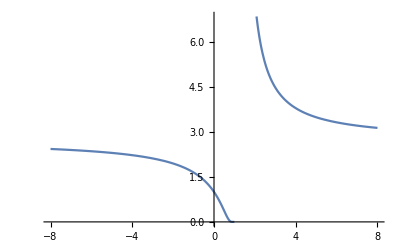

```mathematica
Plot[ⅇ^(x/(-1+x)),{x,-8,8}]
```

```mathematica
Table[(1-a^i)x+a^i x^2, {i, 0, 10}]
```

{x^2,(1-a) x+a x^2,(1-a^2) x+a^2 x^2,(1-a^3) x+a^3 x^2,(1-a^4) x+a^4 x^2,(1-a^5) x+a^5 x^2,(1-a^6) x+a^6 x^2,(1-a^7) x+a^7 x^2,(1-a^8) x+a^8 x^2,(1-a^9) x+a^9 x^2,(1-a^10) x+a^10 x^2}

```mathematica
Manipulate[
Plot[
{(1-a) x+a x^2,(1-a^2) x+a^2 x^2,(1-a^3) x+a^3 x^2,(1-a^4) x+a^4 x^2,(1-a^5) x+a^5 x^2,(1-a^6) x+a^6 x^2,(1-a^7) x+a^7 x^2,(1-a^8) x+a^8 x^2,(1-a^9) x+a^9 x^2,(1-a^10) x+a^10 x^2}, 
{x, 0, 1}, PlotLegends->"Expressions"]
,{a, 0, 1}]
```

```mathematica
Table[(1-a^i)x+a^i x^i, {i, 0, 10}]
```

{1,(1-a) x+a x,(1-a^2) x+a^2 x^2,(1-a^3) x+a^3 x^3,(1-a^4) x+a^4 x^4,(1-a^5) x+a^5 x^5,(1-a^6) x+a^6 x^6,(1-a^7) x+a^7 x^7,(1-a^8) x+a^8 x^8,(1-a^9) x+a^9 x^9,(1-a^10) x+a^10 x^10}

```mathematica
Manipulate[
Plot[
{1,(1-a) x+a x,(1-a^2) x+a^2 x^2,(1-a^3) x+a^3 x^3,(1-a^4) x+a^4 x^4,(1-a^5) x+a^5 x^5,(1-a^6) x+a^6 x^6,(1-a^7) x+a^7 x^7,(1-a^8) x+a^8 x^8,(1-a^9) x+a^9 x^9,(1-a^10) x+a^10 x^10}, 
{x, 0, 1}, PlotLegends->"Expressions"]
,{a, 0, 1}]
```

```mathematica
x^1*x^1
```

x^2

```mathematica
(x^2)^2
```

x^4

```mathematica
Table[x^i, {i, 0, 10}]
```

{1,x,x^2,x^3,x^4,x^5,x^6,x^7,x^8,x^9,x^10}

```mathematica
Length[{1,x,x^2,x^3,x^4,x^5,x^6,x^7,x^8,x^9,x^10}]
```

11

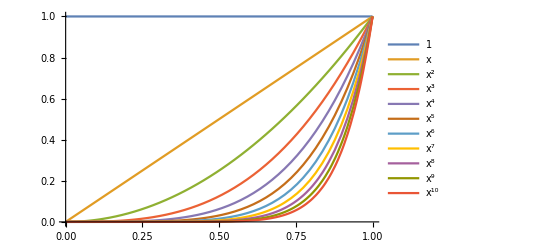

```mathematica
Plot[
{1,x,x^2,x^3,x^4,x^5,x^6,x^7,x^8,x^9,x^10},
{x, 0, 1}, PlotLegends->"Expressions"]
```

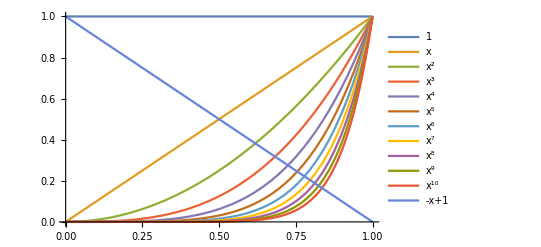

```mathematica
Plot[
{1,x,x^2,x^3,x^4,x^5,x^6,x^7,x^8,x^9,x^10,-x+1},
{x, 0, 1}, PlotLegends->"Expressions"]
```

```mathematica
Manipulate[
Plot[
x^a,{x, 0, 1}],
{a, -10, 10, 1}]
```

```mathematica
Exp[(2x)/(2(x-1))]
```

ⅇ^(x/(-1+x))

```mathematica
Plot[ⅇ^(x/(-1+x)),{x,-8,8}]
```

-Graphics-

```mathematica
Table[x^i, {i, 0, 50}]
```

{1,x,x^2,x^3,x^4,x^5,x^6,x^7,x^8,x^9,x^10,x^11,x^12,x^13,x^14,x^15,x^16,x^17,x^18,x^19,x^20,x^21,x^22,x^23,x^24,x^25,x^26,x^27,x^28,x^29,x^30,x^31,x^32,x^33,x^34,x^35,x^36,x^37,x^38,x^39,x^40,x^41,x^42,x^43,x^44,x^45,x^46,x^47,x^48,x^49,x^50}

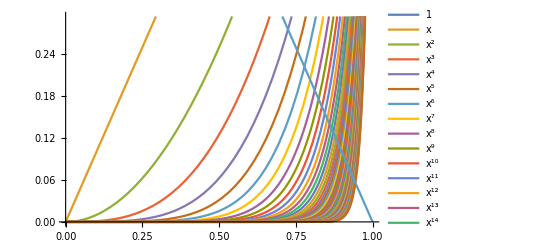

```mathematica
Plot[
{1,x,x^2,x^3,x^4,x^5,x^6,x^7,x^8,x^9,x^10,x^11,x^12,x^13,x^14,x^15,x^16,x^17,x^18,x^19,x^20,x^21,x^22,x^23,x^24,x^25,x^26,x^27,x^28,x^29,x^30,x^31,x^32,x^33,x^34,x^35,x^36,x^37,x^38,x^39,x^40,x^41,x^42,x^43,x^44,x^45,x^46,x^47,x^48,x^49,x^50,1-x},
{x, 0, 1}, PlotLegends->"Expressions"]
```

```mathematica
Reduce[1-x==x^2&&x>0&&x<1,x,Reals]
```

x==1/2 (-1+√5)

```mathematica
Reduce[x==x^2,x,Reals]
```

```mathematica
Table[
i->Reduce[1-x==x^i&&x>0&&x<1,x,Reals], {i, 1, 20}]
```

{1→x==1/2,2→x==1/2 (-1+√5),3→x==Root[-1+#1+#1^3&,1],4→x==Root[-1+#1+#1^4&,2],5→x==Root[-1+#1^2+#1^3&,1],6→x==Root[-1+#1+#1^6&,2],7→x==Root[-1+#1+#1^7&,1],8→x==Root[-1+#1+#1^8&,2],9→x==Root[-1+#1+#1^9&,1],10→x==Root[-1+#1+#1^10&,2],11→x==Root[-1+#1^2+#1^3-#1^5-#1^6+#1^8+#1^9&,1],12→x==Root[-1+#1+#1^12&,2],13→x==Root[-1+#1+#1^13&,1],14→x==Root[-1+#1+#1^14&,2],15→x==Root[-1+#1+#1^15&,1],16→x==Root[-1+#1+#1^16&,2],17→x==Root[-1+#1^2+#1^3-#1^5-#1^6+#1^8+#1^9-#1^11-#1^12+#1^14+#1^15&,1],18→x==Root[-1+#1+#1^18&,2],19→x==Root[-1+#1+#1^19&,1],20→x==Root[-1+#1+#1^20&,2]}

```mathematica
Reduce[1-x==x^3&&x>0&&x<1,x,Reals]
```

x==Root[-1+#1+#1^3&,1]

```mathematica
x^3-x
```

-x+x^3

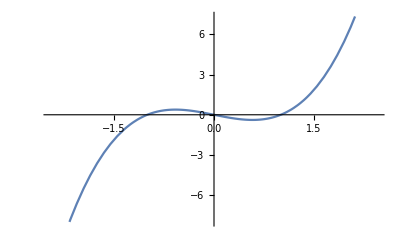

```mathematica
Plot[-x+x^3,{x,-2.449489742783178,2.449489742783178}]
```

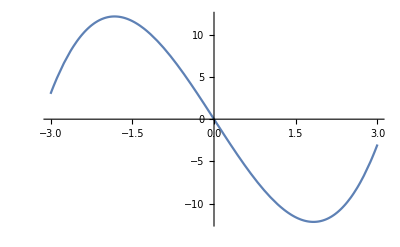

```mathematica
Plot[-10x+x^3,{x,-3, 3}]
```

```mathematica
Reduce[1-x==x^3,x,Reals]
```

x==Root[-1+#1+#1^3&,1]

```mathematica
Root[-1+#1+#1^3&,1]
```

Root[-1+#1+#1^3&,1]

```mathematica
Solve[1-x==x^3, x]
```

{{x→-(2/(3 (9+√93)))^(1/3)+(1/2 (9+√93))^(1/3)/3^(2/3)},{x→-((1+ⅈ √3) (1/2 (9+√93))^(1/3))/(2 3^(2/3))+(1-ⅈ √3)/(2^(2/3) (3 (9+√93))^(1/3))},{x→-((1-ⅈ √3) (1/2 (9+√93))^(1/3))/(2 3^(2/3))+(1+ⅈ √3)/(2^(2/3) (3 (9+√93))^(1/3))}}

```mathematica
FullSimplify[
Solve[1-x==x^3, x], Element[x,Reals]]
```

{{x→Root[-1+#1+#1^3&,1]},{x→Root[-1+#1+#1^3&,2]},{x→Root[-1+#1+#1^3&,3]}}

```mathematica
Table[
D[x^i,x]/-1, {i, 1, 20}]
```

{-1,-2 x,-3 x^2,-4 x^3,-5 x^4,-6 x^5,-7 x^6,-8 x^7,-9 x^8,-10 x^9,-11 x^10,-12 x^11,-13 x^12,-14 x^13,-15 x^14,-16 x^15,-17 x^16,-18 x^17,-19 x^18,-20 x^19}

```mathematica
D[Table[x^i, {i, 0, 50}],x]
```

{0,1,2 x,3 x^2,4 x^3,5 x^4,6 x^5,7 x^6,8 x^7,9 x^8,10 x^9,11 x^10,12 x^11,13 x^12,14 x^13,15 x^14,16 x^15,17 x^16,18 x^17,19 x^18,20 x^19,21 x^20,22 x^21,23 x^22,24 x^23,25 x^24,26 x^25,27 x^26,28 x^27,29 x^28,30 x^29,31 x^30,32 x^31,33 x^32,34 x^33,35 x^34,36 x^35,37 x^36,38 x^37,39 x^38,40 x^39,41 x^40,42 x^41,43 x^42,44 x^43,45 x^44,46 x^45,47 x^46,48 x^47,49 x^48,50 x^49}

```mathematica
1-x==x^2
```

1-x==x^2

```mathematica
Solve[1-x==x^2,{x}]
```

{{x→1/2 (-1-√5)},{x→1/2 (-1+√5)}}

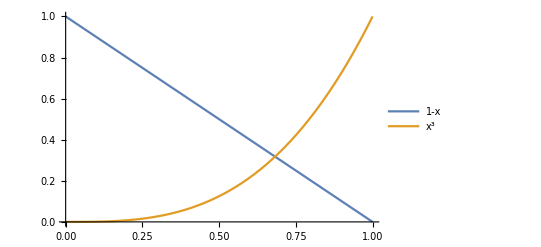

```mathematica
Plot[{1-x,x^3},{x,0,1}, PlotLegends->"Expressions"]
```

```mathematica
(.7)^3
```

0.343

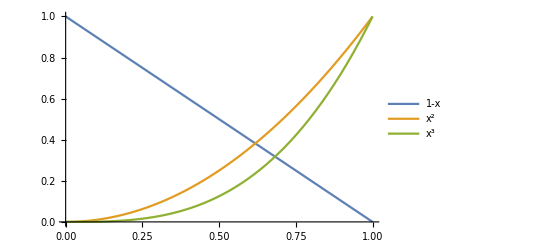

```mathematica
Plot[{1-x,x^2,x^3},{x,0,1}, 
PlotLegends->"Expressions"]
```

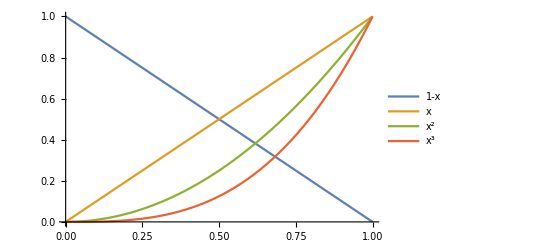

```mathematica
Plot[{1-x,x,x^2,x^3},{x,0,1}, 
PlotLegends->"Expressions"]
```

```mathematica
1-x==x
```

1-x==x

```mathematica
FindRoot[1-x==x,{{x,1}}]
```

{x→0.5}

```mathematica
FindRoot[1-x==x^2, {{x, .6}}]
```

{x→0.618034}

```mathematica
Solve[1-x==x^2,x]
```

{{x→1/2 (-1-√5)},{x→1/2 (-1+√5)}}

```mathematica
Solve[1-x==x^3,x]
```

{{x→-(2/(3 (9+√93)))^(1/3)+(1/2 (9+√93))^(1/3)/3^(2/3)},{x→-((1+ⅈ √3) (1/2 (9+√93))^(1/3))/(2 3^(2/3))+(1-ⅈ √3)/(2^(2/3) (3 (9+√93))^(1/3))},{x→-((1-ⅈ √3) (1/2 (9+√93))^(1/3))/(2 3^(2/3))+(1+ⅈ √3)/(2^(2/3) (3 (9+√93))^(1/3))}}

```mathematica
N[-(2/(3 (9+√93)))^(1/3)+(1/2 (9+√93))^(1/3)/3^(2/3)]
```

0.682328

```mathematica
√(((-(2/(3 (9+√93)))^(1/3)+(1/2 (9+√93))^(1/3)/3^(2/3))-(1/2 (-1+√5)))^2+
(((-(2/(3 (9+√93)))^(1/3)+(1/2 (9+√93))^(1/3)/3^(2/3)))^3+((1/2 (-1+√5)))^2)^2)
```

√((1/2 (1-√5)-(2/(3 (9+√93)))^(1/3)+(1/2 (9+√93))^(1/3)/3^(2/3))^2+(1/4 (-1+√5)^2+(-(2/(3 (9+√93)))^(1/3)+(1/2 (9+√93))^(1/3)/3^(2/3))^3)^2)

```mathematica
N[√((1/2 (1-√5)-(2/(3 (9+√93)))^(1/3)+(1/2 (9+√93))^(1/3)/3^(2/3))^2+(1/4 (-1+√5)^2+(-(2/(3 (9+√93)))^(1/3)+(1/2 (9+√93))^(1/3)/3^(2/3))^3)^2)]
```

0.702586

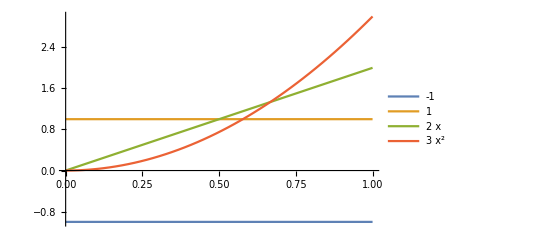

```mathematica
Plot[{-1,1,2x,3 x^2},{x,0,1}, 
PlotLegends->"Expressions"]
```

```mathematica
-1/(-f'[x])
```

1/f'[x]

```mathematica
InverseFunction[Function[{x},1/f'[x]]][x]
```

InverseFunction[Function[{x},1/f'[x]]][x]

```mathematica
With[{f=#^2&},
InverseFunction[Function[{x},1/f'[x]]][x]]
```

1/(2 x)

```mathematica
-1/f'[x]
```

-1/f'[x]

```mathematica
Denominator[-1/f'[x]]
```

f'[x]

```mathematica
Numerator[-1/f'[x]]
```

-1

```mathematica
Table[D[x^i,x],{i, 1, 10}]
```

{1,2 x,3 x^2,4 x^3,5 x^4,6 x^5,7 x^6,8 x^7,9 x^8,10 x^9}

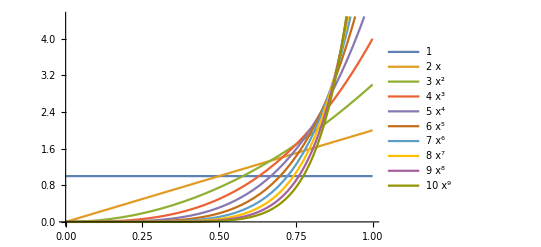

```mathematica
Plot[
{1,2 x,3 x^2,4 x^3,5 x^4,6 x^5,7 x^6,8 x^7,9 x^8,10 x^9}, {x, 0, 1}, PlotLegends->"Expressions"]
```

```mathematica
LaplaceTransform[f[t],t,s]
```

LaplaceTransform[f[t],t,s]

```mathematica
Graphics3D[Sphere[]]
```

-Graphics3D-

```mathematica
Graphics3D[Cuboid[]]
```

-Graphics3D-

```mathematica
Graphics3D[Cylinder[]]
```

-Graphics3D-

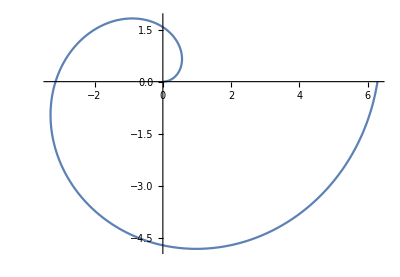

```mathematica
PolarPlot[θ, {θ, 0, 2π}]
```

```mathematica
a[n]==a[n-1] a[n-2]
```

a[n]==a[-2+n] a[-1+n]

```mathematica
Reduce[a[n]==a[-2+n] a[-1+n]]
```

(a[n]==0&&a[-1+n]==0)||(a[-1+n]≠0&&a[-2+n]==a[n]/a[-1+n])

```mathematica
FindInstance[a[n]==a[-2+n] a[-1+n],{n}]
```

FindInstance::nsmet: The methods available to FindInstance are insufficient to find the requested instances or prove they do not exist.

FindInstance[a[n]==a[-2+n] a[-1+n],{n}]

```mathematica
RSolve[{a[n]==a[-2+n] a[-1+n], a[1]==1}, a[n], n]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{a[n]→ⅇ^(C[1] Fibonacci[n]-C[1] LucasL[n])}}

```mathematica
LucasL[4]
```

7

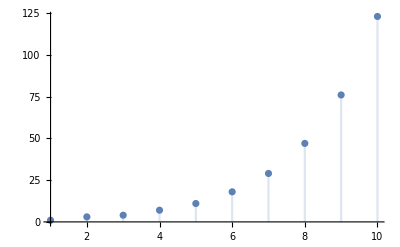

```mathematica
DiscretePlot[LucasL[n], {n, 1, 10}]
```

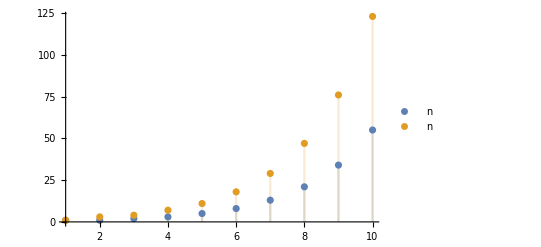

```mathematica
DiscretePlot[{Fibonacci[n], LucasL[n]}, {n, 1, 10}, PlotLegends->"Expressions"]
```

```mathematica
ⅇ^(Fibonacci[n]-LucasL[n])
```

ⅇ^(Fibonacci[n]-LucasL[n])

General::munfl: Exp[-754.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1220.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1974.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

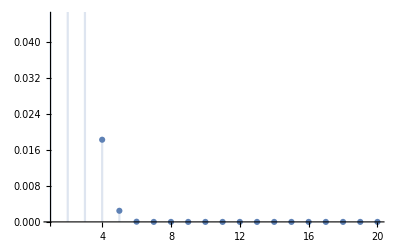

```mathematica
DiscretePlot[ⅇ^(Fibonacci[n]-LucasL[n]),{n,1,20}]
```

```mathematica
FunctionExpand[ⅇ^(Fibonacci[n]-LucasL[n])]
```

ⅇ^(-(1/2 (1+√5))^n-(2/(1+√5))^n Cos[n π]+((1/2 (1+√5))^n-(2/(1+√5))^n Cos[n π])/(√5))

```mathematica
FullSimplify[ⅇ^(-(1/2 (1+√5))^n-(2/(1+√5))^n Cos[n π]+((1/2 (1+√5))^n-(2/(1+√5))^n Cos[n π])/(√5))]
```

ⅇ^(1/5 ((-5+√5) (1/2 (1+√5))^n-(2/(1+√5))^n (5+√5) Cos[n π]))

```mathematica
TrigReduce[ⅇ^(1/5 ((-5+√5) (1/2 (1+√5))^n-(2/(1+√5))^n (5+√5) Cos[n π]))]
```

ⅇ^(1/5 (-5+√5) (1/2 (1+√5))^n-1/5 (2/(1+√5))^n (5+√5) Cos[n π])

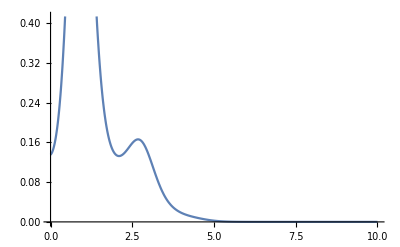

```mathematica
Plot[ⅇ^(1/5 (-5+√5) (1/2 (1+√5))^n-1/5 (2/(1+√5))^n (5+√5) Cos[n π]), {n, 0, 10}]
```

```mathematica
Norm@{x,f[x]}
```

√(Abs[x]^2+Abs[f[x]]^2)

```mathematica
FullSimplify[
Norm@{x,f[x]}, Element[x|f[x],Reals]]
```

√(x^2+f[x]^2)

```mathematica
With[{f=#^2&},√(x^2+f[x]^2)]
```

√(x^2+x^4)

```mathematica
Together[√(x^2+x^4)]
```

√(x^2 (1+x^2))

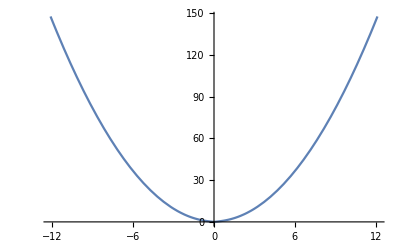

```mathematica
Plot[√(x^2 (1+x^2)),{x,-12.133333333333333,12.133333333333333}]
```

```mathematica
√(x^2+1)
```

√(1+x^2)

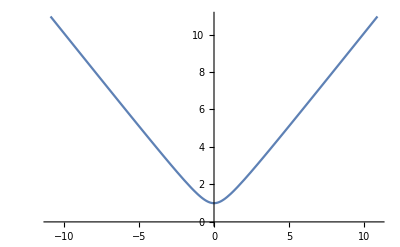

```mathematica
Plot[√(1+x^2),{x,-10.92,10.92}]
```

```mathematica
Manipulate[
Plot[√(a+x^2),{x,-1,1}],
{{a, 1}, 0, 1}]
```

```mathematica
D[√(x^2+1),x]
```

x/(√(1+x^2))

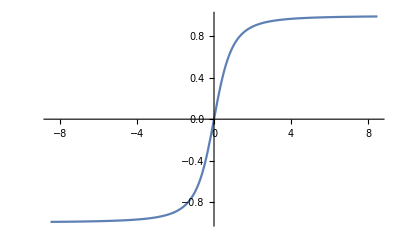

```mathematica
Plot[x/(√(1+x^2)),{x,-8.493333333333334,8.493333333333334}]
```

```mathematica
CDF[NormalDistribution[],x]
```

1/2 Erfc[-x/(√2)]

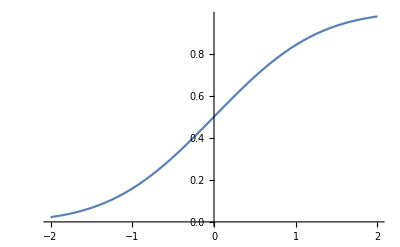

```mathematica
Plot[1/2 Erfc[-x/(√2)],{x,-2,2}]
```

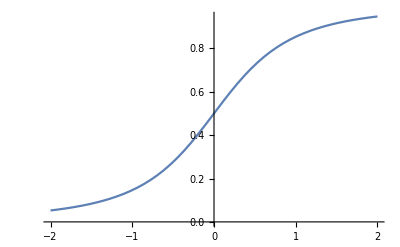

```mathematica
Plot[(1+x/(√(1+x^2)))/2,{x,-2,2}]
```

```mathematica
IdentityMatrix[3]
```

{{1,0,0},{0,1,0},{0,0,1}}

```mathematica
Det[{{1,0,0},{0,1,0},{0,0,1}}]
```

1

```mathematica
TraditionalForm@IdentityMatrix[3]
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
FullSimplify[
Normalize[D[{x, (1+x/(√(1+x^2)))/2}, x]].
Normalize[D[{x, 1/2 Erfc[-x/(√2)]}, x]], Element[x, Reals]]
```

(1+2 ⅇ^(x^2/2) √(2 π) (1+x^2)^(3/2))/(√((1+2 ⅇ^(x^2) π) (5+4 x^2 (3+3 x^2+x^4))))

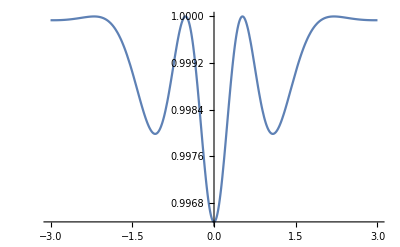

```mathematica
Plot[(1+2 ⅇ^(x^2/2) √(2 π) (1+x^2)^(3/2))/(√((1+2 ⅇ^(x^2) π) (5+4 x^2 (3+3 x^2+x^4)))),{x,-3,3}]
```

```mathematica
Limit[1/Log[Cos[x]]+2/Sin[x]^2,x->0]
```

1

```mathematica
1/Log[Cos[x]]+2/Sin[x]^2
```

2 Csc[x]^2+1/Log[Cos[x]]

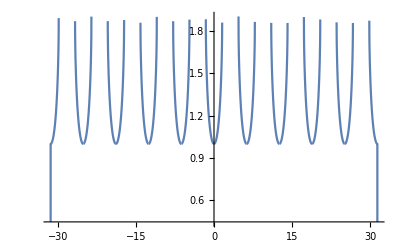

```mathematica
Plot[2 Csc[x]^2+1/Log[Cos[x]],{x,-10 π,10 π}]
```

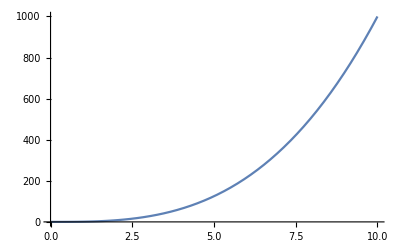

```mathematica
Plot[x^3,{x, 0, 10}]
```

```mathematica
Plot[
{1,x,x^2,x^3,x^4,x^5,x^6,x^7,x^8,x^9,x^10,x^11,x^12,x^13,x^14,x^15,x^16,x^17,x^18,x^19,x^20,x^21,x^22,x^23,x^24,x^25,x^26,x^27,x^28,x^29,x^30,x^31,x^32,x^33,x^34,x^35,x^36,x^37,x^38,x^39,x^40,x^41,x^42,x^43,x^44,x^45,x^46,x^47,x^48,x^49,x^50,1-x},
{x, 0, 1}, PlotLegends->"Expressions"]
```

-Graphics-

```mathematica
x^2==1-x
```

x^2==1-x

```mathematica
Solve[x^2==1-x,{x}]
```

{{x→1/2 (-1-√5)},{x→1/2 (-1+√5)}}

```mathematica
Solve[x^3==1-x,{x}]
```

{{x→-(2/(3 (9+√93)))^(1/3)+(1/2 (9+√93))^(1/3)/3^(2/3)},{x→-((1+ⅈ √3) (1/2 (9+√93))^(1/3))/(2 3^(2/3))+(1-ⅈ √3)/(2^(2/3) (3 (9+√93))^(1/3))},{x→-((1-ⅈ √3) (1/2 (9+√93))^(1/3))/(2 3^(2/3))+(1+ⅈ √3)/(2^(2/3) (3 (9+√93))^(1/3))}}

```mathematica
N[-(2/(3 (9+√93)))^(1/3)+(1/2 (9+√93))^(1/3)/3^(2/3)]
```

0.682328

```mathematica
Solve[x^4==1-x,{x}]
```

{{x→1/2 √(-4 (2/(3 (9+√849)))^(1/3)+(1/2 (9+√849))^(1/3)/3^(2/3))-1/2 √(4 (2/(3 (9+√849)))^(1/3)-(1/2 (9+√849))^(1/3)/3^(2/3)-2/(√(-4 (2/(3 (9+√849)))^(1/3)+(1/2 (9+√849))^(1/3)/3^(2/3))))},{x→1/2 √(-4 (2/(3 (9+√849)))^(1/3)+(1/2 (9+√849))^(1/3)/3^(2/3))+1/2 √(4 (2/(3 (9+√849)))^(1/3)-(1/2 (9+√849))^(1/3)/3^(2/3)-2/(√(-4 (2/(3 (9+√849)))^(1/3)+(1/2 (9+√849))^(1/3)/3^(2/3))))},{x→-1/2 √(-4 (2/(3 (9+√849)))^(1/3)+(1/2 (9+√849))^(1/3)/3^(2/3))-1/2 √(4 (2/(3 (9+√849)))^(1/3)-(1/2 (9+√849))^(1/3)/3^(2/3)+2/(√(-4 (2/(3 (9+√849)))^(1/3)+(1/2 (9+√849))^(1/3)/3^(2/3))))},{x→-1/2 √(-4 (2/(3 (9+√849)))^(1/3)+(1/2 (9+√849))^(1/3)/3^(2/3))+1/2 √(4 (2/(3 (9+√849)))^(1/3)-(1/2 (9+√849))^(1/3)/3^(2/3)+2/(√(-4 (2/(3 (9+√849)))^(1/3)+(1/2 (9+√849))^(1/3)/3^(2/3))))}}

```mathematica
3(-(2/(3 (9+√93)))^(1/3)+(1/2 (9+√93))^(1/3)/3^(2/3))^2
```

3 (-(2/(3 (9+√93)))^(1/3)+(1/2 (9+√93))^(1/3)/3^(2/3))^2

```mathematica
N[3 (-(2/(3 (9+√93)))^(1/3)+(1/2 (9+√93))^(1/3)/3^(2/3))^2]
```

1.39671

```mathematica
∑_(i=1)^333 3^i
```

1141482034698089714580638800897549171091844534558116797675515055553687447158959299419566218474067783836903027356424928015002750653953849797680319305786191860283

```mathematica
∑_(i=1)^200 5^i
```

77787690973264271339300800672251553007378152109014589163763957684871235425442293014799310289071420211962082369439031026558950543403625488280

```mathematica
1000/15
```

200/3

```mathematica
N[200/3]
```

66.6667

```mathematica
(∑_(i=1)^200 5^i+∑_(i=1)^333 3^i)/(∑_(i=1)^66 15^i)
```

16543217894175213255919224519866861484509352684498092038882510255981188932213380537745470346369711258720323733992700698941519319179606968467235794915794454327/6503351536938124200002599162578154262853368728906954054775653603654470502960

```mathematica
3∑_(i=1)^333 i
```

166833

```mathematica
3∑_(i=1)^333 i
```

```mathematica
(5∑_(i=1)^199 i+3∑_(i=1)^333 i)/(15∑_(i=1)^66 i)
```

266333/33165

```mathematica
N[266333/33165]
```

8.03054

```mathematica
N[8101/1005]
```

8.0607

```mathematica
5∑_(i=1)^199 i+3∑_(i=1)^333 i-15∑_(i=1)^66 i
```

233168

```mathematica
Table[If[EvenQ[i],Style[i, Red],Style[i,Blue]], {i, 1, 10}]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Table[With[{a=Fibonacci[i]},
i->If[EvenQ[a],Style[a, Blue],Style[a,Red]]], {i, 1, 100}]
```

{1→1,2→1,3→2,4→3,5→5,6→8,7→13,8→21,9→34,10→55,11→89,12→144,13→233,14→377,15→610,16→987,17→1597,18→2584,19→4181,20→6765,21→10946,22→17711,23→28657,24→46368,25→75025,26→121393,27→196418,28→317811,29→514229,30→832040,31→1346269,32→2178309,33→3524578,34→5702887,35→9227465,36→14930352,37→24157817,38→39088169,39→63245986,40→102334155,41→165580141,42→267914296,43→433494437,44→701408733,45→1134903170,46→1836311903,47→2971215073,48→4807526976,49→7778742049,50→12586269025,51→20365011074,52→32951280099,53→53316291173,54→86267571272,55→139583862445,56→225851433717,57→365435296162,58→591286729879,59→956722026041,60→1548008755920,61→2504730781961,62→4052739537881,63→6557470319842,64→10610209857723,65→17167680177565,66→27777890035288,67→44945570212853,68→72723460248141,69→117669030460994,70→190392490709135,71→308061521170129,72→498454011879264,73→806515533049393,74→1304969544928657,75→2111485077978050,76→3416454622906707,77→5527939700884757,78→8944394323791464,79→14472334024676221,80→23416728348467685,81→37889062373143906,82→61305790721611591,83→99194853094755497,84→160500643816367088,85→259695496911122585,86→420196140727489673,87→679891637638612258,88→1100087778366101931,89→1779979416004714189,90→2880067194370816120,91→4660046610375530309,92→7540113804746346429,93→12200160415121876738,94→19740274219868223167,95→31940434634990099905,96→51680708854858323072,97→83621143489848422977,98→135301852344706746049,99→218922995834555169026,100→354224848179261915075}

```mathematica
Fibonacci[2]
```

1

```mathematica
∑_(i=1)^n Fibonacci[3 i]
```

1/5 2^(-2-3 n) (-1-√5)^(-3 n) (64^n (5-3 √5)-5 2^(1+3 n) (-1-√5)^(3 n)+(ⅈ (1+√5))^(6 n) (5+3 √5))

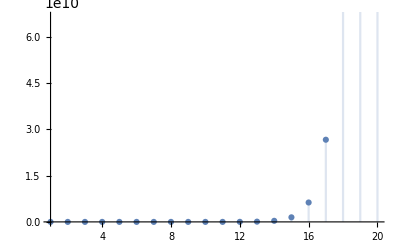

```mathematica
DiscretePlot[1/5 2^(-2-3 n) (-1-√5)^(-3 n) (64^n (5-3 √5)-5 2^(1+3 n) (-1-√5)^(3 n)+(ⅈ (1+√5))^(6 n) (5+3 √5)),{n,1,20}]
```

```mathematica
e[n]==4 e[n-1]+e[n-2]
```

```mathematica
LucasL[1]
```

1

```mathematica
e[n]==4 e[n-1]+e[n-2]
```

e[n]==e[-2+n]+4 e[-1+n]

```mathematica
Solve[e[n]==e[-2+n]+4 e[-1+n]&&n∈Integers,{n}]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[e[n]==e[-2+n]+4 e[-1+n]&&n∈ℤ,{n}]

```mathematica
RSolve[{e[n]==e[-2+n]+4 e[-1+n], e[1]==1}, e[n],n]
```

{{e[n]→1/(2+√5)((2+√5)^n+2 (2-√5)^n C[1]+√5 (2-√5)^n C[1]-2 (2+√5)^n C[1]+√5 (2+√5)^n C[1])}}

```mathematica
1/(2+√5)((2+√5)^n+2 (2-√5)^n C[1]+√5 (2-√5)^n C[1]-2 (2+√5)^n C[1]+√5 (2+√5)^n C[1])
```

((2+√5)^n+2 (2-√5)^n C[1]+√5 (2-√5)^n C[1]-2 (2+√5)^n C[1]+√5 (2+√5)^n C[1])/(2+√5)

```mathematica
FullSimplify[1/(2+√5)((2+√5)^n+2 (2-√5)^n C[1]+√5 (2-√5)^n C[1]-2 (2+√5)^n C[1]+√5 (2+√5)^n C[1])]
```

(-2+√5) ((2-√5)^n (2+√5) C[1]+(2+√5)^n (1+(-2+√5) C[1]))

```mathematica
ZTransform[(-2+√5) ((2-√5)^n (2+√5) C[1]+(2+√5)^n (1+(-2+√5) C[1])),n,z]
```

((-2+√5) z (-2+√5+z-8 √5 C[1]+2 √5 z C[1]))/(-1-4 z+z^2)

```mathematica
FullSimplify[((-2+√5) z (-2+√5+z-8 √5 C[1]+2 √5 z C[1]))/(-1-4 z+z^2)]
```

((-2+√5) z (-2+√5+z-8 √5 C[1]+2 √5 z C[1]))/(-1+(-4+z) z)

```mathematica
#->Fibonacci[#]&/@Range[1, 1000]
```

{1→1,2→1,3→2,4→3,5→5,6→8,7→13,8→21,9→34,10→55,11→89,12→144,13→233,14→377,15→610,16→987,17→1597,18→2584,19→4181,20→6765,21→10946,22→17711,23→28657,24→46368,25→75025,26→121393,27→196418,28→317811,29→514229,30→832040,31→1346269,32→2178309,33→3524578,34→5702887,35→9227465,36→14930352,37→24157817,38→39088169,39→63245986,40→102334155,41→165580141,42→267914296,43→433494437,44→701408733,45→1134903170,46→1836311903,47→2971215073,48→4807526976,49→7778742049,50→12586269025,51→20365011074,52→32951280099,53→53316291173,54→86267571272,55→139583862445,56→225851433717,57→365435296162,58→591286729879,59→956722026041,60→1548008755920,61→2504730781961,62→4052739537881,63→6557470319842,64→10610209857723,65→17167680177565,66→27777890035288,67→44945570212853,68→72723460248141,69→117669030460994,70→190392490709135,71→308061521170129,72→498454011879264,73→806515533049393,74→1304969544928657,75→2111485077978050,76→3416454622906707,77→5527939700884757,78→8944394323791464,79→14472334024676221,80→23416728348467685,81→37889062373143906,82→61305790721611591,83→99194853094755497,84→160500643816367088,85→259695496911122585,86→420196140727489673,87→679891637638612258,88→1100087778366101931,89→1779979416004714189,90→2880067194370816120,91→4660046610375530309,92→7540113804746346429,93→12200160415121876738,94→19740274219868223167,95→31940434634990099905,96→51680708854858323072,97→83621143489848422977,98→135301852344706746049,99→218922995834555169026,100→354224848179261915075,101→573147844013817084101,102→927372692193078999176,103→1500520536206896083277,104→2427893228399975082453,105→3928413764606871165730,106→6356306993006846248183,107→10284720757613717413913,108→16641027750620563662096,109→26925748508234281076009,110→43566776258854844738105,111→70492524767089125814114,112→114059301025943970552219,113→184551825793033096366333,114→298611126818977066918552,115→483162952612010163284885,116→781774079430987230203437,117→1264937032042997393488322,118→2046711111473984623691759,119→3311648143516982017180081,120→5358359254990966640871840,121→8670007398507948658051921,122→14028366653498915298923761,123→22698374052006863956975682,124→36726740705505779255899443,125→59425114757512643212875125,126→96151855463018422468774568,127→155576970220531065681649693,128→251728825683549488150424261,129→407305795904080553832073954,130→659034621587630041982498215,131→1066340417491710595814572169,132→1725375039079340637797070384,133→2791715456571051233611642553,134→4517090495650391871408712937,135→7308805952221443105020355490,136→11825896447871834976429068427,137→19134702400093278081449423917,138→30960598847965113057878492344,139→50095301248058391139327916261,140→81055900096023504197206408605,141→131151201344081895336534324866,142→212207101440105399533740733471,143→343358302784187294870275058337,144→555565404224292694404015791808,145→898923707008479989274290850145,146→1454489111232772683678306641953,147→2353412818241252672952597492098,148→3807901929474025356630904134051,149→6161314747715278029583501626149,150→9969216677189303386214405760200,151→16130531424904581415797907386349,152→26099748102093884802012313146549,153→42230279526998466217810220532898,154→68330027629092351019822533679447,155→110560307156090817237632754212345,156→178890334785183168257455287891792,157→289450641941273985495088042104137,158→468340976726457153752543329995929,159→757791618667731139247631372100066,160→1226132595394188293000174702095995,161→1983924214061919432247806074196061,162→3210056809456107725247980776292056,163→5193981023518027157495786850488117,164→8404037832974134882743767626780173,165→13598018856492162040239554477268290,166→22002056689466296922983322104048463,167→35600075545958458963222876581316753,168→57602132235424755886206198685365216,169→93202207781383214849429075266681969,170→150804340016807970735635273952047185,171→244006547798191185585064349218729154,172→394810887814999156320699623170776339,173→638817435613190341905763972389505493,174→1033628323428189498226463595560281832,175→1672445759041379840132227567949787325,176→2706074082469569338358691163510069157,177→4378519841510949178490918731459856482,178→7084593923980518516849609894969925639,179→11463113765491467695340528626429782121,180→18547707689471986212190138521399707760,181→30010821454963453907530667147829489881,182→48558529144435440119720805669229197641,183→78569350599398894027251472817058687522,184→127127879743834334146972278486287885163,185→205697230343233228174223751303346572685,186→332825110087067562321196029789634457848,187→538522340430300790495419781092981030533,188→871347450517368352816615810882615488381,189→1409869790947669143312035591975596518914,190→2281217241465037496128651402858212007295,191→3691087032412706639440686994833808526209,192→5972304273877744135569338397692020533504,193→9663391306290450775010025392525829059713,194→15635695580168194910579363790217849593217,195→25299086886458645685589389182743678652930,196→40934782466626840596168752972961528246147,197→66233869353085486281758142155705206899077,198→107168651819712326877926895128666735145224,199→173402521172797813159685037284371942044301,200→280571172992510140037611932413038677189525,201→453973694165307953197296969697410619233826,202→734544867157818093234908902110449296423351,203→1188518561323126046432205871807859915657177,204→1923063428480944139667114773918309212080528,205→3111581989804070186099320645726169127737705,206→5034645418285014325766435419644478339818233,207→8146227408089084511865756065370647467555938,208→13180872826374098837632191485015125807374171,209→21327100234463183349497947550385773274930109,210→34507973060837282187130139035400899082304280,211→55835073295300465536628086585786672357234389,212→90343046356137747723758225621187571439538669,213→146178119651438213260386312206974243796773058,214→236521166007575960984144537828161815236311727,215→382699285659014174244530850035136059033084785,216→619220451666590135228675387863297874269396512,217→1001919737325604309473206237898433933302481297,218→1621140188992194444701881625761731807571877809,219→2623059926317798754175087863660165740874359106,220→4244200115309993198876969489421897548446236915,221→6867260041627791953052057353082063289320596021,222→11111460156937785151929026842503960837766832936,223→17978720198565577104981084195586024127087428957,224→29090180355503362256910111038089984964854261893,225→47068900554068939361891195233676009091941690850,226→76159080909572301618801306271765994056795952743,227→123227981463641240980692501505442003148737643593,228→199387062373213542599493807777207997205533596336,229→322615043836854783580186309282650000354271239929,230→522002106210068326179680117059857997559804836265,231→844617150046923109759866426342507997914076076194,232→1366619256256991435939546543402365995473880912459,233→2211236406303914545699412969744873993387956988653,234→3577855662560905981638959513147239988861837901112,235→5789092068864820527338372482892113982249794889765,236→9366947731425726508977331996039353971111632790877,237→15156039800290547036315704478931467953361427680642,238→24522987531716273545293036474970821924473060471519,239→39679027332006820581608740953902289877834488152161,240→64202014863723094126901777428873111802307548623680,241→103881042195729914708510518382775401680142036775841,242→168083057059453008835412295811648513482449585399521,243→271964099255182923543922814194423915162591622175362,244→440047156314635932379335110006072428645041207574883,245→712011255569818855923257924200496343807632829750245,246→1152058411884454788302593034206568772452674037325128,247→1864069667454273644225850958407065116260306867075373,248→3016128079338728432528443992613633888712980904400501,249→4880197746793002076754294951020699004973287771475874,250→7896325826131730509282738943634332893686268675876375,251→12776523572924732586037033894655031898659556447352249,252→20672849399056463095319772838289364792345825123228624,253→33449372971981195681356806732944396691005381570580873,254→54122222371037658776676579571233761483351206693809497,255→87571595343018854458033386304178158174356588264390370,256→141693817714056513234709965875411919657707794958199867,257→229265413057075367692743352179590077832064383222590237,258→370959230771131880927453318055001997489772178180790104,259→600224643828207248620196670234592075321836561403380341,260→971183874599339129547649988289594072811608739584170445,261→1571408518427546378167846658524186148133445300987550786,262→2542592393026885507715496646813780220945054040571721231,263→4114000911454431885883343305337966369078499341559272017,264→6656593304481317393598839952151746590023553382130993248,265→10770594215935749279482183257489712959102052723690265265,266→17427187520417066673081023209641459549125606105821258513,267→28197781736352815952563206467131172508227658829511523778,268→45624969256769882625644229676772632057353264935332782291,269→73822750993122698578207436143903804565580923764844306069,270→119447720249892581203851665820676436622934188700177088360,271→193270471243015279782059101964580241188515112465021394429,272→312718191492907860985910767785256677811449301165198482789,273→505988662735923140767969869749836918999964413630219877218,274→818706854228831001753880637535093596811413714795418360007,275→1324695516964754142521850507284930515811378128425638237225,276→2143402371193585144275731144820024112622791843221056597232,277→3468097888158339286797581652104954628434169971646694834457,278→5611500259351924431073312796924978741056961814867751431689,279→9079598147510263717870894449029933369491131786514446266146,280→14691098406862188148944207245954912110548093601382197697835,281→23770696554372451866815101694984845480039225387896643963981,282→38461794961234640015759308940939757590587318989278841661816,283→62232491515607091882574410635924603070626544377175485625797,284→100694286476841731898333719576864360661213863366454327287613,285→162926777992448823780908130212788963731840407743629812913410,286→263621064469290555679241849789653324393054271110084140201023,287→426547842461739379460149980002442288124894678853713953114433,288→690168906931029935139391829792095612517948949963798093315456,289→1116716749392769314599541809794537900642843628817512046429889,290→1806885656323799249738933639586633513160792578781310139745345,291→2923602405716568564338475449381171413803636207598822186175234,292→4730488062040367814077409088967804926964428786380132325920579,293→7654090467756936378415884538348976340768064993978954512095813,294→12384578529797304192493293627316781267732493780359086838016392,295→20038668997554240570909178165665757608500558774338041350112205,296→32423247527351544763402471792982538876233052554697128188128597,297→52461916524905785334311649958648296484733611329035169538240802,298→84885164052257330097714121751630835360966663883732297726369399,299→137347080577163115432025771710279131845700275212767467264610201,300→222232244629420445529739893461909967206666939096499764990979600,301→359579325206583560961765665172189099052367214309267232255589801,302→581811569836004006491505558634099066259034153405766997246569401,303→941390895042587567453271223806288165311401367715034229502159202,304→1523202464878591573944776782440387231570435521120801226748728603,305→2464593359921179141398048006246675396881836888835835456250887805,306→3987795824799770715342824788687062628452272409956636682999616408,307→6452389184720949856740872794933738025334109298792472139250504213,308→10440185009520720572083697583620800653786381708749108822250120621,309→16892574194241670428824570378554538679120491007541580961500624834,310→27332759203762391000908267962175339332906872716290689783750745455,311→44225333398004061429732838340729878012027363723832270745251370289,312→71558092601766452430641106302905217344934236440122960529002115744,313→115783425999770513860373944643635095356961600163955231274253486033,314→187341518601536966291015050946540312701895836604078191803255601777,315→303124944601307480151388995590175408058857436768033423077509087810,316→490466463202844446442404046536715720760753273372111614880764689587,317→793591407804151926593793042126891128819610710140145037958273777397,318→1284057871006996373036197088663606849580363983512256652839038466984,319→2077649278811148299629990130790497978399974693652401690797312244381,320→3361707149818144672666187219454104827980338677164658343636350711365,321→5439356428629292972296177350244602806380313370817060034433662955746,322→8801063578447437644962364569698707634360652047981718378070013667111,323→14240420007076730617258541919943310440740965418798778412503676622857,324→23041483585524168262220906489642018075101617466780496790573690289968,325→37281903592600898879479448409585328515842582885579275203077366912825,326→60323387178125067141700354899227346590944200352359771993651057202793,327→97605290770725966021179803308812675106786783237939047196728424115618,328→157928677948851033162880158208040021697730983590298819190379481318411,329→255533968719576999184059961516852696804517766828237866387107905434029,330→413462646668428032346940119724892718502248750418536685577487386752440,331→668996615388005031531000081241745415306766517246774551964595292186469,332→1082459262056433063877940200966638133809015267665311237542082678938909,333→1751455877444438095408940282208383549115781784912085789506677971125378,334→2833915139500871159286880483175021682924797052577397027048760650064287,335→4585371016945309254695820765383405232040578837489482816555438621189665,336→7419286156446180413982701248558426914965375890066879843604199271253952,337→12004657173391489668678522013941832147005954727556362660159637892443617,338→19423943329837670082661223262500259061971330617623242503763837163697569,339→31428600503229159751339745276442091208977285345179605163923475056141186,340→50852543833066829834000968538942350270948615962802847667687312219838755,341→82281144336295989585340713815384441479925901307982452831610787275979941,342→133133688169362819419341682354326791750874517270785300499298099495818696,343→215414832505658809004682396169711233230800418578767753330908886771798637,344→348548520675021628424024078524038024981674935849553053830206986267617333,345→563963353180680437428706474693749258212475354428320807161115873039415970,346→912511873855702065852730553217787283194150290277873860991322859307033303,347→1476475227036382503281437027911536541406625644706194668152438732346449273,348→2388987100892084569134167581129323824600775934984068529143761591653482576,349→3865462327928467072415604609040860366007401579690263197296200323999931849,350→6254449428820551641549772190170184190608177514674331726439961915653414425,351→10119911756749018713965376799211044556615579094364594923736162239653346274,352→16374361185569570355515148989381228747223756609038926650176124155306760699,353→26494272942318589069480525788592273303839335703403521573912286394960106973,354→42868634127888159424995674777973502051063092312442448224088410550266867672,355→69362907070206748494476200566565775354902428015845969798000696945226974645,356→112231541198094907919471875344539277405965520328288418022089107495493842317,357→181594448268301656413948075911105052760867948344134387820089804440720816962,358→293825989466396564333419951255644330166833468672422805842178911936214659279,359→475420437734698220747368027166749382927701417016557193662268716376935476241,360→769246427201094785080787978422393713094534885688979999504447628313150135520,361→1244666864935793005828156005589143096022236302705537193166716344690085611761,362→2013913292136887790908943984011536809116771188394517192671163973003235747281,363→3258580157072680796737099989600679905139007491100054385837880317693321359042,364→5272493449209568587646043973612216714255778679494571578509044290696557106323,365→8531073606282249384383143963212896619394786170594625964346924608389878465365,366→13803567055491817972029187936825113333650564850089197542855968899086435571688,367→22334640661774067356412331900038009953045351020683823507202893507476314037053,368→36138207717265885328441519836863123286695915870773021050058862406562749608741,369→58472848379039952684853851736901133239741266891456844557261755914039063645794,370→94611056096305838013295371573764256526437182762229865607320618320601813254535,371→153083904475345790698149223310665389766178449653686710164582374234640876900329,372→247694960571651628711444594884429646292615632415916575771902992555242690154864,373→400778865046997419409593818195095036058794082069603285936485366789883567055193,374→648473825618649048121038413079524682351409714485519861708388359345126257210057,375→1049252690665646467530632231274619718410203796555123147644873726135009824265250,376→1697726516284295515651670644354144400761613511040643009353262085480136081475307,377→2746979206949941983182302875628764119171817307595766156998135811615145905740557,378→4444705723234237498833973519982908519933430818636409166351397897095281987215864,379→7191684930184179482016276395611672639105248126232175323349533708710427892956421,380→11636390653418416980850249915594581159038678944868584489700931605805709880172285,381→18828075583602596462866526311206253798143927071100759813050465314516137773128706,382→30464466237021013443716776226800834957182606015969344302751396920321847653300991,383→49292541820623609906583302538007088755326533087070104115801862234837985426429697,384→79757008057644623350300078764807923712509139103039448418553259155159833079730688,385→129049549878268233256883381302815012467835672190109552534355121389997818506160385,386→208806557935912856607183460067622936180344811293149000952908380545157651585891073,387→337856107814181089864066841370437948648180483483258553487263501935155470092051458,388→546662665750093946471250301438060884828525294776407554440171882480313121677942531,389→884518773564275036335317142808498833476705778259666107927435384415468591769993989,390→1431181439314368982806567444246559718305231073036073662367607266895781713447936520,391→2315700212878644019141884587055058551781936851295739770295042651311250305217930509,392→3746881652193013001948452031301618270087167924331813432662649918207032018665867029,393→6062581865071657021090336618356676821869104775627553202957692569518282323883797538,394→9809463517264670023038788649658295091956272699959366635620342487725314342549664567,395→15872045382336327044129125268014971913825377475586919838578035057243596666433462105,396→25681508899600997067167913917673267005781650175546286474198377544968911008983126672,397→41553554281937324111297039185688238919607027651133206312776412602212507675416588777,398→67235063181538321178464953103361505925388677826679492786974790147181418684399715449,399→108788617463475645289761992289049744844995705477812699099751202749393926359816304226,400→176023680645013966468226945392411250770384383304492191886725992896575345044216019675,401→284812298108489611757988937681460995615380088782304890986477195645969271404032323901,402→460835978753503578226215883073872246385764472086797082873203188542544616448248343576,403→745648276861993189984204820755333242001144560869101973859680384188513887852280667477,404→1206484255615496768210420703829205488386909032955899056732883572731058504300529011053,405→1952132532477489958194625524584538730388053593825001030592563956919572392152809678530,406→3158616788092986726405046228413744218774962626780900087325447529650630896453338689583,407→5110749320570476684599671752998282949163016220605901117918011486570203288606148368113,408→8269366108663463411004717981412027167937978847386801205243459016220834185059487057696,409→13380115429233940095604389734410310117100995067992702323161470502791037473665635425809,410→21649481537897403506609107715822337285038973915379503528404929519011871658725122483505,411→35029596967131343602213497450232647402139968983372205851566400021802909132390757909314,412→56679078505028747108822605166054984687178942898751709379971329540814780791115880392819,413→91708675472160090711036102616287632089318911882123915231537729562617689923506638302133,414→148387753977188837819858707782342616776497854780875624611509059103432470714622518694952,415→240096429449348928530894810398630248865816766662999539843046788666050160638129156997085,416→388484183426537766350753518180972865642314621443875164454555847769482631352751675692037,417→628580612875886694881648328579603114508131388106874704297602636435532791990880832689122,418→1017064796302424461232401846760575980150446009550749868752158484205015423343632508381159,419→1645645409178311156114050175340179094658577397657624573049761120640548215334513341070281,420→2662710205480735617346452022100755074809023407208374441801919604845563638678145849451440,421→4308355614659046773460502197440934169467600804865999014851680725486111854012659190521721,422→6971065820139782390806954219541689244276624212074373456653600330331675492690805039973161,423→11279421434798829164267456416982623413744225016940372471505281055817787346703464230494882,424→18250487254938611555074410636524312658020849229014745928158881386149462839394269270468043,425→29529908689737440719341867053506936071765074245955118399664162441967250186097733500962925,426→47780395944676052274416277690031248729785923474969864327823043828116713025492002771430968,427→77310304634413492993758144743538184801550997720924982727487206270083963211589736272393893,428→125090700579089545268174422433569433531336921195894847055310250098200676237081739043824861,429→202401005213503038261932567177107618332887918916819829782797456368284639448671475316218754,430→327491705792592583530106989610677051864224840112714676838107706466485315685753214360043615,431→529892711006095621792039556787784670197112759029534506620905162834769955134424689676262369,432→857384416798688205322146546398461722061337599142249183459012869301255270820177904036305984,433→1387277127804783827114186103186246392258450358171783690079918032136025225954602593712568353,434→2244661544603472032436332649584708114319787957314032873538930901437280496774780497748874337,435→3631938672408255859550518752770954506578238315485816563618848933573305722729383091461442690,436→5876600217011727891986851402355662620898026272799849437157779835010586219504163589210317027,437→9508538889419983751537370155126617127476264588285666000776628768583891942233546680671759717,438→15385139106431711643524221557482279748374290861085515437934408603594478161737710269882076744,439→24893677995851695395061591712608896875850555449371181438711037372178370103971256950553836461,440→40278817102283407038585813270091176624224846310456696876645445975772848265708967220435913205,441→65172495098135102433647404982700073500075401759827878315356483347951218369680224170989749666,442→105451312200418509472233218252791250124300248070284575192001929323724066635389191391425662871,443→170623807298553611905880623235491323624375649830112453507358412671675285005069415562415412537,444→276075119498972121378113841488282573748675897900397028699360341995399351640458606953841075408,445→446698926797525733283994464723773897373051547730509482206718754667074636645528022516256487945,446→722774046296497854662108306212056471121727445630906510906079096662473988285986629470097563353,447→1169472973094023587946102770935830368494778993361415993112797851329548624931514651986354051298,448→1892247019390521442608211077147886839616506438992322504018876947992022613217501281456451614651,449→3061719992484545030554313848083717208111285432353738497131674799321571238149015933442805665949,450→4953967011875066473162524925231604047727791871346061001150551747313593851366517214899257280600,451→8015687004359611503716838773315321255839077303699799498282226546635165089515533148342062946549,452→12969654016234677976879363698546925303566869175045860499432778293948758940882050363241320227149,453→20985341020594289480596202471862246559405946478745659997715004840583924030397583511583383173698,454→33954995036828967457475566170409171862972815653791520497147783134532682971279633874824703400847,455→54940336057423256938071768642271418422378762132537180494862787975116607001677217386408086574545,456→88895331094252224395547334812680590285351577786328700992010571109649289972956851261232789975392,457→143835667151675481333619103454952008707730339918865881486873359084765896974634068647640876549937,458→232730998245927705729166438267632598993081917705194582478883930194415186947590919908873666525329,459→376566665397603187062785541722584607700812257624060463965757289279181083922224988556514543075266,460→609297663643530892791951979990217206693894175329255046444641219473596270869815908465388209600595,461→985864329041134079854737521712801814394706432953315510410398508752777354792040897021902752675861,462→1595161992684664972646689501703019021088600608282570556855039728226373625661856805487290962276456,463→2581026321725799052501427023415820835483307041235886067265438236979150980453897702509193714952317,464→4176188314410464025148116525118839856571907649518456624120477965205524606115754507996484677228773,465→6757214636136263077649543548534660692055214690754342691385916202184675586569652210505678392181090,466→10933402950546727102797660073653500548627122340272799315506394167390200192685406718502163069409863,467→17690617586682990180447203622188161240682337031027142006892310369574875779255058929007841461590953,468→28624020537229717283244863695841661789309459371299941322398704536965075971940465647510004531000816,469→46314638123912707463692067318029823029991796402327083329291014906539951751195524576517845992591769,470→74938658661142424746936931013871484819301255773627024651689719443505027723135990224027850523592585,471→121253296785055132210628998331901307849293052175954107980980734350044979474331514800545696516184354,472→196191955446197556957565929345772792668594307949581132632670453793550007197467505024573547039776939,473→317445252231252689168194927677674100517887360125535240613651188143594986671799019825119243555961293,474→513637207677450246125760857023446893186481668075116373246321641937144993869266524849692790595738232,475→831082459908702935293955784701120993704369028200651613859972830080739980541065544674812034151699525,476→1344719667586153181419716641724567886890850696275767987106294472017884974410332069524504824747437757,477→2175802127494856116713672426425688880595219724476419600966267302098624954951397614199316858899137282,478→3520521795081009298133389068150256767486070420752187588072561774116509929361729683723821683646575039,479→5696323922575865414847061494575945648081290145228607189038829076215134884313127297923138542545712321,480→9216845717656874712980450562726202415567360565980794777111390850331644813674856981646960226192287360,481→14913169640232740127827512057302148063648650711209401966150219926546779697987984279570098768737999681,482→24130015357889614840807962620028350479216011277190196743261610776878424511662841261217058994930287041,483→39043184998122354968635474677330498542864661988399598709411830703425204209650825540787157763668286722,484→63173200356011969809443437297358849022080673265589795452673441480303628721313666802004216758598573763,485→102216385354134324778078911974689347564945335253989394162085272183728832930964492342791374522266860485,486→165389585710146294587522349272048196587026008519579189614758713664032461652278159144795591280865434248,487→267605971064280619365601261246737544151971343773568583776843985847761294583242651487586965803132294733,488→432995556774426913953123610518785740738997352293147773391602699511793756235520810632382557083997728981,489→700601527838707533318724871765523284890968696066716357168446685359555050818763462119969522887130023714,490→1133597084613134447271848482284309025629966048359864130560049384871348807054284272752352079971127752695,491→1834198612451841980590573354049832310520934744426580487728496070230903857873047734872321602858257776409,492→2967795697064976427862421836334141336150900792786444618288545455102252664927332007624673682829385529104,493→4801994309516818408452995190383973646671835537213025106017041525333156522800379742496995285687643305513,494→7769790006581794836315417026718114982822736329999469724305586980435409187727711750121668968517028834617,495→12571784316098613244768412217102088629494571867212494830322628505768565710528091492618664254204672140130,496→20341574322680408081083829243820203612317308197211964554628215486203974898255803242740333222721700974747,497→32913358638779021325852241460922292241811880064424459384950843991972540608783894735358997476926373114877,498→53254932961459429406936070704742495854129188261636423939579059478176515507039697978099330699648074089624,499→86168291600238450732788312165664788095941068326060883324529903470149056115823592713458328176574447204501,500→139423224561697880139724382870407283950070256587697307264108962948325571622863290691557658876222521294125,501→225591516161936330872512695036072072046011324913758190588638866418474627738686883405015987052796968498626,502→365014740723634211012237077906479355996081581501455497852747829366800199361550174096573645929019489792751,503→590606256885570541884749772942551428042092906415213688441386695785274827100237057501589632981816458291377,504→955620997609204752896986850849030784038174487916669186294134525152075026461787231598163278910835948084128,505→1546227254494775294781736623791582212080267394331882874735521220937349853562024289099752911892652406375505,506→2501848252103980047678723474640612996118441882248552061029655746089424880023811520697916190803488354459633,507→4048075506598755342460460098432195208198709276580434935765176967026774733585835809797669102696140760835138,508→6549923758702735390139183573072808204317151158828986996794832713116199613609647330495585293499629115294771,509→10597999265301490732599643671505003412515860435409421932560009680142974347195483140293254396195769876129909,510→17147923024004226122738827244577811616833011594238408929354842393259173960805130470788839689695398991424680,511→27745922289305716855338470916082815029348872029647830861914852073402148308000613611082094085891168867554589,512→44893845313309942978077298160660626646181883623886239791269694466661322268805744081870933775586567858979269,513→72639767602615659833415769076743441675530755653534070653184546540063470576806357692953027861477736726533858,514→117533612915925602811493067237404068321712639277420310444454241006724792845612101774823961637064304585513127,515→190173380518541262644908836314147509997243394930954381097638787546788263422418459467776989498542041312046985,516→307706993434466865456401903551551578318956034208374691542093028553513056268030561242600951135606345897560112,517→497880373953008128101310739865699088316199429139329072639731816100301319690449020710377940634148387209607097,518→805587367387474993557712643417250666635155463347703764181824844653814375958479581952978891769754733107167209,519→1303467741340483121659023383282949754951354892487032836821556660754115695648928602663356832403903120316774306,520→2109055108727958115216736026700200421586510355834736601003381505407930071607408184616335724173657853423941515,521→3412522850068441236875759409983150176537865248321769437824938166162045767256336787279692556577560973740715821,522→5521577958796399352092495436683350598124375604156506038828319671569975838863744971896028280751218827164657336,523→8934100808864840588968254846666500774662240852478275476653257837732021606120081759175720837328779800905373157,524→14455678767661239941060750283349851372786616456634781515481577509301997444983826731071749118079998628070030493,525→23389779576526080530029005130016352147448857309113056992134835347034019051103908490247469955408778428975403650,526→37845458344187320471089755413366203520235473765747838507616412856336016496087735221319219073488777057045434143,527→61235237920713401001118760543382555667684331074860895499751248203370035547191643711566689028897555486020837793,528→99080696264900721472208515956748759187919804840608734007367661059706052043279378932885908102386332543066271936,529→160315934185614122473327276500131314855604135915469629507118909263076087590471022644452597131283888029087109729,530→259396630450514843945535792456880074043523940756078363514486570322782139633750401577338505233670220572153381665,531→419712564636128966418863068957011388899128076671547993021605479585858227224221424221791102364954108601240491394,532→679109195086643810364398861413891462942652017427626356536092049908640366857971825799129607598624329173393873059,533→1098821759722772776783261930370902851841780094099174349557697529494498594082193250020920709963578437774634364453,534→1777930954809416587147660791784794314784432111526800706093789579403138960940165075820050317562202766948028237512,535→2876752714532189363930922722155697166626212205625975055651487108897637555022358325840971027525781204722662601965,536→4654683669341605951078583513940491481410644317152775761745276688300776515962523401661021345087983971670690839477,537→7531436383873795315009506236096188648036856522778750817396763797198414070984881727501992372613765176393353441442,538→12186120053215401266088089750036680129447500839931526579142040485499190586947405129163013717701749148064044280919,539→19717556437089196581097595986132868777484357362710277396538804282697604657932286856665006090315514324457397722361,540→31903676490304597847185685736169548906931858202641803975680844768196795244879691985828019808017263472521442003280,541→51621232927393794428283281722302417684416215565352081372219649050894399902811978842493025898332777796978839725641,542→83524909417698392275468967458471966591348073767993885347900493819091195147691670828321045706350041269500281728921,543→135146142345092186703752249180774384275764289333345966720120142869985595050503649670814071604682819066479121454562,544→218671051762790578979221216639246350867112363101339852068020636689076790198195320499135117311032860335979403183483,545→353817194107882765682973465820020735142876652434685818788140779559062385248698970169949188915715679402458524638045,546→572488245870673344662194682459267086009989015536025670856161416248139175446894290669084306226748539738437927821528,547→926305439978556110345168148279287821152865667970711489644302195807201560695593260839033495142464219140896452459573,548→1498793685849229455007362830738554907162854683506737160500463612055340736142487551508117801369212758879334380281101,549→2425099125827785565352530979017842728315720351477448650144765807862542296838080812347151296511676978020230832740674,550→3923892811677015020359893809756397635478575034984185810645229419917883032980568363855269097880889736899565213021775,551→6348991937504800585712424788774240363794295386461634460789995227780425329818649176202420394392566714919796045762449,552→10272884749181815606072318598530637999272870421445820271435224647698308362799217540057689492273456451819361258784224,553→16621876686686616191784743387304878363067165807907454732225219875478733692617866716260109886666023166739157304546673,554→26894761435868431797857061985835516362340036229353275003660444523177042055417084256317799378939479618558518563330897,555→43516638122555047989641805373140394725407202037260729735885664398655775748034950972577909265605502785297675867877570,556→70411399558423479787498867358975911087747238266614004739546108921832817803452035228895708644544982403856194431208467,557→113928037680978527777140672732116305813154440303874734475431773320488593551486986201473617910150485189153870299086037,558→184339437239402007564639540091092216900901678570488739214977882242321411354939021430369326554695467593010064730294504,559→298267474920380535341780212823208522714056118874363473690409655562810004906426007631842944464845952782163935029380541,560→482606912159782542906419752914300739614957797444852212905387537805131416261365029062212271019541420375173999759675045,561→780874387080163078248199965737509262329013916319215686595797193367941421167791036694055215484387373157337934789055586,562→1263481299239945621154619718651810001943971713764067899501184731173072837429156065756267486503928793532511934548730631,563→2044355686320108699402819684389319264272985630083283586096981924541014258596947102450322701988316166689849869337786217,564→3307836985560054320557439403041129266216957343847351485598166655714087096026103168206590188492244960222361803886516848,565→5352192671880163019960259087430448530489942973930635071695148580255101354623050270656912890480561126912211673224303065,566→8660029657440217340517698490471577796706900317777986557293315235969188450649153438863503078972806087134573477110819913,567→14012222329320380360477957577902026327196843291708621628988463816224289805272203709520415969453367214046785150335122978,568→22672251986760597700995656068373604123903743609486608186281779052193478255921357148383919048426173301181358627445942891,569→36684474316080978061473613646275630451100586901195229815270242868417768061193560857904335017879540515228143777781065869,570→59356726302841575762469269714649234575004330510681838001552021920611246317114918006288254066305713816409502405227008760,571→96041200618922553823942883360924865026104917411877067816822264789029014378308478864192589084185254331637646183008074629,572→155397926921764129586412153075574099601109247922558905818374286709640260695423396870480843150490968148047148588235083389,573→251439127540686683410355036436498964627214165334435973635196551498669275073731875734673432234676222479684794771243158018,574→406837054462450812996767189512073064228323413256994879453570838208309535769155272605154275385167190627731943359478241407,575→658276182003137496407122225948572028855537578591430853088767389706978810842887148339827707619843413107416738130721399425,576→1065113236465588309403889415460645093083860991848425732542338227915288346612042420944981983005010603735148681490199640832,577→1723389418468725805811011641409217121939398570439856585631105617622267157454929569284809690624854016842565419620921040257,578→2788502654934314115214901056869862215023259562288282318173443845537555504066971990229791673629864620577714101111120681089,579→4511892073403039921025912698279079336962658132728138903804549463159822661521901559514601364254718637420279520732041721346,580→7300394728337354036240813755148941551985917695016421221977993308697378165588873549744393037884583257997993621843162402435,581→11812286801740393957266726453428020888948575827744560125782542771857200827110775109258994402139301895418273142575204123781,582→19112681530077747993507540208576962440934493522760981347760536080554578992699648659003387440023885153416266764418366526216,583→30924968331818141950774266662004983329883069350505541473543078852411779819810423768262381842163187048834539906993570649997,584→50037649861895889944281806870581945770817562873266522821303614932966358812510072427265769282187072202250806671411937176213,585→80962618193714031895056073532586929100700632223772064294846693785378138632320496195528151124350259251085346578405507826210,586→131000268055609921839337880403168874871518195097038587116150308718344497444830568622793920406537331453336153249817445002423,587→211962886249323953734393953935755803972218827320810651410997002503722636077151064818322071530887590704421499828222952828633,588→342963154304933875573731834338924678843737022417849238527147311222067133521981633441115991937424922157757653078040397831056,589→554926040554257829308125788274680482815955849738659889938144313725789769599132698259438063468312512862179152906263350659689,590→897889194859191704881857622613605161659692872156509128465291624947856903121114331700554055405737435019936805984303748490745,591→1452815235413449534189983410888285644475648721895169018403435938673646672720247029959992118874049947882115958890567099150434,592→2350704430272641239071841033501890806135341594051678146868727563621503575841361361660546174279787382902052764874870847641179,593→3803519665686090773261824444390176450610990315946847165272163502295150248561608391620538293153837330784168723765437946791613,594→6154224095958732012333665477892067256746331909998525312140891065916653824402969753281084467433624713686221488640308794432792,595→9957743761644822785595489922282243707357322225945372477413054568211804072964578144901622760587462044470390212405746741224405,596→16111967857603554797929155400174310964103654135943897789553945634128457897367547898182707228021086758156611701046055535657197,597→26069711619248377583524645322456554671460976361889270266967000202340261970332126043084329988608548802627001913451802276881602,598→42181679476851932381453800722630865635564630497833168056520945836468719867699673941267037216629635560783613614497857812538799,599→68251391096100309964978446045087420307025606859722438323487946038808981838031799984351367205238184363410615527949660089420401,600→110433070572952242346432246767718285942590237357555606380008891875277701705731473925618404421867819924194229142447517901959200,601→178684461669052552311410692812805706249615844217278044703496837914086683543763273909969771627106004287604844670397177991379601,602→289117532242004794657842939580523992192206081574833651083505729789364385249494747835588176048973824211799073812844695893338801,603→467801993911057346969253632393329698441821925792111695787002567703451068793258021745557947676079828499403918483241873884718402,604→756919526153062141627096571973853690634028007366945346870508297492815454042752769581146123725053652711202992296086569778057203,605→1224721520064119488596350204367183389075849933159057042657510865196266522836010791326704071401133481210606910779328443662775605,606→1981641046217181630223446776341037079709877940526002389528019162689081976878763560907850195126187133921809903075415013440832808,607→3206362566281301118819796980708220468785727873685059432185530027885348499714774352234554266527320615132416813854743457103608413,608→5188003612498482749043243757049257548495605814211061821713549190574430476593537913142404461653507749054226716930158470544441221,609→8394366178779783867863040737757478017281333687896121253899079218459778976308312265376958728180828364186643530784901927648049634,610→13582369791278266616906284494806735565776939502107183075612628409034209452901850178519363189834336113240870247715060398192490855,611→21976735970058050484769325232564213583058273190003304329511707627493988429210162443896321918015164477427513778499962325840540489,612→35559105761336317101675609727370949148835212692110487405124336036528197882112012622415685107849500590668384026215022724033031344,613→57535841731394367586444934959935162731893485882113791734636043664022186311322175066312007025864665068095897804714985049873571833,614→93094947492730684688120544687306111880728698574224279139760379700550384193434187688727692133714165658764281830930007773906603177,615→150630789224125052274565479647241274612622184456338070874396423364572570504756362755039699159578830726860179635644992823780175010,616→243725736716855736962686024334547386493350883030562350014156803065122954698190550443767391293292996385624461466575000597686778187,617→394356525940980789237251503981788661105973067486900420888553226429695525202946913198807090452871827112484641102219993421466953197,618→638082262657836526199937528316336047599323950517462770902710029494818479901137463642574481746164823498109102568794994019153731384,619→1032438788598817315437189032298124708705297018004363191791263255924514005104084376841381572199036650610593743671014987440620684581,620→1670521051256653841637126560614460756304620968521825962693973285419332485005221840483956053945201474108702846239809981459774415965,621→2702959839855471157074315592912585465009917986526189154485236541343846490109306217325337626144238124719296589910824968900395100546,622→4373480891112124998711442153527046221314538955048015117179209826763178975114528057809293680089439598827999436150634950360169516511,623→7076440730967596155785757746439631686324456941574204271664446368107025465223834275134631306233677723547296026061459919260564617057,624→11449921622079721154497199899966677907638995896622219388843656194870204440338362332943924986323117322375295462212094869620734133568,625→18526362353047317310282957646406309593963452838196423660508102562977229905562196608078556292556795045922591488273554788881298750625,626→29976283975127038464780157546372987501602448734818643049351758757847434345900558941022481278879912368297886950485649658502032884193,627→48502646328174355775063115192779297095565901573015066709859861320824664251462755549101037571436707414220478438759204447383331634818,628→78478930303301394239843272739152284597168350307833709759211620078672098597363314490123518850316619782518365389244854105885364519011,629→126981576631475750014906387931931581692734251880848776469071481399496762848826070039224556421753327196738843828004058553268696153829,630→205460506934777144254749660671083866289902602188682486228283101478168861446189384529348075272069946979257209217248912659154060672840,631→332442083566252894269656048603015447982636854069531262697354582877665624295015454568572631693823274175996053045252971212422756826669,632→537902590501030038524405709274099314272539456258213748925637684355834485741204839097920706965893221155253262262501883871576817499509,633→870344674067282932794061757877114762255176310327745011622992267233500110036220293666493338659716495331249315307754855083999574326178,634→1408247264568312971318467467151214076527715766585958760548629951589334595777425132764414045625609716486502577570256738955576391825687,635→2278591938635595904112529225028328838782892076913703772171622218822834705813645426430907384285326211817751892878011594039575966151865,636→3686839203203908875430996692179542915310607843499662532720252170412169301591070559195321429910935928304254470448268332995152357977552,637→5965431141839504779543525917207871754093499920413366304891874389235004007404715985626228814196262140122006363326279927034728324129417,638→9652270345043413654974522609387414669404107763913028837612126559647173308995786544821550244107198068426260833774548260029880682106969,639→15617701486882918434518048526595286423497607684326395142504000948882177316400502530447779058303460208548267197100828187064609006236386,640→25269971831926332089492571135982701092901715448239423980116127508529350625396289075269329302410658276974528030875376447094489688343355,641→40887673318809250524010619662577987516399323132565819122620128457411527941796791605717108360714118485522795227976204634159098694579741,642→66157645150735582613503190798560688609301038580805243102736255965940878567193080680986437663124776762497323258851581081253588382923096,643→107045318469544833137513810461138676125700361713371062225356384423352406508989872286703546023838895248020118486827785715412687077502837,644→173202963620280415751017001259699364735001400294176305328092640389293285076182952967689983686963672010517441745679366796666275460425933,645→280248282089825248888530811720838040860701762007547367553449024812645691585172825254393529710802567258537560232507152512078962537928770,646→453451245710105664639547812980537405595703162301723672881541665201938976661355778222083513397766239269055001978186519308745237998354703,647→733699527799930913528078624701375446456404924309271040434990690014584668246528603476477043108568806527592562210693671820824200536283473,648→1187150773510036578167626437681912852052108086610994713316532355216523644907884381698560556506335045796647564188880191129569438534638176,649→1920850301309967491695705062383288298508513010920265753751523045231108313154412985175037599614903852324240126399573862950393639070921649,650→3108001074820004069863331500065201150560621097531260467068055400447631958062297366873598156121238898120887690588454054079963077605559825,651→5028851376129971561559036562448489449069134108451526220819578445678740271216710352048635755736142750445127816988027917030356716676481474,652→8136852450949975631422368062513690599629755205982786687887633846126372229279007718922233911857381648566015507576481971110319794282041299,653→13165703827079947192981404624962180048698889314434312908707212291805112500495718070970869667593524399011143324564509888140676510958522773,654→21302556278029922824403772687475870648328644520417099596594846137931484729774725789893103579450906047577158832140991859250996305240564072,655→34468260105109870017385177312438050697027533834851412505302058429736597230270443860863973247044430446588302156705501747391672816199086845,656→55770816383139792841788949999913921345356178355268512101896904567668081960045169650757076826495336494165460988846493606642669121439650917,657→90239076488249662859174127312351972042383712190119924607198962997404679190315613511621050073539766940753763145551995354034341937638737762,658→146009892871389455700963077312265893387739890545388436709095867565072761150360783162378126900035103434919224134398488960677011059078388679,659→236248969359639118560137204624617865430123602735508361316294830562477440340676396673999176973574870375672987279950484314711352996717126441,660→382258862231028574261100281936883758817863493280896798025390698127550201491037179836377303873609973810592211414348973275388364055795515120,661→618507831590667692821237486561501624247987096016405159341685528690027641831713576510376480847184844186265198694299457590099717052512641561,662→1000766693821696267082337768498385383065850589297301957367076226817577843322750756346753784720794817996857410108648430865488081108308156681,663→1619274525412363959903575255059887007313837685313707116708761755507605485154464332857130265567979662183122608802947888455587798160820798242,664→2620041219234060226985913023558272390379688274611009074075837982325183328477215089203884050288774480179980018911596319321075879269128954923,665→4239315744646424186889488278618159397693525959924716190784599737832788813631679422061014315856754142363102627714544207776663677429949753165,666→6859356963880484413875401302176431788073214234535725264860437720157972142108894511264898366145528622543082646626140527097739556699078708088,667→11098672708526908600764889580794591185766740194460441455645037457990760955740573933325912682002282764906185274340684734874403234129028461253,668→17958029672407393014640290882971022973839954428996166720505475178148733097849468444590811048147811387449267920966825261972142790828107169341,669→29056702380934301615405180463765614159606694623456608176150512636139494053590042377916723730150094152355453195307509996846546024957135630594,670→47014732053341694630045471346736637133446649052452774896655987814288227151439510822507534778297905539804721116274335258818688815785242799935,671→76071434434275996245450651810502251293053343675909383072806500450427721205029553200424258508447999692160174311581845255665234840742378430529,672→123086166487617690875496123157238888426499992728362157969462488264715948356469064022931793286745905231964895427856180514483923656527621230464,673→199157600921893687120946774967741139719553336404271541042268988715143669561498617223356051795193904924125069739438025770149158497269999660993,674→322243767409511377996442898124980028146053329132633699011731476979859617917967681246287845081939810156089965167294206284633082153797620891457,675→521401368331405065117389673092721167865606665536905240054000465695003287479466298469643896877133715080215034906732232054782240651067620552450,676→843645135740916443113832571217701196011659994669538939065731942674862905397433979715931741959073525236305000074026438339415322804865241443907,677→1365046504072321508231222244310422363877266660206444179119732408369866192876900278185575638836207240316520034980758670394197563455932861996357,678→2208691639813237951345054815528123559888926654875983118185464351044729098274334257901507380795280765552825035054785108733612886260798103440264,679→3573738143885559459576277059838545923766193315082427297305196759414595291151234536087083019631488005869345070035543779127810449716730965436621,680→5782429783698797410921331875366669483655119969958410415490661110459324389425568793988590400426768771422170105090328887861423335977529068876885,681→9356167927584356870497608935205215407421313285040837712795857869873919680576803330075673420058256777291515175125872666989233785694260034313506,682→15138597711283154281418940810571884891076433254999248128286518980333244070002372124064263820485025548713685280216201554850657121671789103190391,683→24494765638867511151916549745777100298497746540040085841082376850207163750579175454139937240543282326005200455342074221839890907366049137503897,684→39633363350150665433335490556348985189574179795039333969368895830540407820581547578204201061028307874718885735558275776690548029037838240694288,685→64128128989018176585252040302126085488071926335079419810451272680747571571160723032344138301571590200724086190900349998530438936403887378198185,686→103761492339168842018587530858475070677646106130118753779820168511287979391742270610548339362599898075442971926458625775220986965441725618892473,687→167889621328187018603839571160601156165718032465198173590271441192035550962902993642892477664171488276167058117358975773751425901845612997090658,688→271651113667355860622427102019076226843364138595316927370091609703323530354645264253440817026771386351610030043817601548972412867287338615983131,689→439540734995542879226266673179677383009082171060515100960363050895359081317548257896333294690942874627777088161176577322723838769132951613073789,690→711191848662898739848693775198753609852446309655832028330454660598682611672193522149774111717714260979387118204994178871696251636420290229056920,691→1150732583658441619074960448378430992861528480716347129290817711494041692989741780046107406408657135607164206366170756194420090405553241842130709,692→1861924432321340358923654223577184602713974790372179157621272372092724304661935302195881518126371396586551324571164935066116342041973532071187629,693→3012657015979781977998614671955615595575503271088526286912090083586765997651677082241988924535028532193715530937335691260536432447526773913318338,694→4874581448301122336922268895532800198289478061460705444533362455679490302313612384437870442661399928780266855508500626326652774489500305984505967,695→7887238464280904314920883567488415793864981332549231731445452539266256299965289466679859367196428460973982386445836317587189206937027079897824305,696→12761819912582026651843152463021215992154459394009937175978814994945746602278901851117729809857828389754249241954336943913841981426527385882330272,697→20649058376862930966764036030509631786019440726559168907424267534212002902244191317797589177054256850728231628400173261501031188363554465780154577,698→33410878289444957618607188493530847778173900120569106083403082529157749504523093168915318986912085240482480870354510205414873169790081851662484849,699→54059936666307888585371224524040479564193340847128274990827350063369752406767284486712908163966342091210712498754683466915904358153636317442639426,700→87470814955752846203978413017571327342367240967697381074230432592527501911290377655628227150878427331693193369109193672330777527943718169105124275,701→141530751622060734789349637541611806906560581814825656065057782655897254318057662142341135314844769422903905867863877139246681886097354486547763701,702→229001566577813580993328050559183134248927822782523037139288215248424756229348039797969362465723196754597099236973070811577459414041072655652887976,703→370532318199874315782677688100794941155488404597348693204345997904322010547405701940310497780567966177501005104836947950824141300138427142200651677,704→599533884777687896776005738659978075404416227379871730343634213152746766776753741738279860246291162932098104341810018762401600714179499797853539653,705→970066202977562212558683426760773016559904631977220423547980211057068777324159443678590358026859129109599109446646966713225742014317926940054191330,706→1569600087755250109334689165420751091964320859357092153891614424209815544100913185416870218273150292041697213788456985475627342728497426737907730983,707→2539666290732812321893372592181524108524225491334312577439594635266884321425072629095460576300009421151296323235103952188853084742815353677961922313,708→4109266378488062431228061757602275200488546350691404731331209059476699865525985814512330794573159713192993537023560937664480427471312780415869653296,709→6648932669220874753121434349783799309012771842025717308770803694743584186951058443607791370873169134344289860258664889853333512214128134093831575609,710→10758199047708937184349496107386074509501318192717122040102012754220284052477044258120122165446328847537283397282225827517813939685440914509701228905,711→17407131716929811937470930457169873818514090034742839348872816448963868239428102701727913536319497981881573257540890717371147451899569048603532804514,712→28165330764638749121820426564555948328015408227459961388974829203184152291905146959848035701765826829418856654823116544888961391585009963113234033419,713→45572462481568561059291357021725822146529498262202800737847645652148020531333249661575949238085324811300429912364007262260108843484579011716766837933,714→73737793246207310181111783586281770474544906489662762126822474855332172823238396621423984939851151640719286567187123807149070235069588974830000871352,715→119310255727775871240403140608007592621074404751865562864670120507480193354571646282999934177936476452019716479551131069409179078554167986546767709285,716→193048048973983181421514924194289363095619311241528324991492595362812366177810042904423919117787628092739003046738254876558249313623756961376768580637,717→312358304701759052661918064802296955716693715993393887856162715870292559532381689187423853295724104544758719526289385945967428392177924947923536289922,718→505406353675742234083432988996586318812313027234922212847655311233104925710191732091847772413511732637497722573027640822525677705801681909300304870559,719→817764658377501286745351053798883274529006743228316100703818027103397485242573421279271625709235837182256442099317026768493106097979606857223841160481,720→1323171012053243520828784042795469593341319770463238313551473338336502410952765153371119398122747569819754164672344667591018783803781288766524146031040,721→2140935670430744807574135096594352867870326513691554414255291365439899896195338574650391023831983407002010606771661694359511889901760895623747987191521,722→3464106682483988328402919139389822461211646284154792727806764703776402307148103728021510421954730976821764771444006361950530673705542184390272133222561,723→5605042352914733135977054235984175329081972797846347142062056069216302203343442302671901445786714383823775378215668056310042563607303080014020120414082,724→9069149035398721464379973375373997790293619082001139869868820772992704510491546030693411867741445360645540149659674418260573237312845264404292253636643,725→14674191388313454600357027611358173119375591879847487011930876842209006713834988333365313313528159744469315527875342474570615800920148344418312374050725,726→23743340423712176064737000986732170909669210961848626881799697615201711224326534364058725181269605105114855677535016892831189038232993608822604627687368,727→38417531812025630665094028598090344029044802841696113893730574457410717938161522697424038494797764849584171205410359367401804839153141953240917001738093,728→62160872235737806729831029584822514938714013803544740775530272072612429162488057061482763676067369954699026882945376260232993877386135562063521629425461,729→100578404047763437394925058182912858967758816645240854669260846530023147100649579758906802170865134804283198088355735627634798716539277515304438631163554,730→162739276283501244124756087767735373906472830448785595444791118602635576263137636820389565846932504758982224971301111887867792593925413077367960260589015,731→263317680331264681519681145950648232874231647094026450114051965132658723363787216579296368017797639563265423059656847515502591310464690592672398891752569,732→426056956614765925644437233718383606780704477542812045558843083735294299626924853399685933864730144322247648030957959403370383904390103670040359152341584,733→689374636946030607164118379669031839654936124636838495672895048867953022990712069978982301882527783885513071090614806918872975214854794262712758044094153,734→1115431593560796532808555613387415446435640602179650541231738132603247322617636923378668235747257928207760719121572766322243359119244897932753117196435737,735→1804806230506827139972673993056447286090576726816489036904633181471200345608348993357650537629785712093273790212187573241116334334099692195465875240529890,736→2920237824067623672781229606443862732526217328996139578136371314074447668225985916736318773377043640301034509333760339563359693453344590128218992436965627,737→4725044054574450812753903599500310018616794055812628615041004495545648013834334910093969311006829352394308299545947912804476027787444282323684867677495517,738→7645281878642074485535133205944172751143011384808768193177375809620095682060320826830288084383872992695342808879708252367835721240788872451903860114461144,739→12370325933216525298289036805444482769759805440621396808218380305165743695894655736924257395390702345089651108425656165172311749028233154775588727791956661,740→20015607811858599783824170011388655520902816825430165001395756114785839377954976563754545479774575337784993917305364417540147470269022027227492587906417805,741→32385933745075125082113206816833138290662622266051561809614136419951583073849632300678802875165277682874645025731020582712459219297255182003081315698374466,742→52401541556933724865937376828221793811565439091481726811009892534737422451804608864433348354939853020659638943036385000252606689566277209230573903604792271,743→84787475302008849948050583645054932102228061357533288620624028954689005525654241165112151230105130703534283968767405582965065908863532391233655219303166737,744→137189016858942574813987960473276725913793500449015015431633921489426427977458850029545499585044983724193922911803790583217672598429809600464229122907959008,745→221976492160951424762038544118331658016021561806548304052257950444115433503113091194657650815150114427728206880571196166182738507293341991697884342211125745,746→359165509019893999576026504591608383929815062255563319483891871933541861480571941224203150400195098151922129792374986749400411105723151592162113465119084753,747→581142001180845424338065048709940041945836624062111623536149822377657294983685032418860801215345212579650336672946182915583149613016493583859997807330210498,748→940307510200739423914091553301548425875651686317674943020041694311199156464256973643063951615540310731572466465321169664983560718739645176022111272449295251,749→1521449511381584848252156602011488467821488310379786566556191516688856451447942006061924752830885523311222803138267352580566710331756138759882109079779505749,750→2461757021582324272166248155313036893697139996697461509576233211000055607912198979704988704446425834042795269603588522245550271050495783935904220352228801000,751→3983206532963909120418404757324525361518628307077248076132424727688912059360140985766913457277311357354018072741855874826116981382251922695786329432008306749,752→6444963554546233392584652912637562255215768303774709585708657938688967667272339965471902161723737191396813342345444397071667252432747706631690549784237107749,753→10428170087510142513003057669962087616734396610851957661841082666377879726632480951238815619001048548750831415087300271897784233814999629327476879216245414498,754→16873133642056375905587710582599649871950164914626667247549740605066847393904820916710717780724785740147644757432744668969451486247747335959167429000482522247,755→27301303729566518418590768252561737488684561525478624909390823271444727120537301867949533399725834288898476172520044940867235720062746965286644308216727936745,756→44174437371622894324178478835161387360634726440105292156940563876511574514442122784660251180450620029046120929952789609836687206310494301245811737217210458992,757→71475741101189412742769247087723124849319287965583917066331387147956301634979424652609784580176454317944597102472834550703922926373241266532456045433938395737,758→115650178472812307066947725922884512209954014405689209223271951024467876149421547437270035760627074346990718032425624160540610132683735567778267782651148854729,759→187125919574001719809716973010607637059273302371273126289603338172424177784400972089879820340803528664935315134898458711244533059056976834310723828085087250466,760→302776098046814026876664698933492149269227316776962335512875289196892053933822519527149856101430603011926033167324082871785143191740712402088991610736236105195,761→489902017620815746686381671944099786328500619148235461802478627369316231718223491617029676442234131676861348302222541583029676250797689236399715438821323355661,762→792678115667629773563046370877591935597727935925197797315353916566208285652046011144179532543664734688787381469546624454814819442538401638488707049557559460856,763→1282580133288445520249428042821691721926228555073433259117832543935524517370269502761209208985898866365648729771769166037844495693336090874888422488378882816517,764→2075258248956075293812474413699283657523956490998631056433186460501732803022315513905388741529563601054436111241315790492659315135874492513377129537936442277373,765→3357838382244520814061902456520975379450185046072064315551019004437257320392585016666597950515462467420084841013084956530503810829210583388265552026315325093890,766→5433096631200596107874376870220259036974141537070695371984205464938990123414900530571986692045026068474520952254400747023163125965085075901642681564251767371263,767→8790935013445116921936279326741234416424326583142759687535224469376247443807485547238584642560488535894605793267485703553666936794295659289908233590567092465153,768→14224031644645713029810656196961493453398468120213455059519429934315237567222386077810571334605514604369126745521886450576830062759380735191550915154818859836416,769→23014966658090829951746935523702727869822794703356214747054654403691485011029871625049155977166003140263732538789372154130496999553676394481459148745385952301569,770→37238998302736542981557591720664221323221262823569669806574084338006722578252257702859727311771517744632859284311258604707327062313057129673010063900204812137985,771→60253964960827372933304527244366949193044057526925884553628738741698207589282129327908883288937520884896591823100630758837824061866733524154469212645590764439554,772→97492963263563915914862118965031170516265320350495554360202823079704930167534387030768610600709038629529451107411889363545151124179790653827479276545795576577539,773→157746928224391288848166646209398119709309377877421438913831561821403137756816516358677493889646559514426042930512520122382975186046524177981948489191386341017093,774→255239891487955204763028765174429290225574698227916993274034384901108067924350903389446104490355598143955494037924409485928126310226314831809427765737181917594632,775→412986819712346493611195411383827409934884076105338432187865946722511205681167419748123598380002157658381536968436929608311101496272839009791376254928568258611725,776→668226711200301698374224176558256700160458774333255425461900331623619273605518323137569702870357755802337031006361339094239227806499153841600804020665750176206357,777→1081213530912648191985419587942084110095342850438593857649766278346130479286685742885693301250359913460718567974798268702550329302771992851392180275594318434818082,778→1749440242112949890359643764500340810255801624771849283111666609969749752892204066023263004120717669263055598981159607796789557109271146692992984296260068611024439,779→2830653773025598082345063352442424920351144475210443140761432888315880232178889808908956305371077582723774166955957876499339886412043139544385164571854387045842521,780→4580094015138547972704707116942765730606946099982292423873099498285629985071093874932219309491795251986829765937117484296129443521314286237378148868114455656866960,781→7410747788164146055049770469385190650958090575192735564634532386601510217249983683841175614862872834710603932893075360795469329933357425781763313439968842702709481,782→11990841803302694027754477586327956381565036675175027988507631884887140202321077558773394924354668086697433698830192845091598773454671712019141462308083298359576441,783→19401589591466840082804248055713147032523127250367763553142164271488650419571061242614570539217540921408037631723268205887068103388029137800904775748052141062285922,784→31392431394769534110558725642041103414088163925542791541649796156375790621892138801387965463572209008105471330553461050978666876842700849820046238056135439421862363,785→50794020986236374193362973697754250446611291175910555094791960427864441041463200044002536002789749929513508962276729256865734980230729987620951013804187580484148285,786→82186452381005908303921699339795353860699455101453346636441756584240231663355338845390501466361958937618980292830190307844401857073430837440997251860323019906010648,787→132980473367242282497284673037549604307310746277363901731233717012104672704818538889393037469151708867132489255106919564710136837304160825061948265664510600390158933,788→215166925748248190801206372377344958168010201378817248367675473596344904368173877734783538935513667804751469547937109872554538694377591662502945517524833620296169581,789→348147399115490473298491045414894562475320947656181150098909190608449577072992416624176576404665376671883958803044029437264675531681752487564893783189344220686328514,790→563314324863738664099697417792239520643331149034998398466584664204794481441166294358960115340179044476635428350981139309819214226059344150067839300714177840982498095,791→911461723979229137398188463207134083118652096691179548565493854813244058514158710983136691744844421148519387154025168747083889757741096637632733083903522061668826609,792→1474776048842967801497885880999373603761983245726177947032078519018038539955325005342096807085023465625154815505006308056903103983800440787700572384617699902651324704,793→2386237772822196938896074344206507686880635342417357495597572373831282598469483716325233498829867886773674202659031476803986993741541537425333305468521221964320151313,794→3861013821665164740393960225205881290642618588143535442629650892849321138424808721667330305914891352398829018164037784860890097725341978213033877853138921866971476017,795→6247251594487361679290034569412388977523253930560892938227223266680603736894292437992563804744759239172503220823069261664877091466883515638367183321660143831291627330,796→10108265416152526419683994794618270268165872518704428380856874159529924875319101159659894110659650591571332238987107046525767189192225493851401061174799065698263103347,797→16355517010639888098974029364030659245689126449265321319084097426210528612213393597652457915404409830743835459810176308190644280659109009489768244496459209529554730677,798→26463782426792414518658024158648929513854998967969749699940971585740453487532494757312352026064060422315167698797283354716411469851334503341169305671258275227817834024,799→42819299437432302617632053522679588759544125417235071019025069011950982099745888354964809941468470253059003158607459662907055750510443512830937550167717484757372564701,800→69283081864224717136290077681328518273399124385204820718966040597691435587278383112277161967532530675374170857404743017623467220361778016172106855838975759985190398725,801→112102381301657019753922131204008107032943249802439891737991109609642417687024271467241971909001000928433174016012202680530522970872221529003044406006693244742562963426,802→181385463165881736890212208885336625306342374187644712456957150207333853274302654579519133876533531603807344873416945698153990191233999545175151261845669004727753362151,803→293487844467538756644134340089344732339285623990084604194948259816976270961326926046761105785534532532240518889429148378684513162106221074178195667852362249470316325577,804→474873307633420493534346548974681357645627998177729316651905410024310124235629580626280239662068064136047863762846094076838503353340220619353346929698031254198069687728,805→768361152100959250178480889064026089984913622167813920846853669841286395196956506673041345447602596668288382652275242455523016515446441693531542597550393503668386013305,806→1243234459734379743712827438038707447630541620345543237498759079865596519432586087299321585109670660804336246415121336532361519868786662312884889527248424757866455701033,807→2011595611835338993891308327102733537615455242513357158345612749706882914629542593972362930557273257472624629067396578987884536384233104006416432124798818261534841714338,808→3254830071569718737604135765141440985245996862858900395844371829572479434062128681271684515666943918276960875482517915520246056253019766319301321652047243019401297415371,809→5266425683405057731495444092244174522861452105372257554189984579279362348691671275244047446224217175749585504549914494508130592637252870325717753776846061280936139129709,810→8521255754974776469099579857385615508107448968231157950034356408851841782753799956515731961891161094026546380032432410028376648890272636645019075428893304300337436545080,811→13787681438379834200595023949629790030968901073603415504224340988131204131445471231759779408115378269776131884582346904536507241527525506970736829205739365581273575674789,812→22308937193354610669694603807015405539076350041834573454258697396983045914199271188275511370006539363802678264614779314564883890417798143615755904634632669881611012219869,813→36096618631734444870289627756645195570045251115437988958483038385114250045644742420035290778121917633578810149197126219101391131945323650586492733840372035462884587894658,814→58405555825089055539984231563660601109121601157272562412741735782097295959844013608310802148128456997381488413811905533666275022363121794202248638475004705344495600114527,815→94502174456823500410273859320305796679166852272710551371224774167211546005488756028346092926250374630960298563009031752767666154308445444788741372315376740807380188009185,816→152907730281912555950258090883966397788288453429983113783966509949308841965332769636656895074378831628341786976820937286433941176671567238990990010790381446151875788123712,817→247409904738736056360531950204272194467455305702693665155191284116520387970821525665002988000629206259302085539829969039201607330980012683779731383105758186959255976132897,818→400317635020648612310790041088238592255743759132676778939157794065829229936154295301659883075008037887643872516650906325635548507651579922770721393896139633111131764256609,819→647727539759384668671321991292510786723199064835370444094349078182349617906975820966662871075637244146945958056480875364837155838631592606550452777001897820070387740389506,820→1048045174780033280982112032380749378978942823968047223033506872248178847843130116268322754150645282034589830573131781690472704346283172529321174170898037453181519504646115,821→1695772714539417949653434023673260165702141888803417667127855950430528465750105937234985625226282526181535788629612657055309860184914765135871626947899935273251907245035621,822→2743817889319451230635546056054009544681084712771464890161362822678707313593236053503308379376927808216125619202744438745782564531197937665192801118797972726433426749681736,823→4439590603858869180288980079727269710383226601574882557289218773109235779343341990738294004603210334397661407832357095801092424716112702801064428066697907999685333994717357,824→7183408493178320410924526135781279255064311314346347447450581595787943092936578044241602383980138142613787027035101534546874989247310640466257229185495880726118760744399093,825→11622999097037189591213506215508548965447537915921230004739800368897178872279920034979896388583348477011448434867458630347967413963423343267321657252193788725804094739116450,826→18806407590215510002138032351289828220511849230267577452190381964685121965216498079221498772563486619625235461902560164894842403210733983733578886437689669451922855483515543,827→30429406687252699593351538566798377185959387146188807456930182333582300837496418114201395161146835096636683896770018795242809817174157327000900543689883458177726950222631993,828→49235814277468209595489570918088205406471236376456384909120564298267422802712916193422893933710321716261919358672578960137652220384891310734479430127573127629649805706147536,829→79665220964720909188841109484886582592430623522645192366050746631849723640209334307624289094857156812898603255442597755380462037559048637735379973817456585807376755928779529,830→128901035242189118784330680402974787998901859899101577275171310930117146442922250501047183028567478529160522614115176715518114257943939948469859403945029713437026561634927065,831→208566256206910027973171789887861370591332483421746769641222057561966870083131584808671472123424635342059125869557774470898576295502988586205239377762486299244403317563706594,832→337467291449099146757502470290836158590234343320848346916393368492084016526053835309718655151992113871219648483672951186416690553446928534675098781707516012681429879198633659,833→546033547656009174730674260178697529181566826742595116557615426054050886609185420118390127275416749213278774353230725657315266848949917120880338159470002311925833196762340253,834→883500839105108321488176730469533687771801170063443463474008794546134903135239255428108782427408863084498422836903676843731957402396845655555436941177518324607263075960973912,835→1429534386761117496218850990648231216953367996806038580031624220600185789744424675546498909702825612297777197190134402501047224251346762776435775100647520636533096272723314165,836→2313035225866225817707027721117764904725169166869482043505633015146320692879663930974607692130234475382275620027038079344779181653743608431991212041825038961140359348684288077,837→3742569612627343313925878711765996121678537163675520623537257235746506482624088606521106601833060087680052817217172481845826405905090371208426987142472559597673455621407602242,838→6055604838493569131632906432883761026403706330545002667042890250892827175503752537495714293963294563062328437244210561190605587558833979640418199184297598558813814970091890319,839→9798174451120912445558785144649757148082243494220523290580147486639333658127841144016820895796354650742381254461383043036431993463924350848845186326770158156487270591499492561,840→15853779289614481577191691577533518174485949824765525957623037737532160833631593681512535189759649213804709691705593604227037581022758330489263385511067756715301085561591382880,841→25651953740735394022750476722183275322568193318986049248203185224171494491759434825529356085556003864547090946166976647263469574486682681338108571837837914871788356153090875441,842→41505733030349875599942168299716793497054143143751575205826222961703655325391028507041891275315653078351800637872570251490507155509441011827371957348905671587089441714682258321,843→67157686771085269622692645021900068819622336462737624454029408185875149817150463332571247360871656942898891584039546898753976729996123693165480529186743586458877797867773133762,844→108663419801435145222634813321616862316676479606489199659855631147578805142541491839613138636187310021250692221912117150244483885505564704992852486535649258045967239582455392083,845→175821106572520414845327458343516931136298816069226824113885039333453954959691955172184385997058966964149583805951664048998460615501688398158333015722392844504845037450228525845,846→284484526373955560067962271665133793452975295675716023773740670481032760102233447011797524633246276985400276027863781199242944501007253103151185502258042102550812277032683917928,847→460305632946475974913289730008650724589274111744942847887625709814486715061925402183981910630305243949549859833815445248241405116508941501309518517980434947055657314482912443773,848→744790159320431534981252001673784518042249407420658871661366380295519475164158849195779435263551520934950135861679226447484349617516194604460704020238477049606469591515596361701,849→1205095792266907509894541731682435242631523519165601719548992090110006190226084251379761345893856764884499995695494671695725754734025136105770222538218911996662126905998508805474,850→1949885951587339044875793733356219760673772926586260591210358470405525665390243100575540781157408285819450131557173898143210104351541330710230926558457389046268596497514105167175,851→3154981743854246554770335465038655003305296445751862310759350560515531855616327351955302127051265050703950127252668569838935859085566466816001149096676301042930723403512613972649,852→5104867695441585599646129198394874763979069372338122901969709030921057521006570452530842908208673336523400258809842467982145963437107797526232075655133690089199319901026719139824,853→8259849439295832154416464663433529767284365818089985212729059591436589376622897804486145035259938387227350386062511037821081822522674264342233224751809991132130043304539333112473,854→13364717134737417754062593861828404531263435190428108114698768622357646897629468257016987943468611723750750644872353505803227785959782061868465300406943681221329363205566052252297,855→21624566574033249908479058525261934298547801008518093327427828213794236274252366061503132978728550110978101030934864543624309608482456326210698525158753672353459406510105385364770,856→34989283708770667662541652387090338829811236198946201442126596836151883171881834318520120922197161834728851675807218049427537394442238388079163825565697353574788769715671437617067,857→56613850282803917571020710912352273128359037207464294769554425049946119446134200380023253900925711945706952706742082593051847002924694714289862350724451025928248176225776822981837,858→91603133991574585233562363299442611958170273406410496211681021886098002618016034698543374823122873780435804382549300642479384397366933102369026176290148379503036945941448260598904,859→148216984274378502804583074211794885086529310613874790981235446936044122064150235078566628724048585726142757089291383235531231400291627816658888527014599405431285122167225083580741,860→239820118265953088038145437511237497044699584020285287192916468822142124682166269777110003547171459506578561471840683878010615797658560919027914703304747784934322068108673344179645,861→388037102540331590842728511723032382131228894634160078174151915758186246746316504855676632271220045232721318561132067113541847197950188735686803230319347190365607190275898427760386,862→627857220806284678880873949234269879175928478654445365367068384580328371428482774632786635818391504739299880032972750991552462995608749654714717933624094975299929258384571771940031,863→1015894323346616269723602460957302261307157373288605443541220300338514618174799279488463268089611549972021198594104818105094310193558938390401521163943442165665536448660470199700417,864→1643751544152900948604476410191572140483085851943050808908288684918842989603282054121249903908003054711321078627077569096646773189167688045116239097567537140965465707045041971640448,865→2659645867499517218328078871148874401790243225231656252449508985257357607778081333609713171997614604683342277221182387201741083382726626435517760261510979306631002155705512171340865,866→4303397411652418166932555281340446542273329077174707061357797670176200597381363387730963075905617659394663355848259956298387856571894314480633999359078516447596467862750554142981313,867→6963043279151935385260634152489320944063572302406363313807306655433558205159444721340676247903232264078005633069442343500128939954620940916151759620589495754227470018456066314322178,868→11266440690804353552193189433829767486336901379581070375165104325609758802540808109071639323808849923472668988917702299798516796526515255396785758979668012201823937881206620457303491,869→18229483969956288937453823586319088430400473681987433688972410981043317007700252830412315571712082187550674621987144643298645736481136196312937518600257507956051407899662686771625669,870→29495924660760642489647013020148855916737375061568504064137515306653075810241060939483954895520932111023343610904846943097162533007651451709723277579925520157875345780869307228929160,871→47725408630716931427100836606467944347137848743555937753109926287696392817941313769896270467233014298574018232891991586395808269488787648022660796180183028113926753680531994000554829,872→77221333291477573916747849626616800263875223805124441817247441594349468628182374709380225362753946409597361843796838529492970802496439099732384073760108548271802099461401301229483989,873→124946741922194505343848686233084744611013072548680379570357367882045861446123688479276495829986960708171380076688830115888779071985226747755044869940291576385728853141933295230038818,874→202168075213672079260596535859701544874888296353804821387604809476395330074306063188656721192740907117768741920485668645381749874481665847487428943700400124657530952603334596459522807,875→327114817135866584604445222092786289485901368902485200957962177358441191520429751667933217022727867825940121997174498761270528946466892595242473813640691701043259805745267891689561625,876→529282892349538663865041757952487834360789665256290022345566986834836521594735814856589938215468774943708863917660167406652278820948558442729902757341091825700790758348602488149084432,877→856397709485405248469486980045274123846691034158775223303529164193277713115165566524523155238196642769648985914834666167922807767415451037972376570981783526744050564093870379838646057,878→1385680601834943912334528737997761958207480699415065245649096151028114234709901381381113093453665417713357849832494833574575086588364009480702279328322875352444841322442472867987730489,879→2242078311320349160804015718043036082054171733573840468952625315221391947825066947905636248691862060483006835747329499742497894355779460518674655899304658879188891886536343247826376546,880→3627758913155293073138544456040798040261652432988905714601721466249506182534968329286749342145527478196364685579824333317072980944143469999376935227627534231633733208978816115814107035,881→5869837224475642233942560174083834122315824166562746183554346781470898130360035277192385590837389538679371521327153833059570875299922930518051591126932193110822625095515159363640483581,882→9497596137630935307081104630124632162577476599551651898156068247720404312895003606479134932982917016875736206906978166376643856244066400517428526354559727342456358304493975479454590616,883→15367433362106577541023664804208466284893300766114398081710415029191302443255038883671520523820306555555107728234131999436214731543989331035480117481491920453278983400009134843095074197,884→24865029499737512848104769434333098447470777365666049979866483276911706756150042490150655456803223572430843935141110165812858587788055731552908643836051647795735341704503110322549664813,885→40232462861844090389128434238541564732364078131780448061576898306103009199405081373822175980623530127985951663375242165249073319332045062588388761317543568249014325104512245165644739010,886→65097492361581603237233203672874663179834855497446498041443381583014715955555123863972831437426753700416795598516352331061931907120100794141297405153595216044749666809015355488194403823,887→105329955223425693626361637911416227912198933629226946103020279889117725154960205237795007418050283828402747261891594496311005226452145856729686166471138784293763991913527600653839142833,888→170427447585007296863594841584290891092033789126673444144463661472132441110515329101767838855477037528819542860407946827372937133572246650870983571624734000338513658722542956142033546656,889→275757402808432990489956479495707119004232722755900390247483941361250166265475534339562846273527321357222290122299541323683942360024392507600669738095872784632277650636070556795872689489,890→446184850393440287353551321079998010096266511882573834391947602833382607375990863441330685129004358886041832982707488151056879493596639158471653309720606784970791309358613512937906236145,891→721942253201873277843507800575705129100499234638474224639431544194632773641466397780893531402531680243264123105007029474740821853621031666072323047816479569603068959994684069733778925634,892→1168127103595313565197059121655703139196765746521048059031379147028015381017457261222224216531536039129305956087714517625797701347217670824543976357537086354573860269353297582671685161779,893→1890069356797186843040566922231408268297264981159522283670810691222648154658923659003117747934067719372570079192721547100538523200838702490616299405353565924176929229347981652405464087413,894→3058196460392500408237626043887111407494030727680570342702189838250663535676380920225341964465603758501876035280436064726336224548056373315160275762890652278750789498701279235077149249192,895→4948265817189687251278192966118519675791295708840092626373000529473311690335304579228459712399671477874446114473157611826874747748895075805776575168244218202927718728049260887482613336605,896→8006462277582187659515819010005631083285326436520662969075190367723975226011685499453801676865275236376322149753593676553210972296951449120936850931134870481678508226750540122559762585797,897→12954728094771874910794011976124150759076622145360755595448190897197286916346990078682261389264946714250768264226751288380085720045846524926713426099379088684606226954799801010042375922402,898→20961190372354062570309830986129781842361948581881418564523381264921262142358675578136063066130221950627090413980344964933296692342797974047650277030513959166284735181550341132602138508199,899→33915918467125937481103842962253932601438570727242174159971572162118549058705665656818324455395168664877858678207096253313382412388644498974363703129893047850890962136350142142644514430601,900→54877108839480000051413673948383714443800519309123592724494953427039811201064341234954387521525390615504949092187441218246679104731442473022013980160407007017175697317900483275246652938800,901→88793027306605937532517516910637647045239090036365766884466525589158360259770006891772711976920559280382807770394537471560061517120086971996377683290300054868066659454250625417891167369401,902→143670136146085937583931190859021361489039609345489359608961479016198171460834348126727099498445949895887756862581978689806740621851529445018391663450707061885242356772151108693137820308201,903→232463163452691875116448707769659008534278699381855126493428004605356531720604355018499811475366509176270564632976516161366802138971616417014769346741007116753309016226401734111028987677602,904→376133299598777812700379898628680370023318308727344486102389483621554703181438703145226910973812459072158321495558494851173542760823145862033161010191714178638551372998552842804166807985803,905→608596463051469687816828606398339378557597008109199612595817488226911234902043058163726722449178968248428886128535011012540344899794762279047930356932721295391860389224954576915195795663405,906→984729762650247500517208505027019748580915316836544098698206971848465938083481761308953633422991427320587207624093505863713887660617908141081091367124435474030411762223507419719362603649208,907→1593326225701717188334037111425359127138512324945743711294024460075377172985524819472680355872170395569016093752628516876254232560412670420129021724057156769422272151448461996634558399312613,908→2578055988351964688851245616452378875719427641782287809992231431923843111069006580781633989295161822889603301376722022739968120221030578561210113091181592243452683913671969416353921002961821,909→4171382214053681877185282727877738002857939966728031521286255891999220284054531400254314345167332218458619395129350539616222352781443248981339134815238749012874956065120431412988479402274434,910→6749438202405646566036528344330116878577367608510319331278487323923063395123537981035948334462494041348222696506072562356190473002473827542549247906420341256327639978792400829342400405236255,911→10920820416459328443221811072207854881435307575238350852564743215922283679178069381290262679629826259806842091635423101972412825783917076523888382721659090269202596043912832242330879807510689,912→17670258618864975009258339416537971760012675183748670183843230539845347074301607362326211014092320301155064788141495664328603298786390904066437630628079431525530236022705233071673280212746944,913→28591079035324303452480150488745826641447982758987021036407973755767630753479676743616473693722146560961906879776918766301016124570307980590326013349738521794732832066618065314004160020257633,914→46261337654189278461738489905283798401460657942735691220251204295612977827781284105942684707814466862116971667918414430629619423356698884656763643977817953320263068089323298385677440233004577,915→74852416689513581914218640394029625042908640701722712256659178051380608581260960849559158401536613423078878547695333196930635547927006865247089657327556475114995900155941363699681600253262210,916→121113754343702860375957130299313423444369298644458403476910382346993586409042244955501843109351080285195850215613747627560254971283705749903853301305374428435258968245264662085359040486266787,917→195966171033216442290175770693343048487277939346181115733569560398374194990303205805061001510887693708274728763309080824490890519210712615150942958632930903550254868401206025785040640739528997,918→317079925376919302666132900992656471931647237990639519210479942745367781399345450760562844620238773993470578978922828452051145490494418365054796259938305331985513836646470687870399681225795784,919→513046096410135744956308671685999520418925177336820634944049503143741976389648656565623846131126467701745307742231909276542036009705130980205739218571236235535768705047676713655440321965324781,920→830126021787055047622441572678655992350572415327460154154529445889109757788994107326186690751365241695215886721154737728593181500199549345260535478509541567521282541694147401525840003191120565,921→1343172118197190792578750244364655512769497592664280789098578949032851734178642763891810536882491709396961194463386647005135217509904680325466274697080777803057051246741824115181280325156445346,922→2173298139984245840201191817043311505120070007991740943253108394921961491967636871217997227633856951092177081184541384733728399010104229670726810175590319370578333788435971516707120328347565911,923→3516470258181436632779942061407967017889567600656021732351687343954813226146279635109807764516348660489138275647928031738863616520008909996193084872671097173635385035177795631888400653504011257,924→5689768398165682472981133878451278523009637608647762675604795738876774718113916506327804992150205611581315356832469416472592015530113139666919895048261416544213718823613767148595520981851577168,925→9206238656347119105761075939859245540899205209303784407956483082831587944260196141437612756666554272070453632480397448211455632050122049663112979920932513717849103858791562780483921635355588425,926→14896007054512801578742209818310524063908842817951547083561278821708362662374112647765417748816759883651768989312866864684047647580235189330032874969193930262062822682405329929079442617207165593,927→24102245710859920684503285758169769604808048027255331491517761904539950606634308789203030505483314155722222621793264312895503279630357238993145854890126443979911926541196892709563364252562754018,928→38998252765372722263245495576480293668716890845206878575079040726248313269008421436968448254300074039373991611106131177579550927210592428323178729859320374241974749223602222638642806869769919611,929→63100498476232642947748781334650063273524938872462210066596802630788263875642730226171478759783388195096214232899395490475054206840949667316324584749446818221886675764799115348206171122332673629,930→102098751241605365210994276911130356942241829717669088641675843357036577144651151663139927014083462234470205844005526668054605134051542095639503314608767192463861424988401337986848977992102593240,931→165199249717838008158743058245780420215766768590131298708272645987824841020293881889311405773866850429566420076904922158529659340892491762955827899358214010685748100753200453335055149114435266869,932→267298000959443373369737335156910777158008598307800387349948489344861418164945033552451332787950312664036625920910448826584264474944033858595331213966981203149609525741601791321904127106537860109,933→432497250677281381528480393402691197373775366897931686058221135332686259185238915441762738561817163093603045997815370985113923815836525621551159113325195213835357626494802244656959276220973126978,934→699795251636724754898217728559601974531783965205732073408169624677547677350183948994214071349767475757639671918725819811698188290780559480146490327292176416984967152236404035978863403327510987087,935→1132292502314006136426698121962293171905559332103663759466390760010233936535422864435976809911584638851242717916541190796812112106617085101697649440617371630820324778731206280635822679548484114065,936→1832087753950730891324915850521895146437343297309395832874560384687781613885606813430190881261352114608882389835267010608510300397397644581844139767909548047805291930967610316614686082875995101152,937→2964380256264737027751613972484188318342902629413059592340951144698015550421029677866167691172936753460125107751808201405322412504014729683541789208526919678625616709698816597250508762424479215217,938→4796468010215467919076529823006083464780245926722455425215511529385797164306636491296358572434288868069007497587075212013832712901412374265385928976436467726430908640666426913865194845300474316369,939→7760848266480204946828143795490271783123148556135515017556462674083812714727666169162526263607225621529132605338883413419155125405427103948927718184963387405056525350365243511115703607724953531586,940→12557316276695672865904673618496355247903394482857970442771974203469609879034302660458884836041514489598140102925958625432987838306839478214313647161399855131487433991031670424980898453025427847955,941→20318164543175877812732817413986627031026543038993485460328436877553422593761968829621411099648740111127272708264842038852142963712266582163241365346363242536543959341396913936096602060750381379541,942→32875480819871550678637491032482982278929937521851455903100411081023032472796271490080295935690254600725412811190800664285130802019106060377555012507763097668031393332428584361077500513775809227496,943→53193645363047428491370308446469609309956480560844941363428847958576455066558240319701707035338994711852685519455642703137273765731372642540796377854126340204575352673825498297174102574526190607037,944→86069126182918979170007799478952591588886418082696397266529259039599487539354511809782002971029249312578098330646443367422404567750478702918351390361889437872606746006254082658251603088301999834533,945→139262771545966407661378107925422200898842898643541338629958106998175942605912752129483710006368244024430783850102086070559678333481851345459147768216015778077182098680079580955425705662828190441570,946→225331897728885386831385907404374792487729316726237735896487366037775430145267263939265712977397493337008882180748529437982082901232330048377499158577905215949788844686333663613677308751130190276103,947→364594669274851794492764015329796993386572215369779074526445473035951372751180016068749422983765737361439666030850615508541761234714181393836646926793920994026970943366413244569103014413958380717673,948→589926567003737181324149922734171785874301532096016810422932839073726802896447280008015135961163230698448548211599144946523844135946511442214146085371826209976759788052746908182780323165088570993776,949→954521236278588975816913938063968779260873747465795884949378312109678175647627296076764558944928968059888214242449760455065605370660692836050793012165747204003730731419160152751883337579046951711449,950→1544447803282326157141063860798140565135175279561812695372311151183404978544074576084779694906092198758336762454048905401589449506607204278264939097537573413980490519471907060934663660744135522705225,951→2498969039560915132957977798862109344396049027027608580321689463293083154191701872161544253851021166818224976696498665856655054877267897114315732109703320617984221250891067213686546998323182474416674,952→4043416842843241290099041659660249909531224306589421275694000614476488132735776448246323948757113365576561739150547571258244504383875101392580671207240894031964711770362974274621210659067317997121899,953→6542385882404156423057019458522359253927273333617029856015690077769571286927478320407868202608134532394786715847046237114899559261142998506896403316944214649948933021254041488307757657390500471538573,954→10585802725247397713156061118182609163458497640206451131709690692246059419663254768654192151365247897971348454997593808373144063645018099899477074524185108681913644791617015762928968316457818468660472,955→17128188607651554136213080576704968417385770973823480987725380770015630706590733089062060353973382430366135170844640045488043622906161098406373477841129323331862577812871057251236725973848318940199045,956→27713991332898951849369141694887577580844268614029932119435071462261690126253987857716252505338630328337483625842233853861187686551179198305850552365314432013776222604488073014165694290306137408859517,957→44842179940550505985582222271592545998230039587853413107160452232277320832844720946778312859312012758703618796686873899349231309457340296712224030206443755345638800417359130265402420264154456349058562,958→72556171273449457834951363966480123579074308201883345226595523694539010959098708804494565364650643087041102422529107753210418996008519495018074582571758187359415023021847203279568114554460593757918079,959→117398351213999963820533586238072669577304347789736758333755975926816331791943429751272878223962655845744721219215981652559650305465859791730298612778201942705053823439206333544970534818615050106976641,960→189954522487449421655484950204552793156378655991620103560351499621355342751042138555767443588613298932785823641745089405770069301474379286748373195349960130064468846461053536824538649373075643864894720,961→307352873701449385476018536442625462733683003781356861894107475548171674542985568307040321812575954778530544860961071058329719606940239078478671808128162072769522669900259870369509184191690693971871361,962→497307396188898807131503486647178255890061659772976965454458975169527017294027706862807765401189253711316368502706160464099788908414618365227045003478122202833991516361313407194047833564766337836766081,963→804660269890348192607522023089803718623744663554333827348566450717698691837013275169848087213765208489846913363667231522429508515354857443705716811606284275603514186261573277563557017756457031808637442,964→1301967666079246999739025509736981974513806323327310792803025425887225709131040982032655852614954462201163281866373391986529297423769475808932761815084406478437505702622886684757604851321223369645403523,965→2106627935969595192346547532826785693137550986881644620151591876604924400968054257202503939828719670691010195230040623508958805939124333252638478626690690754041019888884459962321161869077680401454040965,966→3408595602048842192085573042563767667651357310208955412954617302492150110099095239235159792443674132892173477096414015495488103362893809061571240441775097232478525591507346647078766720398903771099444488,967→5515223538018437384432120575390553360788908297090600033106209179097074511067149496437663732272393803583183672326454639004446909302018142314209719068465787986519545480391806609399928589476584172553485453,968→8923819140067279576517693617954321028440265607299555446060826481589224621166244735672823524716067936475357149422868654499935012664911951375780959510240885218998071071899153256478695309875487943652929941,969→14439042678085716960949814193344874389229173904390155479167035660686299132233394232110487256988461740058540821749323293504381921966930093689990678578706673205517616552290959865878623899352072116206415394,970→23362861818152996537467507811299195417669439511689710925227862142275523753399638967783310781704529676533897971172191948004316934631842045065771638088947558424515687624190113122357319209227560059859345335,971→37801904496238713498417322004644069806898613416079866404394897802961822885633033199893798038692991416592438792921515241508698856598772138755762316667654231630033304176481072988235943108579632176065760729,972→61164766314391710035884829815943265224568052927769577329622759945237346639032672167677108820397521093126336764093707189513015791230614183821533954756601790054548991800671186110593262317807192235925106064,973→98966670810630423534302151820587335031466666343849443734017657748199169524665705367570906859090512509718775557015222431021714647829386322577296271424256021684582295977152259098829205426386824411990866793,974→160131437125022133570186981636530600256034719271619021063640417693436516163698377535248015679488033602845112321108929620534730439060000506398830226180857811739131287777823445209422467744194016647915972857,975→259098107935652557104489133457117935287501385615468464797658075441635685688364082902818922538578546112563887878124152051556445086889386828976126497605113833423713583754975704308251673170580841059906839650,976→419229545060674690674676115093648535543536104887087485861298493135072201852062460438066938218066579715409000199233081672091175525949387335374956723785971645162844871532799149517674140914774857707822812507,977→678327652996327247779165248550766470831037490502555950658956568576707887540426543340885860756645125827972888077357233723647620612838774164351083221391085478586558455287774853825925814085355698767729652157,978→1097557198057001938453841363644415006374573595389643436520255061711780089392489003778952798974711705543381888276590315395738796138788161499726039945177057123749403326820574003343599955000130556475552464664,979→1775884851053329186233006612195181477205611085892199387179211630288487976932915547119838659731356831371354776353947549119386416751626935664077123166568142602335961782108348857169525769085486255243282116821,980→2873442049110331124686847975839596483580184681281842823699466692000268066325404550898791458706068536914736664630537864515125212890415097163803163111745199726085365108928922860513125724085616811718834581485,981→4649326900163660310919854588034777960785795767174042210878678322288756043258320098018630118437425368286091440984485413634511629642042032827880286278313342328421326891037271717682651493171103066962116698306,982→7522768949273991435606702563874374444365980448455885034578145014289024109583724648917421577143493905200828105615023278149636842532457129991683449390058542054506691999966194578195777217256719878680951279791,983→12172095849437651746526557151909152405151776215629927245456823336577780152842044746936051695580919273486919546599508691784148472174499162819563735668371884382928018891003466295878428710427822945643067978097,984→19694864798711643182133259715783526849517756664085812280034968350866804262425769395853473272724413178687747652214531969933785314706956292811247185058430426437434710890969660874074205927684542824324019257888,985→31866960648149294928659816867692679254669532879715739525491791687444584415267814142789524968305332452174667198814040661717933786881455455630810920726802310820362729781973127169952634638112365769967087235985,986→51561825446860938110793076583476206104187289543801551805526760038311388677693583538642998241029745630862414851028572631651719101588411748442058105785232737257797440672942788044026840565796908594291106493873,987→83428786095010233039452893451168885358856822423517291331018551725755973092961397681432523209335078083037082049842613293369652888469867204072869026512035048078160170454915915213979475203909274364258193729858,988→134990611541871171150245970034645091463044111967318843136545311764067361770654981220075521450364823713899496900871185925021371990058278952514927132297267785335957611127858703258006315769706182958549300223731,989→218419397636881404189698863485813976821900934390836134467563863489823334863616378901508044659699901796936578950713799218391024878528146156587796158809302833414117781582774618471985790973615457322807493953589,990→353410009178752575339944833520459068284945046358154977604109175253890696634271360121583566110064725510836075851584985143412396868586425109102723291106570618750075392710633321729992106743321640281356794177320,991→571829406815633979529643697006273045106845980748991112071673038743714031497887739023091610769764627307772654802298784361803421747114571265690519449915873452164193174293407940201977897716937097604164288130909,992→925239415994386554869588530526732113391791027107146089675782213997604728132159099144675176879829352818608730653883769505215818615700996374793242741022444070914268567004041261931970004460258737885521082308229,993→1497068822810020534399232227533005158498637007856137201747455252741318759630046838167766787649593980126381385456182553867019240362815567640483762190938317523078461741297449202133947902177195835489685370439138,994→2422308238804407089268820758059737271890428034963283291423237466738923487762205937312441964529423332944990116110066323372235058978516564015277004931960761593992730308301490464065917906637454573375206452747367,995→3919377061614427623668052985592742430389065042819420493170692719480242247392252775480208752179017313071371501566248877239254299341332131655760767122899079117071192049598939666199865808814650408864891823186505,996→6341685300418834712936873743652479702279493077782703784593930186219165735154458712792650716708440646016361617676315200611489358319848695671037772054859840711063922357900430130265783715452104982240098275933872,997→10261062362033262336604926729245222132668558120602124277764622905699407982546711488272859468887457959087733119242564077850743657661180827326798539177758919828135114407499369796465649524266755391104990099120377,998→16602747662452097049541800472897701834948051198384828062358553091918573717701170201065510185595898605104094736918879278462233015981029522997836311232618760539199036765399799926731433239718860373345088375054249,999→26863810024485359386146727202142923967616609318986952340123175997617981700247881689338369654483356564191827856161443356312976673642210350324634850410377680367334151172899169723197082763985615764450078474174626,1000→43466557686937456435688527675040625802564660517371780402481729089536555417949051890403879840079255169295922593080322634775209689623239873322471161642996440906533187938298969649928516003704476137795166849228875}

```mathematica
Sum[Fibonacci[3 i], {i, 1, 11}]
```

4613732

```mathematica
FactorInteger[13195]//Length
```

4

```mathematica
Prime
```

```mathematica
600851475143
```

600851475143

```mathematica
FactorInteger[600851475143]
```

{{71,1},{839,1},{1471,1},{6857,1}}

```mathematica
1==∫_0^a √(1+D[x^2,x]^2)ⅆx
```

ConditionalExpression[1==1/4 (2 a √(1+4 a^2)+ArcSinh[2 a]),Re[a]≠0||-1/2<Im[a]<0||0<Im[a]<1/2]

```mathematica
FullSimplify[
1==∫_0^a √(1+D[x^2,x]^2)ⅆx, Element[x|a,Reals]]
```

ConditionalExpression[2 a √(1+4 a^2)+ArcSinh[2 a]==4,a≠0]

```mathematica
Solve[
ConditionalExpression[2 a √(1+4 a^2)+ArcSinh[2 a]==4,a≠0],a]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[ConditionalExpression[2 a √(1+4 a^2)+ArcSinh[2 a]==4,a≠0],a]

```mathematica
∫_0^1 √(1+2x)ⅆx
```

-1/3+√3

```mathematica
∫_0^a √(1+(2x)^2)ⅆx
```

ConditionalExpression[1/4 (2 a √(1+4 a^2)+ArcSinh[2 a]),Re[a]≠0||-1/2<Im[a]<0||0<Im[a]<1/2]

```mathematica
Manipulate[
N[∫_0^a √(1+2x)ⅆx],
{a, 0, 1}]
```

```mathematica
2 a √(1+4 a^2)+ArcSinh[2 a]==4
```

2 a √(1+4 a^2)+ArcSinh[2 a]==4

```mathematica
FindInstance[2 a √(1+4 a^2)+ArcSinh[2 a]==4,{a}]
```

{{a→Root[{-4+ArcSinh[2 #1]+2 #1 √(1+4 #1^2)&,0.763926663317091041161960918884}]}}

```mathematica
FindRoot[2 a √(1+4 a^2)+ArcSinh[2 a]==4,{{a,0.7}}]
```

{a→0.763927}

```mathematica
Solve[2 a √(1+4 a^2)+ArcSinh[2 a]==4,{a}]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[2 a √(1+4 a^2)+ArcSinh[2 a]==4,{a}]

```mathematica
ArcSinh[x]
```

ArcSinh[x]

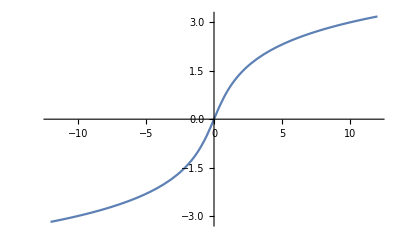

```mathematica
Plot[ArcSinh[x],{x,-12.,12.}]
```

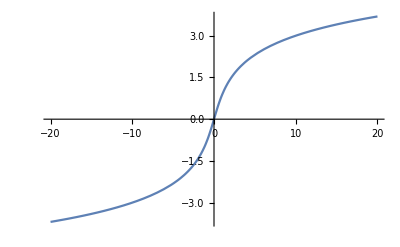

```mathematica
Plot[ArcSinh[x],{x,-20,20}]
```

```mathematica
∫_0^a √(1+(x)^2)ⅆx
```

ConditionalExpression[1/2 (a √(1+a^2)+ArcSinh[a]),Re[a]≠0||-1<Im[a]<0||0<Im[a]<1]

```mathematica
FullSimplify[
∫_0^a √(1+(x)^2)ⅆx, Element[a|x,Reals]]
```

ConditionalExpression[1/2 (a √(1+a^2)+ArcSinh[a]),a≠0]

```mathematica
f[n]==f[n-1]+∫_(n-1)^n f'[x]ⅆx
```

```mathematica
With[{f=#^2&},
f[n]==f[n-1]+∫_(n-1)^n f'[x]ⅆx]
```

n^2==(-1+n)^2+2 (-1/2 (-1+n)^2+n^2/2)

```mathematica
With[{f=#^2&, n=1},
f[n]==f[n-1]+∫_(n-1)^n f'[x]ⅆx]
```

True

```mathematica
With[{f=#^2&, n=2},
f[n-1]+∫_(n-1)^n f'[x]ⅆx]
```

4

```mathematica
1==∫_0^a √(1+D[Sin[x],x]^2)ⅆx
```

ConditionalExpression[1==√2 (EllipticE[π FractionalPart[a/π],1/2]+2 EllipticE[1/2] IntegerPart[a/π]),a∈ℝ]

```mathematica
FullSimplify[
1==∫_0^a √(1+D[Sin[x],x]^2)ⅆx, Element[x|a, Reals]]
```

√2 (EllipticE[π FractionalPart[a/π],1/2]+2 EllipticE[1/2] IntegerPart[a/π])==1

```mathematica
Reduce[√2 (EllipticE[π FractionalPart[a/π],1/2]+2 EllipticE[1/2] IntegerPart[a/π])==1]
```

EllipticE[π FractionalPart[a/π],1/2]==1/(√2)-2 EllipticE[1/2] IntegerPart[a/π]

```mathematica
Solve[EllipticE[π FractionalPart[a/π],1/2]==1/(√2)-2 EllipticE[1/2] IntegerPart[a/π],{a}]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[EllipticE[π FractionalPart[a/π],1/2]==1/(√2)-2 EllipticE[1/2] IntegerPart[a/π],{a}]

```mathematica
EllipticE[x]
```

EllipticE[x]

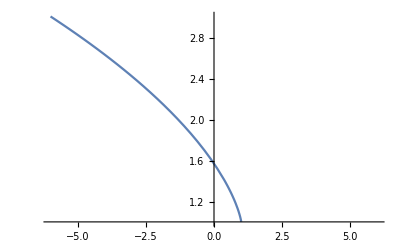

```mathematica
Plot[EllipticE[x],{x,-6.,6.}]
```

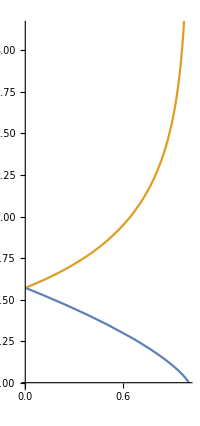

```mathematica
ParametricPlot[{
{x, EllipticE[x]},
{x, EllipticK[x]}
}, {x, 0, 2π}]
```

```mathematica
Graphics3D[Ellipsoid[{0,0},{1}]]
```

-Graphics3D-

```mathematica
999^2
```

998001

```mathematica
111^2
```

12321

```mathematica
"abccba"
```

abccba

```mathematica
Characters["abccba"]
```

{a,b,c,c,b,a}

```mathematica
{a,b,c,c,b,a}.{10^5,10^4,10^3,10^2,10^1,10^0}
```

100001 a+10010 b+1100 c

```mathematica
100001 a+10010 b+1100 c==p q
```

100001 a+10010 b+1100 c==p q

```mathematica
FullSimplify[
100001 a+10010 b+1100 c==p q, 
And[Element[a|b|c|p|q, Integers],100001 a+10010 b+1100 c<999^2]]
```

11 (9091 a+910 b+100 c)==p q

```mathematica
FindInstance[11 (9091 a+910 b+100 c)==p q,{a,b,c,p,q}]
```

{{a→0,b→0,c→0,p→0,q→0}}

```mathematica
Reduce[11 (9091 a+910 b+100 c)==p q]
```

a==(-10010 b-1100 c+p q)/100001

```mathematica
FullSimplify[
100001 a+10010 b+1100 c==p q, 
And[Element[a|b|c|p|q, Integers],
100001 a+10010 b+1100 c<999^2]]
```

11 (9091 a+910 b+100 c)==p q

```mathematica
FullSimplify[
100001 a+10010 b+1100 c==p q, 
And[Element[a|b|c|p|q, Integers],
100001 a+10010 b+1100 c<999^2,
a≠0]]
```

11 (9091 a+910 b+100 c)==p q

```mathematica
FindInstance[11 (9091 a+910 b+100 c)==p q,{a,b,c,p,q}, Integers, 5]
```

{{a→-15,b→157,c→-6,p→-1,q→-64955},{a→1,b→-165,c→1457,p→-1,q→-51051},{a→198,b→24,c→-18271,p→-1,q→57662},{a→-127,b→4,c→11604,p→-1,q→-104313},{a→-24,b→-227,c→4328,p→-1,q→-88506}}

```mathematica
FullSimplify[
100001 a+10010 b+1100 c==p q, 
And[Element[a|b|c|p|q, Integers],
100001 a+10010 b+1100 c<999^2,
a≥0,b≥0,c≥0,p≥0,q≥0]]
```

11 (9091 a+910 b+100 c)==p q

```mathematica
FindInstance[11 (9091 a+910 b+100 c)==p q,{a,b,c,p,q}]
```

{{a→0,b→0,c→0,p→0,q→0}}

```mathematica
ConditionalExpression[
11 (9091 a+910 b+100 c)==p q,
And[Element[a|b|c|p|q, Integers],
100001 a+10010 b+1100 c<999^2,
a≥0,b≥0,c≥0,p≥0,q≥0]]
```

ConditionalExpression[11 (9091 a+910 b+100 c)==p q,(a|b|c|p|q)∈ℤ&&9091 a+910 b+100 c<998001/11&&a≥0&&b≥0&&c≥0&&p≥0&&q≥0]

```mathematica
FindInstance[
ConditionalExpression[
11 (9091 a+910 b+100 c)==p q,
And[Element[a|b|c|p|q, Integers],
100001 a+10010 b+1100 c<999^2,
a≥0,b≥0,c≥0,p≥0,q≥0]],
{a,b,c,p,q},2]
```

$Aborted

```mathematica
FindInstance[
ConditionalExpression[
11 (9091 a+910 b+100 c)==p q,
And[Element[a|b|c|p|q, Integers],
100001 a+10010 b+1100 c<999^2,
a≥0,b≥0,c≥0,p≥100,q≥100]],
{a,b,c,p,q}]
```

$Aborted

```mathematica
FullSimplify[
100001 a+10010 b+1100 c==p q, 
And[Element[a|b|c|p|q, Integers],
100001 a+10010 b+1100 c<999^2,
a≥0,b≥0,c≥0,999>p≥100,999>q≥100]]
```

11 (9091 a+910 b+100 c)==p q

```mathematica
FindInstance[
ConditionalExpression[
11 (9091 a+910 b+100 c)==p q,
And[Element[a|b|c|p|q, Integers],
100001 a+10010 b+1100 c<999^2,
a≥0,b≥0,c≥0,999>p≥100,999>q≥100]],
{a,b,c,p,q}]
```

$Aborted

```mathematica
And[11 (9091 a+910 b+100 c)==p q,
Element[a|b|c|p|q, Integers],
100001 a+10010 b+1100 c<999^2,
a≥0,b≥0,c≥0,999>p≥100,999>q≥100]
```

11 (9091 a+910 b+100 c)==p q&&(a|b|c|p|q)∈ℤ&&100001 a+10010 b+1100 c<998001&&a≥0&&b≥0&&c≥0&&999>p≥100&&999>q≥100

```mathematica
Reduce[
And[11 (9091 a+910 b+100 c)==p q,
Element[a|b|c|p|q, Integers],
100001 a+10010 b+1100 c<999^2,
a≥0,b≥0,c≥0,999>p≥100,999>q≥100], {a,b,c,p,q}, Integers]
```

$Aborted

```mathematica
Reduce[
And[11 (9091 9+910 b+100 c)==p q,
Element[b|c|p|q, Integers],
100001 9+10010 b+1100 c<999^2,
b≥0,c≥0,999>p≥100,999>q≥100], {b,c,p,q}, Integers]
```

(b==0&&c==6&&p==913&&q==993)||(b==0&&c==6&&p==993&&q==913)||(b==0&&c==46&&p==971&&q==979)||(b==0&&c==46&&p==979&&q==971)||(b==1&&c==14&&p==957&&q==967)||(b==1&&c==14&&p==967&&q==957)||(b==1&&c==28&&p==961&&q==979)||(b==1&&c==28&&p==979&&q==961)||(b==2&&c==10&&p==951&&q==979)||(b==2&&c==10&&p==979&&q==951)||(b==2&&c==31&&p==957&&q==997)||(b==2&&c==31&&p==997&&q==957)

```mathematica
Reduce[
And[11 (9091 9+910 b+100 c)==p q,
Element[b|c|p|q, Integers],
100001 9+10010 b+1100 c<999^2,
b>0,c>0,999>p≥100,999>q≥100], {b,c,p,q}, Integers]
```

(b==1&&c==14&&p==957&&q==967)||(b==1&&c==14&&p==967&&q==957)||(b==1&&c==28&&p==961&&q==979)||(b==1&&c==28&&p==979&&q==961)||(b==2&&c==10&&p==951&&q==979)||(b==2&&c==10&&p==979&&q==951)||(b==2&&c==31&&p==957&&q==997)||(b==2&&c==31&&p==997&&q==957)

```mathematica
(b==2&&c==31&&p==997&&q==957)
```

```mathematica
997 957
```

954129

```mathematica
{a,b,c,c,b,a}.{10^5,10^4,10^3,10^2,10^1,10^0}
```

100001 a+10010 b+1100 c

```mathematica
Simplify[100001 a+10010 b+1100 c]
```

11 (9091 a+910 b+100 c)

```mathematica
11 (9091 a+910 b+100 c)
```

```mathematica
And[11 (9091 a+910 b+100 c)==p q,
Element[b|c|p|q, Integers],
100001 9+10010 b+1100 c<999^2,
b>0,c>0,999>p≥100,999>q≥100]
```

11 (9091 a+910 b+100 c)==p q&&(b|c|p|q)∈ℤ&&900009+10010 b+1100 c<998001&&b>0&&c>0&&999>p≥100&&999>q≥100

```mathematica
FactorInteger[2520]
```

{{2,3},{3,2},{5,1},{7,1}}

```mathematica
Factorial[10]
```

3628800

```mathematica
Factorial[20]
```

2432902008176640000

```mathematica
Product[(Subscript[a, i] i), {i, 1 ,20}]
```

2432902008176640000 a_1 a_2 a_3 a_4 a_5 a_6 a_7 a_8 a_9 a_10 a_11 a_12 a_13 a_14 a_15 a_16 a_17 a_18 a_19 a_20

```mathematica
Product[(a[i]i), {i, 1 ,20}]
```

2432902008176640000 a[1] a[2] a[3] a[4] a[5] a[6] a[7] a[8] a[9] a[10] a[11] a[12] a[13] a[14] a[15] a[16] a[17] a[18] a[19] a[20]

```mathematica
Table[i->Mod[2520,i], {i, 1, 10}]
```

{1→0,2→0,3→0,4→0,5→0,6→0,7→0,8→0,9→0,10→0}

```mathematica
Table[i->Mod[a,i], {i, 1, 10}]
```

{1→Mod[a,1],2→Mod[a,2],3→Mod[a,3],4→Mod[a,4],5→Mod[a,5],6→Mod[a,6],7→Mod[a,7],8→Mod[a,8],9→Mod[a,9],10→Mod[a,10]}

```mathematica
FoldList[And,Table[i->Mod[a,i], {i, 1, 10}]]
```

{1→Mod[a,1],(1→Mod[a,1])&&(2→Mod[a,2]),(1→Mod[a,1])&&(2→Mod[a,2])&&(3→Mod[a,3]),(1→Mod[a,1])&&(2→Mod[a,2])&&(3→Mod[a,3])&&(4→Mod[a,4]),(1→Mod[a,1])&&(2→Mod[a,2])&&(3→Mod[a,3])&&(4→Mod[a,4])&&(5→Mod[a,5]),(1→Mod[a,1])&&(2→Mod[a,2])&&(3→Mod[a,3])&&(4→Mod[a,4])&&(5→Mod[a,5])&&(6→Mod[a,6]),(1→Mod[a,1])&&(2→Mod[a,2])&&(3→Mod[a,3])&&(4→Mod[a,4])&&(5→Mod[a,5])&&(6→Mod[a,6])&&(7→Mod[a,7]),(1→Mod[a,1])&&(2→Mod[a,2])&&(3→Mod[a,3])&&(4→Mod[a,4])&&(5→Mod[a,5])&&(6→Mod[a,6])&&(7→Mod[a,7])&&(8→Mod[a,8]),(1→Mod[a,1])&&(2→Mod[a,2])&&(3→Mod[a,3])&&(4→Mod[a,4])&&(5→Mod[a,5])&&(6→Mod[a,6])&&(7→Mod[a,7])&&(8→Mod[a,8])&&(9→Mod[a,9]),(1→Mod[a,1])&&(2→Mod[a,2])&&(3→Mod[a,3])&&(4→Mod[a,4])&&(5→Mod[a,5])&&(6→Mod[a,6])&&(7→Mod[a,7])&&(8→Mod[a,8])&&(9→Mod[a,9])&&(10→Mod[a,10])}

```mathematica
Table[Mod[a,i]==0, {i, 1, 20}]
```

{Mod[a,1]==0,Mod[a,2]==0,Mod[a,3]==0,Mod[a,4]==0,Mod[a,5]==0,Mod[a,6]==0,Mod[a,7]==0,Mod[a,8]==0,Mod[a,9]==0,Mod[a,10]==0,Mod[a,11]==0,Mod[a,12]==0,Mod[a,13]==0,Mod[a,14]==0,Mod[a,15]==0,Mod[a,16]==0,Mod[a,17]==0,Mod[a,18]==0,Mod[a,19]==0,Mod[a,20]==0}

```mathematica
FindInstance[%267,{a}]
```

{{a→0}}

```mathematica
Solve[%267,{a}]
```

Solve[{Mod[a,1]==0,Mod[a,2]==0,Mod[a,3]==0,Mod[a,4]==0,Mod[a,5]==0,Mod[a,6]==0,Mod[a,7]==0,Mod[a,8]==0,Mod[a,9]==0,Mod[a,10]==0,Mod[a,11]==0,Mod[a,12]==0,Mod[a,13]==0,Mod[a,14]==0,Mod[a,15]==0,Mod[a,16]==0,Mod[a,17]==0,Mod[a,18]==0,Mod[a,19]==0,Mod[a,20]==0},{a}]

```mathematica
Fold[f,x,{a,b,c,d}]
```

f[f[f[f[x,a],b],c],d]

```mathematica
Fold[And,True[],Table[Mod[a,i]==0, {i, 1, 20}]]
```

True[]&&Mod[a,1]==0&&Mod[a,2]==0&&Mod[a,3]==0&&Mod[a,4]==0&&Mod[a,5]==0&&Mod[a,6]==0&&Mod[a,7]==0&&Mod[a,8]==0&&Mod[a,9]==0&&Mod[a,10]==0&&Mod[a,11]==0&&Mod[a,12]==0&&Mod[a,13]==0&&Mod[a,14]==0&&Mod[a,15]==0&&Mod[a,16]==0&&Mod[a,17]==0&&Mod[a,18]==0&&Mod[a,19]==0&&Mod[a,20]==0

```mathematica
Reduce[
True[]&&Mod[a,1]==0&&Mod[a,2]==0&&Mod[a,3]==0&&Mod[a,4]==0&&Mod[a,5]==0&&Mod[a,6]==0&&Mod[a,7]==0&&Mod[a,8]==0&&Mod[a,9]==0&&Mod[a,10]==0&&Mod[a,11]==0&&Mod[a,12]==0&&Mod[a,13]==0&&Mod[a,14]==0&&Mod[a,15]==0&&Mod[a,16]==0&&Mod[a,17]==0&&Mod[a,18]==0&&Mod[a,19]==0&&Mod[a,20]==0, a, Integers]
```

Reduce[True[]&&Mod[a,1]==0&&Mod[a,2]==0&&Mod[a,3]==0&&Mod[a,4]==0&&Mod[a,5]==0&&Mod[a,6]==0&&Mod[a,7]==0&&Mod[a,8]==0&&Mod[a,9]==0&&Mod[a,10]==0&&Mod[a,11]==0&&Mod[a,12]==0&&Mod[a,13]==0&&Mod[a,14]==0&&Mod[a,15]==0&&Mod[a,16]==0&&Mod[a,17]==0&&Mod[a,18]==0&&Mod[a,19]==0&&Mod[a,20]==0,a,ℤ]

```mathematica
FindInstance[
{Mod[a,1]==0,Mod[a,2]==0,Mod[a,3]==0,Mod[a,4]==0,Mod[a,5]==0,Mod[a,6]==0,Mod[a,7]==0,Mod[a,8]==0,Mod[a,9]==0,Mod[a,10]==0,Mod[a,11]==0,Mod[a,12]==0,Mod[a,13]==0,Mod[a,14]==0,Mod[a,15]==0,Mod[a,16]==0,Mod[a,17]==0,Mod[a,18]==0,Mod[a,19]==0,Mod[a,20]==0}, a, 2]
```

FindInstance[{Mod[a,1]==0,Mod[a,2]==0,Mod[a,3]==0,Mod[a,4]==0,Mod[a,5]==0,Mod[a,6]==0,Mod[a,7]==0,Mod[a,8]==0,Mod[a,9]==0,Mod[a,10]==0,Mod[a,11]==0,Mod[a,12]==0,Mod[a,13]==0,Mod[a,14]==0,Mod[a,15]==0,Mod[a,16]==0,Mod[a,17]==0,Mod[a,18]==0,Mod[a,19]==0,Mod[a,20]==0},a,2]

```mathematica
Product[
With[{a=First[i], b=Last[i]},
a^b], {i, {{2,3}, {3,2}, {5, 1}, {7, 1}}}]
```

2520

```mathematica
Table[FactorInteger[i], {i, 1,20}]
```

{{{1,1}},{{2,1}},{{3,1}},{{2,2}},{{5,1}},{{2,1},{3,1}},{{7,1}},{{2,3}},{{3,2}},{{2,1},{5,1}},{{11,1}},{{2,2},{3,1}},{{13,1}},{{2,1},{7,1}},{{3,1},{5,1}},{{2,4}},{{17,1}},{{2,1},{3,2}},{{19,1}},{{2,2},{5,1}}}

```mathematica
Flatten[
Table[FactorInteger[i], {i, 1,20}],1]
```

{{1,1},{2,1},{3,1},{2,2},{5,1},{2,1},{3,1},{7,1},{2,3},{3,2},{2,1},{5,1},{11,1},{2,2},{3,1},{13,1},{2,1},{7,1},{3,1},{5,1},{2,4},{17,1},{2,1},{3,2},{19,1},{2,2},{5,1}}

```mathematica
GroupBy[
Flatten[
Table[FactorInteger[i], {i, 1,20}],1], First]
```

<|1→{{1,1}},2→{{2,1},{2,2},{2,1},{2,3},{2,1},{2,2},{2,1},{2,4},{2,1},{2,2}},3→{{3,1},{3,1},{3,2},{3,1},{3,1},{3,2}},5→{{5,1},{5,1},{5,1},{5,1}},7→{{7,1},{7,1}},11→{{11,1}},13→{{13,1}},17→{{17,1}},19→{{19,1}}|>

```mathematica
FullForm[
<|1->{{1,1}},2->{{2,1},{2,2},{2,1},{2,3},{2,1},{2,2},{2,1},{2,4},{2,1},{2,2}},3->{{3,1},{3,1},{3,2},{3,1},{3,1},{3,2}},5->{{5,1},{5,1},{5,1},{5,1}},7->{{7,1},{7,1}},11->{{11,1}},13->{{13,1}},17->{{17,1}},19->{{19,1}}|>]
```

Association[Rule[1,List[List[1,1]]],Rule[2,List[List[2,1],List[2,2],List[2,1],List[2,3],List[2,1],List[2,2],List[2,1],List[2,4],List[2,1],List[2,2]]],Rule[3,List[List[3,1],List[3,1],List[3,2],List[3,1],List[3,1],List[3,2]]],Rule[5,List[List[5,1],List[5,1],List[5,1],List[5,1]]],Rule[7,List[List[7,1],List[7,1]]],Rule[11,List[List[11,1]]],Rule[13,List[List[13,1]]],Rule[17,List[List[17,1]]],Rule[19,List[List[19,1]]]]

```mathematica
Map[
Identity,
GroupBy[
Flatten[
Table[FactorInteger[i], {i, 1,20}],1], First]]
```

<|1→{{1,1}},2→{{2,1},{2,2},{2,1},{2,3},{2,1},{2,2},{2,1},{2,4},{2,1},{2,2}},3→{{3,1},{3,1},{3,2},{3,1},{3,1},{3,2}},5→{{5,1},{5,1},{5,1},{5,1}},7→{{7,1},{7,1}},11→{{11,1}},13→{{13,1}},17→{{17,1}},19→{{19,1}}|>

```mathematica
Product[
With[{a=First[i], b=Last[i]},
a^b], {i, {{2,4}, {3,2}, {5, 1}, {7, 1}, {11, 1}, {13, 1}, {17, 1}, {19, 1}}}]
```

232792560

```mathematica
∑_(i=1)^10 i^2
```

385

```mathematica
(∑_(i=1)^10 i)^2
```

3025

```mathematica
(∑_(i=1)^10 i)^2-∑_(i=1)^10 i^2
```

2640

```mathematica
(∑_(i=1)^10 i)^2-∑_(i=1)^10 i^2
```

2640

```mathematica
(∑_(i=1)^100 i)^2
```

25502500

```mathematica
∑_(i=1)^100 i^2
```

338350

```mathematica
(∑_(i=1)^100 i)^2-∑_(i=1)^100 i^2
```

25164150

```mathematica
Prime[10001]
```

104743

```mathematica
Product[Subscript[a, i], {i, 1, 13}]
```

a_1 a_2 a_3 a_4 a_5 a_6 a_7 a_8 a_9 a_10 a_11 a_12 a_13

```mathematica
Subscript[a, 1] Subscript[a, 2] Subscript[a, 3] Subscript[a, 4] Subscript[a, 5] Subscript[a, 6] Subscript[a, 7] Subscript[a, 8] Subscript[a, 9] Subscript[a, 10] Subscript[a, 11] Subscript[a, 12] Subscript[a, 13]
```

```mathematica
Table[Subscript[a, i]&&10>Subscript[a, i]>0, {i, 1, 13}]
```

{a_1&&10>a_1>0,a_2&&10>a_2>0,a_3&&10>a_3>0,a_4&&10>a_4>0,a_5&&10>a_5>0,a_6&&10>a_6>0,a_7&&10>a_7>0,a_8&&10>a_8>0,a_9&&10>a_9>0,a_10&&10>a_10>0,a_11&&10>a_11>0,a_12&&10>a_12>0,a_13&&10>a_13>0}

```mathematica
Fold[
,True,
Table[Subscript[a, i]&&10>Subscript[a, i]>0, {i, 1, 13}]]
```

```mathematica
"73167176531330624919225119674426574742355349194934
96983520312774506326239578318016984801869478851843
85861560789112949495459501737958331952853208805511
12540698747158523863050715693290963295227443043557
66896648950445244523161731856403098711121722383113
62229893423380308135336276614282806444486645238749
30358907296290491560440772390713810515859307960866
70172427121883998797908792274921901699720888093776
65727333001053367881220235421809751254540594752243
52584907711670556013604839586446706324415722155397
53697817977846174064955149290862569321978468622482
83972241375657056057490261407972968652414535100474
82166370484403199890008895243450658541227588666881
16427171479924442928230863465674813919123162824586
17866458359124566529476545682848912883142607690042
24219022671055626321111109370544217506941658960408
07198403850962455444362981230987879927244284909188
84580156166097919133875499200524063689912560717606
05886116467109405077541002256983155200055935729725
71636269561882670428252483600823257530420752963450"
```

73167176531330624919225119674426574742355349194934
96983520312774506326239578318016984801869478851843
85861560789112949495459501737958331952853208805511
12540698747158523863050715693290963295227443043557
66896648950445244523161731856403098711121722383113
62229893423380308135336276614282806444486645238749
30358907296290491560440772390713810515859307960866
70172427121883998797908792274921901699720888093776
65727333001053367881220235421809751254540594752243
52584907711670556013604839586446706324415722155397
53697817977846174064955149290862569321978468622482
83972241375657056057490261407972968652414535100474
82166370484403199890008895243450658541227588666881
16427171479924442928230863465674813919123162824586
17866458359124566529476545682848912883142607690042
24219022671055626321111109370544217506941658960408
07198403850962455444362981230987879927244284909188
84580156166097919133875499200524063689912560717606
05886116467109405077541002256983155200055935729725
71636269561882670428252483600823257530420752963450

```mathematica
IntegerString[Out[99]]
```

7

```mathematica
Characters[Out[299]]
```

{7,3,1,6,7,1,7,6,5,3,1,3,3,0,6,2,4,9,1,9,2,2,5,1,1,9,6,7,4,4,2,6,5,7,4,7,4,2,3,5,5,3,4,9,1,9,4,9,3,4,
,9,6,9,8,3,5,2,0,3,1,2,7,7,4,5,0,6,3,2,6,2,3,9,5,7,8,3,1,8,0,1,6,9,8,4,8,0,1,8,6,9,4,7,8,8,5,1,8,4,3,
,8,5,8,6,1,5,6,0,7,8,9,1,1,2,9,4,9,4,9,5,4,5,9,5,0,1,7,3,7,9,5,8,3,3,1,9,5,2,8,5,3,2,0,8,8,0,5,5,1,1,
,1,2,5,4,0,6,9,8,7,4,7,1,5,8,5,2,3,8,6,3,0,5,0,7,1,5,6,9,3,2,9,0,9,6,3,2,9,5,2,2,7,4,4,3,0,4,3,5,5,7,
,6,6,8,9,6,6,4,8,9,5,0,4,4,5,2,4,4,5,2,3,1,6,1,7,3,1,8,5,6,4,0,3,0,9,8,7,1,1,1,2,1,7,2,2,3,8,3,1,1,3,
,6,2,2,2,9,8,9,3,4,2,3,3,8,0,3,0,8,1,3,5,3,3,6,2,7,6,6,1,4,2,8,2,8,0,6,4,4,4,4,8,6,6,4,5,2,3,8,7,4,9,
,3,0,3,5,8,9,0,7,2,9,6,2,9,0,4,9,1,5,6,0,4,4,0,7,7,2,3,9,0,7,1,3,8,1,0,5,1,5,8,5,9,3,0,7,9,6,0,8,6,6,
,7,0,1,7,2,4,2,7,1,2,1,8,8,3,9,9,8,7,9,7,9,0,8,7,9,2,2,7,4,9,2,1,9,0,1,6,9,9,7,2,0,8,8,8,0,9,3,7,7,6,
,6,5,7,2,7,3,3,3,0,0,1,0,5,3,3,6,7,8,8,1,2,2,0,2,3,5,4,2,1,8,0,9,7,5,1,2,5,4,5,4,0,5,9,4,7,5,2,2,4,3,
,5,2,5,8,4,9,0,7,7,1,1,6,7,0,5,5,6,0,1,3,6,0,4,8,3,9,5,8,6,4,4,6,7,0,6,3,2,4,4,1,5,7,2,2,1,5,5,3,9,7,
,5,3,6,9,7,8,1,7,9,7,7,8,4,6,1,7,4,0,6,4,9,5,5,1,4,9,2,9,0,8,6,2,5,6,9,3,2,1,9,7,8,4,6,8,6,2,2,4,8,2,
,8,3,9,7,2,2,4,1,3,7,5,6,5,7,0,5,6,0,5,7,4,9,0,2,6,1,4,0,7,9,7,2,9,6,8,6,5,2,4,1,4,5,3,5,1,0,0,4,7,4,
,8,2,1,6,6,3,7,0,4,8,4,4,0,3,1,9,9,8,9,0,0,0,8,8,9,5,2,4,3,4,5,0,6,5,8,5,4,1,2,2,7,5,8,8,6,6,6,8,8,1,
,1,6,4,2,7,1,7,1,4,7,9,9,2,4,4,4,2,9,2,8,2,3,0,8,6,3,4,6,5,6,7,4,8,1,3,9,1,9,1,2,3,1,6,2,8,2,4,5,8,6,
,1,7,8,6,6,4,5,8,3,5,9,1,2,4,5,6,6,5,2,9,4,7,6,5,4,5,6,8,2,8,4,8,9,1,2,8,8,3,1,4,2,6,0,7,6,9,0,0,4,2,
,2,4,2,1,9,0,2,2,6,7,1,0,5,5,6,2,6,3,2,1,1,1,1,1,0,9,3,7,0,5,4,4,2,1,7,5,0,6,9,4,1,6,5,8,9,6,0,4,0,8,
,0,7,1,9,8,4,0,3,8,5,0,9,6,2,4,5,5,4,4,4,3,6,2,9,8,1,2,3,0,9,8,7,8,7,9,9,2,7,2,4,4,2,8,4,9,0,9,1,8,8,
,8,4,5,8,0,1,5,6,1,6,6,0,9,7,9,1,9,1,3,3,8,7,5,4,9,9,2,0,0,5,2,4,0,6,3,6,8,9,9,1,2,5,6,0,7,1,7,6,0,6,
,0,5,8,8,6,1,1,6,4,6,7,1,0,9,4,0,5,0,7,7,5,4,1,0,0,2,2,5,6,9,8,3,1,5,5,2,0,0,0,5,5,9,3,5,7,2,9,7,2,5,
,7,1,6,3,6,2,6,9,5,6,1,8,8,2,6,7,0,4,2,8,2,5,2,4,8,3,6,0,0,8,2,3,2,5,7,5,3,0,4,2,0,7,5,2,9,6,3,4,5,0}

```mathematica
FromDigits[Characters[Out[299]]]
```

0+10 (5+10 (4+10 (3+10 (6+10 (9+10 (2+10 (5+10 (7+10 (0+10 (2+10 (4+10 (0+10 (3+10 (5+10 (7+10 (5+10 (2+10 (3+10 (2+10 (8+10 (0+10 (0+10 (6+10 (3+10 (8+10 (4+10 (2+10 (5+10 (2+10 (8+10 (2+10 (4+10 (0+10 (7+10 (6+10 (2+10 (8+10 (8+10 (1+10 (6+10 (5+10 (9+10 (6+10 (2+10 (6+10 (3+10 (6+10 (1+10 (7+10 (
+10 (5+10 (2+10 (7+10 (9+10 (2+10 (7+10 (5+10 (3+10 (9+10 (5+10 (5+10 (0+10 (0+10 (0+10 (2+10 (5+10 (5+10 (1+10 (3+10 (8+10 (9+10 (6+10 (5+10 (2+10 (2+10 (0+10 (0+10 (1+10 (4+10 (5+10 (7+10 (7+10 (0+10 (5+10 (0+10 (4+10 (9+10 (0+10 (1+10 (7+10 (6+10 (4+10 (6+10 (1+10 (1+10 (6+10 (8+10 (8+10 (5+10 (0+10 (
+10 (6+10 (0+10 (6+10 (7+10 (1+10 (7+10 (0+10 (6+10 (5+10 (2+10 (1+10 (9+10 (9+10 (8+10 (6+10 (3+10 (6+10 (0+10 (4+10 (2+10 (5+10 (0+10 (0+10 (2+10 (9+10 (9+10 (4+10 (5+10 (7+10 (8+10 (3+10 (3+10 (1+10 (9+10 (1+10 (9+10 (7+10 (9+10 (0+10 (6+10 (6+10 (1+10 (6+10 (5+10 (1+10 (0+10 (8+10 (5+10 (4+10 (8+10 (
+10 (8+10 (8+10 (1+10 (9+10 (0+10 (9+10 (4+10 (8+10 (2+10 (4+10 (4+10 (2+10 (7+10 (2+10 (9+10 (9+10 (7+10 (8+10 (7+10 (8+10 (9+10 (0+10 (3+10 (2+10 (1+10 (8+10 (9+10 (2+10 (6+10 (3+10 (4+10 (4+10 (4+10 (5+10 (5+10 (4+10 (2+10 (6+10 (9+10 (0+10 (5+10 (8+10 (3+10 (0+10 (4+10 (8+10 (9+10 (1+10 (7+10 (0+10 (
+10 (8+10 (0+10 (4+10 (0+10 (6+10 (9+10 (8+10 (5+10 (6+10 (1+10 (4+10 (9+10 (6+10 (0+10 (5+10 (7+10 (1+10 (2+10 (4+10 (4+10 (5+10 (0+10 (7+10 (3+10 (9+10 (0+10 (1+10 (1+10 (1+10 (1+10 (1+10 (2+10 (3+10 (6+10 (2+10 (6+10 (5+10 (5+10 (0+10 (1+10 (7+10 (6+10 (2+10 (2+10 (0+10 (9+10 (1+10 (2+10 (4+10 (2+10 (
+10 (2+10 MaxFormatDepthExceededMaxFormatDepthExceededMaxFormatDepthExceeded)))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))

```mathematica
ImportString["123", "Integer8"]
```

{49,50,51}

```mathematica
n=73167176531330624919225119674426574742355349194934
96983520312774506326239578318016984801869478851843
85861560789112949495459501737958331952853208805511
12540698747158523863050715693290963295227443043557
66896648950445244523161731856403098711121722383113
62229893423380308135336276614282806444486645238749
30358907296290491560440772390713810515859307960866
70172427121883998797908792274921901699720888093776
65727333001053367881220235421809751254540594752243
52584907711670556013604839586446706324415722155397
53697817977846174064955149290862569321978468622482
83972241375657056057490261407972968652414535100474
82166370484403199890008895243450658541227588666881
16427171479924442928230863465674813919123162824586
17866458359124566529476545682848912883142607690042
24219022671055626321111109370544217506941658960408
07198403850962455444362981230987879927244284909188
84580156166097919133875499200524063689912560717606
05886116467109405077541002256983155200055935729725
71636269561882670428252483600823257530420752963450
```

73167176531330624919225119674426574742355349194934

96983520312774506326239578318016984801869478851843

85861560789112949495459501737958331952853208805511

12540698747158523863050715693290963295227443043557

66896648950445244523161731856403098711121722383113

62229893423380308135336276614282806444486645238749

30358907296290491560440772390713810515859307960866

70172427121883998797908792274921901699720888093776

65727333001053367881220235421809751254540594752243

52584907711670556013604839586446706324415722155397

53697817977846174064955149290862569321978468622482

83972241375657056057490261407972968652414535100474

82166370484403199890008895243450658541227588666881

16427171479924442928230863465674813919123162824586

17866458359124566529476545682848912883142607690042

24219022671055626321111109370544217506941658960408

7198403850962455444362981230987879927244284909188

84580156166097919133875499200524063689912560717606

5886116467109405077541002256983155200055935729725

71636269561882670428252483600823257530420752963450

```mathematica
n
```

73167176531330624919225119674426574742355349194934

```mathematica
Out[299]
```

73167176531330624919225119674426574742355349194934
96983520312774506326239578318016984801869478851843
85861560789112949495459501737958331952853208805511
12540698747158523863050715693290963295227443043557
66896648950445244523161731856403098711121722383113
62229893423380308135336276614282806444486645238749
30358907296290491560440772390713810515859307960866
70172427121883998797908792274921901699720888093776
65727333001053367881220235421809751254540594752243
52584907711670556013604839586446706324415722155397
53697817977846174064955149290862569321978468622482
83972241375657056057490261407972968652414535100474
82166370484403199890008895243450658541227588666881
16427171479924442928230863465674813919123162824586
17866458359124566529476545682848912883142607690042
24219022671055626321111109370544217506941658960408
07198403850962455444362981230987879927244284909188
84580156166097919133875499200524063689912560717606
05886116467109405077541002256983155200055935729725
71636269561882670428252483600823257530420752963450

```mathematica
Characters[Out[299]]
```

{7,3,1,6,7,1,7,6,5,3,1,3,3,0,6,2,4,9,1,9,2,2,5,1,1,9,6,7,4,4,2,6,5,7,4,7,4,2,3,5,5,3,4,9,1,9,4,9,3,4,
,9,6,9,8,3,5,2,0,3,1,2,7,7,4,5,0,6,3,2,6,2,3,9,5,7,8,3,1,8,0,1,6,9,8,4,8,0,1,8,6,9,4,7,8,8,5,1,8,4,3,
,8,5,8,6,1,5,6,0,7,8,9,1,1,2,9,4,9,4,9,5,4,5,9,5,0,1,7,3,7,9,5,8,3,3,1,9,5,2,8,5,3,2,0,8,8,0,5,5,1,1,
,1,2,5,4,0,6,9,8,7,4,7,1,5,8,5,2,3,8,6,3,0,5,0,7,1,5,6,9,3,2,9,0,9,6,3,2,9,5,2,2,7,4,4,3,0,4,3,5,5,7,
,6,6,8,9,6,6,4,8,9,5,0,4,4,5,2,4,4,5,2,3,1,6,1,7,3,1,8,5,6,4,0,3,0,9,8,7,1,1,1,2,1,7,2,2,3,8,3,1,1,3,
,6,2,2,2,9,8,9,3,4,2,3,3,8,0,3,0,8,1,3,5,3,3,6,2,7,6,6,1,4,2,8,2,8,0,6,4,4,4,4,8,6,6,4,5,2,3,8,7,4,9,
,3,0,3,5,8,9,0,7,2,9,6,2,9,0,4,9,1,5,6,0,4,4,0,7,7,2,3,9,0,7,1,3,8,1,0,5,1,5,8,5,9,3,0,7,9,6,0,8,6,6,
,7,0,1,7,2,4,2,7,1,2,1,8,8,3,9,9,8,7,9,7,9,0,8,7,9,2,2,7,4,9,2,1,9,0,1,6,9,9,7,2,0,8,8,8,0,9,3,7,7,6,
,6,5,7,2,7,3,3,3,0,0,1,0,5,3,3,6,7,8,8,1,2,2,0,2,3,5,4,2,1,8,0,9,7,5,1,2,5,4,5,4,0,5,9,4,7,5,2,2,4,3,
,5,2,5,8,4,9,0,7,7,1,1,6,7,0,5,5,6,0,1,3,6,0,4,8,3,9,5,8,6,4,4,6,7,0,6,3,2,4,4,1,5,7,2,2,1,5,5,3,9,7,
,5,3,6,9,7,8,1,7,9,7,7,8,4,6,1,7,4,0,6,4,9,5,5,1,4,9,2,9,0,8,6,2,5,6,9,3,2,1,9,7,8,4,6,8,6,2,2,4,8,2,
,8,3,9,7,2,2,4,1,3,7,5,6,5,7,0,5,6,0,5,7,4,9,0,2,6,1,4,0,7,9,7,2,9,6,8,6,5,2,4,1,4,5,3,5,1,0,0,4,7,4,
,8,2,1,6,6,3,7,0,4,8,4,4,0,3,1,9,9,8,9,0,0,0,8,8,9,5,2,4,3,4,5,0,6,5,8,5,4,1,2,2,7,5,8,8,6,6,6,8,8,1,
,1,6,4,2,7,1,7,1,4,7,9,9,2,4,4,4,2,9,2,8,2,3,0,8,6,3,4,6,5,6,7,4,8,1,3,9,1,9,1,2,3,1,6,2,8,2,4,5,8,6,
,1,7,8,6,6,4,5,8,3,5,9,1,2,4,5,6,6,5,2,9,4,7,6,5,4,5,6,8,2,8,4,8,9,1,2,8,8,3,1,4,2,6,0,7,6,9,0,0,4,2,
,2,4,2,1,9,0,2,2,6,7,1,0,5,5,6,2,6,3,2,1,1,1,1,1,0,9,3,7,0,5,4,4,2,1,7,5,0,6,9,4,1,6,5,8,9,6,0,4,0,8,
,0,7,1,9,8,4,0,3,8,5,0,9,6,2,4,5,5,4,4,4,3,6,2,9,8,1,2,3,0,9,8,7,8,7,9,9,2,7,2,4,4,2,8,4,9,0,9,1,8,8,
,8,4,5,8,0,1,5,6,1,6,6,0,9,7,9,1,9,1,3,3,8,7,5,4,9,9,2,0,0,5,2,4,0,6,3,6,8,9,9,1,2,5,6,0,7,1,7,6,0,6,
,0,5,8,8,6,1,1,6,4,6,7,1,0,9,4,0,5,0,7,7,5,4,1,0,0,2,2,5,6,9,8,3,1,5,5,2,0,0,0,5,5,9,3,5,7,2,9,7,2,5,
,7,1,6,3,6,2,6,9,5,6,1,8,8,2,6,7,0,4,2,8,2,5,2,4,8,3,6,0,0,8,2,3,2,5,7,5,3,0,4,2,0,7,5,2,9,6,3,4,5,0}

```mathematica
NumberString["234"]
```

NumberString[234]

```mathematica
ToExpression["234"]
```

234

```mathematica
ToExpression[Out[299]]
```

71636269561882670428252483600823257530420752963450

```mathematica
Characters[Out[299]]
```

{7,3,1,6,7,1,7,6,5,3,1,3,3,0,6,2,4,9,1,9,2,2,5,1,1,9,6,7,4,4,2,6,5,7,4,7,4,2,3,5,5,3,4,9,1,9,4,9,3,4,
,9,6,9,8,3,5,2,0,3,1,2,7,7,4,5,0,6,3,2,6,2,3,9,5,7,8,3,1,8,0,1,6,9,8,4,8,0,1,8,6,9,4,7,8,8,5,1,8,4,3,
,8,5,8,6,1,5,6,0,7,8,9,1,1,2,9,4,9,4,9,5,4,5,9,5,0,1,7,3,7,9,5,8,3,3,1,9,5,2,8,5,3,2,0,8,8,0,5,5,1,1,
,1,2,5,4,0,6,9,8,7,4,7,1,5,8,5,2,3,8,6,3,0,5,0,7,1,5,6,9,3,2,9,0,9,6,3,2,9,5,2,2,7,4,4,3,0,4,3,5,5,7,
,6,6,8,9,6,6,4,8,9,5,0,4,4,5,2,4,4,5,2,3,1,6,1,7,3,1,8,5,6,4,0,3,0,9,8,7,1,1,1,2,1,7,2,2,3,8,3,1,1,3,
,6,2,2,2,9,8,9,3,4,2,3,3,8,0,3,0,8,1,3,5,3,3,6,2,7,6,6,1,4,2,8,2,8,0,6,4,4,4,4,8,6,6,4,5,2,3,8,7,4,9,
,3,0,3,5,8,9,0,7,2,9,6,2,9,0,4,9,1,5,6,0,4,4,0,7,7,2,3,9,0,7,1,3,8,1,0,5,1,5,8,5,9,3,0,7,9,6,0,8,6,6,
,7,0,1,7,2,4,2,7,1,2,1,8,8,3,9,9,8,7,9,7,9,0,8,7,9,2,2,7,4,9,2,1,9,0,1,6,9,9,7,2,0,8,8,8,0,9,3,7,7,6,
,6,5,7,2,7,3,3,3,0,0,1,0,5,3,3,6,7,8,8,1,2,2,0,2,3,5,4,2,1,8,0,9,7,5,1,2,5,4,5,4,0,5,9,4,7,5,2,2,4,3,
,5,2,5,8,4,9,0,7,7,1,1,6,7,0,5,5,6,0,1,3,6,0,4,8,3,9,5,8,6,4,4,6,7,0,6,3,2,4,4,1,5,7,2,2,1,5,5,3,9,7,
,5,3,6,9,7,8,1,7,9,7,7,8,4,6,1,7,4,0,6,4,9,5,5,1,4,9,2,9,0,8,6,2,5,6,9,3,2,1,9,7,8,4,6,8,6,2,2,4,8,2,
,8,3,9,7,2,2,4,1,3,7,5,6,5,7,0,5,6,0,5,7,4,9,0,2,6,1,4,0,7,9,7,2,9,6,8,6,5,2,4,1,4,5,3,5,1,0,0,4,7,4,
,8,2,1,6,6,3,7,0,4,8,4,4,0,3,1,9,9,8,9,0,0,0,8,8,9,5,2,4,3,4,5,0,6,5,8,5,4,1,2,2,7,5,8,8,6,6,6,8,8,1,
,1,6,4,2,7,1,7,1,4,7,9,9,2,4,4,4,2,9,2,8,2,3,0,8,6,3,4,6,5,6,7,4,8,1,3,9,1,9,1,2,3,1,6,2,8,2,4,5,8,6,
,1,7,8,6,6,4,5,8,3,5,9,1,2,4,5,6,6,5,2,9,4,7,6,5,4,5,6,8,2,8,4,8,9,1,2,8,8,3,1,4,2,6,0,7,6,9,0,0,4,2,
,2,4,2,1,9,0,2,2,6,7,1,0,5,5,6,2,6,3,2,1,1,1,1,1,0,9,3,7,0,5,4,4,2,1,7,5,0,6,9,4,1,6,5,8,9,6,0,4,0,8,
,0,7,1,9,8,4,0,3,8,5,0,9,6,2,4,5,5,4,4,4,3,6,2,9,8,1,2,3,0,9,8,7,8,7,9,9,2,7,2,4,4,2,8,4,9,0,9,1,8,8,
,8,4,5,8,0,1,5,6,1,6,6,0,9,7,9,1,9,1,3,3,8,7,5,4,9,9,2,0,0,5,2,4,0,6,3,6,8,9,9,1,2,5,6,0,7,1,7,6,0,6,
,0,5,8,8,6,1,1,6,4,6,7,1,0,9,4,0,5,0,7,7,5,4,1,0,0,2,2,5,6,9,8,3,1,5,5,2,0,0,0,5,5,9,3,5,7,2,9,7,2,5,
,7,1,6,3,6,2,6,9,5,6,1,8,8,2,6,7,0,4,2,8,2,5,2,4,8,3,6,0,0,8,2,3,2,5,7,5,3,0,4,2,0,7,5,2,9,6,3,4,5,0}

```mathematica
"\n"
```

```mathematica
Select[Characters[Out[299]], DigitQ]
```

{7,3,1,6,7,1,7,6,5,3,1,3,3,0,6,2,4,9,1,9,2,2,5,1,1,9,6,7,4,4,2,6,5,7,4,7,4,2,3,5,5,3,4,9,1,9,4,9,3,4,9,6,9,8,3,5,2,0,3,1,2,7,7,4,5,0,6,3,2,6,2,3,9,5,7,8,3,1,8,0,1,6,9,8,4,8,0,1,8,6,9,4,7,8,8,5,1,8,4,3,8,5,8,6,1,5,6,0,7,8,9,1,1,2,9,4,9,4,9,5,4,5,9,5,0,1,7,3,7,9,5,8,3,3,1,9,5,2,8,5,3,2,0,8,8,0,5,5,1,1,1,2,5,4,0,6,9,8,7,4,7,1,5,8,5,2,3,8,6,3,0,5,0,7,1,5,6,9,3,2,9,0,9,6,3,2,9,5,2,2,7,4,4,3,0,4,3,5,5,7,6,6,8,9,6,6,4,8,9,5,0,4,4,5,2,4,4,5,2,3,1,6,1,7,3,1,8,5,6,4,0,3,0,9,8,7,1,1,1,2,1,7,2,2,3,8,3,1,1,3,6,2,2,2,9,8,9,3,4,2,3,3,8,0,3,0,8,1,3,5,3,3,6,2,7,6,6,1,4,2,8,2,8,0,6,4,4,4,4,8,6,6,4,5,2,3,8,7,4,9,3,0,3,5,8,9,0,7,2,9,6,2,9,0,4,9,1,5,6,0,4,4,0,7,7,2,3,9,0,7,1,3,8,1,0,5,1,5,8,5,9,3,0,7,9,6,0,8,6,6,7,0,1,7,2,4,2,7,1,2,1,8,8,3,9,9,8,7,9,7,9,0,8,7,9,2,2,7,4,9,2,1,9,0,1,6,9,9,7,2,0,8,8,8,0,9,3,7,7,6,6,5,7,2,7,3,3,3,0,0,1,0,5,3,3,6,7,8,8,1,2,2,0,2,3,5,4,2,1,8,0,9,7,5,1,2,5,4,5,4,0,5,9,4,7,5,2,2,4,3,5,2,5,8,4,9,0,7,7,1,1,6,7,0,5,5,6,0,1,3,6,0,4,8,3,9,5,8,6,4,4,6,7,0,6,3,2,4,4,1,5,7,2,2,1,5,5,3,9,7,5,3,6,9,7,8,1,7,9,7,7,8,4,6,1,7,4,0,6,4,9,5,5,1,4,9,2,9,0,8,6,2,5,6,9,3,2,1,9,7,8,4,6,8,6,2,2,4,8,2,8,3,9,7,2,2,4,1,3,7,5,6,5,7,0,5,6,0,5,7,4,9,0,2,6,1,4,0,7,9,7,2,9,6,8,6,5,2,4,1,4,5,3,5,1,0,0,4,7,4,8,2,1,6,6,3,7,0,4,8,4,4,0,3,1,9,9,8,9,0,0,0,8,8,9,5,2,4,3,4,5,0,6,5,8,5,4,1,2,2,7,5,8,8,6,6,6,8,8,1,1,6,4,2,7,1,7,1,4,7,9,9,2,4,4,4,2,9,2,8,2,3,0,8,6,3,4,6,5,6,7,4,8,1,3,9,1,9,1,2,3,1,6,2,8,2,4,5,8,6,1,7,8,6,6,4,5,8,3,5,9,1,2,4,5,6,6,5,2,9,4,7,6,5,4,5,6,8,2,8,4,8,9,1,2,8,8,3,1,4,2,6,0,7,6,9,0,0,4,2,2,4,2,1,9,0,2,2,6,7,1,0,5,5,6,2,6,3,2,1,1,1,1,1,0,9,3,7,0,5,4,4,2,1,7,5,0,6,9,4,1,6,5,8,9,6,0,4,0,8,0,7,1,9,8,4,0,3,8,5,0,9,6,2,4,5,5,4,4,4,3,6,2,9,8,1,2,3,0,9,8,7,8,7,9,9,2,7,2,4,4,2,8,4,9,0,9,1,8,8,8,4,5,8,0,1,5,6,1,6,6,0,9,7,9,1,9,1,3,3,8,7,5,4,9,9,2,0,0,5,2,4,0,6,3,6,8,9,9,1,2,5,6,0,7,1,7,6,0,6,0,5,8,8,6,1,1,6,4,6,7,1,0,9,4,0,5,0,7,7,5,4,1,0,0,2,2,5,6,9,8,3,1,5,5,2,0,0,0,5,5,9,3,5,7,2,9,7,2,5,7,1,6,3,6,2,6,9,5,6,1,8,8,2,6,7,0,4,2,8,2,5,2,4,8,3,6,0,0,8,2,3,2,5,7,5,3,0,4,2,0,7,5,2,9,6,3,4,5,0}

```mathematica
Map[ToExpression,
Select[Characters[Out[299]], DigitQ]]
```

{7,3,1,6,7,1,7,6,5,3,1,3,3,0,6,2,4,9,1,9,2,2,5,1,1,9,6,7,4,4,2,6,5,7,4,7,4,2,3,5,5,3,4,9,1,9,4,9,3,4,9,6,9,8,3,5,2,0,3,1,2,7,7,4,5,0,6,3,2,6,2,3,9,5,7,8,3,1,8,0,1,6,9,8,4,8,0,1,8,6,9,4,7,8,8,5,1,8,4,3,8,5,8,6,1,5,6,0,7,8,9,1,1,2,9,4,9,4,9,5,4,5,9,5,0,1,7,3,7,9,5,8,3,3,1,9,5,2,8,5,3,2,0,8,8,0,5,5,1,1,1,2,5,4,0,6,9,8,7,4,7,1,5,8,5,2,3,8,6,3,0,5,0,7,1,5,6,9,3,2,9,0,9,6,3,2,9,5,2,2,7,4,4,3,0,4,3,5,5,7,6,6,8,9,6,6,4,8,9,5,0,4,4,5,2,4,4,5,2,3,1,6,1,7,3,1,8,5,6,4,0,3,0,9,8,7,1,1,1,2,1,7,2,2,3,8,3,1,1,3,6,2,2,2,9,8,9,3,4,2,3,3,8,0,3,0,8,1,3,5,3,3,6,2,7,6,6,1,4,2,8,2,8,0,6,4,4,4,4,8,6,6,4,5,2,3,8,7,4,9,3,0,3,5,8,9,0,7,2,9,6,2,9,0,4,9,1,5,6,0,4,4,0,7,7,2,3,9,0,7,1,3,8,1,0,5,1,5,8,5,9,3,0,7,9,6,0,8,6,6,7,0,1,7,2,4,2,7,1,2,1,8,8,3,9,9,8,7,9,7,9,0,8,7,9,2,2,7,4,9,2,1,9,0,1,6,9,9,7,2,0,8,8,8,0,9,3,7,7,6,6,5,7,2,7,3,3,3,0,0,1,0,5,3,3,6,7,8,8,1,2,2,0,2,3,5,4,2,1,8,0,9,7,5,1,2,5,4,5,4,0,5,9,4,7,5,2,2,4,3,5,2,5,8,4,9,0,7,7,1,1,6,7,0,5,5,6,0,1,3,6,0,4,8,3,9,5,8,6,4,4,6,7,0,6,3,2,4,4,1,5,7,2,2,1,5,5,3,9,7,5,3,6,9,7,8,1,7,9,7,7,8,4,6,1,7,4,0,6,4,9,5,5,1,4,9,2,9,0,8,6,2,5,6,9,3,2,1,9,7,8,4,6,8,6,2,2,4,8,2,8,3,9,7,2,2,4,1,3,7,5,6,5,7,0,5,6,0,5,7,4,9,0,2,6,1,4,0,7,9,7,2,9,6,8,6,5,2,4,1,4,5,3,5,1,0,0,4,7,4,8,2,1,6,6,3,7,0,4,8,4,4,0,3,1,9,9,8,9,0,0,0,8,8,9,5,2,4,3,4,5,0,6,5,8,5,4,1,2,2,7,5,8,8,6,6,6,8,8,1,1,6,4,2,7,1,7,1,4,7,9,9,2,4,4,4,2,9,2,8,2,3,0,8,6,3,4,6,5,6,7,4,8,1,3,9,1,9,1,2,3,1,6,2,8,2,4,5,8,6,1,7,8,6,6,4,5,8,3,5,9,1,2,4,5,6,6,5,2,9,4,7,6,5,4,5,6,8,2,8,4,8,9,1,2,8,8,3,1,4,2,6,0,7,6,9,0,0,4,2,2,4,2,1,9,0,2,2,6,7,1,0,5,5,6,2,6,3,2,1,1,1,1,1,0,9,3,7,0,5,4,4,2,1,7,5,0,6,9,4,1,6,5,8,9,6,0,4,0,8,0,7,1,9,8,4,0,3,8,5,0,9,6,2,4,5,5,4,4,4,3,6,2,9,8,1,2,3,0,9,8,7,8,7,9,9,2,7,2,4,4,2,8,4,9,0,9,1,8,8,8,4,5,8,0,1,5,6,1,6,6,0,9,7,9,1,9,1,3,3,8,7,5,4,9,9,2,0,0,5,2,4,0,6,3,6,8,9,9,1,2,5,6,0,7,1,7,6,0,6,0,5,8,8,6,1,1,6,4,6,7,1,0,9,4,0,5,0,7,7,5,4,1,0,0,2,2,5,6,9,8,3,1,5,5,2,0,0,0,5,5,9,3,5,7,2,9,7,2,5,7,1,6,3,6,2,6,9,5,6,1,8,8,2,6,7,0,4,2,8,2,5,2,4,8,3,6,0,0,8,2,3,2,5,7,5,3,0,4,2,0,7,5,2,9,6,3,4,5,0}

```mathematica
FromDigits[Out[334]]
```

7316717653133062491922511967442657474235534919493496983520312774506326239578318016984801869478851843858615607891129494954595017379583319528532088055111254069874715852386305071569329096329522744304355766896648950445244523161731856403098711121722383113622298934233803081353362766142828064444866452387493035890729629049156044077239071381051585930796086670172427121883998797908792274921901699720888093776657273330010533678812202354218097512545405947522435258490771167055601360483958644670632441572215539753697817977846174064955149290862569321978468622482839722413756570560574902614079729686524145351004748216637048440319989000889524345065854122758866688116427171479924442928230863465674813919123162824586178664583591245665294765456828489128831426076900422421902267105562632111110937054421750694165896040807198403850962455444362981230987879927244284909188845801561660979191338754992005240636899125607176060588611646710940507754100225698315520005593572972571636269561882670428252483600823257530420752963450

```mathematica
Table[i->Product[j,{j,Out[334][[i;;i+13]]}], {i, Out[334]}]
```

{7→0,3→0,996,5→0,0→{7,3,1,6,7,1,7,6,5,3,1,3,3,0,6,2,4,9,964,2,5,7,5,3,0,4,2,0,7,5,2,9,6,3,4,5,0}⟦1⟧!}
 |  |  |  |

```mathematica
Reverse@SortBy[
Table[i->
Product[j,{j,Out[334][[i;;i+13]]}], 
{i, Out[334]}], Last]
```

{0→{7,3,1,6,7,1,7,6,5,3,1,3,3,0,6,2,4,9,1,9,2,2,5,1,1,9,6,7,4,4,2,6,5,7,4,7,4,2,3,5,5,3,4,9,1,9,4,9,3,4,9,6,9,8,3,891,9,7,2,5,7,1,6,3,6,2,6,9,5,6,1,8,8,2,6,7,0,4,2,8,2,5,2,4,8,3,6,0,0,8,2,3,2,5,7,5,3,0,4,2,0,7,5,2,9,6,3,4,5,0}⟦1⟧!,998,1→0}
 |  |  |  |

```mathematica
Table[i->Out[334][[i;;i+13]], {i, Out[334]}]
```

{7→{7,6,5,3,1,3,3,0,6,2,4,9,1,9},998,0→{7,3,1,6,7,1,7,6,5,3,1,3,3,0,6,2,4,9,1,9,2,2,5,1,1,9,6,7,4,4,2,6,5,7,4,7,4,2,3,5,5,3,4,9,1,9,4,9,3,4,901,1,6,3,6,2,6,9,5,6,1,8,8,2,6,7,0,4,2,8,2,5,2,4,8,3,6,0,0,8,2,3,2,5,7,5,3,0,4,2,0,7,5,2,9,6,3,4,5,0}⟦1⟧}
 |  |  |  |

```mathematica
Range[10][[2;;4]]
```

{2,3,4}

```mathematica
Range[10][[4;;4+3]]
```

{4,5,6,7}

```mathematica
Table[i->Out[334][[i;;i+12]], {i, 1, Length[Out[334]]}]
```

{1→{7,3,1,6,7,1,7,6,5,3,1,3,3},998,1000→{7,3,1,6,7,1,7,6,5,3,1,3,3,0,973,0,4,2,0,7,5,2,9,6,3,4,5,0}⟦1⟧}
 |  |  |  |

```mathematica
Table[i->Out[334][[i;;i+12]], {i, 1, Length[Out[334]]}]
```

```mathematica
range=Range[100]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}

```mathematica
Table[i->range[[i;;i+10]], {i, 1, 100}]
```

{1→{1,2,3,4,5,6,7,8,9,10,11},2→{2,3,4,5,6,7,8,9,10,11,12},3→{3,4,5,6,7,8,9,10,11,12,13},4→{4,5,6,7,8,9,10,11,12,13,14},5→{5,6,7,8,9,10,11,12,13,14,15},6→{6,7,8,9,10,11,12,13,14,15,16},7→{7,8,9,10,11,12,13,14,15,16,17},8→{8,9,10,11,12,13,14,15,16,17,18},9→{9,10,11,12,13,14,15,16,17,18,19},10→{10,11,12,13,14,15,16,17,18,19,20},11→{11,12,13,14,15,16,17,18,19,20,21},12→{12,13,14,15,16,17,18,19,20,21,22},13→{13,14,15,16,17,18,19,20,21,22,23},14→{14,15,16,17,18,19,20,21,22,23,24},15→{15,16,17,18,19,20,21,22,23,24,25},16→{16,17,18,19,20,21,22,23,24,25,26},17→{17,18,19,20,21,22,23,24,25,26,27},18→{18,19,20,21,22,23,24,25,26,27,28},19→{19,20,21,22,23,24,25,26,27,28,29},20→{20,21,22,23,24,25,26,27,28,29,30},21→{21,22,23,24,25,26,27,28,29,30,31},22→{22,23,24,25,26,27,28,29,30,31,32},23→{23,24,25,26,27,28,29,30,31,32,33},24→{24,25,26,27,28,29,30,31,32,33,34},25→{25,26,27,28,29,30,31,32,33,34,35},26→{26,27,28,29,30,31,32,33,34,35,36},27→{27,28,29,30,31,32,33,34,35,36,37},28→{28,29,30,31,32,33,34,35,36,37,38},29→{29,30,31,32,33,34,35,36,37,38,39},30→{30,31,32,33,34,35,36,37,38,39,40},31→{31,32,33,34,35,36,37,38,39,40,41},32→{32,33,34,35,36,37,38,39,40,41,42},33→{33,34,35,36,37,38,39,40,41,42,43},34→{34,35,36,37,38,39,40,41,42,43,44},35→{35,36,37,38,39,40,41,42,43,44,45},36→{36,37,38,39,40,41,42,43,44,45,46},37→{37,38,39,40,41,42,43,44,45,46,47},38→{38,39,40,41,42,43,44,45,46,47,48},39→{39,40,41,42,43,44,45,46,47,48,49},40→{40,41,42,43,44,45,46,47,48,49,50},41→{41,42,43,44,45,46,47,48,49,50,51},42→{42,43,44,45,46,47,48,49,50,51,52},43→{43,44,45,46,47,48,49,50,51,52,53},44→{44,45,46,47,48,49,50,51,52,53,54},45→{45,46,47,48,49,50,51,52,53,54,55},46→{46,47,48,49,50,51,52,53,54,55,56},47→{47,48,49,50,51,52,53,54,55,56,57},48→{48,49,50,51,52,53,54,55,56,57,58},49→{49,50,51,52,53,54,55,56,57,58,59},50→{50,51,52,53,54,55,56,57,58,59,60},51→{51,52,53,54,55,56,57,58,59,60,61},52→{52,53,54,55,56,57,58,59,60,61,62},53→{53,54,55,56,57,58,59,60,61,62,63},54→{54,55,56,57,58,59,60,61,62,63,64},55→{55,56,57,58,59,60,61,62,63,64,65},56→{56,57,58,59,60,61,62,63,64,65,66},57→{57,58,59,60,61,62,63,64,65,66,67},58→{58,59,60,61,62,63,64,65,66,67,68},59→{59,60,61,62,63,64,65,66,67,68,69},60→{60,61,62,63,64,65,66,67,68,69,70},61→{61,62,63,64,65,66,67,68,69,70,71},62→{62,63,64,65,66,67,68,69,70,71,72},63→{63,64,65,66,67,68,69,70,71,72,73},64→{64,65,66,67,68,69,70,71,72,73,74},65→{65,66,67,68,69,70,71,72,73,74,75},66→{66,67,68,69,70,71,72,73,74,75,76},67→{67,68,69,70,71,72,73,74,75,76,77},68→{68,69,70,71,72,73,74,75,76,77,78},69→{69,70,71,72,73,74,75,76,77,78,79},70→{70,71,72,73,74,75,76,77,78,79,80},71→{71,72,73,74,75,76,77,78,79,80,81},72→{72,73,74,75,76,77,78,79,80,81,82},73→{73,74,75,76,77,78,79,80,81,82,83},74→{74,75,76,77,78,79,80,81,82,83,84},75→{75,76,77,78,79,80,81,82,83,84,85},76→{76,77,78,79,80,81,82,83,84,85,86},77→{77,78,79,80,81,82,83,84,85,86,87},78→{78,79,80,81,82,83,84,85,86,87,88},79→{79,80,81,82,83,84,85,86,87,88,89},80→{80,81,82,83,84,85,86,87,88,89,90},81→{81,82,83,84,85,86,87,88,89,90,91},82→{82,83,84,85,86,87,88,89,90,91,92},83→{83,84,85,86,87,88,89,90,91,92,93},84→{84,85,86,87,88,89,90,91,92,93,94},85→{85,86,87,88,89,90,91,92,93,94,95},86→{86,87,88,89,90,91,92,93,94,95,96},87→{87,88,89,90,91,92,93,94,95,96,97},88→{88,89,90,91,92,93,94,95,96,97,98},89→{89,90,91,92,93,94,95,96,97,98,99},90→{90,91,92,93,94,95,96,97,98,99,100},91→{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}⟦91;;101⟧,92→{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}⟦92;;102⟧,93→{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}⟦93;;103⟧,94→{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}⟦94;;104⟧,95→{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}⟦95;;105⟧,96→{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}⟦96;;106⟧,97→{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}⟦97;;107⟧,98→{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}⟦98;;108⟧,99→{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}⟦99;;109⟧,100→{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}⟦100;;110⟧}

```mathematica
list=Out[334]
```

{7,3,1,6,7,1,7,6,5,3,1,3,3,0,6,2,4,9,1,9,2,2,5,1,1,9,6,7,4,4,2,6,5,7,4,7,4,2,3,5,5,3,4,9,1,9,4,9,3,4,9,6,9,8,3,5,2,0,3,1,2,7,7,4,5,0,6,3,2,6,2,3,9,5,7,8,3,1,8,0,1,6,9,8,4,8,0,1,8,6,9,4,7,8,8,5,1,8,4,3,8,5,8,6,1,5,6,0,7,8,9,1,1,2,9,4,9,4,9,5,4,5,9,5,0,1,7,3,7,9,5,8,3,3,1,9,5,2,8,5,3,2,0,8,8,0,5,5,1,1,1,2,5,4,0,6,9,8,7,4,7,1,5,8,5,2,3,8,6,3,0,5,0,7,1,5,6,9,3,2,9,0,9,6,3,2,9,5,2,2,7,4,4,3,0,4,3,5,5,7,6,6,8,9,6,6,4,8,9,5,0,4,4,5,2,4,4,5,2,3,1,6,1,7,3,1,8,5,6,4,0,3,0,9,8,7,1,1,1,2,1,7,2,2,3,8,3,1,1,3,6,2,2,2,9,8,9,3,4,2,3,3,8,0,3,0,8,1,3,5,3,3,6,2,7,6,6,1,4,2,8,2,8,0,6,4,4,4,4,8,6,6,4,5,2,3,8,7,4,9,3,0,3,5,8,9,0,7,2,9,6,2,9,0,4,9,1,5,6,0,4,4,0,7,7,2,3,9,0,7,1,3,8,1,0,5,1,5,8,5,9,3,0,7,9,6,0,8,6,6,7,0,1,7,2,4,2,7,1,2,1,8,8,3,9,9,8,7,9,7,9,0,8,7,9,2,2,7,4,9,2,1,9,0,1,6,9,9,7,2,0,8,8,8,0,9,3,7,7,6,6,5,7,2,7,3,3,3,0,0,1,0,5,3,3,6,7,8,8,1,2,2,0,2,3,5,4,2,1,8,0,9,7,5,1,2,5,4,5,4,0,5,9,4,7,5,2,2,4,3,5,2,5,8,4,9,0,7,7,1,1,6,7,0,5,5,6,0,1,3,6,0,4,8,3,9,5,8,6,4,4,6,7,0,6,3,2,4,4,1,5,7,2,2,1,5,5,3,9,7,5,3,6,9,7,8,1,7,9,7,7,8,4,6,1,7,4,0,6,4,9,5,5,1,4,9,2,9,0,8,6,2,5,6,9,3,2,1,9,7,8,4,6,8,6,2,2,4,8,2,8,3,9,7,2,2,4,1,3,7,5,6,5,7,0,5,6,0,5,7,4,9,0,2,6,1,4,0,7,9,7,2,9,6,8,6,5,2,4,1,4,5,3,5,1,0,0,4,7,4,8,2,1,6,6,3,7,0,4,8,4,4,0,3,1,9,9,8,9,0,0,0,8,8,9,5,2,4,3,4,5,0,6,5,8,5,4,1,2,2,7,5,8,8,6,6,6,8,8,1,1,6,4,2,7,1,7,1,4,7,9,9,2,4,4,4,2,9,2,8,2,3,0,8,6,3,4,6,5,6,7,4,8,1,3,9,1,9,1,2,3,1,6,2,8,2,4,5,8,6,1,7,8,6,6,4,5,8,3,5,9,1,2,4,5,6,6,5,2,9,4,7,6,5,4,5,6,8,2,8,4,8,9,1,2,8,8,3,1,4,2,6,0,7,6,9,0,0,4,2,2,4,2,1,9,0,2,2,6,7,1,0,5,5,6,2,6,3,2,1,1,1,1,1,0,9,3,7,0,5,4,4,2,1,7,5,0,6,9,4,1,6,5,8,9,6,0,4,0,8,0,7,1,9,8,4,0,3,8,5,0,9,6,2,4,5,5,4,4,4,3,6,2,9,8,1,2,3,0,9,8,7,8,7,9,9,2,7,2,4,4,2,8,4,9,0,9,1,8,8,8,4,5,8,0,1,5,6,1,6,6,0,9,7,9,1,9,1,3,3,8,7,5,4,9,9,2,0,0,5,2,4,0,6,3,6,8,9,9,1,2,5,6,0,7,1,7,6,0,6,0,5,8,8,6,1,1,6,4,6,7,1,0,9,4,0,5,0,7,7,5,4,1,0,0,2,2,5,6,9,8,3,1,5,5,2,0,0,0,5,5,9,3,5,7,2,9,7,2,5,7,1,6,3,6,2,6,9,5,6,1,8,8,2,6,7,0,4,2,8,2,5,2,4,8,3,6,0,0,8,2,3,2,5,7,5,3,0,4,2,0,7,5,2,9,6,3,4,5,0}

```mathematica
Table[i->list[[i;;i+12]], {i, 1, 1000}]
```

{1→{7,3,1,6,7,1,7,6,5,3,1,3,3},2→{3,1,6,7,1,7,6,5,3,1,3,3,0},3→{1,6,7,1,7,6,5,3,1,3,3,0,6},4→{6,7,1,7,6,5,3,1,3,3,0,6,2},5→{7,1,7,6,5,3,1,3,3,0,6,2,4},6→{1,7,6,5,3,1,3,3,0,6,2,4,9},7→{7,6,5,3,1,3,3,0,6,2,4,9,1},8→{6,5,3,1,3,3,0,6,2,4,9,1,9},9→{5,3,1,3,3,0,6,2,4,9,1,9,2},10→{3,1,3,3,0,6,2,4,9,1,9,2,2},11→{1,3,3,0,6,2,4,9,1,9,2,2,5},12→{3,3,0,6,2,4,9,1,9,2,2,5,1},13→{3,0,6,2,4,9,1,9,2,2,5,1,1},14→{0,6,2,4,9,1,9,2,2,5,1,1,9},15→{6,2,4,9,1,9,2,2,5,1,1,9,6},16→{2,4,9,1,9,2,2,5,1,1,9,6,7},17→{4,9,1,9,2,2,5,1,1,9,6,7,4},18→{9,1,9,2,2,5,1,1,9,6,7,4,4},19→{1,9,2,2,5,1,1,9,6,7,4,4,2},20→{9,2,2,5,1,1,9,6,7,4,4,2,6},21→{2,2,5,1,1,9,6,7,4,4,2,6,5},22→{2,5,1,1,9,6,7,4,4,2,6,5,7},23→{5,1,1,9,6,7,4,4,2,6,5,7,4},24→{1,1,9,6,7,4,4,2,6,5,7,4,7},25→{1,9,6,7,4,4,2,6,5,7,4,7,4},26→{9,6,7,4,4,2,6,5,7,4,7,4,2},27→{6,7,4,4,2,6,5,7,4,7,4,2,3},28→{7,4,4,2,6,5,7,4,7,4,2,3,5},29→{4,4,2,6,5,7,4,7,4,2,3,5,5},30→{4,2,6,5,7,4,7,4,2,3,5,5,3},31→{2,6,5,7,4,7,4,2,3,5,5,3,4},32→{6,5,7,4,7,4,2,3,5,5,3,4,9},33→{5,7,4,7,4,2,3,5,5,3,4,9,1},34→{7,4,7,4,2,3,5,5,3,4,9,1,9},35→{4,7,4,2,3,5,5,3,4,9,1,9,4},36→{7,4,2,3,5,5,3,4,9,1,9,4,9},37→{4,2,3,5,5,3,4,9,1,9,4,9,3},38→{2,3,5,5,3,4,9,1,9,4,9,3,4},39→{3,5,5,3,4,9,1,9,4,9,3,4,9},40→{5,5,3,4,9,1,9,4,9,3,4,9,6},41→{5,3,4,9,1,9,4,9,3,4,9,6,9},42→{3,4,9,1,9,4,9,3,4,9,6,9,8},43→{4,9,1,9,4,9,3,4,9,6,9,8,3},44→{9,1,9,4,9,3,4,9,6,9,8,3,5},45→{1,9,4,9,3,4,9,6,9,8,3,5,2},46→{9,4,9,3,4,9,6,9,8,3,5,2,0},47→{4,9,3,4,9,6,9,8,3,5,2,0,3},48→{9,3,4,9,6,9,8,3,5,2,0,3,1},49→{3,4,9,6,9,8,3,5,2,0,3,1,2},50→{4,9,6,9,8,3,5,2,0,3,1,2,7},51→{9,6,9,8,3,5,2,0,3,1,2,7,7},52→{6,9,8,3,5,2,0,3,1,2,7,7,4},53→{9,8,3,5,2,0,3,1,2,7,7,4,5},54→{8,3,5,2,0,3,1,2,7,7,4,5,0},55→{3,5,2,0,3,1,2,7,7,4,5,0,6},56→{5,2,0,3,1,2,7,7,4,5,0,6,3},57→{2,0,3,1,2,7,7,4,5,0,6,3,2},58→{0,3,1,2,7,7,4,5,0,6,3,2,6},59→{3,1,2,7,7,4,5,0,6,3,2,6,2},60→{1,2,7,7,4,5,0,6,3,2,6,2,3},61→{2,7,7,4,5,0,6,3,2,6,2,3,9},62→{7,7,4,5,0,6,3,2,6,2,3,9,5},63→{7,4,5,0,6,3,2,6,2,3,9,5,7},64→{4,5,0,6,3,2,6,2,3,9,5,7,8},65→{5,0,6,3,2,6,2,3,9,5,7,8,3},66→{0,6,3,2,6,2,3,9,5,7,8,3,1},67→{6,3,2,6,2,3,9,5,7,8,3,1,8},68→{3,2,6,2,3,9,5,7,8,3,1,8,0},69→{2,6,2,3,9,5,7,8,3,1,8,0,1},70→{6,2,3,9,5,7,8,3,1,8,0,1,6},71→{2,3,9,5,7,8,3,1,8,0,1,6,9},72→{3,9,5,7,8,3,1,8,0,1,6,9,8},73→{9,5,7,8,3,1,8,0,1,6,9,8,4},74→{5,7,8,3,1,8,0,1,6,9,8,4,8},75→{7,8,3,1,8,0,1,6,9,8,4,8,0},76→{8,3,1,8,0,1,6,9,8,4,8,0,1},77→{3,1,8,0,1,6,9,8,4,8,0,1,8},78→{1,8,0,1,6,9,8,4,8,0,1,8,6},79→{8,0,1,6,9,8,4,8,0,1,8,6,9},80→{0,1,6,9,8,4,8,0,1,8,6,9,4},81→{1,6,9,8,4,8,0,1,8,6,9,4,7},82→{6,9,8,4,8,0,1,8,6,9,4,7,8},83→{9,8,4,8,0,1,8,6,9,4,7,8,8},84→{8,4,8,0,1,8,6,9,4,7,8,8,5},85→{4,8,0,1,8,6,9,4,7,8,8,5,1},86→{8,0,1,8,6,9,4,7,8,8,5,1,8},87→{0,1,8,6,9,4,7,8,8,5,1,8,4},88→{1,8,6,9,4,7,8,8,5,1,8,4,3},89→{8,6,9,4,7,8,8,5,1,8,4,3,8},90→{6,9,4,7,8,8,5,1,8,4,3,8,5},91→{9,4,7,8,8,5,1,8,4,3,8,5,8},92→{4,7,8,8,5,1,8,4,3,8,5,8,6},93→{7,8,8,5,1,8,4,3,8,5,8,6,1},94→{8,8,5,1,8,4,3,8,5,8,6,1,5},95→{8,5,1,8,4,3,8,5,8,6,1,5,6},96→{5,1,8,4,3,8,5,8,6,1,5,6,0},97→{1,8,4,3,8,5,8,6,1,5,6,0,7},98→{8,4,3,8,5,8,6,1,5,6,0,7,8},99→{4,3,8,5,8,6,1,5,6,0,7,8,9},100→{3,8,5,8,6,1,5,6,0,7,8,9,1},101→{8,5,8,6,1,5,6,0,7,8,9,1,1},102→{5,8,6,1,5,6,0,7,8,9,1,1,2},103→{8,6,1,5,6,0,7,8,9,1,1,2,9},104→{6,1,5,6,0,7,8,9,1,1,2,9,4},105→{1,5,6,0,7,8,9,1,1,2,9,4,9},106→{5,6,0,7,8,9,1,1,2,9,4,9,4},107→{6,0,7,8,9,1,1,2,9,4,9,4,9},108→{0,7,8,9,1,1,2,9,4,9,4,9,5},109→{7,8,9,1,1,2,9,4,9,4,9,5,4},110→{8,9,1,1,2,9,4,9,4,9,5,4,5},111→{9,1,1,2,9,4,9,4,9,5,4,5,9},112→{1,1,2,9,4,9,4,9,5,4,5,9,5},113→{1,2,9,4,9,4,9,5,4,5,9,5,0},114→{2,9,4,9,4,9,5,4,5,9,5,0,1},115→{9,4,9,4,9,5,4,5,9,5,0,1,7},116→{4,9,4,9,5,4,5,9,5,0,1,7,3},117→{9,4,9,5,4,5,9,5,0,1,7,3,7},118→{4,9,5,4,5,9,5,0,1,7,3,7,9},119→{9,5,4,5,9,5,0,1,7,3,7,9,5},120→{5,4,5,9,5,0,1,7,3,7,9,5,8},121→{4,5,9,5,0,1,7,3,7,9,5,8,3},122→{5,9,5,0,1,7,3,7,9,5,8,3,3},123→{9,5,0,1,7,3,7,9,5,8,3,3,1},124→{5,0,1,7,3,7,9,5,8,3,3,1,9},125→{0,1,7,3,7,9,5,8,3,3,1,9,5},126→{1,7,3,7,9,5,8,3,3,1,9,5,2},127→{7,3,7,9,5,8,3,3,1,9,5,2,8},128→{3,7,9,5,8,3,3,1,9,5,2,8,5},129→{7,9,5,8,3,3,1,9,5,2,8,5,3},130→{9,5,8,3,3,1,9,5,2,8,5,3,2},131→{5,8,3,3,1,9,5,2,8,5,3,2,0},132→{8,3,3,1,9,5,2,8,5,3,2,0,8},133→{3,3,1,9,5,2,8,5,3,2,0,8,8},134→{3,1,9,5,2,8,5,3,2,0,8,8,0},135→{1,9,5,2,8,5,3,2,0,8,8,0,5},136→{9,5,2,8,5,3,2,0,8,8,0,5,5},137→{5,2,8,5,3,2,0,8,8,0,5,5,1},138→{2,8,5,3,2,0,8,8,0,5,5,1,1},139→{8,5,3,2,0,8,8,0,5,5,1,1,1},140→{5,3,2,0,8,8,0,5,5,1,1,1,2},141→{3,2,0,8,8,0,5,5,1,1,1,2,5},142→{2,0,8,8,0,5,5,1,1,1,2,5,4},143→{0,8,8,0,5,5,1,1,1,2,5,4,0},144→{8,8,0,5,5,1,1,1,2,5,4,0,6},145→{8,0,5,5,1,1,1,2,5,4,0,6,9},146→{0,5,5,1,1,1,2,5,4,0,6,9,8},147→{5,5,1,1,1,2,5,4,0,6,9,8,7},148→{5,1,1,1,2,5,4,0,6,9,8,7,4},149→{1,1,1,2,5,4,0,6,9,8,7,4,7},150→{1,1,2,5,4,0,6,9,8,7,4,7,1},151→{1,2,5,4,0,6,9,8,7,4,7,1,5},152→{2,5,4,0,6,9,8,7,4,7,1,5,8},153→{5,4,0,6,9,8,7,4,7,1,5,8,5},154→{4,0,6,9,8,7,4,7,1,5,8,5,2},155→{0,6,9,8,7,4,7,1,5,8,5,2,3},156→{6,9,8,7,4,7,1,5,8,5,2,3,8},157→{9,8,7,4,7,1,5,8,5,2,3,8,6},158→{8,7,4,7,1,5,8,5,2,3,8,6,3},159→{7,4,7,1,5,8,5,2,3,8,6,3,0},160→{4,7,1,5,8,5,2,3,8,6,3,0,5},161→{7,1,5,8,5,2,3,8,6,3,0,5,0},162→{1,5,8,5,2,3,8,6,3,0,5,0,7},163→{5,8,5,2,3,8,6,3,0,5,0,7,1},164→{8,5,2,3,8,6,3,0,5,0,7,1,5},165→{5,2,3,8,6,3,0,5,0,7,1,5,6},166→{2,3,8,6,3,0,5,0,7,1,5,6,9},167→{3,8,6,3,0,5,0,7,1,5,6,9,3},168→{8,6,3,0,5,0,7,1,5,6,9,3,2},169→{6,3,0,5,0,7,1,5,6,9,3,2,9},170→{3,0,5,0,7,1,5,6,9,3,2,9,0},171→{0,5,0,7,1,5,6,9,3,2,9,0,9},172→{5,0,7,1,5,6,9,3,2,9,0,9,6},173→{0,7,1,5,6,9,3,2,9,0,9,6,3},174→{7,1,5,6,9,3,2,9,0,9,6,3,2},175→{1,5,6,9,3,2,9,0,9,6,3,2,9},176→{5,6,9,3,2,9,0,9,6,3,2,9,5},177→{6,9,3,2,9,0,9,6,3,2,9,5,2},178→{9,3,2,9,0,9,6,3,2,9,5,2,2},179→{3,2,9,0,9,6,3,2,9,5,2,2,7},180→{2,9,0,9,6,3,2,9,5,2,2,7,4},181→{9,0,9,6,3,2,9,5,2,2,7,4,4},182→{0,9,6,3,2,9,5,2,2,7,4,4,3},183→{9,6,3,2,9,5,2,2,7,4,4,3,0},184→{6,3,2,9,5,2,2,7,4,4,3,0,4},185→{3,2,9,5,2,2,7,4,4,3,0,4,3},186→{2,9,5,2,2,7,4,4,3,0,4,3,5},187→{9,5,2,2,7,4,4,3,0,4,3,5,5},188→{5,2,2,7,4,4,3,0,4,3,5,5,7},189→{2,2,7,4,4,3,0,4,3,5,5,7,6},190→{2,7,4,4,3,0,4,3,5,5,7,6,6},191→{7,4,4,3,0,4,3,5,5,7,6,6,8},192→{4,4,3,0,4,3,5,5,7,6,6,8,9},193→{4,3,0,4,3,5,5,7,6,6,8,9,6},194→{3,0,4,3,5,5,7,6,6,8,9,6,6},195→{0,4,3,5,5,7,6,6,8,9,6,6,4},196→{4,3,5,5,7,6,6,8,9,6,6,4,8},197→{3,5,5,7,6,6,8,9,6,6,4,8,9},198→{5,5,7,6,6,8,9,6,6,4,8,9,5},199→{5,7,6,6,8,9,6,6,4,8,9,5,0},200→{7,6,6,8,9,6,6,4,8,9,5,0,4},201→{6,6,8,9,6,6,4,8,9,5,0,4,4},202→{6,8,9,6,6,4,8,9,5,0,4,4,5},203→{8,9,6,6,4,8,9,5,0,4,4,5,2},204→{9,6,6,4,8,9,5,0,4,4,5,2,4},205→{6,6,4,8,9,5,0,4,4,5,2,4,4},206→{6,4,8,9,5,0,4,4,5,2,4,4,5},207→{4,8,9,5,0,4,4,5,2,4,4,5,2},208→{8,9,5,0,4,4,5,2,4,4,5,2,3},209→{9,5,0,4,4,5,2,4,4,5,2,3,1},210→{5,0,4,4,5,2,4,4,5,2,3,1,6},211→{0,4,4,5,2,4,4,5,2,3,1,6,1},212→{4,4,5,2,4,4,5,2,3,1,6,1,7},213→{4,5,2,4,4,5,2,3,1,6,1,7,3},214→{5,2,4,4,5,2,3,1,6,1,7,3,1},215→{2,4,4,5,2,3,1,6,1,7,3,1,8},216→{4,4,5,2,3,1,6,1,7,3,1,8,5},217→{4,5,2,3,1,6,1,7,3,1,8,5,6},218→{5,2,3,1,6,1,7,3,1,8,5,6,4},219→{2,3,1,6,1,7,3,1,8,5,6,4,0},220→{3,1,6,1,7,3,1,8,5,6,4,0,3},221→{1,6,1,7,3,1,8,5,6,4,0,3,0},222→{6,1,7,3,1,8,5,6,4,0,3,0,9},223→{1,7,3,1,8,5,6,4,0,3,0,9,8},224→{7,3,1,8,5,6,4,0,3,0,9,8,7},225→{3,1,8,5,6,4,0,3,0,9,8,7,1},226→{1,8,5,6,4,0,3,0,9,8,7,1,1},227→{8,5,6,4,0,3,0,9,8,7,1,1,1},228→{5,6,4,0,3,0,9,8,7,1,1,1,2},229→{6,4,0,3,0,9,8,7,1,1,1,2,1},230→{4,0,3,0,9,8,7,1,1,1,2,1,7},231→{0,3,0,9,8,7,1,1,1,2,1,7,2},232→{3,0,9,8,7,1,1,1,2,1,7,2,2},233→{0,9,8,7,1,1,1,2,1,7,2,2,3},234→{9,8,7,1,1,1,2,1,7,2,2,3,8},235→{8,7,1,1,1,2,1,7,2,2,3,8,3},236→{7,1,1,1,2,1,7,2,2,3,8,3,1},237→{1,1,1,2,1,7,2,2,3,8,3,1,1},238→{1,1,2,1,7,2,2,3,8,3,1,1,3},239→{1,2,1,7,2,2,3,8,3,1,1,3,6},240→{2,1,7,2,2,3,8,3,1,1,3,6,2},241→{1,7,2,2,3,8,3,1,1,3,6,2,2},242→{7,2,2,3,8,3,1,1,3,6,2,2,2},243→{2,2,3,8,3,1,1,3,6,2,2,2,9},244→{2,3,8,3,1,1,3,6,2,2,2,9,8},245→{3,8,3,1,1,3,6,2,2,2,9,8,9},246→{8,3,1,1,3,6,2,2,2,9,8,9,3},247→{3,1,1,3,6,2,2,2,9,8,9,3,4},248→{1,1,3,6,2,2,2,9,8,9,3,4,2},249→{1,3,6,2,2,2,9,8,9,3,4,2,3},250→{3,6,2,2,2,9,8,9,3,4,2,3,3},251→{6,2,2,2,9,8,9,3,4,2,3,3,8},252→{2,2,2,9,8,9,3,4,2,3,3,8,0},253→{2,2,9,8,9,3,4,2,3,3,8,0,3},254→{2,9,8,9,3,4,2,3,3,8,0,3,0},255→{9,8,9,3,4,2,3,3,8,0,3,0,8},256→{8,9,3,4,2,3,3,8,0,3,0,8,1},257→{9,3,4,2,3,3,8,0,3,0,8,1,3},258→{3,4,2,3,3,8,0,3,0,8,1,3,5},259→{4,2,3,3,8,0,3,0,8,1,3,5,3},260→{2,3,3,8,0,3,0,8,1,3,5,3,3},261→{3,3,8,0,3,0,8,1,3,5,3,3,6},262→{3,8,0,3,0,8,1,3,5,3,3,6,2},263→{8,0,3,0,8,1,3,5,3,3,6,2,7},264→{0,3,0,8,1,3,5,3,3,6,2,7,6},265→{3,0,8,1,3,5,3,3,6,2,7,6,6},266→{0,8,1,3,5,3,3,6,2,7,6,6,1},267→{8,1,3,5,3,3,6,2,7,6,6,1,4},268→{1,3,5,3,3,6,2,7,6,6,1,4,2},269→{3,5,3,3,6,2,7,6,6,1,4,2,8},270→{5,3,3,6,2,7,6,6,1,4,2,8,2},271→{3,3,6,2,7,6,6,1,4,2,8,2,8},272→{3,6,2,7,6,6,1,4,2,8,2,8,0},273→{6,2,7,6,6,1,4,2,8,2,8,0,6},274→{2,7,6,6,1,4,2,8,2,8,0,6,4},275→{7,6,6,1,4,2,8,2,8,0,6,4,4},276→{6,6,1,4,2,8,2,8,0,6,4,4,4},277→{6,1,4,2,8,2,8,0,6,4,4,4,4},278→{1,4,2,8,2,8,0,6,4,4,4,4,8},279→{4,2,8,2,8,0,6,4,4,4,4,8,6},280→{2,8,2,8,0,6,4,4,4,4,8,6,6},281→{8,2,8,0,6,4,4,4,4,8,6,6,4},282→{2,8,0,6,4,4,4,4,8,6,6,4,5},283→{8,0,6,4,4,4,4,8,6,6,4,5,2},284→{0,6,4,4,4,4,8,6,6,4,5,2,3},285→{6,4,4,4,4,8,6,6,4,5,2,3,8},286→{4,4,4,4,8,6,6,4,5,2,3,8,7},287→{4,4,4,8,6,6,4,5,2,3,8,7,4},288→{4,4,8,6,6,4,5,2,3,8,7,4,9},289→{4,8,6,6,4,5,2,3,8,7,4,9,3},290→{8,6,6,4,5,2,3,8,7,4,9,3,0},291→{6,6,4,5,2,3,8,7,4,9,3,0,3},292→{6,4,5,2,3,8,7,4,9,3,0,3,5},293→{4,5,2,3,8,7,4,9,3,0,3,5,8},294→{5,2,3,8,7,4,9,3,0,3,5,8,9},295→{2,3,8,7,4,9,3,0,3,5,8,9,0},296→{3,8,7,4,9,3,0,3,5,8,9,0,7},297→{8,7,4,9,3,0,3,5,8,9,0,7,2},298→{7,4,9,3,0,3,5,8,9,0,7,2,9},299→{4,9,3,0,3,5,8,9,0,7,2,9,6},300→{9,3,0,3,5,8,9,0,7,2,9,6,2},301→{3,0,3,5,8,9,0,7,2,9,6,2,9},302→{0,3,5,8,9,0,7,2,9,6,2,9,0},303→{3,5,8,9,0,7,2,9,6,2,9,0,4},304→{5,8,9,0,7,2,9,6,2,9,0,4,9},305→{8,9,0,7,2,9,6,2,9,0,4,9,1},306→{9,0,7,2,9,6,2,9,0,4,9,1,5},307→{0,7,2,9,6,2,9,0,4,9,1,5,6},308→{7,2,9,6,2,9,0,4,9,1,5,6,0},309→{2,9,6,2,9,0,4,9,1,5,6,0,4},310→{9,6,2,9,0,4,9,1,5,6,0,4,4},311→{6,2,9,0,4,9,1,5,6,0,4,4,0},312→{2,9,0,4,9,1,5,6,0,4,4,0,7},313→{9,0,4,9,1,5,6,0,4,4,0,7,7},314→{0,4,9,1,5,6,0,4,4,0,7,7,2},315→{4,9,1,5,6,0,4,4,0,7,7,2,3},316→{9,1,5,6,0,4,4,0,7,7,2,3,9},317→{1,5,6,0,4,4,0,7,7,2,3,9,0},318→{5,6,0,4,4,0,7,7,2,3,9,0,7},319→{6,0,4,4,0,7,7,2,3,9,0,7,1},320→{0,4,4,0,7,7,2,3,9,0,7,1,3},321→{4,4,0,7,7,2,3,9,0,7,1,3,8},322→{4,0,7,7,2,3,9,0,7,1,3,8,1},323→{0,7,7,2,3,9,0,7,1,3,8,1,0},324→{7,7,2,3,9,0,7,1,3,8,1,0,5},325→{7,2,3,9,0,7,1,3,8,1,0,5,1},326→{2,3,9,0,7,1,3,8,1,0,5,1,5},327→{3,9,0,7,1,3,8,1,0,5,1,5,8},328→{9,0,7,1,3,8,1,0,5,1,5,8,5},329→{0,7,1,3,8,1,0,5,1,5,8,5,9},330→{7,1,3,8,1,0,5,1,5,8,5,9,3},331→{1,3,8,1,0,5,1,5,8,5,9,3,0},332→{3,8,1,0,5,1,5,8,5,9,3,0,7},333→{8,1,0,5,1,5,8,5,9,3,0,7,9},334→{1,0,5,1,5,8,5,9,3,0,7,9,6},335→{0,5,1,5,8,5,9,3,0,7,9,6,0},336→{5,1,5,8,5,9,3,0,7,9,6,0,8},337→{1,5,8,5,9,3,0,7,9,6,0,8,6},338→{5,8,5,9,3,0,7,9,6,0,8,6,6},339→{8,5,9,3,0,7,9,6,0,8,6,6,7},340→{5,9,3,0,7,9,6,0,8,6,6,7,0},341→{9,3,0,7,9,6,0,8,6,6,7,0,1},342→{3,0,7,9,6,0,8,6,6,7,0,1,7},343→{0,7,9,6,0,8,6,6,7,0,1,7,2},344→{7,9,6,0,8,6,6,7,0,1,7,2,4},345→{9,6,0,8,6,6,7,0,1,7,2,4,2},346→{6,0,8,6,6,7,0,1,7,2,4,2,7},347→{0,8,6,6,7,0,1,7,2,4,2,7,1},348→{8,6,6,7,0,1,7,2,4,2,7,1,2},349→{6,6,7,0,1,7,2,4,2,7,1,2,1},350→{6,7,0,1,7,2,4,2,7,1,2,1,8},351→{7,0,1,7,2,4,2,7,1,2,1,8,8},352→{0,1,7,2,4,2,7,1,2,1,8,8,3},353→{1,7,2,4,2,7,1,2,1,8,8,3,9},354→{7,2,4,2,7,1,2,1,8,8,3,9,9},355→{2,4,2,7,1,2,1,8,8,3,9,9,8},356→{4,2,7,1,2,1,8,8,3,9,9,8,7},357→{2,7,1,2,1,8,8,3,9,9,8,7,9},358→{7,1,2,1,8,8,3,9,9,8,7,9,7},359→{1,2,1,8,8,3,9,9,8,7,9,7,9},360→{2,1,8,8,3,9,9,8,7,9,7,9,0},361→{1,8,8,3,9,9,8,7,9,7,9,0,8},362→{8,8,3,9,9,8,7,9,7,9,0,8,7},363→{8,3,9,9,8,7,9,7,9,0,8,7,9},364→{3,9,9,8,7,9,7,9,0,8,7,9,2},365→{9,9,8,7,9,7,9,0,8,7,9,2,2},366→{9,8,7,9,7,9,0,8,7,9,2,2,7},367→{8,7,9,7,9,0,8,7,9,2,2,7,4},368→{7,9,7,9,0,8,7,9,2,2,7,4,9},369→{9,7,9,0,8,7,9,2,2,7,4,9,2},370→{7,9,0,8,7,9,2,2,7,4,9,2,1},371→{9,0,8,7,9,2,2,7,4,9,2,1,9},372→{0,8,7,9,2,2,7,4,9,2,1,9,0},373→{8,7,9,2,2,7,4,9,2,1,9,0,1},374→{7,9,2,2,7,4,9,2,1,9,0,1,6},375→{9,2,2,7,4,9,2,1,9,0,1,6,9},376→{2,2,7,4,9,2,1,9,0,1,6,9,9},377→{2,7,4,9,2,1,9,0,1,6,9,9,7},378→{7,4,9,2,1,9,0,1,6,9,9,7,2},379→{4,9,2,1,9,0,1,6,9,9,7,2,0},380→{9,2,1,9,0,1,6,9,9,7,2,0,8},381→{2,1,9,0,1,6,9,9,7,2,0,8,8},382→{1,9,0,1,6,9,9,7,2,0,8,8,8},383→{9,0,1,6,9,9,7,2,0,8,8,8,0},384→{0,1,6,9,9,7,2,0,8,8,8,0,9},385→{1,6,9,9,7,2,0,8,8,8,0,9,3},386→{6,9,9,7,2,0,8,8,8,0,9,3,7},387→{9,9,7,2,0,8,8,8,0,9,3,7,7},388→{9,7,2,0,8,8,8,0,9,3,7,7,6},389→{7,2,0,8,8,8,0,9,3,7,7,6,6},390→{2,0,8,8,8,0,9,3,7,7,6,6,5},391→{0,8,8,8,0,9,3,7,7,6,6,5,7},392→{8,8,8,0,9,3,7,7,6,6,5,7,2},393→{8,8,0,9,3,7,7,6,6,5,7,2,7},394→{8,0,9,3,7,7,6,6,5,7,2,7,3},395→{0,9,3,7,7,6,6,5,7,2,7,3,3},396→{9,3,7,7,6,6,5,7,2,7,3,3,3},397→{3,7,7,6,6,5,7,2,7,3,3,3,0},398→{7,7,6,6,5,7,2,7,3,3,3,0,0},399→{7,6,6,5,7,2,7,3,3,3,0,0,1},400→{6,6,5,7,2,7,3,3,3,0,0,1,0},401→{6,5,7,2,7,3,3,3,0,0,1,0,5},402→{5,7,2,7,3,3,3,0,0,1,0,5,3},403→{7,2,7,3,3,3,0,0,1,0,5,3,3},404→{2,7,3,3,3,0,0,1,0,5,3,3,6},405→{7,3,3,3,0,0,1,0,5,3,3,6,7},406→{3,3,3,0,0,1,0,5,3,3,6,7,8},407→{3,3,0,0,1,0,5,3,3,6,7,8,8},408→{3,0,0,1,0,5,3,3,6,7,8,8,1},409→{0,0,1,0,5,3,3,6,7,8,8,1,2},410→{0,1,0,5,3,3,6,7,8,8,1,2,2},411→{1,0,5,3,3,6,7,8,8,1,2,2,0},412→{0,5,3,3,6,7,8,8,1,2,2,0,2},413→{5,3,3,6,7,8,8,1,2,2,0,2,3},414→{3,3,6,7,8,8,1,2,2,0,2,3,5},415→{3,6,7,8,8,1,2,2,0,2,3,5,4},416→{6,7,8,8,1,2,2,0,2,3,5,4,2},417→{7,8,8,1,2,2,0,2,3,5,4,2,1},418→{8,8,1,2,2,0,2,3,5,4,2,1,8},419→{8,1,2,2,0,2,3,5,4,2,1,8,0},420→{1,2,2,0,2,3,5,4,2,1,8,0,9},421→{2,2,0,2,3,5,4,2,1,8,0,9,7},422→{2,0,2,3,5,4,2,1,8,0,9,7,5},423→{0,2,3,5,4,2,1,8,0,9,7,5,1},424→{2,3,5,4,2,1,8,0,9,7,5,1,2},425→{3,5,4,2,1,8,0,9,7,5,1,2,5},426→{5,4,2,1,8,0,9,7,5,1,2,5,4},427→{4,2,1,8,0,9,7,5,1,2,5,4,5},428→{2,1,8,0,9,7,5,1,2,5,4,5,4},429→{1,8,0,9,7,5,1,2,5,4,5,4,0},430→{8,0,9,7,5,1,2,5,4,5,4,0,5},431→{0,9,7,5,1,2,5,4,5,4,0,5,9},432→{9,7,5,1,2,5,4,5,4,0,5,9,4},433→{7,5,1,2,5,4,5,4,0,5,9,4,7},434→{5,1,2,5,4,5,4,0,5,9,4,7,5},435→{1,2,5,4,5,4,0,5,9,4,7,5,2},436→{2,5,4,5,4,0,5,9,4,7,5,2,2},437→{5,4,5,4,0,5,9,4,7,5,2,2,4},438→{4,5,4,0,5,9,4,7,5,2,2,4,3},439→{5,4,0,5,9,4,7,5,2,2,4,3,5},440→{4,0,5,9,4,7,5,2,2,4,3,5,2},441→{0,5,9,4,7,5,2,2,4,3,5,2,5},442→{5,9,4,7,5,2,2,4,3,5,2,5,8},443→{9,4,7,5,2,2,4,3,5,2,5,8,4},444→{4,7,5,2,2,4,3,5,2,5,8,4,9},445→{7,5,2,2,4,3,5,2,5,8,4,9,0},446→{5,2,2,4,3,5,2,5,8,4,9,0,7},447→{2,2,4,3,5,2,5,8,4,9,0,7,7},448→{2,4,3,5,2,5,8,4,9,0,7,7,1},449→{4,3,5,2,5,8,4,9,0,7,7,1,1},450→{3,5,2,5,8,4,9,0,7,7,1,1,6},451→{5,2,5,8,4,9,0,7,7,1,1,6,7},452→{2,5,8,4,9,0,7,7,1,1,6,7,0},453→{5,8,4,9,0,7,7,1,1,6,7,0,5},454→{8,4,9,0,7,7,1,1,6,7,0,5,5},455→{4,9,0,7,7,1,1,6,7,0,5,5,6},456→{9,0,7,7,1,1,6,7,0,5,5,6,0},457→{0,7,7,1,1,6,7,0,5,5,6,0,1},458→{7,7,1,1,6,7,0,5,5,6,0,1,3},459→{7,1,1,6,7,0,5,5,6,0,1,3,6},460→{1,1,6,7,0,5,5,6,0,1,3,6,0},461→{1,6,7,0,5,5,6,0,1,3,6,0,4},462→{6,7,0,5,5,6,0,1,3,6,0,4,8},463→{7,0,5,5,6,0,1,3,6,0,4,8,3},464→{0,5,5,6,0,1,3,6,0,4,8,3,9},465→{5,5,6,0,1,3,6,0,4,8,3,9,5},466→{5,6,0,1,3,6,0,4,8,3,9,5,8},467→{6,0,1,3,6,0,4,8,3,9,5,8,6},468→{0,1,3,6,0,4,8,3,9,5,8,6,4},469→{1,3,6,0,4,8,3,9,5,8,6,4,4},470→{3,6,0,4,8,3,9,5,8,6,4,4,6},471→{6,0,4,8,3,9,5,8,6,4,4,6,7},472→{0,4,8,3,9,5,8,6,4,4,6,7,0},473→{4,8,3,9,5,8,6,4,4,6,7,0,6},474→{8,3,9,5,8,6,4,4,6,7,0,6,3},475→{3,9,5,8,6,4,4,6,7,0,6,3,2},476→{9,5,8,6,4,4,6,7,0,6,3,2,4},477→{5,8,6,4,4,6,7,0,6,3,2,4,4},478→{8,6,4,4,6,7,0,6,3,2,4,4,1},479→{6,4,4,6,7,0,6,3,2,4,4,1,5},480→{4,4,6,7,0,6,3,2,4,4,1,5,7},481→{4,6,7,0,6,3,2,4,4,1,5,7,2},482→{6,7,0,6,3,2,4,4,1,5,7,2,2},483→{7,0,6,3,2,4,4,1,5,7,2,2,1},484→{0,6,3,2,4,4,1,5,7,2,2,1,5},485→{6,3,2,4,4,1,5,7,2,2,1,5,5},486→{3,2,4,4,1,5,7,2,2,1,5,5,3},487→{2,4,4,1,5,7,2,2,1,5,5,3,9},488→{4,4,1,5,7,2,2,1,5,5,3,9,7},489→{4,1,5,7,2,2,1,5,5,3,9,7,5},490→{1,5,7,2,2,1,5,5,3,9,7,5,3},491→{5,7,2,2,1,5,5,3,9,7,5,3,6},492→{7,2,2,1,5,5,3,9,7,5,3,6,9},493→{2,2,1,5,5,3,9,7,5,3,6,9,7},494→{2,1,5,5,3,9,7,5,3,6,9,7,8},495→{1,5,5,3,9,7,5,3,6,9,7,8,1},496→{5,5,3,9,7,5,3,6,9,7,8,1,7},497→{5,3,9,7,5,3,6,9,7,8,1,7,9},498→{3,9,7,5,3,6,9,7,8,1,7,9,7},499→{9,7,5,3,6,9,7,8,1,7,9,7,7},500→{7,5,3,6,9,7,8,1,7,9,7,7,8},501→{5,3,6,9,7,8,1,7,9,7,7,8,4},502→{3,6,9,7,8,1,7,9,7,7,8,4,6},503→{6,9,7,8,1,7,9,7,7,8,4,6,1},504→{9,7,8,1,7,9,7,7,8,4,6,1,7},505→{7,8,1,7,9,7,7,8,4,6,1,7,4},506→{8,1,7,9,7,7,8,4,6,1,7,4,0},507→{1,7,9,7,7,8,4,6,1,7,4,0,6},508→{7,9,7,7,8,4,6,1,7,4,0,6,4},509→{9,7,7,8,4,6,1,7,4,0,6,4,9},510→{7,7,8,4,6,1,7,4,0,6,4,9,5},511→{7,8,4,6,1,7,4,0,6,4,9,5,5},512→{8,4,6,1,7,4,0,6,4,9,5,5,1},513→{4,6,1,7,4,0,6,4,9,5,5,1,4},514→{6,1,7,4,0,6,4,9,5,5,1,4,9},515→{1,7,4,0,6,4,9,5,5,1,4,9,2},516→{7,4,0,6,4,9,5,5,1,4,9,2,9},517→{4,0,6,4,9,5,5,1,4,9,2,9,0},518→{0,6,4,9,5,5,1,4,9,2,9,0,8},519→{6,4,9,5,5,1,4,9,2,9,0,8,6},520→{4,9,5,5,1,4,9,2,9,0,8,6,2},521→{9,5,5,1,4,9,2,9,0,8,6,2,5},522→{5,5,1,4,9,2,9,0,8,6,2,5,6},523→{5,1,4,9,2,9,0,8,6,2,5,6,9},524→{1,4,9,2,9,0,8,6,2,5,6,9,3},525→{4,9,2,9,0,8,6,2,5,6,9,3,2},526→{9,2,9,0,8,6,2,5,6,9,3,2,1},527→{2,9,0,8,6,2,5,6,9,3,2,1,9},528→{9,0,8,6,2,5,6,9,3,2,1,9,7},529→{0,8,6,2,5,6,9,3,2,1,9,7,8},530→{8,6,2,5,6,9,3,2,1,9,7,8,4},531→{6,2,5,6,9,3,2,1,9,7,8,4,6},532→{2,5,6,9,3,2,1,9,7,8,4,6,8},533→{5,6,9,3,2,1,9,7,8,4,6,8,6},534→{6,9,3,2,1,9,7,8,4,6,8,6,2},535→{9,3,2,1,9,7,8,4,6,8,6,2,2},536→{3,2,1,9,7,8,4,6,8,6,2,2,4},537→{2,1,9,7,8,4,6,8,6,2,2,4,8},538→{1,9,7,8,4,6,8,6,2,2,4,8,2},539→{9,7,8,4,6,8,6,2,2,4,8,2,8},540→{7,8,4,6,8,6,2,2,4,8,2,8,3},541→{8,4,6,8,6,2,2,4,8,2,8,3,9},542→{4,6,8,6,2,2,4,8,2,8,3,9,7},543→{6,8,6,2,2,4,8,2,8,3,9,7,2},544→{8,6,2,2,4,8,2,8,3,9,7,2,2},545→{6,2,2,4,8,2,8,3,9,7,2,2,4},546→{2,2,4,8,2,8,3,9,7,2,2,4,1},547→{2,4,8,2,8,3,9,7,2,2,4,1,3},548→{4,8,2,8,3,9,7,2,2,4,1,3,7},549→{8,2,8,3,9,7,2,2,4,1,3,7,5},550→{2,8,3,9,7,2,2,4,1,3,7,5,6},551→{8,3,9,7,2,2,4,1,3,7,5,6,5},552→{3,9,7,2,2,4,1,3,7,5,6,5,7},553→{9,7,2,2,4,1,3,7,5,6,5,7,0},554→{7,2,2,4,1,3,7,5,6,5,7,0,5},555→{2,2,4,1,3,7,5,6,5,7,0,5,6},556→{2,4,1,3,7,5,6,5,7,0,5,6,0},557→{4,1,3,7,5,6,5,7,0,5,6,0,5},558→{1,3,7,5,6,5,7,0,5,6,0,5,7},559→{3,7,5,6,5,7,0,5,6,0,5,7,4},560→{7,5,6,5,7,0,5,6,0,5,7,4,9},561→{5,6,5,7,0,5,6,0,5,7,4,9,0},562→{6,5,7,0,5,6,0,5,7,4,9,0,2},563→{5,7,0,5,6,0,5,7,4,9,0,2,6},564→{7,0,5,6,0,5,7,4,9,0,2,6,1},565→{0,5,6,0,5,7,4,9,0,2,6,1,4},566→{5,6,0,5,7,4,9,0,2,6,1,4,0},567→{6,0,5,7,4,9,0,2,6,1,4,0,7},568→{0,5,7,4,9,0,2,6,1,4,0,7,9},569→{5,7,4,9,0,2,6,1,4,0,7,9,7},570→{7,4,9,0,2,6,1,4,0,7,9,7,2},571→{4,9,0,2,6,1,4,0,7,9,7,2,9},572→{9,0,2,6,1,4,0,7,9,7,2,9,6},573→{0,2,6,1,4,0,7,9,7,2,9,6,8},574→{2,6,1,4,0,7,9,7,2,9,6,8,6},575→{6,1,4,0,7,9,7,2,9,6,8,6,5},576→{1,4,0,7,9,7,2,9,6,8,6,5,2},577→{4,0,7,9,7,2,9,6,8,6,5,2,4},578→{0,7,9,7,2,9,6,8,6,5,2,4,1},579→{7,9,7,2,9,6,8,6,5,2,4,1,4},580→{9,7,2,9,6,8,6,5,2,4,1,4,5},581→{7,2,9,6,8,6,5,2,4,1,4,5,3},582→{2,9,6,8,6,5,2,4,1,4,5,3,5},583→{9,6,8,6,5,2,4,1,4,5,3,5,1},584→{6,8,6,5,2,4,1,4,5,3,5,1,0},585→{8,6,5,2,4,1,4,5,3,5,1,0,0},586→{6,5,2,4,1,4,5,3,5,1,0,0,4},587→{5,2,4,1,4,5,3,5,1,0,0,4,7},588→{2,4,1,4,5,3,5,1,0,0,4,7,4},589→{4,1,4,5,3,5,1,0,0,4,7,4,8},590→{1,4,5,3,5,1,0,0,4,7,4,8,2},591→{4,5,3,5,1,0,0,4,7,4,8,2,1},592→{5,3,5,1,0,0,4,7,4,8,2,1,6},593→{3,5,1,0,0,4,7,4,8,2,1,6,6},594→{5,1,0,0,4,7,4,8,2,1,6,6,3},595→{1,0,0,4,7,4,8,2,1,6,6,3,7},596→{0,0,4,7,4,8,2,1,6,6,3,7,0},597→{0,4,7,4,8,2,1,6,6,3,7,0,4},598→{4,7,4,8,2,1,6,6,3,7,0,4,8},599→{7,4,8,2,1,6,6,3,7,0,4,8,4},600→{4,8,2,1,6,6,3,7,0,4,8,4,4},601→{8,2,1,6,6,3,7,0,4,8,4,4,0},602→{2,1,6,6,3,7,0,4,8,4,4,0,3},603→{1,6,6,3,7,0,4,8,4,4,0,3,1},604→{6,6,3,7,0,4,8,4,4,0,3,1,9},605→{6,3,7,0,4,8,4,4,0,3,1,9,9},606→{3,7,0,4,8,4,4,0,3,1,9,9,8},607→{7,0,4,8,4,4,0,3,1,9,9,8,9},608→{0,4,8,4,4,0,3,1,9,9,8,9,0},609→{4,8,4,4,0,3,1,9,9,8,9,0,0},610→{8,4,4,0,3,1,9,9,8,9,0,0,0},611→{4,4,0,3,1,9,9,8,9,0,0,0,8},612→{4,0,3,1,9,9,8,9,0,0,0,8,8},613→{0,3,1,9,9,8,9,0,0,0,8,8,9},614→{3,1,9,9,8,9,0,0,0,8,8,9,5},615→{1,9,9,8,9,0,0,0,8,8,9,5,2},616→{9,9,8,9,0,0,0,8,8,9,5,2,4},617→{9,8,9,0,0,0,8,8,9,5,2,4,3},618→{8,9,0,0,0,8,8,9,5,2,4,3,4},619→{9,0,0,0,8,8,9,5,2,4,3,4,5},620→{0,0,0,8,8,9,5,2,4,3,4,5,0},621→{0,0,8,8,9,5,2,4,3,4,5,0,6},622→{0,8,8,9,5,2,4,3,4,5,0,6,5},623→{8,8,9,5,2,4,3,4,5,0,6,5,8},624→{8,9,5,2,4,3,4,5,0,6,5,8,5},625→{9,5,2,4,3,4,5,0,6,5,8,5,4},626→{5,2,4,3,4,5,0,6,5,8,5,4,1},627→{2,4,3,4,5,0,6,5,8,5,4,1,2},628→{4,3,4,5,0,6,5,8,5,4,1,2,2},629→{3,4,5,0,6,5,8,5,4,1,2,2,7},630→{4,5,0,6,5,8,5,4,1,2,2,7,5},631→{5,0,6,5,8,5,4,1,2,2,7,5,8},632→{0,6,5,8,5,4,1,2,2,7,5,8,8},633→{6,5,8,5,4,1,2,2,7,5,8,8,6},634→{5,8,5,4,1,2,2,7,5,8,8,6,6},635→{8,5,4,1,2,2,7,5,8,8,6,6,6},636→{5,4,1,2,2,7,5,8,8,6,6,6,8},637→{4,1,2,2,7,5,8,8,6,6,6,8,8},638→{1,2,2,7,5,8,8,6,6,6,8,8,1},639→{2,2,7,5,8,8,6,6,6,8,8,1,1},640→{2,7,5,8,8,6,6,6,8,8,1,1,6},641→{7,5,8,8,6,6,6,8,8,1,1,6,4},642→{5,8,8,6,6,6,8,8,1,1,6,4,2},643→{8,8,6,6,6,8,8,1,1,6,4,2,7},644→{8,6,6,6,8,8,1,1,6,4,2,7,1},645→{6,6,6,8,8,1,1,6,4,2,7,1,7},646→{6,6,8,8,1,1,6,4,2,7,1,7,1},647→{6,8,8,1,1,6,4,2,7,1,7,1,4},648→{8,8,1,1,6,4,2,7,1,7,1,4,7},649→{8,1,1,6,4,2,7,1,7,1,4,7,9},650→{1,1,6,4,2,7,1,7,1,4,7,9,9},651→{1,6,4,2,7,1,7,1,4,7,9,9,2},652→{6,4,2,7,1,7,1,4,7,9,9,2,4},653→{4,2,7,1,7,1,4,7,9,9,2,4,4},654→{2,7,1,7,1,4,7,9,9,2,4,4,4},655→{7,1,7,1,4,7,9,9,2,4,4,4,2},656→{1,7,1,4,7,9,9,2,4,4,4,2,9},657→{7,1,4,7,9,9,2,4,4,4,2,9,2},658→{1,4,7,9,9,2,4,4,4,2,9,2,8},659→{4,7,9,9,2,4,4,4,2,9,2,8,2},660→{7,9,9,2,4,4,4,2,9,2,8,2,3},661→{9,9,2,4,4,4,2,9,2,8,2,3,0},662→{9,2,4,4,4,2,9,2,8,2,3,0,8},663→{2,4,4,4,2,9,2,8,2,3,0,8,6},664→{4,4,4,2,9,2,8,2,3,0,8,6,3},665→{4,4,2,9,2,8,2,3,0,8,6,3,4},666→{4,2,9,2,8,2,3,0,8,6,3,4,6},667→{2,9,2,8,2,3,0,8,6,3,4,6,5},668→{9,2,8,2,3,0,8,6,3,4,6,5,6},669→{2,8,2,3,0,8,6,3,4,6,5,6,7},670→{8,2,3,0,8,6,3,4,6,5,6,7,4},671→{2,3,0,8,6,3,4,6,5,6,7,4,8},672→{3,0,8,6,3,4,6,5,6,7,4,8,1},673→{0,8,6,3,4,6,5,6,7,4,8,1,3},674→{8,6,3,4,6,5,6,7,4,8,1,3,9},675→{6,3,4,6,5,6,7,4,8,1,3,9,1},676→{3,4,6,5,6,7,4,8,1,3,9,1,9},677→{4,6,5,6,7,4,8,1,3,9,1,9,1},678→{6,5,6,7,4,8,1,3,9,1,9,1,2},679→{5,6,7,4,8,1,3,9,1,9,1,2,3},680→{6,7,4,8,1,3,9,1,9,1,2,3,1},681→{7,4,8,1,3,9,1,9,1,2,3,1,6},682→{4,8,1,3,9,1,9,1,2,3,1,6,2},683→{8,1,3,9,1,9,1,2,3,1,6,2,8},684→{1,3,9,1,9,1,2,3,1,6,2,8,2},685→{3,9,1,9,1,2,3,1,6,2,8,2,4},686→{9,1,9,1,2,3,1,6,2,8,2,4,5},687→{1,9,1,2,3,1,6,2,8,2,4,5,8},688→{9,1,2,3,1,6,2,8,2,4,5,8,6},689→{1,2,3,1,6,2,8,2,4,5,8,6,1},690→{2,3,1,6,2,8,2,4,5,8,6,1,7},691→{3,1,6,2,8,2,4,5,8,6,1,7,8},692→{1,6,2,8,2,4,5,8,6,1,7,8,6},693→{6,2,8,2,4,5,8,6,1,7,8,6,6},694→{2,8,2,4,5,8,6,1,7,8,6,6,4},695→{8,2,4,5,8,6,1,7,8,6,6,4,5},696→{2,4,5,8,6,1,7,8,6,6,4,5,8},697→{4,5,8,6,1,7,8,6,6,4,5,8,3},698→{5,8,6,1,7,8,6,6,4,5,8,3,5},699→{8,6,1,7,8,6,6,4,5,8,3,5,9},700→{6,1,7,8,6,6,4,5,8,3,5,9,1},701→{1,7,8,6,6,4,5,8,3,5,9,1,2},702→{7,8,6,6,4,5,8,3,5,9,1,2,4},703→{8,6,6,4,5,8,3,5,9,1,2,4,5},704→{6,6,4,5,8,3,5,9,1,2,4,5,6},705→{6,4,5,8,3,5,9,1,2,4,5,6,6},706→{4,5,8,3,5,9,1,2,4,5,6,6,5},707→{5,8,3,5,9,1,2,4,5,6,6,5,2},708→{8,3,5,9,1,2,4,5,6,6,5,2,9},709→{3,5,9,1,2,4,5,6,6,5,2,9,4},710→{5,9,1,2,4,5,6,6,5,2,9,4,7},711→{9,1,2,4,5,6,6,5,2,9,4,7,6},712→{1,2,4,5,6,6,5,2,9,4,7,6,5},713→{2,4,5,6,6,5,2,9,4,7,6,5,4},714→{4,5,6,6,5,2,9,4,7,6,5,4,5},715→{5,6,6,5,2,9,4,7,6,5,4,5,6},716→{6,6,5,2,9,4,7,6,5,4,5,6,8},717→{6,5,2,9,4,7,6,5,4,5,6,8,2},718→{5,2,9,4,7,6,5,4,5,6,8,2,8},719→{2,9,4,7,6,5,4,5,6,8,2,8,4},720→{9,4,7,6,5,4,5,6,8,2,8,4,8},721→{4,7,6,5,4,5,6,8,2,8,4,8,9},722→{7,6,5,4,5,6,8,2,8,4,8,9,1},723→{6,5,4,5,6,8,2,8,4,8,9,1,2},724→{5,4,5,6,8,2,8,4,8,9,1,2,8},725→{4,5,6,8,2,8,4,8,9,1,2,8,8},726→{5,6,8,2,8,4,8,9,1,2,8,8,3},727→{6,8,2,8,4,8,9,1,2,8,8,3,1},728→{8,2,8,4,8,9,1,2,8,8,3,1,4},729→{2,8,4,8,9,1,2,8,8,3,1,4,2},730→{8,4,8,9,1,2,8,8,3,1,4,2,6},731→{4,8,9,1,2,8,8,3,1,4,2,6,0},732→{8,9,1,2,8,8,3,1,4,2,6,0,7},733→{9,1,2,8,8,3,1,4,2,6,0,7,6},734→{1,2,8,8,3,1,4,2,6,0,7,6,9},735→{2,8,8,3,1,4,2,6,0,7,6,9,0},736→{8,8,3,1,4,2,6,0,7,6,9,0,0},737→{8,3,1,4,2,6,0,7,6,9,0,0,4},738→{3,1,4,2,6,0,7,6,9,0,0,4,2},739→{1,4,2,6,0,7,6,9,0,0,4,2,2},740→{4,2,6,0,7,6,9,0,0,4,2,2,4},741→{2,6,0,7,6,9,0,0,4,2,2,4,2},742→{6,0,7,6,9,0,0,4,2,2,4,2,1},743→{0,7,6,9,0,0,4,2,2,4,2,1,9},744→{7,6,9,0,0,4,2,2,4,2,1,9,0},745→{6,9,0,0,4,2,2,4,2,1,9,0,2},746→{9,0,0,4,2,2,4,2,1,9,0,2,2},747→{0,0,4,2,2,4,2,1,9,0,2,2,6},748→{0,4,2,2,4,2,1,9,0,2,2,6,7},749→{4,2,2,4,2,1,9,0,2,2,6,7,1},750→{2,2,4,2,1,9,0,2,2,6,7,1,0},751→{2,4,2,1,9,0,2,2,6,7,1,0,5},752→{4,2,1,9,0,2,2,6,7,1,0,5,5},753→{2,1,9,0,2,2,6,7,1,0,5,5,6},754→{1,9,0,2,2,6,7,1,0,5,5,6,2},755→{9,0,2,2,6,7,1,0,5,5,6,2,6},756→{0,2,2,6,7,1,0,5,5,6,2,6,3},757→{2,2,6,7,1,0,5,5,6,2,6,3,2},758→{2,6,7,1,0,5,5,6,2,6,3,2,1},759→{6,7,1,0,5,5,6,2,6,3,2,1,1},760→{7,1,0,5,5,6,2,6,3,2,1,1,1},761→{1,0,5,5,6,2,6,3,2,1,1,1,1},762→{0,5,5,6,2,6,3,2,1,1,1,1,1},763→{5,5,6,2,6,3,2,1,1,1,1,1,0},764→{5,6,2,6,3,2,1,1,1,1,1,0,9},765→{6,2,6,3,2,1,1,1,1,1,0,9,3},766→{2,6,3,2,1,1,1,1,1,0,9,3,7},767→{6,3,2,1,1,1,1,1,0,9,3,7,0},768→{3,2,1,1,1,1,1,0,9,3,7,0,5},769→{2,1,1,1,1,1,0,9,3,7,0,5,4},770→{1,1,1,1,1,0,9,3,7,0,5,4,4},771→{1,1,1,1,0,9,3,7,0,5,4,4,2},772→{1,1,1,0,9,3,7,0,5,4,4,2,1},773→{1,1,0,9,3,7,0,5,4,4,2,1,7},774→{1,0,9,3,7,0,5,4,4,2,1,7,5},775→{0,9,3,7,0,5,4,4,2,1,7,5,0},776→{9,3,7,0,5,4,4,2,1,7,5,0,6},777→{3,7,0,5,4,4,2,1,7,5,0,6,9},778→{7,0,5,4,4,2,1,7,5,0,6,9,4},779→{0,5,4,4,2,1,7,5,0,6,9,4,1},780→{5,4,4,2,1,7,5,0,6,9,4,1,6},781→{4,4,2,1,7,5,0,6,9,4,1,6,5},782→{4,2,1,7,5,0,6,9,4,1,6,5,8},783→{2,1,7,5,0,6,9,4,1,6,5,8,9},784→{1,7,5,0,6,9,4,1,6,5,8,9,6},785→{7,5,0,6,9,4,1,6,5,8,9,6,0},786→{5,0,6,9,4,1,6,5,8,9,6,0,4},787→{0,6,9,4,1,6,5,8,9,6,0,4,0},788→{6,9,4,1,6,5,8,9,6,0,4,0,8},789→{9,4,1,6,5,8,9,6,0,4,0,8,0},790→{4,1,6,5,8,9,6,0,4,0,8,0,7},791→{1,6,5,8,9,6,0,4,0,8,0,7,1},792→{6,5,8,9,6,0,4,0,8,0,7,1,9},793→{5,8,9,6,0,4,0,8,0,7,1,9,8},794→{8,9,6,0,4,0,8,0,7,1,9,8,4},795→{9,6,0,4,0,8,0,7,1,9,8,4,0},796→{6,0,4,0,8,0,7,1,9,8,4,0,3},797→{0,4,0,8,0,7,1,9,8,4,0,3,8},798→{4,0,8,0,7,1,9,8,4,0,3,8,5},799→{0,8,0,7,1,9,8,4,0,3,8,5,0},800→{8,0,7,1,9,8,4,0,3,8,5,0,9},801→{0,7,1,9,8,4,0,3,8,5,0,9,6},802→{7,1,9,8,4,0,3,8,5,0,9,6,2},803→{1,9,8,4,0,3,8,5,0,9,6,2,4},804→{9,8,4,0,3,8,5,0,9,6,2,4,5},805→{8,4,0,3,8,5,0,9,6,2,4,5,5},806→{4,0,3,8,5,0,9,6,2,4,5,5,4},807→{0,3,8,5,0,9,6,2,4,5,5,4,4},808→{3,8,5,0,9,6,2,4,5,5,4,4,4},809→{8,5,0,9,6,2,4,5,5,4,4,4,3},810→{5,0,9,6,2,4,5,5,4,4,4,3,6},811→{0,9,6,2,4,5,5,4,4,4,3,6,2},812→{9,6,2,4,5,5,4,4,4,3,6,2,9},813→{6,2,4,5,5,4,4,4,3,6,2,9,8},814→{2,4,5,5,4,4,4,3,6,2,9,8,1},815→{4,5,5,4,4,4,3,6,2,9,8,1,2},816→{5,5,4,4,4,3,6,2,9,8,1,2,3},817→{5,4,4,4,3,6,2,9,8,1,2,3,0},818→{4,4,4,3,6,2,9,8,1,2,3,0,9},819→{4,4,3,6,2,9,8,1,2,3,0,9,8},820→{4,3,6,2,9,8,1,2,3,0,9,8,7},821→{3,6,2,9,8,1,2,3,0,9,8,7,8},822→{6,2,9,8,1,2,3,0,9,8,7,8,7},823→{2,9,8,1,2,3,0,9,8,7,8,7,9},824→{9,8,1,2,3,0,9,8,7,8,7,9,9},825→{8,1,2,3,0,9,8,7,8,7,9,9,2},826→{1,2,3,0,9,8,7,8,7,9,9,2,7},827→{2,3,0,9,8,7,8,7,9,9,2,7,2},828→{3,0,9,8,7,8,7,9,9,2,7,2,4},829→{0,9,8,7,8,7,9,9,2,7,2,4,4},830→{9,8,7,8,7,9,9,2,7,2,4,4,2},831→{8,7,8,7,9,9,2,7,2,4,4,2,8},832→{7,8,7,9,9,2,7,2,4,4,2,8,4},833→{8,7,9,9,2,7,2,4,4,2,8,4,9},834→{7,9,9,2,7,2,4,4,2,8,4,9,0},835→{9,9,2,7,2,4,4,2,8,4,9,0,9},836→{9,2,7,2,4,4,2,8,4,9,0,9,1},837→{2,7,2,4,4,2,8,4,9,0,9,1,8},838→{7,2,4,4,2,8,4,9,0,9,1,8,8},839→{2,4,4,2,8,4,9,0,9,1,8,8,8},840→{4,4,2,8,4,9,0,9,1,8,8,8,4},841→{4,2,8,4,9,0,9,1,8,8,8,4,5},842→{2,8,4,9,0,9,1,8,8,8,4,5,8},843→{8,4,9,0,9,1,8,8,8,4,5,8,0},844→{4,9,0,9,1,8,8,8,4,5,8,0,1},845→{9,0,9,1,8,8,8,4,5,8,0,1,5},846→{0,9,1,8,8,8,4,5,8,0,1,5,6},847→{9,1,8,8,8,4,5,8,0,1,5,6,1},848→{1,8,8,8,4,5,8,0,1,5,6,1,6},849→{8,8,8,4,5,8,0,1,5,6,1,6,6},850→{8,8,4,5,8,0,1,5,6,1,6,6,0},851→{8,4,5,8,0,1,5,6,1,6,6,0,9},852→{4,5,8,0,1,5,6,1,6,6,0,9,7},853→{5,8,0,1,5,6,1,6,6,0,9,7,9},854→{8,0,1,5,6,1,6,6,0,9,7,9,1},855→{0,1,5,6,1,6,6,0,9,7,9,1,9},856→{1,5,6,1,6,6,0,9,7,9,1,9,1},857→{5,6,1,6,6,0,9,7,9,1,9,1,3},858→{6,1,6,6,0,9,7,9,1,9,1,3,3},859→{1,6,6,0,9,7,9,1,9,1,3,3,8},860→{6,6,0,9,7,9,1,9,1,3,3,8,7},861→{6,0,9,7,9,1,9,1,3,3,8,7,5},862→{0,9,7,9,1,9,1,3,3,8,7,5,4},863→{9,7,9,1,9,1,3,3,8,7,5,4,9},864→{7,9,1,9,1,3,3,8,7,5,4,9,9},865→{9,1,9,1,3,3,8,7,5,4,9,9,2},866→{1,9,1,3,3,8,7,5,4,9,9,2,0},867→{9,1,3,3,8,7,5,4,9,9,2,0,0},868→{1,3,3,8,7,5,4,9,9,2,0,0,5},869→{3,3,8,7,5,4,9,9,2,0,0,5,2},870→{3,8,7,5,4,9,9,2,0,0,5,2,4},871→{8,7,5,4,9,9,2,0,0,5,2,4,0},872→{7,5,4,9,9,2,0,0,5,2,4,0,6},873→{5,4,9,9,2,0,0,5,2,4,0,6,3},874→{4,9,9,2,0,0,5,2,4,0,6,3,6},875→{9,9,2,0,0,5,2,4,0,6,3,6,8},876→{9,2,0,0,5,2,4,0,6,3,6,8,9},877→{2,0,0,5,2,4,0,6,3,6,8,9,9},878→{0,0,5,2,4,0,6,3,6,8,9,9,1},879→{0,5,2,4,0,6,3,6,8,9,9,1,2},880→{5,2,4,0,6,3,6,8,9,9,1,2,5},881→{2,4,0,6,3,6,8,9,9,1,2,5,6},882→{4,0,6,3,6,8,9,9,1,2,5,6,0},883→{0,6,3,6,8,9,9,1,2,5,6,0,7},884→{6,3,6,8,9,9,1,2,5,6,0,7,1},885→{3,6,8,9,9,1,2,5,6,0,7,1,7},886→{6,8,9,9,1,2,5,6,0,7,1,7,6},887→{8,9,9,1,2,5,6,0,7,1,7,6,0},888→{9,9,1,2,5,6,0,7,1,7,6,0,6},889→{9,1,2,5,6,0,7,1,7,6,0,6,0},890→{1,2,5,6,0,7,1,7,6,0,6,0,5},891→{2,5,6,0,7,1,7,6,0,6,0,5,8},892→{5,6,0,7,1,7,6,0,6,0,5,8,8},893→{6,0,7,1,7,6,0,6,0,5,8,8,6},894→{0,7,1,7,6,0,6,0,5,8,8,6,1},895→{7,1,7,6,0,6,0,5,8,8,6,1,1},896→{1,7,6,0,6,0,5,8,8,6,1,1,6},897→{7,6,0,6,0,5,8,8,6,1,1,6,4},898→{6,0,6,0,5,8,8,6,1,1,6,4,6},899→{0,6,0,5,8,8,6,1,1,6,4,6,7},900→{6,0,5,8,8,6,1,1,6,4,6,7,1},901→{0,5,8,8,6,1,1,6,4,6,7,1,0},902→{5,8,8,6,1,1,6,4,6,7,1,0,9},903→{8,8,6,1,1,6,4,6,7,1,0,9,4},904→{8,6,1,1,6,4,6,7,1,0,9,4,0},905→{6,1,1,6,4,6,7,1,0,9,4,0,5},906→{1,1,6,4,6,7,1,0,9,4,0,5,0},907→{1,6,4,6,7,1,0,9,4,0,5,0,7},908→{6,4,6,7,1,0,9,4,0,5,0,7,7},909→{4,6,7,1,0,9,4,0,5,0,7,7,5},910→{6,7,1,0,9,4,0,5,0,7,7,5,4},911→{7,1,0,9,4,0,5,0,7,7,5,4,1},912→{1,0,9,4,0,5,0,7,7,5,4,1,0},913→{0,9,4,0,5,0,7,7,5,4,1,0,0},914→{9,4,0,5,0,7,7,5,4,1,0,0,2},915→{4,0,5,0,7,7,5,4,1,0,0,2,2},916→{0,5,0,7,7,5,4,1,0,0,2,2,5},917→{5,0,7,7,5,4,1,0,0,2,2,5,6},918→{0,7,7,5,4,1,0,0,2,2,5,6,9},919→{7,7,5,4,1,0,0,2,2,5,6,9,8},920→{7,5,4,1,0,0,2,2,5,6,9,8,3},921→{5,4,1,0,0,2,2,5,6,9,8,3,1},922→{4,1,0,0,2,2,5,6,9,8,3,1,5},923→{1,0,0,2,2,5,6,9,8,3,1,5,5},924→{0,0,2,2,5,6,9,8,3,1,5,5,2},925→{0,2,2,5,6,9,8,3,1,5,5,2,0},926→{2,2,5,6,9,8,3,1,5,5,2,0,0},927→{2,5,6,9,8,3,1,5,5,2,0,0,0},928→{5,6,9,8,3,1,5,5,2,0,0,0,5},929→{6,9,8,3,1,5,5,2,0,0,0,5,5},930→{9,8,3,1,5,5,2,0,0,0,5,5,9},931→{8,3,1,5,5,2,0,0,0,5,5,9,3},932→{3,1,5,5,2,0,0,0,5,5,9,3,5},933→{1,5,5,2,0,0,0,5,5,9,3,5,7},934→{5,5,2,0,0,0,5,5,9,3,5,7,2},935→{5,2,0,0,0,5,5,9,3,5,7,2,9},936→{2,0,0,0,5,5,9,3,5,7,2,9,7},937→{0,0,0,5,5,9,3,5,7,2,9,7,2},938→{0,0,5,5,9,3,5,7,2,9,7,2,5},939→{0,5,5,9,3,5,7,2,9,7,2,5,7},940→{5,5,9,3,5,7,2,9,7,2,5,7,1},941→{5,9,3,5,7,2,9,7,2,5,7,1,6},942→{9,3,5,7,2,9,7,2,5,7,1,6,3},943→{3,5,7,2,9,7,2,5,7,1,6,3,6},944→{5,7,2,9,7,2,5,7,1,6,3,6,2},945→{7,2,9,7,2,5,7,1,6,3,6,2,6},946→{2,9,7,2,5,7,1,6,3,6,2,6,9},947→{9,7,2,5,7,1,6,3,6,2,6,9,5},948→{7,2,5,7,1,6,3,6,2,6,9,5,6},949→{2,5,7,1,6,3,6,2,6,9,5,6,1},950→{5,7,1,6,3,6,2,6,9,5,6,1,8},951→{7,1,6,3,6,2,6,9,5,6,1,8,8},952→{1,6,3,6,2,6,9,5,6,1,8,8,2},953→{6,3,6,2,6,9,5,6,1,8,8,2,6},954→{3,6,2,6,9,5,6,1,8,8,2,6,7},955→{6,2,6,9,5,6,1,8,8,2,6,7,0},956→{2,6,9,5,6,1,8,8,2,6,7,0,4},957→{6,9,5,6,1,8,8,2,6,7,0,4,2},958→{9,5,6,1,8,8,2,6,7,0,4,2,8},959→{5,6,1,8,8,2,6,7,0,4,2,8,2},960→{6,1,8,8,2,6,7,0,4,2,8,2,5},961→{1,8,8,2,6,7,0,4,2,8,2,5,2},962→{8,8,2,6,7,0,4,2,8,2,5,2,4},963→{8,2,6,7,0,4,2,8,2,5,2,4,8},964→{2,6,7,0,4,2,8,2,5,2,4,8,3},965→{6,7,0,4,2,8,2,5,2,4,8,3,6},966→{7,0,4,2,8,2,5,2,4,8,3,6,0},967→{0,4,2,8,2,5,2,4,8,3,6,0,0},968→{4,2,8,2,5,2,4,8,3,6,0,0,8},969→{2,8,2,5,2,4,8,3,6,0,0,8,2},970→{8,2,5,2,4,8,3,6,0,0,8,2,3},971→{2,5,2,4,8,3,6,0,0,8,2,3,2},972→{5,2,4,8,3,6,0,0,8,2,3,2,5},973→{2,4,8,3,6,0,0,8,2,3,2,5,7},974→{4,8,3,6,0,0,8,2,3,2,5,7,5},975→{8,3,6,0,0,8,2,3,2,5,7,5,3},976→{3,6,0,0,8,2,3,2,5,7,5,3,0},977→{6,0,0,8,2,3,2,5,7,5,3,0,4},978→{0,0,8,2,3,2,5,7,5,3,0,4,2},979→{0,8,2,3,2,5,7,5,3,0,4,2,0},980→{8,2,3,2,5,7,5,3,0,4,2,0,7},981→{2,3,2,5,7,5,3,0,4,2,0,7,5},982→{3,2,5,7,5,3,0,4,2,0,7,5,2},983→{2,5,7,5,3,0,4,2,0,7,5,2,9},984→{5,7,5,3,0,4,2,0,7,5,2,9,6},985→{7,5,3,0,4,2,0,7,5,2,9,6,3},986→{5,3,0,4,2,0,7,5,2,9,6,3,4},987→{3,0,4,2,0,7,5,2,9,6,3,4,5},988→{0,4,2,0,7,5,2,9,6,3,4,5,0},989→{7,3,1,6,7,1,7,6,5,3,1,3,3,0,6,2,4,9,1,9,2,2,5,1,1,9,6,7,4,4,2,6,5,7,4,7,4,2,3,5,5,3,4,9,1,9,4,9,3,4,9,6,9,8,3,5,2,0,3,1,2,7,7,4,5,0,6,3,2,6,2,3,9,5,7,8,3,1,8,0,1,6,9,8,4,8,0,1,8,6,9,4,7,8,8,5,1,8,4,3,8,5,8,6,1,5,6,0,7,8,9,1,1,2,9,4,9,4,9,5,4,5,9,5,0,1,7,3,7,9,5,8,3,3,1,9,5,2,8,5,3,2,0,8,8,0,5,5,1,1,1,2,5,4,0,6,9,8,7,4,7,1,5,8,5,2,3,8,6,3,0,5,0,7,1,5,6,9,3,2,9,0,9,6,3,2,9,5,2,2,7,4,4,3,0,4,3,5,5,7,6,6,8,9,6,6,4,8,9,5,0,4,4,5,2,4,4,5,2,3,1,6,1,7,3,1,8,5,6,4,0,3,0,9,8,7,1,1,1,2,1,7,2,2,3,8,3,1,1,3,6,2,2,2,9,8,9,3,4,2,3,3,8,0,3,0,8,1,3,5,3,3,6,2,7,6,6,1,4,2,8,2,8,0,6,4,4,4,4,8,6,6,4,5,2,3,8,7,4,9,3,0,3,5,8,9,0,7,2,9,6,2,9,0,4,9,1,5,6,0,4,4,0,7,7,2,3,9,0,7,1,3,8,1,0,5,1,5,8,5,9,3,0,7,9,6,0,8,6,6,7,0,1,7,2,4,2,7,1,2,1,8,8,3,9,9,8,7,9,7,9,0,8,7,9,2,2,7,4,9,2,1,9,0,1,6,9,9,7,2,0,8,8,8,0,9,3,7,7,6,6,5,7,2,7,3,3,3,0,0,1,0,5,3,3,6,7,8,8,1,2,2,0,2,3,5,4,2,1,8,0,9,7,5,1,2,5,4,5,4,0,5,9,4,7,5,2,2,4,3,5,2,5,8,4,9,0,7,7,1,1,6,7,0,5,5,6,0,1,3,6,0,4,8,3,9,5,8,6,4,4,6,7,0,6,3,2,4,4,1,5,7,2,2,1,5,5,3,9,7,5,3,6,9,7,8,1,7,9,7,7,8,4,6,1,7,4,0,6,4,9,5,5,1,4,9,2,9,0,8,6,2,5,6,9,3,2,1,9,7,8,4,6,8,6,2,2,4,8,2,8,3,9,7,2,2,4,1,3,7,5,6,5,7,0,5,6,0,5,7,4,9,0,2,6,1,4,0,7,9,7,2,9,6,8,6,5,2,4,1,4,5,3,5,1,0,0,4,7,4,8,2,1,6,6,3,7,0,4,8,4,4,0,3,1,9,9,8,9,0,0,0,8,8,9,5,2,4,3,4,5,0,6,5,8,5,4,1,2,2,7,5,8,8,6,6,6,8,8,1,1,6,4,2,7,1,7,1,4,7,9,9,2,4,4,4,2,9,2,8,2,3,0,8,6,3,4,6,5,6,7,4,8,1,3,9,1,9,1,2,3,1,6,2,8,2,4,5,8,6,1,7,8,6,6,4,5,8,3,5,9,1,2,4,5,6,6,5,2,9,4,7,6,5,4,5,6,8,2,8,4,8,9,1,2,8,8,3,1,4,2,6,0,7,6,9,0,0,4,2,2,4,2,1,9,0,2,2,6,7,1,0,5,5,6,2,6,3,2,1,1,1,1,1,0,9,3,7,0,5,4,4,2,1,7,5,0,6,9,4,1,6,5,8,9,6,0,4,0,8,0,7,1,9,8,4,0,3,8,5,0,9,6,2,4,5,5,4,4,4,3,6,2,9,8,1,2,3,0,9,8,7,8,7,9,9,2,7,2,4,4,2,8,4,9,0,9,1,8,8,8,4,5,8,0,1,5,6,1,6,6,0,9,7,9,1,9,1,3,3,8,7,5,4,9,9,2,0,0,5,2,4,0,6,3,6,8,9,9,1,2,5,6,0,7,1,7,6,0,6,0,5,8,8,6,1,1,6,4,6,7,1,0,9,4,0,5,0,7,7,5,4,1,0,0,2,2,5,6,9,8,3,1,5,5,2,0,0,0,5,5,9,3,5,7,2,9,7,2,5,7,1,6,3,6,2,6,9,5,6,1,8,8,2,6,7,0,4,2,8,2,5,2,4,8,3,6,0,0,8,2,3,2,5,7,5,3,0,4,2,0,7,5,2,9,6,3,4,5,0}⟦989;;1001⟧,990→{7,3,1,6,7,1,7,6,5,3,1,3,3,0,6,2,4,9,1,9,2,2,5,1,1,9,6,7,4,4,2,6,5,7,4,7,4,2,3,5,5,3,4,9,1,9,4,9,3,4,9,6,9,8,3,5,2,0,3,1,2,7,7,4,5,0,6,3,2,6,2,3,9,5,7,8,3,1,8,0,1,6,9,8,4,8,0,1,8,6,9,4,7,8,8,5,1,8,4,3,8,5,8,6,1,5,6,0,7,8,9,1,1,2,9,4,9,4,9,5,4,5,9,5,0,1,7,3,7,9,5,8,3,3,1,9,5,2,8,5,3,2,0,8,8,0,5,5,1,1,1,2,5,4,0,6,9,8,7,4,7,1,5,8,5,2,3,8,6,3,0,5,0,7,1,5,6,9,3,2,9,0,9,6,3,2,9,5,2,2,7,4,4,3,0,4,3,5,5,7,6,6,8,9,6,6,4,8,9,5,0,4,4,5,2,4,4,5,2,3,1,6,1,7,3,1,8,5,6,4,0,3,0,9,8,7,1,1,1,2,1,7,2,2,3,8,3,1,1,3,6,2,2,2,9,8,9,3,4,2,3,3,8,0,3,0,8,1,3,5,3,3,6,2,7,6,6,1,4,2,8,2,8,0,6,4,4,4,4,8,6,6,4,5,2,3,8,7,4,9,3,0,3,5,8,9,0,7,2,9,6,2,9,0,4,9,1,5,6,0,4,4,0,7,7,2,3,9,0,7,1,3,8,1,0,5,1,5,8,5,9,3,0,7,9,6,0,8,6,6,7,0,1,7,2,4,2,7,1,2,1,8,8,3,9,9,8,7,9,7,9,0,8,7,9,2,2,7,4,9,2,1,9,0,1,6,9,9,7,2,0,8,8,8,0,9,3,7,7,6,6,5,7,2,7,3,3,3,0,0,1,0,5,3,3,6,7,8,8,1,2,2,0,2,3,5,4,2,1,8,0,9,7,5,1,2,5,4,5,4,0,5,9,4,7,5,2,2,4,3,5,2,5,8,4,9,0,7,7,1,1,6,7,0,5,5,6,0,1,3,6,0,4,8,3,9,5,8,6,4,4,6,7,0,6,3,2,4,4,1,5,7,2,2,1,5,5,3,9,7,5,3,6,9,7,8,1,7,9,7,7,8,4,6,1,7,4,0,6,4,9,5,5,1,4,9,2,9,0,8,6,2,5,6,9,3,2,1,9,7,8,4,6,8,6,2,2,4,8,2,8,3,9,7,2,2,4,1,3,7,5,6,5,7,0,5,6,0,5,7,4,9,0,2,6,1,4,0,7,9,7,2,9,6,8,6,5,2,4,1,4,5,3,5,1,0,0,4,7,4,8,2,1,6,6,3,7,0,4,8,4,4,0,3,1,9,9,8,9,0,0,0,8,8,9,5,2,4,3,4,5,0,6,5,8,5,4,1,2,2,7,5,8,8,6,6,6,8,8,1,1,6,4,2,7,1,7,1,4,7,9,9,2,4,4,4,2,9,2,8,2,3,0,8,6,3,4,6,5,6,7,4,8,1,3,9,1,9,1,2,3,1,6,2,8,2,4,5,8,6,1,7,8,6,6,4,5,8,3,5,9,1,2,4,5,6,6,5,2,9,4,7,6,5,4,5,6,8,2,8,4,8,9,1,2,8,8,3,1,4,2,6,0,7,6,9,0,0,4,2,2,4,2,1,9,0,2,2,6,7,1,0,5,5,6,2,6,3,2,1,1,1,1,1,0,9,3,7,0,5,4,4,2,1,7,5,0,6,9,4,1,6,5,8,9,6,0,4,0,8,0,7,1,9,8,4,0,3,8,5,0,9,6,2,4,5,5,4,4,4,3,6,2,9,8,1,2,3,0,9,8,7,8,7,9,9,2,7,2,4,4,2,8,4,9,0,9,1,8,8,8,4,5,8,0,1,5,6,1,6,6,0,9,7,9,1,9,1,3,3,8,7,5,4,9,9,2,0,0,5,2,4,0,6,3,6,8,9,9,1,2,5,6,0,7,1,7,6,0,6,0,5,8,8,6,1,1,6,4,6,7,1,0,9,4,0,5,0,7,7,5,4,1,0,0,2,2,5,6,9,8,3,1,5,5,2,0,0,0,5,5,9,3,5,7,2,9,7,2,5,7,1,6,3,6,2,6,9,5,6,1,8,8,2,6,7,0,4,2,8,2,5,2,4,8,3,6,0,0,8,2,3,2,5,7,5,3,0,4,2,0,7,5,2,9,6,3,4,5,0}⟦990;;1002⟧,991→{7,3,1,6,7,1,7,6,5,3,1,3,3,0,6,2,4,9,1,9,2,2,5,1,1,9,6,7,4,4,2,6,5,7,4,7,4,2,3,5,5,3,4,9,1,9,4,9,3,4,9,6,9,8,3,5,2,0,3,1,2,7,7,4,5,0,6,3,2,6,2,3,9,5,7,8,3,1,8,0,1,6,9,8,4,8,0,1,8,6,9,4,7,8,8,5,1,8,4,3,8,5,8,6,1,5,6,0,7,8,9,1,1,2,9,4,9,4,9,5,4,5,9,5,0,1,7,3,7,9,5,8,3,3,1,9,5,2,8,5,3,2,0,8,8,0,5,5,1,1,1,2,5,4,0,6,9,8,7,4,7,1,5,8,5,2,3,8,6,3,0,5,0,7,1,5,6,9,3,2,9,0,9,6,3,2,9,5,2,2,7,4,4,3,0,4,3,5,5,7,6,6,8,9,6,6,4,8,9,5,0,4,4,5,2,4,4,5,2,3,1,6,1,7,3,1,8,5,6,4,0,3,0,9,8,7,1,1,1,2,1,7,2,2,3,8,3,1,1,3,6,2,2,2,9,8,9,3,4,2,3,3,8,0,3,0,8,1,3,5,3,3,6,2,7,6,6,1,4,2,8,2,8,0,6,4,4,4,4,8,6,6,4,5,2,3,8,7,4,9,3,0,3,5,8,9,0,7,2,9,6,2,9,0,4,9,1,5,6,0,4,4,0,7,7,2,3,9,0,7,1,3,8,1,0,5,1,5,8,5,9,3,0,7,9,6,0,8,6,6,7,0,1,7,2,4,2,7,1,2,1,8,8,3,9,9,8,7,9,7,9,0,8,7,9,2,2,7,4,9,2,1,9,0,1,6,9,9,7,2,0,8,8,8,0,9,3,7,7,6,6,5,7,2,7,3,3,3,0,0,1,0,5,3,3,6,7,8,8,1,2,2,0,2,3,5,4,2,1,8,0,9,7,5,1,2,5,4,5,4,0,5,9,4,7,5,2,2,4,3,5,2,5,8,4,9,0,7,7,1,1,6,7,0,5,5,6,0,1,3,6,0,4,8,3,9,5,8,6,4,4,6,7,0,6,3,2,4,4,1,5,7,2,2,1,5,5,3,9,7,5,3,6,9,7,8,1,7,9,7,7,8,4,6,1,7,4,0,6,4,9,5,5,1,4,9,2,9,0,8,6,2,5,6,9,3,2,1,9,7,8,4,6,8,6,2,2,4,8,2,8,3,9,7,2,2,4,1,3,7,5,6,5,7,0,5,6,0,5,7,4,9,0,2,6,1,4,0,7,9,7,2,9,6,8,6,5,2,4,1,4,5,3,5,1,0,0,4,7,4,8,2,1,6,6,3,7,0,4,8,4,4,0,3,1,9,9,8,9,0,0,0,8,8,9,5,2,4,3,4,5,0,6,5,8,5,4,1,2,2,7,5,8,8,6,6,6,8,8,1,1,6,4,2,7,1,7,1,4,7,9,9,2,4,4,4,2,9,2,8,2,3,0,8,6,3,4,6,5,6,7,4,8,1,3,9,1,9,1,2,3,1,6,2,8,2,4,5,8,6,1,7,8,6,6,4,5,8,3,5,9,1,2,4,5,6,6,5,2,9,4,7,6,5,4,5,6,8,2,8,4,8,9,1,2,8,8,3,1,4,2,6,0,7,6,9,0,0,4,2,2,4,2,1,9,0,2,2,6,7,1,0,5,5,6,2,6,3,2,1,1,1,1,1,0,9,3,7,0,5,4,4,2,1,7,5,0,6,9,4,1,6,5,8,9,6,0,4,0,8,0,7,1,9,8,4,0,3,8,5,0,9,6,2,4,5,5,4,4,4,3,6,2,9,8,1,2,3,0,9,8,7,8,7,9,9,2,7,2,4,4,2,8,4,9,0,9,1,8,8,8,4,5,8,0,1,5,6,1,6,6,0,9,7,9,1,9,1,3,3,8,7,5,4,9,9,2,0,0,5,2,4,0,6,3,6,8,9,9,1,2,5,6,0,7,1,7,6,0,6,0,5,8,8,6,1,1,6,4,6,7,1,0,9,4,0,5,0,7,7,5,4,1,0,0,2,2,5,6,9,8,3,1,5,5,2,0,0,0,5,5,9,3,5,7,2,9,7,2,5,7,1,6,3,6,2,6,9,5,6,1,8,8,2,6,7,0,4,2,8,2,5,2,4,8,3,6,0,0,8,2,3,2,5,7,5,3,0,4,2,0,7,5,2,9,6,3,4,5,0}⟦991;;1003⟧,992→{7,3,1,6,7,1,7,6,5,3,1,3,3,0,6,2,4,9,1,9,2,2,5,1,1,9,6,7,4,4,2,6,5,7,4,7,4,2,3,5,5,3,4,9,1,9,4,9,3,4,9,6,9,8,3,5,2,0,3,1,2,7,7,4,5,0,6,3,2,6,2,3,9,5,7,8,3,1,8,0,1,6,9,8,4,8,0,1,8,6,9,4,7,8,8,5,1,8,4,3,8,5,8,6,1,5,6,0,7,8,9,1,1,2,9,4,9,4,9,5,4,5,9,5,0,1,7,3,7,9,5,8,3,3,1,9,5,2,8,5,3,2,0,8,8,0,5,5,1,1,1,2,5,4,0,6,9,8,7,4,7,1,5,8,5,2,3,8,6,3,0,5,0,7,1,5,6,9,3,2,9,0,9,6,3,2,9,5,2,2,7,4,4,3,0,4,3,5,5,7,6,6,8,9,6,6,4,8,9,5,0,4,4,5,2,4,4,5,2,3,1,6,1,7,3,1,8,5,6,4,0,3,0,9,8,7,1,1,1,2,1,7,2,2,3,8,3,1,1,3,6,2,2,2,9,8,9,3,4,2,3,3,8,0,3,0,8,1,3,5,3,3,6,2,7,6,6,1,4,2,8,2,8,0,6,4,4,4,4,8,6,6,4,5,2,3,8,7,4,9,3,0,3,5,8,9,0,7,2,9,6,2,9,0,4,9,1,5,6,0,4,4,0,7,7,2,3,9,0,7,1,3,8,1,0,5,1,5,8,5,9,3,0,7,9,6,0,8,6,6,7,0,1,7,2,4,2,7,1,2,1,8,8,3,9,9,8,7,9,7,9,0,8,7,9,2,2,7,4,9,2,1,9,0,1,6,9,9,7,2,0,8,8,8,0,9,3,7,7,6,6,5,7,2,7,3,3,3,0,0,1,0,5,3,3,6,7,8,8,1,2,2,0,2,3,5,4,2,1,8,0,9,7,5,1,2,5,4,5,4,0,5,9,4,7,5,2,2,4,3,5,2,5,8,4,9,0,7,7,1,1,6,7,0,5,5,6,0,1,3,6,0,4,8,3,9,5,8,6,4,4,6,7,0,6,3,2,4,4,1,5,7,2,2,1,5,5,3,9,7,5,3,6,9,7,8,1,7,9,7,7,8,4,6,1,7,4,0,6,4,9,5,5,1,4,9,2,9,0,8,6,2,5,6,9,3,2,1,9,7,8,4,6,8,6,2,2,4,8,2,8,3,9,7,2,2,4,1,3,7,5,6,5,7,0,5,6,0,5,7,4,9,0,2,6,1,4,0,7,9,7,2,9,6,8,6,5,2,4,1,4,5,3,5,1,0,0,4,7,4,8,2,1,6,6,3,7,0,4,8,4,4,0,3,1,9,9,8,9,0,0,0,8,8,9,5,2,4,3,4,5,0,6,5,8,5,4,1,2,2,7,5,8,8,6,6,6,8,8,1,1,6,4,2,7,1,7,1,4,7,9,9,2,4,4,4,2,9,2,8,2,3,0,8,6,3,4,6,5,6,7,4,8,1,3,9,1,9,1,2,3,1,6,2,8,2,4,5,8,6,1,7,8,6,6,4,5,8,3,5,9,1,2,4,5,6,6,5,2,9,4,7,6,5,4,5,6,8,2,8,4,8,9,1,2,8,8,3,1,4,2,6,0,7,6,9,0,0,4,2,2,4,2,1,9,0,2,2,6,7,1,0,5,5,6,2,6,3,2,1,1,1,1,1,0,9,3,7,0,5,4,4,2,1,7,5,0,6,9,4,1,6,5,8,9,6,0,4,0,8,0,7,1,9,8,4,0,3,8,5,0,9,6,2,4,5,5,4,4,4,3,6,2,9,8,1,2,3,0,9,8,7,8,7,9,9,2,7,2,4,4,2,8,4,9,0,9,1,8,8,8,4,5,8,0,1,5,6,1,6,6,0,9,7,9,1,9,1,3,3,8,7,5,4,9,9,2,0,0,5,2,4,0,6,3,6,8,9,9,1,2,5,6,0,7,1,7,6,0,6,0,5,8,8,6,1,1,6,4,6,7,1,0,9,4,0,5,0,7,7,5,4,1,0,0,2,2,5,6,9,8,3,1,5,5,2,0,0,0,5,5,9,3,5,7,2,9,7,2,5,7,1,6,3,6,2,6,9,5,6,1,8,8,2,6,7,0,4,2,8,2,5,2,4,8,3,6,0,0,8,2,3,2,5,7,5,3,0,4,2,0,7,5,2,9,6,3,4,5,0}⟦992;;1004⟧,993→{7,3,1,6,7,1,7,6,5,3,1,3,3,0,6,2,4,9,1,9,2,2,5,1,1,9,6,7,4,4,2,6,5,7,4,7,4,2,3,5,5,3,4,9,1,9,4,9,3,4,9,6,9,8,3,5,2,0,3,1,2,7,7,4,5,0,6,3,2,6,2,3,9,5,7,8,3,1,8,0,1,6,9,8,4,8,0,1,8,6,9,4,7,8,8,5,1,8,4,3,8,5,8,6,1,5,6,0,7,8,9,1,1,2,9,4,9,4,9,5,4,5,9,5,0,1,7,3,7,9,5,8,3,3,1,9,5,2,8,5,3,2,0,8,8,0,5,5,1,1,1,2,5,4,0,6,9,8,7,4,7,1,5,8,5,2,3,8,6,3,0,5,0,7,1,5,6,9,3,2,9,0,9,6,3,2,9,5,2,2,7,4,4,3,0,4,3,5,5,7,6,6,8,9,6,6,4,8,9,5,0,4,4,5,2,4,4,5,2,3,1,6,1,7,3,1,8,5,6,4,0,3,0,9,8,7,1,1,1,2,1,7,2,2,3,8,3,1,1,3,6,2,2,2,9,8,9,3,4,2,3,3,8,0,3,0,8,1,3,5,3,3,6,2,7,6,6,1,4,2,8,2,8,0,6,4,4,4,4,8,6,6,4,5,2,3,8,7,4,9,3,0,3,5,8,9,0,7,2,9,6,2,9,0,4,9,1,5,6,0,4,4,0,7,7,2,3,9,0,7,1,3,8,1,0,5,1,5,8,5,9,3,0,7,9,6,0,8,6,6,7,0,1,7,2,4,2,7,1,2,1,8,8,3,9,9,8,7,9,7,9,0,8,7,9,2,2,7,4,9,2,1,9,0,1,6,9,9,7,2,0,8,8,8,0,9,3,7,7,6,6,5,7,2,7,3,3,3,0,0,1,0,5,3,3,6,7,8,8,1,2,2,0,2,3,5,4,2,1,8,0,9,7,5,1,2,5,4,5,4,0,5,9,4,7,5,2,2,4,3,5,2,5,8,4,9,0,7,7,1,1,6,7,0,5,5,6,0,1,3,6,0,4,8,3,9,5,8,6,4,4,6,7,0,6,3,2,4,4,1,5,7,2,2,1,5,5,3,9,7,5,3,6,9,7,8,1,7,9,7,7,8,4,6,1,7,4,0,6,4,9,5,5,1,4,9,2,9,0,8,6,2,5,6,9,3,2,1,9,7,8,4,6,8,6,2,2,4,8,2,8,3,9,7,2,2,4,1,3,7,5,6,5,7,0,5,6,0,5,7,4,9,0,2,6,1,4,0,7,9,7,2,9,6,8,6,5,2,4,1,4,5,3,5,1,0,0,4,7,4,8,2,1,6,6,3,7,0,4,8,4,4,0,3,1,9,9,8,9,0,0,0,8,8,9,5,2,4,3,4,5,0,6,5,8,5,4,1,2,2,7,5,8,8,6,6,6,8,8,1,1,6,4,2,7,1,7,1,4,7,9,9,2,4,4,4,2,9,2,8,2,3,0,8,6,3,4,6,5,6,7,4,8,1,3,9,1,9,1,2,3,1,6,2,8,2,4,5,8,6,1,7,8,6,6,4,5,8,3,5,9,1,2,4,5,6,6,5,2,9,4,7,6,5,4,5,6,8,2,8,4,8,9,1,2,8,8,3,1,4,2,6,0,7,6,9,0,0,4,2,2,4,2,1,9,0,2,2,6,7,1,0,5,5,6,2,6,3,2,1,1,1,1,1,0,9,3,7,0,5,4,4,2,1,7,5,0,6,9,4,1,6,5,8,9,6,0,4,0,8,0,7,1,9,8,4,0,3,8,5,0,9,6,2,4,5,5,4,4,4,3,6,2,9,8,1,2,3,0,9,8,7,8,7,9,9,2,7,2,4,4,2,8,4,9,0,9,1,8,8,8,4,5,8,0,1,5,6,1,6,6,0,9,7,9,1,9,1,3,3,8,7,5,4,9,9,2,0,0,5,2,4,0,6,3,6,8,9,9,1,2,5,6,0,7,1,7,6,0,6,0,5,8,8,6,1,1,6,4,6,7,1,0,9,4,0,5,0,7,7,5,4,1,0,0,2,2,5,6,9,8,3,1,5,5,2,0,0,0,5,5,9,3,5,7,2,9,7,2,5,7,1,6,3,6,2,6,9,5,6,1,8,8,2,6,7,0,4,2,8,2,5,2,4,8,3,6,0,0,8,2,3,2,5,7,5,3,0,4,2,0,7,5,2,9,6,3,4,5,0}⟦993;;1005⟧,994→{7,3,1,6,7,1,7,6,5,3,1,3,3,0,6,2,4,9,1,9,2,2,5,1,1,9,6,7,4,4,2,6,5,7,4,7,4,2,3,5,5,3,4,9,1,9,4,9,3,4,9,6,9,8,3,5,2,0,3,1,2,7,7,4,5,0,6,3,2,6,2,3,9,5,7,8,3,1,8,0,1,6,9,8,4,8,0,1,8,6,9,4,7,8,8,5,1,8,4,3,8,5,8,6,1,5,6,0,7,8,9,1,1,2,9,4,9,4,9,5,4,5,9,5,0,1,7,3,7,9,5,8,3,3,1,9,5,2,8,5,3,2,0,8,8,0,5,5,1,1,1,2,5,4,0,6,9,8,7,4,7,1,5,8,5,2,3,8,6,3,0,5,0,7,1,5,6,9,3,2,9,0,9,6,3,2,9,5,2,2,7,4,4,3,0,4,3,5,5,7,6,6,8,9,6,6,4,8,9,5,0,4,4,5,2,4,4,5,2,3,1,6,1,7,3,1,8,5,6,4,0,3,0,9,8,7,1,1,1,2,1,7,2,2,3,8,3,1,1,3,6,2,2,2,9,8,9,3,4,2,3,3,8,0,3,0,8,1,3,5,3,3,6,2,7,6,6,1,4,2,8,2,8,0,6,4,4,4,4,8,6,6,4,5,2,3,8,7,4,9,3,0,3,5,8,9,0,7,2,9,6,2,9,0,4,9,1,5,6,0,4,4,0,7,7,2,3,9,0,7,1,3,8,1,0,5,1,5,8,5,9,3,0,7,9,6,0,8,6,6,7,0,1,7,2,4,2,7,1,2,1,8,8,3,9,9,8,7,9,7,9,0,8,7,9,2,2,7,4,9,2,1,9,0,1,6,9,9,7,2,0,8,8,8,0,9,3,7,7,6,6,5,7,2,7,3,3,3,0,0,1,0,5,3,3,6,7,8,8,1,2,2,0,2,3,5,4,2,1,8,0,9,7,5,1,2,5,4,5,4,0,5,9,4,7,5,2,2,4,3,5,2,5,8,4,9,0,7,7,1,1,6,7,0,5,5,6,0,1,3,6,0,4,8,3,9,5,8,6,4,4,6,7,0,6,3,2,4,4,1,5,7,2,2,1,5,5,3,9,7,5,3,6,9,7,8,1,7,9,7,7,8,4,6,1,7,4,0,6,4,9,5,5,1,4,9,2,9,0,8,6,2,5,6,9,3,2,1,9,7,8,4,6,8,6,2,2,4,8,2,8,3,9,7,2,2,4,1,3,7,5,6,5,7,0,5,6,0,5,7,4,9,0,2,6,1,4,0,7,9,7,2,9,6,8,6,5,2,4,1,4,5,3,5,1,0,0,4,7,4,8,2,1,6,6,3,7,0,4,8,4,4,0,3,1,9,9,8,9,0,0,0,8,8,9,5,2,4,3,4,5,0,6,5,8,5,4,1,2,2,7,5,8,8,6,6,6,8,8,1,1,6,4,2,7,1,7,1,4,7,9,9,2,4,4,4,2,9,2,8,2,3,0,8,6,3,4,6,5,6,7,4,8,1,3,9,1,9,1,2,3,1,6,2,8,2,4,5,8,6,1,7,8,6,6,4,5,8,3,5,9,1,2,4,5,6,6,5,2,9,4,7,6,5,4,5,6,8,2,8,4,8,9,1,2,8,8,3,1,4,2,6,0,7,6,9,0,0,4,2,2,4,2,1,9,0,2,2,6,7,1,0,5,5,6,2,6,3,2,1,1,1,1,1,0,9,3,7,0,5,4,4,2,1,7,5,0,6,9,4,1,6,5,8,9,6,0,4,0,8,0,7,1,9,8,4,0,3,8,5,0,9,6,2,4,5,5,4,4,4,3,6,2,9,8,1,2,3,0,9,8,7,8,7,9,9,2,7,2,4,4,2,8,4,9,0,9,1,8,8,8,4,5,8,0,1,5,6,1,6,6,0,9,7,9,1,9,1,3,3,8,7,5,4,9,9,2,0,0,5,2,4,0,6,3,6,8,9,9,1,2,5,6,0,7,1,7,6,0,6,0,5,8,8,6,1,1,6,4,6,7,1,0,9,4,0,5,0,7,7,5,4,1,0,0,2,2,5,6,9,8,3,1,5,5,2,0,0,0,5,5,9,3,5,7,2,9,7,2,5,7,1,6,3,6,2,6,9,5,6,1,8,8,2,6,7,0,4,2,8,2,5,2,4,8,3,6,0,0,8,2,3,2,5,7,5,3,0,4,2,0,7,5,2,9,6,3,4,5,0}⟦994;;1006⟧,995→{7,3,1,6,7,1,7,6,5,3,1,3,3,0,6,2,4,9,1,9,2,2,5,1,1,9,6,7,4,4,2,6,5,7,4,7,4,2,3,5,5,3,4,9,1,9,4,9,3,4,9,6,9,8,3,5,2,0,3,1,2,7,7,4,5,0,6,3,2,6,2,3,9,5,7,8,3,1,8,0,1,6,9,8,4,8,0,1,8,6,9,4,7,8,8,5,1,8,4,3,8,5,8,6,1,5,6,0,7,8,9,1,1,2,9,4,9,4,9,5,4,5,9,5,0,1,7,3,7,9,5,8,3,3,1,9,5,2,8,5,3,2,0,8,8,0,5,5,1,1,1,2,5,4,0,6,9,8,7,4,7,1,5,8,5,2,3,8,6,3,0,5,0,7,1,5,6,9,3,2,9,0,9,6,3,2,9,5,2,2,7,4,4,3,0,4,3,5,5,7,6,6,8,9,6,6,4,8,9,5,0,4,4,5,2,4,4,5,2,3,1,6,1,7,3,1,8,5,6,4,0,3,0,9,8,7,1,1,1,2,1,7,2,2,3,8,3,1,1,3,6,2,2,2,9,8,9,3,4,2,3,3,8,0,3,0,8,1,3,5,3,3,6,2,7,6,6,1,4,2,8,2,8,0,6,4,4,4,4,8,6,6,4,5,2,3,8,7,4,9,3,0,3,5,8,9,0,7,2,9,6,2,9,0,4,9,1,5,6,0,4,4,0,7,7,2,3,9,0,7,1,3,8,1,0,5,1,5,8,5,9,3,0,7,9,6,0,8,6,6,7,0,1,7,2,4,2,7,1,2,1,8,8,3,9,9,8,7,9,7,9,0,8,7,9,2,2,7,4,9,2,1,9,0,1,6,9,9,7,2,0,8,8,8,0,9,3,7,7,6,6,5,7,2,7,3,3,3,0,0,1,0,5,3,3,6,7,8,8,1,2,2,0,2,3,5,4,2,1,8,0,9,7,5,1,2,5,4,5,4,0,5,9,4,7,5,2,2,4,3,5,2,5,8,4,9,0,7,7,1,1,6,7,0,5,5,6,0,1,3,6,0,4,8,3,9,5,8,6,4,4,6,7,0,6,3,2,4,4,1,5,7,2,2,1,5,5,3,9,7,5,3,6,9,7,8,1,7,9,7,7,8,4,6,1,7,4,0,6,4,9,5,5,1,4,9,2,9,0,8,6,2,5,6,9,3,2,1,9,7,8,4,6,8,6,2,2,4,8,2,8,3,9,7,2,2,4,1,3,7,5,6,5,7,0,5,6,0,5,7,4,9,0,2,6,1,4,0,7,9,7,2,9,6,8,6,5,2,4,1,4,5,3,5,1,0,0,4,7,4,8,2,1,6,6,3,7,0,4,8,4,4,0,3,1,9,9,8,9,0,0,0,8,8,9,5,2,4,3,4,5,0,6,5,8,5,4,1,2,2,7,5,8,8,6,6,6,8,8,1,1,6,4,2,7,1,7,1,4,7,9,9,2,4,4,4,2,9,2,8,2,3,0,8,6,3,4,6,5,6,7,4,8,1,3,9,1,9,1,2,3,1,6,2,8,2,4,5,8,6,1,7,8,6,6,4,5,8,3,5,9,1,2,4,5,6,6,5,2,9,4,7,6,5,4,5,6,8,2,8,4,8,9,1,2,8,8,3,1,4,2,6,0,7,6,9,0,0,4,2,2,4,2,1,9,0,2,2,6,7,1,0,5,5,6,2,6,3,2,1,1,1,1,1,0,9,3,7,0,5,4,4,2,1,7,5,0,6,9,4,1,6,5,8,9,6,0,4,0,8,0,7,1,9,8,4,0,3,8,5,0,9,6,2,4,5,5,4,4,4,3,6,2,9,8,1,2,3,0,9,8,7,8,7,9,9,2,7,2,4,4,2,8,4,9,0,9,1,8,8,8,4,5,8,0,1,5,6,1,6,6,0,9,7,9,1,9,1,3,3,8,7,5,4,9,9,2,0,0,5,2,4,0,6,3,6,8,9,9,1,2,5,6,0,7,1,7,6,0,6,0,5,8,8,6,1,1,6,4,6,7,1,0,9,4,0,5,0,7,7,5,4,1,0,0,2,2,5,6,9,8,3,1,5,5,2,0,0,0,5,5,9,3,5,7,2,9,7,2,5,7,1,6,3,6,2,6,9,5,6,1,8,8,2,6,7,0,4,2,8,2,5,2,4,8,3,6,0,0,8,2,3,2,5,7,5,3,0,4,2,0,7,5,2,9,6,3,4,5,0}⟦995;;1007⟧,996→{7,3,1,6,7,1,7,6,5,3,1,3,3,0,6,2,4,9,1,9,2,2,5,1,1,9,6,7,4,4,2,6,5,7,4,7,4,2,3,5,5,3,4,9,1,9,4,9,3,4,9,6,9,8,3,5,2,0,3,1,2,7,7,4,5,0,6,3,2,6,2,3,9,5,7,8,3,1,8,0,1,6,9,8,4,8,0,1,8,6,9,4,7,8,8,5,1,8,4,3,8,5,8,6,1,5,6,0,7,8,9,1,1,2,9,4,9,4,9,5,4,5,9,5,0,1,7,3,7,9,5,8,3,3,1,9,5,2,8,5,3,2,0,8,8,0,5,5,1,1,1,2,5,4,0,6,9,8,7,4,7,1,5,8,5,2,3,8,6,3,0,5,0,7,1,5,6,9,3,2,9,0,9,6,3,2,9,5,2,2,7,4,4,3,0,4,3,5,5,7,6,6,8,9,6,6,4,8,9,5,0,4,4,5,2,4,4,5,2,3,1,6,1,7,3,1,8,5,6,4,0,3,0,9,8,7,1,1,1,2,1,7,2,2,3,8,3,1,1,3,6,2,2,2,9,8,9,3,4,2,3,3,8,0,3,0,8,1,3,5,3,3,6,2,7,6,6,1,4,2,8,2,8,0,6,4,4,4,4,8,6,6,4,5,2,3,8,7,4,9,3,0,3,5,8,9,0,7,2,9,6,2,9,0,4,9,1,5,6,0,4,4,0,7,7,2,3,9,0,7,1,3,8,1,0,5,1,5,8,5,9,3,0,7,9,6,0,8,6,6,7,0,1,7,2,4,2,7,1,2,1,8,8,3,9,9,8,7,9,7,9,0,8,7,9,2,2,7,4,9,2,1,9,0,1,6,9,9,7,2,0,8,8,8,0,9,3,7,7,6,6,5,7,2,7,3,3,3,0,0,1,0,5,3,3,6,7,8,8,1,2,2,0,2,3,5,4,2,1,8,0,9,7,5,1,2,5,4,5,4,0,5,9,4,7,5,2,2,4,3,5,2,5,8,4,9,0,7,7,1,1,6,7,0,5,5,6,0,1,3,6,0,4,8,3,9,5,8,6,4,4,6,7,0,6,3,2,4,4,1,5,7,2,2,1,5,5,3,9,7,5,3,6,9,7,8,1,7,9,7,7,8,4,6,1,7,4,0,6,4,9,5,5,1,4,9,2,9,0,8,6,2,5,6,9,3,2,1,9,7,8,4,6,8,6,2,2,4,8,2,8,3,9,7,2,2,4,1,3,7,5,6,5,7,0,5,6,0,5,7,4,9,0,2,6,1,4,0,7,9,7,2,9,6,8,6,5,2,4,1,4,5,3,5,1,0,0,4,7,4,8,2,1,6,6,3,7,0,4,8,4,4,0,3,1,9,9,8,9,0,0,0,8,8,9,5,2,4,3,4,5,0,6,5,8,5,4,1,2,2,7,5,8,8,6,6,6,8,8,1,1,6,4,2,7,1,7,1,4,7,9,9,2,4,4,4,2,9,2,8,2,3,0,8,6,3,4,6,5,6,7,4,8,1,3,9,1,9,1,2,3,1,6,2,8,2,4,5,8,6,1,7,8,6,6,4,5,8,3,5,9,1,2,4,5,6,6,5,2,9,4,7,6,5,4,5,6,8,2,8,4,8,9,1,2,8,8,3,1,4,2,6,0,7,6,9,0,0,4,2,2,4,2,1,9,0,2,2,6,7,1,0,5,5,6,2,6,3,2,1,1,1,1,1,0,9,3,7,0,5,4,4,2,1,7,5,0,6,9,4,1,6,5,8,9,6,0,4,0,8,0,7,1,9,8,4,0,3,8,5,0,9,6,2,4,5,5,4,4,4,3,6,2,9,8,1,2,3,0,9,8,7,8,7,9,9,2,7,2,4,4,2,8,4,9,0,9,1,8,8,8,4,5,8,0,1,5,6,1,6,6,0,9,7,9,1,9,1,3,3,8,7,5,4,9,9,2,0,0,5,2,4,0,6,3,6,8,9,9,1,2,5,6,0,7,1,7,6,0,6,0,5,8,8,6,1,1,6,4,6,7,1,0,9,4,0,5,0,7,7,5,4,1,0,0,2,2,5,6,9,8,3,1,5,5,2,0,0,0,5,5,9,3,5,7,2,9,7,2,5,7,1,6,3,6,2,6,9,5,6,1,8,8,2,6,7,0,4,2,8,2,5,2,4,8,3,6,0,0,8,2,3,2,5,7,5,3,0,4,2,0,7,5,2,9,6,3,4,5,0}⟦996;;1008⟧,997→{7,3,1,6,7,1,7,6,5,3,1,3,3,0,6,2,4,9,1,9,2,2,5,1,1,9,6,7,4,4,2,6,5,7,4,7,4,2,3,5,5,3,4,9,1,9,4,9,3,4,9,6,9,8,3,5,2,0,3,1,2,7,7,4,5,0,6,3,2,6,2,3,9,5,7,8,3,1,8,0,1,6,9,8,4,8,0,1,8,6,9,4,7,8,8,5,1,8,4,3,8,5,8,6,1,5,6,0,7,8,9,1,1,2,9,4,9,4,9,5,4,5,9,5,0,1,7,3,7,9,5,8,3,3,1,9,5,2,8,5,3,2,0,8,8,0,5,5,1,1,1,2,5,4,0,6,9,8,7,4,7,1,5,8,5,2,3,8,6,3,0,5,0,7,1,5,6,9,3,2,9,0,9,6,3,2,9,5,2,2,7,4,4,3,0,4,3,5,5,7,6,6,8,9,6,6,4,8,9,5,0,4,4,5,2,4,4,5,2,3,1,6,1,7,3,1,8,5,6,4,0,3,0,9,8,7,1,1,1,2,1,7,2,2,3,8,3,1,1,3,6,2,2,2,9,8,9,3,4,2,3,3,8,0,3,0,8,1,3,5,3,3,6,2,7,6,6,1,4,2,8,2,8,0,6,4,4,4,4,8,6,6,4,5,2,3,8,7,4,9,3,0,3,5,8,9,0,7,2,9,6,2,9,0,4,9,1,5,6,0,4,4,0,7,7,2,3,9,0,7,1,3,8,1,0,5,1,5,8,5,9,3,0,7,9,6,0,8,6,6,7,0,1,7,2,4,2,7,1,2,1,8,8,3,9,9,8,7,9,7,9,0,8,7,9,2,2,7,4,9,2,1,9,0,1,6,9,9,7,2,0,8,8,8,0,9,3,7,7,6,6,5,7,2,7,3,3,3,0,0,1,0,5,3,3,6,7,8,8,1,2,2,0,2,3,5,4,2,1,8,0,9,7,5,1,2,5,4,5,4,0,5,9,4,7,5,2,2,4,3,5,2,5,8,4,9,0,7,7,1,1,6,7,0,5,5,6,0,1,3,6,0,4,8,3,9,5,8,6,4,4,6,7,0,6,3,2,4,4,1,5,7,2,2,1,5,5,3,9,7,5,3,6,9,7,8,1,7,9,7,7,8,4,6,1,7,4,0,6,4,9,5,5,1,4,9,2,9,0,8,6,2,5,6,9,3,2,1,9,7,8,4,6,8,6,2,2,4,8,2,8,3,9,7,2,2,4,1,3,7,5,6,5,7,0,5,6,0,5,7,4,9,0,2,6,1,4,0,7,9,7,2,9,6,8,6,5,2,4,1,4,5,3,5,1,0,0,4,7,4,8,2,1,6,6,3,7,0,4,8,4,4,0,3,1,9,9,8,9,0,0,0,8,8,9,5,2,4,3,4,5,0,6,5,8,5,4,1,2,2,7,5,8,8,6,6,6,8,8,1,1,6,4,2,7,1,7,1,4,7,9,9,2,4,4,4,2,9,2,8,2,3,0,8,6,3,4,6,5,6,7,4,8,1,3,9,1,9,1,2,3,1,6,2,8,2,4,5,8,6,1,7,8,6,6,4,5,8,3,5,9,1,2,4,5,6,6,5,2,9,4,7,6,5,4,5,6,8,2,8,4,8,9,1,2,8,8,3,1,4,2,6,0,7,6,9,0,0,4,2,2,4,2,1,9,0,2,2,6,7,1,0,5,5,6,2,6,3,2,1,1,1,1,1,0,9,3,7,0,5,4,4,2,1,7,5,0,6,9,4,1,6,5,8,9,6,0,4,0,8,0,7,1,9,8,4,0,3,8,5,0,9,6,2,4,5,5,4,4,4,3,6,2,9,8,1,2,3,0,9,8,7,8,7,9,9,2,7,2,4,4,2,8,4,9,0,9,1,8,8,8,4,5,8,0,1,5,6,1,6,6,0,9,7,9,1,9,1,3,3,8,7,5,4,9,9,2,0,0,5,2,4,0,6,3,6,8,9,9,1,2,5,6,0,7,1,7,6,0,6,0,5,8,8,6,1,1,6,4,6,7,1,0,9,4,0,5,0,7,7,5,4,1,0,0,2,2,5,6,9,8,3,1,5,5,2,0,0,0,5,5,9,3,5,7,2,9,7,2,5,7,1,6,3,6,2,6,9,5,6,1,8,8,2,6,7,0,4,2,8,2,5,2,4,8,3,6,0,0,8,2,3,2,5,7,5,3,0,4,2,0,7,5,2,9,6,3,4,5,0}⟦997;;1009⟧,998→{7,3,1,6,7,1,7,6,5,3,1,3,3,0,6,2,4,9,1,9,2,2,5,1,1,9,6,7,4,4,2,6,5,7,4,7,4,2,3,5,5,3,4,9,1,9,4,9,3,4,9,6,9,8,3,5,2,0,3,1,2,7,7,4,5,0,6,3,2,6,2,3,9,5,7,8,3,1,8,0,1,6,9,8,4,8,0,1,8,6,9,4,7,8,8,5,1,8,4,3,8,5,8,6,1,5,6,0,7,8,9,1,1,2,9,4,9,4,9,5,4,5,9,5,0,1,7,3,7,9,5,8,3,3,1,9,5,2,8,5,3,2,0,8,8,0,5,5,1,1,1,2,5,4,0,6,9,8,7,4,7,1,5,8,5,2,3,8,6,3,0,5,0,7,1,5,6,9,3,2,9,0,9,6,3,2,9,5,2,2,7,4,4,3,0,4,3,5,5,7,6,6,8,9,6,6,4,8,9,5,0,4,4,5,2,4,4,5,2,3,1,6,1,7,3,1,8,5,6,4,0,3,0,9,8,7,1,1,1,2,1,7,2,2,3,8,3,1,1,3,6,2,2,2,9,8,9,3,4,2,3,3,8,0,3,0,8,1,3,5,3,3,6,2,7,6,6,1,4,2,8,2,8,0,6,4,4,4,4,8,6,6,4,5,2,3,8,7,4,9,3,0,3,5,8,9,0,7,2,9,6,2,9,0,4,9,1,5,6,0,4,4,0,7,7,2,3,9,0,7,1,3,8,1,0,5,1,5,8,5,9,3,0,7,9,6,0,8,6,6,7,0,1,7,2,4,2,7,1,2,1,8,8,3,9,9,8,7,9,7,9,0,8,7,9,2,2,7,4,9,2,1,9,0,1,6,9,9,7,2,0,8,8,8,0,9,3,7,7,6,6,5,7,2,7,3,3,3,0,0,1,0,5,3,3,6,7,8,8,1,2,2,0,2,3,5,4,2,1,8,0,9,7,5,1,2,5,4,5,4,0,5,9,4,7,5,2,2,4,3,5,2,5,8,4,9,0,7,7,1,1,6,7,0,5,5,6,0,1,3,6,0,4,8,3,9,5,8,6,4,4,6,7,0,6,3,2,4,4,1,5,7,2,2,1,5,5,3,9,7,5,3,6,9,7,8,1,7,9,7,7,8,4,6,1,7,4,0,6,4,9,5,5,1,4,9,2,9,0,8,6,2,5,6,9,3,2,1,9,7,8,4,6,8,6,2,2,4,8,2,8,3,9,7,2,2,4,1,3,7,5,6,5,7,0,5,6,0,5,7,4,9,0,2,6,1,4,0,7,9,7,2,9,6,8,6,5,2,4,1,4,5,3,5,1,0,0,4,7,4,8,2,1,6,6,3,7,0,4,8,4,4,0,3,1,9,9,8,9,0,0,0,8,8,9,5,2,4,3,4,5,0,6,5,8,5,4,1,2,2,7,5,8,8,6,6,6,8,8,1,1,6,4,2,7,1,7,1,4,7,9,9,2,4,4,4,2,9,2,8,2,3,0,8,6,3,4,6,5,6,7,4,8,1,3,9,1,9,1,2,3,1,6,2,8,2,4,5,8,6,1,7,8,6,6,4,5,8,3,5,9,1,2,4,5,6,6,5,2,9,4,7,6,5,4,5,6,8,2,8,4,8,9,1,2,8,8,3,1,4,2,6,0,7,6,9,0,0,4,2,2,4,2,1,9,0,2,2,6,7,1,0,5,5,6,2,6,3,2,1,1,1,1,1,0,9,3,7,0,5,4,4,2,1,7,5,0,6,9,4,1,6,5,8,9,6,0,4,0,8,0,7,1,9,8,4,0,3,8,5,0,9,6,2,4,5,5,4,4,4,3,6,2,9,8,1,2,3,0,9,8,7,8,7,9,9,2,7,2,4,4,2,8,4,9,0,9,1,8,8,8,4,5,8,0,1,5,6,1,6,6,0,9,7,9,1,9,1,3,3,8,7,5,4,9,9,2,0,0,5,2,4,0,6,3,6,8,9,9,1,2,5,6,0,7,1,7,6,0,6,0,5,8,8,6,1,1,6,4,6,7,1,0,9,4,0,5,0,7,7,5,4,1,0,0,2,2,5,6,9,8,3,1,5,5,2,0,0,0,5,5,9,3,5,7,2,9,7,2,5,7,1,6,3,6,2,6,9,5,6,1,8,8,2,6,7,0,4,2,8,2,5,2,4,8,3,6,0,0,8,2,3,2,5,7,5,3,0,4,2,0,7,5,2,9,6,3,4,5,0}⟦998;;1010⟧,999→{7,3,1,6,7,1,7,6,5,3,1,3,3,0,6,2,4,9,1,9,2,2,5,1,1,9,6,7,4,4,2,6,5,7,4,7,4,2,3,5,5,3,4,9,1,9,4,9,3,4,9,6,9,8,3,5,2,0,3,1,2,7,7,4,5,0,6,3,2,6,2,3,9,5,7,8,3,1,8,0,1,6,9,8,4,8,0,1,8,6,9,4,7,8,8,5,1,8,4,3,8,5,8,6,1,5,6,0,7,8,9,1,1,2,9,4,9,4,9,5,4,5,9,5,0,1,7,3,7,9,5,8,3,3,1,9,5,2,8,5,3,2,0,8,8,0,5,5,1,1,1,2,5,4,0,6,9,8,7,4,7,1,5,8,5,2,3,8,6,3,0,5,0,7,1,5,6,9,3,2,9,0,9,6,3,2,9,5,2,2,7,4,4,3,0,4,3,5,5,7,6,6,8,9,6,6,4,8,9,5,0,4,4,5,2,4,4,5,2,3,1,6,1,7,3,1,8,5,6,4,0,3,0,9,8,7,1,1,1,2,1,7,2,2,3,8,3,1,1,3,6,2,2,2,9,8,9,3,4,2,3,3,8,0,3,0,8,1,3,5,3,3,6,2,7,6,6,1,4,2,8,2,8,0,6,4,4,4,4,8,6,6,4,5,2,3,8,7,4,9,3,0,3,5,8,9,0,7,2,9,6,2,9,0,4,9,1,5,6,0,4,4,0,7,7,2,3,9,0,7,1,3,8,1,0,5,1,5,8,5,9,3,0,7,9,6,0,8,6,6,7,0,1,7,2,4,2,7,1,2,1,8,8,3,9,9,8,7,9,7,9,0,8,7,9,2,2,7,4,9,2,1,9,0,1,6,9,9,7,2,0,8,8,8,0,9,3,7,7,6,6,5,7,2,7,3,3,3,0,0,1,0,5,3,3,6,7,8,8,1,2,2,0,2,3,5,4,2,1,8,0,9,7,5,1,2,5,4,5,4,0,5,9,4,7,5,2,2,4,3,5,2,5,8,4,9,0,7,7,1,1,6,7,0,5,5,6,0,1,3,6,0,4,8,3,9,5,8,6,4,4,6,7,0,6,3,2,4,4,1,5,7,2,2,1,5,5,3,9,7,5,3,6,9,7,8,1,7,9,7,7,8,4,6,1,7,4,0,6,4,9,5,5,1,4,9,2,9,0,8,6,2,5,6,9,3,2,1,9,7,8,4,6,8,6,2,2,4,8,2,8,3,9,7,2,2,4,1,3,7,5,6,5,7,0,5,6,0,5,7,4,9,0,2,6,1,4,0,7,9,7,2,9,6,8,6,5,2,4,1,4,5,3,5,1,0,0,4,7,4,8,2,1,6,6,3,7,0,4,8,4,4,0,3,1,9,9,8,9,0,0,0,8,8,9,5,2,4,3,4,5,0,6,5,8,5,4,1,2,2,7,5,8,8,6,6,6,8,8,1,1,6,4,2,7,1,7,1,4,7,9,9,2,4,4,4,2,9,2,8,2,3,0,8,6,3,4,6,5,6,7,4,8,1,3,9,1,9,1,2,3,1,6,2,8,2,4,5,8,6,1,7,8,6,6,4,5,8,3,5,9,1,2,4,5,6,6,5,2,9,4,7,6,5,4,5,6,8,2,8,4,8,9,1,2,8,8,3,1,4,2,6,0,7,6,9,0,0,4,2,2,4,2,1,9,0,2,2,6,7,1,0,5,5,6,2,6,3,2,1,1,1,1,1,0,9,3,7,0,5,4,4,2,1,7,5,0,6,9,4,1,6,5,8,9,6,0,4,0,8,0,7,1,9,8,4,0,3,8,5,0,9,6,2,4,5,5,4,4,4,3,6,2,9,8,1,2,3,0,9,8,7,8,7,9,9,2,7,2,4,4,2,8,4,9,0,9,1,8,8,8,4,5,8,0,1,5,6,1,6,6,0,9,7,9,1,9,1,3,3,8,7,5,4,9,9,2,0,0,5,2,4,0,6,3,6,8,9,9,1,2,5,6,0,7,1,7,6,0,6,0,5,8,8,6,1,1,6,4,6,7,1,0,9,4,0,5,0,7,7,5,4,1,0,0,2,2,5,6,9,8,3,1,5,5,2,0,0,0,5,5,9,3,5,7,2,9,7,2,5,7,1,6,3,6,2,6,9,5,6,1,8,8,2,6,7,0,4,2,8,2,5,2,4,8,3,6,0,0,8,2,3,2,5,7,5,3,0,4,2,0,7,5,2,9,6,3,4,5,0}⟦999;;1011⟧,1000→{7,3,1,6,7,1,7,6,5,3,1,3,3,0,6,2,4,9,1,9,2,2,5,1,1,9,6,7,4,4,2,6,5,7,4,7,4,2,3,5,5,3,4,9,1,9,4,9,3,4,9,6,9,8,3,5,2,0,3,1,2,7,7,4,5,0,6,3,2,6,2,3,9,5,7,8,3,1,8,0,1,6,9,8,4,8,0,1,8,6,9,4,7,8,8,5,1,8,4,3,8,5,8,6,1,5,6,0,7,8,9,1,1,2,9,4,9,4,9,5,4,5,9,5,0,1,7,3,7,9,5,8,3,3,1,9,5,2,8,5,3,2,0,8,8,0,5,5,1,1,1,2,5,4,0,6,9,8,7,4,7,1,5,8,5,2,3,8,6,3,0,5,0,7,1,5,6,9,3,2,9,0,9,6,3,2,9,5,2,2,7,4,4,3,0,4,3,5,5,7,6,6,8,9,6,6,4,8,9,5,0,4,4,5,2,4,4,5,2,3,1,6,1,7,3,1,8,5,6,4,0,3,0,9,8,7,1,1,1,2,1,7,2,2,3,8,3,1,1,3,6,2,2,2,9,8,9,3,4,2,3,3,8,0,3,0,8,1,3,5,3,3,6,2,7,6,6,1,4,2,8,2,8,0,6,4,4,4,4,8,6,6,4,5,2,3,8,7,4,9,3,0,3,5,8,9,0,7,2,9,6,2,9,0,4,9,1,5,6,0,4,4,0,7,7,2,3,9,0,7,1,3,8,1,0,5,1,5,8,5,9,3,0,7,9,6,0,8,6,6,7,0,1,7,2,4,2,7,1,2,1,8,8,3,9,9,8,7,9,7,9,0,8,7,9,2,2,7,4,9,2,1,9,0,1,6,9,9,7,2,0,8,8,8,0,9,3,7,7,6,6,5,7,2,7,3,3,3,0,0,1,0,5,3,3,6,7,8,8,1,2,2,0,2,3,5,4,2,1,8,0,9,7,5,1,2,5,4,5,4,0,5,9,4,7,5,2,2,4,3,5,2,5,8,4,9,0,7,7,1,1,6,7,0,5,5,6,0,1,3,6,0,4,8,3,9,5,8,6,4,4,6,7,0,6,3,2,4,4,1,5,7,2,2,1,5,5,3,9,7,5,3,6,9,7,8,1,7,9,7,7,8,4,6,1,7,4,0,6,4,9,5,5,1,4,9,2,9,0,8,6,2,5,6,9,3,2,1,9,7,8,4,6,8,6,2,2,4,8,2,8,3,9,7,2,2,4,1,3,7,5,6,5,7,0,5,6,0,5,7,4,9,0,2,6,1,4,0,7,9,7,2,9,6,8,6,5,2,4,1,4,5,3,5,1,0,0,4,7,4,8,2,1,6,6,3,7,0,4,8,4,4,0,3,1,9,9,8,9,0,0,0,8,8,9,5,2,4,3,4,5,0,6,5,8,5,4,1,2,2,7,5,8,8,6,6,6,8,8,1,1,6,4,2,7,1,7,1,4,7,9,9,2,4,4,4,2,9,2,8,2,3,0,8,6,3,4,6,5,6,7,4,8,1,3,9,1,9,1,2,3,1,6,2,8,2,4,5,8,6,1,7,8,6,6,4,5,8,3,5,9,1,2,4,5,6,6,5,2,9,4,7,6,5,4,5,6,8,2,8,4,8,9,1,2,8,8,3,1,4,2,6,0,7,6,9,0,0,4,2,2,4,2,1,9,0,2,2,6,7,1,0,5,5,6,2,6,3,2,1,1,1,1,1,0,9,3,7,0,5,4,4,2,1,7,5,0,6,9,4,1,6,5,8,9,6,0,4,0,8,0,7,1,9,8,4,0,3,8,5,0,9,6,2,4,5,5,4,4,4,3,6,2,9,8,1,2,3,0,9,8,7,8,7,9,9,2,7,2,4,4,2,8,4,9,0,9,1,8,8,8,4,5,8,0,1,5,6,1,6,6,0,9,7,9,1,9,1,3,3,8,7,5,4,9,9,2,0,0,5,2,4,0,6,3,6,8,9,9,1,2,5,6,0,7,1,7,6,0,6,0,5,8,8,6,1,1,6,4,6,7,1,0,9,4,0,5,0,7,7,5,4,1,0,0,2,2,5,6,9,8,3,1,5,5,2,0,0,0,5,5,9,3,5,7,2,9,7,2,5,7,1,6,3,6,2,6,9,5,6,1,8,8,2,6,7,0,4,2,8,2,5,2,4,8,3,6,0,0,8,2,3,2,5,7,5,3,0,4,2,0,7,5,2,9,6,3,4,5,0}⟦1000;;1012⟧}

```mathematica
Table[i->list[[i;;If[i+12>1000,1000,i+12]]], {i, 1, 1000}]
```

{1→{7,3,1,6,7,1,7,6,5,3,1,3,3},2→{3,1,6,7,1,7,6,5,3,1,3,3,0},996,999→{5,0},1000→{0}}
 |  |  |  |

```mathematica
Table[i->
Product[j,{j, list[[i;;If[i+12>1000,1000,i+12]]]}], 
{i, 1, 1000}]
```

{1→5000940,2→0,3→0,4→0,5→0,6→0,7→0,8→0,9→0,10→0,11→0,12→0,13→0,14→0,15→4199040,16→4898880,17→9797760,18→9797760,19→2177280,20→13063680,21→7257600,22→25401600,23→50803200,24→71124480,25→284497920,26→568995840,27→189665280,28→158054400,29→112896000,30→84672000,31→84672000,32→381024000,33→63504000,34→114307200,35→65318400,36→146966400,37→62985600,38→62985600,39→283435200,40→566870400,41→1020366720,42→1632586752,43→1632586752,44→2040733440,45→453496320,46→0,47→0,48→0,49→0,50→0,51→0,52→0,53→0,54→0,55→0,56→0,57→0,58→0,59→0,60→0,61→0,62→0,63→0,64→0,65→0,66→0,67→78382080,68→0,69→0,70→0,71→0,72→0,73→0,74→0,75→0,76→0,77→0,78→0,79→0,80→0,81→0,82→0,83→0,84→0,85→0,86→0,87→0,88→371589120,89→2972712960,90→1857945600,91→2477260800,92→1651507200,93→412876800,94→294912000,95→221184000,96→0,97→0,98→0,99→0,100→0,101→0,102→0,103→0,104→0,105→0,106→0,107→0,108→0,109→235146240,110→167961600,111→188956800,112→104976000,113→0,114→0,115→0,116→0,117→0,118→0,119→0,120→0,121→0,122→0,123→0,124→0,125→0,126→42865200,127→342921600,128→244944000,129→244944000,130→69984000,131→0,132→0,133→0,134→0,135→0,136→0,137→0,138→0,139→0,140→0,141→0,142→0,143→0,144→0,145→0,146→0,147→0,148→0,149→0,150→0,151→0,152→0,153→0,154→0,155→0,156→812851200,157→812851200,158→270950400,159→0,160→0,161→0,162→0,163→0,164→0,165→0,166→0,167→0,168→0,169→0,170→0,171→0,172→0,173→0,174→0,175→0,176→0,177→0,178→0,179→0,180→0,181→0,182→0,183→0,184→0,185→0,186→0,187→0,188→0,189→0,190→0,191→0,192→0,193→0,194→0,195→0,196→6270566400,197→14108774400,198→23514624000,199→0,200→0,201→0,202→0,203→0,204→0,205→0,206→0,207→0,208→0,209→0,210→0,211→0,212→3225600,213→2419200,214→604800,215→967680,216→2419200,217→3628800,218→3628800,219→0,220→0,221→0,222→0,223→0,224→0,225→0,226→0,227→0,228→0,229→0,230→0,231→0,232→0,233→0,234→677376,235→225792,236→28224,237→4032,238→12096,239→72576,240→145152,241→145152,242→290304,243→373248,244→1492992,245→6718464,246→6718464,247→3359232,248→2239488,249→6718464,250→20155392,251→53747712,252→0,253→0,254→0,255→0,256→0,257→0,258→0,259→0,260→0,261→0,262→0,263→0,264→0,265→0,266→0,267→13063680,268→3265920,269→26127360,270→17418240,271→27869184,272→0,273→0,274→0,275→0,276→0,277→0,278→0,279→0,280→0,281→0,282→0,283→0,284→0,285→424673280,286→495452160,287→495452160,288→1114767360,289→836075520,290→0,291→0,292→0,293→0,294→0,295→0,296→0,297→0,298→0,299→0,300→0,301→0,302→0,303→0,304→0,305→0,306→0,307→0,308→0,309→0,310→0,311→0,312→0,313→0,314→0,315→0,316→0,317→0,318→0,319→0,320→0,321→0,322→0,323→0,324→0,325→0,326→0,327→0,328→0,329→0,330→0,331→0,332→0,333→0,334→0,335→0,336→0,337→0,338→0,339→0,340→0,341→0,342→0,343→0,344→0,345→0,346→0,347→0,348→0,349→0,350→0,351→0,352→0,353→2709504,354→24385536,355→27869184,356→97542144,357→219469824,358→768144384,359→987614208,360→0,361→0,362→0,363→0,364→0,365→0,366→0,367→0,368→0,369→0,370→0,371→0,372→0,373→0,374→0,375→0,376→0,377→0,378→0,379→0,380→0,381→0,382→0,383→0,384→0,385→0,386→0,387→0,388→0,389→0,390→0,391→0,392→0,393→0,394→0,395→0,396→630118440,397→0,398→0,399→0,400→0,401→0,402→0,403→0,404→0,405→0,406→0,407→0,408→0,409→0,410→0,411→0,412→0,413→0,414→0,415→0,416→0,417→0,418→0,419→0,420→0,421→0,422→0,423→0,424→0,425→0,426→0,427→0,428→0,429→0,430→0,431→0,432→0,433→0,434→0,435→0,436→0,437→0,438→0,439→0,440→0,441→0,442→120960000,443→96768000,444→96768000,445→0,446→0,447→0,448→0,449→0,450→0,451→0,452→0,453→0,454→0,455→0,456→0,457→0,458→0,459→0,460→0,461→0,462→0,463→0,464→0,465→0,466→0,467→0,468→0,469→0,470→0,471→0,472→0,473→0,474→0,475→0,476→0,477→0,478→0,479→0,480→0,481→0,482→0,483→0,484→0,485→2016000,486→1008000,487→3024000,488→10584000,489→13230000,490→9922500,491→59535000,492→107163000,493→107163000,494→428652000,495→214326000,496→1500282000,497→2700507600,498→3780710640,499→8821658160,500→7841473920,501→4480842240,502→5377010688,503→1792336896,504→2091059712,505→929359872,506→0,507→0,508→0,509→0,510→0,511→0,512→0,513→0,514→0,515→0,516→0,517→0,518→0,519→0,520→0,521→0,522→0,523→0,524→0,525→0,526→0,527→0,528→0,529→0,530→313528320,531→235146240,532→313528320,533→940584960,534→376233984,535→125411328,536→55738368,537→148635648,538→148635648,539→1189085184,540→396361728,541→509607936,542→445906944,543→222953472,544→74317824,545→37158912,546→6193152,547→9289728,548→32514048,549→40642560,550→30481920,551→76204800,552→66679200,553→0,554→0,555→0,556→0,557→0,558→0,559→0,560→0,561→0,562→0,563→0,564→0,565→0,566→0,567→0,568→0,569→0,570→0,571→0,572→0,573→0,574→0,575→0,576→0,577→0,578→0,579→365783040,580→261273600,581→87091200,582→62208000,583→31104000,584→0,585→0,586→0,587→0,588→0,589→0,590→0,591→0,592→0,593→0,594→0,595→0,596→0,597→0,598→0,599→0,600→0,601→0,602→0,603→0,604→0,605→0,606→0,607→0,608→0,609→0,610→0,611→0,612→0,613→0,614→0,615→0,616→0,617→0,618→0,619→0,620→0,621→0,622→0,623→0,624→0,625→0,626→0,627→0,628→0,629→0,630→0,631→0,632→0,633→258048000,634→258048000,635→309657600,636→309657600,637→495452160,638→123863040,639→123863040,640→371589120,641→743178240,642→212336640,643→297271296,644→37158912,645→32514048,646→5419008,647→3612672,648→4214784,649→4741632,650→5334336,651→10668672,652→42674688,653→28449792,654→28449792,655→28449792,656→36578304,657→73156608,658→83607552,659→167215104,660→125411328,661→0,662→0,663→0,664→0,665→0,666→0,667→0,668→0,669→0,670→0,671→0,672→0,673→0,674→627056640,675→78382080,676→117573120,677→39191040,678→19595520,679→9797760,680→1959552,681→1959552,682→559872,683→1119744,684→279936,685→1119744,686→1866240,687→1658880,688→9953280,689→1105920,690→7741440,691→30965760,692→61931520,693→371589120,694→247726080,695→619315200,696→619315200,697→928972800,698→1161216000,699→2090188800,700→261273600,701→87091200,702→348364800,703→248832000,704→186624000,705→186624000,706→155520000,707→77760000,708→139968000,709→69984000,710→163296000,711→195955200,712→108864000,713→435456000,714→1088640000,715→1632960000,716→2612736000,717→870912000,718→1161216000,719→928972800,720→3715891200,721→3715891200,722→928972800,723→265420800,724→353894400,725→566231040,726→424673280,727→84934656,728→56623104,729→14155776,730→42467328,731→0,732→0,733→0,734→0,735→0,736→0,737→0,738→0,739→0,740→0,741→0,742→0,743→0,744→0,745→0,746→0,747→0,748→0,749→0,750→0,751→0,752→0,753→0,754→0,755→0,756→0,757→0,758→0,759→0,760→0,761→0,762→0,763→0,764→0,765→0,766→0,767→0,768→0,769→0,770→0,771→0,772→0,773→0,774→0,775→0,776→0,777→0,778→0,779→0,780→0,781→0,782→0,783→0,784→0,785→0,786→0,787→0,788→0,789→0,790→0,791→0,792→0,793→0,794→0,795→0,796→0,797→0,798→0,799→0,800→0,801→0,802→0,803→0,804→0,805→0,806→0,807→0,808→0,809→0,810→0,811→0,812→223948800,813→199065600,814→33177600,815→33177600,816→24883200,817→0,818→0,819→0,820→0,821→0,822→0,823→0,824→0,825→0,826→0,827→0,828→0,829→0,830→2048385024,831→1820786688,832→910393344,833→1170505728,834→0,835→0,836→0,837→0,838→0,839→0,840→0,841→0,842→0,843→0,844→0,845→0,846→0,847→0,848→0,849→0,850→0,851→0,852→0,853→0,854→0,855→0,856→0,857→0,858→0,859→0,860→0,861→0,862→0,863→462944160,864→462944160,865→132269760,866→0,867→0,868→0,869→0,870→0,871→0,872→0,873→0,874→0,875→0,876→0,877→0,878→0,879→0,880→0,881→0,882→0,883→0,884→0,885→0,886→0,887→0,888→0,889→0,890→0,891→0,892→0,893→0,894→0,895→0,896→0,897→0,898→0,899→0,900→0,901→0,902→0,903→0,904→0,905→0,906→0,907→0,908→0,909→0,910→0,911→0,912→0,913→0,914→0,915→0,916→0,917→0,918→0,919→0,920→0,921→0,922→0,923→0,924→0,925→0,926→0,927→0,928→0,929→0,930→0,931→0,932→0,933→0,934→0,935→0,936→0,937→0,938→0,939→0,940→208372500,941→250047000,942→150028200,943→100018800,944→66679200,945→80015040,946→102876480,947→257191200,948→171460800,949→24494400,950→97977600,951→156764160,952→44789760,953→268738560,954→313528320,955→0,956→0,957→0,958→0,959→0,960→0,961→0,962→0,963→0,964→0,965→0,966→0,967→0,968→0,969→0,970→0,971→0,972→0,973→0,974→0,975→0,976→0,977→0,978→0,979→0,980→0,981→0,982→0,983→0,984→0,985→0,986→0,987→0,988→0,989→0,990→0,991→0,992→0,993→0,994→0,995→0,996→0,997→0,998→0,999→0,1000→0}

```mathematica
Reverse@SortBy[
Table[i->
Product[j,{j, list[[i;;If[i+12>1000,1000,i+12]]]}], 
{i, 1, 1000}], Last]
```

{198→23514624000,197→14108774400,499→8821658160,500→7841473920,196→6270566400,502→5377010688,501→4480842240,498→3780710640,721→3715891200,720→3715891200,89→2972712960,497→2700507600,716→2612736000,91→2477260800,504→2091059712,699→2090188800,830→2048385024,44→2040733440,90→1857945600,831→1820786688,503→1792336896,92→1651507200,715→1632960000,43→1632586752,42→1632586752,496→1500282000,539→1189085184,833→1170505728,718→1161216000,698→1161216000,288→1114767360,714→1088640000,41→1020366720,359→987614208,533→940584960,505→929359872,722→928972800,719→928972800,697→928972800,832→910393344,717→870912000,289→836075520,157→812851200,156→812851200,358→768144384,641→743178240,396→630118440,674→627056640,696→619315200,695→619315200,26→568995840,40→566870400,725→566231040,541→509607936,637→495452160,287→495452160,286→495452160,864→462944160,863→462944160,45→453496320,542→445906944,713→435456000,494→428652000,726→424673280,285→424673280,93→412876800,540→396361728,32→381024000,534→376233984,693→371589120,640→371589120,88→371589120,579→365783040,724→353894400,702→348364800,127→342921600,954→313528320,532→313528320,530→313528320,636→309657600,635→309657600,643→297271296,94→294912000,25→284497920,39→283435200,158→270950400,953→268738560,723→265420800,700→261273600,580→261273600,634→258048000,633→258048000,947→257191200,941→250047000,703→248832000,694→247726080,129→244944000,128→244944000,531→235146240,109→235146240,812→223948800,543→222953472,95→221184000,357→219469824,495→214326000,642→212336640,940→208372500,813→199065600,711→195955200,27→189665280,111→188956800,705→186624000,704→186624000,948→171460800,110→167961600,659→167215104,710→163296000,28→158054400,951→156764160,706→155520000,942→150028200,538→148635648,537→148635648,36→146966400,708→139968000,865→132269760,660→125411328,535→125411328,639→123863040,638→123863040,442→120960000,676→117573120,34→114307200,29→112896000,712→108864000,493→107163000,492→107163000,112→104976000,946→102876480,943→100018800,950→97977600,356→97542144,444→96768000,443→96768000,701→87091200,581→87091200,727→84934656,31→84672000,30→84672000,658→83607552,945→80015040,675→78382080,67→78382080,707→77760000,551→76204800,544→74317824,657→73156608,24→71124480,709→69984000,130→69984000,944→66679200,552→66679200,35→65318400,33→63504000,38→62985600,37→62985600,582→62208000,692→61931520,491→59535000,728→56623104,536→55738368,251→53747712,23→50803200,952→44789760,126→42865200,652→42674688,730→42467328,549→40642560,677→39191040,644→37158912,545→37158912,656→36578304,815→33177600,814→33177600,645→32514048,548→32514048,583→31104000,691→30965760,550→30481920,655→28449792,654→28449792,653→28449792,355→27869184,271→27869184,269→26127360,22→25401600,816→24883200,949→24494400,354→24385536,250→20155392,678→19595520,270→17418240,729→14155776,489→13230000,267→13063680,20→13063680,651→10668672,488→10584000,688→9953280,490→9922500,679→9797760,18→9797760,17→9797760,547→9289728,690→7741440,21→7257600,249→6718464,246→6718464,245→6718464,546→6193152,646→5419008,650→5334336,1→5000940,16→4898880,649→4741632,648→4214784,15→4199040,218→3628800,217→3628800,647→3612672,247→3359232,268→3265920,212→3225600,487→3024000,353→2709504,216→2419200,213→2419200,248→2239488,19→2177280,485→2016000,681→1959552,680→1959552,686→1866240,687→1658880,244→1492992,685→1119744,683→1119744,689→1105920,486→1008000,215→967680,234→677376,214→604800,682→559872,243→373248,242→290304,684→279936,235→225792,241→145152,240→145152,239→72576,236→28224,238→12096,237→4032,1000→0,999→0,998→0,997→0,996→0,995→0,994→0,993→0,992→0,991→0,990→0,989→0,988→0,987→0,986→0,985→0,984→0,983→0,982→0,981→0,980→0,979→0,978→0,977→0,976→0,975→0,974→0,973→0,972→0,971→0,970→0,969→0,968→0,967→0,966→0,965→0,964→0,963→0,962→0,961→0,960→0,959→0,958→0,957→0,956→0,955→0,939→0,938→0,937→0,936→0,935→0,934→0,933→0,932→0,931→0,930→0,929→0,928→0,927→0,926→0,925→0,924→0,923→0,922→0,921→0,920→0,919→0,918→0,917→0,916→0,915→0,914→0,913→0,912→0,911→0,910→0,909→0,908→0,907→0,906→0,905→0,904→0,903→0,902→0,901→0,900→0,899→0,898→0,897→0,896→0,895→0,894→0,893→0,892→0,891→0,890→0,889→0,888→0,887→0,886→0,885→0,884→0,883→0,882→0,881→0,880→0,879→0,878→0,877→0,876→0,875→0,874→0,873→0,872→0,871→0,870→0,869→0,868→0,867→0,866→0,862→0,861→0,860→0,859→0,858→0,857→0,856→0,855→0,854→0,853→0,852→0,851→0,850→0,849→0,848→0,847→0,846→0,845→0,844→0,843→0,842→0,841→0,840→0,839→0,838→0,837→0,836→0,835→0,834→0,829→0,828→0,827→0,826→0,825→0,824→0,823→0,822→0,821→0,820→0,819→0,818→0,817→0,811→0,810→0,809→0,808→0,807→0,806→0,805→0,804→0,803→0,802→0,801→0,800→0,799→0,798→0,797→0,796→0,795→0,794→0,793→0,792→0,791→0,790→0,789→0,788→0,787→0,786→0,785→0,784→0,783→0,782→0,781→0,780→0,779→0,778→0,777→0,776→0,775→0,774→0,773→0,772→0,771→0,770→0,769→0,768→0,767→0,766→0,765→0,764→0,763→0,762→0,761→0,760→0,759→0,758→0,757→0,756→0,755→0,754→0,753→0,752→0,751→0,750→0,749→0,748→0,747→0,746→0,745→0,744→0,743→0,742→0,741→0,740→0,739→0,738→0,737→0,736→0,735→0,734→0,733→0,732→0,731→0,673→0,672→0,671→0,670→0,669→0,668→0,667→0,666→0,665→0,664→0,663→0,662→0,661→0,632→0,631→0,630→0,629→0,628→0,627→0,626→0,625→0,624→0,623→0,622→0,621→0,620→0,619→0,618→0,617→0,616→0,615→0,614→0,613→0,612→0,611→0,610→0,609→0,608→0,607→0,606→0,605→0,604→0,603→0,602→0,601→0,600→0,599→0,598→0,597→0,596→0,595→0,594→0,593→0,592→0,591→0,590→0,589→0,588→0,587→0,586→0,585→0,584→0,578→0,577→0,576→0,575→0,574→0,573→0,572→0,571→0,570→0,569→0,568→0,567→0,566→0,565→0,564→0,563→0,562→0,561→0,560→0,559→0,558→0,557→0,556→0,555→0,554→0,553→0,529→0,528→0,527→0,526→0,525→0,524→0,523→0,522→0,521→0,520→0,519→0,518→0,517→0,516→0,515→0,514→0,513→0,512→0,511→0,510→0,509→0,508→0,507→0,506→0,484→0,483→0,482→0,481→0,480→0,479→0,478→0,477→0,476→0,475→0,474→0,473→0,472→0,471→0,470→0,469→0,468→0,467→0,466→0,465→0,464→0,463→0,462→0,461→0,460→0,459→0,458→0,457→0,456→0,455→0,454→0,453→0,452→0,451→0,450→0,449→0,448→0,447→0,446→0,445→0,441→0,440→0,439→0,438→0,437→0,436→0,435→0,434→0,433→0,432→0,431→0,430→0,429→0,428→0,427→0,426→0,425→0,424→0,423→0,422→0,421→0,420→0,419→0,418→0,417→0,416→0,415→0,414→0,413→0,412→0,411→0,410→0,409→0,408→0,407→0,406→0,405→0,404→0,403→0,402→0,401→0,400→0,399→0,398→0,397→0,395→0,394→0,393→0,392→0,391→0,390→0,389→0,388→0,387→0,386→0,385→0,384→0,383→0,382→0,381→0,380→0,379→0,378→0,377→0,376→0,375→0,374→0,373→0,372→0,371→0,370→0,369→0,368→0,367→0,366→0,365→0,364→0,363→0,362→0,361→0,360→0,352→0,351→0,350→0,349→0,348→0,347→0,346→0,345→0,344→0,343→0,342→0,341→0,340→0,339→0,338→0,337→0,336→0,335→0,334→0,333→0,332→0,331→0,330→0,329→0,328→0,327→0,326→0,325→0,324→0,323→0,322→0,321→0,320→0,319→0,318→0,317→0,316→0,315→0,314→0,313→0,312→0,311→0,310→0,309→0,308→0,307→0,306→0,305→0,304→0,303→0,302→0,301→0,300→0,299→0,298→0,297→0,296→0,295→0,294→0,293→0,292→0,291→0,290→0,284→0,283→0,282→0,281→0,280→0,279→0,278→0,277→0,276→0,275→0,274→0,273→0,272→0,266→0,265→0,264→0,263→0,262→0,261→0,260→0,259→0,258→0,257→0,256→0,255→0,254→0,253→0,252→0,233→0,232→0,231→0,230→0,229→0,228→0,227→0,226→0,225→0,224→0,223→0,222→0,221→0,220→0,219→0,211→0,210→0,209→0,208→0,207→0,206→0,205→0,204→0,203→0,202→0,201→0,200→0,199→0,195→0,194→0,193→0,192→0,191→0,190→0,189→0,188→0,187→0,186→0,185→0,184→0,183→0,182→0,181→0,180→0,179→0,178→0,177→0,176→0,175→0,174→0,173→0,172→0,171→0,170→0,169→0,168→0,167→0,166→0,165→0,164→0,163→0,162→0,161→0,160→0,159→0,155→0,154→0,153→0,152→0,151→0,150→0,149→0,148→0,147→0,146→0,145→0,144→0,143→0,142→0,141→0,140→0,139→0,138→0,137→0,136→0,135→0,134→0,133→0,132→0,131→0,125→0,124→0,123→0,122→0,121→0,120→0,119→0,118→0,117→0,116→0,115→0,114→0,113→0,108→0,107→0,106→0,105→0,104→0,103→0,102→0,101→0,100→0,99→0,98→0,97→0,96→0,87→0,86→0,85→0,84→0,83→0,82→0,81→0,80→0,79→0,78→0,77→0,76→0,75→0,74→0,73→0,72→0,71→0,70→0,69→0,68→0,66→0,65→0,64→0,63→0,62→0,61→0,60→0,59→0,58→0,57→0,56→0,55→0,54→0,53→0,52→0,51→0,50→0,49→0,48→0,47→0,46→0,14→0,13→0,12→0,11→0,10→0,9→0,8→0,7→0,6→0,5→0,4→0,3→0,2→0}

```mathematica
First@Reverse@SortBy[
Table[i->
Product[j,{j, list[[i;;If[i+12>1000,1000,i+12]]]}], 
{i, 1, 1000}], Last]
```

198→23514624000

```mathematica
a+b+c==1000&&a<b<c&&a^2+b^2==c^2
```

a+b+c==1000&&a<b<c&&a^2+b^2==c^2

```mathematica
Reduce[a+b+c==1000&&a<b<c&&a^2+b^2==c^2]
```

((1000 (-1+√2)<c<500&&b==(1000-c)/2+1/2 √(-1000000+2000 c+c^2))||(c>500&&b==(1000-c)/2+1/2 √(-1000000+2000 c+c^2)))&&a==1000-b-c

```mathematica
a+b+c==1000&&a<b<c&&a^2+b^2==c^2&&Element[a|b|c,Integers]&&a>0&&b>0&&c>0
```

a+b+c==1000&&a<b<c&&a^2+b^2==c^2&&(a|b|c)∈ℤ&&a>0&&b>0&&c>0

```mathematica
Reduce[
a+b+c==1000&&a<b<c&&a^2+b^2==c^2&&(a|b|c)∈Integers&&a>0&&b>0&&c>0, {a,b,c}, Integers]
```

a==200&&b==375&&c==425

```mathematica
200 375 425
```

31875000

```mathematica
Prime[i]<2000000
```

Prime[i]<2000000

```mathematica
Solve[Prime[i]<2000000&&i∈Integers,{i}]
```

$Aborted

```mathematica
FindInstance[Prime[i]<2000000,{i}]
```

{{i→1}}

```mathematica
Prime[148933]
```

1999993

```mathematica
Sum[Prime[i], {i, 1, 148933}]
```

142913828922

```mathematica
ImportString["{1,2}", "Data"]
```

{{1,2}}

```mathematica
"08 02 22 97 38 15 00 40 00 75 04 05 07 78 52 12 50 77 91 08
49 49 99 40 17 81 18 57 60 87 17 40 98 43 69 48 04 56 62 00
81 49 31 73 55 79 14 29 93 71 40 67 53 88 30 03 49 13 36 65
52 70 95 23 04 60 11 42 69 24 68 56 01 32 56 71 37 02 36 91
22 31 16 71 51 67 63 89 41 92 36 54 22 40 40 28 66 33 13 80
24 47 32 60 99 03 45 02 44 75 33 53 78 36 84 20 35 17 12 50
32 98 81 28 64 23 67 10 26 38 40 67 59 54 70 66 18 38 64 70
67 26 20 68 02 62 12 20 95 63 94 39 63 08 40 91 66 49 94 21
24 55 58 05 66 73 99 26 97 17 78 78 96 83 14 88 34 89 63 72
21 36 23 09 75 00 76 44 20 45 35 14 00 61 33 97 34 31 33 95
78 17 53 28 22 75 31 67 15 94 03 80 04 62 16 14 09 53 56 92
16 39 05 42 96 35 31 47 55 58 88 24 00 17 54 24 36 29 85 57
86 56 00 48 35 71 89 07 05 44 44 37 44 60 21 58 51 54 17 58
19 80 81 68 05 94 47 69 28 73 92 13 86 52 17 77 04 89 55 40
04 52 08 83 97 35 99 16 07 97 57 32 16 26 26 79 33 27 98 66
88 36 68 87 57 62 20 72 03 46 33 67 46 55 12 32 63 93 53 69
04 42 16 73 38 25 39 11 24 94 72 18 08 46 29 32 40 62 76 36
20 69 36 41 72 30 23 88 34 62 99 69 82 67 59 85 74 04 36 16
20 73 35 29 78 31 90 01 74 31 49 71 48 86 81 16 23 57 05 54
01 70 54 71 83 51 54 69 16 92 33 48 61 43 52 01 89 19 67 48"
```

08 02 22 97 38 15 00 40 00 75 04 05 07 78 52 12 50 77 91 08
49 49 99 40 17 81 18 57 60 87 17 40 98 43 69 48 04 56 62 00
81 49 31 73 55 79 14 29 93 71 40 67 53 88 30 03 49 13 36 65
52 70 95 23 04 60 11 42 69 24 68 56 01 32 56 71 37 02 36 91
22 31 16 71 51 67 63 89 41 92 36 54 22 40 40 28 66 33 13 80
24 47 32 60 99 03 45 02 44 75 33 53 78 36 84 20 35 17 12 50
32 98 81 28 64 23 67 10 26 38 40 67 59 54 70 66 18 38 64 70
67 26 20 68 02 62 12 20 95 63 94 39 63 08 40 91 66 49 94 21
24 55 58 05 66 73 99 26 97 17 78 78 96 83 14 88 34 89 63 72
21 36 23 09 75 00 76 44 20 45 35 14 00 61 33 97 34 31 33 95
78 17 53 28 22 75 31 67 15 94 03 80 04 62 16 14 09 53 56 92
16 39 05 42 96 35 31 47 55 58 88 24 00 17 54 24 36 29 85 57
86 56 00 48 35 71 89 07 05 44 44 37 44 60 21 58 51 54 17 58
19 80 81 68 05 94 47 69 28 73 92 13 86 52 17 77 04 89 55 40
04 52 08 83 97 35 99 16 07 97 57 32 16 26 26 79 33 27 98 66
88 36 68 87 57 62 20 72 03 46 33 67 46 55 12 32 63 93 53 69
04 42 16 73 38 25 39 11 24 94 72 18 08 46 29 32 40 62 76 36
20 69 36 41 72 30 23 88 34 62 99 69 82 67 59 85 74 04 36 16
20 73 35 29 78 31 90 01 74 31 49 71 48 86 81 16 23 57 05 54
01 70 54 71 83 51 54 69 16 92 33 48 61 43 52 01 89 19 67 48

```mathematica
StringReplace[Out[388], " "->","]
```

08,02,22,97,38,15,00,40,00,75,04,05,07,78,52,12,50,77,91,08
49,49,99,40,17,81,18,57,60,87,17,40,98,43,69,48,04,56,62,00
81,49,31,73,55,79,14,29,93,71,40,67,53,88,30,03,49,13,36,65
52,70,95,23,04,60,11,42,69,24,68,56,01,32,56,71,37,02,36,91
22,31,16,71,51,67,63,89,41,92,36,54,22,40,40,28,66,33,13,80
24,47,32,60,99,03,45,02,44,75,33,53,78,36,84,20,35,17,12,50
32,98,81,28,64,23,67,10,26,38,40,67,59,54,70,66,18,38,64,70
67,26,20,68,02,62,12,20,95,63,94,39,63,08,40,91,66,49,94,21
24,55,58,05,66,73,99,26,97,17,78,78,96,83,14,88,34,89,63,72
21,36,23,09,75,00,76,44,20,45,35,14,00,61,33,97,34,31,33,95
78,17,53,28,22,75,31,67,15,94,03,80,04,62,16,14,09,53,56,92
16,39,05,42,96,35,31,47,55,58,88,24,00,17,54,24,36,29,85,57
86,56,00,48,35,71,89,07,05,44,44,37,44,60,21,58,51,54,17,58
19,80,81,68,05,94,47,69,28,73,92,13,86,52,17,77,04,89,55,40
04,52,08,83,97,35,99,16,07,97,57,32,16,26,26,79,33,27,98,66
88,36,68,87,57,62,20,72,03,46,33,67,46,55,12,32,63,93,53,69
04,42,16,73,38,25,39,11,24,94,72,18,08,46,29,32,40,62,76,36
20,69,36,41,72,30,23,88,34,62,99,69,82,67,59,85,74,04,36,16
20,73,35,29,78,31,90,01,74,31,49,71,48,86,81,16,23,57,05,54
01,70,54,71,83,51,54,69,16,92,33,48,61,43,52,01,89,19,67,48

```mathematica
"{"+"3"
```

{+3

```mathematica
StringJoin["{",
"08,02,22,97,38,15,00,40,00,75,04,05,07,78,52,12,50,77,91,08\\n49,49,99,40,17,81,18,57,60,87,17,40,98,43,69,48,04,56,62,00\\n81,49,31,73,55,79,14,29,93,71,40,67,53,88,30,03,49,13,36,65\\n52,70,95,23,04,60,11,42,69,24,68,56,01,32,56,71,37,02,36,91\\n22,31,16,71,51,67,63,89,41,92,36,54,22,40,40,28,66,33,13,80\\n24,47,32,60,99,03,45,02,44,75,33,53,78,36,84,20,35,17,12,50\\n32,98,81,28,64,23,67,10,26,38,40,67,59,54,70,66,18,38,64,70\\n67,26,20,68,02,62,12,20,95,63,94,39,63,08,40,91,66,49,94,21\\n24,55,58,05,66,73,99,26,97,17,78,78,96,83,14,88,34,89,63,72\\n21,36,23,09,75,00,76,44,20,45,35,14,00,61,33,97,34,31,33,95\\n78,17,53,28,22,75,31,67,15,94,03,80,04,62,16,14,09,53,56,92\\n16,39,05,42,96,35,31,47,55,58,88,24,00,17,54,24,36,29,85,57\\n86,56,00,48,35,71,89,07,05,44,44,37,44,60,21,58,51,54,17,58\\n19,80,81,68,05,94,47,69,28,73,92,13,86,52,17,77,04,89,55,40\\n04,52,08,83,97,35,99,16,07,97,57,32,16,26,26,79,33,27,98,66\\n88,36,68,87,57,62,20,72,03,46,33,67,46,55,12,32,63,93,53,69\\n04,42,16,73,38,25,39,11,24,94,72,18,08,46,29,32,40,62,76,36\\n20,69,36,41,72,30,23,88,34,62,99,69,82,67,59,85,74,04,36,16\\n20,73,35,29,78,31,90,01,74,31,49,71,48,86,81,16,23,57,05,54\\n01,70,54,71,83,51,54,69,16,92,33,48,61,43,52,01,89,19,67,48"
```

```mathematica
StringReplace[Out[388], {" "->",", "\\n"->""}]
```

08,02,22,97,38,15,00,40,00,75,04,05,07,78,52,12,50,77,91,08
49,49,99,40,17,81,18,57,60,87,17,40,98,43,69,48,04,56,62,00
81,49,31,73,55,79,14,29,93,71,40,67,53,88,30,03,49,13,36,65
52,70,95,23,04,60,11,42,69,24,68,56,01,32,56,71,37,02,36,91
22,31,16,71,51,67,63,89,41,92,36,54,22,40,40,28,66,33,13,80
24,47,32,60,99,03,45,02,44,75,33,53,78,36,84,20,35,17,12,50
32,98,81,28,64,23,67,10,26,38,40,67,59,54,70,66,18,38,64,70
67,26,20,68,02,62,12,20,95,63,94,39,63,08,40,91,66,49,94,21
24,55,58,05,66,73,99,26,97,17,78,78,96,83,14,88,34,89,63,72
21,36,23,09,75,00,76,44,20,45,35,14,00,61,33,97,34,31,33,95
78,17,53,28,22,75,31,67,15,94,03,80,04,62,16,14,09,53,56,92
16,39,05,42,96,35,31,47,55,58,88,24,00,17,54,24,36,29,85,57
86,56,00,48,35,71,89,07,05,44,44,37,44,60,21,58,51,54,17,58
19,80,81,68,05,94,47,69,28,73,92,13,86,52,17,77,04,89,55,40
04,52,08,83,97,35,99,16,07,97,57,32,16,26,26,79,33,27,98,66
88,36,68,87,57,62,20,72,03,46,33,67,46,55,12,32,63,93,53,69
04,42,16,73,38,25,39,11,24,94,72,18,08,46,29,32,40,62,76,36
20,69,36,41,72,30,23,88,34,62,99,69,82,67,59,85,74,04,36,16
20,73,35,29,78,31,90,01,74,31,49,71,48,86,81,16,23,57,05,54
01,70,54,71,83,51,54,69,16,92,33,48,61,43,52,01,89,19,67,48

```mathematica
"08,02,22,97,38,15,00,40,00,75,04,05,07,78,52,12,50,77,91,08\\n49,49,99,40,17,81,18,57,60,87,17,40,98,43,69,48,04,56,62,00\\n81,49,31,73,55,79,14,29,93,71,40,67,53,88,30,03,49,13,36,65\\n52,70,95,23,04,60,11,42,69,24,68,56,01,32,56,71,37,02,36,91\\n22,31,16,71,51,67,63,89,41,92,36,54,22,40,40,28,66,33,13,80\\n24,47,32,60,99,03,45,02,44,75,33,53,78,36,84,20,35,17,12,50\\n32,98,81,28,64,23,67,10,26,38,40,67,59,54,70,66,18,38,64,70\\n67,26,20,68,02,62,12,20,95,63,94,39,63,08,40,91,66,49,94,21\\n24,55,58,05,66,73,99,26,97,17,78,78,96,83,14,88,34,89,63,72\\n21,36,23,09,75,00,76,44,20,45,35,14,00,61,33,97,34,31,33,95\\n78,17,53,28,22,75,31,67,15,94,03,80,04,62,16,14,09,53,56,92\\n16,39,05,42,96,35,31,47,55,58,88,24,00,17,54,24,36,29,85,57\\n86,56,00,48,35,71,89,07,05,44,44,37,44,60,21,58,51,54,17,58\\n19,80,81,68,05,94,47,69,28,73,92,13,86,52,17,77,04,89,55,40\\n04,52,08,83,97,35,99,16,07,97,57,32,16,26,26,79,33,27,98,66\\n88,36,68,87,57,62,20,72,03,46,33,67,46,55,12,32,63,93,53,69\\n04,42,16,73,38,25,39,11,24,94,72,18,08,46,29,32,40,62,76,36\\n20,69,36,41,72,30,23,88,34,62,99,69,82,67,59,85,74,04,36,16\\n20,73,35,29,78,31,90,01,74,31,49,71,48,86,81,16,23,57,05,54\\n01,70,54,71,83,51,54,69,16,92,33,48,61,43,52,01,89,19,67,48"
```

08,02,22,97,38,15,00,40,00,75,04,05,07,78,52,12,50,77,91,08\n49,49,99,40,17,81,18,57,60,87,17,40,98,43,69,48,04,56,62,00\n81,49,31,73,55,79,14,29,93,71,40,67,53,88,30,03,49,13,36,65\n52,70,95,23,04,60,11,42,69,24,68,56,01,32,56,71,37,02,36,91\n22,31,16,71,51,67,63,89,41,92,36,54,22,40,40,28,66,33,13,80\n24,47,32,60,99,03,45,02,44,75,33,53,78,36,84,20,35,17,12,50\n32,98,81,28,64,23,67,10,26,38,40,67,59,54,70,66,18,38,64,70\n67,26,20,68,02,62,12,20,95,63,94,39,63,08,40,91,66,49,94,21\n24,55,58,05,66,73,99,26,97,17,78,78,96,83,14,88,34,89,63,72\n21,36,23,09,75,00,76,44,20,45,35,14,00,61,33,97,34,31,33,95\n78,17,53,28,22,75,31,67,15,94,03,80,04,62,16,14,09,53,56,92\n16,39,05,42,96,35,31,47,55,58,88,24,00,17,54,24,36,29,85,57\n86,56,00,48,35,71,89,07,05,44,44,37,44,60,21,58,51,54,17,58\n19,80,81,68,05,94,47,69,28,73,92,13,86,52,17,77,04,89,55,40\n04,52,08,83,97,35,99,16,07,97,57,32,16,26,26,79,33,27,98,66\n88,36,68,87,57,62,20,72,03,46,33,67,46,55,12,32,63,93,53,69\n04,42,16,73,38,25,39,11,24,94,72,18,08,46,29,32,40,62,76,36\n20,69,36,41,72,30,23,88,34,62,99,69,82,67,59,85,74,04,36,16\n20,73,35,29,78,31,90,01,74,31,49,71,48,86,81,16,23,57,05,54\n01,70,54,71,83,51,54,69,16,92,33,48,61,43,52,01,89,19,67,48

```mathematica
StringReplace[Out[388], {" "->",", "\\n"->","}]
```

08,02,22,97,38,15,00,40,00,75,04,05,07,78,52,12,50,77,91,08
49,49,99,40,17,81,18,57,60,87,17,40,98,43,69,48,04,56,62,00
81,49,31,73,55,79,14,29,93,71,40,67,53,88,30,03,49,13,36,65
52,70,95,23,04,60,11,42,69,24,68,56,01,32,56,71,37,02,36,91
22,31,16,71,51,67,63,89,41,92,36,54,22,40,40,28,66,33,13,80
24,47,32,60,99,03,45,02,44,75,33,53,78,36,84,20,35,17,12,50
32,98,81,28,64,23,67,10,26,38,40,67,59,54,70,66,18,38,64,70
67,26,20,68,02,62,12,20,95,63,94,39,63,08,40,91,66,49,94,21
24,55,58,05,66,73,99,26,97,17,78,78,96,83,14,88,34,89,63,72
21,36,23,09,75,00,76,44,20,45,35,14,00,61,33,97,34,31,33,95
78,17,53,28,22,75,31,67,15,94,03,80,04,62,16,14,09,53,56,92
16,39,05,42,96,35,31,47,55,58,88,24,00,17,54,24,36,29,85,57
86,56,00,48,35,71,89,07,05,44,44,37,44,60,21,58,51,54,17,58
19,80,81,68,05,94,47,69,28,73,92,13,86,52,17,77,04,89,55,40
04,52,08,83,97,35,99,16,07,97,57,32,16,26,26,79,33,27,98,66
88,36,68,87,57,62,20,72,03,46,33,67,46,55,12,32,63,93,53,69
04,42,16,73,38,25,39,11,24,94,72,18,08,46,29,32,40,62,76,36
20,69,36,41,72,30,23,88,34,62,99,69,82,67,59,85,74,04,36,16
20,73,35,29,78,31,90,01,74,31,49,71,48,86,81,16,23,57,05,54
01,70,54,71,83,51,54,69,16,92,33,48,61,43,52,01,89,19,67,48

```mathematica
%
```

08,02,22,97,38,15,00,40,00,75,04,05,07,78,52,12,50,77,91,08
49,49,99,40,17,81,18,57,60,87,17,40,98,43,69,48,04,56,62,00
81,49,31,73,55,79,14,29,93,71,40,67,53,88,30,03,49,13,36,65
52,70,95,23,04,60,11,42,69,24,68,56,01,32,56,71,37,02,36,91
22,31,16,71,51,67,63,89,41,92,36,54,22,40,40,28,66,33,13,80
24,47,32,60,99,03,45,02,44,75,33,53,78,36,84,20,35,17,12,50
32,98,81,28,64,23,67,10,26,38,40,67,59,54,70,66,18,38,64,70
67,26,20,68,02,62,12,20,95,63,94,39,63,08,40,91,66,49,94,21
24,55,58,05,66,73,99,26,97,17,78,78,96,83,14,88,34,89,63,72
21,36,23,09,75,00,76,44,20,45,35,14,00,61,33,97,34,31,33,95
78,17,53,28,22,75,31,67,15,94,03,80,04,62,16,14,09,53,56,92
16,39,05,42,96,35,31,47,55,58,88,24,00,17,54,24,36,29,85,57
86,56,00,48,35,71,89,07,05,44,44,37,44,60,21,58,51,54,17,58
19,80,81,68,05,94,47,69,28,73,92,13,86,52,17,77,04,89,55,40
04,52,08,83,97,35,99,16,07,97,57,32,16,26,26,79,33,27,98,66
88,36,68,87,57,62,20,72,03,46,33,67,46,55,12,32,63,93,53,69
04,42,16,73,38,25,39,11,24,94,72,18,08,46,29,32,40,62,76,36
20,69,36,41,72,30,23,88,34,62,99,69,82,67,59,85,74,04,36,16
20,73,35,29,78,31,90,01,74,31,49,71,48,86,81,16,23,57,05,54
01,70,54,71,83,51,54,69,16,92,33,48,61,43,52,01,89,19,67,48

```mathematica
"08,02,22,97,38,15,00,40,00,75,04,05,07,78,52,12,50,77,91,08\n49,49,99,40,17,81,18,57,60,87,17,40,98,43,69,48,04,56,62,00\n81,49,31,73,55,79,14,29,93,71,40,67,53,88,30,03,49,13,36,65\n52,70,95,23,04,60,11,42,69,24,68,56,01,32,56,71,37,02,36,91\n22,31,16,71,51,67,63,89,41,92,36,54,22,40,40,28,66,33,13,80\n24,47,32,60,99,03,45,02,44,75,33,53,78,36,84,20,35,17,12,50\n32,98,81,28,64,23,67,10,26,38,40,67,59,54,70,66,18,38,64,70\n67,26,20,68,02,62,12,20,95,63,94,39,63,08,40,91,66,49,94,21\n24,55,58,05,66,73,99,26,97,17,78,78,96,83,14,88,34,89,63,72\n21,36,23,09,75,00,76,44,20,45,35,14,00,61,33,97,34,31,33,95\n78,17,53,28,22,75,31,67,15,94,03,80,04,62,16,14,09,53,56,92\n16,39,05,42,96,35,31,47,55,58,88,24,00,17,54,24,36,29,85,57\n86,56,00,48,35,71,89,07,05,44,44,37,44,60,21,58,51,54,17,58\n19,80,81,68,05,94,47,69,28,73,92,13,86,52,17,77,04,89,55,40\n04,52,08,83,97,35,99,16,07,97,57,32,16,26,26,79,33,27,98,66\n88,36,68,87,57,62,20,72,03,46,33,67,46,55,12,32,63,93,53,69\n04,42,16,73,38,25,39,11,24,94,72,18,08,46,29,32,40,62,76,36\n20,69,36,41,72,30,23,88,34,62,99,69,82,67,59,85,74,04,36,16\n20,73,35,29,78,31,90,01,74,31,49,71,48,86,81,16,23,57,05,54\n01,70,54,71,83,51,54,69,16,92,33,48,61,43,52,01,89,19,67,48"
```

08,02,22,97,38,15,00,40,00,75,04,05,07,78,52,12,50,77,91,08
49,49,99,40,17,81,18,57,60,87,17,40,98,43,69,48,04,56,62,00
81,49,31,73,55,79,14,29,93,71,40,67,53,88,30,03,49,13,36,65
52,70,95,23,04,60,11,42,69,24,68,56,01,32,56,71,37,02,36,91
22,31,16,71,51,67,63,89,41,92,36,54,22,40,40,28,66,33,13,80
24,47,32,60,99,03,45,02,44,75,33,53,78,36,84,20,35,17,12,50
32,98,81,28,64,23,67,10,26,38,40,67,59,54,70,66,18,38,64,70
67,26,20,68,02,62,12,20,95,63,94,39,63,08,40,91,66,49,94,21
24,55,58,05,66,73,99,26,97,17,78,78,96,83,14,88,34,89,63,72
21,36,23,09,75,00,76,44,20,45,35,14,00,61,33,97,34,31,33,95
78,17,53,28,22,75,31,67,15,94,03,80,04,62,16,14,09,53,56,92
16,39,05,42,96,35,31,47,55,58,88,24,00,17,54,24,36,29,85,57
86,56,00,48,35,71,89,07,05,44,44,37,44,60,21,58,51,54,17,58
19,80,81,68,05,94,47,69,28,73,92,13,86,52,17,77,04,89,55,40
04,52,08,83,97,35,99,16,07,97,57,32,16,26,26,79,33,27,98,66
88,36,68,87,57,62,20,72,03,46,33,67,46,55,12,32,63,93,53,69
04,42,16,73,38,25,39,11,24,94,72,18,08,46,29,32,40,62,76,36
20,69,36,41,72,30,23,88,34,62,99,69,82,67,59,85,74,04,36,16
20,73,35,29,78,31,90,01,74,31,49,71,48,86,81,16,23,57,05,54
01,70,54,71,83,51,54,69,16,92,33,48,61,43,52,01,89,19,67,48

```mathematica
StringReplace[
"08,02,22,97,38,15,00,40,00,75,04,05,07,78,52,12,50,77,91,08\n49,49,99,40,17,81,18,57,60,87,17,40,98,43,69,48,04,56,62,00\n81,49,31,73,55,79,14,29,93,71,40,67,53,88,30,03,49,13,36,65\n52,70,95,23,04,60,11,42,69,24,68,56,01,32,56,71,37,02,36,91\n22,31,16,71,51,67,63,89,41,92,36,54,22,40,40,28,66,33,13,80\n24,47,32,60,99,03,45,02,44,75,33,53,78,36,84,20,35,17,12,50\n32,98,81,28,64,23,67,10,26,38,40,67,59,54,70,66,18,38,64,70\n67,26,20,68,02,62,12,20,95,63,94,39,63,08,40,91,66,49,94,21\n24,55,58,05,66,73,99,26,97,17,78,78,96,83,14,88,34,89,63,72\n21,36,23,09,75,00,76,44,20,45,35,14,00,61,33,97,34,31,33,95\n78,17,53,28,22,75,31,67,15,94,03,80,04,62,16,14,09,53,56,92\n16,39,05,42,96,35,31,47,55,58,88,24,00,17,54,24,36,29,85,57\n86,56,00,48,35,71,89,07,05,44,44,37,44,60,21,58,51,54,17,58\n19,80,81,68,05,94,47,69,28,73,92,13,86,52,17,77,04,89,55,40\n04,52,08,83,97,35,99,16,07,97,57,32,16,26,26,79,33,27,98,66\n88,36,68,87,57,62,20,72,03,46,33,67,46,55,12,32,63,93,53,69\n04,42,16,73,38,25,39,11,24,94,72,18,08,46,29,32,40,62,76,36\n20,69,36,41,72,30,23,88,34,62,99,69,82,67,59,85,74,04,36,16\n20,73,35,29,78,31,90,01,74,31,49,71,48,86,81,16,23,57,05,54\n01,70,54,71,83,51,54,69,16,92,33,48,61,43,52,01,89,19,67,48", "\n"->","]
```

08,02,22,97,38,15,00,40,00,75,04,05,07,78,52,12,50,77,91,08,49,49,99,40,17,81,18,57,60,87,17,40,98,43,69,48,04,56,62,00,81,49,31,73,55,79,14,29,93,71,40,67,53,88,30,03,49,13,36,65,52,70,95,23,04,60,11,42,69,24,68,56,01,32,56,71,37,02,36,91,22,31,16,71,51,67,63,89,41,92,36,54,22,40,40,28,66,33,13,80,24,47,32,60,99,03,45,02,44,75,33,53,78,36,84,20,35,17,12,50,32,98,81,28,64,23,67,10,26,38,40,67,59,54,70,66,18,38,64,70,67,26,20,68,02,62,12,20,95,63,94,39,63,08,40,91,66,49,94,21,24,55,58,05,66,73,99,26,97,17,78,78,96,83,14,88,34,89,63,72,21,36,23,09,75,00,76,44,20,45,35,14,00,61,33,97,34,31,33,95,78,17,53,28,22,75,31,67,15,94,03,80,04,62,16,14,09,53,56,92,16,39,05,42,96,35,31,47,55,58,88,24,00,17,54,24,36,29,85,57,86,56,00,48,35,71,89,07,05,44,44,37,44,60,21,58,51,54,17,58,19,80,81,68,05,94,47,69,28,73,92,13,86,52,17,77,04,89,55,40,04,52,08,83,97,35,99,16,07,97,57,32,16,26,26,79,33,27,98,66,88,36,68,87,57,62,20,72,03,46,33,67,46,55,12,32,63,93,53,69,04,42,16,73,38,25,39,11,24,94,72,18,08,46,29,32,40,62,76,36,20,69,36,41,72,30,23,88,34,62,99,69,82,67,59,85,74,04,36,16,20,73,35,29,78,31,90,01,74,31,49,71,48,86,81,16,23,57,05,54,01,70,54,71,83,51,54,69,16,92,33,48,61,43,52,01,89,19,67,48

```mathematica
StringJoin[
"{",
"08,02,22,97,38,15,00,40,00,75,04,05,07,78,52,12,50,77,91,08,49,49,99,40,17,81,18,57,60,87,17,40,98,43,69,48,04,56,62,00,81,49,31,73,55,79,14,29,93,71,40,67,53,88,30,03,49,13,36,65,52,70,95,23,04,60,11,42,69,24,68,56,01,32,56,71,37,02,36,91,22,31,16,71,51,67,63,89,41,92,36,54,22,40,40,28,66,33,13,80,24,47,32,60,99,03,45,02,44,75,33,53,78,36,84,20,35,17,12,50,32,98,81,28,64,23,67,10,26,38,40,67,59,54,70,66,18,38,64,70,67,26,20,68,02,62,12,20,95,63,94,39,63,08,40,91,66,49,94,21,24,55,58,05,66,73,99,26,97,17,78,78,96,83,14,88,34,89,63,72,21,36,23,09,75,00,76,44,20,45,35,14,00,61,33,97,34,31,33,95,78,17,53,28,22,75,31,67,15,94,03,80,04,62,16,14,09,53,56,92,16,39,05,42,96,35,31,47,55,58,88,24,00,17,54,24,36,29,85,57,86,56,00,48,35,71,89,07,05,44,44,37,44,60,21,58,51,54,17,58,19,80,81,68,05,94,47,69,28,73,92,13,86,52,17,77,04,89,55,40,04,52,08,83,97,35,99,16,07,97,57,32,16,26,26,79,33,27,98,66,88,36,68,87,57,62,20,72,03,46,33,67,46,55,12,32,63,93,53,69,04,42,16,73,38,25,39,11,24,94,72,18,08,46,29,32,40,62,76,36,20,69,36,41,72,30,23,88,34,62,99,69,82,67,59,85,74,04,36,16,20,73,35,29,78,31,90,01,74,31,49,71,48,86,81,16,23,57,05,54,01,70,54,71,83,51,54,69,16,92,33,48,61,43,52,01,89,19,67,48",
"}"]
```

{08,02,22,97,38,15,00,40,00,75,04,05,07,78,52,12,50,77,91,08,49,49,99,40,17,81,18,57,60,87,17,40,98,43,69,48,04,56,62,00,81,49,31,73,55,79,14,29,93,71,40,67,53,88,30,03,49,13,36,65,52,70,95,23,04,60,11,42,69,24,68,56,01,32,56,71,37,02,36,91,22,31,16,71,51,67,63,89,41,92,36,54,22,40,40,28,66,33,13,80,24,47,32,60,99,03,45,02,44,75,33,53,78,36,84,20,35,17,12,50,32,98,81,28,64,23,67,10,26,38,40,67,59,54,70,66,18,38,64,70,67,26,20,68,02,62,12,20,95,63,94,39,63,08,40,91,66,49,94,21,24,55,58,05,66,73,99,26,97,17,78,78,96,83,14,88,34,89,63,72,21,36,23,09,75,00,76,44,20,45,35,14,00,61,33,97,34,31,33,95,78,17,53,28,22,75,31,67,15,94,03,80,04,62,16,14,09,53,56,92,16,39,05,42,96,35,31,47,55,58,88,24,00,17,54,24,36,29,85,57,86,56,00,48,35,71,89,07,05,44,44,37,44,60,21,58,51,54,17,58,19,80,81,68,05,94,47,69,28,73,92,13,86,52,17,77,04,89,55,40,04,52,08,83,97,35,99,16,07,97,57,32,16,26,26,79,33,27,98,66,88,36,68,87,57,62,20,72,03,46,33,67,46,55,12,32,63,93,53,69,04,42,16,73,38,25,39,11,24,94,72,18,08,46,29,32,40,62,76,36,20,69,36,41,72,30,23,88,34,62,99,69,82,67,59,85,74,04,36,16,20,73,35,29,78,31,90,01,74,31,49,71,48,86,81,16,23,57,05,54,01,70,54,71,83,51,54,69,16,92,33,48,61,43,52,01,89,19,67,48}

```mathematica
ImportString[Out[397], "Data"]
```

{{08,02,22,97,38,15,00,40,00,75,04,05,07,78,52,12,50,77,91,08,49,49,99,40,17,81,18,57,60,87,17,40,98,43,69,48,04,56,62,00,81,49,31,73,55,79,14,29,93,71,40,67,53,88,30,03,49,13,36,65,52,70,95,23,04,60,11,42,69,24,68,56,01,32,56,71,37,02,36,91,22,31,16,71,51,67,63,89,41,92,36,54,22,40,40,28,66,33,13,80,24,47,32,60,99,03,45,02,44,75,33,53,78,36,84,20,35,17,12,50,32,98,81,28,64,23,67,10,26,38,40,67,59,54,70,66,18,38,64,70,67,26,20,68,02,62,12,20,95,63,94,39,63,08,40,91,66,49,94,21,24,55,58,05,66,73,99,26,97,17,78,78,96,83,14,88,34,89,63,72,21,36,23,09,75,00,76,44,20,45,35,14,00,61,33,97,34,31,33,95,78,17,53,28,22,75,31,67,15,94,03,80,04,62,16,14,09,53,56,92,16,39,05,42,96,35,31,47,55,58,88,24,00,17,54,24,36,29,85,57,86,56,00,48,35,71,89,07,05,44,44,37,44,60,21,58,51,54,17,58,19,80,81,68,05,94,47,69,28,73,92,13,86,52,17,77,04,89,55,40,04,52,08,83,97,35,99,16,07,97,57,32,16,26,26,79,33,27,98,66,88,36,68,87,57,62,20,72,03,46,33,67,46,55,12,32,63,93,53,69,04,42,16,73,38,25,39,11,24,94,72,18,08,46,29,32,40,62,76,36,20,69,36,41,72,30,23,88,34,62,99,69,82,67,59,85,74,04,36,16,20,73,35,29,78,31,90,01,74,31,49,71,48,86,81,16,23,57,05,54,01,70,54,71,83,51,54,69,16,92,33,48,61,43,52,01,89,19,67,48}}

```mathematica
FullForm[
{"{08,02,22,97,38,15,00,40,00,75,04,05,07,78,52,12,50,77,91,08,49,49,99,40,17,81,18,57,60,87,17,40,98,43,69,48,04,56,62,00,81,49,31,73,55,79,14,29,93,71,40,67,53,88,30,03,49,13,36,65,52,70,95,23,04,60,11,42,69,24,68,56,01,32,56,71,37,02,36,91,22,31,16,71,51,67,63,89,41,92,36,54,22,40,40,28,66,33,13,80,24,47,32,60,99,03,45,02,44,75,33,53,78,36,84,20,35,17,12,50,32,98,81,28,64,23,67,10,26,38,40,67,59,54,70,66,18,38,64,70,67,26,20,68,02,62,12,20,95,63,94,39,63,08,40,91,66,49,94,21,24,55,58,05,66,73,99,26,97,17,78,78,96,83,14,88,34,89,63,72,21,36,23,09,75,00,76,44,20,45,35,14,00,61,33,97,34,31,33,95,78,17,53,28,22,75,31,67,15,94,03,80,04,62,16,14,09,53,56,92,16,39,05,42,96,35,31,47,55,58,88,24,00,17,54,24,36,29,85,57,86,56,00,48,35,71,89,07,05,44,44,37,44,60,21,58,51,54,17,58,19,80,81,68,05,94,47,69,28,73,92,13,86,52,17,77,04,89,55,40,04,52,08,83,97,35,99,16,07,97,57,32,16,26,26,79,33,27,98,66,88,36,68,87,57,62,20,72,03,46,33,67,46,55,12,32,63,93,53,69,04,42,16,73,38,25,39,11,24,94,72,18,08,46,29,32,40,62,76,36,20,69,36,41,72,30,23,88,34,62,99,69,82,67,59,85,74,04,36,16,20,73,35,29,78,31,90,01,74,31,49,71,48,86,81,16,23,57,05,54,01,70,54,71,83,51,54,69,16,92,33,48,61,43,52,01,89,19,67,48}"}]
```

List["{08,02,22,97,38,15,00,40,00,75,04,05,07,78,52,12,50,77,91,08,49,49,99,40,17,81,18,57,60,87,17,40,98,43,69,48,04,56,62,00,81,49,31,73,55,79,14,29,93,71,40,67,53,88,30,03,49,13,36,65,52,70,95,23,04,60,11,42,69,24,68,56,01,32,56,71,37,02,36,91,22,31,16,71,51,67,63,89,41,92,36,54,22,40,40,28,66,33,13,80,24,47,32,60,99,03,45,02,44,75,33,53,78,36,84,20,35,17,12,50,32,98,81,28,64,23,67,10,26,38,40,67,59,54,70,66,18,38,64,70,67,26,20,68,02,62,12,20,95,63,94,39,63,08,40,91,66,49,94,21,24,55,58,05,66,73,99,26,97,17,78,78,96,83,14,88,34,89,63,72,21,36,23,09,75,00,76,44,20,45,35,14,00,61,33,97,34,31,33,95,78,17,53,28,22,75,31,67,15,94,03,80,04,62,16,14,09,53,56,92,16,39,05,42,96,35,31,47,55,58,88,24,00,17,54,24,36,29,85,57,86,56,00,48,35,71,89,07,05,44,44,37,44,60,21,58,51,54,17,58,19,80,81,68,05,94,47,69,28,73,92,13,86,52,17,77,04,89,55,40,04,52,08,83,97,35,99,16,07,97,57,32,16,26,26,79,33,27,98,66,88,36,68,87,57,62,20,72,03,46,33,67,46,55,12,32,63,93,53,69,04,42,16,73,38,25,39,11,24,94,72,18,08,46,29,32,40,62,76,36,20,69,36,41,72,30,23,88,34,62,99,69,82,67,59,85,74,04,36,16,20,73,35,29,78,31,90,01,74,31,49,71,48,86,81,16,23,57,05,54,01,70,54,71,83,51,54,69,16,92,33,48,61,43,52,01,89,19,67,48}"]

```mathematica
ToExpression[Out[397]]
```

{8,2,22,97,38,15,0,40,0,75,4,5,7,78,52,12,50,77,91,8,49,49,99,40,17,81,18,57,60,87,17,40,98,43,69,48,4,56,62,0,81,49,31,73,55,79,14,29,93,71,40,67,53,88,30,3,49,13,36,65,52,70,95,23,4,60,11,42,69,24,68,56,1,32,56,71,37,2,36,91,22,31,16,71,51,67,63,89,41,92,36,54,22,40,40,28,66,33,13,80,24,47,32,60,99,3,45,2,44,75,33,53,78,36,84,20,35,17,12,50,32,98,81,28,64,23,67,10,26,38,40,67,59,54,70,66,18,38,64,70,67,26,20,68,2,62,12,20,95,63,94,39,63,8,40,91,66,49,94,21,24,55,58,5,66,73,99,26,97,17,78,78,96,83,14,88,34,89,63,72,21,36,23,9,75,0,76,44,20,45,35,14,0,61,33,97,34,31,33,95,78,17,53,28,22,75,31,67,15,94,3,80,4,62,16,14,9,53,56,92,16,39,5,42,96,35,31,47,55,58,88,24,0,17,54,24,36,29,85,57,86,56,0,48,35,71,89,7,5,44,44,37,44,60,21,58,51,54,17,58,19,80,81,68,5,94,47,69,28,73,92,13,86,52,17,77,4,89,55,40,4,52,8,83,97,35,99,16,7,97,57,32,16,26,26,79,33,27,98,66,88,36,68,87,57,62,20,72,3,46,33,67,46,55,12,32,63,93,53,69,4,42,16,73,38,25,39,11,24,94,72,18,8,46,29,32,40,62,76,36,20,69,36,41,72,30,23,88,34,62,99,69,82,67,59,85,74,4,36,16,20,73,35,29,78,31,90,1,74,31,49,71,48,86,81,16,23,57,5,54,1,70,54,71,83,51,54,69,16,92,33,48,61,43,52,1,89,19,67,48}

```mathematica
FullForm[%]
```

List[8,2,22,97,38,15,0,40,0,75,4,5,7,78,52,12,50,77,91,8,49,49,99,40,17,81,18,57,60,87,17,40,98,43,69,48,4,56,62,0,81,49,31,73,55,79,14,29,93,71,40,67,53,88,30,3,49,13,36,65,52,70,95,23,4,60,11,42,69,24,68,56,1,32,56,71,37,2,36,91,22,31,16,71,51,67,63,89,41,92,36,54,22,40,40,28,66,33,13,80,24,47,32,60,99,3,45,2,44,75,33,53,78,36,84,20,35,17,12,50,32,98,81,28,64,23,67,10,26,38,40,67,59,54,70,66,18,38,64,70,67,26,20,68,2,62,12,20,95,63,94,39,63,8,40,91,66,49,94,21,24,55,58,5,66,73,99,26,97,17,78,78,96,83,14,88,34,89,63,72,21,36,23,9,75,0,76,44,20,45,35,14,0,61,33,97,34,31,33,95,78,17,53,28,22,75,31,67,15,94,3,80,4,62,16,14,9,53,56,92,16,39,5,42,96,35,31,47,55,58,88,24,0,17,54,24,36,29,85,57,86,56,0,48,35,71,89,7,5,44,44,37,44,60,21,58,51,54,17,58,19,80,81,68,5,94,47,69,28,73,92,13,86,52,17,77,4,89,55,40,4,52,8,83,97,35,99,16,7,97,57,32,16,26,26,79,33,27,98,66,88,36,68,87,57,62,20,72,3,46,33,67,46,55,12,32,63,93,53,69,4,42,16,73,38,25,39,11,24,94,72,18,8,46,29,32,40,62,76,36,20,69,36,41,72,30,23,88,34,62,99,69,82,67,59,85,74,4,36,16,20,73,35,29,78,31,90,1,74,31,49,71,48,86,81,16,23,57,5,54,1,70,54,71,83,51,54,69,16,92,33,48,61,43,52,1,89,19,67,48]

```mathematica
99^4
```

96059601

```mathematica
Subscript[a, i,i]
```

a_(i,i)

```mathematica
Subscript[a, i i]
```

a_(i^2)

```mathematica
{08,02, 22, 97, 38, 15, 00, 40, 00, 75,04,05, 07,78,52,12,50,77,91,08}
```

```mathematica
ToExpression[StringReplace["08 02 22 97 38 15 00 40 00 75 04 05 07 78 52 12 50 77 91 08", " "->","]]
```

$Failed

```mathematica
ToExpression[StringJoin["{",StringReplace["08 02 22 97 38 15 00 40 00 75 04 05 07 78 52 12 50 77 91 08", " "->","], "}"]]
```

{8,2,22,97,38,15,0,40,0,75,4,5,7,78,52,12,50,77,91,8}

```mathematica
Map[
ToExpression[
StringJoin["{",StringReplace[#, " "->","], "}"]]&,
{
"08 02 22 97 38 15 00 40 00 75 04 05 07 78 52 12 50 77 91 08",
"49 49 99 40 17 81 18 57 60 87 17 40 98 43 69 48 04 56 62 00",
"81 49 31 73 55 79 14 29 93 71 40 67 53 88 30 03 49 13 36 65",
"52 70 95 23 04 60 11 42 69 24 68 56 01 32 56 71 37 02 36 91",
"22 31 16 71 51 67 63 89 41 92 36 54 22 40 40 28 66 33 13 80",
"24 47 32 60 99 03 45 02 44 75 33 53 78 36 84 20 35 17 12 50",
"32 98 81 28 64 23 67 10 26 38 40 67 59 54 70 66 18 38 64 70",
"67 26 20 68 02 62 12 20 95 63 94 39 63 08 40 91 66 49 94 21",
"24 55 58 05 66 73 99 26 97 17 78 78 96 83 14 88 34 89 63 72",
"21 36 23 09 75 00 76 44 20 45 35 14 00 61 33 97 34 31 33 95",
"78 17 53 28 22 75 31 67 15 94 03 80 04 62 16 14 09 53 56 92",
"16 39 05 42 96 35 31 47 55 58 88 24 00 17 54 24 36 29 85 57",
"86 56 00 48 35 71 89 07 05 44 44 37 44 60 21 58 51 54 17 58",
"19 80 81 68 05 94 47 69 28 73 92 13 86 52 17 77 04 89 55 40",
"04 52 08 83 97 35 99 16 07 97 57 32 16 26 26 79 33 27 98 66",
"88 36 68 87 57 62 20 72 03 46 33 67 46 55 12 32 63 93 53 69",
"04 42 16 73 38 25 39 11 24 94 72 18 08 46 29 32 40 62 76 36",
"20 69 36 41 72 30 23 88 34 62 99 69 82 67 59 85 74 04 36 16",
"20 73 35 29 78 31 90 01 74 31 49 71 48 86 81 16 23 57 05 54",
"01 70 54 71 83 51 54 69 16 92 33 48 61 43 52 01 89 19 67 48"
}]
```

{{8,2,22,97,38,15,0,40,0,75,4,5,7,78,52,12,50,77,91,8},{49,49,99,40,17,81,18,57,60,87,17,40,98,43,69,48,4,56,62,0},{81,49,31,73,55,79,14,29,93,71,40,67,53,88,30,3,49,13,36,65},{52,70,95,23,4,60,11,42,69,24,68,56,1,32,56,71,37,2,36,91},{22,31,16,71,51,67,63,89,41,92,36,54,22,40,40,28,66,33,13,80},{24,47,32,60,99,3,45,2,44,75,33,53,78,36,84,20,35,17,12,50},{32,98,81,28,64,23,67,10,26,38,40,67,59,54,70,66,18,38,64,70},{67,26,20,68,2,62,12,20,95,63,94,39,63,8,40,91,66,49,94,21},{24,55,58,5,66,73,99,26,97,17,78,78,96,83,14,88,34,89,63,72},{21,36,23,9,75,0,76,44,20,45,35,14,0,61,33,97,34,31,33,95},{78,17,53,28,22,75,31,67,15,94,3,80,4,62,16,14,9,53,56,92},{16,39,5,42,96,35,31,47,55,58,88,24,0,17,54,24,36,29,85,57},{86,56,0,48,35,71,89,7,5,44,44,37,44,60,21,58,51,54,17,58},{19,80,81,68,5,94,47,69,28,73,92,13,86,52,17,77,4,89,55,40},{4,52,8,83,97,35,99,16,7,97,57,32,16,26,26,79,33,27,98,66},{88,36,68,87,57,62,20,72,3,46,33,67,46,55,12,32,63,93,53,69},{4,42,16,73,38,25,39,11,24,94,72,18,8,46,29,32,40,62,76,36},{20,69,36,41,72,30,23,88,34,62,99,69,82,67,59,85,74,4,36,16},{20,73,35,29,78,31,90,1,74,31,49,71,48,86,81,16,23,57,5,54},{1,70,54,71,83,51,54,69,16,92,33,48,61,43,52,1,89,19,67,48}}

```mathematica
grid=Out[408]
```

{{8,2,22,97,38,15,0,40,0,75,4,5,7,78,52,12,50,77,91,8},{49,49,99,40,17,81,18,57,60,87,17,40,98,43,69,48,4,56,62,0},{81,49,31,73,55,79,14,29,93,71,40,67,53,88,30,3,49,13,36,65},{52,70,95,23,4,60,11,42,69,24,68,56,1,32,56,71,37,2,36,91},{22,31,16,71,51,67,63,89,41,92,36,54,22,40,40,28,66,33,13,80},{24,47,32,60,99,3,45,2,44,75,33,53,78,36,84,20,35,17,12,50},{32,98,81,28,64,23,67,10,26,38,40,67,59,54,70,66,18,38,64,70},{67,26,20,68,2,62,12,20,95,63,94,39,63,8,40,91,66,49,94,21},{24,55,58,5,66,73,99,26,97,17,78,78,96,83,14,88,34,89,63,72},{21,36,23,9,75,0,76,44,20,45,35,14,0,61,33,97,34,31,33,95},{78,17,53,28,22,75,31,67,15,94,3,80,4,62,16,14,9,53,56,92},{16,39,5,42,96,35,31,47,55,58,88,24,0,17,54,24,36,29,85,57},{86,56,0,48,35,71,89,7,5,44,44,37,44,60,21,58,51,54,17,58},{19,80,81,68,5,94,47,69,28,73,92,13,86,52,17,77,4,89,55,40},{4,52,8,83,97,35,99,16,7,97,57,32,16,26,26,79,33,27,98,66},{88,36,68,87,57,62,20,72,3,46,33,67,46,55,12,32,63,93,53,69},{4,42,16,73,38,25,39,11,24,94,72,18,8,46,29,32,40,62,76,36},{20,69,36,41,72,30,23,88,34,62,99,69,82,67,59,85,74,4,36,16},{20,73,35,29,78,31,90,1,74,31,49,71,48,86,81,16,23,57,5,54},{1,70,54,71,83,51,54,69,16,92,33,48,61,43,52,1,89,19,67,48}}

```mathematica
Table[Length@grid[[i]], {i, 1, 20}]
```

{20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20}

```mathematica
grid[[1]]
```

{8,2,22,97,38,15,0,40,0,75,4,5,7,78,52,12,50,77,91,8}

```mathematica
Table[{i,j}, {i, 1, 20}, {j, 1, 20}]
```

{{{1,1},{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8},{1,9},{1,10},{1,11},{1,12},{1,13},{1,14},{1,15},{1,16},{1,17},{1,18},{1,19},{1,20}},{{2,1},{2,2},{2,3},{2,4},{2,5},{2,6},{2,7},{2,8},{2,9},{2,10},{2,11},{2,12},{2,13},{2,14},{2,15},{2,16},{2,17},{2,18},{2,19},{2,20}},{{3,1},{3,2},{3,3},{3,4},{3,5},{3,6},{3,7},{3,8},{3,9},{3,10},{3,11},{3,12},{3,13},{3,14},{3,15},{3,16},{3,17},{3,18},{3,19},{3,20}},{{4,1},{4,2},{4,3},{4,4},{4,5},{4,6},{4,7},{4,8},{4,9},{4,10},{4,11},{4,12},{4,13},{4,14},{4,15},{4,16},{4,17},{4,18},{4,19},{4,20}},{{5,1},{5,2},{5,3},{5,4},{5,5},{5,6},{5,7},{5,8},{5,9},{5,10},{5,11},{5,12},{5,13},{5,14},{5,15},{5,16},{5,17},{5,18},{5,19},{5,20}},{{6,1},{6,2},{6,3},{6,4},{6,5},{6,6},{6,7},{6,8},{6,9},{6,10},{6,11},{6,12},{6,13},{6,14},{6,15},{6,16},{6,17},{6,18},{6,19},{6,20}},{{7,1},{7,2},{7,3},{7,4},{7,5},{7,6},{7,7},{7,8},{7,9},{7,10},{7,11},{7,12},{7,13},{7,14},{7,15},{7,16},{7,17},{7,18},{7,19},{7,20}},{{8,1},{8,2},{8,3},{8,4},{8,5},{8,6},{8,7},{8,8},{8,9},{8,10},{8,11},{8,12},{8,13},{8,14},{8,15},{8,16},{8,17},{8,18},{8,19},{8,20}},{{9,1},{9,2},{9,3},{9,4},{9,5},{9,6},{9,7},{9,8},{9,9},{9,10},{9,11},{9,12},{9,13},{9,14},{9,15},{9,16},{9,17},{9,18},{9,19},{9,20}},{{10,1},{10,2},{10,3},{10,4},{10,5},{10,6},{10,7},{10,8},{10,9},{10,10},{10,11},{10,12},{10,13},{10,14},{10,15},{10,16},{10,17},{10,18},{10,19},{10,20}},{{11,1},{11,2},{11,3},{11,4},{11,5},{11,6},{11,7},{11,8},{11,9},{11,10},{11,11},{11,12},{11,13},{11,14},{11,15},{11,16},{11,17},{11,18},{11,19},{11,20}},{{12,1},{12,2},{12,3},{12,4},{12,5},{12,6},{12,7},{12,8},{12,9},{12,10},{12,11},{12,12},{12,13},{12,14},{12,15},{12,16},{12,17},{12,18},{12,19},{12,20}},{{13,1},{13,2},{13,3},{13,4},{13,5},{13,6},{13,7},{13,8},{13,9},{13,10},{13,11},{13,12},{13,13},{13,14},{13,15},{13,16},{13,17},{13,18},{13,19},{13,20}},{{14,1},{14,2},{14,3},{14,4},{14,5},{14,6},{14,7},{14,8},{14,9},{14,10},{14,11},{14,12},{14,13},{14,14},{14,15},{14,16},{14,17},{14,18},{14,19},{14,20}},{{15,1},{15,2},{15,3},{15,4},{15,5},{15,6},{15,7},{15,8},{15,9},{15,10},{15,11},{15,12},{15,13},{15,14},{15,15},{15,16},{15,17},{15,18},{15,19},{15,20}},{{16,1},{16,2},{16,3},{16,4},{16,5},{16,6},{16,7},{16,8},{16,9},{16,10},{16,11},{16,12},{16,13},{16,14},{16,15},{16,16},{16,17},{16,18},{16,19},{16,20}},{{17,1},{17,2},{17,3},{17,4},{17,5},{17,6},{17,7},{17,8},{17,9},{17,10},{17,11},{17,12},{17,13},{17,14},{17,15},{17,16},{17,17},{17,18},{17,19},{17,20}},{{18,1},{18,2},{18,3},{18,4},{18,5},{18,6},{18,7},{18,8},{18,9},{18,10},{18,11},{18,12},{18,13},{18,14},{18,15},{18,16},{18,17},{18,18},{18,19},{18,20}},{{19,1},{19,2},{19,3},{19,4},{19,5},{19,6},{19,7},{19,8},{19,9},{19,10},{19,11},{19,12},{19,13},{19,14},{19,15},{19,16},{19,17},{19,18},{19,19},{19,20}},{{20,1},{20,2},{20,3},{20,4},{20,5},{20,6},{20,7},{20,8},{20,9},{20,10},{20,11},{20,12},{20,13},{20,14},{20,15},{20,16},{20,17},{20,18},{20,19},{20,20}}}

```mathematica
Table[{i,j}->grid[[i]][[j;;j+3]], {i, 1, 20}, {j, 1, 16}]
```

{{{1,1}→{8,2,22,97},{1,2}→{2,22,97,38},{1,3}→{22,97,38,15},{1,4}→{97,38,15,0},{1,5}→{38,15,0,40},{1,6}→{15,0,40,0},{1,7}→{0,40,0,75},{1,8}→{40,0,75,4},{1,9}→{0,75,4,5},{1,10}→{75,4,5,7},{1,11}→{4,5,7,78},{1,12}→{5,7,78,52},{1,13}→{7,78,52,12},{1,14}→{78,52,12,50},{1,15}→{52,12,50,77},{1,16}→{12,50,77,91}},{{2,1}→{49,49,99,40},{2,2}→{49,99,40,17},{2,3}→{99,40,17,81},{2,4}→{40,17,81,18},{2,5}→{17,81,18,57},{2,6}→{81,18,57,60},{2,7}→{18,57,60,87},{2,8}→{57,60,87,17},{2,9}→{60,87,17,40},{2,10}→{87,17,40,98},{2,11}→{17,40,98,43},{2,12}→{40,98,43,69},{2,13}→{98,43,69,48},{2,14}→{43,69,48,4},{2,15}→{69,48,4,56},{2,16}→{48,4,56,62}},{{3,1}→{81,49,31,73},{3,2}→{49,31,73,55},{3,3}→{31,73,55,79},{3,4}→{73,55,79,14},{3,5}→{55,79,14,29},{3,6}→{79,14,29,93},{3,7}→{14,29,93,71},{3,8}→{29,93,71,40},{3,9}→{93,71,40,67},{3,10}→{71,40,67,53},{3,11}→{40,67,53,88},{3,12}→{67,53,88,30},{3,13}→{53,88,30,3},{3,14}→{88,30,3,49},{3,15}→{30,3,49,13},{3,16}→{3,49,13,36}},{{4,1}→{52,70,95,23},{4,2}→{70,95,23,4},{4,3}→{95,23,4,60},{4,4}→{23,4,60,11},{4,5}→{4,60,11,42},{4,6}→{60,11,42,69},{4,7}→{11,42,69,24},{4,8}→{42,69,24,68},{4,9}→{69,24,68,56},{4,10}→{24,68,56,1},{4,11}→{68,56,1,32},{4,12}→{56,1,32,56},{4,13}→{1,32,56,71},{4,14}→{32,56,71,37},{4,15}→{56,71,37,2},{4,16}→{71,37,2,36}},{{5,1}→{22,31,16,71},{5,2}→{31,16,71,51},{5,3}→{16,71,51,67},{5,4}→{71,51,67,63},{5,5}→{51,67,63,89},{5,6}→{67,63,89,41},{5,7}→{63,89,41,92},{5,8}→{89,41,92,36},{5,9}→{41,92,36,54},{5,10}→{92,36,54,22},{5,11}→{36,54,22,40},{5,12}→{54,22,40,40},{5,13}→{22,40,40,28},{5,14}→{40,40,28,66},{5,15}→{40,28,66,33},{5,16}→{28,66,33,13}},{{6,1}→{24,47,32,60},{6,2}→{47,32,60,99},{6,3}→{32,60,99,3},{6,4}→{60,99,3,45},{6,5}→{99,3,45,2},{6,6}→{3,45,2,44},{6,7}→{45,2,44,75},{6,8}→{2,44,75,33},{6,9}→{44,75,33,53},{6,10}→{75,33,53,78},{6,11}→{33,53,78,36},{6,12}→{53,78,36,84},{6,13}→{78,36,84,20},{6,14}→{36,84,20,35},{6,15}→{84,20,35,17},{6,16}→{20,35,17,12}},{{7,1}→{32,98,81,28},{7,2}→{98,81,28,64},{7,3}→{81,28,64,23},{7,4}→{28,64,23,67},{7,5}→{64,23,67,10},{7,6}→{23,67,10,26},{7,7}→{67,10,26,38},{7,8}→{10,26,38,40},{7,9}→{26,38,40,67},{7,10}→{38,40,67,59},{7,11}→{40,67,59,54},{7,12}→{67,59,54,70},{7,13}→{59,54,70,66},{7,14}→{54,70,66,18},{7,15}→{70,66,18,38},{7,16}→{66,18,38,64}},{{8,1}→{67,26,20,68},{8,2}→{26,20,68,2},{8,3}→{20,68,2,62},{8,4}→{68,2,62,12},{8,5}→{2,62,12,20},{8,6}→{62,12,20,95},{8,7}→{12,20,95,63},{8,8}→{20,95,63,94},{8,9}→{95,63,94,39},{8,10}→{63,94,39,63},{8,11}→{94,39,63,8},{8,12}→{39,63,8,40},{8,13}→{63,8,40,91},{8,14}→{8,40,91,66},{8,15}→{40,91,66,49},{8,16}→{91,66,49,94}},{{9,1}→{24,55,58,5},{9,2}→{55,58,5,66},{9,3}→{58,5,66,73},{9,4}→{5,66,73,99},{9,5}→{66,73,99,26},{9,6}→{73,99,26,97},{9,7}→{99,26,97,17},{9,8}→{26,97,17,78},{9,9}→{97,17,78,78},{9,10}→{17,78,78,96},{9,11}→{78,78,96,83},{9,12}→{78,96,83,14},{9,13}→{96,83,14,88},{9,14}→{83,14,88,34},{9,15}→{14,88,34,89},{9,16}→{88,34,89,63}},{{10,1}→{21,36,23,9},{10,2}→{36,23,9,75},{10,3}→{23,9,75,0},{10,4}→{9,75,0,76},{10,5}→{75,0,76,44},{10,6}→{0,76,44,20},{10,7}→{76,44,20,45},{10,8}→{44,20,45,35},{10,9}→{20,45,35,14},{10,10}→{45,35,14,0},{10,11}→{35,14,0,61},{10,12}→{14,0,61,33},{10,13}→{0,61,33,97},{10,14}→{61,33,97,34},{10,15}→{33,97,34,31},{10,16}→{97,34,31,33}},{{11,1}→{78,17,53,28},{11,2}→{17,53,28,22},{11,3}→{53,28,22,75},{11,4}→{28,22,75,31},{11,5}→{22,75,31,67},{11,6}→{75,31,67,15},{11,7}→{31,67,15,94},{11,8}→{67,15,94,3},{11,9}→{15,94,3,80},{11,10}→{94,3,80,4},{11,11}→{3,80,4,62},{11,12}→{80,4,62,16},{11,13}→{4,62,16,14},{11,14}→{62,16,14,9},{11,15}→{16,14,9,53},{11,16}→{14,9,53,56}},{{12,1}→{16,39,5,42},{12,2}→{39,5,42,96},{12,3}→{5,42,96,35},{12,4}→{42,96,35,31},{12,5}→{96,35,31,47},{12,6}→{35,31,47,55},{12,7}→{31,47,55,58},{12,8}→{47,55,58,88},{12,9}→{55,58,88,24},{12,10}→{58,88,24,0},{12,11}→{88,24,0,17},{12,12}→{24,0,17,54},{12,13}→{0,17,54,24},{12,14}→{17,54,24,36},{12,15}→{54,24,36,29},{12,16}→{24,36,29,85}},{{13,1}→{86,56,0,48},{13,2}→{56,0,48,35},{13,3}→{0,48,35,71},{13,4}→{48,35,71,89},{13,5}→{35,71,89,7},{13,6}→{71,89,7,5},{13,7}→{89,7,5,44},{13,8}→{7,5,44,44},{13,9}→{5,44,44,37},{13,10}→{44,44,37,44},{13,11}→{44,37,44,60},{13,12}→{37,44,60,21},{13,13}→{44,60,21,58},{13,14}→{60,21,58,51},{13,15}→{21,58,51,54},{13,16}→{58,51,54,17}},{{14,1}→{19,80,81,68},{14,2}→{80,81,68,5},{14,3}→{81,68,5,94},{14,4}→{68,5,94,47},{14,5}→{5,94,47,69},{14,6}→{94,47,69,28},{14,7}→{47,69,28,73},{14,8}→{69,28,73,92},{14,9}→{28,73,92,13},{14,10}→{73,92,13,86},{14,11}→{92,13,86,52},{14,12}→{13,86,52,17},{14,13}→{86,52,17,77},{14,14}→{52,17,77,4},{14,15}→{17,77,4,89},{14,16}→{77,4,89,55}},{{15,1}→{4,52,8,83},{15,2}→{52,8,83,97},{15,3}→{8,83,97,35},{15,4}→{83,97,35,99},{15,5}→{97,35,99,16},{15,6}→{35,99,16,7},{15,7}→{99,16,7,97},{15,8}→{16,7,97,57},{15,9}→{7,97,57,32},{15,10}→{97,57,32,16},{15,11}→{57,32,16,26},{15,12}→{32,16,26,26},{15,13}→{16,26,26,79},{15,14}→{26,26,79,33},{15,15}→{26,79,33,27},{15,16}→{79,33,27,98}},{{16,1}→{88,36,68,87},{16,2}→{36,68,87,57},{16,3}→{68,87,57,62},{16,4}→{87,57,62,20},{16,5}→{57,62,20,72},{16,6}→{62,20,72,3},{16,7}→{20,72,3,46},{16,8}→{72,3,46,33},{16,9}→{3,46,33,67},{16,10}→{46,33,67,46},{16,11}→{33,67,46,55},{16,12}→{67,46,55,12},{16,13}→{46,55,12,32},{16,14}→{55,12,32,63},{16,15}→{12,32,63,93},{16,16}→{32,63,93,53}},{{17,1}→{4,42,16,73},{17,2}→{42,16,73,38},{17,3}→{16,73,38,25},{17,4}→{73,38,25,39},{17,5}→{38,25,39,11},{17,6}→{25,39,11,24},{17,7}→{39,11,24,94},{17,8}→{11,24,94,72},{17,9}→{24,94,72,18},{17,10}→{94,72,18,8},{17,11}→{72,18,8,46},{17,12}→{18,8,46,29},{17,13}→{8,46,29,32},{17,14}→{46,29,32,40},{17,15}→{29,32,40,62},{17,16}→{32,40,62,76}},{{18,1}→{20,69,36,41},{18,2}→{69,36,41,72},{18,3}→{36,41,72,30},{18,4}→{41,72,30,23},{18,5}→{72,30,23,88},{18,6}→{30,23,88,34},{18,7}→{23,88,34,62},{18,8}→{88,34,62,99},{18,9}→{34,62,99,69},{18,10}→{62,99,69,82},{18,11}→{99,69,82,67},{18,12}→{69,82,67,59},{18,13}→{82,67,59,85},{18,14}→{67,59,85,74},{18,15}→{59,85,74,4},{18,16}→{85,74,4,36}},{{19,1}→{20,73,35,29},{19,2}→{73,35,29,78},{19,3}→{35,29,78,31},{19,4}→{29,78,31,90},{19,5}→{78,31,90,1},{19,6}→{31,90,1,74},{19,7}→{90,1,74,31},{19,8}→{1,74,31,49},{19,9}→{74,31,49,71},{19,10}→{31,49,71,48},{19,11}→{49,71,48,86},{19,12}→{71,48,86,81},{19,13}→{48,86,81,16},{19,14}→{86,81,16,23},{19,15}→{81,16,23,57},{19,16}→{16,23,57,5}},{{20,1}→{1,70,54,71},{20,2}→{70,54,71,83},{20,3}→{54,71,83,51},{20,4}→{71,83,51,54},{20,5}→{83,51,54,69},{20,6}→{51,54,69,16},{20,7}→{54,69,16,92},{20,8}→{69,16,92,33},{20,9}→{16,92,33,48},{20,10}→{92,33,48,61},{20,11}→{33,48,61,43},{20,12}→{48,61,43,52},{20,13}→{61,43,52,1},{20,14}→{43,52,1,89},{20,15}→{52,1,89,19},{20,16}→{1,89,19,67}}}

```mathematica
Table[{i,j}->
Product[k, {k, grid[[i]][[j;;j+3]]}],
 {i, 1, 20}, {j, 1, 17}]
```

{{{1,1}→34144,{1,2}→162184,{1,3}→1216380,{1,4}→0,{1,5}→0,{1,6}→0,{1,7}→0,{1,8}→0,{1,9}→0,{1,10}→10500,{1,11}→10920,{1,12}→141960,{1,13}→340704,{1,14}→2433600,{1,15}→2402400,{1,16}→4204200,{1,17}→2802800},{{2,1}→9507960,{2,2}→3298680,{2,3}→5452920,{2,4}→991440,{2,5}→1412802,{2,6}→4986360,{2,7}→5355720,{2,8}→5058180,{2,9}→3549600,{2,10}→5797680,{2,11}→2865520,{2,12}→11630640,{2,13}→13956768,{2,14}→569664,{2,15}→741888,{2,16}→666624,{2,17}→0},{{3,1}→8981847,{3,2}→6098785,{3,3}→9832735,{3,4}→4440590,{3,5}→1764070,{3,6}→2982882,{3,7}→2680818,{3,8}→7659480,{3,9}→17696040,{3,10}→10084840,{3,11}→12499520,{3,12}→9374640,{3,13}→419760,{3,14}→388080,{3,15}→57330,{3,16}→68796,{3,17}→1490580},{{4,1}→7953400,{4,2}→611800,{4,3}→524400,{4,4}→60720,{4,5}→110880,{4,6}→1912680,{4,7}→765072,{4,8}→4729536,{4,9}→6306048,{4,10}→91392,{4,11}→121856,{4,12}→100352,{4,13}→127232,{4,14}→4707584,{4,15}→294224,{4,16}→189144,{4,17}→242424},{{5,1}→774752,{5,2}→1796016,{5,3}→3881712,{5,4}→15284241,{5,5}→19159119,{5,6}→15402429,{5,7}→21149604,{5,8}→12085488,{5,9}→7332768,{5,10}→3934656,{5,11}→1710720,{5,12}→1900800,{5,13}→985600,{5,14}→2956800,{5,15}→2439360,{5,16}→792792,{5,17}→2265120},{{6,1}→2165760,{6,2}→8933760,{6,3}→570240,{6,4}→801900,{6,5}→26730,{6,6}→11880,{6,7}→297000,{6,8}→217800,{6,9}→5771700,{6,10}→10231650,{6,11}→4911192,{6,12}→12501216,{6,13}→4717440,{6,14}→2116800,{6,15}→999600,{6,16}→142800,{6,17}→357000},{{7,1}→7112448,{7,2}→14224896,{7,3}→3338496,{7,4}→2761472,{7,5}→986240,{7,6}→400660,{7,7}→661960,{7,8}→395200,{7,9}→2647840,{7,10}→6008560,{7,11}→8538480,{7,12}→14942340,{7,13}→14719320,{7,14}→4490640,{7,15}→3160080,{7,16}→2889216,{7,17}→3064320},{{8,1}→2369120,{8,2}→70720,{8,3}→168640,{8,4}→101184,{8,5}→29760,{8,6}→1413600,{8,7}→1436400,{8,8}→11251800,{8,9}→21941010,{8,10}→14550354,{8,11}→1847664,{8,12}→786240,{8,13}→1834560,{8,14}→1921920,{8,15}→11771760,{8,16}→27663636,{8,17}→6383916},{{9,1}→382800,{9,2}→1052700,{9,3}→1397220,{9,4}→2384910,{9,5}→12401532,{9,6}→18226494,{9,7}→4244526,{9,8}→3344172,{9,9}→10032516,{9,10}→9929088,{9,11}→48477312,{9,12}→8701056,{9,13}→9816576,{9,14}→3476704,{9,15}→3728032,{9,16}→16776144,{9,17}→13725936},{{10,1}→156492,{10,2}→558900,{10,3}→0,{10,4}→0,{10,5}→0,{10,6}→0,{10,7}→3009600,{10,8}→1386000,{10,9}→441000,{10,10}→0,{10,11}→0,{10,12}→0,{10,13}→0,{10,14}→6638874,{10,15}→3373854,{10,16}→3373854,{10,17}→3304290},{{11,1}→1967784,{11,2}→555016,{11,3}→2448600,{11,4}→1432200,{11,5}→3427050,{11,6}→2336625,{11,7}→2928570,{11,8}→283410,{11,9}→338400,{11,10}→90240,{11,11}→59520,{11,12}→317440,{11,13}→55552,{11,14}→124992,{11,15}→106848,{11,16}→373968,{11,17}→2457504},{{12,1}→131040,{12,2}→786240,{12,3}→705600,{12,4}→4374720,{12,5}→4895520,{12,6}→2804725,{12,7}→4647830,{12,8}→13193840,{12,9}→6737280,{12,10}→0,{12,11}→0,{12,12}→0,{12,13}→0,{12,14}→793152,{12,15}→1353024,{12,16}→2129760,{12,17}→5058180},{{13,1}→0,{13,2}→0,{13,3}→0,{13,4}→10615920,{13,5}→1548155,{13,6}→221165,{13,7}→137060,{13,8}→67760,{13,9}→358160,{13,10}→3151808,{13,11}→4297920,{13,12}→2051280,{13,13}→3215520,{13,14}→3727080,{13,15}→3354372,{13,16}→2715444,{13,17}→2715444},{{14,1}→8372160,{14,2}→2203200,{14,3}→2588760,{14,4}→1502120,{14,5}→1524210,{14,6}→8535576,{14,7}→6628692,{14,8}→12975312,{14,9}→2444624,{14,10}→7508488,{14,11}→5348512,{14,12}→988312,{14,13}→5853848,{14,14}→272272,{14,15}→466004,{14,16}→1507660,{14,17}→783200},{{15,1}→138112,{15,2}→3349216,{15,3}→2254280,{15,4}→27896715,{15,5}→5377680,{15,6}→388080,{15,7}→1075536,{15,8}→619248,{15,9}→1238496,{15,10}→2830848,{15,11}→758784,{15,12}→346112,{15,13}→854464,{15,14}→1762332,{15,15}→1830114,{15,16}→6898122,{15,17}→5762988},{{16,1}→18741888,{16,2}→12139632,{16,3}→20907144,{16,4}→6149160,{16,5}→5088960,{16,6}→267840,{16,7}→198720,{16,8}→327888,{16,9}→305118,{16,10}→4678476,{16,11}→5593830,{16,12}→2034120,{16,13}→971520,{16,14}→1330560,{16,15}→2249856,{16,16}→9936864,{16,17}→21426363},{{17,1}→196224,{17,2}→1864128,{17,3}→1109600,{17,4}→2704650,{17,5}→407550,{17,6}→257400,{17,7}→967824,{17,8}→1786752,{17,9}→2923776,{17,10}→974592,{17,11}→476928,{17,12}→192096,{17,13}→341504,{17,14}→1707520,{17,15}→2301440,{17,16}→6031360,{17,17}→6785280},{{18,1}→2036880,{18,2}→7332768,{18,3}→3188160,{18,4}→2036880,{18,5}→4371840,{18,6}→2064480,{18,7}→4266592,{18,8}→18364896,{18,9}→14399748,{18,10}→34728804,{18,11}→37529514,{18,12}→22366074,{18,13}→27552410,{18,14}→24864370,{18,15}→1484440,{18,16}→905760,{18,17}→170496},{{19,1}→1481900,{19,2}→5779410,{19,3}→2454270,{19,4}→6310980,{19,5}→217620,{19,6}→206460,{19,7}→206460,{19,8}→112406,{19,9}→7980826,{19,10}→5176752,{19,11}→14361312,{19,12}→23740128,{19,13}→5349888,{19,14}→2563488,{19,15}→1699056,{19,16}→104880,{19,17}→353970},{{20,1}→268380,{20,2}→22275540,{20,3}→16229322,{20,4}→16229322,{20,5}→15772158,{20,6}→3040416,{20,7}→5484672,{20,8}→3351744,{20,9}→2331648,{20,10}→8889408,{20,11}→4154832,{20,12}→6547008,{20,13}→136396,{20,14}→199004,{20,15}→87932,{20,16}→113297,{20,17}→5438256}}

```mathematica
Table[{{i,j,right}->
Product[k, {k, grid[[i]][[j;;j+3]]}],
{i,j, down}->Product[k, {k, grid[[i;;i+3]][[j]]}]},
 {i, 1, 20}, {j, 1, 17}]
```

{{{{1,1,right}→34144,{1,1,down}→0},15,{{1,17,right}→2802800,{1,17,down}→1!}},18,{1}}
 |  |  |  |

```mathematica
Table[{
{i,j,right}->grid[[i]][[j]] grid[[i]][[j+1]] grid[[i]][[j+2]] grid[[i]][[j+3]],
{i,j,down}->grid[[i]][[j]] grid[[i+1]][[j]] grid[[i+2]][[j]] grid[[i+3]][[j]],
{i,j,diag}->grid[[i]][[j]] grid[[i+1]][[j+1]] grid[[i+2]][[j+2]] grid[[i+3]][[j+3]]
},
 {i, 1, 20}, {j, 1, 17}]
```

{{{{1,1,right}→34144,{1,1,down}→1651104,{1,1,diag}→279496},{1},13,{1},{1}},18,{1}}
 |  |  |  |

```mathematica
Flatten[Table[{
{i,j,right}->grid[[i]][[j]] grid[[i]][[j+1]] grid[[i]][[j+2]] grid[[i]][[j+3]],
{i,j,down}->grid[[i]][[j]] grid[[i+1]][[j]] grid[[i+2]][[j]] grid[[i+3]][[j]],
{i,j,diag}->grid[[i]][[j]] grid[[i+1]][[j+1]] grid[[i+2]][[j+2]] grid[[i+3]][[j+3]]
},
 {i, 1, 20}, {j, 1, 17}],2]
```

{{1,1,right}→34144,{1,1,down}→1651104,1016,1,{20,17,diag}→89 {1}⟦21⟧⟦18⟧ 1⟦19⟧ {1}⟦23⟧⟦20⟧}
 |  |  |  |

```mathematica
Reverse@SortBy[
Flatten[Table[{
{i,j,right}->If[j+3>20, 0,grid[[i]][[j]] grid[[i]][[j+1]] grid[[i]][[j+2]] grid[[i]][[j+3]]],
{i,j,down}->If[i+3>20,0,grid[[i]][[j]] grid[[i+1]][[j]] grid[[i+2]][[j]] grid[[i+3]][[j]]],
{i,j,diag}->If[i+3>20||j+3>20,0,grid[[i]][[j]] grid[[i+1]][[j+1]] grid[[i+2]][[j+2]] grid[[i+3]][[j+3]]]
},
 {i, 1, 20}, {j, 1, 20}],2], Last]
```

{{7,16,down}→51267216,{9,11,right}→48477312,{17,10,diag}→40304286,{18,11,right}→37529514,{9,20,down}→35868960,{14,4,down}→35845044,{18,10,right}→34728804,{3,2,diag}→32719995,{6,15,diag}→32565456,{13,17,diag}→30692718,{14,10,down}→30618244,{10,20,down}→28894440,{15,4,right}→27896715,{6,13,down}→27832896,{8,16,right}→27663636,{18,13,right}→27552410,{11,10,diag}→26321504,{15,10,down}→26004536,{2,6,down}→25723980,{4,20,down}→25480000,{18,14,right}→24864370,{19,12,right}→23740128,{3,20,down}→23660000,{6,4,diag}→23569920,{13,4,down}→23569344,{13,5,diag}→23451120,{17,7,diag}→23365056,{18,12,right}→22366074,{20,2,right}→22275540,{8,9,right}→21941010,{14,19,down}→21710920,{15,4,down}→21612453,{13,2,diag}→21459816,{16,17,right}→21426363,{5,7,right}→21149604,{16,3,right}→20907144,{15,5,diag}→20640048,{9,6,diag}→20444380,{3,10,diag}→20335536,{12,11,down}→20304768,{5,5,right}→19159119,{16,1,right}→18741888,{15,2,diag}→18585216,{18,8,right}→18364896,{9,6,right}→18226494,{12,10,down}→18070712,{14,16,diag}→17959788,{8,17,diag}→17833464,{17,5,down}→17712864,{3,9,right}→17696040,{11,6,down}→17519250,{11,10,down}→17511824,{7,5,diag}→17284608,{6,2,diag}→17085816,{9,16,right}→16776144,{17,10,down}→16621456,{5,10,down}→16518600,{20,4,right}→16229322,{20,3,right}→16229322,{2,1,diag}→16194745,{14,6,diag}→16080768,{14,4,diag}→15949128,{2,9,down}→15785820,{20,5,right}→15772158,{16,6,diag}→15746016,{2,9,diag}→15642720,{4,11,diag}→15466464,{5,6,right}→15402429,{4,3,diag}→15358365,{5,4,right}→15284241,{15,5,down}→15127344,{7,12,right}→14942340,{11,8,diag}→14916880,{6,13,diag}→14826240,{17,2,down}→14808780,{7,13,right}→14719320,{5,14,diag}→14636160,{16,14,down}→14577860,{8,10,right}→14550354,{13,6,down}→14482580,{18,9,right}→14399748,{19,11,right}→14361312,{13,10,down}→14331944,{7,2,right}→14224896,{15,19,down}→14210784,{4,9,diag}→14035428,{5,8,diag}→13987952,{2,13,right}→13956768,{14,18,down}→13855698,{9,17,right}→13725936,{12,4,diag}→13679820,{2,10,down}→13638816,{2,13,diag}→13522432,{9,16,diag}→13478960,{15,11,down}→13407768,{8,20,down}→13214880,{12,8,right}→13193840,{4,15,down}→13171200,{14,8,right}→12975312,{12,7,down}→12837627,{5,10,diag}→12814956,{7,16,diag}→12793572,{7,19,down}→12507264,{6,12,right}→12501216,{3,11,right}→12499520,{14,11,down}→12459744,{9,5,right}→12401532,{10,7,diag}→12322640,{6,9,diag}→12259104,{11,20,down}→12166080,{16,5,down}→12164256,{16,2,right}→12139632,{5,8,right}→12085488,{13,18,down}→12067866,{8,15,right}→11771760,{3,10,down}→11757600,{2,12,right}→11630640,{1,8,diag}→11587200,{3,9,down}→11576268,{7,12,diag}→11561319,{6,11,diag}→11561319,{17,11,down}→11525976,{16,11,down}→11525976,{17,14,down}→11397236,{12,4,down}→11378304,{13,16,down}→11290048,{8,8,right}→11251800,{6,10,diag}→11232000,{1,10,down}→11118600,{15,16,diag}→11108664,{16,3,diag}→11079648,{16,10,diag}→10969344,{8,19,down}→10943856,{8,16,down}→10874864,{6,12,down}→10802142,{10,10,down}→10794960,{4,12,down}→10738224,{3,12,down}→10738224,{12,16,diag}→10675728,{13,4,right}→10615920,{15,7,diag}→10606464,{6,16,down}→10570560,{13,20,down}→10565280,{6,9,down}→10541960,{9,5,down}→10454400,{7,11,down}→10264800,{17,11,diag}→10253952,{6,10,right}→10231650,{3,10,right}→10084840,{7,20,down}→10054800,{9,9,right}→10032516,{4,2,down}→9995020,{16,16,right}→9936864,{9,10,right}→9929088,{9,19,down}→9896040,{3,3,right}→9832735,{9,13,right}→9816576,{6,11,down}→9678240,{14,3,diag}→9580275,{2,1,right}→9507960,{1,14,down}→9444864,{5,15,down}→9408000,{3,12,right}→9374640,{1,17,diag}→9172800,{7,11,diag}→9135360,{5,12,diag}→9097920,{12,2,down}→9085440,{17,16,diag}→9043392,{6,17,diag}→9001440,{3,1,right}→8981847,{11,4,diag}→8969856,{6,2,right}→8933760,{16,4,diag}→8926200,{20,10,right}→8889408,{10,17,diag}→8883860,{17,4,diag}→8798544,{12,20,down}→8727840,{9,12,right}→8701056,{7,11,right}→8538480,{14,6,right}→8535576,{12,16,down}→8467536,{13,2,down}→8386560,{14,1,right}→8372160,{2,4,diag}→8316000,{16,10,down}→8310728,{13,7,down}→8282340,{12,6,down}→8175650,{5,4,down}→8111040,{2,12,down}→8104320,{19,9,right}→7980826,{4,1,right}→7953400,{6,14,diag}→7796880,{12,19,down}→7788550,{3,8,right}→7659480,{16,2,down}→7615944,{13,11,down}→7614288,{16,17,diag}→7593264,{16,4,down}→7551339,{14,10,right}→7508488,{5,12,down}→7478406,{11,18,down}→7386822,{18,2,right}→7332768,{5,9,right}→7332768,{11,3,diag}→7323540,{1,19,down}→7312032,{12,11,diag}→7280416,{9,7,down}→7230564,{17,15,down}→7206732,{8,18,down}→7165123,{3,4,down}→7152540,{12,9,diag}→7124480,{7,1,right}→7112448,{17,5,diag}→7079400,{12,17,diag}→7056720,{15,16,right}→6898122,{15,16,down}→6876160,{17,17,right}→6785280,{12,9,right}→6737280,{7,15,diag}→6713980,{10,14,right}→6638874,{14,7,right}→6628692,{17,12,diag}→6600672,{6,2,down}→6586580,{14,20,down}→6557760,{20,12,right}→6547008,{1,4,down}→6514520,{10,7,down}→6500204,{7,14,diag}→6462720,{1,3,down}→6414210,{8,17,right}→6383916,{5,13,down}→6378372,{8,15,diag}→6343040,{19,4,right}→6310980,{4,9,right}→6306048,{4,10,down}→6292800,{14,2,down}→6289920,{14,11,diag}→6229504,{14,16,down}→6228992,{2,8,down}→6178914,{17,4,down}→6162587,{15,17,down}→6153840,{16,4,right}→6149160,{10,9,diag}→6121280,{3,2,right}→6098785,{3,8,diag}→6075036,{17,17,down}→6059120,{7,7,down}→6049296,{2,14,diag}→6044940,{17,16,right}→6031360,{1,15,down}→6027840,{12,1,diag}→6023808,{7,10,right}→6008560,{13,10,diag}→5958656,{16,12,down}→5908194,{5,20,down}→5880000,{14,13,right}→5853848,{7,7,diag}→5849100,{2,10,right}→5797680,{19,2,right}→5779410,{6,9,right}→5771700,{15,17,right}→5762988,{1,6,down}→5759100,{5,1,diag}→5695272,{3,15,down}→5644800,{16,11,right}→5593830,{10,5,down}→5544000,{20,7,right}→5484672,{2,3,right}→5452920,{3,1,diag}→5443200,{20,17,right}→5438256,{15,2,down}→5425056,{15,5,right}→5377680,{8,16,diag}→5371184,{2,7,right}→5355720,{19,13,right}→5349888,{14,11,right}→5348512,{9,14,down}→5336402,{6,20,down}→5292000,{7,17,diag}→5278770,{16,8,diag}→5249664,{14,15,diag}→5245758,{2,2,down}→5210170,{19,10,right}→5176752,{4,8,diag}→5166000,{7,18,down}→5137258,{12,5,diag}→5125632,{14,6,down}→5099500,{4,16,diag}→5098368,{16,5,right}→5088960,{13,14,diag}→5076540,{12,17,right}→5058180,{2,8,right}→5058180,{7,2,down}→5045040,{5,13,diag}→5045040,{3,2,down}→4997510,{2,6,right}→4986360,{13,15,diag}→4962573,{6,11,right}→4911192,{14,1,diag}→4904432,{12,5,right}→4895520,{13,19,down}→4856390,{2,14,down}→4843520,{3,14,diag}→4829440,{5,9,diag}→4797000,{7,9,down}→4791800,{13,1,diag}→4788480,{2,4,down}→4768360,{4,8,right}→4729536,{11,5,diag}→4728570,{15,10,diag}→4724676,{6,13,right}→4717440,{4,14,right}→4707584,{16,10,right}→4678476,{2,3,down}→4664880,{12,7,right}→4647830,{2,15,down}→4636800,{2,8,diag}→4580064,{6,19,down}→4548096,{2,1,down}→4540536,{8,10,down}→4530330,{8,9,diag}→4522000,{7,14,right}→4490640,{5,11,down}→4466880,{13,14,down}→4461600,{5,9,down}→4455880,{11,19,down}→4450600,{3,4,right}→4440590,{15,14,down}→4407260,{10,3,diag}→4389504,{12,4,right}→4374720,{18,5,right}→4371840,{17,7,down}→4359420,{9,8,diag}→4301440,{4,2,diag}→4300800,{13,11,right}→4297920,{16,17,down}→4289040,{2,10,diag}→4287360,{18,7,right}→4266592,{3,9,diag}→4258656,{9,7,right}→4244526,{9,18,down}→4240583,{17,12,down}→4232736,{1,16,right}→4204200,{16,11,diag}→4188888,{3,17,down}→4188030,{9,10,down}→4170780,{20,11,right}→4154832,{3,14,down}→4055040,{8,6,diag}→4051080,{11,7,down}→4019863,{15,12,diag}→3995008,{4,3,down}→3939840,{5,10,right}→3934656,{5,3,right}→3881712,{17,14,diag}→3864736,{16,1,diag}→3858624,{10,14,down}→3857640,{11,4,down}→3838464,{5,3,diag}→3809280,{9,7,diag}→3789720,{12,18,down}→3763098,{15,17,diag}→3731904,{9,15,right}→3728032,{13,14,right}→3727080,{5,2,down}→3712436,{8,12,diag}→3654144,{17,2,diag}→3639384,{14,7,down}→3629340,{9,8,down}→3602456,{6,7,down}→3581820,{2,9,right}→3549600,{5,16,diag}→3500560,{17,9,diag}→3499776,{9,14,right}→3476704,{11,5,right}→3427050,{14,14,down}→3420560,{8,12,down}→3407040,{3,6,diag}→3403004,{9,2,diag}→3400320,{10,16,right}→3373854,{10,15,right}→3373854,{9,17,diag}→3364368,{5,16,down}→3363360,{13,15,right}→3354372,{20,8,right}→3351744,{15,2,right}→3349216,{9,8,right}→3344172,{7,3,right}→3338496,{2,7,diag}→3313656,{10,17,right}→3304290,{2,2,right}→3298680,{6,15,down}→3292800,{11,14,down}→3288480,{4,9,down}→3236376,{4,11,down}→3231360,{3,11,down}→3231360,{13,13,right}→3215520,{18,3,right}→3188160,{7,15,right}→3160080,{13,10,right}→3151808,{16,14,diag}→3118225,{4,12,diag}→3104640,{7,17,right}→3064320,{6,10,down}→3052350,{20,6,right}→3040416,{10,7,right}→3009600,{6,3,down}→3006720,{3,6,right}→2982882,{11,2,down}→2970240,{5,14,right}→2956800,{11,7,right}→2928570,{17,9,right}→2923776,{16,12,diag}→2908872,{1,3,diag}→2904000,{7,16,right}→2889216,{9,16,down}→2868096,{2,11,right}→2865520,{5,6,diag}→2864250,{7,12,down}→2853396,{15,10,right}→2830848,{6,18,down}→2817206,{10,2,diag}→2804760,{12,6,right}→2804725,{1,17,right}→2802800,{8,7,down}→2798928,{13,13,down}→2785024,{1,8,down}→2777040,{8,9,down}→2764500,{7,4,right}→2761472,{5,17,down}→2744280,{4,4,down}→2743440,{15,4,diag}→2720325,{13,17,right}→2715444,{13,16,right}→2715444,{2,12,diag}→2713600,{17,4,right}→2704650,{4,10,diag}→2701728,{3,7,right}→2680818,{10,19,down}→2670360,{15,12,down}→2662848,{7,9,right}→2647840,{8,1,down}→2633904,{4,16,down}→2624160,{15,20,down}→2623104,{17,3,diag}→2609568,{14,3,right}→2588760,{10,18,down}→2572938,{19,14,right}→2563488,{8,14,down}→2511248,{4,14,down}→2488320,{11,17,right}→2457504,{19,3,right}→2454270,{11,3,right}→2448600,{14,9,right}→2444624,{5,15,right}→2439360,{1,14,right}→2433600,{8,13,diag}→2415798,{1,12,diag}→2414720,{1,15,right}→2402400,{3,15,diag}→2389860,{9,4,right}→2384910,{8,1,diag}→2373140,{8,1,right}→2369120,{11,6,right}→2336625,{20,9,right}→2331648,{17,15,right}→2301440,{5,7,down}→2279340,{5,17,right}→2265120,{15,3,right}→2254280,{10,1,down}→2253888,{16,15,right}→2249856,{9,13,diag}→2248704,{14,10,diag}→2230296,{3,1,down}→2223936,{14,2,right}→2203200,{7,14,down}→2187216,{15,13,diag}→2169200,{6,1,right}→2165760,{7,3,down}→2161080,{16,20,down}→2146176,{12,16,right}→2129760,{6,14,right}→2116800,{14,2,diag}→2115840,{9,12,down}→2096640,{4,7,down}→2089395,{4,15,diag}→2085440,{18,6,right}→2064480,{13,12,right}→2051280,{15,11,diag}→2046984,{11,1,down}→2039232,{18,4,right}→2036880,{18,1,right}→2036880,{16,12,right}→2034120,{16,13,diag}→1997504,{16,9,diag}→1982178,{13,7,diag}→1977402,{11,1,right}→1967784,{2,6,diag}→1952748,{5,4,diag}→1940004,{2,3,diag}→1936836,{9,1,diag}→1923264,{8,14,right}→1921920,{17,13,down}→1920768,{4,6,right}→1912680,{13,13,diag}→1903616,{5,12,right}→1900800,{10,16,down}→1890336,{17,2,right}→1864128,{8,11,right}→1847664,{16,2,diag}→1842048,{8,13,right}→1834560,{7,10,down}→1831410,{15,15,right}→1830114,{1,5,diag}→1809864,{3,7,diag}→1808100,{5,2,right}→1796016,{7,9,diag}→1788696,{17,8,right}→1786752,{2,2,diag}→1781787,{15,7,down}→1776060,{3,11,diag}→1774080,{3,5,right}→1764070,{15,14,right}→1762332,{11,15,diag}→1742976,{14,14,diag}→1730560,{5,11,right}→1710720,{17,14,right}→1707520,{19,15,right}→1699056,{10,8,diag}→1684320,{2,11,down}→1664640,{16,15,down}→1663092,{1,1,down}→1651104,{4,7,diag}→1636888,{12,5,down}→1629600,{15,6,down}→1627500,{16,15,diag}→1619712,{16,7,down}→1614600,{14,9,diag}→1613304,{9,9,down}→1600500,{15,9,diag}→1599696,{14,8,diag}→1599696,{13,5,right}→1548155,{4,17,down}→1538460,{8,8,down}→1532960,{14,5,right}→1524210,{11,8,down}→1520967,{5,17,diag}→1507968,{3,3,down}→1507840,{14,16,right}→1507660,{12,6,diag}→1504545,{14,4,right}→1502120,{11,16,down}→1500576,{11,16,diag}→1496880,{17,20,down}→1492992,{3,17,right}→1490580,{18,15,right}→1484440,{19,1,right}→1481900,{16,13,down}→1448448,{4,1,diag}→1444352,{16,6,down}→1441500,{8,7,right}→1436400,{1,4,diag}→1432981,{11,4,right}→1432200,{12,12,diag}→1427712,{8,3,down}→1414040,{6,17,down}→1413720,{8,6,right}→1413600,{2,5,right}→1412802,{9,3,right}→1397220,{13,9,diag}→1393935,{16,16,down}→1392640,{10,8,right}→1386000,{9,14,diag}→1380456,{12,14,down}→1379040,{7,17,down}→1373328,{16,3,down}→1370880,{3,13,diag}→1356800,{12,15,right}→1353024,{10,2,down}→1336608,{16,14,right}→1330560,{2,5,diag}→1314797,{16,18,down}→1314648,{9,2,down}→1312740,{7,15,down}→1293600,{4,5,down}→1292544,{6,14,down}→1290816,{15,9,right}→1238496,{6,1,down}→1234944,{10,5,diag}→1220625,{1,3,right}→1216380,{10,14,diag}→1194624,{17,6,down}→1185750,{5,1,down}→1132032,{15,8,down}→1115136,{6,16,diag}→1111320,{3,5,down}→1110780,{17,3,right}→1109600,{17,3,down}→1088640,{7,1,down}→1080576,{17,15,diag}→1077205,{15,7,right}→1075536,{11,11,down}→1068672,{9,2,right}→1052700,{14,5,down}→1050510,{5,18,down}→1044582,{2,19,down}→1044576,{13,12,down}→1031264,{4,17,diag}→1025640,{6,15,right}→999600,{10,12,down}→994560,{13,12,diag}→992784,{2,4,right}→991440,{14,12,right}→988312,{7,5,right}→986240,{5,13,right}→985600,{12,8,diag}→977835,{17,10,right}→974592,{16,13,right}→971520,{10,8,down}→969892,{17,7,right}→967824,{13,5,down}→967575,{17,9,down}→966144,{3,6,down}→952740,{5,19,down}→938496,{11,12,down}→923520,{17,19,down}→916560,{12,14,diag}→907137,{18,16,right}→905760,{5,11,diag}→900576,{10,15,diag}→898128,{3,4,diag}→880380,{4,1,down}→878592,{8,2,down}→875160,{14,8,down}→874368,{9,4,diag}→871875,{14,13,diag}→858624,{15,13,right}→854464,{6,5,down}→836352,{5,3,down}→829440,{6,4,right}→801900,{15,3,diag}→793440,{12,14,right}→793152,{5,16,right}→792792,{12,2,right}→786240,{8,12,right}→786240,{14,17,right}→783200,{11,14,diag}→776736,{5,1,right}→774752,{8,11,down}→769860,{4,7,right}→765072,{15,11,right}→758784,{1,12,down}→750400,{8,5,diag}→743432,{2,15,right}→741888,{15,14,diag}→738816,{7,2,diag}→735000,{6,7,diag}→726750,{16,19,down}→725040,{9,11,down}→720720,{6,5,diag}→710424,{12,3,right}→705600,{5,15,diag}→705600,{14,3,down}→705024,{8,17,down}→686664,{17,1,diag}→685860,{2,16,right}→666624,{7,7,right}→661960,{5,5,down}→646272,{1,13,diag}→641130,{7,13,diag}→640976,{7,5,down}→633600,{9,1,down}→628992,{13,8,diag}→627396,{15,18,down}→622728,{5,14,down}→622080,{15,8,right}→619248,{10,4,diag}→616770,{4,2,right}→611800,{10,15,down}→598752,{1,14,diag}→597402,{12,7,diag}→589372,{8,7,diag}→586560,{13,1,down}→575168,{6,4,down}→571200,{6,3,right}→570240,{2,14,right}→569664,{7,8,diag}→565250,{8,3,diag}→562500,{10,17,down}→561816,{10,2,right}→558900,{13,8,down}→556416,{11,2,right}→555016,{1,6,diag}→540270,{15,15,down}→533832,{11,7,diag}→531805,{12,10,diag}→530816,{4,3,right}→524400,{10,4,down}→508032,{14,13,down}→506368,{13,11,diag}→503360,{14,12,down}→501696,{12,15,down}→501228,{11,9,diag}→497640,{15,13,down}→482816,{2,17,down}→478632,{17,11,right}→476928,{14,15,right}→466004,{4,14,diag}→460800,{11,6,diag}→455700,{15,8,diag}→446688,{10,9,right}→441000,{3,7,down}→436590,{7,1,diag}→434304,{10,16,diag}→430389,{13,17,down}→424116,{3,13,right}→419760,{3,5,diag}→415800,{17,5,right}→407550,{10,11,down}→406560,{9,3,diag}→401940,{7,6,right}→400660,{9,15,down}→399168,{7,8,right}→395200,{6,6,diag}→389940,{15,6,right}→388080,{3,14,right}→388080,{9,1,right}→382800,{17,8,diag}→382602,{9,17,down}→374544,{11,16,right}→373968,{11,5,down}→369600,{12,12,down}→369408,{12,8,down}→363216,{1,17,down}→362600,{4,19,down}→359424,{13,9,right}→358160,{6,17,right}→357000,{9,15,diag}→354438,{19,17,right}→353970,{9,3,down}→353510,{6,12,diag}→350224,{15,12,right}→346112,{17,13,right}→341504,{1,13,right}→340704,{11,9,right}→338400,{12,15,diag}→338256,{1,2,down}→336140,{14,17,down}→332640,{13,16,diag}→331992,{14,12,diag}→331760,{16,8,right}→327888,{11,12,right}→317440,{9,9,diag}→314280,{15,3,down}→313344,{6,6,down}→312294,{7,4,diag}→310688,{11,15,down}→308448,{16,9,right}→305118,{8,2,diag}→298584,{6,7,right}→297000,{8,15,down}→295680,{4,15,right}→294224,{5,6,down}→286626,{2,16,down}→286272,{11,8,right}→283410,{1,1,diag}→279496,{4,6,down}→277380,{8,10,diag}→275184,{14,14,right}→272272,{1,11,diag}→271360,{17,18,down}→268584,{20,1,right}→268380,{16,6,right}→267840,{8,8,diag}→261900,{15,6,diag}→261800,{17,6,right}→257400,{6,8,diag}→255528,{2,15,diag}→252747,{1,15,diag}→244608,{4,17,right}→242424,{12,17,down}→242352,{4,4,diag}→235773,{6,1,diag}→235200,{16,7,diag}→231880,{7,8,down}→228800,{3,12,diag}→225120,{4,13,diag}→221760,{13,6,right}→221165,{8,5,down}→217800,{6,8,right}→217800,{19,5,right}→217620,{3,8,down}→216804,{14,7,diag}→212064,{19,7,right}→206460,{19,6,right}→206460,{5,7,diag}→206388,{14,17,diag}→206064,{5,5,diag}→205020,{3,19,down}→202176,{20,14,right}→199004,{16,7,right}→198720,{4,6,diag}→196560,{17,1,right}→196224,{17,12,right}→192096,{2,5,down}→190740,{4,16,right}→189144,{1,11,down}→184960,{16,9,down}→181152,{11,17,diag}→177480,{2,7,down}→174636,{18,17,right}→170496,{8,3,right}→168640,{13,4,diag}→168000,{11,11,diag}→164736,{1,2,right}→162184,{13,6,diag}→160176,{10,1,right}→156492,{14,15,down}→153816,{2,17,diag}→149760,{7,6,diag}→143520,{6,16,right}→142800,{10,10,diag}→142560,{1,5,down}→142120,{1,12,right}→141960,{16,1,down}→140800,{15,1,right}→138112,{13,7,right}→137060,{20,13,right}→136396,{15,15,diag}→133120,{12,1,right}→131040,{6,3,diag}→130816,{4,13,right}→127232,{11,14,right}→124992,{1,16,down}→122688,{4,11,right}→121856,{4,5,diag}→120600,{3,16,down}→119280,{11,9,down}→115500,{2,13,down}→114268,{20,16,right}→113297,{19,8,right}→112406,{1,18,down}→112112,{13,15,down}→111384,{4,5,right}→110880,{11,13,diag}→109956,{3,3,diag}→109089,{11,15,right}→106848,{19,16,right}→104880,{12,1,down}→104576,{4,13,down}→101244,{8,4,right}→101184,{4,12,right}→100352,{8,14,diag}→97776,{15,1,diag}→94464,{4,10,right}→91392,{3,13,down}→90948,{11,10,right}→90240,{20,15,right}→87932,{10,1,diag}→85680,{8,4,down}→85680,{7,4,down}→85680,{1,10,diag}→85425,{10,9,down}→82500,{4,8,down}→74760,{9,11,diag}→74256,{8,2,right}→70720,{16,8,down}→69696,{3,16,right}→68796,{13,8,right}→67760,{17,8,down}→66792,{11,17,down}→66096,{3,17,diag}→63700,{2,16,diag}→61152,{4,4,right}→60720,{11,11,right}→59520,{1,2,diag}→57816,{3,15,right}→57330,{11,13,right}→55552,{5,2,diag}→55552,{12,9,down}→53900,{9,4,down}→52920,{2,18,down}→48048,{2,11,diag}→45560,{3,16,diag}→43956,{17,16,down}→43520,{17,13,diag}→43416,{4,18,down}→42636,{12,3,diag}→42000,{14,5,diag}→38500,{17,17,diag}→38400,{1,13,down}→36358,{5,8,down}→35600,{1,1,right}→34144,{16,5,diag}→32775,{8,5,right}→29760,{15,1,down}→28160,{14,1,down}→26752,{6,5,right}→26730,{16,16,diag}→25600,{1,16,diag}→22464,{11,2,diag}→20400,{10,12,diag}→19992,{15,9,down}→17136,{3,18,down}→14586,{14,9,down}→14112,{6,6,right}→11880,{1,11,right}→10920,{1,10,right}→10500,{6,8,down}→10400,{17,6,diag}→9200,{13,9,down}→2940,{17,1,down}→1600,{20,20,right}→0,{20,20,down}→0,{20,20,diag}→0,{20,19,right}→0,{20,19,down}→0,{20,19,diag}→0,{20,18,right}→0,{20,18,down}→0,{20,18,diag}→0,{20,17,down}→0,{20,17,diag}→0,{20,16,down}→0,{20,16,diag}→0,{20,15,down}→0,{20,15,diag}→0,{20,14,down}→0,{20,14,diag}→0,{20,13,down}→0,{20,13,diag}→0,{20,12,down}→0,{20,12,diag}→0,{20,11,down}→0,{20,11,diag}→0,{20,10,down}→0,{20,10,diag}→0,{20,9,down}→0,{20,9,diag}→0,{20,8,down}→0,{20,8,diag}→0,{20,7,down}→0,{20,7,diag}→0,{20,6,down}→0,{20,6,diag}→0,{20,5,down}→0,{20,5,diag}→0,{20,4,down}→0,{20,4,diag}→0,{20,3,down}→0,{20,3,diag}→0,{20,2,down}→0,{20,2,diag}→0,{20,1,down}→0,{20,1,diag}→0,{19,20,right}→0,{19,20,down}→0,{19,20,diag}→0,{19,19,right}→0,{19,19,down}→0,{19,19,diag}→0,{19,18,right}→0,{19,18,down}→0,{19,18,diag}→0,{19,17,down}→0,{19,17,diag}→0,{19,16,down}→0,{19,16,diag}→0,{19,15,down}→0,{19,15,diag}→0,{19,14,down}→0,{19,14,diag}→0,{19,13,down}→0,{19,13,diag}→0,{19,12,down}→0,{19,12,diag}→0,{19,11,down}→0,{19,11,diag}→0,{19,10,down}→0,{19,10,diag}→0,{19,9,down}→0,{19,9,diag}→0,{19,8,down}→0,{19,8,diag}→0,{19,7,down}→0,{19,7,diag}→0,{19,6,down}→0,{19,6,diag}→0,{19,5,down}→0,{19,5,diag}→0,{19,4,down}→0,{19,4,diag}→0,{19,3,down}→0,{19,3,diag}→0,{19,2,down}→0,{19,2,diag}→0,{19,1,down}→0,{19,1,diag}→0,{18,20,right}→0,{18,20,down}→0,{18,20,diag}→0,{18,19,right}→0,{18,19,down}→0,{18,19,diag}→0,{18,18,right}→0,{18,18,down}→0,{18,18,diag}→0,{18,17,down}→0,{18,17,diag}→0,{18,16,down}→0,{18,16,diag}→0,{18,15,down}→0,{18,15,diag}→0,{18,14,down}→0,{18,14,diag}→0,{18,13,down}→0,{18,13,diag}→0,{18,12,down}→0,{18,12,diag}→0,{18,11,down}→0,{18,11,diag}→0,{18,10,down}→0,{18,10,diag}→0,{18,9,down}→0,{18,9,diag}→0,{18,8,down}→0,{18,8,diag}→0,{18,7,down}→0,{18,7,diag}→0,{18,6,down}→0,{18,6,diag}→0,{18,5,down}→0,{18,5,diag}→0,{18,4,down}→0,{18,4,diag}→0,{18,3,down}→0,{18,3,diag}→0,{18,2,down}→0,{18,2,diag}→0,{18,1,down}→0,{18,1,diag}→0,{17,20,right}→0,{17,20,diag}→0,{17,19,right}→0,{17,19,diag}→0,{17,18,right}→0,{17,18,diag}→0,{16,20,right}→0,{16,20,diag}→0,{16,19,right}→0,{16,19,diag}→0,{16,18,right}→0,{16,18,diag}→0,{15,20,right}→0,{15,20,diag}→0,{15,19,right}→0,{15,19,diag}→0,{15,18,right}→0,{15,18,diag}→0,{14,20,right}→0,{14,20,diag}→0,{14,19,right}→0,{14,19,diag}→0,{14,18,right}→0,{14,18,diag}→0,{13,20,right}→0,{13,20,diag}→0,{13,19,right}→0,{13,19,diag}→0,{13,18,right}→0,{13,18,diag}→0,{13,3,right}→0,{13,3,down}→0,{13,3,diag}→0,{13,2,right}→0,{13,1,right}→0,{12,20,right}→0,{12,20,diag}→0,{12,19,right}→0,{12,19,diag}→0,{12,18,right}→0,{12,18,diag}→0,{12,13,right}→0,{12,13,down}→0,{12,13,diag}→0,{12,12,right}→0,{12,11,right}→0,{12,10,right}→0,{12,3,down}→0,{12,2,diag}→0,{11,20,right}→0,{11,20,diag}→0,{11,19,right}→0,{11,19,diag}→0,{11,18,right}→0,{11,18,diag}→0,{11,13,down}→0,{11,12,diag}→0,{11,3,down}→0,{11,1,diag}→0,{10,20,right}→0,{10,20,diag}→0,{10,19,right}→0,{10,19,diag}→0,{10,18,right}→0,{10,18,diag}→0,{10,13,right}→0,{10,13,down}→0,{10,13,diag}→0,{10,12,right}→0,{10,11,right}→0,{10,11,diag}→0,{10,10,right}→0,{10,6,right}→0,{10,6,down}→0,{10,6,diag}→0,{10,5,right}→0,{10,4,right}→0,{10,3,right}→0,{10,3,down}→0,{9,20,right}→0,{9,20,diag}→0,{9,19,right}→0,{9,19,diag}→0,{9,18,right}→0,{9,18,diag}→0,{9,13,down}→0,{9,12,diag}→0,{9,10,diag}→0,{9,6,down}→0,{9,5,diag}→0,{8,20,right}→0,{8,20,diag}→0,{8,19,right}→0,{8,19,diag}→0,{8,18,right}→0,{8,18,diag}→0,{8,13,down}→0,{8,11,diag}→0,{8,6,down}→0,{8,4,diag}→0,{7,20,right}→0,{7,20,diag}→0,{7,19,right}→0,{7,19,diag}→0,{7,18,right}→0,{7,18,diag}→0,{7,13,down}→0,{7,10,diag}→0,{7,6,down}→0,{7,3,diag}→0,{6,20,right}→0,{6,20,diag}→0,{6,19,right}→0,{6,19,diag}→0,{6,18,right}→0,{6,18,diag}→0,{5,20,right}→0,{5,20,diag}→0,{5,19,right}→0,{5,19,diag}→0,{5,18,right}→0,{5,18,diag}→0,{4,20,right}→0,{4,20,diag}→0,{4,19,right}→0,{4,19,diag}→0,{4,18,right}→0,{4,18,diag}→0,{3,20,right}→0,{3,20,diag}→0,{3,19,right}→0,{3,19,diag}→0,{3,18,right}→0,{3,18,diag}→0,{2,20,right}→0,{2,20,down}→0,{2,20,diag}→0,{2,19,right}→0,{2,19,diag}→0,{2,18,right}→0,{2,18,diag}→0,{2,17,right}→0,{1,20,right}→0,{1,20,down}→0,{1,20,diag}→0,{1,19,right}→0,{1,19,diag}→0,{1,18,right}→0,{1,18,diag}→0,{1,9,right}→0,{1,9,down}→0,{1,9,diag}→0,{1,8,right}→0,{1,7,right}→0,{1,7,down}→0,{1,7,diag}→0,{1,6,right}→0,{1,5,right}→0,{1,4,right}→0}

```mathematica
Flatten[Table[{
{i,j,right}->If[j+3>20, 0,grid[[i]][[j]] grid[[i]][[j+1]] grid[[i]][[j+2]] grid[[i]][[j+3]]],
{i,j,down}->If[i+3>20,0,grid[[i]][[j]] grid[[i+1]][[j]] grid[[i+2]][[j]] grid[[i+3]][[j]]],
{i,j,diag}->If[i+3>20||j+3>20,0,grid[[i]][[j]] grid[[i+1]][[j+1]] grid[[i+2]][[j+2]] grid[[i+3]][[j+3]]]
},
 {i, 1, 20}, {j, 1, 20}],2]
```

{{1,1,right}→34144,{1,1,down}→1651104,{1,1,diag}→279496,{1,2,right}→162184,{1,2,down}→336140,{1,2,diag}→57816,{1,3,right}→1216380,{1,3,down}→6414210,{1,3,diag}→2904000,{1,4,right}→0,{1,4,down}→6514520,{1,4,diag}→1432981,{1,5,right}→0,{1,5,down}→142120,{1,5,diag}→1809864,{1,6,right}→0,{1,6,down}→5759100,{1,6,diag}→540270,{1,7,right}→0,{1,7,down}→0,{1,7,diag}→0,{1,8,right}→0,{1,8,down}→2777040,{1,8,diag}→11587200,{1,9,right}→0,{1,9,down}→0,{1,9,diag}→0,{1,10,right}→10500,{1,10,down}→11118600,{1,10,diag}→85425,{1,11,right}→10920,{1,11,down}→184960,{1,11,diag}→271360,{1,12,right}→141960,{1,12,down}→750400,{1,12,diag}→2414720,{1,13,right}→340704,{1,13,down}→36358,{1,13,diag}→641130,{1,14,right}→2433600,{1,14,down}→9444864,{1,14,diag}→597402,{1,15,right}→2402400,{1,15,down}→6027840,{1,15,diag}→244608,{1,16,right}→4204200,{1,16,down}→122688,{1,16,diag}→22464,{1,17,right}→2802800,{1,17,down}→362600,{1,17,diag}→9172800,{1,18,right}→0,{1,18,down}→112112,{1,18,diag}→0,{1,19,right}→0,{1,19,down}→7312032,{1,19,diag}→0,{1,20,right}→0,{1,20,down}→0,{1,20,diag}→0,{2,1,right}→9507960,{2,1,down}→4540536,{2,1,diag}→16194745,{2,2,right}→3298680,{2,2,down}→5210170,{2,2,diag}→1781787,{2,3,right}→5452920,{2,3,down}→4664880,{2,3,diag}→1936836,{2,4,right}→991440,{2,4,down}→4768360,{2,4,diag}→8316000,{2,5,right}→1412802,{2,5,down}→190740,{2,5,diag}→1314797,{2,6,right}→4986360,{2,6,down}→25723980,{2,6,diag}→1952748,{2,7,right}→5355720,{2,7,down}→174636,{2,7,diag}→3313656,{2,8,right}→5058180,{2,8,down}→6178914,{2,8,diag}→4580064,{2,9,right}→3549600,{2,9,down}→15785820,{2,9,diag}→15642720,{2,10,right}→5797680,{2,10,down}→13638816,{2,10,diag}→4287360,{2,11,right}→2865520,{2,11,down}→1664640,{2,11,diag}→45560,{2,12,right}→11630640,{2,12,down}→8104320,{2,12,diag}→2713600,{2,13,right}→13956768,{2,13,down}→114268,{2,13,diag}→13522432,{2,14,right}→569664,{2,14,down}→4843520,{2,14,diag}→6044940,{2,15,right}→741888,{2,15,down}→4636800,{2,15,diag}→252747,{2,16,right}→666624,{2,16,down}→286272,{2,16,diag}→61152,{2,17,right}→0,{2,17,down}→478632,{2,17,diag}→149760,{2,18,right}→0,{2,18,down}→48048,{2,18,diag}→0,{2,19,right}→0,{2,19,down}→1044576,{2,19,diag}→0,{2,20,right}→0,{2,20,down}→0,{2,20,diag}→0,{3,1,right}→8981847,{3,1,down}→2223936,{3,1,diag}→5443200,{3,2,right}→6098785,{3,2,down}→4997510,{3,2,diag}→32719995,{3,3,right}→9832735,{3,3,down}→1507840,{3,3,diag}→109089,{3,4,right}→4440590,{3,4,down}→7152540,{3,4,diag}→880380,{3,5,right}→1764070,{3,5,down}→1110780,{3,5,diag}→415800,{3,6,right}→2982882,{3,6,down}→952740,{3,6,diag}→3403004,{3,7,right}→2680818,{3,7,down}→436590,{3,7,diag}→1808100,{3,8,right}→7659480,{3,8,down}→216804,{3,8,diag}→6075036,{3,9,right}→17696040,{3,9,down}→11576268,{3,9,diag}→4258656,{3,10,right}→10084840,{3,10,down}→11757600,{3,10,diag}→20335536,{3,11,right}→12499520,{3,11,down}→3231360,{3,11,diag}→1774080,{3,12,right}→9374640,{3,12,down}→10738224,{3,12,diag}→225120,{3,13,right}→419760,{3,13,down}→90948,{3,13,diag}→1356800,{3,14,right}→388080,{3,14,down}→4055040,{3,14,diag}→4829440,{3,15,right}→57330,{3,15,down}→5644800,{3,15,diag}→2389860,{3,16,right}→68796,{3,16,down}→119280,{3,16,diag}→43956,{3,17,right}→1490580,{3,17,down}→4188030,{3,17,diag}→63700,{3,18,right}→0,{3,18,down}→14586,{3,18,diag}→0,{3,19,right}→0,{3,19,down}→202176,{3,19,diag}→0,{3,20,right}→0,{3,20,down}→23660000,{3,20,diag}→0,{4,1,right}→7953400,{4,1,down}→878592,{4,1,diag}→1444352,{4,2,right}→611800,{4,2,down}→9995020,{4,2,diag}→4300800,{4,3,right}→524400,{4,3,down}→3939840,{4,3,diag}→15358365,{4,4,right}→60720,{4,4,down}→2743440,{4,4,diag}→235773,{4,5,right}→110880,{4,5,down}→1292544,{4,5,diag}→120600,{4,6,right}→1912680,{4,6,down}→277380,{4,6,diag}→196560,{4,7,right}→765072,{4,7,down}→2089395,{4,7,diag}→1636888,{4,8,right}→4729536,{4,8,down}→74760,{4,8,diag}→5166000,{4,9,right}→6306048,{4,9,down}→3236376,{4,9,diag}→14035428,{4,10,right}→91392,{4,10,down}→6292800,{4,10,diag}→2701728,{4,11,right}→121856,{4,11,down}→3231360,{4,11,diag}→15466464,{4,12,right}→100352,{4,12,down}→10738224,{4,12,diag}→3104640,{4,13,right}→127232,{4,13,down}→101244,{4,13,diag}→221760,{4,14,right}→4707584,{4,14,down}→2488320,{4,14,diag}→460800,{4,15,right}→294224,{4,15,down}→13171200,{4,15,diag}→2085440,{4,16,right}→189144,{4,16,down}→2624160,{4,16,diag}→5098368,{4,17,right}→242424,{4,17,down}→1538460,{4,17,diag}→1025640,{4,18,right}→0,{4,18,down}→42636,{4,18,diag}→0,{4,19,right}→0,{4,19,down}→359424,{4,19,diag}→0,{4,20,right}→0,{4,20,down}→25480000,{4,20,diag}→0,{5,1,right}→774752,{5,1,down}→1132032,{5,1,diag}→5695272,{5,2,right}→1796016,{5,2,down}→3712436,{5,2,diag}→55552,{5,3,right}→3881712,{5,3,down}→829440,{5,3,diag}→3809280,{5,4,right}→15284241,{5,4,down}→8111040,{5,4,diag}→1940004,{5,5,right}→19159119,{5,5,down}→646272,{5,5,diag}→205020,{5,6,right}→15402429,{5,6,down}→286626,{5,6,diag}→2864250,{5,7,right}→21149604,{5,7,down}→2279340,{5,7,diag}→206388,{5,8,right}→12085488,{5,8,down}→35600,{5,8,diag}→13987952,{5,9,right}→7332768,{5,9,down}→4455880,{5,9,diag}→4797000,{5,10,right}→3934656,{5,10,down}→16518600,{5,10,diag}→12814956,{5,11,right}→1710720,{5,11,down}→4466880,{5,11,diag}→900576,{5,12,right}→1900800,{5,12,down}→7478406,{5,12,diag}→9097920,{5,13,right}→985600,{5,13,down}→6378372,{5,13,diag}→5045040,{5,14,right}→2956800,{5,14,down}→622080,{5,14,diag}→14636160,{5,15,right}→2439360,{5,15,down}→9408000,{5,15,diag}→705600,{5,16,right}→792792,{5,16,down}→3363360,{5,16,diag}→3500560,{5,17,right}→2265120,{5,17,down}→2744280,{5,17,diag}→1507968,{5,18,right}→0,{5,18,down}→1044582,{5,18,diag}→0,{5,19,right}→0,{5,19,down}→938496,{5,19,diag}→0,{5,20,right}→0,{5,20,down}→5880000,{5,20,diag}→0,{6,1,right}→2165760,{6,1,down}→1234944,{6,1,diag}→235200,{6,2,right}→8933760,{6,2,down}→6586580,{6,2,diag}→17085816,{6,3,right}→570240,{6,3,down}→3006720,{6,3,diag}→130816,{6,4,right}→801900,{6,4,down}→571200,{6,4,diag}→23569920,{6,5,right}→26730,{6,5,down}→836352,{6,5,diag}→710424,{6,6,right}→11880,{6,6,down}→312294,{6,6,diag}→389940,{6,7,right}→297000,{6,7,down}→3581820,{6,7,diag}→726750,{6,8,right}→217800,{6,8,down}→10400,{6,8,diag}→255528,{6,9,right}→5771700,{6,9,down}→10541960,{6,9,diag}→12259104,{6,10,right}→10231650,{6,10,down}→3052350,{6,10,diag}→11232000,{6,11,right}→4911192,{6,11,down}→9678240,{6,11,diag}→11561319,{6,12,right}→12501216,{6,12,down}→10802142,{6,12,diag}→350224,{6,13,right}→4717440,{6,13,down}→27832896,{6,13,diag}→14826240,{6,14,right}→2116800,{6,14,down}→1290816,{6,14,diag}→7796880,{6,15,right}→999600,{6,15,down}→3292800,{6,15,diag}→32565456,{6,16,right}→142800,{6,16,down}→10570560,{6,16,diag}→1111320,{6,17,right}→357000,{6,17,down}→1413720,{6,17,diag}→9001440,{6,18,right}→0,{6,18,down}→2817206,{6,18,diag}→0,{6,19,right}→0,{6,19,down}→4548096,{6,19,diag}→0,{6,20,right}→0,{6,20,down}→5292000,{6,20,diag}→0,{7,1,right}→7112448,{7,1,down}→1080576,{7,1,diag}→434304,{7,2,right}→14224896,{7,2,down}→5045040,{7,2,diag}→735000,{7,3,right}→3338496,{7,3,down}→2161080,{7,3,diag}→0,{7,4,right}→2761472,{7,4,down}→85680,{7,4,diag}→310688,{7,5,right}→986240,{7,5,down}→633600,{7,5,diag}→17284608,{7,6,right}→400660,{7,6,down}→0,{7,6,diag}→143520,{7,7,right}→661960,{7,7,down}→6049296,{7,7,diag}→5849100,{7,8,right}→395200,{7,8,down}→228800,{7,8,diag}→565250,{7,9,right}→2647840,{7,9,down}→4791800,{7,9,diag}→1788696,{7,10,right}→6008560,{7,10,down}→1831410,{7,10,diag}→0,{7,11,right}→8538480,{7,11,down}→10264800,{7,11,diag}→9135360,{7,12,right}→14942340,{7,12,down}→2853396,{7,12,diag}→11561319,{7,13,right}→14719320,{7,13,down}→0,{7,13,diag}→640976,{7,14,right}→4490640,{7,14,down}→2187216,{7,14,diag}→6462720,{7,15,right}→3160080,{7,15,down}→1293600,{7,15,diag}→6713980,{7,16,right}→2889216,{7,16,down}→51267216,{7,16,diag}→12793572,{7,17,right}→3064320,{7,17,down}→1373328,{7,17,diag}→5278770,{7,18,right}→0,{7,18,down}→5137258,{7,18,diag}→0,{7,19,right}→0,{7,19,down}→12507264,{7,19,diag}→0,{7,20,right}→0,{7,20,down}→10054800,{7,20,diag}→0,{8,1,right}→2369120,{8,1,down}→2633904,{8,1,diag}→2373140,{8,2,right}→70720,{8,2,down}→875160,{8,2,diag}→298584,{8,3,right}→168640,{8,3,down}→1414040,{8,3,diag}→562500,{8,4,right}→101184,{8,4,down}→85680,{8,4,diag}→0,{8,5,right}→29760,{8,5,down}→217800,{8,5,diag}→743432,{8,6,right}→1413600,{8,6,down}→0,{8,6,diag}→4051080,{8,7,right}→1436400,{8,7,down}→2798928,{8,7,diag}→586560,{8,8,right}→11251800,{8,8,down}→1532960,{8,8,diag}→261900,{8,9,right}→21941010,{8,9,down}→2764500,{8,9,diag}→4522000,{8,10,right}→14550354,{8,10,down}→4530330,{8,10,diag}→275184,{8,11,right}→1847664,{8,11,down}→769860,{8,11,diag}→0,{8,12,right}→786240,{8,12,down}→3407040,{8,12,diag}→3654144,{8,13,right}→1834560,{8,13,down}→0,{8,13,diag}→2415798,{8,14,right}→1921920,{8,14,down}→2511248,{8,14,diag}→97776,{8,15,right}→11771760,{8,15,down}→295680,{8,15,diag}→6343040,{8,16,right}→27663636,{8,16,down}→10874864,{8,16,diag}→5371184,{8,17,right}→6383916,{8,17,down}→686664,{8,17,diag}→17833464,{8,18,right}→0,{8,18,down}→7165123,{8,18,diag}→0,{8,19,right}→0,{8,19,down}→10943856,{8,19,diag}→0,{8,20,right}→0,{8,20,down}→13214880,{8,20,diag}→0,{9,1,right}→382800,{9,1,down}→628992,{9,1,diag}→1923264,{9,2,right}→1052700,{9,2,down}→1312740,{9,2,diag}→3400320,{9,3,right}→1397220,{9,3,down}→353510,{9,3,diag}→401940,{9,4,right}→2384910,{9,4,down}→52920,{9,4,diag}→871875,{9,5,right}→12401532,{9,5,down}→10454400,{9,5,diag}→0,{9,6,right}→18226494,{9,6,down}→0,{9,6,diag}→20444380,{9,7,right}→4244526,{9,7,down}→7230564,{9,7,diag}→3789720,{9,8,right}→3344172,{9,8,down}→3602456,{9,8,diag}→4301440,{9,9,right}→10032516,{9,9,down}→1600500,{9,9,diag}→314280,{9,10,right}→9929088,{9,10,down}→4170780,{9,10,diag}→0,{9,11,right}→48477312,{9,11,down}→720720,{9,11,diag}→74256,{9,12,right}→8701056,{9,12,down}→2096640,{9,12,diag}→0,{9,13,right}→9816576,{9,13,down}→0,{9,13,diag}→2248704,{9,14,right}→3476704,{9,14,down}→5336402,{9,14,diag}→1380456,{9,15,right}→3728032,{9,15,down}→399168,{9,15,diag}→354438,{9,16,right}→16776144,{9,16,down}→2868096,{9,16,diag}→13478960,{9,17,right}→13725936,{9,17,down}→374544,{9,17,diag}→3364368,{9,18,right}→0,{9,18,down}→4240583,{9,18,diag}→0,{9,19,right}→0,{9,19,down}→9896040,{9,19,diag}→0,{9,20,right}→0,{9,20,down}→35868960,{9,20,diag}→0,{10,1,right}→156492,{10,1,down}→2253888,{10,1,diag}→85680,{10,2,right}→558900,{10,2,down}→1336608,{10,2,diag}→2804760,{10,3,right}→0,{10,3,down}→0,{10,3,diag}→4389504,{10,4,right}→0,{10,4,down}→508032,{10,4,diag}→616770,{10,5,right}→0,{10,5,down}→5544000,{10,5,diag}→1220625,{10,6,right}→0,{10,6,down}→0,{10,6,diag}→0,{10,7,right}→3009600,{10,7,down}→6500204,{10,7,diag}→12322640,{10,8,right}→1386000,{10,8,down}→969892,{10,8,diag}→1684320,{10,9,right}→441000,{10,9,down}→82500,{10,9,diag}→6121280,{10,10,right}→0,{10,10,down}→10794960,{10,10,diag}→142560,{10,11,right}→0,{10,11,down}→406560,{10,11,diag}→0,{10,12,right}→0,{10,12,down}→994560,{10,12,diag}→19992,{10,13,right}→0,{10,13,down}→0,{10,13,diag}→0,{10,14,right}→6638874,{10,14,down}→3857640,{10,14,diag}→1194624,{10,15,right}→3373854,{10,15,down}→598752,{10,15,diag}→898128,{10,16,right}→3373854,{10,16,down}→1890336,{10,16,diag}→430389,{10,17,right}→3304290,{10,17,down}→561816,{10,17,diag}→8883860,{10,18,right}→0,{10,18,down}→2572938,{10,18,diag}→0,{10,19,right}→0,{10,19,down}→2670360,{10,19,diag}→0,{10,20,right}→0,{10,20,down}→28894440,{10,20,diag}→0,{11,1,right}→1967784,{11,1,down}→2039232,{11,1,diag}→0,{11,2,right}→555016,{11,2,down}→2970240,{11,2,diag}→20400,{11,3,right}→2448600,{11,3,down}→0,{11,3,diag}→7323540,{11,4,right}→1432200,{11,4,down}→3838464,{11,4,diag}→8969856,{11,5,right}→3427050,{11,5,down}→369600,{11,5,diag}→4728570,{11,6,right}→2336625,{11,6,down}→17519250,{11,6,diag}→455700,{11,7,right}→2928570,{11,7,down}→4019863,{11,7,diag}→531805,{11,8,right}→283410,{11,8,down}→1520967,{11,8,diag}→14916880,{11,9,right}→338400,{11,9,down}→115500,{11,9,diag}→497640,{11,10,right}→90240,{11,10,down}→17511824,{11,10,diag}→26321504,{11,11,right}→59520,{11,11,down}→1068672,{11,11,diag}→164736,{11,12,right}→317440,{11,12,down}→923520,{11,12,diag}→0,{11,13,right}→55552,{11,13,down}→0,{11,13,diag}→109956,{11,14,right}→124992,{11,14,down}→3288480,{11,14,diag}→776736,{11,15,right}→106848,{11,15,down}→308448,{11,15,diag}→1742976,{11,16,right}→373968,{11,16,down}→1500576,{11,16,diag}→1496880,{11,17,right}→2457504,{11,17,down}→66096,{11,17,diag}→177480,{11,18,right}→0,{11,18,down}→7386822,{11,18,diag}→0,{11,19,right}→0,{11,19,down}→4450600,{11,19,diag}→0,{11,20,right}→0,{11,20,down}→12166080,{11,20,diag}→0,{12,1,right}→131040,{12,1,down}→104576,{12,1,diag}→6023808,{12,2,right}→786240,{12,2,down}→9085440,{12,2,diag}→0,{12,3,right}→705600,{12,3,down}→0,{12,3,diag}→42000,{12,4,right}→4374720,{12,4,down}→11378304,{12,4,diag}→13679820,{12,5,right}→4895520,{12,5,down}→1629600,{12,5,diag}→5125632,{12,6,right}→2804725,{12,6,down}→8175650,{12,6,diag}→1504545,{12,7,right}→4647830,{12,7,down}→12837627,{12,7,diag}→589372,{12,8,right}→13193840,{12,8,down}→363216,{12,8,diag}→977835,{12,9,right}→6737280,{12,9,down}→53900,{12,9,diag}→7124480,{12,10,right}→0,{12,10,down}→18070712,{12,10,diag}→530816,{12,11,right}→0,{12,11,down}→20304768,{12,11,diag}→7280416,{12,12,right}→0,{12,12,down}→369408,{12,12,diag}→1427712,{12,13,right}→0,{12,13,down}→0,{12,13,diag}→0,{12,14,right}→793152,{12,14,down}→1379040,{12,14,diag}→907137,{12,15,right}→1353024,{12,15,down}→501228,{12,15,diag}→338256,{12,16,right}→2129760,{12,16,down}→8467536,{12,16,diag}→10675728,{12,17,right}→5058180,{12,17,down}→242352,{12,17,diag}→7056720,{12,18,right}→0,{12,18,down}→3763098,{12,18,diag}→0,{12,19,right}→0,{12,19,down}→7788550,{12,19,diag}→0,{12,20,right}→0,{12,20,down}→8727840,{12,20,diag}→0,{13,1,right}→0,{13,1,down}→575168,{13,1,diag}→4788480,{13,2,right}→0,{13,2,down}→8386560,{13,2,diag}→21459816,{13,3,right}→0,{13,3,down}→0,{13,3,diag}→0,{13,4,right}→10615920,{13,4,down}→23569344,{13,4,diag}→168000,{13,5,right}→1548155,{13,5,down}→967575,{13,5,diag}→23451120,{13,6,right}→221165,{13,6,down}→14482580,{13,6,diag}→160176,{13,7,right}→137060,{13,7,down}→8282340,{13,7,diag}→1977402,{13,8,right}→67760,{13,8,down}→556416,{13,8,diag}→627396,{13,9,right}→358160,{13,9,down}→2940,{13,9,diag}→1393935,{13,10,right}→3151808,{13,10,down}→14331944,{13,10,diag}→5958656,{13,11,right}→4297920,{13,11,down}→7614288,{13,11,diag}→503360,{13,12,right}→2051280,{13,12,down}→1031264,{13,12,diag}→992784,{13,13,right}→3215520,{13,13,down}→2785024,{13,13,diag}→1903616,{13,14,right}→3727080,{13,14,down}→4461600,{13,14,diag}→5076540,{13,15,right}→3354372,{13,15,down}→111384,{13,15,diag}→4962573,{13,16,right}→2715444,{13,16,down}→11290048,{13,16,diag}→331992,{13,17,right}→2715444,{13,17,down}→424116,{13,17,diag}→30692718,{13,18,right}→0,{13,18,down}→12067866,{13,18,diag}→0,{13,19,right}→0,{13,19,down}→4856390,{13,19,diag}→0,{13,20,right}→0,{13,20,down}→10565280,{13,20,diag}→0,{14,1,right}→8372160,{14,1,down}→26752,{14,1,diag}→4904432,{14,2,right}→2203200,{14,2,down}→6289920,{14,2,diag}→2115840,{14,3,right}→2588760,{14,3,down}→705024,{14,3,diag}→9580275,{14,4,right}→1502120,{14,4,down}→35845044,{14,4,diag}→15949128,{14,5,right}→1524210,{14,5,down}→1050510,{14,5,diag}→38500,{14,6,right}→8535576,{14,6,down}→5099500,{14,6,diag}→16080768,{14,7,right}→6628692,{14,7,down}→3629340,{14,7,diag}→212064,{14,8,right}→12975312,{14,8,down}→874368,{14,8,diag}→1599696,{14,9,right}→2444624,{14,9,down}→14112,{14,9,diag}→1613304,{14,10,right}→7508488,{14,10,down}→30618244,{14,10,diag}→2230296,{14,11,right}→5348512,{14,11,down}→12459744,{14,11,diag}→6229504,{14,12,right}→988312,{14,12,down}→501696,{14,12,diag}→331760,{14,13,right}→5853848,{14,13,down}→506368,{14,13,diag}→858624,{14,14,right}→272272,{14,14,down}→3420560,{14,14,diag}→1730560,{14,15,right}→466004,{14,15,down}→153816,{14,15,diag}→5245758,{14,16,right}→1507660,{14,16,down}→6228992,{14,16,diag}→17959788,{14,17,right}→783200,{14,17,down}→332640,{14,17,diag}→206064,{14,18,right}→0,{14,18,down}→13855698,{14,18,diag}→0,{14,19,right}→0,{14,19,down}→21710920,{14,19,diag}→0,{14,20,right}→0,{14,20,down}→6557760,{14,20,diag}→0,{15,1,right}→138112,{15,1,down}→28160,{15,1,diag}→94464,{15,2,right}→3349216,{15,2,down}→5425056,{15,2,diag}→18585216,{15,3,right}→2254280,{15,3,down}→313344,{15,3,diag}→793440,{15,4,right}→27896715,{15,4,down}→21612453,{15,4,diag}→2720325,{15,5,right}→5377680,{15,5,down}→15127344,{15,5,diag}→20640048,{15,6,right}→388080,{15,6,down}→1627500,{15,6,diag}→261800,{15,7,right}→1075536,{15,7,down}→1776060,{15,7,diag}→10606464,{15,8,right}→619248,{15,8,down}→1115136,{15,8,diag}→446688,{15,9,right}→1238496,{15,9,down}→17136,{15,9,diag}→1599696,{15,10,right}→2830848,{15,10,down}→26004536,{15,10,diag}→4724676,{15,11,right}→758784,{15,11,down}→13407768,{15,11,diag}→2046984,{15,12,right}→346112,{15,12,down}→2662848,{15,12,diag}→3995008,{15,13,right}→854464,{15,13,down}→482816,{15,13,diag}→2169200,{15,14,right}→1762332,{15,14,down}→4407260,{15,14,diag}→738816,{15,15,right}→1830114,{15,15,down}→533832,{15,15,diag}→133120,{15,16,right}→6898122,{15,16,down}→6876160,{15,16,diag}→11108664,{15,17,right}→5762988,{15,17,down}→6153840,{15,17,diag}→3731904,{15,18,right}→0,{15,18,down}→622728,{15,18,diag}→0,{15,19,right}→0,{15,19,down}→14210784,{15,19,diag}→0,{15,20,right}→0,{15,20,down}→2623104,{15,20,diag}→0,{16,1,right}→18741888,{16,1,down}→140800,{16,1,diag}→3858624,{16,2,right}→12139632,{16,2,down}→7615944,{16,2,diag}→1842048,{16,3,right}→20907144,{16,3,down}→1370880,{16,3,diag}→11079648,{16,4,right}→6149160,{16,4,down}→7551339,{16,4,diag}→8926200,{16,5,right}→5088960,{16,5,down}→12164256,{16,5,diag}→32775,{16,6,right}→267840,{16,6,down}→1441500,{16,6,diag}→15746016,{16,7,right}→198720,{16,7,down}→1614600,{16,7,diag}→231880,{16,8,right}→327888,{16,8,down}→69696,{16,8,diag}→5249664,{16,9,right}→305118,{16,9,down}→181152,{16,9,diag}→1982178,{16,10,right}→4678476,{16,10,down}→8310728,{16,10,diag}→10969344,{16,11,right}→5593830,{16,11,down}→11525976,{16,11,diag}→4188888,{16,12,right}→2034120,{16,12,down}→5908194,{16,12,diag}→2908872,{16,13,right}→971520,{16,13,down}→1448448,{16,13,diag}→1997504,{16,14,right}→1330560,{16,14,down}→14577860,{16,14,diag}→3118225,{16,15,right}→2249856,{16,15,down}→1663092,{16,15,diag}→1619712,{16,16,right}→9936864,{16,16,down}→1392640,{16,16,diag}→25600,{16,17,right}→21426363,{16,17,down}→4289040,{16,17,diag}→7593264,{16,18,right}→0,{16,18,down}→1314648,{16,18,diag}→0,{16,19,right}→0,{16,19,down}→725040,{16,19,diag}→0,{16,20,right}→0,{16,20,down}→2146176,{16,20,diag}→0,{17,1,right}→196224,{17,1,down}→1600,{17,1,diag}→685860,{17,2,right}→1864128,{17,2,down}→14808780,{17,2,diag}→3639384,{17,3,right}→1109600,{17,3,down}→1088640,{17,3,diag}→2609568,{17,4,right}→2704650,{17,4,down}→6162587,{17,4,diag}→8798544,{17,5,right}→407550,{17,5,down}→17712864,{17,5,diag}→7079400,{17,6,right}→257400,{17,6,down}→1185750,{17,6,diag}→9200,{17,7,right}→967824,{17,7,down}→4359420,{17,7,diag}→23365056,{17,8,right}→1786752,{17,8,down}→66792,{17,8,diag}→382602,{17,9,right}→2923776,{17,9,down}→966144,{17,9,diag}→3499776,{17,10,right}→974592,{17,10,down}→16621456,{17,10,diag}→40304286,{17,11,right}→476928,{17,11,down}→11525976,{17,11,diag}→10253952,{17,12,right}→192096,{17,12,down}→4232736,{17,12,diag}→6600672,{17,13,right}→341504,{17,13,down}→1920768,{17,13,diag}→43416,{17,14,right}→1707520,{17,14,down}→11397236,{17,14,diag}→3864736,{17,15,right}→2301440,{17,15,down}→7206732,{17,15,diag}→1077205,{17,16,right}→6031360,{17,16,down}→43520,{17,16,diag}→9043392,{17,17,right}→6785280,{17,17,down}→6059120,{17,17,diag}→38400,{17,18,right}→0,{17,18,down}→268584,{17,18,diag}→0,{17,19,right}→0,{17,19,down}→916560,{17,19,diag}→0,{17,20,right}→0,{17,20,down}→1492992,{17,20,diag}→0,{18,1,right}→2036880,{18,1,down}→0,{18,1,diag}→0,{18,2,right}→7332768,{18,2,down}→0,{18,2,diag}→0,{18,3,right}→3188160,{18,3,down}→0,{18,3,diag}→0,{18,4,right}→2036880,{18,4,down}→0,{18,4,diag}→0,{18,5,right}→4371840,{18,5,down}→0,{18,5,diag}→0,{18,6,right}→2064480,{18,6,down}→0,{18,6,diag}→0,{18,7,right}→4266592,{18,7,down}→0,{18,7,diag}→0,{18,8,right}→18364896,{18,8,down}→0,{18,8,diag}→0,{18,9,right}→14399748,{18,9,down}→0,{18,9,diag}→0,{18,10,right}→34728804,{18,10,down}→0,{18,10,diag}→0,{18,11,right}→37529514,{18,11,down}→0,{18,11,diag}→0,{18,12,right}→22366074,{18,12,down}→0,{18,12,diag}→0,{18,13,right}→27552410,{18,13,down}→0,{18,13,diag}→0,{18,14,right}→24864370,{18,14,down}→0,{18,14,diag}→0,{18,15,right}→1484440,{18,15,down}→0,{18,15,diag}→0,{18,16,right}→905760,{18,16,down}→0,{18,16,diag}→0,{18,17,right}→170496,{18,17,down}→0,{18,17,diag}→0,{18,18,right}→0,{18,18,down}→0,{18,18,diag}→0,{18,19,right}→0,{18,19,down}→0,{18,19,diag}→0,{18,20,right}→0,{18,20,down}→0,{18,20,diag}→0,{19,1,right}→1481900,{19,1,down}→0,{19,1,diag}→0,{19,2,right}→5779410,{19,2,down}→0,{19,2,diag}→0,{19,3,right}→2454270,{19,3,down}→0,{19,3,diag}→0,{19,4,right}→6310980,{19,4,down}→0,{19,4,diag}→0,{19,5,right}→217620,{19,5,down}→0,{19,5,diag}→0,{19,6,right}→206460,{19,6,down}→0,{19,6,diag}→0,{19,7,right}→206460,{19,7,down}→0,{19,7,diag}→0,{19,8,right}→112406,{19,8,down}→0,{19,8,diag}→0,{19,9,right}→7980826,{19,9,down}→0,{19,9,diag}→0,{19,10,right}→5176752,{19,10,down}→0,{19,10,diag}→0,{19,11,right}→14361312,{19,11,down}→0,{19,11,diag}→0,{19,12,right}→23740128,{19,12,down}→0,{19,12,diag}→0,{19,13,right}→5349888,{19,13,down}→0,{19,13,diag}→0,{19,14,right}→2563488,{19,14,down}→0,{19,14,diag}→0,{19,15,right}→1699056,{19,15,down}→0,{19,15,diag}→0,{19,16,right}→104880,{19,16,down}→0,{19,16,diag}→0,{19,17,right}→353970,{19,17,down}→0,{19,17,diag}→0,{19,18,right}→0,{19,18,down}→0,{19,18,diag}→0,{19,19,right}→0,{19,19,down}→0,{19,19,diag}→0,{19,20,right}→0,{19,20,down}→0,{19,20,diag}→0,{20,1,right}→268380,{20,1,down}→0,{20,1,diag}→0,{20,2,right}→22275540,{20,2,down}→0,{20,2,diag}→0,{20,3,right}→16229322,{20,3,down}→0,{20,3,diag}→0,{20,4,right}→16229322,{20,4,down}→0,{20,4,diag}→0,{20,5,right}→15772158,{20,5,down}→0,{20,5,diag}→0,{20,6,right}→3040416,{20,6,down}→0,{20,6,diag}→0,{20,7,right}→5484672,{20,7,down}→0,{20,7,diag}→0,{20,8,right}→3351744,{20,8,down}→0,{20,8,diag}→0,{20,9,right}→2331648,{20,9,down}→0,{20,9,diag}→0,{20,10,right}→8889408,{20,10,down}→0,{20,10,diag}→0,{20,11,right}→4154832,{20,11,down}→0,{20,11,diag}→0,{20,12,right}→6547008,{20,12,down}→0,{20,12,diag}→0,{20,13,right}→136396,{20,13,down}→0,{20,13,diag}→0,{20,14,right}→199004,{20,14,down}→0,{20,14,diag}→0,{20,15,right}→87932,{20,15,down}→0,{20,15,diag}→0,{20,16,right}→113297,{20,16,down}→0,{20,16,diag}→0,{20,17,right}→5438256,{20,17,down}→0,{20,17,diag}→0,{20,18,right}→0,{20,18,down}→0,{20,18,diag}→0,{20,19,right}→0,{20,19,down}→0,{20,19,diag}→0,{20,20,right}→0,{20,20,down}→0,{20,20,diag}→0}

```mathematica
Reverse@SortBy[
Flatten[Table[{
{i,j,right}->If[j+3>20, 0,grid[[i]][[j]] grid[[i]][[j+1]] grid[[i]][[j+2]] grid[[i]][[j+3]]],
{i,j,down}->If[i+3>20,0,grid[[i]][[j]] grid[[i+1]][[j]] grid[[i+2]][[j]] grid[[i+3]][[j]]],
{i,j,downdiag}->If[i+3>20||j+3>20,0,grid[[i]][[j]] grid[[i+1]][[j+1]] grid[[i+2]][[j+2]] grid[[i+3]][[j+3]]],
{i,j,updiag}->If[i-3<1||j-3<1,0,grid[[i]][[j]] grid[[i-1]][[j-1]] grid[[i-2]][[j-2]] grid[[i-3]][[j-3]]]
},
 {i, 1, 20}, {j, 1, 20}],2], Last]
```

{{7,16,down}→51267216,{9,11,right}→48477312,{20,13,updiag}→40304286,1595,{1,2,updiag}→0,{1,1,updiag}→0}
 |  |  |  |

```mathematica
Table[(n(n-1))/2,{n, 1 ,8}]
```

{0,1,3,6,10,15,21,28}

```mathematica
Table[n->Length@Divisors[(n(n-1))/2],{n, 2 ,8}]
```

{2→1,3→2,4→4,5→4,6→4,7→4,8→6}

```mathematica
Table[n->Length@Divisors[(n(n-1))/2],{n, 2 ,500}]
```

{2→1,3→2,4→4,5→4,6→4,7→4,8→6,9→9,10→6,11→4,12→8,13→8,14→4,15→8,16→16,17→8,18→6,19→6,20→8,21→16,22→8,23→4,24→12,25→18,26→6,27→8,28→16,29→8,30→8,31→8,32→10,33→20,34→8,35→8,36→24,37→12,38→4,39→8,40→24,41→12,42→8,43→8,44→8,45→24,46→12,47→4,48→16,49→24,50→9,51→12,52→16,53→8,54→8,55→16,56→24,57→24,58→8,59→4,60→16,61→16,62→4,63→12,64→36,65→24,66→16,67→8,68→8,69→16,70→16,71→8,72→18,73→18,74→4,75→12,76→24,77→16,78→16,79→8,80→16,81→40,82→10,83→4,84→16,85→32,86→8,87→8,88→24,89→12,90→12,91→24,92→16,93→16,94→8,95→8,96→40,97→20,98→6,99→18,100→36,101→12,102→8,103→8,104→12,105→48,106→16,107→4,108→16,109→16,110→8,111→16,112→32,113→16,114→8,115→16,116→16,117→24,118→12,119→8,120→48,121→36,122→6,123→8,124→16,125→16,126→24,127→12,128→14,129→28,130→16,131→8,132→16,133→32,134→8,135→16,136→48,137→12,138→8,139→8,140→16,141→32,142→8,143→8,144→48,145→48,146→8,147→12,148→24,149→8,150→12,151→12,152→12,153→36,154→24,155→16,156→32,157→16,158→4,159→8,160→40,161→40,162→20,163→10,164→8,165→32,166→16,167→4,168→24,169→36,170→12,171→24,172→24,173→8,174→8,175→24,176→48,177→32,178→8,179→4,180→24,181→24,182→8,183→16,184→24,185→24,186→16,187→16,188→16,189→32,190→32,191→8,192→24,193→24,194→4,195→16,196→48,197→12,198→12,199→12,200→18,201→36,202→8,203→8,204→32,205→32,206→8,207→12,208→48,209→32,210→32,211→16,212→8,213→16,214→8,215→8,216→48,217→48,218→8,219→8,220→32,221→32,222→16,223→8,224→20,225→90,226→18,227→4,228→16,229→16,230→8,231→32,232→48,233→12,234→12,235→24,236→16,237→16,238→16,239→8,240→32,241→32,242→6,243→18,244→24,245→24,246→24,247→16,248→24,249→24,250→16,251→8,252→24,253→48,254→8,255→16,256→64,257→16,258→8,259→16,260→32,261→48,262→12,263→4,264→24,265→48,266→16,267→16,268→16,269→8,270→16,271→16,272→16,273→64,274→16,275→12,276→48,277→16,278→4,279→12,280→72,281→24,282→8,283→8,284→8,285→32,286→32,287→16,288→60,289→45,290→12,291→16,292→16,293→8,294→12,295→24,296→24,297→48,298→16,299→8,300→48,301→48,302→8,303→8,304→32,305→32,306→24,307→12,308→16,309→32,310→16,311→8,312→24,313→24,314→4,315→24,316→48,317→8,318→8,319→16,320→48,321→48,322→16,323→16,324→40,325→60,326→12,327→8,328→24,329→24,330→32,331→16,332→8,333→24,334→12,335→8,336→64,337→32,338→6,339→12,340→32,341→32,342→24,343→24,344→24,345→48,346→16,347→4,348→16,349→16,350→12,351→48,352→80,353→20,354→8,355→16,356→16,357→32,358→16,359→4,360→36,361→54,362→6,363→12,364→48,365→32,366→16,367→8,368→16,369→48,370→24,371→16,372→32,373→16,374→8,375→32,376→48,377→24,378→32,379→16,380→16,381→32,382→8,383→4,384→28,385→112,386→16,387→12,388→24,389→8,390→16,391→32,392→36,393→36,394→8,395→8,396→48,397→24,398→4,399→16,400→96,401→24,402→8,403→16,404→16,405→40,406→40,407→16,408→48,409→24,410→8,411→16,412→16,413→16,414→24,415→24,416→40,417→40,418→16,419→8,420→32,421→32,422→4,423→12,424→36,425→36,426→24,427→16,428→16,429→32,430→32,431→8,432→32,433→32,434→8,435→32,436→32,437→16,438→16,439→8,440→24,441→108,442→36,443→8,444→16,445→32,446→8,447→8,448→48,449→24,450→18,451→36,452→16,453→16,454→8,455→16,456→96,457→24,458→4,459→16,460→64,461→16,462→16,463→16,464→16,465→64,466→16,467→4,468→24,469→48,470→16,471→16,472→24,473→24,474→16,475→24,476→48,477→48,478→12,479→4,480→40,481→80,482→8,483→16,484→48,485→24,486→24,487→12,488→12,489→24,490→24,491→12,492→16,493→32,494→16,495→48,496→96,497→32,498→16,499→8,500→16}

```mathematica
Table[n->Length@Divisors[(n(n-1))/2],{n, 2 ,5000}]
```

{2→1,3→2,4→4,5→4,6→4,7→4,8→6,9→9,10→6,11→4,4980,4992→224,4993→56,4994→8,4995→64,4996→64,4997→16,4998→48,4999→24,5000→30}
 |  |  |  |

```mathematica
Select[
Table[n->Length@Divisors[(n(n-1))/2],{n, 2 ,50000}],
Last[#]>500&]
```

{12376→576,14400→648,16576→576,17200→576,18096→512,20736→640,21385→576,21505→640,21736→768,22401→504,23920→512,25025→576,25201→576,25585→512,25840→640,25921→540,27000→576,27405→512,27456→576,28000→640,28161→576,29601→720,30016→576,30625→600,30745→576,30856→576,30976→576,31465→576,31536→512,31825→576,32320→576,32760→576,33201→576,33264→512,34048→512,34561→512,34776→576,35721→504,35776→576,36225→504,36465→512,36576→720,36801→576,37401→576,39040→672,39105→576,39216→512,39501→512,40096→560,40825→504,41041→1024,41328→576,41536→576,41601→504,41616→576,42160→512,42625→672,43264→576,43401→576,43681→720,43776→576,45136→768,45441→672,45696→896,45816→576,46656→672,47125→768,47425→576,47520→640,47601→768,47880→576,48280→576,48321→576,48400→576,48576→576,48720→512,48945→512,49105→768,49600→576,49665→576,49680→512}

```mathematica
First@Select[
Table[n->Length@Divisors[(n(n-1))/2],{n, 2 ,50000}],
Last[#]>500&]
```

12376→576

```mathematica
Divisors[12376]
```

{1,2,4,7,8,13,14,17,26,28,34,52,56,68,91,104,119,136,182,221,238,364,442,476,728,884,952,1547,1768,3094,6188,12376}

```mathematica
Reverse@SortBy[Select[
Table[n->Length@Divisors[(n(n-1))/2],{n, 2 ,500000}],
Last[#]>500&],Last]
```

$Aborted

```mathematica
Reverse@SortBy[Select[
Table[n->Length@Divisors[(n(n-1))/2],{n, 2 ,500000}],
Last[#]>500&],Last]
```

```mathematica
With[{n=50000000},
n->Length@Divisors[(n(n-1))/2]]
```

50000000→504

```mathematica
Table[n->Length@Divisors[(n(n-1))/2],{n, 2 ,100}]
```

{2→1,3→2,4→4,5→4,6→4,7→4,8→6,9→9,10→6,11→4,12→8,13→8,14→4,15→8,16→16,17→8,18→6,19→6,20→8,21→16,22→8,23→4,24→12,25→18,26→6,27→8,28→16,29→8,30→8,31→8,32→10,33→20,34→8,35→8,36→24,37→12,38→4,39→8,40→24,41→12,42→8,43→8,44→8,45→24,46→12,47→4,48→16,49→24,50→9,51→12,52→16,53→8,54→8,55→16,56→24,57→24,58→8,59→4,60→16,61→16,62→4,63→12,64→36,65→24,66→16,67→8,68→8,69→16,70→16,71→8,72→18,73→18,74→4,75→12,76→24,77→16,78→16,79→8,80→16,81→40,82→10,83→4,84→16,85→32,86→8,87→8,88→24,89→12,90→12,91→24,92→16,93→16,94→8,95→8,96→40,97→20,98→6,99→18,100→36}

```mathematica
With[{n=96},
n->Length@Divisors[(n(n-1))/2]]
```

96→40

```mathematica
With[{n=96},
n->Divisors[(n(n-1))/2]]
```

96→{1,2,3,4,5,6,8,10,12,15,16,19,20,24,30,38,40,48,57,60,76,80,95,114,120,152,190,228,240,285,304,380,456,570,760,912,1140,1520,2280,4560}

```mathematica
12376
```

12376

```mathematica
With[{n=12376},
n->Divisors[(n(n-1))/2]]
```

12376→{1,2,3,4,5,6,7,9,10,11,12,13,14,15,17,18,20,21,22,25,26,28,30,33,34,35,36,39,42,44,45,50,51,52,55,60,63,65,66,68,70,75,77,78,84,85,90,91,99,100,102,105,110,117,119,125,126,130,132,140,143,150,153,154,156,165,170,175,180,182,187,195,198,204,210,220,221,225,231,234,238,250,252,255,260,273,275,286,300,306,308,315,325,330,340,350,357,364,374,375,385,390,396,420,425,429,442,450,455,462,468,476,495,500,510,525,546,550,561,572,585,595,612,630,650,660,663,693,700,714,715,748,750,765,770,780,819,825,850,858,875,884,900,910,924,935,975,990,1001,1020,1050,1071,1092,1100,1105,1122,1125,1155,1170,1190,1260,1275,1287,1300,1309,1326,1365,1375,1386,1428,1430,1500,1530,1540,1547,1575,1625,1638,1650,1683,1700,1716,1750,1785,1820,1870,1925,1950,1980,1989,2002,2100,2125,2142,2145,2210,2244,2250,2275,2310,2340,2380,2431,2475,2550,2574,2618,2625,2652,2730,2750,2772,2805,2860,2925,2975,3003,3060,3094,3150,3250,3276,3300,3315,3366,3465,3500,3570,3575,3740,3825,3850,3900,3927,3978,4004,4095,4125,4250,4284,4290,4420,4500,4550,4620,4641,4675,4862,4875,4950,5005,5100,5148,5236,5250,5355,5460,5500,5525,5610,5775,5850,5950,6006,6188,6300,6375,6435,6500,6545,6630,6732,6825,6930,7140,7150,7293,7650,7700,7735,7854,7875,7956,8190,8250,8415,8500,8580,8925,9009,9100,9282,9350,9625,9724,9750,9900,9945,10010,10500,10710,10725,11050,11220,11375,11550,11700,11781,11900,12012,12155,12375,12750,12870,13090,13260,13650,13860,13923,14025,14300,14586,14625,14875,15015,15300,15470,15708,15750,16380,16500,16575,16830,17017,17325,17850,17875,18018,18564,18700,19125,19250,19500,19635,19890,20020,20475,21420,21450,21879,22100,22750,23100,23205,23375,23562,24310,24750,25025,25500,25740,26180,26775,27300,27625,27846,28050,28875,29172,29250,29750,30030,30940,31500,32175,32725,33150,33660,34034,34125,34650,35700,35750,36036,36465,38250,38500,38675,39270,39780,40950,42075,42900,43758,44625,45045,45500,46410,46750,47124,48620,49500,49725,50050,51051,53550,53625,55250,55692,56100,57750,58500,58905,59500,60060,60775,64350,65450,66300,68068,68250,69300,69615,70125,71500,72930,75075,76500,77350,78540,81900,82875,84150,85085,86625,87516,89250,90090,92820,93500,98175,99450,100100,102102,102375,107100,107250,109395,110500,115500,116025,117810,121550,125125,128700,130900,133875,136500,139230,140250,145860,150150,153153,154700,160875,163625,165750,168300,170170,173250,178500,180180,182325,193375,196350,198900,204204,204750,210375,214500,218790,225225,232050,235620,243100,248625,250250,255255,267750,278460,280500,294525,300300,303875,306306,321750,327250,331500,340340,346500,348075,364650,375375,386750,392700,409500,420750,425425,437580,450450,464100,490875,497250,500500,510510,535500,546975,580125,589050,607750,612612,643500,654500,696150,729300,750750,765765,773500,841500,850850,900900,911625,981750,994500,1021020,1093950,1126125,1160250,1178100,1215500,1276275,1392300,1472625,1501500,1531530,1701700,1740375,1823250,1963500,2127125,2187900,2252250,2320500,2552550,2734875,2945250,3063060,3480750,3646500,3828825,4254250,4504500,5105100,5469750,5890500,6381375,6961500,7657650,8508500,10939500,12762750,15315300,19144125,25525500,38288250,76576500}

```mathematica
With[{n=12376},
n->(n(n-1))/2]
```

12376→76576500

```mathematica
a=37107287533902102798797998220837590246510135740250463769376774900097126481248969700780504170182605387432498619952474105947423330951305812372661730962991942213363574161572522430563301811072406154908250230675882075393461711719803104210475137780632466768926167069662363382013637841838368417873436172675728112879812849979408065481931592621691275889832738442742289174325203219235894228767964876702721893184745144573600130643909116721685684458871160315327670386486105843025439939619828917593665686757934951621764571418565606295021572231965867550793241933316490635246274190492910143244581382266334794475817892575867718337217661963751590579239728245598838407582035653253593990084026335689488301894586282278288018119938482628201427819413994056758715117009439035398664372827112653829987240784473053190104293586865155060062958648615320752733719591914205172558297169388870771546649911559348760353292171497005693854370070576826684624621495650076471787294438377604532826541087568284431911906346940378552177792951453612327252500029607107508256381565671088525835072145876576172410976447339110607218265236877223636045174237069058518606604482076212098132878607339694128114266041808683061932846081119106155694051268969251934325451728388641918047049293215058642563049483624672216484350762017279180399446930047329563406911573244438690812579451408905770622942919710792820955037687525678773091862540744969844508330393682126183363848253301546861961243487676812975343759465158038628759287849020152168555482871720121925776695478182833757993103614740356856449095527097864797581167263201004368978425535399209318374414978068609844840309812907779179908821879532736447567559084803087086987551392711854517078544161852424320693150332599594068957565367821070749269665376763262354472106979395067965269474259770973916669376304263398708541052684708299085211399427365734116182760315001271653786073615010808570091499395125570281987460043753582903531743471732693212357815498262974255273730794953759765105305946966067683156574377167401875275889028025717332296191766687138199318110487701902712526768027607800301367868099252546340106163286652636270218540497705585629946580636237993140746255962240744869082311749777923654662572469233228109171419143028819710328859780666976089293863828502533340334413065578016127815921815005561868836468420090470230530811728164304876237919698424872550366387845831148769693215490281042402013833512446218144177347063783299490636259666498587618221225225512486764533677201869716985443124195724099139590089523100588229554825530026352078153229679624948164195386821877476085327132285723110424803456124867697064507995236377742425354112916842768655389262050249103265729672370191327572567528565324825826546309220705859652229798860272258331913126375147341994889534765745501184957014548792889848568277260777137214037988797153829820378303147352772158034814451349137322665138134829543829199918180278916522431027392251122869539409579530664052326325380441000596549391598795936352974615218550237130764225512118369380358038858490341698116222072977186158236678424689157993532961922624679571944012690438771072750481023908955235974572318970677254791506150550495392297953090112996751986188088225875314529584099251203829009407770775672113067397083047244838165338735023408456470580773088295917476714036319800818712901187549131054712658197623331044818386269515456334926366572897563400500428462801835170705278318394258821455212272512503275512160354698120058176216521282765275169129689778932238195734329339946437501907836945765883352399886755061649651847751807381688378610915273579297013376217784275219262340194239963916804498399317331273132924185707147349566916674687634660915035914677504995186714302352196288948901024233251169136196266227326746080059154747183079839286853520694694454072476841822524674417161514036427982273348055556214818971426179103425986472045168939894221798260880768528778364618279934631376775430780936333301898264209010848802521674670883215120185883543223812876952786713296124747824645386369930090493103636197638780396218407357239979422340623539380833965132740801111666627891981488087797941876876144230030984490851411606618262936828367647447792391803351109890697907148578694408955299065364044742557608365997664579509666024396409905389607120198219976047599490197230297649139826800329731560371200413779037855660850892521673093931987275027546890690370753941304265231501194809377245048795150954100921645863754710598436791786391670211874924319957006419179697775990283006991536871371193661495281130587638027841075444973307840789923115535562561142322423255033685442488917353448899115014406480203690680639606723221932041495354150312888033953605329934036800697771065056663195481234880673210146739058568557934581403627822703280826165707739483275922328459417065250945123252306082291880205877731971983945018088807242966198081119777158542502016545090413245809786882778948721859617721078384350691861554356628840622574736922845095162084960398013400172393067166682355524525280460972253503534226472524250874054075591789781264330331690
```

37107287533902102798797998220837590246510135740250463769376774900097126481248969700780504170182605387432498619952474105947423330951305812372661730962991942213363574161572522430563301811072406154908250230675882075393461711719803104210475137780632466768926167069662363382013637841838368417873436172675728112879812849979408065481931592621691275889832738442742289174325203219235894228767964876702721893184745144573600130643909116721685684458871160315327670386486105843025439939619828917593665686757934951621764571418565606295021572231965867550793241933316490635246274190492910143244581382266334794475817892575867718337217661963751590579239728245598838407582035653253593990084026335689488301894586282278288018119938482628201427819413994056758715117009439035398664372827112653829987240784473053190104293586865155060062958648615320752733719591914205172558297169388870771546649911559348760353292171497005693854370070576826684624621495650076471787294438377604532826541087568284431911906346940378552177792951453612327252500029607107508256381565671088525835072145876576172410976447339110607218265236877223636045174237069058518606604482076212098132878607339694128114266041808683061932846081119106155694051268969251934325451728388641918047049293215058642563049483624672216484350762017279180399446930047329563406911573244438690812579451408905770622942919710792820955037687525678773091862540744969844508330393682126183363848253301546861961243487676812975343759465158038628759287849020152168555482871720121925776695478182833757993103614740356856449095527097864797581167263201004368978425535399209318374414978068609844840309812907779179908821879532736447567559084803087086987551392711854517078544161852424320693150332599594068957565367821070749269665376763262354472106979395067965269474259770973916669376304263398708541052684708299085211399427365734116182760315001271653786073615010808570091499395125570281987460043753582903531743471732693212357815498262974255273730794953759765105305946966067683156574377167401875275889028025717332296191766687138199318110487701902712526768027607800301367868099252546340106163286652636270218540497705585629946580636237993140746255962240744869082311749777923654662572469233228109171419143028819710328859780666976089293863828502533340334413065578016127815921815005561868836468420090470230530811728164304876237919698424872550366387845831148769693215490281042402013833512446218144177347063783299490636259666498587618221225225512486764533677201869716985443124195724099139590089523100588229554825530026352078153229679624948164195386821877476085327132285723110424803456124867697064507995236377742425354112916842768655389262050249103265729672370191327572567528565324825826546309220705859652229798860272258331913126375147341994889534765745501184957014548792889848568277260777137214037988797153829820378303147352772158034814451349137322665138134829543829199918180278916522431027392251122869539409579530664052326325380441000596549391598795936352974615218550237130764225512118369380358038858490341698116222072977186158236678424689157993532961922624679571944012690438771072750481023908955235974572318970677254791506150550495392297953090112996751986188088225875314529584099251203829009407770775672113067397083047244838165338735023408456470580773088295917476714036319800818712901187549131054712658197623331044818386269515456334926366572897563400500428462801835170705278318394258821455212272512503275512160354698120058176216521282765275169129689778932238195734329339946437501907836945765883352399886755061649651847751807381688378610915273579297013376217784275219262340194239963916804498399317331273132924185707147349566916674687634660915035914677504995186714302352196288948901024233251169136196266227326746080059154747183079839286853520694694454072476841822524674417161514036427982273348055556214818971426179103425986472045168939894221798260880768528778364618279934631376775430780936333301898264209010848802521674670883215120185883543223812876952786713296124747824645386369930090493103636197638780396218407357239979422340623539380833965132740801111666627891981488087797941876876144230030984490851411606618262936828367647447792391803351109890697907148578694408955299065364044742557608365997664579509666024396409905389607120198219976047599490197230297649139826800329731560371200413779037855660850892521673093931987275027546890690370753941304265231501194809377245048795150954100921645863754710598436791786391670211874924319957006419179697775990283006991536871371193661495281130587638027841075444973307840789923115535562561142322423255033685442488917353448899115014406480203690680639606723221932041495354150312888033953605329934036800697771065056663195481234880673210146739058568557934581403627822703280826165707739483275922328459417065250945123252306082291880205877731971983945018088807242966198081119777158542502016545090413245809786882778948721859617721078384350691861554356628840622574736922845095162084960398013400172393067166682355524525280460972253503534226472524250874054075591789781264330331690

```mathematica
Sum[i, {i, IntegerDigits[a]}]
```

22660

```mathematica
IntegerDigits[a]
```

{3,7,1,0,7,2,8,7,5,3,3,9,0,2,1,0,2,7,9,8,7,9,7,9,9,8,2,2,0,8,3,7,5,9,0,2,4,6,5,1,0,1,3,5,7,4,0,2,5,0,4,6,3,7,6,9,3,7,6,7,7,4,9,0,0,0,9,7,1,2,6,4,8,1,2,4,8,9,6,9,7,0,0,7,8,0,5,0,4,1,7,0,1,8,2,6,0,5,3,8,7,4,3,2,4,9,8,6,1,9,9,5,2,4,7,4,1,0,5,9,4,7,4,2,3,3,3,0,9,5,1,3,0,5,8,1,2,3,7,2,6,6,1,7,3,0,9,6,2,9,9,1,9,4,2,2,1,3,3,6,3,5,7,4,1,6,1,5,7,2,5,2,2,4,3,0,5,6,3,3,0,1,8,1,1,0,7,2,4,0,6,1,5,4,9,0,8,2,5,0,2,3,0,6,7,5,8,8,2,0,7,5,3,9,3,4,6,1,7,1,1,7,1,9,8,0,3,1,0,4,2,1,0,4,7,5,1,3,7,7,8,0,6,3,2,4,6,6,7,6,8,9,2,6,1,6,7,0,6,9,6,6,2,3,6,3,3,8,2,0,1,3,6,3,7,8,4,1,8,3,8,3,6,8,4,1,7,8,7,3,4,3,6,1,7,2,6,7,5,7,2,8,1,1,2,8,7,9,8,1,2,8,4,9,9,7,9,4,0,8,0,6,5,4,8,1,9,3,1,5,9,2,6,2,1,6,9,1,2,7,5,8,8,9,8,3,2,7,3,8,4,4,2,7,4,2,2,8,9,1,7,4,3,2,5,2,0,3,2,1,9,2,3,5,8,9,4,2,2,8,7,6,7,9,6,4,8,7,6,7,0,2,7,2,1,8,9,3,1,8,4,7,4,5,1,4,4,5,7,3,6,0,0,1,3,0,6,4,3,9,0,9,1,1,6,7,2,1,6,8,5,6,8,4,4,5,8,8,7,1,1,6,0,3,1,5,3,2,7,6,7,0,3,8,6,4,8,6,1,0,5,8,4,3,0,2,5,4,3,9,9,3,9,6,1,9,8,2,8,9,1,7,5,9,3,6,6,5,6,8,6,7,5,7,9,3,4,9,5,1,6,2,1,7,6,4,5,7,1,4,1,8,5,6,5,6,0,6,2,9,5,0,2,1,5,7,2,2,3,1,9,6,5,8,6,7,5,5,0,7,9,3,2,4,1,9,3,3,3,1,6,4,9,0,6,3,5,2,4,6,2,7,4,1,9,0,4,9,2,9,1,0,1,4,3,2,4,4,5,8,1,3,8,2,2,6,6,3,3,4,7,9,4,4,7,5,8,1,7,8,9,2,5,7,5,8,6,7,7,1,8,3,3,7,2,1,7,6,6,1,9,6,3,7,5,1,5,9,0,5,7,9,2,3,9,7,2,8,2,4,5,5,9,8,8,3,8,4,0,7,5,8,2,0,3,5,6,5,3,2,5,3,5,9,3,9,9,0,0,8,4,0,2,6,3,3,5,6,8,9,4,8,8,3,0,1,8,9,4,5,8,6,2,8,2,2,7,8,2,8,8,0,1,8,1,1,9,9,3,8,4,8,2,6,2,8,2,0,1,4,2,7,8,1,9,4,1,3,9,9,4,0,5,6,7,5,8,7,1,5,1,1,7,0,0,9,4,3,9,0,3,5,3,9,8,6,6,4,3,7,2,8,2,7,1,1,2,6,5,3,8,2,9,9,8,7,2,4,0,7,8,4,4,7,3,0,5,3,1,9,0,1,0,4,2,9,3,5,8,6,8,6,5,1,5,5,0,6,0,0,6,2,9,5,8,6,4,8,6,1,5,3,2,0,7,5,2,7,3,3,7,1,9,5,9,1,9,1,4,2,0,5,1,7,2,5,5,8,2,9,7,1,6,9,3,8,8,8,7,0,7,7,1,5,4,6,6,4,9,9,1,1,5,5,9,3,4,8,7,6,0,3,5,3,2,9,2,1,7,1,4,9,7,0,0,5,6,9,3,8,5,4,3,7,0,0,7,0,5,7,6,8,2,6,6,8,4,6,2,4,6,2,1,4,9,5,6,5,0,0,7,6,4,7,1,7,8,7,2,9,4,4,3,8,3,7,7,6,0,4,5,3,2,8,2,6,5,4,1,0,8,7,5,6,8,2,8,4,4,3,1,9,1,1,9,0,6,3,4,6,9,4,0,3,7,8,5,5,2,1,7,7,7,9,2,9,5,1,4,5,3,6,1,2,3,2,7,2,5,2,5,0,0,0,2,9,6,0,7,1,0,7,5,0,8,2,5,6,3,8,1,5,6,5,6,7,1,0,8,8,5,2,5,8,3,5,0,7,2,1,4,5,8,7,6,5,7,6,1,7,2,4,1,0,9,7,6,4,4,7,3,3,9,1,1,0,6,0,7,2,1,8,2,6,5,2,3,6,8,7,7,2,2,3,6,3,6,0,4,5,1,7,4,2,3,7,0,6,9,0,5,8,5,1,8,6,0,6,6,0,4,4,8,2,0,7,6,2,1,2,0,9,8,1,3,2,8,7,8,6,0,7,3,3,9,6,9,4,1,2,8,1,1,4,2,6,6,0,4,1,8,0,8,6,8,3,0,6,1,9,3,2,8,4,6,0,8,1,1,1,9,1,0,6,1,5,5,6,9,4,0,5,1,2,6,8,9,6,9,2,5,1,9,3,4,3,2,5,4,5,1,7,2,8,3,8,8,6,4,1,9,1,8,0,4,7,0,4,9,2,9,3,2,1,5,0,5,8,6,4,2,5,6,3,0,4,9,4,8,3,6,2,4,6,7,2,2,1,6,4,8,4,3,5,0,7,6,2,0,1,7,2,7,9,1,8,0,3,9,9,4,4,6,9,3,0,0,4,7,3,2,9,5,6,3,4,0,6,9,1,1,5,7,3,2,4,4,4,3,8,6,9,0,8,1,2,5,7,9,4,5,1,4,0,8,9,0,5,7,7,0,6,2,2,9,4,2,9,1,9,7,1,0,7,9,2,8,2,0,9,5,5,0,3,7,6,8,7,5,2,5,6,7,8,7,7,3,0,9,1,8,6,2,5,4,0,7,4,4,9,6,9,8,4,4,5,0,8,3,3,0,3,9,3,6,8,2,1,2,6,1,8,3,3,6,3,8,4,8,2,5,3,3,0,1,5,4,6,8,6,1,9,6,1,2,4,3,4,8,7,6,7,6,8,1,2,9,7,5,3,4,3,7,5,9,4,6,5,1,5,8,0,3,8,6,2,8,7,5,9,2,8,7,8,4,9,0,2,0,1,5,2,1,6,8,5,5,5,4,8,2,8,7,1,7,2,0,1,2,1,9,2,5,7,7,6,6,9,5,4,7,8,1,8,2,8,3,3,7,5,7,9,9,3,1,0,3,6,1,4,7,4,0,3,5,6,8,5,6,4,4,9,0,9,5,5,2,7,0,9,7,8,6,4,7,9,7,5,8,1,1,6,7,2,6,3,2,0,1,0,0,4,3,6,8,9,7,8,4,2,5,5,3,5,3,9,9,2,0,9,3,1,8,3,7,4,4,1,4,9,7,8,0,6,8,6,0,9,8,4,4,8,4,0,3,0,9,8,1,2,9,0,7,7,7,9,1,7,9,9,0,8,8,2,1,8,7,9,5,3,2,7,3,6,4,4,7,5,6,7,5,5,9,0,8,4,8,0,3,0,8,7,0,8,6,9,8,7,5,5,1,3,9,2,7,1,1,8,5,4,5,1,7,0,7,8,5,4,4,1,6,1,8,5,2,4,2,4,3,2,0,6,9,3,1,5,0,3,3,2,5,9,9,5,9,4,0,6,8,9,5,7,5,6,5,3,6,7,8,2,1,0,7,0,7,4,9,2,6,9,6,6,5,3,7,6,7,6,3,2,6,2,3,5,4,4,7,2,1,0,6,9,7,9,3,9,5,0,6,7,9,6,5,2,6,9,4,7,4,2,5,9,7,7,0,9,7,3,9,1,6,6,6,9,3,7,6,3,0,4,2,6,3,3,9,8,7,0,8,5,4,1,0,5,2,6,8,4,7,0,8,2,9,9,0,8,5,2,1,1,3,9,9,4,2,7,3,6,5,7,3,4,1,1,6,1,8,2,7,6,0,3,1,5,0,0,1,2,7,1,6,5,3,7,8,6,0,7,3,6,1,5,0,1,0,8,0,8,5,7,0,0,9,1,4,9,9,3,9,5,1,2,5,5,7,0,2,8,1,9,8,7,4,6,0,0,4,3,7,5,3,5,8,2,9,0,3,5,3,1,7,4,3,4,7,1,7,3,2,6,9,3,2,1,2,3,5,7,8,1,5,4,9,8,2,6,2,9,7,4,2,5,5,2,7,3,7,3,0,7,9,4,9,5,3,7,5,9,7,6,5,1,0,5,3,0,5,9,4,6,9,6,6,0,6,7,6,8,3,1,5,6,5,7,4,3,7,7,1,6,7,4,0,1,8,7,5,2,7,5,8,8,9,0,2,8,0,2,5,7,1,7,3,3,2,2,9,6,1,9,1,7,6,6,6,8,7,1,3,8,1,9,9,3,1,8,1,1,0,4,8,7,7,0,1,9,0,2,7,1,2,5,2,6,7,6,8,0,2,7,6,0,7,8,0,0,3,0,1,3,6,7,8,6,8,0,9,9,2,5,2,5,4,6,3,4,0,1,0,6,1,6,3,2,8,6,6,5,2,6,3,6,2,7,0,2,1,8,5,4,0,4,9,7,7,0,5,5,8,5,6,2,9,9,4,6,5,8,0,6,3,6,2,3,7,9,9,3,1,4,0,7,4,6,2,5,5,9,6,2,2,4,0,7,4,4,8,6,9,0,8,2,3,1,1,7,4,9,7,7,7,9,2,3,6,5,4,6,6,2,5,7,2,4,6,9,2,3,3,2,2,8,1,0,9,1,7,1,4,1,9,1,4,3,0,2,8,8,1,9,7,1,0,3,2,8,8,5,9,7,8,0,6,6,6,9,7,6,0,8,9,2,9,3,8,6,3,8,2,8,5,0,2,5,3,3,3,4,0,3,3,4,4,1,3,0,6,5,5,7,8,0,1,6,1,2,7,8,1,5,9,2,1,8,1,5,0,0,5,5,6,1,8,6,8,8,3,6,4,6,8,4,2,0,0,9,0,4,7,0,2,3,0,5,3,0,8,1,1,7,2,8,1,6,4,3,0,4,8,7,6,2,3,7,9,1,9,6,9,8,4,2,4,8,7,2,5,5,0,3,6,6,3,8,7,8,4,5,8,3,1,1,4,8,7,6,9,6,9,3,2,1,5,4,9,0,2,8,1,0,4,2,4,0,2,0,1,3,8,3,3,5,1,2,4,4,6,2,1,8,1,4,4,1,7,7,3,4,7,0,6,3,7,8,3,2,9,9,4,9,0,6,3,6,2,5,9,6,6,6,4,9,8,5,8,7,6,1,8,2,2,1,2,2,5,2,2,5,5,1,2,4,8,6,7,6,4,5,3,3,6,7,7,2,0,1,8,6,9,7,1,6,9,8,5,4,4,3,1,2,4,1,9,5,7,2,4,0,9,9,1,3,9,5,9,0,0,8,9,5,2,3,1,0,0,5,8,8,2,2,9,5,5,4,8,2,5,5,3,0,0,2,6,3,5,2,0,7,8,1,5,3,2,2,9,6,7,9,6,2,4,9,4,8,1,6,4,1,9,5,3,8,6,8,2,1,8,7,7,4,7,6,0,8,5,3,2,7,1,3,2,2,8,5,7,2,3,1,1,0,4,2,4,8,0,3,4,5,6,1,2,4,8,6,7,6,9,7,0,6,4,5,0,7,9,9,5,2,3,6,3,7,7,7,4,2,4,2,5,3,5,4,1,1,2,9,1,6,8,4,2,7,6,8,6,5,5,3,8,9,2,6,2,0,5,0,2,4,9,1,0,3,2,6,5,7,2,9,6,7,2,3,7,0,1,9,1,3,2,7,5,7,2,5,6,7,5,2,8,5,6,5,3,2,4,8,2,5,8,2,6,5,4,6,3,0,9,2,2,0,7,0,5,8,5,9,6,5,2,2,2,9,7,9,8,8,6,0,2,7,2,2,5,8,3,3,1,9,1,3,1,2,6,3,7,5,1,4,7,3,4,1,9,9,4,8,8,9,5,3,4,7,6,5,7,4,5,5,0,1,1,8,4,9,5,7,0,1,4,5,4,8,7,9,2,8,8,9,8,4,8,5,6,8,2,7,7,2,6,0,7,7,7,1,3,7,2,1,4,0,3,7,9,8,8,7,9,7,1,5,3,8,2,9,8,2,0,3,7,8,3,0,3,1,4,7,3,5,2,7,7,2,1,5,8,0,3,4,8,1,4,4,5,1,3,4,9,1,3,7,3,2,2,6,6,5,1,3,8,1,3,4,8,2,9,5,4,3,8,2,9,1,9,9,9,1,8,1,8,0,2,7,8,9,1,6,5,2,2,4,3,1,0,2,7,3,9,2,2,5,1,1,2,2,8,6,9,5,3,9,4,0,9,5,7,9,5,3,0,6,6,4,0,5,2,3,2,6,3,2,5,3,8,0,4,4,1,0,0,0,5,9,6,5,4,9,3,9,1,5,9,8,7,9,5,9,3,6,3,5,2,9,7,4,6,1,5,2,1,8,5,5,0,2,3,7,1,3,0,7,6,4,2,2,5,5,1,2,1,1,8,3,6,9,3,8,0,3,5,8,0,3,8,8,5,8,4,9,0,3,4,1,6,9,8,1,1,6,2,2,2,0,7,2,9,7,7,1,8,6,1,5,8,2,3,6,6,7,8,4,2,4,6,8,9,1,5,7,9,9,3,5,3,2,9,6,1,9,2,2,6,2,4,6,7,9,5,7,1,9,4,4,0,1,2,6,9,0,4,3,8,7,7,1,0,7,2,7,5,0,4,8,1,0,2,3,9,0,8,9,5,5,2,3,5,9,7,4,5,7,2,3,1,8,9,7,0,6,7,7,2,5,4,7,9,1,5,0,6,1,5,0,5,5,0,4,9,5,3,9,2,2,9,7,9,5,3,0,9,0,1,1,2,9,9,6,7,5,1,9,8,6,1,8,8,0,8,8,2,2,5,8,7,5,3,1,4,5,2,9,5,8,4,0,9,9,2,5,1,2,0,3,8,2,9,0,0,9,4,0,7,7,7,0,7,7,5,6,7,2,1,1,3,0,6,7,3,9,7,0,8,3,0,4,7,2,4,4,8,3,8,1,6,5,3,3,8,7,3,5,0,2,3,4,0,8,4,5,6,4,7,0,5,8,0,7,7,3,0,8,8,2,9,5,9,1,7,4,7,6,7,1,4,0,3,6,3,1,9,8,0,0,8,1,8,7,1,2,9,0,1,1,8,7,5,4,9,1,3,1,0,5,4,7,1,2,6,5,8,1,9,7,6,2,3,3,3,1,0,4,4,8,1,8,3,8,6,2,6,9,5,1,5,4,5,6,3,3,4,9,2,6,3,6,6,5,7,2,8,9,7,5,6,3,4,0,0,5,0,0,4,2,8,4,6,2,8,0,1,8,3,5,1,7,0,7,0,5,2,7,8,3,1,8,3,9,4,2,5,8,8,2,1,4,5,5,2,1,2,2,7,2,5,1,2,5,0,3,2,7,5,5,1,2,1,6,0,3,5,4,6,9,8,1,2,0,0,5,8,1,7,6,2,1,6,5,2,1,2,8,2,7,6,5,2,7,5,1,6,9,1,2,9,6,8,9,7,7,8,9,3,2,2,3,8,1,9,5,7,3,4,3,2,9,3,3,9,9,4,6,4,3,7,5,0,1,9,0,7,8,3,6,9,4,5,7,6,5,8,8,3,3,5,2,3,9,9,8,8,6,7,5,5,0,6,1,6,4,9,6,5,1,8,4,7,7,5,1,8,0,7,3,8,1,6,8,8,3,7,8,6,1,0,9,1,5,2,7,3,5,7,9,2,9,7,0,1,3,3,7,6,2,1,7,7,8,4,2,7,5,2,1,9,2,6,2,3,4,0,1,9,4,2,3,9,9,6,3,9,1,6,8,0,4,4,9,8,3,9,9,3,1,7,3,3,1,2,7,3,1,3,2,9,2,4,1,8,5,7,0,7,1,4,7,3,4,9,5,6,6,9,1,6,6,7,4,6,8,7,6,3,4,6,6,0,9,1,5,0,3,5,9,1,4,6,7,7,5,0,4,9,9,5,1,8,6,7,1,4,3,0,2,3,5,2,1,9,6,2,8,8,9,4,8,9,0,1,0,2,4,2,3,3,2,5,1,1,6,9,1,3,6,1,9,6,2,6,6,2,2,7,3,2,6,7,4,6,0,8,0,0,5,9,1,5,4,7,4,7,1,8,3,0,7,9,8,3,9,2,8,6,8,5,3,5,2,0,6,9,4,6,9,4,4,5,4,0,7,2,4,7,6,8,4,1,8,2,2,5,2,4,6,7,4,4,1,7,1,6,1,5,1,4,0,3,6,4,2,7,9,8,2,2,7,3,3,4,8,0,5,5,5,5,6,2,1,4,8,1,8,9,7,1,4,2,6,1,7,9,1,0,3,4,2,5,9,8,6,4,7,2,0,4,5,1,6,8,9,3,9,8,9,4,2,2,1,7,9,8,2,6,0,8,8,0,7,6,8,5,2,8,7,7,8,3,6,4,6,1,8,2,7,9,9,3,4,6,3,1,3,7,6,7,7,5,4,3,0,7,8,0,9,3,6,3,3,3,3,0,1,8,9,8,2,6,4,2,0,9,0,1,0,8,4,8,8,0,2,5,2,1,6,7,4,6,7,0,8,8,3,2,1,5,1,2,0,1,8,5,8,8,3,5,4,3,2,2,3,8,1,2,8,7,6,9,5,2,7,8,6,7,1,3,2,9,6,1,2,4,7,4,7,8,2,4,6,4,5,3,8,6,3,6,9,9,3,0,0,9,0,4,9,3,1,0,3,6,3,6,1,9,7,6,3,8,7,8,0,3,9,6,2,1,8,4,0,7,3,5,7,2,3,9,9,7,9,4,2,2,3,4,0,6,2,3,5,3,9,3,8,0,8,3,3,9,6,5,1,3,2,7,4,0,8,0,1,1,1,1,6,6,6,6,2,7,8,9,1,9,8,1,4,8,8,0,8,7,7,9,7,9,4,1,8,7,6,8,7,6,1,4,4,2,3,0,0,3,0,9,8,4,4,9,0,8,5,1,4,1,1,6,0,6,6,1,8,2,6,2,9,3,6,8,2,8,3,6,7,6,4,7,4,4,7,7,9,2,3,9,1,8,0,3,3,5,1,1,0,9,8,9,0,6,9,7,9,0,7,1,4,8,5,7,8,6,9,4,4,0,8,9,5,5,2,9,9,0,6,5,3,6,4,0,4,4,7,4,2,5,5,7,6,0,8,3,6,5,9,9,7,6,6,4,5,7,9,5,0,9,6,6,6,0,2,4,3,9,6,4,0,9,9,0,5,3,8,9,6,0,7,1,2,0,1,9,8,2,1,9,9,7,6,0,4,7,5,9,9,4,9,0,1,9,7,2,3,0,2,9,7,6,4,9,1,3,9,8,2,6,8,0,0,3,2,9,7,3,1,5,6,0,3,7,1,2,0,0,4,1,3,7,7,9,0,3,7,8,5,5,6,6,0,8,5,0,8,9,2,5,2,1,6,7,3,0,9,3,9,3,1,9,8,7,2,7,5,0,2,7,5,4,6,8,9,0,6,9,0,3,7,0,7,5,3,9,4,1,3,0,4,2,6,5,2,3,1,5,0,1,1,9,4,8,0,9,3,7,7,2,4,5,0,4,8,7,9,5,1,5,0,9,5,4,1,0,0,9,2,1,6,4,5,8,6,3,7,5,4,7,1,0,5,9,8,4,3,6,7,9,1,7,8,6,3,9,1,6,7,0,2,1,1,8,7,4,9,2,4,3,1,9,9,5,7,0,0,6,4,1,9,1,7,9,6,9,7,7,7,5,9,9,0,2,8,3,0,0,6,9,9,1,5,3,6,8,7,1,3,7,1,1,9,3,6,6,1,4,9,5,2,8,1,1,3,0,5,8,7,6,3,8,0,2,7,8,4,1,0,7,5,4,4,4,9,7,3,3,0,7,8,4,0,7,8,9,9,2,3,1,1,5,5,3,5,5,6,2,5,6,1,1,4,2,3,2,2,4,2,3,2,5,5,0,3,3,6,8,5,4,4,2,4,8,8,9,1,7,3,5,3,4,4,8,8,9,9,1,1,5,0,1,4,4,0,6,4,8,0,2,0,3,6,9,0,6,8,0,6,3,9,6,0,6,7,2,3,2,2,1,9,3,2,0,4,1,4,9,5,3,5,4,1,5,0,3,1,2,8,8,8,0,3,3,9,5,3,6,0,5,3,2,9,9,3,4,0,3,6,8,0,0,6,9,7,7,7,1,0,6,5,0,5,6,6,6,3,1,9,5,4,8,1,2,3,4,8,8,0,6,7,3,2,1,0,1,4,6,7,3,9,0,5,8,5,6,8,5,5,7,9,3,4,5,8,1,4,0,3,6,2,7,8,2,2,7,0,3,2,8,0,8,2,6,1,6,5,7,0,7,7,3,9,4,8,3,2,7,5,9,2,2,3,2,8,4,5,9,4,1,7,0,6,5,2,5,0,9,4,5,1,2,3,2,5,2,3,0,6,0,8,2,2,9,1,8,8,0,2,0,5,8,7,7,7,3,1,9,7,1,9,8,3,9,4,5,0,1,8,0,8,8,8,0,7,2,4,2,9,6,6,1,9,8,0,8,1,1,1,9,7,7,7,1,5,8,5,4,2,5,0,2,0,1,6,5,4,5,0,9,0,4,1,3,2,4,5,8,0,9,7,8,6,8,8,2,7,7,8,9,4,8,7,2,1,8,5,9,6,1,7,7,2,1,0,7,8,3,8,4,3,5,0,6,9,1,8,6,1,5,5,4,3,5,6,6,2,8,8,4,0,6,2,2,5,7,4,7,3,6,9,2,2,8,4,5,0,9,5,1,6,2,0,8,4,9,6,0,3,9,8,0,1,3,4,0,0,1,7,2,3,9,3,0,6,7,1,6,6,6,8,2,3,5,5,5,2,4,5,2,5,2,8,0,4,6,0,9,7,2,2,5,3,5,0,3,5,3,4,2,2,6,4,7,2,5,2,4,2,5,0,8,7,4,0,5,4,0,7,5,5,9,1,7,8,9,7,8,1,2,6,4,3,3,0,3,3,1,6,9,0}

```mathematica
IntegerDigits[a]
```

```mathematica
Clear[a]
```

```mathematica
a
```

a

```mathematica
{37107287533902102798797998220837590246510135740250,46376937677490009712648124896970078050417018260538,74324986199524741059474233309513058123726617309629,91942213363574161572522430563301811072406154908250,23067588207539346171171980310421047513778063246676,89261670696623633820136378418383684178734361726757,28112879812849979408065481931592621691275889832738,44274228917432520321923589422876796487670272189318,47451445736001306439091167216856844588711603153276,70386486105843025439939619828917593665686757934951,62176457141856560629502157223196586755079324193331,64906352462741904929101432445813822663347944758178,92575867718337217661963751590579239728245598838407,58203565325359399008402633568948830189458628227828,80181199384826282014278194139940567587151170094390,35398664372827112653829987240784473053190104293586,86515506006295864861532075273371959191420517255829,71693888707715466499115593487603532921714970056938,54370070576826684624621495650076471787294438377604,53282654108756828443191190634694037855217779295145,36123272525000296071075082563815656710885258350721,45876576172410976447339110607218265236877223636045,17423706905851860660448207621209813287860733969412,81142660418086830619328460811191061556940512689692,51934325451728388641918047049293215058642563049483,62467221648435076201727918039944693004732956340691,15732444386908125794514089057706229429197107928209,55037687525678773091862540744969844508330393682126,18336384825330154686196124348767681297534375946515,80386287592878490201521685554828717201219257766954,78182833757993103614740356856449095527097864797581,16726320100436897842553539920931837441497806860984,48403098129077791799088218795327364475675590848030,87086987551392711854517078544161852424320693150332,59959406895756536782107074926966537676326235447210,69793950679652694742597709739166693763042633987085,41052684708299085211399427365734116182760315001271,65378607361501080857009149939512557028198746004375,35829035317434717326932123578154982629742552737307,94953759765105305946966067683156574377167401875275,88902802571733229619176668713819931811048770190271,25267680276078003013678680992525463401061632866526,36270218540497705585629946580636237993140746255962,24074486908231174977792365466257246923322810917141,91430288197103288597806669760892938638285025333403,34413065578016127815921815005561868836468420090470,23053081172816430487623791969842487255036638784583,11487696932154902810424020138335124462181441773470,63783299490636259666498587618221225225512486764533,67720186971698544312419572409913959008952310058822,95548255300263520781532296796249481641953868218774,76085327132285723110424803456124867697064507995236,37774242535411291684276865538926205024910326572967,23701913275725675285653248258265463092207058596522,29798860272258331913126375147341994889534765745501,18495701454879288984856827726077713721403798879715,38298203783031473527721580348144513491373226651381,34829543829199918180278916522431027392251122869539,40957953066405232632538044100059654939159879593635,29746152185502371307642255121183693803580388584903,41698116222072977186158236678424689157993532961922,62467957194401269043877107275048102390895523597457,23189706772547915061505504953922979530901129967519,86188088225875314529584099251203829009407770775672,11306739708304724483816533873502340845647058077308,82959174767140363198008187129011875491310547126581,97623331044818386269515456334926366572897563400500,42846280183517070527831839425882145521227251250327,55121603546981200581762165212827652751691296897789,32238195734329339946437501907836945765883352399886,75506164965184775180738168837861091527357929701337,62177842752192623401942399639168044983993173312731,32924185707147349566916674687634660915035914677504,99518671430235219628894890102423325116913619626622,73267460800591547471830798392868535206946944540724,76841822524674417161514036427982273348055556214818,97142617910342598647204516893989422179826088076852,87783646182799346313767754307809363333018982642090,10848802521674670883215120185883543223812876952786,71329612474782464538636993009049310363619763878039,62184073572399794223406235393808339651327408011116,66627891981488087797941876876144230030984490851411,60661826293682836764744779239180335110989069790714,85786944089552990653640447425576083659976645795096,66024396409905389607120198219976047599490197230297,64913982680032973156037120041377903785566085089252,16730939319872750275468906903707539413042652315011,94809377245048795150954100921645863754710598436791,78639167021187492431995700641917969777599028300699,15368713711936614952811305876380278410754449733078,40789923115535562561142322423255033685442488917353,44889911501440648020369068063960672322193204149535,41503128880339536053299340368006977710650566631954,81234880673210146739058568557934581403627822703280,82616570773948327592232845941706525094512325230608,22918802058777319719839450180888072429661980811197,77158542502016545090413245809786882778948721859617,72107838435069186155435662884062257473692284509516,20849603980134001723930671666823555245252804609722,53503534226472524250874054075591789781264330331690}
```

{37107287533902102798797998220837590246510135740250,46376937677490009712648124896970078050417018260538,74324986199524741059474233309513058123726617309629,91942213363574161572522430563301811072406154908250,23067588207539346171171980310421047513778063246676,89261670696623633820136378418383684178734361726757,28112879812849979408065481931592621691275889832738,44274228917432520321923589422876796487670272189318,47451445736001306439091167216856844588711603153276,70386486105843025439939619828917593665686757934951,62176457141856560629502157223196586755079324193331,64906352462741904929101432445813822663347944758178,92575867718337217661963751590579239728245598838407,58203565325359399008402633568948830189458628227828,80181199384826282014278194139940567587151170094390,35398664372827112653829987240784473053190104293586,86515506006295864861532075273371959191420517255829,71693888707715466499115593487603532921714970056938,54370070576826684624621495650076471787294438377604,53282654108756828443191190634694037855217779295145,36123272525000296071075082563815656710885258350721,45876576172410976447339110607218265236877223636045,17423706905851860660448207621209813287860733969412,81142660418086830619328460811191061556940512689692,51934325451728388641918047049293215058642563049483,62467221648435076201727918039944693004732956340691,15732444386908125794514089057706229429197107928209,55037687525678773091862540744969844508330393682126,18336384825330154686196124348767681297534375946515,80386287592878490201521685554828717201219257766954,78182833757993103614740356856449095527097864797581,16726320100436897842553539920931837441497806860984,48403098129077791799088218795327364475675590848030,87086987551392711854517078544161852424320693150332,59959406895756536782107074926966537676326235447210,69793950679652694742597709739166693763042633987085,41052684708299085211399427365734116182760315001271,65378607361501080857009149939512557028198746004375,35829035317434717326932123578154982629742552737307,94953759765105305946966067683156574377167401875275,88902802571733229619176668713819931811048770190271,25267680276078003013678680992525463401061632866526,36270218540497705585629946580636237993140746255962,24074486908231174977792365466257246923322810917141,91430288197103288597806669760892938638285025333403,34413065578016127815921815005561868836468420090470,23053081172816430487623791969842487255036638784583,11487696932154902810424020138335124462181441773470,63783299490636259666498587618221225225512486764533,67720186971698544312419572409913959008952310058822,95548255300263520781532296796249481641953868218774,76085327132285723110424803456124867697064507995236,37774242535411291684276865538926205024910326572967,23701913275725675285653248258265463092207058596522,29798860272258331913126375147341994889534765745501,18495701454879288984856827726077713721403798879715,38298203783031473527721580348144513491373226651381,34829543829199918180278916522431027392251122869539,40957953066405232632538044100059654939159879593635,29746152185502371307642255121183693803580388584903,41698116222072977186158236678424689157993532961922,62467957194401269043877107275048102390895523597457,23189706772547915061505504953922979530901129967519,86188088225875314529584099251203829009407770775672,11306739708304724483816533873502340845647058077308,82959174767140363198008187129011875491310547126581,97623331044818386269515456334926366572897563400500,42846280183517070527831839425882145521227251250327,55121603546981200581762165212827652751691296897789,32238195734329339946437501907836945765883352399886,75506164965184775180738168837861091527357929701337,62177842752192623401942399639168044983993173312731,32924185707147349566916674687634660915035914677504,99518671430235219628894890102423325116913619626622,73267460800591547471830798392868535206946944540724,76841822524674417161514036427982273348055556214818,97142617910342598647204516893989422179826088076852,87783646182799346313767754307809363333018982642090,10848802521674670883215120185883543223812876952786,71329612474782464538636993009049310363619763878039,62184073572399794223406235393808339651327408011116,66627891981488087797941876876144230030984490851411,60661826293682836764744779239180335110989069790714,85786944089552990653640447425576083659976645795096,66024396409905389607120198219976047599490197230297,64913982680032973156037120041377903785566085089252,16730939319872750275468906903707539413042652315011,94809377245048795150954100921645863754710598436791,78639167021187492431995700641917969777599028300699,15368713711936614952811305876380278410754449733078,40789923115535562561142322423255033685442488917353,44889911501440648020369068063960672322193204149535,41503128880339536053299340368006977710650566631954,81234880673210146739058568557934581403627822703280,82616570773948327592232845941706525094512325230608,22918802058777319719839450180888072429661980811197,77158542502016545090413245809786882778948721859617,72107838435069186155435662884062257473692284509516,20849603980134001723930671666823555245252804609722,53503534226472524250874054075591789781264330331690}

```mathematica
Sum[i, {i, Out[459]}]
```

5537376230390876637302048746832985971773659831892672

```mathematica
f[x_]:=f[x]=f[x-1]+f[x-2]
```

```mathematica
f[0]=f[1]=1
```

1

```mathematica
f[10]
```

89

```mathematica
f[10]
```

89

```mathematica
f[1000]
```

70330367711422815821835254877183549770181269836358732742604905087154537118196933579742249494562611733487750449241765991088186363265450223647106012053374121273867339111198139373125598767690091902245245323403501

```mathematica
f[1000000]
```

Hold[f[1000000]=f[1000000-1]+f[1000000-2]]

```mathematica
ReleaseHold[Hold[f[1000000]=f[1000000-1]+f[1000000-2]]]
```

Hold[f[1000000]=f[1000000-1]+f[1000000-2]]

```mathematica
Clear[f]
```

```mathematica
f[n_Integers]:=f[n]=Piecewise[{{n/2, EvenQ[n]}, {3n+1, OddQ[n]}}]
```

```mathematica
f[2]
```

f[2]

```mathematica
Clear[f]
```

```mathematica
f[n_]:=f[n]=Piecewise[{{n/2, EvenQ[n]}, {3n+1, OddQ[n]}}]
```

```mathematica
f[3]
```

10

```mathematica
Clear[f]
```

```mathematica
f[n_Integer]:=f[n]=Piecewise[{{n/2, EvenQ[n]}, {3n+1, OddQ[n]}}]
```

```mathematica
f[10]
```

5

```mathematica
Table[f[i], {i, 1, 10000}]
```

{4,1,10,2,16,3,22,4,28,5,34,6,40,7,46,8,52,9,58,10,64,11,70,12,76,13,82,14,88,15,94,16,100,17,106,18,112,19,118,20,124,21,130,22,136,23,142,24,148,25,154,26,160,27,166,28,172,29,178,30,184,31,190,32,196,33,202,34,208,35,214,36,220,37,226,38,232,39,238,40,244,41,250,42,256,43,262,44,268,45,274,46,280,47,286,48,292,49,298,50,304,51,310,52,316,53,322,54,328,55,334,56,340,57,346,58,352,59,358,60,364,61,370,62,376,63,382,64,388,65,394,66,400,67,406,68,412,69,418,70,424,71,430,72,436,73,442,74,448,75,454,76,460,77,466,78,472,79,478,80,484,81,490,82,496,83,502,84,508,85,514,86,520,87,526,88,532,89,538,90,544,91,550,92,556,93,562,94,568,95,574,96,580,97,586,98,592,99,598,100,604,101,610,102,616,103,622,104,628,105,634,106,640,107,646,108,652,109,658,110,664,111,670,112,676,113,682,114,688,115,694,116,700,117,706,118,712,119,718,120,724,121,730,122,736,123,742,124,748,125,754,126,760,127,766,128,772,129,778,130,784,131,790,132,796,133,802,134,808,135,814,136,820,137,826,138,832,139,838,140,844,141,850,142,856,143,862,144,868,145,874,146,880,147,886,148,892,149,898,150,904,151,910,152,916,153,922,154,928,155,934,156,940,157,946,158,952,159,958,160,964,161,970,162,976,163,982,164,988,165,994,166,1000,167,1006,168,1012,169,1018,170,1024,171,1030,172,1036,173,1042,174,1048,175,1054,176,1060,177,1066,178,1072,179,1078,180,1084,181,1090,182,1096,183,1102,184,1108,185,1114,186,1120,187,1126,188,1132,189,1138,190,1144,191,1150,192,1156,193,1162,194,1168,195,1174,196,1180,197,1186,198,1192,199,1198,200,1204,201,1210,202,1216,203,1222,204,1228,205,1234,206,1240,207,1246,208,1252,209,1258,210,1264,211,1270,212,1276,213,1282,214,1288,215,1294,216,1300,217,1306,218,1312,219,1318,220,1324,221,1330,222,1336,223,1342,224,1348,225,1354,226,1360,227,1366,228,1372,229,1378,230,1384,231,1390,232,1396,233,1402,234,1408,235,1414,236,1420,237,1426,238,1432,239,1438,240,1444,241,1450,242,1456,243,1462,244,1468,245,1474,246,1480,247,1486,248,1492,249,1498,250,1504,251,1510,252,1516,253,1522,254,1528,255,1534,256,1540,257,1546,258,1552,259,1558,260,1564,261,1570,262,1576,263,1582,264,1588,265,1594,266,1600,267,1606,268,1612,269,1618,270,1624,271,1630,272,1636,273,1642,274,1648,275,1654,276,1660,277,1666,278,1672,279,1678,280,1684,281,1690,282,1696,283,1702,284,1708,285,1714,286,1720,287,1726,288,1732,289,1738,290,1744,291,1750,292,1756,293,1762,294,1768,295,1774,296,1780,297,1786,298,1792,299,1798,300,1804,301,1810,302,1816,303,1822,304,1828,305,1834,306,1840,307,1846,308,1852,309,1858,310,1864,311,1870,312,1876,313,1882,314,1888,315,1894,316,1900,317,1906,318,1912,319,1918,320,1924,321,1930,322,1936,323,1942,324,1948,325,1954,326,1960,327,1966,328,1972,329,1978,330,1984,331,1990,332,1996,333,2002,334,2008,335,2014,336,2020,337,2026,338,2032,339,2038,340,2044,341,2050,342,2056,343,2062,344,2068,345,2074,346,2080,347,2086,348,2092,349,2098,350,2104,351,2110,352,2116,353,2122,354,2128,355,2134,356,2140,357,2146,358,2152,359,2158,360,2164,361,2170,362,2176,363,2182,364,2188,365,2194,366,2200,367,2206,368,2212,369,2218,370,2224,371,2230,372,2236,373,2242,374,2248,375,2254,376,2260,377,2266,378,2272,379,2278,380,2284,381,2290,382,2296,383,2302,384,2308,385,2314,386,2320,387,2326,388,2332,389,2338,390,2344,391,2350,392,2356,393,2362,394,2368,395,2374,396,2380,397,2386,398,2392,399,2398,400,2404,401,2410,402,2416,403,2422,404,2428,405,2434,406,2440,407,2446,408,2452,409,2458,410,2464,411,2470,412,2476,413,2482,414,2488,415,2494,416,2500,417,2506,418,2512,419,2518,420,2524,421,2530,422,2536,423,2542,424,2548,425,2554,426,2560,427,2566,428,2572,429,2578,430,2584,431,2590,432,2596,433,2602,434,2608,435,2614,436,2620,437,2626,438,2632,439,2638,440,2644,441,2650,442,2656,443,2662,444,2668,445,2674,446,2680,447,2686,448,2692,449,2698,450,2704,451,2710,452,2716,453,2722,454,2728,455,2734,456,2740,457,2746,458,2752,459,2758,460,2764,461,2770,462,2776,463,2782,464,2788,465,2794,466,2800,467,2806,468,2812,469,2818,470,2824,471,2830,472,2836,473,2842,474,2848,475,2854,476,2860,477,2866,478,2872,479,2878,480,2884,481,2890,482,2896,483,2902,484,2908,485,2914,486,2920,487,2926,488,2932,489,2938,490,2944,491,2950,492,2956,493,2962,494,2968,495,2974,496,2980,497,2986,498,2992,499,2998,500,3004,501,3010,502,3016,503,3022,504,3028,505,3034,506,3040,507,3046,508,3052,509,3058,510,3064,511,3070,512,3076,513,3082,514,3088,515,3094,516,3100,517,3106,518,3112,519,3118,520,3124,521,3130,522,3136,523,3142,524,3148,525,3154,526,3160,527,3166,528,3172,529,3178,530,3184,531,3190,532,3196,533,3202,534,3208,535,3214,536,3220,537,3226,538,3232,539,3238,540,3244,541,3250,542,3256,543,3262,544,3268,545,3274,546,3280,547,3286,548,3292,549,3298,550,3304,551,3310,552,3316,553,3322,554,3328,555,3334,556,3340,557,3346,558,3352,559,3358,560,3364,561,3370,562,3376,563,3382,564,3388,565,3394,566,3400,567,3406,568,3412,569,3418,570,3424,571,3430,572,3436,573,3442,574,3448,575,3454,576,3460,577,3466,578,3472,579,3478,580,3484,581,3490,582,3496,583,3502,584,3508,585,3514,586,3520,587,3526,588,3532,589,3538,590,3544,591,3550,592,3556,593,3562,594,3568,595,3574,596,3580,597,3586,598,3592,599,3598,600,3604,601,3610,602,3616,603,3622,604,3628,605,3634,606,3640,607,3646,608,3652,609,3658,610,3664,611,3670,612,3676,613,3682,614,3688,615,3694,616,3700,617,3706,618,3712,619,3718,620,3724,621,3730,622,3736,623,3742,624,3748,625,3754,626,3760,627,3766,628,3772,629,3778,630,3784,631,3790,632,3796,633,3802,634,3808,635,3814,636,3820,637,3826,638,3832,639,3838,640,3844,641,3850,642,3856,643,3862,644,3868,645,3874,646,3880,647,3886,648,3892,649,3898,650,3904,651,3910,652,3916,653,3922,654,3928,655,3934,656,3940,657,3946,658,3952,659,3958,660,3964,661,3970,662,3976,663,3982,664,3988,665,3994,666,4000,667,4006,668,4012,669,4018,670,4024,671,4030,672,4036,673,4042,674,4048,675,4054,676,4060,677,4066,678,4072,679,4078,680,4084,681,4090,682,4096,683,4102,684,4108,685,4114,686,4120,687,4126,688,4132,689,4138,690,4144,691,4150,692,4156,693,4162,694,4168,695,4174,696,4180,697,4186,698,4192,699,4198,700,4204,701,4210,702,4216,703,4222,704,4228,705,4234,706,4240,707,4246,708,4252,709,4258,710,4264,711,4270,712,4276,713,4282,714,4288,715,4294,716,4300,717,4306,718,4312,719,4318,720,4324,721,4330,722,4336,723,4342,724,4348,725,4354,726,4360,727,4366,728,4372,729,4378,730,4384,731,4390,732,4396,733,4402,734,4408,735,4414,736,4420,737,4426,738,4432,739,4438,740,4444,741,4450,742,4456,743,4462,744,4468,745,4474,746,4480,747,4486,748,4492,749,4498,750,4504,751,4510,752,4516,753,4522,754,4528,755,4534,756,4540,757,4546,758,4552,759,4558,760,4564,761,4570,762,4576,763,4582,764,4588,765,4594,766,4600,767,4606,768,4612,769,4618,770,4624,771,4630,772,4636,773,4642,774,4648,775,4654,776,4660,777,4666,778,4672,779,4678,780,4684,781,4690,782,4696,783,4702,784,4708,785,4714,786,4720,787,4726,788,4732,789,4738,790,4744,791,4750,792,4756,793,4762,794,4768,795,4774,796,4780,797,4786,798,4792,799,4798,800,4804,801,4810,802,4816,803,4822,804,4828,805,4834,806,4840,807,4846,808,4852,809,4858,810,4864,811,4870,812,4876,813,4882,814,4888,815,4894,816,4900,817,4906,818,4912,819,4918,820,4924,821,4930,822,4936,823,4942,824,4948,825,4954,826,4960,827,4966,828,4972,829,4978,830,4984,831,4990,832,4996,833,5002,834,5008,835,5014,836,5020,837,5026,838,5032,839,5038,840,5044,841,5050,842,5056,843,5062,844,5068,845,5074,846,5080,847,5086,848,5092,849,5098,850,5104,851,5110,852,5116,853,5122,854,5128,855,5134,856,5140,857,5146,858,5152,859,5158,860,5164,861,5170,862,5176,863,5182,864,5188,865,5194,866,5200,867,5206,868,5212,869,5218,870,5224,871,5230,872,5236,873,5242,874,5248,875,5254,876,5260,877,5266,878,5272,879,5278,880,5284,881,5290,882,5296,883,5302,884,5308,885,5314,886,5320,887,5326,888,5332,889,5338,890,5344,891,5350,892,5356,893,5362,894,5368,895,5374,896,5380,897,5386,898,5392,899,5398,900,5404,901,5410,902,5416,903,5422,904,5428,905,5434,906,5440,907,5446,908,5452,909,5458,910,5464,911,5470,912,5476,913,5482,914,5488,915,5494,916,5500,917,5506,918,5512,919,5518,920,5524,921,5530,922,5536,923,5542,924,5548,925,5554,926,5560,927,5566,928,5572,929,5578,930,5584,931,5590,932,5596,933,5602,934,5608,935,5614,936,5620,937,5626,938,5632,939,5638,940,5644,941,5650,942,5656,943,5662,944,5668,945,5674,946,5680,947,5686,948,5692,949,5698,950,5704,951,5710,952,5716,953,5722,954,5728,955,5734,956,5740,957,5746,958,5752,959,5758,960,5764,961,5770,962,5776,963,5782,964,5788,965,5794,966,5800,967,5806,968,5812,969,5818,970,5824,971,5830,972,5836,973,5842,974,5848,975,5854,976,5860,977,5866,978,5872,979,5878,980,5884,981,5890,982,5896,983,5902,984,5908,985,5914,986,5920,987,5926,988,5932,989,5938,990,5944,991,5950,992,5956,993,5962,994,5968,995,5974,996,5980,997,5986,998,5992,999,5998,1000,6004,1001,6010,1002,6016,1003,6022,1004,6028,1005,6034,1006,6040,1007,6046,1008,6052,1009,6058,1010,6064,1011,6070,1012,6076,1013,6082,1014,6088,1015,6094,1016,6100,1017,6106,1018,6112,1019,6118,1020,6124,1021,6130,1022,6136,1023,6142,1024,6148,1025,6154,1026,6160,1027,6166,1028,6172,1029,6178,1030,6184,1031,6190,1032,6196,1033,6202,1034,6208,1035,6214,1036,6220,1037,6226,1038,6232,1039,6238,1040,6244,1041,6250,1042,6256,1043,6262,1044,6268,1045,6274,1046,6280,1047,6286,1048,6292,1049,6298,1050,6304,1051,6310,1052,6316,1053,6322,1054,6328,1055,6334,1056,6340,1057,6346,1058,6352,1059,6358,1060,6364,1061,6370,1062,6376,1063,6382,1064,6388,1065,6394,1066,6400,1067,6406,1068,6412,1069,6418,1070,6424,1071,6430,1072,6436,1073,6442,1074,6448,1075,6454,1076,6460,1077,6466,1078,6472,1079,6478,1080,6484,1081,6490,1082,6496,1083,6502,1084,6508,1085,6514,1086,6520,1087,6526,1088,6532,1089,6538,1090,6544,1091,6550,1092,6556,1093,6562,1094,6568,1095,6574,1096,6580,1097,6586,1098,6592,1099,6598,1100,6604,1101,6610,1102,6616,1103,6622,1104,6628,1105,6634,1106,6640,1107,6646,1108,6652,1109,6658,1110,6664,1111,6670,1112,6676,1113,6682,1114,6688,1115,6694,1116,6700,1117,6706,1118,6712,1119,6718,1120,6724,1121,6730,1122,6736,1123,6742,1124,6748,1125,6754,1126,6760,1127,6766,1128,6772,1129,6778,1130,6784,1131,6790,1132,6796,1133,6802,1134,6808,1135,6814,1136,6820,1137,6826,1138,6832,1139,6838,1140,6844,1141,6850,1142,6856,1143,6862,1144,6868,1145,6874,1146,6880,1147,6886,1148,6892,1149,6898,1150,6904,1151,6910,1152,6916,1153,6922,1154,6928,1155,6934,1156,6940,1157,6946,1158,6952,1159,6958,1160,6964,1161,6970,1162,6976,1163,6982,1164,6988,1165,6994,1166,7000,1167,7006,1168,7012,1169,7018,1170,7024,1171,7030,1172,7036,1173,7042,1174,7048,1175,7054,1176,7060,1177,7066,1178,7072,1179,7078,1180,7084,1181,7090,1182,7096,1183,7102,1184,7108,1185,7114,1186,7120,1187,7126,1188,7132,1189,7138,1190,7144,1191,7150,1192,7156,1193,7162,1194,7168,1195,7174,1196,7180,1197,7186,1198,7192,1199,7198,1200,7204,1201,7210,1202,7216,1203,7222,1204,7228,1205,7234,1206,7240,1207,7246,1208,7252,1209,7258,1210,7264,1211,7270,1212,7276,1213,7282,1214,7288,1215,7294,1216,7300,1217,7306,1218,7312,1219,7318,1220,7324,1221,7330,1222,7336,1223,7342,1224,7348,1225,7354,1226,7360,1227,7366,1228,7372,1229,7378,1230,7384,1231,7390,1232,7396,1233,7402,1234,7408,1235,7414,1236,7420,1237,7426,1238,7432,1239,7438,1240,7444,1241,7450,1242,7456,1243,7462,1244,7468,1245,7474,1246,7480,1247,7486,1248,7492,1249,7498,1250,7504,1251,7510,1252,7516,1253,7522,1254,7528,1255,7534,1256,7540,1257,7546,1258,7552,1259,7558,1260,7564,1261,7570,1262,7576,1263,7582,1264,7588,1265,7594,1266,7600,1267,7606,1268,7612,1269,7618,1270,7624,1271,7630,1272,7636,1273,7642,1274,7648,1275,7654,1276,7660,1277,7666,1278,7672,1279,7678,1280,7684,1281,7690,1282,7696,1283,7702,1284,7708,1285,7714,1286,7720,1287,7726,1288,7732,1289,7738,1290,7744,1291,7750,1292,7756,1293,7762,1294,7768,1295,7774,1296,7780,1297,7786,1298,7792,1299,7798,1300,7804,1301,7810,1302,7816,1303,7822,1304,7828,1305,7834,1306,7840,1307,7846,1308,7852,1309,7858,1310,7864,1311,7870,1312,7876,1313,7882,1314,7888,1315,7894,1316,7900,1317,7906,1318,7912,1319,7918,1320,7924,1321,7930,1322,7936,1323,7942,1324,7948,1325,7954,1326,7960,1327,7966,1328,7972,1329,7978,1330,7984,1331,7990,1332,7996,1333,8002,1334,8008,1335,8014,1336,8020,1337,8026,1338,8032,1339,8038,1340,8044,1341,8050,1342,8056,1343,8062,1344,8068,1345,8074,1346,8080,1347,8086,1348,8092,1349,8098,1350,8104,1351,8110,1352,8116,1353,8122,1354,8128,1355,8134,1356,8140,1357,8146,1358,8152,1359,8158,1360,8164,1361,8170,1362,8176,1363,8182,1364,8188,1365,8194,1366,8200,1367,8206,1368,8212,1369,8218,1370,8224,1371,8230,1372,8236,1373,8242,1374,8248,1375,8254,1376,8260,1377,8266,1378,8272,1379,8278,1380,8284,1381,8290,1382,8296,1383,8302,1384,8308,1385,8314,1386,8320,1387,8326,1388,8332,1389,8338,1390,8344,1391,8350,1392,8356,1393,8362,1394,8368,1395,8374,1396,8380,1397,8386,1398,8392,1399,8398,1400,8404,1401,8410,1402,8416,1403,8422,1404,8428,1405,8434,1406,8440,1407,8446,1408,8452,1409,8458,1410,8464,1411,8470,1412,8476,1413,8482,1414,8488,1415,8494,1416,8500,1417,8506,1418,8512,1419,8518,1420,8524,1421,8530,1422,8536,1423,8542,1424,8548,1425,8554,1426,8560,1427,8566,1428,8572,1429,8578,1430,8584,1431,8590,1432,8596,1433,8602,1434,8608,1435,8614,1436,8620,1437,8626,1438,8632,1439,8638,1440,8644,1441,8650,1442,8656,1443,8662,1444,8668,1445,8674,1446,8680,1447,8686,1448,8692,1449,8698,1450,8704,1451,8710,1452,8716,1453,8722,1454,8728,1455,8734,1456,8740,1457,8746,1458,8752,1459,8758,1460,8764,1461,8770,1462,8776,1463,8782,1464,8788,1465,8794,1466,8800,1467,8806,1468,8812,1469,8818,1470,8824,1471,8830,1472,8836,1473,8842,1474,8848,1475,8854,1476,8860,1477,8866,1478,8872,1479,8878,1480,8884,1481,8890,1482,8896,1483,8902,1484,8908,1485,8914,1486,8920,1487,8926,1488,8932,1489,8938,1490,8944,1491,8950,1492,8956,1493,8962,1494,8968,1495,8974,1496,8980,1497,8986,1498,8992,1499,8998,1500,9004,1501,9010,1502,9016,1503,9022,1504,9028,1505,9034,1506,9040,1507,9046,1508,9052,1509,9058,1510,9064,1511,9070,1512,9076,1513,9082,1514,9088,1515,9094,1516,9100,1517,9106,1518,9112,1519,9118,1520,9124,1521,9130,1522,9136,1523,9142,1524,9148,1525,9154,1526,9160,1527,9166,1528,9172,1529,9178,1530,9184,1531,9190,1532,9196,1533,9202,1534,9208,1535,9214,1536,9220,1537,9226,1538,9232,1539,9238,1540,9244,1541,9250,1542,9256,1543,9262,1544,9268,1545,9274,1546,9280,1547,9286,1548,9292,1549,9298,1550,9304,1551,9310,1552,9316,1553,9322,1554,9328,1555,9334,1556,9340,1557,9346,1558,9352,1559,9358,1560,9364,1561,9370,1562,9376,1563,9382,1564,9388,1565,9394,1566,9400,1567,9406,1568,9412,1569,9418,1570,9424,1571,9430,1572,9436,1573,9442,1574,9448,1575,9454,1576,9460,1577,9466,1578,9472,1579,9478,1580,9484,1581,9490,1582,9496,1583,9502,1584,9508,1585,9514,1586,9520,1587,9526,1588,9532,1589,9538,1590,9544,1591,9550,1592,9556,1593,9562,1594,9568,1595,9574,1596,9580,1597,9586,1598,9592,1599,9598,1600,9604,1601,9610,1602,9616,1603,9622,1604,9628,1605,9634,1606,9640,1607,9646,1608,9652,1609,9658,1610,9664,1611,9670,1612,9676,1613,9682,1614,9688,1615,9694,1616,9700,1617,9706,1618,9712,1619,9718,1620,9724,1621,9730,1622,9736,1623,9742,1624,9748,1625,9754,1626,9760,1627,9766,1628,9772,1629,9778,1630,9784,1631,9790,1632,9796,1633,9802,1634,9808,1635,9814,1636,9820,1637,9826,1638,9832,1639,9838,1640,9844,1641,9850,1642,9856,1643,9862,1644,9868,1645,9874,1646,9880,1647,9886,1648,9892,1649,9898,1650,9904,1651,9910,1652,9916,1653,9922,1654,9928,1655,9934,1656,9940,1657,9946,1658,9952,1659,9958,1660,9964,1661,9970,1662,9976,1663,9982,1664,9988,1665,9994,1666,10000,1667,10006,1668,10012,1669,10018,1670,10024,1671,10030,1672,10036,1673,10042,1674,10048,1675,10054,1676,10060,1677,10066,1678,10072,1679,10078,1680,10084,1681,10090,1682,10096,1683,10102,1684,10108,1685,10114,1686,10120,1687,10126,1688,10132,1689,10138,1690,10144,1691,10150,1692,10156,1693,10162,1694,10168,1695,10174,1696,10180,1697,10186,1698,10192,1699,10198,1700,10204,1701,10210,1702,10216,1703,10222,1704,10228,1705,10234,1706,10240,1707,10246,1708,10252,1709,10258,1710,10264,1711,10270,1712,10276,1713,10282,1714,10288,1715,10294,1716,10300,1717,10306,1718,10312,1719,10318,1720,10324,1721,10330,1722,10336,1723,10342,1724,10348,1725,10354,1726,10360,1727,10366,1728,10372,1729,10378,1730,10384,1731,10390,1732,10396,1733,10402,1734,10408,1735,10414,1736,10420,1737,10426,1738,10432,1739,10438,1740,10444,1741,10450,1742,10456,1743,10462,1744,10468,1745,10474,1746,10480,1747,10486,1748,10492,1749,10498,1750,10504,1751,10510,1752,10516,1753,10522,1754,10528,1755,10534,1756,10540,1757,10546,1758,10552,1759,10558,1760,10564,1761,10570,1762,10576,1763,10582,1764,10588,1765,10594,1766,10600,1767,10606,1768,10612,1769,10618,1770,10624,1771,10630,1772,10636,1773,10642,1774,10648,1775,10654,1776,10660,1777,10666,1778,10672,1779,10678,1780,10684,1781,10690,1782,10696,1783,10702,1784,10708,1785,10714,1786,10720,1787,10726,1788,10732,1789,10738,1790,10744,1791,10750,1792,10756,1793,10762,1794,10768,1795,10774,1796,10780,1797,10786,1798,10792,1799,10798,1800,10804,1801,10810,1802,10816,1803,10822,1804,10828,1805,10834,1806,10840,1807,10846,1808,10852,1809,10858,1810,10864,1811,10870,1812,10876,1813,10882,1814,10888,1815,10894,1816,10900,1817,10906,1818,10912,1819,10918,1820,10924,1821,10930,1822,10936,1823,10942,1824,10948,1825,10954,1826,10960,1827,10966,1828,10972,1829,10978,1830,10984,1831,10990,1832,10996,1833,11002,1834,11008,1835,11014,1836,11020,1837,11026,1838,11032,1839,11038,1840,11044,1841,11050,1842,11056,1843,11062,1844,11068,1845,11074,1846,11080,1847,11086,1848,11092,1849,11098,1850,11104,1851,11110,1852,11116,1853,11122,1854,11128,1855,11134,1856,11140,1857,11146,1858,11152,1859,11158,1860,11164,1861,11170,1862,11176,1863,11182,1864,11188,1865,11194,1866,11200,1867,11206,1868,11212,1869,11218,1870,11224,1871,11230,1872,11236,1873,11242,1874,11248,1875,11254,1876,11260,1877,11266,1878,11272,1879,11278,1880,11284,1881,11290,1882,11296,1883,11302,1884,11308,1885,11314,1886,11320,1887,11326,1888,11332,1889,11338,1890,11344,1891,11350,1892,11356,1893,11362,1894,11368,1895,11374,1896,11380,1897,11386,1898,11392,1899,11398,1900,11404,1901,11410,1902,11416,1903,11422,1904,11428,1905,11434,1906,11440,1907,11446,1908,11452,1909,11458,1910,11464,1911,11470,1912,11476,1913,11482,1914,11488,1915,11494,1916,11500,1917,11506,1918,11512,1919,11518,1920,11524,1921,11530,1922,11536,1923,11542,1924,11548,1925,11554,1926,11560,1927,11566,1928,11572,1929,11578,1930,11584,1931,11590,1932,11596,1933,11602,1934,11608,1935,11614,1936,11620,1937,11626,1938,11632,1939,11638,1940,11644,1941,11650,1942,11656,1943,11662,1944,11668,1945,11674,1946,11680,1947,11686,1948,11692,1949,11698,1950,11704,1951,11710,1952,11716,1953,11722,1954,11728,1955,11734,1956,11740,1957,11746,1958,11752,1959,11758,1960,11764,1961,11770,1962,11776,1963,11782,1964,11788,1965,11794,1966,11800,1967,11806,1968,11812,1969,11818,1970,11824,1971,11830,1972,11836,1973,11842,1974,11848,1975,11854,1976,11860,1977,11866,1978,11872,1979,11878,1980,11884,1981,11890,1982,11896,1983,11902,1984,11908,1985,11914,1986,11920,1987,11926,1988,11932,1989,11938,1990,11944,1991,11950,1992,11956,1993,11962,1994,11968,1995,11974,1996,11980,1997,11986,1998,11992,1999,11998,2000,12004,2001,12010,2002,12016,2003,12022,2004,12028,2005,12034,2006,12040,2007,12046,2008,12052,2009,12058,2010,12064,2011,12070,2012,12076,2013,12082,2014,12088,2015,12094,2016,12100,2017,12106,2018,12112,2019,12118,2020,12124,2021,12130,2022,12136,2023,12142,2024,12148,2025,12154,2026,12160,2027,12166,2028,12172,2029,12178,2030,12184,2031,12190,2032,12196,2033,12202,2034,12208,2035,12214,2036,12220,2037,12226,2038,12232,2039,12238,2040,12244,2041,12250,2042,12256,2043,12262,2044,12268,2045,12274,2046,12280,2047,12286,2048,12292,2049,12298,2050,12304,2051,12310,2052,12316,2053,12322,2054,12328,2055,12334,2056,12340,2057,12346,2058,12352,2059,12358,2060,12364,2061,12370,2062,12376,2063,12382,2064,12388,2065,12394,2066,12400,2067,12406,2068,12412,2069,12418,2070,12424,2071,12430,2072,12436,2073,12442,2074,12448,2075,12454,2076,12460,2077,12466,2078,12472,2079,12478,2080,12484,2081,12490,2082,12496,2083,12502,2084,12508,2085,12514,2086,12520,2087,12526,2088,12532,2089,12538,2090,12544,2091,12550,2092,12556,2093,12562,2094,12568,2095,12574,2096,12580,2097,12586,2098,12592,2099,12598,2100,12604,2101,12610,2102,12616,2103,12622,2104,12628,2105,12634,2106,12640,2107,12646,2108,12652,2109,12658,2110,12664,2111,12670,2112,12676,2113,12682,2114,12688,2115,12694,2116,12700,2117,12706,2118,12712,2119,12718,2120,12724,2121,12730,2122,12736,2123,12742,2124,12748,2125,12754,2126,12760,2127,12766,2128,12772,2129,12778,2130,12784,2131,12790,2132,12796,2133,12802,2134,12808,2135,12814,2136,12820,2137,12826,2138,12832,2139,12838,2140,12844,2141,12850,2142,12856,2143,12862,2144,12868,2145,12874,2146,12880,2147,12886,2148,12892,2149,12898,2150,12904,2151,12910,2152,12916,2153,12922,2154,12928,2155,12934,2156,12940,2157,12946,2158,12952,2159,12958,2160,12964,2161,12970,2162,12976,2163,12982,2164,12988,2165,12994,2166,13000,2167,13006,2168,13012,2169,13018,2170,13024,2171,13030,2172,13036,2173,13042,2174,13048,2175,13054,2176,13060,2177,13066,2178,13072,2179,13078,2180,13084,2181,13090,2182,13096,2183,13102,2184,13108,2185,13114,2186,13120,2187,13126,2188,13132,2189,13138,2190,13144,2191,13150,2192,13156,2193,13162,2194,13168,2195,13174,2196,13180,2197,13186,2198,13192,2199,13198,2200,13204,2201,13210,2202,13216,2203,13222,2204,13228,2205,13234,2206,13240,2207,13246,2208,13252,2209,13258,2210,13264,2211,13270,2212,13276,2213,13282,2214,13288,2215,13294,2216,13300,2217,13306,2218,13312,2219,13318,2220,13324,2221,13330,2222,13336,2223,13342,2224,13348,2225,13354,2226,13360,2227,13366,2228,13372,2229,13378,2230,13384,2231,13390,2232,13396,2233,13402,2234,13408,2235,13414,2236,13420,2237,13426,2238,13432,2239,13438,2240,13444,2241,13450,2242,13456,2243,13462,2244,13468,2245,13474,2246,13480,2247,13486,2248,13492,2249,13498,2250,13504,2251,13510,2252,13516,2253,13522,2254,13528,2255,13534,2256,13540,2257,13546,2258,13552,2259,13558,2260,13564,2261,13570,2262,13576,2263,13582,2264,13588,2265,13594,2266,13600,2267,13606,2268,13612,2269,13618,2270,13624,2271,13630,2272,13636,2273,13642,2274,13648,2275,13654,2276,13660,2277,13666,2278,13672,2279,13678,2280,13684,2281,13690,2282,13696,2283,13702,2284,13708,2285,13714,2286,13720,2287,13726,2288,13732,2289,13738,2290,13744,2291,13750,2292,13756,2293,13762,2294,13768,2295,13774,2296,13780,2297,13786,2298,13792,2299,13798,2300,13804,2301,13810,2302,13816,2303,13822,2304,13828,2305,13834,2306,13840,2307,13846,2308,13852,2309,13858,2310,13864,2311,13870,2312,13876,2313,13882,2314,13888,2315,13894,2316,13900,2317,13906,2318,13912,2319,13918,2320,13924,2321,13930,2322,13936,2323,13942,2324,13948,2325,13954,2326,13960,2327,13966,2328,13972,2329,13978,2330,13984,2331,13990,2332,13996,2333,14002,2334,14008,2335,14014,2336,14020,2337,14026,2338,14032,2339,14038,2340,14044,2341,14050,2342,14056,2343,14062,2344,14068,2345,14074,2346,14080,2347,14086,2348,14092,2349,14098,2350,14104,2351,14110,2352,14116,2353,14122,2354,14128,2355,14134,2356,14140,2357,14146,2358,14152,2359,14158,2360,14164,2361,14170,2362,14176,2363,14182,2364,14188,2365,14194,2366,14200,2367,14206,2368,14212,2369,14218,2370,14224,2371,14230,2372,14236,2373,14242,2374,14248,2375,14254,2376,14260,2377,14266,2378,14272,2379,14278,2380,14284,2381,14290,2382,14296,2383,14302,2384,14308,2385,14314,2386,14320,2387,14326,2388,14332,2389,14338,2390,14344,2391,14350,2392,14356,2393,14362,2394,14368,2395,14374,2396,14380,2397,14386,2398,14392,2399,14398,2400,14404,2401,14410,2402,14416,2403,14422,2404,14428,2405,14434,2406,14440,2407,14446,2408,14452,2409,14458,2410,14464,2411,14470,2412,14476,2413,14482,2414,14488,2415,14494,2416,14500,2417,14506,2418,14512,2419,14518,2420,14524,2421,14530,2422,14536,2423,14542,2424,14548,2425,14554,2426,14560,2427,14566,2428,14572,2429,14578,2430,14584,2431,14590,2432,14596,2433,14602,2434,14608,2435,14614,2436,14620,2437,14626,2438,14632,2439,14638,2440,14644,2441,14650,2442,14656,2443,14662,2444,14668,2445,14674,2446,14680,2447,14686,2448,14692,2449,14698,2450,14704,2451,14710,2452,14716,2453,14722,2454,14728,2455,14734,2456,14740,2457,14746,2458,14752,2459,14758,2460,14764,2461,14770,2462,14776,2463,14782,2464,14788,2465,14794,2466,14800,2467,14806,2468,14812,2469,14818,2470,14824,2471,14830,2472,14836,2473,14842,2474,14848,2475,14854,2476,14860,2477,14866,2478,14872,2479,14878,2480,14884,2481,14890,2482,14896,2483,14902,2484,14908,2485,14914,2486,14920,2487,14926,2488,14932,2489,14938,2490,14944,2491,14950,2492,14956,2493,14962,2494,14968,2495,14974,2496,14980,2497,14986,2498,14992,2499,14998,2500,15004,2501,15010,2502,15016,2503,15022,2504,15028,2505,15034,2506,15040,2507,15046,2508,15052,2509,15058,2510,15064,2511,15070,2512,15076,2513,15082,2514,15088,2515,15094,2516,15100,2517,15106,2518,15112,2519,15118,2520,15124,2521,15130,2522,15136,2523,15142,2524,15148,2525,15154,2526,15160,2527,15166,2528,15172,2529,15178,2530,15184,2531,15190,2532,15196,2533,15202,2534,15208,2535,15214,2536,15220,2537,15226,2538,15232,2539,15238,2540,15244,2541,15250,2542,15256,2543,15262,2544,15268,2545,15274,2546,15280,2547,15286,2548,15292,2549,15298,2550,15304,2551,15310,2552,15316,2553,15322,2554,15328,2555,15334,2556,15340,2557,15346,2558,15352,2559,15358,2560,15364,2561,15370,2562,15376,2563,15382,2564,15388,2565,15394,2566,15400,2567,15406,2568,15412,2569,15418,2570,15424,2571,15430,2572,15436,2573,15442,2574,15448,2575,15454,2576,15460,2577,15466,2578,15472,2579,15478,2580,15484,2581,15490,2582,15496,2583,15502,2584,15508,2585,15514,2586,15520,2587,15526,2588,15532,2589,15538,2590,15544,2591,15550,2592,15556,2593,15562,2594,15568,2595,15574,2596,15580,2597,15586,2598,15592,2599,15598,2600,15604,2601,15610,2602,15616,2603,15622,2604,15628,2605,15634,2606,15640,2607,15646,2608,15652,2609,15658,2610,15664,2611,15670,2612,15676,2613,15682,2614,15688,2615,15694,2616,15700,2617,15706,2618,15712,2619,15718,2620,15724,2621,15730,2622,15736,2623,15742,2624,15748,2625,15754,2626,15760,2627,15766,2628,15772,2629,15778,2630,15784,2631,15790,2632,15796,2633,15802,2634,15808,2635,15814,2636,15820,2637,15826,2638,15832,2639,15838,2640,15844,2641,15850,2642,15856,2643,15862,2644,15868,2645,15874,2646,15880,2647,15886,2648,15892,2649,15898,2650,15904,2651,15910,2652,15916,2653,15922,2654,15928,2655,15934,2656,15940,2657,15946,2658,15952,2659,15958,2660,15964,2661,15970,2662,15976,2663,15982,2664,15988,2665,15994,2666,16000,2667,16006,2668,16012,2669,16018,2670,16024,2671,16030,2672,16036,2673,16042,2674,16048,2675,16054,2676,16060,2677,16066,2678,16072,2679,16078,2680,16084,2681,16090,2682,16096,2683,16102,2684,16108,2685,16114,2686,16120,2687,16126,2688,16132,2689,16138,2690,16144,2691,16150,2692,16156,2693,16162,2694,16168,2695,16174,2696,16180,2697,16186,2698,16192,2699,16198,2700,16204,2701,16210,2702,16216,2703,16222,2704,16228,2705,16234,2706,16240,2707,16246,2708,16252,2709,16258,2710,16264,2711,16270,2712,16276,2713,16282,2714,16288,2715,16294,2716,16300,2717,16306,2718,16312,2719,16318,2720,16324,2721,16330,2722,16336,2723,16342,2724,16348,2725,16354,2726,16360,2727,16366,2728,16372,2729,16378,2730,16384,2731,16390,2732,16396,2733,16402,2734,16408,2735,16414,2736,16420,2737,16426,2738,16432,2739,16438,2740,16444,2741,16450,2742,16456,2743,16462,2744,16468,2745,16474,2746,16480,2747,16486,2748,16492,2749,16498,2750,16504,2751,16510,2752,16516,2753,16522,2754,16528,2755,16534,2756,16540,2757,16546,2758,16552,2759,16558,2760,16564,2761,16570,2762,16576,2763,16582,2764,16588,2765,16594,2766,16600,2767,16606,2768,16612,2769,16618,2770,16624,2771,16630,2772,16636,2773,16642,2774,16648,2775,16654,2776,16660,2777,16666,2778,16672,2779,16678,2780,16684,2781,16690,2782,16696,2783,16702,2784,16708,2785,16714,2786,16720,2787,16726,2788,16732,2789,16738,2790,16744,2791,16750,2792,16756,2793,16762,2794,16768,2795,16774,2796,16780,2797,16786,2798,16792,2799,16798,2800,16804,2801,16810,2802,16816,2803,16822,2804,16828,2805,16834,2806,16840,2807,16846,2808,16852,2809,16858,2810,16864,2811,16870,2812,16876,2813,16882,2814,16888,2815,16894,2816,16900,2817,16906,2818,16912,2819,16918,2820,16924,2821,16930,2822,16936,2823,16942,2824,16948,2825,16954,2826,16960,2827,16966,2828,16972,2829,16978,2830,16984,2831,16990,2832,16996,2833,17002,2834,17008,2835,17014,2836,17020,2837,17026,2838,17032,2839,17038,2840,17044,2841,17050,2842,17056,2843,17062,2844,17068,2845,17074,2846,17080,2847,17086,2848,17092,2849,17098,2850,17104,2851,17110,2852,17116,2853,17122,2854,17128,2855,17134,2856,17140,2857,17146,2858,17152,2859,17158,2860,17164,2861,17170,2862,17176,2863,17182,2864,17188,2865,17194,2866,17200,2867,17206,2868,17212,2869,17218,2870,17224,2871,17230,2872,17236,2873,17242,2874,17248,2875,17254,2876,17260,2877,17266,2878,17272,2879,17278,2880,17284,2881,17290,2882,17296,2883,17302,2884,17308,2885,17314,2886,17320,2887,17326,2888,17332,2889,17338,2890,17344,2891,17350,2892,17356,2893,17362,2894,17368,2895,17374,2896,17380,2897,17386,2898,17392,2899,17398,2900,17404,2901,17410,2902,17416,2903,17422,2904,17428,2905,17434,2906,17440,2907,17446,2908,17452,2909,17458,2910,17464,2911,17470,2912,17476,2913,17482,2914,17488,2915,17494,2916,17500,2917,17506,2918,17512,2919,17518,2920,17524,2921,17530,2922,17536,2923,17542,2924,17548,2925,17554,2926,17560,2927,17566,2928,17572,2929,17578,2930,17584,2931,17590,2932,17596,2933,17602,2934,17608,2935,17614,2936,17620,2937,17626,2938,17632,2939,17638,2940,17644,2941,17650,2942,17656,2943,17662,2944,17668,2945,17674,2946,17680,2947,17686,2948,17692,2949,17698,2950,17704,2951,17710,2952,17716,2953,17722,2954,17728,2955,17734,2956,17740,2957,17746,2958,17752,2959,17758,2960,17764,2961,17770,2962,17776,2963,17782,2964,17788,2965,17794,2966,17800,2967,17806,2968,17812,2969,17818,2970,17824,2971,17830,2972,17836,2973,17842,2974,17848,2975,17854,2976,17860,2977,17866,2978,17872,2979,17878,2980,17884,2981,17890,2982,17896,2983,17902,2984,17908,2985,17914,2986,17920,2987,17926,2988,17932,2989,17938,2990,17944,2991,17950,2992,17956,2993,17962,2994,17968,2995,17974,2996,17980,2997,17986,2998,17992,2999,17998,3000,18004,3001,18010,3002,18016,3003,18022,3004,18028,3005,18034,3006,18040,3007,18046,3008,18052,3009,18058,3010,18064,3011,18070,3012,18076,3013,18082,3014,18088,3015,18094,3016,18100,3017,18106,3018,18112,3019,18118,3020,18124,3021,18130,3022,18136,3023,18142,3024,18148,3025,18154,3026,18160,3027,18166,3028,18172,3029,18178,3030,18184,3031,18190,3032,18196,3033,18202,3034,18208,3035,18214,3036,18220,3037,18226,3038,18232,3039,18238,3040,18244,3041,18250,3042,18256,3043,18262,3044,18268,3045,18274,3046,18280,3047,18286,3048,18292,3049,18298,3050,18304,3051,18310,3052,18316,3053,18322,3054,18328,3055,18334,3056,18340,3057,18346,3058,18352,3059,18358,3060,18364,3061,18370,3062,18376,3063,18382,3064,18388,3065,18394,3066,18400,3067,18406,3068,18412,3069,18418,3070,18424,3071,18430,3072,18436,3073,18442,3074,18448,3075,18454,3076,18460,3077,18466,3078,18472,3079,18478,3080,18484,3081,18490,3082,18496,3083,18502,3084,18508,3085,18514,3086,18520,3087,18526,3088,18532,3089,18538,3090,18544,3091,18550,3092,18556,3093,18562,3094,18568,3095,18574,3096,18580,3097,18586,3098,18592,3099,18598,3100,18604,3101,18610,3102,18616,3103,18622,3104,18628,3105,18634,3106,18640,3107,18646,3108,18652,3109,18658,3110,18664,3111,18670,3112,18676,3113,18682,3114,18688,3115,18694,3116,18700,3117,18706,3118,18712,3119,18718,3120,18724,3121,18730,3122,18736,3123,18742,3124,18748,3125,18754,3126,18760,3127,18766,3128,18772,3129,18778,3130,18784,3131,18790,3132,18796,3133,18802,3134,18808,3135,18814,3136,18820,3137,18826,3138,18832,3139,18838,3140,18844,3141,18850,3142,18856,3143,18862,3144,18868,3145,18874,3146,18880,3147,18886,3148,18892,3149,18898,3150,18904,3151,18910,3152,18916,3153,18922,3154,18928,3155,18934,3156,18940,3157,18946,3158,18952,3159,18958,3160,18964,3161,18970,3162,18976,3163,18982,3164,18988,3165,18994,3166,19000,3167,19006,3168,19012,3169,19018,3170,19024,3171,19030,3172,19036,3173,19042,3174,19048,3175,19054,3176,19060,3177,19066,3178,19072,3179,19078,3180,19084,3181,19090,3182,19096,3183,19102,3184,19108,3185,19114,3186,19120,3187,19126,3188,19132,3189,19138,3190,19144,3191,19150,3192,19156,3193,19162,3194,19168,3195,19174,3196,19180,3197,19186,3198,19192,3199,19198,3200,19204,3201,19210,3202,19216,3203,19222,3204,19228,3205,19234,3206,19240,3207,19246,3208,19252,3209,19258,3210,19264,3211,19270,3212,19276,3213,19282,3214,19288,3215,19294,3216,19300,3217,19306,3218,19312,3219,19318,3220,19324,3221,19330,3222,19336,3223,19342,3224,19348,3225,19354,3226,19360,3227,19366,3228,19372,3229,19378,3230,19384,3231,19390,3232,19396,3233,19402,3234,19408,3235,19414,3236,19420,3237,19426,3238,19432,3239,19438,3240,19444,3241,19450,3242,19456,3243,19462,3244,19468,3245,19474,3246,19480,3247,19486,3248,19492,3249,19498,3250,19504,3251,19510,3252,19516,3253,19522,3254,19528,3255,19534,3256,19540,3257,19546,3258,19552,3259,19558,3260,19564,3261,19570,3262,19576,3263,19582,3264,19588,3265,19594,3266,19600,3267,19606,3268,19612,3269,19618,3270,19624,3271,19630,3272,19636,3273,19642,3274,19648,3275,19654,3276,19660,3277,19666,3278,19672,3279,19678,3280,19684,3281,19690,3282,19696,3283,19702,3284,19708,3285,19714,3286,19720,3287,19726,3288,19732,3289,19738,3290,19744,3291,19750,3292,19756,3293,19762,3294,19768,3295,19774,3296,19780,3297,19786,3298,19792,3299,19798,3300,19804,3301,19810,3302,19816,3303,19822,3304,19828,3305,19834,3306,19840,3307,19846,3308,19852,3309,19858,3310,19864,3311,19870,3312,19876,3313,19882,3314,19888,3315,19894,3316,19900,3317,19906,3318,19912,3319,19918,3320,19924,3321,19930,3322,19936,3323,19942,3324,19948,3325,19954,3326,19960,3327,19966,3328,19972,3329,19978,3330,19984,3331,19990,3332,19996,3333,20002,3334,20008,3335,20014,3336,20020,3337,20026,3338,20032,3339,20038,3340,20044,3341,20050,3342,20056,3343,20062,3344,20068,3345,20074,3346,20080,3347,20086,3348,20092,3349,20098,3350,20104,3351,20110,3352,20116,3353,20122,3354,20128,3355,20134,3356,20140,3357,20146,3358,20152,3359,20158,3360,20164,3361,20170,3362,20176,3363,20182,3364,20188,3365,20194,3366,20200,3367,20206,3368,20212,3369,20218,3370,20224,3371,20230,3372,20236,3373,20242,3374,20248,3375,20254,3376,20260,3377,20266,3378,20272,3379,20278,3380,20284,3381,20290,3382,20296,3383,20302,3384,20308,3385,20314,3386,20320,3387,20326,3388,20332,3389,20338,3390,20344,3391,20350,3392,20356,3393,20362,3394,20368,3395,20374,3396,20380,3397,20386,3398,20392,3399,20398,3400,20404,3401,20410,3402,20416,3403,20422,3404,20428,3405,20434,3406,20440,3407,20446,3408,20452,3409,20458,3410,20464,3411,20470,3412,20476,3413,20482,3414,20488,3415,20494,3416,20500,3417,20506,3418,20512,3419,20518,3420,20524,3421,20530,3422,20536,3423,20542,3424,20548,3425,20554,3426,20560,3427,20566,3428,20572,3429,20578,3430,20584,3431,20590,3432,20596,3433,20602,3434,20608,3435,20614,3436,20620,3437,20626,3438,20632,3439,20638,3440,20644,3441,20650,3442,20656,3443,20662,3444,20668,3445,20674,3446,20680,3447,20686,3448,20692,3449,20698,3450,20704,3451,20710,3452,20716,3453,20722,3454,20728,3455,20734,3456,20740,3457,20746,3458,20752,3459,20758,3460,20764,3461,20770,3462,20776,3463,20782,3464,20788,3465,20794,3466,20800,3467,20806,3468,20812,3469,20818,3470,20824,3471,20830,3472,20836,3473,20842,3474,20848,3475,20854,3476,20860,3477,20866,3478,20872,3479,20878,3480,20884,3481,20890,3482,20896,3483,20902,3484,20908,3485,20914,3486,20920,3487,20926,3488,20932,3489,20938,3490,20944,3491,20950,3492,20956,3493,20962,3494,20968,3495,20974,3496,20980,3497,20986,3498,20992,3499,20998,3500,21004,3501,21010,3502,21016,3503,21022,3504,21028,3505,21034,3506,21040,3507,21046,3508,21052,3509,21058,3510,21064,3511,21070,3512,21076,3513,21082,3514,21088,3515,21094,3516,21100,3517,21106,3518,21112,3519,21118,3520,21124,3521,21130,3522,21136,3523,21142,3524,21148,3525,21154,3526,21160,3527,21166,3528,21172,3529,21178,3530,21184,3531,21190,3532,21196,3533,21202,3534,21208,3535,21214,3536,21220,3537,21226,3538,21232,3539,21238,3540,21244,3541,21250,3542,21256,3543,21262,3544,21268,3545,21274,3546,21280,3547,21286,3548,21292,3549,21298,3550,21304,3551,21310,3552,21316,3553,21322,3554,21328,3555,21334,3556,21340,3557,21346,3558,21352,3559,21358,3560,21364,3561,21370,3562,21376,3563,21382,3564,21388,3565,21394,3566,21400,3567,21406,3568,21412,3569,21418,3570,21424,3571,21430,3572,21436,3573,21442,3574,21448,3575,21454,3576,21460,3577,21466,3578,21472,3579,21478,3580,21484,3581,21490,3582,21496,3583,21502,3584,21508,3585,21514,3586,21520,3587,21526,3588,21532,3589,21538,3590,21544,3591,21550,3592,21556,3593,21562,3594,21568,3595,21574,3596,21580,3597,21586,3598,21592,3599,21598,3600,21604,3601,21610,3602,21616,3603,21622,3604,21628,3605,21634,3606,21640,3607,21646,3608,21652,3609,21658,3610,21664,3611,21670,3612,21676,3613,21682,3614,21688,3615,21694,3616,21700,3617,21706,3618,21712,3619,21718,3620,21724,3621,21730,3622,21736,3623,21742,3624,21748,3625,21754,3626,21760,3627,21766,3628,21772,3629,21778,3630,21784,3631,21790,3632,21796,3633,21802,3634,21808,3635,21814,3636,21820,3637,21826,3638,21832,3639,21838,3640,21844,3641,21850,3642,21856,3643,21862,3644,21868,3645,21874,3646,21880,3647,21886,3648,21892,3649,21898,3650,21904,3651,21910,3652,21916,3653,21922,3654,21928,3655,21934,3656,21940,3657,21946,3658,21952,3659,21958,3660,21964,3661,21970,3662,21976,3663,21982,3664,21988,3665,21994,3666,22000,3667,22006,3668,22012,3669,22018,3670,22024,3671,22030,3672,22036,3673,22042,3674,22048,3675,22054,3676,22060,3677,22066,3678,22072,3679,22078,3680,22084,3681,22090,3682,22096,3683,22102,3684,22108,3685,22114,3686,22120,3687,22126,3688,22132,3689,22138,3690,22144,3691,22150,3692,22156,3693,22162,3694,22168,3695,22174,3696,22180,3697,22186,3698,22192,3699,22198,3700,22204,3701,22210,3702,22216,3703,22222,3704,22228,3705,22234,3706,22240,3707,22246,3708,22252,3709,22258,3710,22264,3711,22270,3712,22276,3713,22282,3714,22288,3715,22294,3716,22300,3717,22306,3718,22312,3719,22318,3720,22324,3721,22330,3722,22336,3723,22342,3724,22348,3725,22354,3726,22360,3727,22366,3728,22372,3729,22378,3730,22384,3731,22390,3732,22396,3733,22402,3734,22408,3735,22414,3736,22420,3737,22426,3738,22432,3739,22438,3740,22444,3741,22450,3742,22456,3743,22462,3744,22468,3745,22474,3746,22480,3747,22486,3748,22492,3749,22498,3750,22504,3751,22510,3752,22516,3753,22522,3754,22528,3755,22534,3756,22540,3757,22546,3758,22552,3759,22558,3760,22564,3761,22570,3762,22576,3763,22582,3764,22588,3765,22594,3766,22600,3767,22606,3768,22612,3769,22618,3770,22624,3771,22630,3772,22636,3773,22642,3774,22648,3775,22654,3776,22660,3777,22666,3778,22672,3779,22678,3780,22684,3781,22690,3782,22696,3783,22702,3784,22708,3785,22714,3786,22720,3787,22726,3788,22732,3789,22738,3790,22744,3791,22750,3792,22756,3793,22762,3794,22768,3795,22774,3796,22780,3797,22786,3798,22792,3799,22798,3800,22804,3801,22810,3802,22816,3803,22822,3804,22828,3805,22834,3806,22840,3807,22846,3808,22852,3809,22858,3810,22864,3811,22870,3812,22876,3813,22882,3814,22888,3815,22894,3816,22900,3817,22906,3818,22912,3819,22918,3820,22924,3821,22930,3822,22936,3823,22942,3824,22948,3825,22954,3826,22960,3827,22966,3828,22972,3829,22978,3830,22984,3831,22990,3832,22996,3833,23002,3834,23008,3835,23014,3836,23020,3837,23026,3838,23032,3839,23038,3840,23044,3841,23050,3842,23056,3843,23062,3844,23068,3845,23074,3846,23080,3847,23086,3848,23092,3849,23098,3850,23104,3851,23110,3852,23116,3853,23122,3854,23128,3855,23134,3856,23140,3857,23146,3858,23152,3859,23158,3860,23164,3861,23170,3862,23176,3863,23182,3864,23188,3865,23194,3866,23200,3867,23206,3868,23212,3869,23218,3870,23224,3871,23230,3872,23236,3873,23242,3874,23248,3875,23254,3876,23260,3877,23266,3878,23272,3879,23278,3880,23284,3881,23290,3882,23296,3883,23302,3884,23308,3885,23314,3886,23320,3887,23326,3888,23332,3889,23338,3890,23344,3891,23350,3892,23356,3893,23362,3894,23368,3895,23374,3896,23380,3897,23386,3898,23392,3899,23398,3900,23404,3901,23410,3902,23416,3903,23422,3904,23428,3905,23434,3906,23440,3907,23446,3908,23452,3909,23458,3910,23464,3911,23470,3912,23476,3913,23482,3914,23488,3915,23494,3916,23500,3917,23506,3918,23512,3919,23518,3920,23524,3921,23530,3922,23536,3923,23542,3924,23548,3925,23554,3926,23560,3927,23566,3928,23572,3929,23578,3930,23584,3931,23590,3932,23596,3933,23602,3934,23608,3935,23614,3936,23620,3937,23626,3938,23632,3939,23638,3940,23644,3941,23650,3942,23656,3943,23662,3944,23668,3945,23674,3946,23680,3947,23686,3948,23692,3949,23698,3950,23704,3951,23710,3952,23716,3953,23722,3954,23728,3955,23734,3956,23740,3957,23746,3958,23752,3959,23758,3960,23764,3961,23770,3962,23776,3963,23782,3964,23788,3965,23794,3966,23800,3967,23806,3968,23812,3969,23818,3970,23824,3971,23830,3972,23836,3973,23842,3974,23848,3975,23854,3976,23860,3977,23866,3978,23872,3979,23878,3980,23884,3981,23890,3982,23896,3983,23902,3984,23908,3985,23914,3986,23920,3987,23926,3988,23932,3989,23938,3990,23944,3991,23950,3992,23956,3993,23962,3994,23968,3995,23974,3996,23980,3997,23986,3998,23992,3999,23998,4000,24004,4001,24010,4002,24016,4003,24022,4004,24028,4005,24034,4006,24040,4007,24046,4008,24052,4009,24058,4010,24064,4011,24070,4012,24076,4013,24082,4014,24088,4015,24094,4016,24100,4017,24106,4018,24112,4019,24118,4020,24124,4021,24130,4022,24136,4023,24142,4024,24148,4025,24154,4026,24160,4027,24166,4028,24172,4029,24178,4030,24184,4031,24190,4032,24196,4033,24202,4034,24208,4035,24214,4036,24220,4037,24226,4038,24232,4039,24238,4040,24244,4041,24250,4042,24256,4043,24262,4044,24268,4045,24274,4046,24280,4047,24286,4048,24292,4049,24298,4050,24304,4051,24310,4052,24316,4053,24322,4054,24328,4055,24334,4056,24340,4057,24346,4058,24352,4059,24358,4060,24364,4061,24370,4062,24376,4063,24382,4064,24388,4065,24394,4066,24400,4067,24406,4068,24412,4069,24418,4070,24424,4071,24430,4072,24436,4073,24442,4074,24448,4075,24454,4076,24460,4077,24466,4078,24472,4079,24478,4080,24484,4081,24490,4082,24496,4083,24502,4084,24508,4085,24514,4086,24520,4087,24526,4088,24532,4089,24538,4090,24544,4091,24550,4092,24556,4093,24562,4094,24568,4095,24574,4096,24580,4097,24586,4098,24592,4099,24598,4100,24604,4101,24610,4102,24616,4103,24622,4104,24628,4105,24634,4106,24640,4107,24646,4108,24652,4109,24658,4110,24664,4111,24670,4112,24676,4113,24682,4114,24688,4115,24694,4116,24700,4117,24706,4118,24712,4119,24718,4120,24724,4121,24730,4122,24736,4123,24742,4124,24748,4125,24754,4126,24760,4127,24766,4128,24772,4129,24778,4130,24784,4131,24790,4132,24796,4133,24802,4134,24808,4135,24814,4136,24820,4137,24826,4138,24832,4139,24838,4140,24844,4141,24850,4142,24856,4143,24862,4144,24868,4145,24874,4146,24880,4147,24886,4148,24892,4149,24898,4150,24904,4151,24910,4152,24916,4153,24922,4154,24928,4155,24934,4156,24940,4157,24946,4158,24952,4159,24958,4160,24964,4161,24970,4162,24976,4163,24982,4164,24988,4165,24994,4166,25000,4167,25006,4168,25012,4169,25018,4170,25024,4171,25030,4172,25036,4173,25042,4174,25048,4175,25054,4176,25060,4177,25066,4178,25072,4179,25078,4180,25084,4181,25090,4182,25096,4183,25102,4184,25108,4185,25114,4186,25120,4187,25126,4188,25132,4189,25138,4190,25144,4191,25150,4192,25156,4193,25162,4194,25168,4195,25174,4196,25180,4197,25186,4198,25192,4199,25198,4200,25204,4201,25210,4202,25216,4203,25222,4204,25228,4205,25234,4206,25240,4207,25246,4208,25252,4209,25258,4210,25264,4211,25270,4212,25276,4213,25282,4214,25288,4215,25294,4216,25300,4217,25306,4218,25312,4219,25318,4220,25324,4221,25330,4222,25336,4223,25342,4224,25348,4225,25354,4226,25360,4227,25366,4228,25372,4229,25378,4230,25384,4231,25390,4232,25396,4233,25402,4234,25408,4235,25414,4236,25420,4237,25426,4238,25432,4239,25438,4240,25444,4241,25450,4242,25456,4243,25462,4244,25468,4245,25474,4246,25480,4247,25486,4248,25492,4249,25498,4250,25504,4251,25510,4252,25516,4253,25522,4254,25528,4255,25534,4256,25540,4257,25546,4258,25552,4259,25558,4260,25564,4261,25570,4262,25576,4263,25582,4264,25588,4265,25594,4266,25600,4267,25606,4268,25612,4269,25618,4270,25624,4271,25630,4272,25636,4273,25642,4274,25648,4275,25654,4276,25660,4277,25666,4278,25672,4279,25678,4280,25684,4281,25690,4282,25696,4283,25702,4284,25708,4285,25714,4286,25720,4287,25726,4288,25732,4289,25738,4290,25744,4291,25750,4292,25756,4293,25762,4294,25768,4295,25774,4296,25780,4297,25786,4298,25792,4299,25798,4300,25804,4301,25810,4302,25816,4303,25822,4304,25828,4305,25834,4306,25840,4307,25846,4308,25852,4309,25858,4310,25864,4311,25870,4312,25876,4313,25882,4314,25888,4315,25894,4316,25900,4317,25906,4318,25912,4319,25918,4320,25924,4321,25930,4322,25936,4323,25942,4324,25948,4325,25954,4326,25960,4327,25966,4328,25972,4329,25978,4330,25984,4331,25990,4332,25996,4333,26002,4334,26008,4335,26014,4336,26020,4337,26026,4338,26032,4339,26038,4340,26044,4341,26050,4342,26056,4343,26062,4344,26068,4345,26074,4346,26080,4347,26086,4348,26092,4349,26098,4350,26104,4351,26110,4352,26116,4353,26122,4354,26128,4355,26134,4356,26140,4357,26146,4358,26152,4359,26158,4360,26164,4361,26170,4362,26176,4363,26182,4364,26188,4365,26194,4366,26200,4367,26206,4368,26212,4369,26218,4370,26224,4371,26230,4372,26236,4373,26242,4374,26248,4375,26254,4376,26260,4377,26266,4378,26272,4379,26278,4380,26284,4381,26290,4382,26296,4383,26302,4384,26308,4385,26314,4386,26320,4387,26326,4388,26332,4389,26338,4390,26344,4391,26350,4392,26356,4393,26362,4394,26368,4395,26374,4396,26380,4397,26386,4398,26392,4399,26398,4400,26404,4401,26410,4402,26416,4403,26422,4404,26428,4405,26434,4406,26440,4407,26446,4408,26452,4409,26458,4410,26464,4411,26470,4412,26476,4413,26482,4414,26488,4415,26494,4416,26500,4417,26506,4418,26512,4419,26518,4420,26524,4421,26530,4422,26536,4423,26542,4424,26548,4425,26554,4426,26560,4427,26566,4428,26572,4429,26578,4430,26584,4431,26590,4432,26596,4433,26602,4434,26608,4435,26614,4436,26620,4437,26626,4438,26632,4439,26638,4440,26644,4441,26650,4442,26656,4443,26662,4444,26668,4445,26674,4446,26680,4447,26686,4448,26692,4449,26698,4450,26704,4451,26710,4452,26716,4453,26722,4454,26728,4455,26734,4456,26740,4457,26746,4458,26752,4459,26758,4460,26764,4461,26770,4462,26776,4463,26782,4464,26788,4465,26794,4466,26800,4467,26806,4468,26812,4469,26818,4470,26824,4471,26830,4472,26836,4473,26842,4474,26848,4475,26854,4476,26860,4477,26866,4478,26872,4479,26878,4480,26884,4481,26890,4482,26896,4483,26902,4484,26908,4485,26914,4486,26920,4487,26926,4488,26932,4489,26938,4490,26944,4491,26950,4492,26956,4493,26962,4494,26968,4495,26974,4496,26980,4497,26986,4498,26992,4499,26998,4500,27004,4501,27010,4502,27016,4503,27022,4504,27028,4505,27034,4506,27040,4507,27046,4508,27052,4509,27058,4510,27064,4511,27070,4512,27076,4513,27082,4514,27088,4515,27094,4516,27100,4517,27106,4518,27112,4519,27118,4520,27124,4521,27130,4522,27136,4523,27142,4524,27148,4525,27154,4526,27160,4527,27166,4528,27172,4529,27178,4530,27184,4531,27190,4532,27196,4533,27202,4534,27208,4535,27214,4536,27220,4537,27226,4538,27232,4539,27238,4540,27244,4541,27250,4542,27256,4543,27262,4544,27268,4545,27274,4546,27280,4547,27286,4548,27292,4549,27298,4550,27304,4551,27310,4552,27316,4553,27322,4554,27328,4555,27334,4556,27340,4557,27346,4558,27352,4559,27358,4560,27364,4561,27370,4562,27376,4563,27382,4564,27388,4565,27394,4566,27400,4567,27406,4568,27412,4569,27418,4570,27424,4571,27430,4572,27436,4573,27442,4574,27448,4575,27454,4576,27460,4577,27466,4578,27472,4579,27478,4580,27484,4581,27490,4582,27496,4583,27502,4584,27508,4585,27514,4586,27520,4587,27526,4588,27532,4589,27538,4590,27544,4591,27550,4592,27556,4593,27562,4594,27568,4595,27574,4596,27580,4597,27586,4598,27592,4599,27598,4600,27604,4601,27610,4602,27616,4603,27622,4604,27628,4605,27634,4606,27640,4607,27646,4608,27652,4609,27658,4610,27664,4611,27670,4612,27676,4613,27682,4614,27688,4615,27694,4616,27700,4617,27706,4618,27712,4619,27718,4620,27724,4621,27730,4622,27736,4623,27742,4624,27748,4625,27754,4626,27760,4627,27766,4628,27772,4629,27778,4630,27784,4631,27790,4632,27796,4633,27802,4634,27808,4635,27814,4636,27820,4637,27826,4638,27832,4639,27838,4640,27844,4641,27850,4642,27856,4643,27862,4644,27868,4645,27874,4646,27880,4647,27886,4648,27892,4649,27898,4650,27904,4651,27910,4652,27916,4653,27922,4654,27928,4655,27934,4656,27940,4657,27946,4658,27952,4659,27958,4660,27964,4661,27970,4662,27976,4663,27982,4664,27988,4665,27994,4666,28000,4667,28006,4668,28012,4669,28018,4670,28024,4671,28030,4672,28036,4673,28042,4674,28048,4675,28054,4676,28060,4677,28066,4678,28072,4679,28078,4680,28084,4681,28090,4682,28096,4683,28102,4684,28108,4685,28114,4686,28120,4687,28126,4688,28132,4689,28138,4690,28144,4691,28150,4692,28156,4693,28162,4694,28168,4695,28174,4696,28180,4697,28186,4698,28192,4699,28198,4700,28204,4701,28210,4702,28216,4703,28222,4704,28228,4705,28234,4706,28240,4707,28246,4708,28252,4709,28258,4710,28264,4711,28270,4712,28276,4713,28282,4714,28288,4715,28294,4716,28300,4717,28306,4718,28312,4719,28318,4720,28324,4721,28330,4722,28336,4723,28342,4724,28348,4725,28354,4726,28360,4727,28366,4728,28372,4729,28378,4730,28384,4731,28390,4732,28396,4733,28402,4734,28408,4735,28414,4736,28420,4737,28426,4738,28432,4739,28438,4740,28444,4741,28450,4742,28456,4743,28462,4744,28468,4745,28474,4746,28480,4747,28486,4748,28492,4749,28498,4750,28504,4751,28510,4752,28516,4753,28522,4754,28528,4755,28534,4756,28540,4757,28546,4758,28552,4759,28558,4760,28564,4761,28570,4762,28576,4763,28582,4764,28588,4765,28594,4766,28600,4767,28606,4768,28612,4769,28618,4770,28624,4771,28630,4772,28636,4773,28642,4774,28648,4775,28654,4776,28660,4777,28666,4778,28672,4779,28678,4780,28684,4781,28690,4782,28696,4783,28702,4784,28708,4785,28714,4786,28720,4787,28726,4788,28732,4789,28738,4790,28744,4791,28750,4792,28756,4793,28762,4794,28768,4795,28774,4796,28780,4797,28786,4798,28792,4799,28798,4800,28804,4801,28810,4802,28816,4803,28822,4804,28828,4805,28834,4806,28840,4807,28846,4808,28852,4809,28858,4810,28864,4811,28870,4812,28876,4813,28882,4814,28888,4815,28894,4816,28900,4817,28906,4818,28912,4819,28918,4820,28924,4821,28930,4822,28936,4823,28942,4824,28948,4825,28954,4826,28960,4827,28966,4828,28972,4829,28978,4830,28984,4831,28990,4832,28996,4833,29002,4834,29008,4835,29014,4836,29020,4837,29026,4838,29032,4839,29038,4840,29044,4841,29050,4842,29056,4843,29062,4844,29068,4845,29074,4846,29080,4847,29086,4848,29092,4849,29098,4850,29104,4851,29110,4852,29116,4853,29122,4854,29128,4855,29134,4856,29140,4857,29146,4858,29152,4859,29158,4860,29164,4861,29170,4862,29176,4863,29182,4864,29188,4865,29194,4866,29200,4867,29206,4868,29212,4869,29218,4870,29224,4871,29230,4872,29236,4873,29242,4874,29248,4875,29254,4876,29260,4877,29266,4878,29272,4879,29278,4880,29284,4881,29290,4882,29296,4883,29302,4884,29308,4885,29314,4886,29320,4887,29326,4888,29332,4889,29338,4890,29344,4891,29350,4892,29356,4893,29362,4894,29368,4895,29374,4896,29380,4897,29386,4898,29392,4899,29398,4900,29404,4901,29410,4902,29416,4903,29422,4904,29428,4905,29434,4906,29440,4907,29446,4908,29452,4909,29458,4910,29464,4911,29470,4912,29476,4913,29482,4914,29488,4915,29494,4916,29500,4917,29506,4918,29512,4919,29518,4920,29524,4921,29530,4922,29536,4923,29542,4924,29548,4925,29554,4926,29560,4927,29566,4928,29572,4929,29578,4930,29584,4931,29590,4932,29596,4933,29602,4934,29608,4935,29614,4936,29620,4937,29626,4938,29632,4939,29638,4940,29644,4941,29650,4942,29656,4943,29662,4944,29668,4945,29674,4946,29680,4947,29686,4948,29692,4949,29698,4950,29704,4951,29710,4952,29716,4953,29722,4954,29728,4955,29734,4956,29740,4957,29746,4958,29752,4959,29758,4960,29764,4961,29770,4962,29776,4963,29782,4964,29788,4965,29794,4966,29800,4967,29806,4968,29812,4969,29818,4970,29824,4971,29830,4972,29836,4973,29842,4974,29848,4975,29854,4976,29860,4977,29866,4978,29872,4979,29878,4980,29884,4981,29890,4982,29896,4983,29902,4984,29908,4985,29914,4986,29920,4987,29926,4988,29932,4989,29938,4990,29944,4991,29950,4992,29956,4993,29962,4994,29968,4995,29974,4996,29980,4997,29986,4998,29992,4999,29998,5000}

```mathematica
NestWhileList[f, 10, #≠1&]
```

{10,5,16,8,4,2,1}

```mathematica
Length@NestWhileList[f, 10, #≠1&]
```

7

```mathematica
Table[
i->Length@NestWhileList[f, i, #≠1&], {i, 1, 100}]
```

{1→1,2→2,3→8,4→3,5→6,6→9,7→17,8→4,9→20,10→7,11→15,12→10,13→10,14→18,15→18,16→5,17→13,18→21,19→21,20→8,21→8,22→16,23→16,24→11,25→24,26→11,27→112,28→19,29→19,30→19,31→107,32→6,33→27,34→14,35→14,36→22,37→22,38→22,39→35,40→9,41→110,42→9,43→30,44→17,45→17,46→17,47→105,48→12,49→25,50→25,51→25,52→12,53→12,54→113,55→113,56→20,57→33,58→20,59→33,60→20,61→20,62→108,63→108,64→7,65→28,66→28,67→28,68→15,69→15,70→15,71→103,72→23,73→116,74→23,75→15,76→23,77→23,78→36,79→36,80→10,81→23,82→111,83→111,84→10,85→10,86→31,87→31,88→18,89→31,90→18,91→93,92→18,93→18,94→106,95→106,96→13,97→119,98→26,99→26,100→26}

```mathematica
First@Reverse@SortBy[
Table[
i->Length@NestWhileList[f, i, #≠1&], {i, 1, 1000000}], Last]
```

$Aborted

```mathematica
?f
```

$Aborted

```mathematica
Clear[f]
```

```mathematica
f[n_Integer]:=f[n]=Piecewise[{{n/2, EvenQ[f[n-1]]}, {3n+1, OddQ[f[n-1]]}}]
```

```mathematica
f[100]
```

0

```mathematica
Clear[f]
```

```mathematica
f[n_Integer]:=f[n]=Piecewise[{{n/2, EvenQ[f[n-1]]}, {3n+1, OddQ[f[n-1]]}}]
```

```mathematica
f[0]=f[1]=1
```

1

```mathematica
f[100]
```

0

```mathematica
f[50]
```

0

```mathematica
Clear[f]
```

```mathematica
f[n_Integer]:=f[n]=Piecewise[{{f[n-1]/2, EvenQ[f[n-1]]}, {3f[n-1]+1, OddQ[f[n-1]]}}]
```

```mathematica
f[0]=f[1]=1
```

1

```mathematica
f[2]
```

4

```mathematica
f[100]
```

1

```mathematica
f[5]
```

4

```mathematica
Clear[f]
```

```mathematica
f[n_Integer]:=f[n]=Piecewise[{{n/2, EvenQ[n]}, {3n+1, OddQ[n]}}]
```

```mathematica
f[0]=f[1]=1
```

1

```mathematica
f[10000]
```

5000

```mathematica
Table[f[i], {i, 1, 10000}];
```

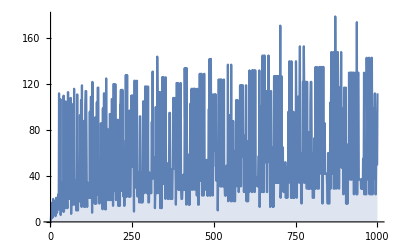

```mathematica
DiscretePlot[Length@NestWhileList[f,i,1≠#&], {i, 1, 1000}]
```

```mathematica
?f
```

Global`f

f[0]=1
 
f[1]=1
 
f[2]=1
 
f[3]=10
 
f[4]=2
 
f[5]=16
 
f[6]=3
 
f[7]=22
 
f[8]=4
 
f[9]=28
 
f[10]=5
 
f[11]=34
 
f[12]=6
 
f[13]=40
 
f[14]=7
 
f[15]=46
 
f[16]=8
 
f[17]=52
 
f[18]=9
 
f[19]=58
 
f[20]=10
 
f[21]=64
 
f[22]=11
 
f[23]=70
 
f[24]=12
 
f[25]=76
 
f[26]=13
 
f[27]=82
 
f[28]=14
 
f[29]=88
 
f[30]=15
 
f[31]=94
 
f[32]=16
 
f[33]=100
 
f[34]=17
 
f[35]=106
 
f[36]=18
 
f[37]=112
 
f[38]=19
 
f[39]=118
 
f[40]=20
 
f[41]=124
 
f[42]=21
 
f[43]=130
 
f[44]=22
 
f[45]=136
 
f[46]=23
 
f[47]=142
 
f[48]=24
 
f[49]=148
 
f[50]=25
 
f[51]=154
 
f[52]=26
 
f[53]=160
 
f[54]=27
 
f[55]=166
 
f[56]=28
 
f[57]=172
 
f[58]=29
 
f[59]=178
 
f[60]=30
 
f[61]=184
 
f[62]=31
 
f[63]=190
 
f[64]=32
 
f[65]=196
 
f[66]=33
 
f[67]=202
 
f[68]=34
 
f[69]=208
 
f[70]=35
 
f[71]=214
 
f[72]=36
 
f[73]=220
 
f[74]=37
 
f[75]=226
 
f[76]=38
 
f[77]=232
 
f[78]=39
 
f[79]=238
 
f[80]=40
 
f[81]=244
 
f[82]=41
 
f[83]=250
 
f[84]=42
 
f[85]=256
 
f[86]=43
 
f[87]=262
 
f[88]=44
 
f[89]=268
 
f[90]=45
 
f[91]=274
 
f[92]=46
 
f[93]=280
 
f[94]=47
 
f[95]=286
 
f[96]=48
 
f[97]=292
 
f[98]=49
 
f[99]=298
 
f[100]=50
 
f[101]=304
 
f[102]=51
 
f[103]=310
 
f[104]=52
 
f[105]=316
 
f[106]=53
 
f[107]=322
 
f[108]=54
 
f[109]=328
 
f[110]=55
 
f[111]=334
 
f[112]=56
 
f[113]=340
 
f[114]=57
 
f[115]=346
 
f[116]=58
 
f[117]=352
 
f[118]=59
 
f[119]=358
 
f[120]=60
 
f[121]=364
 
f[122]=61
 
f[123]=370
 
f[124]=62
 
f[125]=376
 
f[126]=63
 
f[127]=382
 
f[128]=64
 
f[129]=388
 
f[130]=65
 
f[131]=394
 
f[132]=66
 
f[133]=400
 
f[134]=67
 
f[135]=406
 
f[136]=68
 
f[137]=412
 
f[138]=69
 
f[139]=418
 
f[140]=70
 
f[141]=424
 
f[142]=71
 
f[143]=430
 
f[144]=72
 
f[145]=436
 
f[146]=73
 
f[147]=442
 
f[148]=74
 
f[149]=448
 
f[150]=75
 
f[151]=454
 
f[152]=76
 
f[153]=460
 
f[154]=77
 
f[155]=466
 
f[156]=78
 
f[157]=472
 
f[158]=79
 
f[159]=478
 
f[160]=80
 
f[161]=484
 
f[162]=81
 
f[163]=490
 
f[164]=82
 
f[165]=496
 
f[166]=83
 
f[167]=502
 
f[168]=84
 
f[169]=508
 
f[170]=85
 
f[171]=514
 
f[172]=86
 
f[173]=520
 
f[174]=87
 
f[175]=526
 
f[176]=88
 
f[177]=532
 
f[178]=89
 
f[179]=538
 
f[180]=90
 
f[181]=544
 
f[182]=91
 
f[183]=550
 
f[184]=92
 
f[185]=556
 
f[186]=93
 
f[187]=562
 
f[188]=94
 
f[189]=568
 
f[190]=95
 
f[191]=574
 
f[192]=96
 
f[193]=580
 
f[194]=97
 
f[195]=586
 
f[196]=98
 
f[197]=592
 
f[198]=99
 
f[199]=598
 
f[200]=100
 
f[201]=604
 
f[202]=101
 
f[203]=610
 
f[204]=102
 
f[205]=616
 
f[206]=103
 
f[207]=622
 
f[208]=104
 
f[209]=628
 
f[210]=105
 
f[211]=634
 
f[212]=106
 
f[213]=640
 
f[214]=107
 
f[215]=646
 
f[216]=108
 
f[217]=652
 
f[218]=109
 
f[219]=658
 
f[220]=110
 
f[221]=664
 
f[222]=111
 
f[223]=670
 
f[224]=112
 
f[225]=676
 
f[226]=113
 
f[227]=682
 
f[228]=114
 
f[229]=688
 
f[230]=115
 
f[231]=694
 
f[232]=116
 
f[233]=700
 
f[234]=117
 
f[235]=706
 
f[236]=118
 
f[237]=712
 
f[238]=119
 
f[239]=718
 
f[240]=120
 
f[241]=724
 
f[242]=121
 
f[243]=730
 
f[244]=122
 
f[245]=736
 
f[246]=123
 
f[247]=742
 
f[248]=124
 
f[249]=748
 
f[250]=125
 
f[251]=754
 
f[252]=126
 
f[253]=760
 
f[254]=127
 
f[255]=766
 
f[256]=128
 
f[257]=772
 
f[258]=129
 
f[259]=778
 
f[260]=130
 
f[261]=784
 
f[262]=131
 
f[263]=790
 
f[264]=132
 
f[265]=796
 
f[266]=133
 
f[267]=802
 
f[268]=134
 
f[269]=808
 
f[270]=135
 
f[271]=814
 
f[272]=136
 
f[273]=820
 
f[274]=137
 
f[275]=826
 
f[276]=138
 
f[277]=832
 
f[278]=139
 
f[279]=838
 
f[280]=140
 
f[281]=844
 
f[282]=141
 
f[283]=850
 
f[284]=142
 
f[285]=856
 
f[286]=143
 
f[287]=862
 
f[288]=144
 
f[289]=868
 
f[290]=145
 
f[291]=874
 
f[292]=146
 
f[293]=880
 
f[294]=147
 
f[295]=886
 
f[296]=148
 
f[297]=892
 
f[298]=149
 
f[299]=898
 
f[300]=150
 
f[301]=904
 
f[302]=151
 
f[303]=910
 
f[304]=152
 
f[305]=916
 
f[306]=153
 
f[307]=922
 
f[308]=154
 
f[309]=928
 
f[310]=155
 
f[311]=934
 
f[312]=156
 
f[313]=940
 
f[314]=157
 
f[315]=946
 
f[316]=158
 
f[317]=952
 
f[318]=159
 
f[319]=958
 
f[320]=160
 
f[321]=964
 
f[322]=161
 
f[323]=970
 
f[324]=162
 
f[325]=976
 
f[326]=163
 
f[327]=982
 
f[328]=164
 
f[329]=988
 
f[330]=165
 
f[331]=994
 
f[332]=166
 
f[333]=1000
 
f[334]=167
 
f[335]=1006
 
f[336]=168
 
f[337]=1012
 
f[338]=169
 
f[339]=1018
 
f[340]=170
 
f[341]=1024
 
f[342]=171
 
f[343]=1030
 
f[344]=172
 
f[345]=1036
 
f[346]=173
 
f[347]=1042
 
f[348]=174
 
f[349]=1048
 
f[350]=175
 
f[351]=1054
 
f[352]=176
 
f[353]=1060
 
f[354]=177
 
f[355]=1066
 
f[356]=178
 
f[357]=1072
 
f[358]=179
 
f[359]=1078
 
f[360]=180
 
f[361]=1084
 
f[362]=181
 
f[363]=1090
 
f[364]=182
 
f[365]=1096
 
f[366]=183
 
f[367]=1102
 
f[368]=184
 
f[369]=1108
 
f[370]=185
 
f[371]=1114
 
f[372]=186
 
f[373]=1120
 
f[374]=187
 
f[375]=1126
 
f[376]=188
 
f[377]=1132
 
f[378]=189
 
f[379]=1138
 
f[380]=190
 
f[381]=1144
 
f[382]=191
 
f[383]=1150
 
f[384]=192
 
f[385]=1156
 
f[386]=193
 
f[387]=1162
 
f[388]=194
 
f[389]=1168
 
f[390]=195
 
f[391]=1174
 
f[392]=196
 
f[393]=1180
 
f[394]=197
 
f[395]=1186
 
f[396]=198
 
f[397]=1192
 
f[398]=199
 
f[399]=1198
 
f[400]=200
 
f[401]=1204
 
f[402]=201
 
f[403]=1210
 
f[404]=202
 
f[405]=1216
 
f[406]=203
 
f[407]=1222
 
f[408]=204
 
f[409]=1228
 
f[410]=205
 
f[411]=1234
 
f[412]=206
 
f[413]=1240
 
f[414]=207
 
f[415]=1246
 
f[416]=208
 
f[417]=1252
 
f[418]=209
 
f[419]=1258
 
f[420]=210
 
f[421]=1264
 
f[422]=211
 
f[423]=1270
 
f[424]=212
 
f[425]=1276
 
f[426]=213
 
f[427]=1282
 
f[428]=214
 
f[429]=1288
 
f[430]=215
 
f[431]=1294
 
f[432]=216
 
f[433]=1300
 
f[434]=217
 
f[435]=1306
 
f[436]=218
 
f[437]=1312
 
f[438]=219
 
f[439]=1318
 
f[440]=220
 
f[441]=1324
 
f[442]=221
 
f[443]=1330
 
f[444]=222
 
f[445]=1336
 
f[446]=223
 
f[447]=1342
 
f[448]=224
 
f[449]=1348
 
f[450]=225
 
f[451]=1354
 
f[452]=226
 
f[453]=1360
 
f[454]=227
 
f[455]=1366
 
f[456]=228
 
f[457]=1372
 
f[458]=229
 
f[459]=1378
 
f[460]=230
 
f[461]=1384
 
f[462]=231
 
f[463]=1390
 
f[464]=232
 
f[465]=1396
 
f[466]=233
 
f[467]=1402
 
f[468]=234
 
f[469]=1408
 
f[470]=235
 
f[471]=1414
 
f[472]=236
 
f[473]=1420
 
f[474]=237
 
f[475]=1426
 
f[476]=238
 
f[477]=1432
 
f[478]=239
 
f[479]=1438
 
f[480]=240
 
f[481]=1444
 
f[482]=241
 
f[483]=1450
 
f[484]=242
 
f[485]=1456
 
f[486]=243
 
f[487]=1462
 
f[488]=244
 
f[489]=1468
 
f[490]=245
 
f[491]=1474
 
f[492]=246
 
f[493]=1480
 
f[494]=247
 
f[495]=1486
 
f[496]=248
 
f[497]=1492
 
f[498]=249
 
f[499]=1498
 
f[500]=250
 
f[501]=1504
 
f[502]=251
 
f[503]=1510
 
f[504]=252
 
f[505]=1516
 
f[506]=253
 
f[507]=1522
 
f[508]=254
 
f[509]=1528
 
f[510]=255
 
f[511]=1534
 
f[512]=256
 
f[513]=1540
 
f[514]=257
 
f[515]=1546
 
f[516]=258
 
f[517]=1552
 
f[518]=259
 
f[519]=1558
 
f[520]=260
 
f[521]=1564
 
f[522]=261
 
f[523]=1570
 
f[524]=262
 
f[525]=1576
 
f[526]=263
 
f[527]=1582
 
f[528]=264
 
f[529]=1588
 
f[530]=265
 
f[531]=1594
 
f[532]=266
 
f[533]=1600
 
f[534]=267
 
f[535]=1606
 
f[536]=268
 
f[537]=1612
 
f[538]=269
 
f[539]=1618
 
f[540]=270
 
f[541]=1624
 
f[542]=271
 
f[543]=1630
 
f[544]=272
 
f[545]=1636
 
f[546]=273
 
f[547]=1642
 
f[548]=274
 
f[549]=1648
 
f[550]=275
 
f[551]=1654
 
f[552]=276
 
f[553]=1660
 
f[554]=277
 
f[555]=1666
 
f[556]=278
 
f[557]=1672
 
f[558]=279
 
f[559]=1678
 
f[560]=280
 
f[561]=1684
 
f[562]=281
 
f[563]=1690
 
f[564]=282
 
f[565]=1696
 
f[566]=283
 
f[567]=1702
 
f[568]=284
 
f[569]=1708
 
f[570]=285
 
f[571]=1714
 
f[572]=286
 
f[573]=1720
 
f[574]=287
 
f[575]=1726
 
f[576]=288
 
f[577]=1732
 
f[578]=289
 
f[579]=1738
 
f[580]=290
 
f[581]=1744
 
f[582]=291
 
f[583]=1750
 
f[584]=292
 
f[585]=1756
 
f[586]=293
 
f[587]=1762
 
f[588]=294
 
f[589]=1768
 
f[590]=295
 
f[591]=1774
 
f[592]=296
 
f[593]=1780
 
f[594]=297
 
f[595]=1786
 
f[596]=298
 
f[597]=1792
 
f[598]=299
 
f[599]=1798
 
f[600]=300
 
f[601]=1804
 
f[602]=301
 
f[603]=1810
 
f[604]=302
 
f[605]=1816
 
f[606]=303
 
f[607]=1822
 
f[608]=304
 
f[609]=1828
 
f[610]=305
 
f[611]=1834
 
f[612]=306
 
f[613]=1840
 
f[614]=307
 
f[615]=1846
 
f[616]=308
 
f[617]=1852
 
f[618]=309
 
f[619]=1858
 
f[620]=310
 
f[621]=1864
 
f[622]=311
 
f[623]=1870
 
f[624]=312
 
f[625]=1876
 
f[626]=313
 
f[627]=1882
 
f[628]=314
 
f[629]=1888
 
f[630]=315
 
f[631]=1894
 
f[632]=316
 
f[633]=1900
 
f[634]=317
 
f[635]=1906
 
f[636]=318
 
f[637]=1912
 
f[638]=319
 
f[639]=1918
 
f[640]=320
 
f[641]=1924
 
f[642]=321
 
f[643]=1930
 
f[644]=322
 
f[645]=1936
 
f[646]=323
 
f[647]=1942
 
f[648]=324
 
f[649]=1948
 
f[650]=325
 
f[651]=1954
 
f[652]=326
 
f[653]=1960
 
f[654]=327
 
f[655]=1966
 
f[656]=328
 
f[657]=1972
 
f[658]=329
 
f[659]=1978
 
f[660]=330
 
f[661]=1984
 
f[662]=331
 
f[663]=1990
 
f[664]=332
 
f[665]=1996
 
f[666]=333
 
f[667]=2002
 
f[668]=334
 
f[669]=2008
 
f[670]=335
 
f[671]=2014
 
f[672]=336
 
f[673]=2020
 
f[674]=337
 
f[675]=2026
 
f[676]=338
 
f[677]=2032
 
f[678]=339
 
f[679]=2038
 
f[680]=340
 
f[681]=2044
 
f[682]=341
 
f[683]=2050
 
f[684]=342
 
f[685]=2056
 
f[686]=343
 
f[687]=2062
 
f[688]=344
 
f[689]=2068
 
f[690]=345
 
f[691]=2074
 
f[692]=346
 
f[693]=2080
 
f[694]=347
 
f[695]=2086
 
f[696]=348
 
f[697]=2092
 
f[698]=349
 
f[699]=2098
 
f[700]=350
 
f[701]=2104
 
f[702]=351
 
f[703]=2110
 
f[704]=352
 
f[705]=2116
 
f[706]=353
 
f[707]=2122
 
f[708]=354
 
f[709]=2128
 
f[710]=355
 
f[711]=2134
 
f[712]=356
 
f[713]=2140
 
f[714]=357
 
f[715]=2146
 
f[716]=358
 
f[717]=2152
 
f[718]=359
 
f[719]=2158
 
f[720]=360
 
f[721]=2164
 
f[722]=361
 
f[723]=2170
 
f[724]=362
 
f[725]=2176
 
f[726]=363
 
f[727]=2182
 
f[728]=364
 
f[729]=2188
 
f[730]=365
 
f[731]=2194
 
f[732]=366
 
f[733]=2200
 
f[734]=367
 
f[735]=2206
 
f[736]=368
 
f[737]=2212
 
f[738]=369
 
f[739]=2218
 
f[740]=370
 
f[741]=2224
 
f[742]=371
 
f[743]=2230
 
f[744]=372
 
f[745]=2236
 
f[746]=373
 
f[747]=2242
 
f[748]=374
 
f[749]=2248
 
f[750]=375
 
f[751]=2254
 
f[752]=376
 
f[753]=2260
 
f[754]=377
 
f[755]=2266
 
f[756]=378
 
f[757]=2272
 
f[758]=379
 
f[759]=2278
 
f[760]=380
 
f[761]=2284
 
f[762]=381
 
f[763]=2290
 
f[764]=382
 
f[765]=2296
 
f[766]=383
 
f[767]=2302
 
f[768]=384
 
f[769]=2308
 
f[770]=385
 
f[771]=2314
 
f[772]=386
 
f[773]=2320
 
f[774]=387
 
f[775]=2326
 
f[776]=388
 
f[777]=2332
 
f[778]=389
 
f[779]=2338
 
f[780]=390
 
f[781]=2344
 
f[782]=391
 
f[783]=2350
 
f[784]=392
 
f[785]=2356
 
f[786]=393
 
f[787]=2362
 
f[788]=394
 
f[789]=2368
 
f[790]=395
 
f[791]=2374
 
f[792]=396
 
f[793]=2380
 
f[794]=397
 
f[795]=2386
 
f[796]=398
 
f[797]=2392
 
f[798]=399
 
f[799]=2398
 
f[800]=400
 
f[801]=2404
 
f[802]=401
 
f[803]=2410
 
f[804]=402
 
f[805]=2416
 
f[806]=403
 
f[807]=2422
 
f[808]=404
 
f[809]=2428
 
f[810]=405
 
f[811]=2434
 
f[812]=406
 
f[813]=2440
 
f[814]=407
 
f[815]=2446
 
f[816]=408
 
f[817]=2452
 
f[818]=409
 
f[819]=2458
 
f[820]=410
 
f[821]=2464
 
f[822]=411
 
f[823]=2470
 
f[824]=412
 
f[825]=2476
 
f[826]=413
 
f[827]=2482
 
f[828]=414
 
f[829]=2488
 
f[830]=415
 
f[831]=2494
 
f[832]=416
 
f[833]=2500
 
f[834]=417
 
f[835]=2506
 
f[836]=418
 
f[837]=2512
 
f[838]=419
 
f[839]=2518
 
f[840]=420
 
f[841]=2524
 
f[842]=421
 
f[843]=2530
 
f[844]=422
 
f[845]=2536
 
f[846]=423
 
f[847]=2542
 
f[848]=424
 
f[849]=2548
 
f[850]=425
 
f[851]=2554
 
f[852]=426
 
f[853]=2560
 
f[854]=427
 
f[855]=2566
 
f[856]=428
 
f[857]=2572
 
f[858]=429
 
f[859]=2578
 
f[860]=430
 
f[861]=2584
 
f[862]=431
 
f[863]=2590
 
f[864]=432
 
f[865]=2596
 
f[866]=433
 
f[867]=2602
 
f[868]=434
 
f[869]=2608
 
f[870]=435
 
f[871]=2614
 
f[872]=436
 
f[873]=2620
 
f[874]=437
 
f[875]=2626
 
f[876]=438
 
f[877]=2632
 
f[878]=439
 
f[879]=2638
 
f[880]=440
 
f[881]=2644
 
f[882]=441
 
f[883]=2650
 
f[884]=442
 
f[885]=2656
 
f[886]=443
 
f[887]=2662
 
f[888]=444
 
f[889]=2668
 
f[890]=445
 
f[891]=2674
 
f[892]=446
 
f[893]=2680
 
f[894]=447
 
f[895]=2686
 
f[896]=448
 
f[897]=2692
 
f[898]=449
 
f[899]=2698
 
f[900]=450
 
f[901]=2704
 
f[902]=451
 
f[903]=2710
 
f[904]=452
 
f[905]=2716
 
f[906]=453
 
f[907]=2722
 
f[908]=454
 
f[909]=2728
 
f[910]=455
 
f[911]=2734
 
f[912]=456
 
f[913]=2740
 
f[914]=457
 
f[915]=2746
 
f[916]=458
 
f[917]=2752
 
f[918]=459
 
f[919]=2758
 
f[920]=460
 
f[921]=2764
 
f[922]=461
 
f[923]=2770
 
f[924]=462
 
f[925]=2776
 
f[926]=463
 
f[927]=2782
 
f[928]=464
 
f[929]=2788
 
f[930]=465
 
f[931]=2794
 
f[932]=466
 
f[933]=2800
 
f[934]=467
 
f[935]=2806
 
f[936]=468
 
f[937]=2812
 
f[938]=469
 
f[939]=2818
 
f[940]=470
 
f[941]=2824
 
f[942]=471
 
f[943]=2830
 
f[944]=472
 
f[945]=2836
 
f[946]=473
 
f[947]=2842
 
f[948]=474
 
f[949]=2848
 
f[950]=475
 
f[951]=2854
 
f[952]=476
 
f[953]=2860
 
f[954]=477
 
f[955]=2866
 
f[956]=478
 
f[957]=2872
 
f[958]=479
 
f[959]=2878
 
f[960]=480
 
f[961]=2884
 
f[962]=481
 
f[963]=2890
 
f[964]=482
 
f[965]=2896
 
f[966]=483
 
f[967]=2902
 
f[968]=484
 
f[969]=2908
 
f[970]=485
 
f[971]=2914
 
f[972]=486
 
f[973]=2920
 
f[974]=487
 
f[975]=2926
 
f[976]=488
 
f[977]=2932
 
f[978]=489
 
f[979]=2938
 
f[980]=490
 
f[981]=2944
 
f[982]=491
 
f[983]=2950
 
f[984]=492
 
f[985]=2956
 
f[986]=493
 
f[987]=2962
 
f[988]=494
 
f[989]=2968
 
f[990]=495
 
f[991]=2974
 
f[992]=496
 
f[993]=2980
 
f[994]=497
 
f[995]=2986
 
f[996]=498
 
f[997]=2992
 
f[998]=499
 
f[999]=2998
 
f[1000]=500
 
f[1001]=3004
 
f[1002]=501
 
f[1003]=3010
 
f[1004]=502
 
f[1005]=3016
 
f[1006]=503
 
f[1007]=3022
 
f[1008]=504
 
f[1009]=3028
 
f[1010]=505
 
f[1011]=3034
 
f[1012]=506
 
f[1013]=3040
 
f[1014]=507
 
f[1015]=3046
 
f[1016]=508
 
f[1017]=3052
 
f[1018]=509
 
f[1019]=3058
 
f[1020]=510
 
f[1021]=3064
 
f[1022]=511
 
f[1023]=3070
 
f[1024]=512
 
f[1025]=3076
 
f[1026]=513
 
f[1027]=3082
 
f[1028]=514
 
f[1029]=3088
 
f[1030]=515
 
f[1031]=3094
 
f[1032]=516
 
f[1033]=3100
 
f[1034]=517
 
f[1035]=3106
 
f[1036]=518
 
f[1037]=3112
 
f[1038]=519
 
f[1039]=3118
 
f[1040]=520
 
f[1041]=3124
 
f[1042]=521
 
f[1043]=3130
 
f[1044]=522
 
f[1045]=3136
 
f[1046]=523
 
f[1047]=3142
 
f[1048]=524
 
f[1049]=3148
 
f[1050]=525
 
f[1051]=3154
 
f[1052]=526
 
f[1053]=3160
 
f[1054]=527
 
f[1055]=3166
 
f[1056]=528
 
f[1057]=3172
 
f[1058]=529
 
f[1059]=3178
 
f[1060]=530
 
f[1061]=3184
 
f[1062]=531
 
f[1063]=3190
 
f[1064]=532
 
f[1065]=3196
 
f[1066]=533
 
f[1067]=3202
 
f[1068]=534
 
f[1069]=3208
 
f[1070]=535
 
f[1071]=3214
 
f[1072]=536
 
f[1073]=3220
 
f[1074]=537
 
f[1075]=3226
 
f[1076]=538
 
f[1077]=3232
 
f[1078]=539
 
f[1079]=3238
 
f[1080]=540
 
f[1081]=3244
 
f[1082]=541
 
f[1083]=3250
 
f[1084]=542
 
f[1085]=3256
 
f[1086]=543
 
f[1087]=3262
 
f[1088]=544
 
f[1089]=3268
 
f[1090]=545
 
f[1091]=3274
 
f[1092]=546
 
f[1093]=3280
 
f[1094]=547
 
f[1095]=3286
 
f[1096]=548
 
f[1097]=3292
 
f[1098]=549
 
f[1099]=3298
 
f[1100]=550
 
f[1101]=3304
 
f[1102]=551
 
f[1103]=3310
 
f[1104]=552
 
f[1105]=3316
 
f[1106]=553
 
f[1107]=3322
 
f[1108]=554
 
f[1109]=3328
 
f[1110]=555
 
f[1111]=3334
 
f[1112]=556
 
f[1113]=3340
 
f[1114]=557
 
f[1115]=3346
 
f[1116]=558
 
f[1117]=3352
 
f[1118]=559
 
f[1119]=3358
 
f[1120]=560
 
f[1121]=3364
 
f[1122]=561
 
f[1123]=3370
 
f[1124]=562
 
f[1125]=3376
 
f[1126]=563
 
f[1127]=3382
 
f[1128]=564
 
f[1129]=3388
 
f[1130]=565
 
f[1131]=3394
 
f[1132]=566
 
f[1133]=3400
 
f[1134]=567
 
f[1135]=3406
 
f[1136]=568
 
f[1137]=3412
 
f[1138]=569
 
f[1139]=3418
 
f[1140]=570
 
f[1141]=3424
 
f[1142]=571
 
f[1143]=3430
 
f[1144]=572
 
f[1145]=3436
 
f[1146]=573
 
f[1147]=3442
 
f[1148]=574
 
f[1149]=3448
 
f[1150]=575
 
f[1151]=3454
 
f[1152]=576
 
f[1153]=3460
 
f[1154]=577
 
f[1155]=3466
 
f[1156]=578
 
f[1157]=3472
 
f[1158]=579
 
f[1159]=3478
 
f[1160]=580
 
f[1161]=3484
 
f[1162]=581
 
f[1163]=3490
 
f[1164]=582
 
f[1165]=3496
 
f[1166]=583
 
f[1167]=3502
 
f[1168]=584
 
f[1169]=3508
 
f[1170]=585
 
f[1171]=3514
 
f[1172]=586
 
f[1173]=3520
 
f[1174]=587
 
f[1175]=3526
 
f[1176]=588
 
f[1177]=3532
 
f[1178]=589
 
f[1179]=3538
 
f[1180]=590
 
f[1181]=3544
 
f[1182]=591
 
f[1183]=3550
 
f[1184]=592
 
f[1185]=3556
 
f[1186]=593
 
f[1187]=3562
 
f[1188]=594
 
f[1189]=3568
 
f[1190]=595
 
f[1191]=3574
 
f[1192]=596
 
f[1193]=3580
 
f[1194]=597
 
f[1195]=3586
 
f[1196]=598
 
f[1197]=3592
 
f[1198]=599
 
f[1199]=3598
 
f[1200]=600
 
f[1201]=3604
 
f[1202]=601
 
f[1203]=3610
 
f[1204]=602
 
f[1205]=3616
 
f[1206]=603
 
f[1207]=3622
 
f[1208]=604
 
f[1209]=3628
 
f[1210]=605
 
f[1211]=3634
 
f[1212]=606
 
f[1213]=3640
 
f[1214]=607
 
f[1215]=3646
 
f[1216]=608
 
f[1217]=3652
 
f[1218]=609
 
f[1219]=3658
 
f[1220]=610
 
f[1221]=3664
 
f[1222]=611
 
f[1223]=3670
 
f[1224]=612
 
f[1225]=3676
 
f[1226]=613
 
f[1227]=3682
 
f[1228]=614
 
f[1229]=3688
 
f[1230]=615
 
f[1231]=3694
 
f[1232]=616
 
f[1233]=3700
 
f[1234]=617
 
f[1235]=3706
 
f[1236]=618
 
f[1237]=3712
 
f[1238]=619
 
f[1239]=3718
 
f[1240]=620
 
f[1241]=3724
 
f[1242]=621
 
f[1243]=3730
 
f[1244]=622
 
f[1245]=3736
 
f[1246]=623
 
f[1247]=3742
 
f[1248]=624
 
f[1249]=3748
 
f[1250]=625
 
f[1251]=3754
 
f[1252]=626
 
f[1253]=3760
 
f[1254]=627
 
f[1255]=3766
 
f[1256]=628
 
f[1257]=3772
 
f[1258]=629
 
f[1259]=3778
 
f[1260]=630
 
f[1261]=3784
 
f[1262]=631
 
f[1263]=3790
 
f[1264]=632
 
f[1265]=3796
 
f[1266]=633
 
f[1267]=3802
 
f[1268]=634
 
f[1269]=3808
 
f[1270]=635
 
f[1271]=3814
 
f[1272]=636
 
f[1273]=3820
 
f[1274]=637
 
f[1275]=3826
 
f[1276]=638
 
f[1277]=3832
 
f[1278]=639
 
f[1279]=3838
 
f[1280]=640
 
f[1281]=3844
 
f[1282]=641
 
f[1283]=3850
 
f[1284]=642
 
f[1285]=3856
 
f[1286]=643
 
f[1287]=3862
 
f[1288]=644
 
f[1289]=3868
 
f[1290]=645
 
f[1291]=3874
 
f[1292]=646
 
f[1293]=3880
 
f[1294]=647
 
f[1295]=3886
 
f[1296]=648
 
f[1297]=3892
 
f[1298]=649
 
f[1299]=3898
 
f[1300]=650
 
f[1301]=3904
 
f[1302]=651
 
f[1303]=3910
 
f[1304]=652
 
f[1305]=3916
 
f[1306]=653
 
f[1307]=3922
 
f[1308]=654
 
f[1309]=3928
 
f[1310]=655
 
f[1311]=3934
 
f[1312]=656
 
f[1313]=3940
 
f[1314]=657
 
f[1315]=3946
 
f[1316]=658
 
f[1317]=3952
 
f[1318]=659
 
f[1319]=3958
 
f[1320]=660
 
f[1321]=3964
 
f[1322]=661
 
f[1323]=3970
 
f[1324]=662
 
f[1325]=3976
 
f[1326]=663
 
f[1327]=3982
 
f[1328]=664
 
f[1329]=3988
 
f[1330]=665
 
f[1331]=3994
 
f[1332]=666
 
f[1333]=4000
 
f[1334]=667
 
f[1335]=4006
 
f[1336]=668
 
f[1337]=4012
 
f[1338]=669
 
f[1339]=4018
 
f[1340]=670
 
f[1341]=4024
 
f[1342]=671
 
f[1343]=4030
 
f[1344]=672
 
f[1345]=4036
 
f[1346]=673
 
f[1347]=4042
 
f[1348]=674
 
f[1349]=4048
 
f[1350]=675
 
f[1351]=4054
 
f[1352]=676
 
f[1353]=4060
 
f[1354]=677
 
f[1355]=4066
 
f[1356]=678
 
f[1357]=4072
 
f[1358]=679
 
f[1359]=4078
 
f[1360]=680
 
f[1361]=4084
 
f[1362]=681
 
f[1363]=4090
 
f[1364]=682
 
f[1365]=4096
 
f[1366]=683
 
f[1367]=4102
 
f[1368]=684
 
f[1369]=4108
 
f[1370]=685
 
f[1371]=4114
 
f[1372]=686
 
f[1373]=4120
 
f[1374]=687
 
f[1375]=4126
 
f[1376]=688
 
f[1377]=4132
 
f[1378]=689
 
f[1379]=4138
 
f[1380]=690
 
f[1381]=4144
 
f[1382]=691
 
f[1383]=4150
 
f[1384]=692
 
f[1385]=4156
 
f[1386]=693
 
f[1387]=4162
 
f[1388]=694
 
f[1389]=4168
 
f[1390]=695
 
f[1391]=4174
 
f[1392]=696
 
f[1393]=4180
 
f[1394]=697
 
f[1395]=4186
 
f[1396]=698
 
f[1397]=4192
 
f[1398]=699
 
f[1399]=4198
 
f[1400]=700
 
f[1401]=4204
 
f[1402]=701
 
f[1403]=4210
 
f[1404]=702
 
f[1405]=4216
 
f[1406]=703
 
f[1407]=4222
 
f[1408]=704
 
f[1409]=4228
 
f[1410]=705
 
f[1411]=4234
 
f[1412]=706
 
f[1413]=4240
 
f[1414]=707
 
f[1415]=4246
 
f[1416]=708
 
f[1417]=4252
 
f[1418]=709
 
f[1419]=4258
 
f[1420]=710
 
f[1421]=4264
 
f[1422]=711
 
f[1423]=4270
 
f[1424]=712
 
f[1425]=4276
 
f[1426]=713
 
f[1427]=4282
 
f[1428]=714
 
f[1429]=4288
 
f[1430]=715
 
f[1431]=4294
 
f[1432]=716
 
f[1433]=4300
 
f[1434]=717
 
f[1435]=4306
 
f[1436]=718
 
f[1437]=4312
 
f[1438]=719
 
f[1439]=4318
 
f[1440]=720
 
f[1441]=4324
 
f[1442]=721
 
f[1443]=4330
 
f[1444]=722
 
f[1445]=4336
 
f[1446]=723
 
f[1447]=4342
 
f[1448]=724
 
f[1449]=4348
 
f[1450]=725
 
f[1451]=4354
 
f[1452]=726
 
f[1453]=4360
 
f[1454]=727
 
f[1455]=4366
 
f[1456]=728
 
f[1457]=4372
 
f[1458]=729
 
f[1459]=4378
 
f[1460]=730
 
f[1461]=4384
 
f[1462]=731
 
f[1463]=4390
 
f[1464]=732
 
f[1465]=4396
 
f[1466]=733
 
f[1467]=4402
 
f[1468]=734
 
f[1469]=4408
 
f[1470]=735
 
f[1471]=4414
 
f[1472]=736
 
f[1473]=4420
 
f[1474]=737
 
f[1475]=4426
 
f[1476]=738
 
f[1477]=4432
 
f[1478]=739
 
f[1479]=4438
 
f[1480]=740
 
f[1481]=4444
 
f[1482]=741
 
f[1483]=4450
 
f[1484]=742
 
f[1485]=4456
 
f[1486]=743
 
f[1487]=4462
 
f[1488]=744
 
f[1489]=4468
 
f[1490]=745
 
f[1491]=4474
 
f[1492]=746
 
f[1493]=4480
 
f[1494]=747
 
f[1495]=4486
 
f[1496]=748
 
f[1497]=4492
 
f[1498]=749
 
f[1499]=4498
 
f[1500]=750
 
f[1501]=4504
 
f[1502]=751
 
f[1503]=4510
 
f[1504]=752
 
f[1505]=4516
 
f[1506]=753
 
f[1507]=4522
 
f[1508]=754
 
f[1509]=4528
 
f[1510]=755
 
f[1511]=4534
 
f[1512]=756
 
f[1513]=4540
 
f[1514]=757
 
f[1515]=4546
 
f[1516]=758
 
f[1517]=4552
 
f[1518]=759
 
f[1519]=4558
 
f[1520]=760
 
f[1521]=4564
 
f[1522]=761
 
f[1523]=4570
 
f[1524]=762
 
f[1525]=4576
 
f[1526]=763
 
f[1527]=4582
 
f[1528]=764
 
f[1529]=4588
 
f[1530]=765
 
f[1531]=4594
 
f[1532]=766
 
f[1533]=4600
 
f[1534]=767
 
f[1535]=4606
 
f[1536]=768
 
f[1537]=4612
 
f[1538]=769
 
f[1539]=4618
 
f[1540]=770
 
f[1541]=4624
 
f[1542]=771
 
f[1543]=4630
 
f[1544]=772
 
f[1545]=4636
 
f[1546]=773
 
f[1547]=4642
 
f[1548]=774
 
f[1549]=4648
 
f[1550]=775
 
f[1551]=4654
 
f[1552]=776
 
f[1553]=4660
 
f[1554]=777
 
f[1555]=4666
 
f[1556]=778
 
f[1557]=4672
 
f[1558]=779
 
f[1559]=4678
 
f[1560]=780
 
f[1561]=4684
 
f[1562]=781
 
f[1563]=4690
 
f[1564]=782
 
f[1565]=4696
 
f[1566]=783
 
f[1567]=4702
 
f[1568]=784
 
f[1569]=4708
 
f[1570]=785
 
f[1571]=4714
 
f[1572]=786
 
f[1573]=4720
 
f[1574]=787
 
f[1575]=4726
 
f[1576]=788
 
f[1577]=4732
 
f[1578]=789
 
f[1579]=4738
 
f[1580]=790
 
f[1581]=4744
 
f[1582]=791
 
f[1583]=4750
 
f[1584]=792
 
f[1585]=4756
 
f[1586]=793
 
f[1587]=4762
 
f[1588]=794
 
f[1589]=4768
 
f[1590]=795
 
f[1591]=4774
 
f[1592]=796
 
f[1593]=4780
 
f[1594]=797
 
f[1595]=4786
 
f[1596]=798
 
f[1597]=4792
 
f[1598]=799
 
f[1599]=4798
 
f[1600]=800
 
f[1601]=4804
 
f[1602]=801
 
f[1603]=4810
 
f[1604]=802
 
f[1605]=4816
 
f[1606]=803
 
f[1607]=4822
 
f[1608]=804
 
f[1609]=4828
 
f[1610]=805
 
f[1611]=4834
 
f[1612]=806
 
f[1613]=4840
 
f[1614]=807
 
f[1615]=4846
 
f[1616]=808
 
f[1617]=4852
 
f[1618]=809
 
f[1619]=4858
 
f[1620]=810
 
f[1621]=4864
 
f[1622]=811
 
f[1623]=4870
 
f[1624]=812
 
f[1625]=4876
 
f[1626]=813
 
f[1627]=4882
 
f[1628]=814
 
f[1629]=4888
 
f[1630]=815
 
f[1631]=4894
 
f[1632]=816
 
f[1633]=4900
 
f[1634]=817
 
f[1635]=4906
 
f[1636]=818
 
f[1637]=4912
 
f[1638]=819
 
f[1639]=4918
 
f[1640]=820
 
f[1641]=4924
 
f[1642]=821
 
f[1643]=4930
 
f[1644]=822
 
f[1645]=4936
 
f[1646]=823
 
f[1647]=4942
 
f[1648]=824
 
f[1649]=4948
 
f[1650]=825
 
f[1651]=4954
 
f[1652]=826
 
f[1653]=4960
 
f[1654]=827
 
f[1655]=4966
 
f[1656]=828
 
f[1657]=4972
 
f[1658]=829
 
f[1659]=4978
 
f[1660]=830
 
f[1661]=4984
 
f[1662]=831
 
f[1663]=4990
 
f[1664]=832
 
f[1665]=4996
 
f[1666]=833
 
f[1667]=5002
 
f[1668]=834
 
f[1669]=5008
 
f[1670]=835
 
f[1671]=5014
 
f[1672]=836
 
f[1673]=5020
 
f[1674]=837
 
f[1675]=5026
 
f[1676]=838
 
f[1677]=5032
 
f[1678]=839
 
f[1679]=5038
 
f[1680]=840
 
f[1681]=5044
 
f[1682]=841
 
f[1683]=5050
 
f[1684]=842
 
f[1685]=5056
 
f[1686]=843
 
f[1687]=5062
 
f[1688]=844
 
f[1689]=5068
 
f[1690]=845
 
f[1691]=5074
 
f[1692]=846
 
f[1693]=5080
 
f[1694]=847
 
f[1695]=5086
 
f[1696]=848
 
f[1697]=5092
 
f[1698]=849
 
f[1699]=5098
 
f[1700]=850
 
f[1701]=5104
 
f[1702]=851
 
f[1703]=5110
 
f[1704]=852
 
f[1705]=5116
 
f[1706]=853
 
f[1707]=5122
 
f[1708]=854
 
f[1709]=5128
 
f[1710]=855
 
f[1711]=5134
 
f[1712]=856
 
f[1713]=5140
 
f[1714]=857
 
f[1715]=5146
 
f[1716]=858
 
f[1717]=5152
 
f[1718]=859
 
f[1719]=5158
 
f[1720]=860
 
f[1721]=5164
 
f[1722]=861
 
f[1723]=5170
 
f[1724]=862
 
f[1725]=5176
 
f[1726]=863
 
f[1727]=5182
 
f[1728]=864
 
f[1729]=5188
 
f[1730]=865
 
f[1731]=5194
 
f[1732]=866
 
f[1733]=5200
 
f[1734]=867
 
f[1735]=5206
 
f[1736]=868
 
f[1737]=5212
 
f[1738]=869
 
f[1739]=5218
 
f[1740]=870
 
f[1741]=5224
 
f[1742]=871
 
f[1743]=5230
 
f[1744]=872
 
f[1745]=5236
 
f[1746]=873
 
f[1747]=5242
 
f[1748]=874
 
f[1749]=5248
 
f[1750]=875
 
f[1751]=5254
 
f[1752]=876
 
f[1753]=5260
 
f[1754]=877
 
f[1755]=5266
 
f[1756]=878
 
f[1757]=5272
 
f[1758]=879
 
f[1759]=5278
 
f[1760]=880
 
f[1761]=5284
 
f[1762]=881
 
f[1763]=5290
 
f[1764]=882
 
f[1765]=5296
 
f[1766]=883
 
f[1767]=5302
 
f[1768]=884
 
f[1769]=5308
 
f[1770]=885
 
f[1771]=5314
 
f[1772]=886
 
f[1773]=5320
 
f[1774]=887
 
f[1775]=5326
 
f[1776]=888
 
f[1777]=5332
 
f[1778]=889
 
f[1779]=5338
 
f[1780]=890
 
f[1781]=5344
 
f[1782]=891
 
f[1783]=5350
 
f[1784]=892
 
f[1785]=5356
 
f[1786]=893
 
f[1787]=5362
 
f[1788]=894
 
f[1789]=5368
 
f[1790]=895
 
f[1791]=5374
 
f[1792]=896
 
f[1793]=5380
 
f[1794]=897
 
f[1795]=5386
 
f[1796]=898
 
f[1797]=5392
 
f[1798]=899
 
f[1799]=5398
 
f[1800]=900
 
f[1801]=5404
 
f[1802]=901
 
f[1803]=5410
 
f[1804]=902
 
f[1805]=5416
 
f[1806]=903
 
f[1807]=5422
 
f[1808]=904
 
f[1809]=5428
 
f[1810]=905
 
f[1811]=5434
 
f[1812]=906
 
f[1813]=5440
 
f[1814]=907
 
f[1815]=5446
 
f[1816]=908
 
f[1817]=5452
 
f[1818]=909
 
f[1819]=5458
 
f[1820]=910
 
f[1821]=5464
 
f[1822]=911
 
f[1823]=5470
 
f[1824]=912
 
f[1825]=5476
 
f[1826]=913
 
f[1827]=5482
 
f[1828]=914
 
f[1829]=5488
 
f[1830]=915
 
f[1831]=5494
 
f[1832]=916
 
f[1833]=5500
 
f[1834]=917
 
f[1835]=5506
 
f[1836]=918
 
f[1837]=5512
 
f[1838]=919
 
f[1839]=5518
 
f[1840]=920
 
f[1841]=5524
 
f[1842]=921
 
f[1843]=5530
 
f[1844]=922
 
f[1845]=5536
 
f[1846]=923
 
f[1847]=5542
 
f[1848]=924
 
f[1849]=5548
 
f[1850]=925
 
f[1851]=5554
 
f[1852]=926
 
f[1853]=5560
 
f[1854]=927
 
f[1855]=5566
 
f[1856]=928
 
f[1857]=5572
 
f[1858]=929
 
f[1859]=5578
 
f[1860]=930
 
f[1861]=5584
 
f[1862]=931
 
f[1863]=5590
 
f[1864]=932
 
f[1865]=5596
 
f[1866]=933
 
f[1867]=5602
 
f[1868]=934
 
f[1869]=5608
 
f[1870]=935
 
f[1871]=5614
 
f[1872]=936
 
f[1873]=5620
 
f[1874]=937
 
f[1875]=5626
 
f[1876]=938
 
f[1877]=5632
 
f[1878]=939
 
f[1879]=5638
 
f[1880]=940
 
f[1881]=5644
 
f[1882]=941
 
f[1883]=5650
 
f[1884]=942
 
f[1885]=5656
 
f[1886]=943
 
f[1887]=5662
 
f[1888]=944
 
f[1889]=5668
 
f[1890]=945
 
f[1891]=5674
 
f[1892]=946
 
f[1893]=5680
 
f[1894]=947
 
f[1895]=5686
 
f[1896]=948
 
f[1897]=5692
 
f[1898]=949
 
f[1899]=5698
 
f[1900]=950
 
f[1901]=5704
 
f[1902]=951
 
f[1903]=5710
 
f[1904]=952
 
f[1905]=5716
 
f[1906]=953
 
f[1907]=5722
 
f[1908]=954
 
f[1909]=5728
 
f[1910]=955
 
f[1911]=5734
 
f[1912]=956
 
f[1913]=5740
 
f[1914]=957
 
f[1915]=5746
 
f[1916]=958
 
f[1917]=5752
 
f[1918]=959
 
f[1919]=5758
 
f[1920]=960
 
f[1921]=5764
 
f[1922]=961
 
f[1923]=5770
 
f[1924]=962
 
f[1925]=5776
 
f[1926]=963
 
f[1927]=5782
 
f[1928]=964
 
f[1929]=5788
 
f[1930]=965
 
f[1931]=5794
 
f[1932]=966
 
f[1933]=5800
 
f[1934]=967
 
f[1935]=5806
 
f[1936]=968
 
f[1937]=5812
 
f[1938]=969
 
f[1939]=5818
 
f[1940]=970
 
f[1941]=5824
 
f[1942]=971
 
f[1943]=5830
 
f[1944]=972
 
f[1945]=5836
 
f[1946]=973
 
f[1947]=5842
 
f[1948]=974
 
f[1949]=5848
 
f[1950]=975
 
f[1951]=5854
 
f[1952]=976
 
f[1953]=5860
 
f[1954]=977
 
f[1955]=5866
 
f[1956]=978
 
f[1957]=5872
 
f[1958]=979
 
f[1959]=5878
 
f[1960]=980
 
f[1961]=5884
 
f[1962]=981
 
f[1963]=5890
 
f[1964]=982
 
f[1965]=5896
 
f[1966]=983
 
f[1967]=5902
 
f[1968]=984
 
f[1969]=5908
 
f[1970]=985
 
f[1971]=5914
 
f[1972]=986
 
f[1973]=5920
 
f[1974]=987
 
f[1975]=5926
 
f[1976]=988
 
f[1977]=5932
 
f[1978]=989
 
f[1979]=5938
 
f[1980]=990
 
f[1981]=5944
 
f[1982]=991
 
f[1983]=5950
 
f[1984]=992
 
f[1985]=5956
 
f[1986]=993
 
f[1987]=5962
 
f[1988]=994
 
f[1989]=5968
 
f[1990]=995
 
f[1991]=5974
 
f[1992]=996
 
f[1993]=5980
 
f[1994]=997
 
f[1995]=5986
 
f[1996]=998
 
f[1997]=5992
 
f[1998]=999
 
f[1999]=5998
 
f[2000]=1000
 
f[2001]=6004
 
f[2002]=1001
 
f[2003]=6010
 
f[2004]=1002
 
f[2005]=6016
 
f[2006]=1003
 
f[2007]=6022
 
f[2008]=1004
 
f[2009]=6028
 
f[2010]=1005
 
f[2011]=6034
 
f[2012]=1006
 
f[2013]=6040
 
f[2014]=1007
 
f[2015]=6046
 
f[2016]=1008
 
f[2017]=6052
 
f[2018]=1009
 
f[2019]=6058
 
f[2020]=1010
 
f[2021]=6064
 
f[2022]=1011
 
f[2023]=6070
 
f[2024]=1012
 
f[2025]=6076
 
f[2026]=1013
 
f[2027]=6082
 
f[2028]=1014
 
f[2029]=6088
 
f[2030]=1015
 
f[2031]=6094
 
f[2032]=1016
 
f[2033]=6100
 
f[2034]=1017
 
f[2035]=6106
 
f[2036]=1018
 
f[2037]=6112
 
f[2038]=1019
 
f[2039]=6118
 
f[2040]=1020
 
f[2041]=6124
 
f[2042]=1021
 
f[2043]=6130
 
f[2044]=1022
 
f[2045]=6136
 
f[2046]=1023
 
f[2047]=6142
 
f[2048]=1024
 
f[2049]=6148
 
f[2050]=1025
 
f[2051]=6154
 
f[2052]=1026
 
f[2053]=6160
 
f[2054]=1027
 
f[2055]=6166
 
f[2056]=1028
 
f[2057]=6172
 
f[2058]=1029
 
f[2059]=6178
 
f[2060]=1030
 
f[2061]=6184
 
f[2062]=1031
 
f[2063]=6190
 
f[2064]=1032
 
f[2065]=6196
 
f[2066]=1033
 
f[2067]=6202
 
f[2068]=1034
 
f[2069]=6208
 
f[2070]=1035
 
f[2071]=6214
 
f[2072]=1036
 
f[2073]=6220
 
f[2074]=1037
 
f[2075]=6226
 
f[2076]=1038
 
f[2077]=6232
 
f[2078]=1039
 
f[2079]=6238
 
f[2080]=1040
 
f[2081]=6244
 
f[2082]=1041
 
f[2083]=6250
 
f[2084]=1042
 
f[2085]=6256
 
f[2086]=1043
 
f[2087]=6262
 
f[2088]=1044
 
f[2089]=6268
 
f[2090]=1045
 
f[2091]=6274
 
f[2092]=1046
 
f[2093]=6280
 
f[2094]=1047
 
f[2095]=6286
 
f[2096]=1048
 
f[2097]=6292
 
f[2098]=1049
 
f[2099]=6298
 
f[2100]=1050
 
f[2101]=6304
 
f[2102]=1051
 
f[2103]=6310
 
f[2104]=1052
 
f[2105]=6316
 
f[2106]=1053
 
f[2107]=6322
 
f[2108]=1054
 
f[2109]=6328
 
f[2110]=1055
 
f[2111]=6334
 
f[2112]=1056
 
f[2113]=6340
 
f[2114]=1057
 
f[2115]=6346
 
f[2116]=1058
 
f[2117]=6352
 
f[2118]=1059
 
f[2119]=6358
 
f[2120]=1060
 
f[2121]=6364
 
f[2122]=1061
 
f[2123]=6370
 
f[2124]=1062
 
f[2125]=6376
 
f[2126]=1063
 
f[2127]=6382
 
f[2128]=1064
 
f[2129]=6388
 
f[2130]=1065
 
f[2131]=6394
 
f[2132]=1066
 
f[2133]=6400
 
f[2134]=1067
 
f[2135]=6406
 
f[2136]=1068
 
f[2137]=6412
 
f[2138]=1069
 
f[2139]=6418
 
f[2140]=1070
 
f[2141]=6424
 
f[2142]=1071
 
f[2143]=6430
 
f[2144]=1072
 
f[2145]=6436
 
f[2146]=1073
 
f[2147]=6442
 
f[2148]=1074
 
f[2149]=6448
 
f[2150]=1075
 
f[2151]=6454
 
f[2152]=1076
 
f[2153]=6460
 
f[2154]=1077
 
f[2155]=6466
 
f[2156]=1078
 
f[2157]=6472
 
f[2158]=1079
 
f[2159]=6478
 
f[2160]=1080
 
f[2161]=6484
 
f[2162]=1081
 
f[2163]=6490
 
f[2164]=1082
 
f[2165]=6496
 
f[2166]=1083
 
f[2167]=6502
 
f[2168]=1084
 
f[2169]=6508
 
f[2170]=1085
 
f[2171]=6514
 
f[2172]=1086
 
f[2173]=6520
 
f[2174]=1087
 
f[2175]=6526
 
f[2176]=1088
 
f[2177]=6532
 
f[2178]=1089
 
f[2179]=6538
 
f[2180]=1090
 
f[2181]=6544
 
f[2182]=1091
 
f[2183]=6550
 
f[2184]=1092
 
f[2185]=6556
 
f[2186]=1093
 
f[2187]=6562
 
f[2188]=1094
 
f[2189]=6568
 
f[2190]=1095
 
f[2191]=6574
 
f[2192]=1096
 
f[2193]=6580
 
f[2194]=1097
 
f[2195]=6586
 
f[2196]=1098
 
f[2197]=6592
 
f[2198]=1099
 
f[2199]=6598
 
f[2200]=1100
 
f[2201]=6604
 
f[2202]=1101
 
f[2203]=6610
 
f[2204]=1102
 
f[2205]=6616
 
f[2206]=1103
 
f[2207]=6622
 
f[2208]=1104
 
f[2209]=6628
 
f[2210]=1105
 
f[2211]=6634
 
f[2212]=1106
 
f[2213]=6640
 
f[2214]=1107
 
f[2215]=6646
 
f[2216]=1108
 
f[2217]=6652
 
f[2218]=1109
 
f[2219]=6658
 
f[2220]=1110
 
f[2221]=6664
 
f[2222]=1111
 
f[2223]=6670
 
f[2224]=1112
 
f[2225]=6676
 
f[2226]=1113
 
f[2227]=6682
 
f[2228]=1114
 
f[2229]=6688
 
f[2230]=1115
 
f[2231]=6694
 
f[2232]=1116
 
f[2233]=6700
 
f[2234]=1117
 
f[2235]=6706
 
f[2236]=1118
 
f[2237]=6712
 
f[2238]=1119
 
f[2239]=6718
 
f[2240]=1120
 
f[2241]=6724
 
f[2242]=1121
 
f[2243]=6730
 
f[2244]=1122
 
f[2245]=6736
 
f[2246]=1123
 
f[2247]=6742
 
f[2248]=1124
 
f[2249]=6748
 
f[2250]=1125
 
f[2251]=6754
 
f[2252]=1126
 
f[2253]=6760
 
f[2254]=1127
 
f[2255]=6766
 
f[2256]=1128
 
f[2257]=6772
 
f[2258]=1129
 
f[2259]=6778
 
f[2260]=1130
 
f[2261]=6784
 
f[2262]=1131
 
f[2263]=6790
 
f[2264]=1132
 
f[2265]=6796
 
f[2266]=1133
 
f[2267]=6802
 
f[2268]=1134
 
f[2269]=6808
 
f[2270]=1135
 
f[2271]=6814
 
f[2272]=1136
 
f[2273]=6820
 
f[2274]=1137
 
f[2275]=6826
 
f[2276]=1138
 
f[2277]=6832
 
f[2278]=1139
 
f[2279]=6838
 
f[2280]=1140
 
f[2281]=6844
 
f[2282]=1141
 
f[2283]=6850
 
f[2284]=1142
 
f[2285]=6856
 
f[2286]=1143
 
f[2287]=6862
 
f[2288]=1144
 
f[2289]=6868
 
f[2290]=1145
 
f[2291]=6874
 
f[2292]=1146
 
f[2293]=6880
 
f[2294]=1147
 
f[2295]=6886
 
f[2296]=1148
 
f[2297]=6892
 
f[2298]=1149
 
f[2299]=6898
 
f[2300]=1150
 
f[2301]=6904
 
f[2302]=1151
 
f[2303]=6910
 
f[2304]=1152
 
f[2305]=6916
 
f[2306]=1153
 
f[2307]=6922
 
f[2308]=1154
 
f[2309]=6928
 
f[2310]=1155
 
f[2311]=6934
 
f[2312]=1156
 
f[2313]=6940
 
f[2314]=1157
 
f[2315]=6946
 
f[2316]=1158
 
f[2317]=6952
 
f[2318]=1159
 
f[2319]=6958
 
f[2320]=1160
 
f[2321]=6964
 
f[2322]=1161
 
f[2323]=6970
 
f[2324]=1162
 
f[2325]=6976
 
f[2326]=1163
 
f[2327]=6982
 
f[2328]=1164
 
f[2329]=6988
 
f[2330]=1165
 
f[2331]=6994
 
f[2332]=1166
 
f[2333]=7000
 
f[2334]=1167
 
f[2335]=7006
 
f[2336]=1168
 
f[2337]=7012
 
f[2338]=1169
 
f[2339]=7018
 
f[2340]=1170
 
f[2341]=7024
 
f[2342]=1171
 
f[2343]=7030
 
f[2344]=1172
 
f[2345]=7036
 
f[2346]=1173
 
f[2347]=7042
 
f[2348]=1174
 
f[2349]=7048
 
f[2350]=1175
 
f[2351]=7054
 
f[2352]=1176
 
f[2353]=7060
 
f[2354]=1177
 
f[2355]=7066
 
f[2356]=1178
 
f[2357]=7072
 
f[2358]=1179
 
f[2359]=7078
 
f[2360]=1180
 
f[2361]=7084
 
f[2362]=1181
 
f[2363]=7090
 
f[2364]=1182
 
f[2365]=7096
 
f[2366]=1183
 
f[2367]=7102
 
f[2368]=1184
 
f[2369]=7108
 
f[2370]=1185
 
f[2371]=7114
 
f[2372]=1186
 
f[2373]=7120
 
f[2374]=1187
 
f[2375]=7126
 
f[2376]=1188
 
f[2377]=7132
 
f[2378]=1189
 
f[2379]=7138
 
f[2380]=1190
 
f[2381]=7144
 
f[2382]=1191
 
f[2383]=7150
 
f[2384]=1192
 
f[2385]=7156
 
f[2386]=1193
 
f[2387]=7162
 
f[2388]=1194
 
f[2389]=7168
 
f[2390]=1195
 
f[2391]=7174
 
f[2392]=1196
 
f[2393]=7180
 
f[2394]=1197
 
f[2395]=7186
 
f[2396]=1198
 
f[2397]=7192
 
f[2398]=1199
 
f[2399]=7198
 
f[2400]=1200
 
f[2401]=7204
 
f[2402]=1201
 
f[2403]=7210
 
f[2404]=1202
 
f[2405]=7216
 
f[2406]=1203
 
f[2407]=7222
 
f[2408]=1204
 
f[2409]=7228
 
f[2410]=1205
 
f[2411]=7234
 
f[2412]=1206
 
f[2413]=7240
 
f[2414]=1207
 
f[2415]=7246
 
f[2416]=1208
 
f[2417]=7252
 
f[2418]=1209
 
f[2419]=7258
 
f[2420]=1210
 
f[2421]=7264
 
f[2422]=1211
 
f[2423]=7270
 
f[2424]=1212
 
f[2425]=7276
 
f[2426]=1213
 
f[2427]=7282
 
f[2428]=1214
 
f[2429]=7288
 
f[2430]=1215
 
f[2431]=7294
 
f[2432]=1216
 
f[2433]=7300
 
f[2434]=1217
 
f[2435]=7306
 
f[2436]=1218
 
f[2437]=7312
 
f[2438]=1219
 
f[2439]=7318
 
f[2440]=1220
 
f[2441]=7324
 
f[2442]=1221
 
f[2443]=7330
 
f[2444]=1222
 
f[2445]=7336
 
f[2446]=1223
 
f[2447]=7342
 
f[2448]=1224
 
f[2449]=7348
 
f[2450]=1225
 
f[2451]=7354
 
f[2452]=1226
 
f[2453]=7360
 
f[2454]=1227
 
f[2455]=7366
 
f[2456]=1228
 
f[2457]=7372
 
f[2458]=1229
 
f[2459]=7378
 
f[2460]=1230
 
f[2461]=7384
 
f[2462]=1231
 
f[2463]=7390
 
f[2464]=1232
 
f[2465]=7396
 
f[2466]=1233
 
f[2467]=7402
 
f[2468]=1234
 
f[2469]=7408
 
f[2470]=1235
 
f[2471]=7414
 
f[2472]=1236
 
f[2473]=7420
 
f[2474]=1237
 
f[2475]=7426
 
f[2476]=1238
 
f[2477]=7432
 
f[2478]=1239
 
f[2479]=7438
 
f[2480]=1240
 
f[2481]=7444
 
f[2482]=1241
 
f[2483]=7450
 
f[2484]=1242
 
f[2485]=7456
 
f[2486]=1243
 
f[2487]=7462
 
f[2488]=1244
 
f[2489]=7468
 
f[2490]=1245
 
f[2491]=7474
 
f[2492]=1246
 
f[2493]=7480
 
f[2494]=1247
 
f[2495]=7486
 
f[2496]=1248
 
f[2497]=7492
 
f[2498]=1249
 
f[2499]=7498
 
f[2500]=1250
 
f[2501]=7504
 
f[2502]=1251
 
f[2503]=7510
 
f[2504]=1252
 
f[2505]=7516
 
f[2506]=1253
 
f[2507]=7522
 
f[2508]=1254
 
f[2509]=7528
 
f[2510]=1255
 
f[2511]=7534
 
f[2512]=1256
 
f[2513]=7540
 
f[2514]=1257
 
f[2515]=7546
 
f[2516]=1258
 
f[2517]=7552
 
f[2518]=1259
 
f[2519]=7558
 
f[2520]=1260
 
f[2521]=7564
 
f[2522]=1261
 
f[2523]=7570
 
f[2524]=1262
 
f[2525]=7576
 
f[2526]=1263
 
f[2527]=7582
 
f[2528]=1264
 
f[2529]=7588
 
f[2530]=1265
 
f[2531]=7594
 
f[2532]=1266
 
f[2533]=7600
 
f[2534]=1267
 
f[2535]=7606
 
f[2536]=1268
 
f[2537]=7612
 
f[2538]=1269
 
f[2539]=7618
 
f[2540]=1270
 
f[2541]=7624
 
f[2542]=1271
 
f[2543]=7630
 
f[2544]=1272
 
f[2545]=7636
 
f[2546]=1273
 
f[2547]=7642
 
f[2548]=1274
 
f[2549]=7648
 
f[2550]=1275
 
f[2551]=7654
 
f[2552]=1276
 
f[2553]=7660
 
f[2554]=1277
 
f[2555]=7666
 
f[2556]=1278
 
f[2557]=7672
 
f[2558]=1279
 
f[2559]=7678
 
f[2560]=1280
 
f[2561]=7684
 
f[2562]=1281
 
f[2563]=7690
 
f[2564]=1282
 
f[2565]=7696
 
f[2566]=1283
 
f[2567]=7702
 
f[2568]=1284
 
f[2569]=7708
 
f[2570]=1285
 
f[2571]=7714
 
f[2572]=1286
 
f[2573]=7720
 
f[2574]=1287
 
f[2575]=7726
 
f[2576]=1288
 
f[2577]=7732
 
f[2578]=1289
 
f[2579]=7738
 
f[2580]=1290
 
f[2581]=7744
 
f[2582]=1291
 
f[2583]=7750
 
f[2584]=1292
 
f[2585]=7756
 
f[2586]=1293
 
f[2587]=7762
 
f[2588]=1294
 
f[2589]=7768
 
f[2590]=1295
 
f[2591]=7774
 
f[2592]=1296
 
f[2593]=7780
 
f[2594]=1297
 
f[2595]=7786
 
f[2596]=1298
 
f[2597]=7792
 
f[2598]=1299
 
f[2599]=7798
 
f[2600]=1300
 
f[2601]=7804
 
f[2602]=1301
 
f[2603]=7810
 
f[2604]=1302
 
f[2605]=7816
 
f[2606]=1303
 
f[2607]=7822
 
f[2608]=1304
 
f[2609]=7828
 
f[2610]=1305
 
f[2611]=7834
 
f[2612]=1306
 
f[2613]=7840
 
f[2614]=1307
 
f[2615]=7846
 
f[2616]=1308
 
f[2617]=7852
 
f[2618]=1309
 
f[2619]=7858
 
f[2620]=1310
 
f[2621]=7864
 
f[2622]=1311
 
f[2623]=7870
 
f[2624]=1312
 
f[2625]=7876
 
f[2626]=1313
 
f[2627]=7882
 
f[2628]=1314
 
f[2629]=7888
 
f[2630]=1315
 
f[2631]=7894
 
f[2632]=1316
 
f[2633]=7900
 
f[2634]=1317
 
f[2635]=7906
 
f[2636]=1318
 
f[2637]=7912
 
f[2638]=1319
 
f[2639]=7918
 
f[2640]=1320
 
f[2641]=7924
 
f[2642]=1321
 
f[2643]=7930
 
f[2644]=1322
 
f[2645]=7936
 
f[2646]=1323
 
f[2647]=7942
 
f[2648]=1324
 
f[2649]=7948
 
f[2650]=1325
 
f[2651]=7954
 
f[2652]=1326
 
f[2653]=7960
 
f[2654]=1327
 
f[2655]=7966
 
f[2656]=1328
 
f[2657]=7972
 
f[2658]=1329
 
f[2659]=7978
 
f[2660]=1330
 
f[2661]=7984
 
f[2662]=1331
 
f[2663]=7990
 
f[2664]=1332
 
f[2665]=7996
 
f[2666]=1333
 
f[2667]=8002
 
f[2668]=1334
 
f[2669]=8008
 
f[2670]=1335
 
f[2671]=8014
 
f[2672]=1336
 
f[2673]=8020
 
f[2674]=1337
 
f[2675]=8026
 
f[2676]=1338
 
f[2677]=8032
 
f[2678]=1339
 
f[2679]=8038
 
f[2680]=1340
 
f[2681]=8044
 
f[2682]=1341
 
f[2683]=8050
 
f[2684]=1342
 
f[2685]=8056
 
f[2686]=1343
 
f[2687]=8062
 
f[2688]=1344
 
f[2689]=8068
 
f[2690]=1345
 
f[2691]=8074
 
f[2692]=1346
 
f[2693]=8080
 
f[2694]=1347
 
f[2695]=8086
 
f[2696]=1348
 
f[2697]=8092
 
f[2698]=1349
 
f[2699]=8098
 
f[2700]=1350
 
f[2701]=8104
 
f[2702]=1351
 
f[2703]=8110
 
f[2704]=1352
 
f[2705]=8116
 
f[2706]=1353
 
f[2707]=8122
 
f[2708]=1354
 
f[2709]=8128
 
f[2710]=1355
 
f[2711]=8134
 
f[2712]=1356
 
f[2713]=8140
 
f[2714]=1357
 
f[2715]=8146
 
f[2716]=1358
 
f[2717]=8152
 
f[2718]=1359
 
f[2719]=8158
 
f[2720]=1360
 
f[2721]=8164
 
f[2722]=1361
 
f[2723]=8170
 
f[2724]=1362
 
f[2725]=8176
 
f[2726]=1363
 
f[2727]=8182
 
f[2728]=1364
 
f[2729]=8188
 
f[2730]=1365
 
f[2731]=8194
 
f[2732]=1366
 
f[2733]=8200
 
f[2734]=1367
 
f[2735]=8206
 
f[2736]=1368
 
f[2737]=8212
 
f[2738]=1369
 
f[2739]=8218
 
f[2740]=1370
 
f[2741]=8224
 
f[2742]=1371
 
f[2743]=8230
 
f[2744]=1372
 
f[2745]=8236
 
f[2746]=1373
 
f[2747]=8242
 
f[2748]=1374
 
f[2749]=8248
 
f[2750]=1375
 
f[2751]=8254
 
f[2752]=1376
 
f[2753]=8260
 
f[2754]=1377
 
f[2755]=8266
 
f[2756]=1378
 
f[2757]=8272
 
f[2758]=1379
 
f[2759]=8278
 
f[2760]=1380
 
f[2761]=8284
 
f[2762]=1381
 
f[2763]=8290
 
f[2764]=1382
 
f[2765]=8296
 
f[2766]=1383
 
f[2767]=8302
 
f[2768]=1384
 
f[2769]=8308
 
f[2770]=1385
 
f[2771]=8314
 
f[2772]=1386
 
f[2773]=8320
 
f[2774]=1387
 
f[2775]=8326
 
f[2776]=1388
 
f[2777]=8332
 
f[2778]=1389
 
f[2779]=8338
 
f[2780]=1390
 
f[2781]=8344
 
f[2782]=1391
 
f[2783]=8350
 
f[2784]=1392
 
f[2785]=8356
 
f[2786]=1393
 
f[2787]=8362
 
f[2788]=1394
 
f[2789]=8368
 
f[2790]=1395
 
f[2791]=8374
 
f[2792]=1396
 
f[2793]=8380
 
f[2794]=1397
 
f[2795]=8386
 
f[2796]=1398
 
f[2797]=8392
 
f[2798]=1399
 
f[2799]=8398
 
f[2800]=1400
 
f[2801]=8404
 
f[2802]=1401
 
f[2803]=8410
 
f[2804]=1402
 
f[2805]=8416
 
f[2806]=1403
 
f[2807]=8422
 
f[2808]=1404
 
f[2809]=8428
 
f[2810]=1405
 
f[2811]=8434
 
f[2812]=1406
 
f[2813]=8440
 
f[2814]=1407
 
f[2815]=8446
 
f[2816]=1408
 
f[2817]=8452
 
f[2818]=1409
 
f[2819]=8458
 
f[2820]=1410
 
f[2821]=8464
 
f[2822]=1411
 
f[2823]=8470
 
f[2824]=1412
 
f[2825]=8476
 
f[2826]=1413
 
f[2827]=8482
 
f[2828]=1414
 
f[2829]=8488
 
f[2830]=1415
 
f[2831]=8494
 
f[2832]=1416
 
f[2833]=8500
 
f[2834]=1417
 
f[2835]=8506
 
f[2836]=1418
 
f[2837]=8512
 
f[2838]=1419
 
f[2839]=8518
 
f[2840]=1420
 
f[2841]=8524
 
f[2842]=1421
 
f[2843]=8530
 
f[2844]=1422
 
f[2845]=8536
 
f[2846]=1423
 
f[2847]=8542
 
f[2848]=1424
 
f[2849]=8548
 
f[2850]=1425
 
f[2851]=8554
 
f[2852]=1426
 
f[2853]=8560
 
f[2854]=1427
 
f[2855]=8566
 
f[2856]=1428
 
f[2857]=8572
 
f[2858]=1429
 
f[2859]=8578
 
f[2860]=1430
 
f[2861]=8584
 
f[2862]=1431
 
f[2863]=8590
 
f[2864]=1432
 
f[2865]=8596
 
f[2866]=1433
 
f[2867]=8602
 
f[2868]=1434
 
f[2869]=8608
 
f[2870]=1435
 
f[2871]=8614
 
f[2872]=1436
 
f[2873]=8620
 
f[2874]=1437
 
f[2875]=8626
 
f[2876]=1438
 
f[2877]=8632
 
f[2878]=1439
 
f[2879]=8638
 
f[2880]=1440
 
f[2881]=8644
 
f[2882]=1441
 
f[2883]=8650
 
f[2884]=1442
 
f[2885]=8656
 
f[2886]=1443
 
f[2887]=8662
 
f[2888]=1444
 
f[2889]=8668
 
f[2890]=1445
 
f[2891]=8674
 
f[2892]=1446
 
f[2893]=8680
 
f[2894]=1447
 
f[2895]=8686
 
f[2896]=1448
 
f[2897]=8692
 
f[2898]=1449
 
f[2899]=8698
 
f[2900]=1450
 
f[2901]=8704
 
f[2902]=1451
 
f[2903]=8710
 
f[2904]=1452
 
f[2905]=8716
 
f[2906]=1453
 
f[2907]=8722
 
f[2908]=1454
 
f[2909]=8728
 
f[2910]=1455
 
f[2911]=8734
 
f[2912]=1456
 
f[2913]=8740
 
f[2914]=1457
 
f[2915]=8746
 
f[2916]=1458
 
f[2917]=8752
 
f[2918]=1459
 
f[2919]=8758
 
f[2920]=1460
 
f[2921]=8764
 
f[2922]=1461
 
f[2923]=8770
 
f[2924]=1462
 
f[2925]=8776
 
f[2926]=1463
 
f[2927]=8782
 
f[2928]=1464
 
f[2929]=8788
 
f[2930]=1465
 
f[2931]=8794
 
f[2932]=1466
 
f[2933]=8800
 
f[2934]=1467
 
f[2935]=8806
 
f[2936]=1468
 
f[2937]=8812
 
f[2938]=1469
 
f[2939]=8818
 
f[2940]=1470
 
f[2941]=8824
 
f[2942]=1471
 
f[2943]=8830
 
f[2944]=1472
 
f[2945]=8836
 
f[2946]=1473
 
f[2947]=8842
 
f[2948]=1474
 
f[2949]=8848
 
f[2950]=1475
 
f[2951]=8854
 
f[2952]=1476
 
f[2953]=8860
 
f[2954]=1477
 
f[2955]=8866
 
f[2956]=1478
 
f[2957]=8872
 
f[2958]=1479
 
f[2959]=8878
 
f[2960]=1480
 
f[2961]=8884
 
f[2962]=1481
 
f[2963]=8890
 
f[2964]=1482
 
f[2965]=8896
 
f[2966]=1483
 
f[2967]=8902
 
f[2968]=1484
 
f[2969]=8908
 
f[2970]=1485
 
f[2971]=8914
 
f[2972]=1486
 
f[2973]=8920
 
f[2974]=1487
 
f[2975]=8926
 
f[2976]=1488
 
f[2977]=8932
 
f[2978]=1489
 
f[2979]=8938
 
f[2980]=1490
 
f[2981]=8944
 
f[2982]=1491
 
f[2983]=8950
 
f[2984]=1492
 
f[2985]=8956
 
f[2986]=1493
 
f[2987]=8962
 
f[2988]=1494
 
f[2989]=8968
 
f[2990]=1495
 
f[2991]=8974
 
f[2992]=1496
 
f[2993]=8980
 
f[2994]=1497
 
f[2995]=8986
 
f[2996]=1498
 
f[2997]=8992
 
f[2998]=1499
 
f[2999]=8998
 
f[3000]=1500
 
f[3001]=9004
 
f[3002]=1501
 
f[3003]=9010
 
f[3004]=1502
 
f[3005]=9016
 
f[3006]=1503
 
f[3007]=9022
 
f[3008]=1504
 
f[3009]=9028
 
f[3010]=1505
 
f[3011]=9034
 
f[3012]=1506
 
f[3013]=9040
 
f[3014]=1507
 
f[3015]=9046
 
f[3016]=1508
 
f[3017]=9052
 
f[3018]=1509
 
f[3019]=9058
 
f[3020]=1510
 
f[3021]=9064
 
f[3022]=1511
 
f[3023]=9070
 
f[3024]=1512
 
f[3025]=9076
 
f[3026]=1513
 
f[3027]=9082
 
f[3028]=1514
 
f[3029]=9088
 
f[3030]=1515
 
f[3031]=9094
 
f[3032]=1516
 
f[3033]=9100
 
f[3034]=1517
 
f[3035]=9106
 
f[3036]=1518
 
f[3037]=9112
 
f[3038]=1519
 
f[3039]=9118
 
f[3040]=1520
 
f[3041]=9124
 
f[3042]=1521
 
f[3043]=9130
 
f[3044]=1522
 
f[3045]=9136
 
f[3046]=1523
 
f[3047]=9142
 
f[3048]=1524
 
f[3049]=9148
 
f[3050]=1525
 
f[3051]=9154
 
f[3052]=1526
 
f[3053]=9160
 
f[3054]=1527
 
f[3055]=9166
 
f[3056]=1528
 
f[3057]=9172
 
f[3058]=1529
 
f[3059]=9178
 
f[3060]=1530
 
f[3061]=9184
 
f[3062]=1531
 
f[3063]=9190
 
f[3064]=1532
 
f[3065]=9196
 
f[3066]=1533
 
f[3067]=9202
 
f[3068]=1534
 
f[3069]=9208
 
f[3070]=1535
 
f[3071]=9214
 
f[3072]=1536
 
f[3073]=9220
 
f[3074]=1537
 
f[3075]=9226
 
f[3076]=1538
 
f[3077]=9232
 
f[3078]=1539
 
f[3079]=9238
 
f[3080]=1540
 
f[3081]=9244
 
f[3082]=1541
 
f[3083]=9250
 
f[3084]=1542
 
f[3085]=9256
 
f[3086]=1543
 
f[3087]=9262
 
f[3088]=1544
 
f[3089]=9268
 
f[3090]=1545
 
f[3091]=9274
 
f[3092]=1546
 
f[3093]=9280
 
f[3094]=1547
 
f[3095]=9286
 
f[3096]=1548
 
f[3097]=9292
 
f[3098]=1549
 
f[3099]=9298
 
f[3100]=1550
 
f[3101]=9304
 
f[3102]=1551
 
f[3103]=9310
 
f[3104]=1552
 
f[3105]=9316
 
f[3106]=1553
 
f[3107]=9322
 
f[3108]=1554
 
f[3109]=9328
 
f[3110]=1555
 
f[3111]=9334
 
f[3112]=1556
 
f[3113]=9340
 
f[3114]=1557
 
f[3115]=9346
 
f[3116]=1558
 
f[3117]=9352
 
f[3118]=1559
 
f[3119]=9358
 
f[3120]=1560
 
f[3121]=9364
 
f[3122]=1561
 
f[3123]=9370
 
f[3124]=1562
 
f[3125]=9376
 
f[3126]=1563
 
f[3127]=9382
 
f[3128]=1564
 
f[3129]=9388
 
f[3130]=1565
 
f[3131]=9394
 
f[3132]=1566
 
f[3133]=9400
 
f[3134]=1567
 
f[3135]=9406
 
f[3136]=1568
 
f[3137]=9412
 
f[3138]=1569
 
f[3139]=9418
 
f[3140]=1570
 
f[3141]=9424
 
f[3142]=1571
 
f[3143]=9430
 
f[3144]=1572
 
f[3145]=9436
 
f[3146]=1573
 
f[3147]=9442
 
f[3148]=1574
 
f[3149]=9448
 
f[3150]=1575
 
f[3151]=9454
 
f[3152]=1576
 
f[3153]=9460
 
f[3154]=1577
 
f[3155]=9466
 
f[3156]=1578
 
f[3157]=9472
 
f[3158]=1579
 
f[3159]=9478
 
f[3160]=1580
 
f[3161]=9484
 
f[3162]=1581
 
f[3163]=9490
 
f[3164]=1582
 
f[3165]=9496
 
f[3166]=1583
 
f[3167]=9502
 
f[3168]=1584
 
f[3169]=9508
 
f[3170]=1585
 
f[3171]=9514
 
f[3172]=1586
 
f[3173]=9520
 
f[3174]=1587
 
f[3175]=9526
 
f[3176]=1588
 
f[3177]=9532
 
f[3178]=1589
 
f[3179]=9538
 
f[3180]=1590
 
f[3181]=9544
 
f[3182]=1591
 
f[3183]=9550
 
f[3184]=1592
 
f[3185]=9556
 
f[3186]=1593
 
f[3187]=9562
 
f[3188]=1594
 
f[3189]=9568
 
f[3190]=1595
 
f[3191]=9574
 
f[3192]=1596
 
f[3193]=9580
 
f[3194]=1597
 
f[3195]=9586
 
f[3196]=1598
 
f[3197]=9592
 
f[3198]=1599
 
f[3199]=9598
 
f[3200]=1600
 
f[3201]=9604
 
f[3202]=1601
 
f[3203]=9610
 
f[3204]=1602
 
f[3205]=9616
 
f[3206]=1603
 
f[3207]=9622
 
f[3208]=1604
 
f[3209]=9628
 
f[3210]=1605
 
f[3211]=9634
 
f[3212]=1606
 
f[3213]=9640
 
f[3214]=1607
 
f[3215]=9646
 
f[3216]=1608
 
f[3217]=9652
 
f[3218]=1609
 
f[3219]=9658
 
f[3220]=1610
 
f[3221]=9664
 
f[3222]=1611
 
f[3223]=9670
 
f[3224]=1612
 
f[3225]=9676
 
f[3226]=1613
 
f[3227]=9682
 
f[3228]=1614
 
f[3229]=9688
 
f[3230]=1615
 
f[3231]=9694
 
f[3232]=1616
 
f[3233]=9700
 
f[3234]=1617
 
f[3235]=9706
 
f[3236]=1618
 
f[3237]=9712
 
f[3238]=1619
 
f[3239]=9718
 
f[3240]=1620
 
f[3241]=9724
 
f[3242]=1621
 
f[3243]=9730
 
f[3244]=1622
 
f[3245]=9736
 
f[3246]=1623
 
f[3247]=9742
 
f[3248]=1624
 
f[3249]=9748
 
f[3250]=1625
 
f[3251]=9754
 
f[3252]=1626
 
f[3253]=9760
 
f[3254]=1627
 
f[3255]=9766
 
f[3256]=1628
 
f[3257]=9772
 
f[3258]=1629
 
f[3259]=9778
 
f[3260]=1630
 
f[3261]=9784
 
f[3262]=1631
 
f[3263]=9790
 
f[3264]=1632
 
f[3265]=9796
 
f[3266]=1633
 
f[3267]=9802
 
f[3268]=1634
 
f[3269]=9808
 
f[3270]=1635
 
f[3271]=9814
 
f[3272]=1636
 
f[3273]=9820
 
f[3274]=1637
 
f[3275]=9826
 
f[3276]=1638
 
f[3277]=9832
 
f[3278]=1639
 
f[3279]=9838
 
f[3280]=1640
 
f[3281]=9844
 
f[3282]=1641
 
f[3283]=9850
 
f[3284]=1642
 
f[3285]=9856
 
f[3286]=1643
 
f[3287]=9862
 
f[3288]=1644
 
f[3289]=9868
 
f[3290]=1645
 
f[3291]=9874
 
f[3292]=1646
 
f[3293]=9880
 
f[3294]=1647
 
f[3295]=9886
 
f[3296]=1648
 
f[3297]=9892
 
f[3298]=1649
 
f[3299]=9898
 
f[3300]=1650
 
f[3301]=9904
 
f[3302]=1651
 
f[3303]=9910
 
f[3304]=1652
 
f[3305]=9916
 
f[3306]=1653
 
f[3307]=9922
 
f[3308]=1654
 
f[3309]=9928
 
f[3310]=1655
 
f[3311]=9934
 
f[3312]=1656
 
f[3313]=9940
 
f[3314]=1657
 
f[3315]=9946
 
f[3316]=1658
 
f[3317]=9952
 
f[3318]=1659
 
f[3319]=9958
 
f[3320]=1660
 
f[3321]=9964
 
f[3322]=1661
 
f[3323]=9970
 
f[3324]=1662
 
f[3325]=9976
 
f[3326]=1663
 
f[3327]=9982
 
f[3328]=1664
 
f[3329]=9988
 
f[3330]=1665
 
f[3331]=9994
 
f[3332]=1666
 
f[3333]=10000
 
f[3334]=1667
 
f[3335]=10006
 
f[3336]=1668
 
f[3337]=10012
 
f[3338]=1669
 
f[3339]=10018
 
f[3340]=1670
 
f[3341]=10024
 
f[3342]=1671
 
f[3343]=10030
 
f[3344]=1672
 
f[3345]=10036
 
f[3346]=1673
 
f[3347]=10042
 
f[3348]=1674
 
f[3349]=10048
 
f[3350]=1675
 
f[3351]=10054
 
f[3352]=1676
 
f[3353]=10060
 
f[3354]=1677
 
f[3355]=10066
 
f[3356]=1678
 
f[3357]=10072
 
f[3358]=1679
 
f[3359]=10078
 
f[3360]=1680
 
f[3361]=10084
 
f[3362]=1681
 
f[3363]=10090
 
f[3364]=1682
 
f[3365]=10096
 
f[3366]=1683
 
f[3367]=10102
 
f[3368]=1684
 
f[3369]=10108
 
f[3370]=1685
 
f[3371]=10114
 
f[3372]=1686
 
f[3373]=10120
 
f[3374]=1687
 
f[3375]=10126
 
f[3376]=1688
 
f[3377]=10132
 
f[3378]=1689
 
f[3379]=10138
 
f[3380]=1690
 
f[3381]=10144
 
f[3382]=1691
 
f[3383]=10150
 
f[3384]=1692
 
f[3385]=10156
 
f[3386]=1693
 
f[3387]=10162
 
f[3388]=1694
 
f[3389]=10168
 
f[3390]=1695
 
f[3391]=10174
 
f[3392]=1696
 
f[3393]=10180
 
f[3394]=1697
 
f[3395]=10186
 
f[3396]=1698
 
f[3397]=10192
 
f[3398]=1699
 
f[3399]=10198
 
f[3400]=1700
 
f[3401]=10204
 
f[3402]=1701
 
f[3403]=10210
 
f[3404]=1702
 
f[3405]=10216
 
f[3406]=1703
 
f[3407]=10222
 
f[3408]=1704
 
f[3409]=10228
 
f[3410]=1705
 
f[3411]=10234
 
f[3412]=1706
 
f[3413]=10240
 
f[3414]=1707
 
f[3415]=10246
 
f[3416]=1708
 
f[3417]=10252
 
f[3418]=1709
 
f[3419]=10258
 
f[3420]=1710
 
f[3421]=10264
 
f[3422]=1711
 
f[3423]=10270
 
f[3424]=1712
 
f[3425]=10276
 
f[3426]=1713
 
f[3427]=10282
 
f[3428]=1714
 
f[3429]=10288
 
f[3430]=1715
 
f[3431]=10294
 
f[3432]=1716
 
f[3433]=10300
 
f[3434]=1717
 
f[3435]=10306
 
f[3436]=1718
 
f[3437]=10312
 
f[3438]=1719
 
f[3439]=10318
 
f[3440]=1720
 
f[3441]=10324
 
f[3442]=1721
 
f[3443]=10330
 
f[3444]=1722
 
f[3445]=10336
 
f[3446]=1723
 
f[3447]=10342
 
f[3448]=1724
 
f[3449]=10348
 
f[3450]=1725
 
f[3451]=10354
 
f[3452]=1726
 
f[3453]=10360
 
f[3454]=1727
 
f[3455]=10366
 
f[3456]=1728
 
f[3457]=10372
 
f[3458]=1729
 
f[3459]=10378
 
f[3460]=1730
 
f[3461]=10384
 
f[3462]=1731
 
f[3463]=10390
 
f[3464]=1732
 
f[3465]=10396
 
f[3466]=1733
 
f[3467]=10402
 
f[3468]=1734
 
f[3469]=10408
 
f[3470]=1735
 
f[3471]=10414
 
f[3472]=1736
 
f[3473]=10420
 
f[3474]=1737
 
f[3475]=10426
 
f[3476]=1738
 
f[3477]=10432
 
f[3478]=1739
 
f[3479]=10438
 
f[3480]=1740
 
f[3481]=10444
 
f[3482]=1741
 
f[3483]=10450
 
f[3484]=1742
 
f[3485]=10456
 
f[3486]=1743
 
f[3487]=10462
 
f[3488]=1744
 
f[3489]=10468
 
f[3490]=1745
 
f[3491]=10474
 
f[3492]=1746
 
f[3493]=10480
 
f[3494]=1747
 
f[3495]=10486
 
f[3496]=1748
 
f[3497]=10492
 
f[3498]=1749
 
f[3499]=10498
 
f[3500]=1750
 
f[3501]=10504
 
f[3502]=1751
 
f[3503]=10510
 
f[3504]=1752
 
f[3505]=10516
 
f[3506]=1753
 
f[3507]=10522
 
f[3508]=1754
 
f[3509]=10528
 
f[3510]=1755
 
f[3511]=10534
 
f[3512]=1756
 
f[3513]=10540
 
f[3514]=1757
 
f[3515]=10546
 
f[3516]=1758
 
f[3517]=10552
 
f[3518]=1759
 
f[3519]=10558
 
f[3520]=1760
 
f[3521]=10564
 
f[3522]=1761
 
f[3523]=10570
 
f[3524]=1762
 
f[3525]=10576
 
f[3526]=1763
 
f[3527]=10582
 
f[3528]=1764
 
f[3529]=10588
 
f[3530]=1765
 
f[3531]=10594
 
f[3532]=1766
 
f[3533]=10600
 
f[3534]=1767
 
f[3535]=10606
 
f[3536]=1768
 
f[3537]=10612
 
f[3538]=1769
 
f[3539]=10618
 
f[3540]=1770
 
f[3541]=10624
 
f[3542]=1771
 
f[3543]=10630
 
f[3544]=1772
 
f[3545]=10636
 
f[3546]=1773
 
f[3547]=10642
 
f[3548]=1774
 
f[3549]=10648
 
f[3550]=1775
 
f[3551]=10654
 
f[3552]=1776
 
f[3553]=10660
 
f[3554]=1777
 
f[3555]=10666
 
f[3556]=1778
 
f[3557]=10672
 
f[3558]=1779
 
f[3559]=10678
 
f[3560]=1780
 
f[3561]=10684
 
f[3562]=1781
 
f[3563]=10690
 
f[3564]=1782
 
f[3565]=10696
 
f[3566]=1783
 
f[3567]=10702
 
f[3568]=1784
 
f[3569]=10708
 
f[3570]=1785
 
f[3571]=10714
 
f[3572]=1786
 
f[3573]=10720
 
f[3574]=1787
 
f[3575]=10726
 
f[3576]=1788
 
f[3577]=10732
 
f[3578]=1789
 
f[3579]=10738
 
f[3580]=1790
 
f[3581]=10744
 
f[3582]=1791
 
f[3583]=10750
 
f[3584]=1792
 
f[3585]=10756
 
f[3586]=1793
 
f[3587]=10762
 
f[3588]=1794
 
f[3589]=10768
 
f[3590]=1795
 
f[3591]=10774
 
f[3592]=1796
 
f[3593]=10780
 
f[3594]=1797
 
f[3595]=10786
 
f[3596]=1798
 
f[3597]=10792
 
f[3598]=1799
 
f[3599]=10798
 
f[3600]=1800
 
f[3601]=10804
 
f[3602]=1801
 
f[3603]=10810
 
f[3604]=1802
 
f[3605]=10816
 
f[3606]=1803
 
f[3607]=10822
 
f[3608]=1804
 
f[3609]=10828
 
f[3610]=1805
 
f[3611]=10834
 
f[3612]=1806
 
f[3613]=10840
 
f[3614]=1807
 
f[3615]=10846
 
f[3616]=1808
 
f[3617]=10852
 
f[3618]=1809
 
f[3619]=10858
 
f[3620]=1810
 
f[3621]=10864
 
f[3622]=1811
 
f[3623]=10870
 
f[3624]=1812
 
f[3625]=10876
 
f[3626]=1813
 
f[3627]=10882
 
f[3628]=1814
 
f[3629]=10888
 
f[3630]=1815
 
f[3631]=10894
 
f[3632]=1816
 
f[3633]=10900
 
f[3634]=1817
 
f[3635]=10906
 
f[3636]=1818
 
f[3637]=10912
 
f[3638]=1819
 
f[3639]=10918
 
f[3640]=1820
 
f[3641]=10924
 
f[3642]=1821
 
f[3643]=10930
 
f[3644]=1822
 
f[3645]=10936
 
f[3646]=1823
 
f[3647]=10942
 
f[3648]=1824
 
f[3649]=10948
 
f[3650]=1825
 
f[3651]=10954
 
f[3652]=1826
 
f[3653]=10960
 
f[3654]=1827
 
f[3655]=10966
 
f[3656]=1828
 
f[3657]=10972
 
f[3658]=1829
 
f[3659]=10978
 
f[3660]=1830
 
f[3661]=10984
 
f[3662]=1831
 
f[3663]=10990
 
f[3664]=1832
 
f[3665]=10996
 
f[3666]=1833
 
f[3667]=11002
 
f[3668]=1834
 
f[3669]=11008
 
f[3670]=1835
 
f[3671]=11014
 
f[3672]=1836
 
f[3673]=11020
 
f[3674]=1837
 
f[3675]=11026
 
f[3676]=1838
 
f[3677]=11032
 
f[3678]=1839
 
f[3679]=11038
 
f[3680]=1840
 
f[3681]=11044
 
f[3682]=1841
 
f[3683]=11050
 
f[3684]=1842
 
f[3685]=11056
 
f[3686]=1843
 
f[3687]=11062
 
f[3688]=1844
 
f[3689]=11068
 
f[3690]=1845
 
f[3691]=11074
 
f[3692]=1846
 
f[3693]=11080
 
f[3694]=1847
 
f[3695]=11086
 
f[3696]=1848
 
f[3697]=11092
 
f[3698]=1849
 
f[3699]=11098
 
f[3700]=1850
 
f[3701]=11104
 
f[3702]=1851
 
f[3703]=11110
 
f[3704]=1852
 
f[3705]=11116
 
f[3706]=1853
 
f[3707]=11122
 
f[3708]=1854
 
f[3709]=11128
 
f[3710]=1855
 
f[3711]=11134
 
f[3712]=1856
 
f[3713]=11140
 
f[3714]=1857
 
f[3715]=11146
 
f[3716]=1858
 
f[3717]=11152
 
f[3718]=1859
 
f[3719]=11158
 
f[3720]=1860
 
f[3721]=11164
 
f[3722]=1861
 
f[3723]=11170
 
f[3724]=1862
 
f[3725]=11176
 
f[3726]=1863
 
f[3727]=11182
 
f[3728]=1864
 
f[3729]=11188
 
f[3730]=1865
 
f[3731]=11194
 
f[3732]=1866
 
f[3733]=11200
 
f[3734]=1867
 
f[3735]=11206
 
f[3736]=1868
 
f[3737]=11212
 
f[3738]=1869
 
f[3739]=11218
 
f[3740]=1870
 
f[3741]=11224
 
f[3742]=1871
 
f[3743]=11230
 
f[3744]=1872
 
f[3745]=11236
 
f[3746]=1873
 
f[3747]=11242
 
f[3748]=1874
 
f[3749]=11248
 
f[3750]=1875
 
f[3751]=11254
 
f[3752]=1876
 
f[3753]=11260
 
f[3754]=1877
 
f[3755]=11266
 
f[3756]=1878
 
f[3757]=11272
 
f[3758]=1879
 
f[3759]=11278
 
f[3760]=1880
 
f[3761]=11284
 
f[3762]=1881
 
f[3763]=11290
 
f[3764]=1882
 
f[3765]=11296
 
f[3766]=1883
 
f[3767]=11302
 
f[3768]=1884
 
f[3769]=11308
 
f[3770]=1885
 
f[3771]=11314
 
f[3772]=1886
 
f[3773]=11320
 
f[3774]=1887
 
f[3775]=11326
 
f[3776]=1888
 
f[3777]=11332
 
f[3778]=1889
 
f[3779]=11338
 
f[3780]=1890
 
f[3781]=11344
 
f[3782]=1891
 
f[3783]=11350
 
f[3784]=1892
 
f[3785]=11356
 
f[3786]=1893
 
f[3787]=11362
 
f[3788]=1894
 
f[3789]=11368
 
f[3790]=1895
 
f[3791]=11374
 
f[3792]=1896
 
f[3793]=11380
 
f[3794]=1897
 
f[3795]=11386
 
f[3796]=1898
 
f[3797]=11392
 
f[3798]=1899
 
f[3799]=11398
 
f[3800]=1900
 
f[3801]=11404
 
f[3802]=1901
 
f[3803]=11410
 
f[3804]=1902
 
f[3805]=11416
 
f[3806]=1903
 
f[3807]=11422
 
f[3808]=1904
 
f[3809]=11428
 
f[3810]=1905
 
f[3811]=11434
 
f[3812]=1906
 
f[3813]=11440
 
f[3814]=1907
 
f[3815]=11446
 
f[3816]=1908
 
f[3817]=11452
 
f[3818]=1909
 
f[3819]=11458
 
f[3820]=1910
 
f[3821]=11464
 
f[3822]=1911
 
f[3823]=11470
 
f[3824]=1912
 
f[3825]=11476
 
f[3826]=1913
 
f[3827]=11482
 
f[3828]=1914
 
f[3829]=11488
 
f[3830]=1915
 
f[3831]=11494
 
f[3832]=1916
 
f[3833]=11500
 
f[3834]=1917
 
f[3835]=11506
 
f[3836]=1918
 
f[3837]=11512
 
f[3838]=1919
 
f[3839]=11518
 
f[3840]=1920
 
f[3841]=11524
 
f[3842]=1921
 
f[3843]=11530
 
f[3844]=1922
 
f[3845]=11536
 
f[3846]=1923
 
f[3847]=11542
 
f[3848]=1924
 
f[3849]=11548
 
f[3850]=1925
 
f[3851]=11554
 
f[3852]=1926
 
f[3853]=11560
 
f[3854]=1927
 
f[3855]=11566
 
f[3856]=1928
 
f[3857]=11572
 
f[3858]=1929
 
f[3859]=11578
 
f[3860]=1930
 
f[3861]=11584
 
f[3862]=1931
 
f[3863]=11590
 
f[3864]=1932
 
f[3865]=11596
 
f[3866]=1933
 
f[3867]=11602
 
f[3868]=1934
 
f[3869]=11608
 
f[3870]=1935
 
f[3871]=11614
 
f[3872]=1936
 
f[3873]=11620
 
f[3874]=1937
 
f[3875]=11626
 
f[3876]=1938
 
f[3877]=11632
 
f[3878]=1939
 
f[3879]=11638
 
f[3880]=1940
 
f[3881]=11644
 
f[3882]=1941
 
f[3883]=11650
 
f[3884]=1942
 
f[3885]=11656
 
f[3886]=1943
 
f[3887]=11662
 
f[3888]=1944
 
f[3889]=11668
 
f[3890]=1945
 
f[3891]=11674
 
f[3892]=1946
 
f[3893]=11680
 
f[3894]=1947
 
f[3895]=11686
 
f[3896]=1948
 
f[3897]=11692
 
f[3898]=1949
 
f[3899]=11698
 
f[3900]=1950
 
f[3901]=11704
 
f[3902]=1951
 
f[3903]=11710
 
f[3904]=1952
 
f[3905]=11716
 
f[3906]=1953
 
f[3907]=11722
 
f[3908]=1954
 
f[3909]=11728
 
f[3910]=1955
 
f[3911]=11734
 
f[3912]=1956
 
f[3913]=11740
 
f[3914]=1957
 
f[3915]=11746
 
f[3916]=1958
 
f[3917]=11752
 
f[3918]=1959
 
f[3919]=11758
 
f[3920]=1960
 
f[3921]=11764
 
f[3922]=1961
 
f[3923]=11770
 
f[3924]=1962
 
f[3925]=11776
 
f[3926]=1963
 
f[3927]=11782
 
f[3928]=1964
 
f[3929]=11788
 
f[3930]=1965
 
f[3931]=11794
 
f[3932]=1966
 
f[3933]=11800
 
f[3934]=1967
 
f[3935]=11806
 
f[3936]=1968
 
f[3937]=11812
 
f[3938]=1969
 
f[3939]=11818
 
f[3940]=1970
 
f[3941]=11824
 
f[3942]=1971
 
f[3943]=11830
 
f[3944]=1972
 
f[3945]=11836
 
f[3946]=1973
 
f[3947]=11842
 
f[3948]=1974
 
f[3949]=11848
 
f[3950]=1975
 
f[3951]=11854
 
f[3952]=1976
 
f[3953]=11860
 
f[3954]=1977
 
f[3955]=11866
 
f[3956]=1978
 
f[3957]=11872
 
f[3958]=1979
 
f[3959]=11878
 
f[3960]=1980
 
f[3961]=11884
 
f[3962]=1981
 
f[3963]=11890
 
f[3964]=1982
 
f[3965]=11896
 
f[3966]=1983
 
f[3967]=11902
 
f[3968]=1984
 
f[3969]=11908
 
f[3970]=1985
 
f[3971]=11914
 
f[3972]=1986
 
f[3973]=11920
 
f[3974]=1987
 
f[3975]=11926
 
f[3976]=1988
 
f[3977]=11932
 
f[3978]=1989
 
f[3979]=11938
 
f[3980]=1990
 
f[3981]=11944
 
f[3982]=1991
 
f[3983]=11950
 
f[3984]=1992
 
f[3985]=11956
 
f[3986]=1993
 
f[3987]=11962
 
f[3988]=1994
 
f[3989]=11968
 
f[3990]=1995
 
f[3991]=11974
 
f[3992]=1996
 
f[3993]=11980
 
f[3994]=1997
 
f[3995]=11986
 
f[3996]=1998
 
f[3997]=11992
 
f[3998]=1999
 
f[3999]=11998
 
f[4000]=2000
 
f[4001]=12004
 
f[4002]=2001
 
f[4003]=12010
 
f[4004]=2002
 
f[4005]=12016
 
f[4006]=2003
 
f[4007]=12022
 
f[4008]=2004
 
f[4009]=12028
 
f[4010]=2005
 
f[4011]=12034
 
f[4012]=2006
 
f[4013]=12040
 
f[4014]=2007
 
f[4015]=12046
 
f[4016]=2008
 
f[4017]=12052
 
f[4018]=2009
 
f[4019]=12058
 
f[4020]=2010
 
f[4021]=12064
 
f[4022]=2011
 
f[4023]=12070
 
f[4024]=2012
 
f[4025]=12076
 
f[4026]=2013
 
f[4027]=12082
 
f[4028]=2014
 
f[4029]=12088
 
f[4030]=2015
 
f[4031]=12094
 
f[4032]=2016
 
f[4033]=12100
 
f[4034]=2017
 
f[4035]=12106
 
f[4036]=2018
 
f[4037]=12112
 
f[4038]=2019
 
f[4039]=12118
 
f[4040]=2020
 
f[4041]=12124
 
f[4042]=2021
 
f[4043]=12130
 
f[4044]=2022
 
f[4045]=12136
 
f[4046]=2023
 
f[4047]=12142
 
f[4048]=2024
 
f[4049]=12148
 
f[4050]=2025
 
f[4051]=12154
 
f[4052]=2026
 
f[4053]=12160
 
f[4054]=2027
 
f[4055]=12166
 
f[4056]=2028
 
f[4057]=12172
 
f[4058]=2029
 
f[4059]=12178
 
f[4060]=2030
 
f[4061]=12184
 
f[4062]=2031
 
f[4063]=12190
 
f[4064]=2032
 
f[4065]=12196
 
f[4066]=2033
 
f[4067]=12202
 
f[4068]=2034
 
f[4069]=12208
 
f[4070]=2035
 
f[4071]=12214
 
f[4072]=2036
 
f[4073]=12220
 
f[4074]=2037
 
f[4075]=12226
 
f[4076]=2038
 
f[4077]=12232
 
f[4078]=2039
 
f[4079]=12238
 
f[4080]=2040
 
f[4081]=12244
 
f[4082]=2041
 
f[4083]=12250
 
f[4084]=2042
 
f[4085]=12256
 
f[4086]=2043
 
f[4087]=12262
 
f[4088]=2044
 
f[4089]=12268
 
f[4090]=2045
 
f[4091]=12274
 
f[4092]=2046
 
f[4093]=12280
 
f[4094]=2047
 
f[4095]=12286
 
f[4096]=2048
 
f[4097]=12292
 
f[4098]=2049
 
f[4099]=12298
 
f[4100]=2050
 
f[4101]=12304
 
f[4102]=2051
 
f[4103]=12310
 
f[4104]=2052
 
f[4105]=12316
 
f[4106]=2053
 
f[4107]=12322
 
f[4108]=2054
 
f[4109]=12328
 
f[4110]=2055
 
f[4111]=12334
 
f[4112]=2056
 
f[4113]=12340
 
f[4114]=2057
 
f[4115]=12346
 
f[4116]=2058
 
f[4117]=12352
 
f[4118]=2059
 
f[4119]=12358
 
f[4120]=2060
 
f[4121]=12364
 
f[4122]=2061
 
f[4123]=12370
 
f[4124]=2062
 
f[4125]=12376
 
f[4126]=2063
 
f[4127]=12382
 
f[4128]=2064
 
f[4129]=12388
 
f[4130]=2065
 
f[4131]=12394
 
f[4132]=2066
 
f[4133]=12400
 
f[4134]=2067
 
f[4135]=12406
 
f[4136]=2068
 
f[4137]=12412
 
f[4138]=2069
 
f[4139]=12418
 
f[4140]=2070
 
f[4141]=12424
 
f[4142]=2071
 
f[4143]=12430
 
f[4144]=2072
 
f[4145]=12436
 
f[4146]=2073
 
f[4147]=12442
 
f[4148]=2074
 
f[4149]=12448
 
f[4150]=2075
 
f[4151]=12454
 
f[4152]=2076
 
f[4153]=12460
 
f[4154]=2077
 
f[4155]=12466
 
f[4156]=2078
 
f[4157]=12472
 
f[4158]=2079
 
f[4159]=12478
 
f[4160]=2080
 
f[4161]=12484
 
f[4162]=2081
 
f[4163]=12490
 
f[4164]=2082
 
f[4165]=12496
 
f[4166]=2083
 
f[4167]=12502
 
f[4168]=2084
 
f[4169]=12508
 
f[4170]=2085
 
f[4171]=12514
 
f[4172]=2086
 
f[4173]=12520
 
f[4174]=2087
 
f[4175]=12526
 
f[4176]=2088
 
f[4177]=12532
 
f[4178]=2089
 
f[4179]=12538
 
f[4180]=2090
 
f[4181]=12544
 
f[4182]=2091
 
f[4183]=12550
 
f[4184]=2092
 
f[4185]=12556
 
f[4186]=2093
 
f[4187]=12562
 
f[4188]=2094
 
f[4189]=12568
 
f[4190]=2095
 
f[4191]=12574
 
f[4192]=2096
 
f[4193]=12580
 
f[4194]=2097
 
f[4195]=12586
 
f[4196]=2098
 
f[4197]=12592
 
f[4198]=2099
 
f[4199]=12598
 
f[4200]=2100
 
f[4201]=12604
 
f[4202]=2101
 
f[4203]=12610
 
f[4204]=2102
 
f[4205]=12616
 
f[4206]=2103
 
f[4207]=12622
 
f[4208]=2104
 
f[4209]=12628
 
f[4210]=2105
 
f[4211]=12634
 
f[4212]=2106
 
f[4213]=12640
 
f[4214]=2107
 
f[4215]=12646
 
f[4216]=2108
 
f[4217]=12652
 
f[4218]=2109
 
f[4219]=12658
 
f[4220]=2110
 
f[4221]=12664
 
f[4222]=2111
 
f[4223]=12670
 
f[4224]=2112
 
f[4225]=12676
 
f[4226]=2113
 
f[4227]=12682
 
f[4228]=2114
 
f[4229]=12688
 
f[4230]=2115
 
f[4231]=12694
 
f[4232]=2116
 
f[4233]=12700
 
f[4234]=2117
 
f[4235]=12706
 
f[4236]=2118
 
f[4237]=12712
 
f[4238]=2119
 
f[4239]=12718
 
f[4240]=2120
 
f[4241]=12724
 
f[4242]=2121
 
f[4243]=12730
 
f[4244]=2122
 
f[4245]=12736
 
f[4246]=2123
 
f[4247]=12742
 
f[4248]=2124
 
f[4249]=12748
 
f[4250]=2125
 
f[4251]=12754
 
f[4252]=2126
 
f[4253]=12760
 
f[4254]=2127
 
f[4255]=12766
 
f[4256]=2128
 
f[4257]=12772
 
f[4258]=2129
 
f[4259]=12778
 
f[4260]=2130
 
f[4261]=12784
 
f[4262]=2131
 
f[4263]=12790
 
f[4264]=2132
 
f[4265]=12796
 
f[4266]=2133
 
f[4267]=12802
 
f[4268]=2134
 
f[4269]=12808
 
f[4270]=2135
 
f[4271]=12814
 
f[4272]=2136
 
f[4273]=12820
 
f[4274]=2137
 
f[4275]=12826
 
f[4276]=2138
 
f[4277]=12832
 
f[4278]=2139
 
f[4279]=12838
 
f[4280]=2140
 
f[4281]=12844
 
f[4282]=2141
 
f[4283]=12850
 
f[4284]=2142
 
f[4285]=12856
 
f[4286]=2143
 
f[4287]=12862
 
f[4288]=2144
 
f[4289]=12868
 
f[4290]=2145
 
f[4291]=12874
 
f[4292]=2146
 
f[4293]=12880
 
f[4294]=2147
 
f[4295]=12886
 
f[4296]=2148
 
f[4297]=12892
 
f[4298]=2149
 
f[4299]=12898
 
f[4300]=2150
 
f[4301]=12904
 
f[4302]=2151
 
f[4303]=12910
 
f[4304]=2152
 
f[4305]=12916
 
f[4306]=2153
 
f[4307]=12922
 
f[4308]=2154
 
f[4309]=12928
 
f[4310]=2155
 
f[4311]=12934
 
f[4312]=2156
 
f[4313]=12940
 
f[4314]=2157
 
f[4315]=12946
 
f[4316]=2158
 
f[4317]=12952
 
f[4318]=2159
 
f[4319]=12958
 
f[4320]=2160
 
f[4321]=12964
 
f[4322]=2161
 
f[4323]=12970
 
f[4324]=2162
 
f[4325]=12976
 
f[4326]=2163
 
f[4327]=12982
 
f[4328]=2164
 
f[4329]=12988
 
f[4330]=2165
 
f[4331]=12994
 
f[4332]=2166
 
f[4333]=13000
 
f[4334]=2167
 
f[4335]=13006
 
f[4336]=2168
 
f[4337]=13012
 
f[4338]=2169
 
f[4339]=13018
 
f[4340]=2170
 
f[4341]=13024
 
f[4342]=2171
 
f[4343]=13030
 
f[4344]=2172
 
f[4345]=13036
 
f[4346]=2173
 
f[4347]=13042
 
f[4348]=2174
 
f[4349]=13048
 
f[4350]=2175
 
f[4351]=13054
 
f[4352]=2176
 
f[4353]=13060
 
f[4354]=2177
 
f[4355]=13066
 
f[4356]=2178
 
f[4357]=13072
 
f[4358]=2179
 
f[4359]=13078
 
f[4360]=2180
 
f[4361]=13084
 
f[4362]=2181
 
f[4363]=13090
 
f[4364]=2182
 
f[4365]=13096
 
f[4366]=2183
 
f[4367]=13102
 
f[4368]=2184
 
f[4369]=13108
 
f[4370]=2185
 
f[4371]=13114
 
f[4372]=2186
 
f[4373]=13120
 
f[4374]=2187
 
f[4375]=13126
 
f[4376]=2188
 
f[4377]=13132
 
f[4378]=2189
 
f[4379]=13138
 
f[4380]=2190
 
f[4381]=13144
 
f[4382]=2191
 
f[4383]=13150
 
f[4384]=2192
 
f[4385]=13156
 
f[4386]=2193
 
f[4387]=13162
 
f[4388]=2194
 
f[4389]=13168
 
f[4390]=2195
 
f[4391]=13174
 
f[4392]=2196
 
f[4393]=13180
 
f[4394]=2197
 
f[4395]=13186
 
f[4396]=2198
 
f[4397]=13192
 
f[4398]=2199
 
f[4399]=13198
 
f[4400]=2200
 
f[4401]=13204
 
f[4402]=2201
 
f[4403]=13210
 
f[4404]=2202
 
f[4405]=13216
 
f[4406]=2203
 
f[4407]=13222
 
f[4408]=2204
 
f[4409]=13228
 
f[4410]=2205
 
f[4411]=13234
 
f[4412]=2206
 
f[4413]=13240
 
f[4414]=2207
 
f[4415]=13246
 
f[4416]=2208
 
f[4417]=13252
 
f[4418]=2209
 
f[4419]=13258
 
f[4420]=2210
 
f[4421]=13264
 
f[4422]=2211
 
f[4423]=13270
 
f[4424]=2212
 
f[4425]=13276
 
f[4426]=2213
 
f[4427]=13282
 
f[4428]=2214
 
f[4429]=13288
 
f[4430]=2215
 
f[4431]=13294
 
f[4432]=2216
 
f[4433]=13300
 
f[4434]=2217
 
f[4435]=13306
 
f[4436]=2218
 
f[4437]=13312
 
f[4438]=2219
 
f[4439]=13318
 
f[4440]=2220
 
f[4441]=13324
 
f[4442]=2221
 
f[4443]=13330
 
f[4444]=2222
 
f[4445]=13336
 
f[4446]=2223
 
f[4447]=13342
 
f[4448]=2224
 
f[4449]=13348
 
f[4450]=2225
 
f[4451]=13354
 
f[4452]=2226
 
f[4453]=13360
 
f[4454]=2227
 
f[4455]=13366
 
f[4456]=2228
 
f[4457]=13372
 
f[4458]=2229
 
f[4459]=13378
 
f[4460]=2230
 
f[4461]=13384
 
f[4462]=2231
 
f[4463]=13390
 
f[4464]=2232
 
f[4465]=13396
 
f[4466]=2233
 
f[4467]=13402
 
f[4468]=2234
 
f[4469]=13408
 
f[4470]=2235
 
f[4471]=13414
 
f[4472]=2236
 
f[4473]=13420
 
f[4474]=2237
 
f[4475]=13426
 
f[4476]=2238
 
f[4477]=13432
 
f[4478]=2239
 
f[4479]=13438
 
f[4480]=2240
 
f[4481]=13444
 
f[4482]=2241
 
f[4483]=13450
 
f[4484]=2242
 
f[4485]=13456
 
f[4486]=2243
 
f[4487]=13462
 
f[4488]=2244
 
f[4489]=13468
 
f[4490]=2245
 
f[4491]=13474
 
f[4492]=2246
 
f[4493]=13480
 
f[4494]=2247
 
f[4495]=13486
 
f[4496]=2248
 
f[4497]=13492
 
f[4498]=2249
 
f[4499]=13498
 
f[4500]=2250
 
f[4501]=13504
 
f[4502]=2251
 
f[4503]=13510
 
f[4504]=2252
 
f[4505]=13516
 
f[4506]=2253
 
f[4507]=13522
 
f[4508]=2254
 
f[4509]=13528
 
f[4510]=2255
 
f[4511]=13534
 
f[4512]=2256
 
f[4513]=13540
 
f[4514]=2257
 
f[4515]=13546
 
f[4516]=2258
 
f[4517]=13552
 
f[4518]=2259
 
f[4519]=13558
 
f[4520]=2260
 
f[4521]=13564
 
f[4522]=2261
 
f[4523]=13570
 
f[4524]=2262
 
f[4525]=13576
 
f[4526]=2263
 
f[4527]=13582
 
f[4528]=2264
 
f[4529]=13588
 
f[4530]=2265
 
f[4531]=13594
 
f[4532]=2266
 
f[4533]=13600
 
f[4534]=2267
 
f[4535]=13606
 
f[4536]=2268
 
f[4537]=13612
 
f[4538]=2269
 
f[4539]=13618
 
f[4540]=2270
 
f[4541]=13624
 
f[4542]=2271
 
f[4543]=13630
 
f[4544]=2272
 
f[4545]=13636
 
f[4546]=2273
 
f[4547]=13642
 
f[4548]=2274
 
f[4549]=13648
 
f[4550]=2275
 
f[4551]=13654
 
f[4552]=2276
 
f[4553]=13660
 
f[4554]=2277
 
f[4555]=13666
 
f[4556]=2278
 
f[4557]=13672
 
f[4558]=2279
 
f[4559]=13678
 
f[4560]=2280
 
f[4561]=13684
 
f[4562]=2281
 
f[4563]=13690
 
f[4564]=2282
 
f[4565]=13696
 
f[4566]=2283
 
f[4567]=13702
 
f[4568]=2284
 
f[4569]=13708
 
f[4570]=2285
 
f[4571]=13714
 
f[4572]=2286
 
f[4573]=13720
 
f[4574]=2287
 
f[4575]=13726
 
f[4576]=2288
 
f[4577]=13732
 
f[4578]=2289
 
f[4579]=13738
 
f[4580]=2290
 
f[4581]=13744
 
f[4582]=2291
 
f[4583]=13750
 
f[4584]=2292
 
f[4585]=13756
 
f[4586]=2293
 
f[4587]=13762
 
f[4588]=2294
 
f[4589]=13768
 
f[4590]=2295
 
f[4591]=13774
 
f[4592]=2296
 
f[4593]=13780
 
f[4594]=2297
 
f[4595]=13786
 
f[4596]=2298
 
f[4597]=13792
 
f[4598]=2299
 
f[4599]=13798
 
f[4600]=2300
 
f[4601]=13804
 
f[4602]=2301
 
f[4603]=13810
 
f[4604]=2302
 
f[4605]=13816
 
f[4606]=2303
 
f[4607]=13822
 
f[4608]=2304
 
f[4609]=13828
 
f[4610]=2305
 
f[4611]=13834
 
f[4612]=2306
 
f[4613]=13840
 
f[4614]=2307
 
f[4615]=13846
 
f[4616]=2308
 
f[4617]=13852
 
f[4618]=2309
 
f[4619]=13858
 
f[4620]=2310
 
f[4621]=13864
 
f[4622]=2311
 
f[4623]=13870
 
f[4624]=2312
 
f[4625]=13876
 
f[4626]=2313
 
f[4627]=13882
 
f[4628]=2314
 
f[4629]=13888
 
f[4630]=2315
 
f[4631]=13894
 
f[4632]=2316
 
f[4633]=13900
 
f[4634]=2317
 
f[4635]=13906
 
f[4636]=2318
 
f[4637]=13912
 
f[4638]=2319
 
f[4639]=13918
 
f[4640]=2320
 
f[4641]=13924
 
f[4642]=2321
 
f[4643]=13930
 
f[4644]=2322
 
f[4645]=13936
 
f[4646]=2323
 
f[4647]=13942
 
f[4648]=2324
 
f[4649]=13948
 
f[4650]=2325
 
f[4651]=13954
 
f[4652]=2326
 
f[4653]=13960
 
f[4654]=2327
 
f[4655]=13966
 
f[4656]=2328
 
f[4657]=13972
 
f[4658]=2329
 
f[4659]=13978
 
f[4660]=2330
 
f[4661]=13984
 
f[4662]=2331
 
f[4663]=13990
 
f[4664]=2332
 
f[4665]=13996
 
f[4666]=2333
 
f[4667]=14002
 
f[4668]=2334
 
f[4669]=14008
 
f[4670]=2335
 
f[4671]=14014
 
f[4672]=2336
 
f[4673]=14020
 
f[4674]=2337
 
f[4675]=14026
 
f[4676]=2338
 
f[4677]=14032
 
f[4678]=2339
 
f[4679]=14038
 
f[4680]=2340
 
f[4681]=14044
 
f[4682]=2341
 
f[4683]=14050
 
f[4684]=2342
 
f[4685]=14056
 
f[4686]=2343
 
f[4687]=14062
 
f[4688]=2344
 
f[4689]=14068
 
f[4690]=2345
 
f[4691]=14074
 
f[4692]=2346
 
f[4693]=14080
 
f[4694]=2347
 
f[4695]=14086
 
f[4696]=2348
 
f[4697]=14092
 
f[4698]=2349
 
f[4699]=14098
 
f[4700]=2350
 
f[4701]=14104
 
f[4702]=2351
 
f[4703]=14110
 
f[4704]=2352
 
f[4705]=14116
 
f[4706]=2353
 
f[4707]=14122
 
f[4708]=2354
 
f[4709]=14128
 
f[4710]=2355
 
f[4711]=14134
 
f[4712]=2356
 
f[4713]=14140
 
f[4714]=2357
 
f[4715]=14146
 
f[4716]=2358
 
f[4717]=14152
 
f[4718]=2359
 
f[4719]=14158
 
f[4720]=2360
 
f[4721]=14164
 
f[4722]=2361
 
f[4723]=14170
 
f[4724]=2362
 
f[4725]=14176
 
f[4726]=2363
 
f[4727]=14182
 
f[4728]=2364
 
f[4729]=14188
 
f[4730]=2365
 
f[4731]=14194
 
f[4732]=2366
 
f[4733]=14200
 
f[4734]=2367
 
f[4735]=14206
 
f[4736]=2368
 
f[4737]=14212
 
f[4738]=2369
 
f[4739]=14218
 
f[4740]=2370
 
f[4741]=14224
 
f[4742]=2371
 
f[4743]=14230
 
f[4744]=2372
 
f[4745]=14236
 
f[4746]=2373
 
f[4747]=14242
 
f[4748]=2374
 
f[4749]=14248
 
f[4750]=2375
 
f[4751]=14254
 
f[4752]=2376
 
f[4753]=14260
 
f[4754]=2377
 
f[4755]=14266
 
f[4756]=2378
 
f[4757]=14272
 
f[4758]=2379
 
f[4759]=14278
 
f[4760]=2380
 
f[4761]=14284
 
f[4762]=2381
 
f[4763]=14290
 
f[4764]=2382
 
f[4765]=14296
 
f[4766]=2383
 
f[4767]=14302
 
f[4768]=2384
 
f[4769]=14308
 
f[4770]=2385
 
f[4771]=14314
 
f[4772]=2386
 
f[4773]=14320
 
f[4774]=2387
 
f[4775]=14326
 
f[4776]=2388
 
f[4777]=14332
 
f[4778]=2389
 
f[4779]=14338
 
f[4780]=2390
 
f[4781]=14344
 
f[4782]=2391
 
f[4783]=14350
 
f[4784]=2392
 
f[4785]=14356
 
f[4786]=2393
 
f[4787]=14362
 
f[4788]=2394
 
f[4789]=14368
 
f[4790]=2395
 
f[4791]=14374
 
f[4792]=2396
 
f[4793]=14380
 
f[4794]=2397
 
f[4795]=14386
 
f[4796]=2398
 
f[4797]=14392
 
f[4798]=2399
 
f[4799]=14398
 
f[4800]=2400
 
f[4801]=14404
 
f[4802]=2401
 
f[4803]=14410
 
f[4804]=2402
 
f[4805]=14416
 
f[4806]=2403
 
f[4807]=14422
 
f[4808]=2404
 
f[4809]=14428
 
f[4810]=2405
 
f[4811]=14434
 
f[4812]=2406
 
f[4813]=14440
 
f[4814]=2407
 
f[4815]=14446
 
f[4816]=2408
 
f[4817]=14452
 
f[4818]=2409
 
f[4819]=14458
 
f[4820]=2410
 
f[4821]=14464
 
f[4822]=2411
 
f[4823]=14470
 
f[4824]=2412
 
f[4825]=14476
 
f[4826]=2413
 
f[4827]=14482
 
f[4828]=2414
 
f[4829]=14488
 
f[4830]=2415
 
f[4831]=14494
 
f[4832]=2416
 
f[4833]=14500
 
f[4834]=2417
 
f[4835]=14506
 
f[4836]=2418
 
f[4837]=14512
 
f[4838]=2419
 
f[4839]=14518
 
f[4840]=2420
 
f[4841]=14524
 
f[4842]=2421
 
f[4843]=14530
 
f[4844]=2422
 
f[4845]=14536
 
f[4846]=2423
 
f[4847]=14542
 
f[4848]=2424
 
f[4849]=14548
 
f[4850]=2425
 
f[4851]=14554
 
f[4852]=2426
 
f[4853]=14560
 
f[4854]=2427
 
f[4855]=14566
 
f[4856]=2428
 
f[4857]=14572
 
f[4858]=2429
 
f[4859]=14578
 
f[4860]=2430
 
f[4861]=14584
 
f[4862]=2431
 
f[4863]=14590
 
f[4864]=2432
 
f[4865]=14596
 
f[4866]=2433
 
f[4867]=14602
 
f[4868]=2434
 
f[4869]=14608
 
f[4870]=2435
 
f[4871]=14614
 
f[4872]=2436
 
f[4873]=14620
 
f[4874]=2437
 
f[4875]=14626
 
f[4876]=2438
 
f[4877]=14632
 
f[4878]=2439
 
f[4879]=14638
 
f[4880]=2440
 
f[4881]=14644
 
f[4882]=2441
 
f[4883]=14650
 
f[4884]=2442
 
f[4885]=14656
 
f[4886]=2443
 
f[4887]=14662
 
f[4888]=2444
 
f[4889]=14668
 
f[4890]=2445
 
f[4891]=14674
 
f[4892]=2446
 
f[4893]=14680
 
f[4894]=2447
 
f[4895]=14686
 
f[4896]=2448
 
f[4897]=14692
 
f[4898]=2449
 
f[4899]=14698
 
f[4900]=2450
 
f[4901]=14704
 
f[4902]=2451
 
f[4903]=14710
 
f[4904]=2452
 
f[4905]=14716
 
f[4906]=2453
 
f[4907]=14722
 
f[4908]=2454
 
f[4909]=14728
 
f[4910]=2455
 
f[4911]=14734
 
f[4912]=2456
 
f[4913]=14740
 
f[4914]=2457
 
f[4915]=14746
 
f[4916]=2458
 
f[4917]=14752
 
f[4918]=2459
 
f[4919]=14758
 
f[4920]=2460
 
f[4921]=14764
 
f[4922]=2461
 
f[4923]=14770
 
f[4924]=2462
 
f[4925]=14776
 
f[4926]=2463
 
f[4927]=14782
 
f[4928]=2464
 
f[4929]=14788
 
f[4930]=2465
 
f[4931]=14794
 
f[4932]=2466
 
f[4933]=14800
 
f[4934]=2467
 
f[4935]=14806
 
f[4936]=2468
 
f[4937]=14812
 
f[4938]=2469
 
f[4939]=14818
 
f[4940]=2470
 
f[4941]=14824
 
f[4942]=2471
 
f[4943]=14830
 
f[4944]=2472
 
f[4945]=14836
 
f[4946]=2473
 
f[4947]=14842
 
f[4948]=2474
 
f[4949]=14848
 
f[4950]=2475
 
f[4951]=14854
 
f[4952]=2476
 
f[4953]=14860
 
f[4954]=2477
 
f[4955]=14866
 
f[4956]=2478
 
f[4957]=14872
 
f[4958]=2479
 
f[4959]=14878
 
f[4960]=2480
 
f[4961]=14884
 
f[4962]=2481
 
f[4963]=14890
 
f[4964]=2482
 
f[4965]=14896
 
f[4966]=2483
 
f[4967]=14902
 
f[4968]=2484
 
f[4969]=14908
 
f[4970]=2485
 
f[4971]=14914
 
f[4972]=2486
 
f[4973]=14920
 
f[4974]=2487
 
f[4975]=14926
 
f[4976]=2488
 
f[4977]=14932
 
f[4978]=2489
 
f[4979]=14938
 
f[4980]=2490
 
f[4981]=14944
 
f[4982]=2491
 
f[4983]=14950
 
f[4984]=2492
 
f[4985]=14956
 
f[4986]=2493
 
f[4987]=14962
 
f[4988]=2494
 
f[4989]=14968
 
f[4990]=2495
 
f[4991]=14974
 
f[4992]=2496
 
f[4993]=14980
 
f[4994]=2497
 
f[4995]=14986
 
f[4996]=2498
 
f[4997]=14992
 
f[4998]=2499
 
f[4999]=14998
 
f[5000]=2500
 
f[5001]=15004
 
f[5002]=2501
 
f[5003]=15010
 
f[5004]=2502
 
f[5005]=15016
 
f[5006]=2503
 
f[5007]=15022
 
f[5008]=2504
 
f[5009]=15028
 
f[5010]=2505
 
f[5011]=15034
 
f[5012]=2506
 
f[5013]=15040
 
f[5014]=2507
 
f[5015]=15046
 
f[5016]=2508
 
f[5017]=15052
 
f[5018]=2509
 
f[5019]=15058
 
f[5020]=2510
 
f[5021]=15064
 
f[5022]=2511
 
f[5023]=15070
 
f[5024]=2512
 
f[5025]=15076
 
f[5026]=2513
 
f[5027]=15082
 
f[5028]=2514
 
f[5029]=15088
 
f[5030]=2515
 
f[5031]=15094
 
f[5032]=2516
 
f[5033]=15100
 
f[5034]=2517
 
f[5035]=15106
 
f[5036]=2518
 
f[5037]=15112
 
f[5038]=2519
 
f[5039]=15118
 
f[5040]=2520
 
f[5041]=15124
 
f[5042]=2521
 
f[5043]=15130
 
f[5044]=2522
 
f[5045]=15136
 
f[5046]=2523
 
f[5047]=15142
 
f[5048]=2524
 
f[5049]=15148
 
f[5050]=2525
 
f[5051]=15154
 
f[5052]=2526
 
f[5053]=15160
 
f[5054]=2527
 
f[5055]=15166
 
f[5056]=2528
 
f[5057]=15172
 
f[5058]=2529
 
f[5059]=15178
 
f[5060]=2530
 
f[5061]=15184
 
f[5062]=2531
 
f[5063]=15190
 
f[5064]=2532
 
f[5065]=15196
 
f[5066]=2533
 
f[5067]=15202
 
f[5068]=2534
 
f[5069]=15208
 
f[5070]=2535
 
f[5071]=15214
 
f[5072]=2536
 
f[5073]=15220
 
f[5074]=2537
 
f[5075]=15226
 
f[5076]=2538
 
f[5077]=15232
 
f[5078]=2539
 
f[5079]=15238
 
f[5080]=2540
 
f[5081]=15244
 
f[5082]=2541
 
f[5083]=15250
 
f[5084]=2542
 
f[5085]=15256
 
f[5086]=2543
 
f[5087]=15262
 
f[5088]=2544
 
f[5089]=15268
 
f[5090]=2545
 
f[5091]=15274
 
f[5092]=2546
 
f[5093]=15280
 
f[5094]=2547
 
f[5095]=15286
 
f[5096]=2548
 
f[5097]=15292
 
f[5098]=2549
 
f[5099]=15298
 
f[5100]=2550
 
f[5101]=15304
 
f[5102]=2551
 
f[5103]=15310
 
f[5104]=2552
 
f[5105]=15316
 
f[5106]=2553
 
f[5107]=15322
 
f[5108]=2554
 
f[5109]=15328
 
f[5110]=2555
 
f[5111]=15334
 
f[5112]=2556
 
f[5113]=15340
 
f[5114]=2557
 
f[5115]=15346
 
f[5116]=2558
 
f[5117]=15352
 
f[5118]=2559
 
f[5119]=15358
 
f[5120]=2560
 
f[5121]=15364
 
f[5122]=2561
 
f[5123]=15370
 
f[5124]=2562
 
f[5125]=15376
 
f[5126]=2563
 
f[5127]=15382
 
f[5128]=2564
 
f[5129]=15388
 
f[5130]=2565
 
f[5131]=15394
 
f[5132]=2566
 
f[5133]=15400
 
f[5134]=2567
 
f[5135]=15406
 
f[5136]=2568
 
f[5137]=15412
 
f[5138]=2569
 
f[5139]=15418
 
f[5140]=2570
 
f[5141]=15424
 
f[5142]=2571
 
f[5143]=15430
 
f[5144]=2572
 
f[5145]=15436
 
f[5146]=2573
 
f[5147]=15442
 
f[5148]=2574
 
f[5149]=15448
 
f[5150]=2575
 
f[5151]=15454
 
f[5152]=2576
 
f[5153]=15460
 
f[5154]=2577
 
f[5155]=15466
 
f[5156]=2578
 
f[5157]=15472
 
f[5158]=2579
 
f[5159]=15478
 
f[5160]=2580
 
f[5161]=15484
 
f[5162]=2581
 
f[5163]=15490
 
f[5164]=2582
 
f[5165]=15496
 
f[5166]=2583
 
f[5167]=15502
 
f[5168]=2584
 
f[5169]=15508
 
f[5170]=2585
 
f[5171]=15514
 
f[5172]=2586
 
f[5173]=15520
 
f[5174]=2587
 
f[5175]=15526
 
f[5176]=2588
 
f[5177]=15532
 
f[5178]=2589
 
f[5179]=15538
 
f[5180]=2590
 
f[5181]=15544
 
f[5182]=2591
 
f[5183]=15550
 
f[5184]=2592
 
f[5185]=15556
 
f[5186]=2593
 
f[5187]=15562
 
f[5188]=2594
 
f[5189]=15568
 
f[5190]=2595
 
f[5191]=15574
 
f[5192]=2596
 
f[5193]=15580
 
f[5194]=2597
 
f[5195]=15586
 
f[5196]=2598
 
f[5197]=15592
 
f[5198]=2599
 
f[5199]=15598
 
f[5200]=2600
 
f[5201]=15604
 
f[5202]=2601
 
f[5203]=15610
 
f[5204]=2602
 
f[5205]=15616
 
f[5206]=2603
 
f[5207]=15622
 
f[5208]=2604
 
f[5209]=15628
 
f[5210]=2605
 
f[5211]=15634
 
f[5212]=2606
 
f[5213]=15640
 
f[5214]=2607
 
f[5215]=15646
 
f[5216]=2608
 
f[5217]=15652
 
f[5218]=2609
 
f[5219]=15658
 
f[5220]=2610
 
f[5221]=15664
 
f[5222]=2611
 
f[5223]=15670
 
f[5224]=2612
 
f[5225]=15676
 
f[5226]=2613
 
f[5227]=15682
 
f[5228]=2614
 
f[5229]=15688
 
f[5230]=2615
 
f[5231]=15694
 
f[5232]=2616
 
f[5233]=15700
 
f[5234]=2617
 
f[5235]=15706
 
f[5236]=2618
 
f[5237]=15712
 
f[5238]=2619
 
f[5239]=15718
 
f[5240]=2620
 
f[5241]=15724
 
f[5242]=2621
 
f[5243]=15730
 
f[5244]=2622
 
f[5245]=15736
 
f[5246]=2623
 
f[5247]=15742
 
f[5248]=2624
 
f[5249]=15748
 
f[5250]=2625
 
f[5251]=15754
 
f[5252]=2626
 
f[5253]=15760
 
f[5254]=2627
 
f[5255]=15766
 
f[5256]=2628
 
f[5257]=15772
 
f[5258]=2629
 
f[5259]=15778
 
f[5260]=2630
 
f[5261]=15784
 
f[5262]=2631
 
f[5263]=15790
 
f[5264]=2632
 
f[5265]=15796
 
f[5266]=2633
 
f[5267]=15802
 
f[5268]=2634
 
f[5269]=15808
 
f[5270]=2635
 
f[5271]=15814
 
f[5272]=2636
 
f[5273]=15820
 
f[5274]=2637
 
f[5275]=15826
 
f[5276]=2638
 
f[5277]=15832
 
f[5278]=2639
 
f[5279]=15838
 
f[5280]=2640
 
f[5281]=15844
 
f[5282]=2641
 
f[5283]=15850
 
f[5284]=2642
 
f[5285]=15856
 
f[5286]=2643
 
f[5287]=15862
 
f[5288]=2644
 
f[5289]=15868
 
f[5290]=2645
 
f[5291]=15874
 
f[5292]=2646
 
f[5293]=15880
 
f[5294]=2647
 
f[5295]=15886
 
f[5296]=2648
 
f[5297]=15892
 
f[5298]=2649
 
f[5299]=15898
 
f[5300]=2650
 
f[5301]=15904
 
f[5302]=2651
 
f[5303]=15910
 
f[5304]=2652
 
f[5305]=15916
 
f[5306]=2653
 
f[5307]=15922
 
f[5308]=2654
 
f[5309]=15928
 
f[5310]=2655
 
f[5311]=15934
 
f[5312]=2656
 
f[5313]=15940
 
f[5314]=2657
 
f[5315]=15946
 
f[5316]=2658
 
f[5317]=15952
 
f[5318]=2659
 
f[5319]=15958
 
f[5320]=2660
 
f[5321]=15964
 
f[5322]=2661
 
f[5323]=15970
 
f[5324]=2662
 
f[5325]=15976
 
f[5326]=2663
 
f[5327]=15982
 
f[5328]=2664
 
f[5329]=15988
 
f[5330]=2665
 
f[5331]=15994
 
f[5332]=2666
 
f[5333]=16000
 
f[5334]=2667
 
f[5335]=16006
 
f[5336]=2668
 
f[5337]=16012
 
f[5338]=2669
 
f[5339]=16018
 
f[5340]=2670
 
f[5341]=16024
 
f[5342]=2671
 
f[5343]=16030
 
f[5344]=2672
 
f[5345]=16036
 
f[5346]=2673
 
f[5347]=16042
 
f[5348]=2674
 
f[5349]=16048
 
f[5350]=2675
 
f[5351]=16054
 
f[5352]=2676
 
f[5353]=16060
 
f[5354]=2677
 
f[5355]=16066
 
f[5356]=2678
 
f[5357]=16072
 
f[5358]=2679
 
f[5359]=16078
 
f[5360]=2680
 
f[5361]=16084
 
f[5362]=2681
 
f[5363]=16090
 
f[5364]=2682
 
f[5365]=16096
 
f[5366]=2683
 
f[5367]=16102
 
f[5368]=2684
 
f[5369]=16108
 
f[5370]=2685
 
f[5371]=16114
 
f[5372]=2686
 
f[5373]=16120
 
f[5374]=2687
 
f[5375]=16126
 
f[5376]=2688
 
f[5377]=16132
 
f[5378]=2689
 
f[5379]=16138
 
f[5380]=2690
 
f[5381]=16144
 
f[5382]=2691
 
f[5383]=16150
 
f[5384]=2692
 
f[5385]=16156
 
f[5386]=2693
 
f[5387]=16162
 
f[5388]=2694
 
f[5389]=16168
 
f[5390]=2695
 
f[5391]=16174
 
f[5392]=2696
 
f[5393]=16180
 
f[5394]=2697
 
f[5395]=16186
 
f[5396]=2698
 
f[5397]=16192
 
f[5398]=2699
 
f[5399]=16198
 
f[5400]=2700
 
f[5401]=16204
 
f[5402]=2701
 
f[5403]=16210
 
f[5404]=2702
 
f[5405]=16216
 
f[5406]=2703
 
f[5407]=16222
 
f[5408]=2704
 
f[5409]=16228
 
f[5410]=2705
 
f[5411]=16234
 
f[5412]=2706
 
f[5413]=16240
 
f[5414]=2707
 
f[5415]=16246
 
f[5416]=2708
 
f[5417]=16252
 
f[5418]=2709
 
f[5419]=16258
 
f[5420]=2710
 
f[5421]=16264
 
f[5422]=2711
 
f[5423]=16270
 
f[5424]=2712
 
f[5425]=16276
 
f[5426]=2713
 
f[5427]=16282
 
f[5428]=2714
 
f[5429]=16288
 
f[5430]=2715
 
f[5431]=16294
 
f[5432]=2716
 
f[5433]=16300
 
f[5434]=2717
 
f[5435]=16306
 
f[5436]=2718
 
f[5437]=16312
 
f[5438]=2719
 
f[5439]=16318
 
f[5440]=2720
 
f[5441]=16324
 
f[5442]=2721
 
f[5443]=16330
 
f[5444]=2722
 
f[5445]=16336
 
f[5446]=2723
 
f[5447]=16342
 
f[5448]=2724
 
f[5449]=16348
 
f[5450]=2725
 
f[5451]=16354
 
f[5452]=2726
 
f[5453]=16360
 
f[5454]=2727
 
f[5455]=16366
 
f[5456]=2728
 
f[5457]=16372
 
f[5458]=2729
 
f[5459]=16378
 
f[5460]=2730
 
f[5461]=16384
 
f[5462]=2731
 
f[5463]=16390
 
f[5464]=2732
 
f[5465]=16396
 
f[5466]=2733
 
f[5467]=16402
 
f[5468]=2734
 
f[5469]=16408
 
f[5470]=2735
 
f[5471]=16414
 
f[5472]=2736
 
f[5473]=16420
 
f[5474]=2737
 
f[5475]=16426
 
f[5476]=2738
 
f[5477]=16432
 
f[5478]=2739
 
f[5479]=16438
 
f[5480]=2740
 
f[5481]=16444
 
f[5482]=2741
 
f[5483]=16450
 
f[5484]=2742
 
f[5485]=16456
 
f[5486]=2743
 
f[5487]=16462
 
f[5488]=2744
 
f[5489]=16468
 
f[5490]=2745
 
f[5491]=16474
 
f[5492]=2746
 
f[5493]=16480
 
f[5494]=2747
 
f[5495]=16486
 
f[5496]=2748
 
f[5497]=16492
 
f[5498]=2749
 
f[5499]=16498
 
f[5500]=2750
 
f[5501]=16504
 
f[5502]=2751
 
f[5503]=16510
 
f[5504]=2752
 
f[5505]=16516
 
f[5506]=2753
 
f[5507]=16522
 
f[5508]=2754
 
f[5509]=16528
 
f[5510]=2755
 
f[5511]=16534
 
f[5512]=2756
 
f[5513]=16540
 
f[5514]=2757
 
f[5515]=16546
 
f[5516]=2758
 
f[5517]=16552
 
f[5518]=2759
 
f[5519]=16558
 
f[5520]=2760
 
f[5521]=16564
 
f[5522]=2761
 
f[5523]=16570
 
f[5524]=2762
 
f[5525]=16576
 
f[5526]=2763
 
f[5527]=16582
 
f[5528]=2764
 
f[5529]=16588
 
f[5530]=2765
 
f[5531]=16594
 
f[5532]=2766
 
f[5533]=16600
 
f[5534]=2767
 
f[5535]=16606
 
f[5536]=2768
 
f[5537]=16612
 
f[5538]=2769
 
f[5539]=16618
 
f[5540]=2770
 
f[5541]=16624
 
f[5542]=2771
 
f[5543]=16630
 
f[5544]=2772
 
f[5545]=16636
 
f[5546]=2773
 
f[5547]=16642
 
f[5548]=2774
 
f[5549]=16648
 
f[5550]=2775
 
f[5551]=16654
 
f[5552]=2776
 
f[5553]=16660
 
f[5554]=2777
 
f[5555]=16666
 
f[5556]=2778
 
f[5557]=16672
 
f[5558]=2779
 
f[5559]=16678
 
f[5560]=2780
 
f[5561]=16684
 
f[5562]=2781
 
f[5563]=16690
 
f[5564]=2782
 
f[5565]=16696
 
f[5566]=2783
 
f[5567]=16702
 
f[5568]=2784
 
f[5569]=16708
 
f[5570]=2785
 
f[5571]=16714
 
f[5572]=2786
 
f[5573]=16720
 
f[5574]=2787
 
f[5575]=16726
 
f[5576]=2788
 
f[5577]=16732
 
f[5578]=2789
 
f[5579]=16738
 
f[5580]=2790
 
f[5581]=16744
 
f[5582]=2791
 
f[5583]=16750
 
f[5584]=2792
 
f[5585]=16756
 
f[5586]=2793
 
f[5587]=16762
 
f[5588]=2794
 
f[5589]=16768
 
f[5590]=2795
 
f[5591]=16774
 
f[5592]=2796
 
f[5593]=16780
 
f[5594]=2797
 
f[5595]=16786
 
f[5596]=2798
 
f[5597]=16792
 
f[5598]=2799
 
f[5599]=16798
 
f[5600]=2800
 
f[5601]=16804
 
f[5602]=2801
 
f[5603]=16810
 
f[5604]=2802
 
f[5605]=16816
 
f[5606]=2803
 
f[5607]=16822
 
f[5608]=2804
 
f[5609]=16828
 
f[5610]=2805
 
f[5611]=16834
 
f[5612]=2806
 
f[5613]=16840
 
f[5614]=2807
 
f[5615]=16846
 
f[5616]=2808
 
f[5617]=16852
 
f[5618]=2809
 
f[5619]=16858
 
f[5620]=2810
 
f[5621]=16864
 
f[5622]=2811
 
f[5623]=16870
 
f[5624]=2812
 
f[5625]=16876
 
f[5626]=2813
 
f[5627]=16882
 
f[5628]=2814
 
f[5629]=16888
 
f[5630]=2815
 
f[5631]=16894
 
f[5632]=2816
 
f[5633]=16900
 
f[5634]=2817
 
f[5635]=16906
 
f[5636]=2818
 
f[5637]=16912
 
f[5638]=2819
 
f[5639]=16918
 
f[5640]=2820
 
f[5641]=16924
 
f[5642]=2821
 
f[5643]=16930
 
f[5644]=2822
 
f[5645]=16936
 
f[5646]=2823
 
f[5647]=16942
 
f[5648]=2824
 
f[5649]=16948
 
f[5650]=2825
 
f[5651]=16954
 
f[5652]=2826
 
f[5653]=16960
 
f[5654]=2827
 
f[5655]=16966
 
f[5656]=2828
 
f[5657]=16972
 
f[5658]=2829
 
f[5659]=16978
 
f[5660]=2830
 
f[5661]=16984
 
f[5662]=2831
 
f[5663]=16990
 
f[5664]=2832
 
f[5665]=16996
 
f[5666]=2833
 
f[5667]=17002
 
f[5668]=2834
 
f[5669]=17008
 
f[5670]=2835
 
f[5671]=17014
 
f[5672]=2836
 
f[5673]=17020
 
f[5674]=2837
 
f[5675]=17026
 
f[5676]=2838
 
f[5677]=17032
 
f[5678]=2839
 
f[5679]=17038
 
f[5680]=2840
 
f[5681]=17044
 
f[5682]=2841
 
f[5683]=17050
 
f[5684]=2842
 
f[5685]=17056
 
f[5686]=2843
 
f[5687]=17062
 
f[5688]=2844
 
f[5689]=17068
 
f[5690]=2845
 
f[5691]=17074
 
f[5692]=2846
 
f[5693]=17080
 
f[5694]=2847
 
f[5695]=17086
 
f[5696]=2848
 
f[5697]=17092
 
f[5698]=2849
 
f[5699]=17098
 
f[5700]=2850
 
f[5701]=17104
 
f[5702]=2851
 
f[5703]=17110
 
f[5704]=2852
 
f[5705]=17116
 
f[5706]=2853
 
f[5707]=17122
 
f[5708]=2854
 
f[5709]=17128
 
f[5710]=2855
 
f[5711]=17134
 
f[5712]=2856
 
f[5713]=17140
 
f[5714]=2857
 
f[5715]=17146
 
f[5716]=2858
 
f[5717]=17152
 
f[5718]=2859
 
f[5719]=17158
 
f[5720]=2860
 
f[5721]=17164
 
f[5722]=2861
 
f[5723]=17170
 
f[5724]=2862
 
f[5725]=17176
 
f[5726]=2863
 
f[5727]=17182
 
f[5728]=2864
 
f[5729]=17188
 
f[5730]=2865
 
f[5731]=17194
 
f[5732]=2866
 
f[5733]=17200
 
f[5734]=2867
 
f[5735]=17206
 
f[5736]=2868
 
f[5737]=17212
 
f[5738]=2869
 
f[5739]=17218
 
f[5740]=2870
 
f[5741]=17224
 
f[5742]=2871
 
f[5743]=17230
 
f[5744]=2872
 
f[5745]=17236
 
f[5746]=2873
 
f[5747]=17242
 
f[5748]=2874
 
f[5749]=17248
 
f[5750]=2875
 
f[5751]=17254
 
f[5752]=2876
 
f[5753]=17260
 
f[5754]=2877
 
f[5755]=17266
 
f[5756]=2878
 
f[5757]=17272
 
f[5758]=2879
 
f[5759]=17278
 
f[5760]=2880
 
f[5761]=17284
 
f[5762]=2881
 
f[5763]=17290
 
f[5764]=2882
 
f[5765]=17296
 
f[5766]=2883
 
f[5767]=17302
 
f[5768]=2884
 
f[5769]=17308
 
f[5770]=2885
 
f[5771]=17314
 
f[5772]=2886
 
f[5773]=17320
 
f[5774]=2887
 
f[5775]=17326
 
f[5776]=2888
 
f[5777]=17332
 
f[5778]=2889
 
f[5779]=17338
 
f[5780]=2890
 
f[5781]=17344
 
f[5782]=2891
 
f[5783]=17350
 
f[5784]=2892
 
f[5785]=17356
 
f[5786]=2893
 
f[5787]=17362
 
f[5788]=2894
 
f[5789]=17368
 
f[5790]=2895
 
f[5791]=17374
 
f[5792]=2896
 
f[5793]=17380
 
f[5794]=2897
 
f[5795]=17386
 
f[5796]=2898
 
f[5797]=17392
 
f[5798]=2899
 
f[5799]=17398
 
f[5800]=2900
 
f[5801]=17404
 
f[5802]=2901
 
f[5803]=17410
 
f[5804]=2902
 
f[5805]=17416
 
f[5806]=2903
 
f[5807]=17422
 
f[5808]=2904
 
f[5809]=17428
 
f[5810]=2905
 
f[5811]=17434
 
f[5812]=2906
 
f[5813]=17440
 
f[5814]=2907
 
f[5815]=17446
 
f[5816]=2908
 
f[5817]=17452
 
f[5818]=2909
 
f[5819]=17458
 
f[5820]=2910
 
f[5821]=17464
 
f[5822]=2911
 
f[5823]=17470
 
f[5824]=2912
 
f[5825]=17476
 
f[5826]=2913
 
f[5827]=17482
 
f[5828]=2914
 
f[5829]=17488
 
f[5830]=2915
 
f[5831]=17494
 
f[5832]=2916
 
f[5833]=17500
 
f[5834]=2917
 
f[5835]=17506
 
f[5836]=2918
 
f[5837]=17512
 
f[5838]=2919
 
f[5839]=17518
 
f[5840]=2920
 
f[5841]=17524
 
f[5842]=2921
 
f[5843]=17530
 
f[5844]=2922
 
f[5845]=17536
 
f[5846]=2923
 
f[5847]=17542
 
f[5848]=2924
 
f[5849]=17548
 
f[5850]=2925
 
f[5851]=17554
 
f[5852]=2926
 
f[5853]=17560
 
f[5854]=2927
 
f[5855]=17566
 
f[5856]=2928
 
f[5857]=17572
 
f[5858]=2929
 
f[5859]=17578
 
f[5860]=2930
 
f[5861]=17584
 
f[5862]=2931
 
f[5863]=17590
 
f[5864]=2932
 
f[5865]=17596
 
f[5866]=2933
 
f[5867]=17602
 
f[5868]=2934
 
f[5869]=17608
 
f[5870]=2935
 
f[5871]=17614
 
f[5872]=2936
 
f[5873]=17620
 
f[5874]=2937
 
f[5875]=17626
 
f[5876]=2938
 
f[5877]=17632
 
f[5878]=2939
 
f[5879]=17638
 
f[5880]=2940
 
f[5881]=17644
 
f[5882]=2941
 
f[5883]=17650
 
f[5884]=2942
 
f[5885]=17656
 
f[5886]=2943
 
f[5887]=17662
 
f[5888]=2944
 
f[5889]=17668
 
f[5890]=2945
 
f[5891]=17674
 
f[5892]=2946
 
f[5893]=17680
 
f[5894]=2947
 
f[5895]=17686
 
f[5896]=2948
 
f[5897]=17692
 
f[5898]=2949
 
f[5899]=17698
 
f[5900]=2950
 
f[5901]=17704
 
f[5902]=2951
 
f[5903]=17710
 
f[5904]=2952
 
f[5905]=17716
 
f[5906]=2953
 
f[5907]=17722
 
f[5908]=2954
 
f[5909]=17728
 
f[5910]=2955
 
f[5911]=17734
 
f[5912]=2956
 
f[5913]=17740
 
f[5914]=2957
 
f[5915]=17746
 
f[5916]=2958
 
f[5917]=17752
 
f[5918]=2959
 
f[5919]=17758
 
f[5920]=2960
 
f[5921]=17764
 
f[5922]=2961
 
f[5923]=17770
 
f[5924]=2962
 
f[5925]=17776
 
f[5926]=2963
 
f[5927]=17782
 
f[5928]=2964
 
f[5929]=17788
 
f[5930]=2965
 
f[5931]=17794
 
f[5932]=2966
 
f[5933]=17800
 
f[5934]=2967
 
f[5935]=17806
 
f[5936]=2968
 
f[5937]=17812
 
f[5938]=2969
 
f[5939]=17818
 
f[5940]=2970
 
f[5941]=17824
 
f[5942]=2971
 
f[5943]=17830
 
f[5944]=2972
 
f[5945]=17836
 
f[5946]=2973
 
f[5947]=17842
 
f[5948]=2974
 
f[5949]=17848
 
f[5950]=2975
 
f[5951]=17854
 
f[5952]=2976
 
f[5953]=17860
 
f[5954]=2977
 
f[5955]=17866
 
f[5956]=2978
 
f[5957]=17872
 
f[5958]=2979
 
f[5959]=17878
 
f[5960]=2980
 
f[5961]=17884
 
f[5962]=2981
 
f[5963]=17890
 
f[5964]=2982
 
f[5965]=17896
 
f[5966]=2983
 
f[5967]=17902
 
f[5968]=2984
 
f[5969]=17908
 
f[5970]=2985
 
f[5971]=17914
 
f[5972]=2986
 
f[5973]=17920
 
f[5974]=2987
 
f[5975]=17926
 
f[5976]=2988
 
f[5977]=17932
 
f[5978]=2989
 
f[5979]=17938
 
f[5980]=2990
 
f[5981]=17944
 
f[5982]=2991
 
f[5983]=17950
 
f[5984]=2992
 
f[5985]=17956
 
f[5986]=2993
 
f[5987]=17962
 
f[5988]=2994
 
f[5989]=17968
 
f[5990]=2995
 
f[5991]=17974
 
f[5992]=2996
 
f[5993]=17980
 
f[5994]=2997
 
f[5995]=17986
 
f[5996]=2998
 
f[5997]=17992
 
f[5998]=2999
 
f[5999]=17998
 
f[6000]=3000
 
f[6001]=18004
 
f[6002]=3001
 
f[6003]=18010
 
f[6004]=3002
 
f[6005]=18016
 
f[6006]=3003
 
f[6007]=18022
 
f[6008]=3004
 
f[6009]=18028
 
f[6010]=3005
 
f[6011]=18034
 
f[6012]=3006
 
f[6013]=18040
 
f[6014]=3007
 
f[6015]=18046
 
f[6016]=3008
 
f[6017]=18052
 
f[6018]=3009
 
f[6019]=18058
 
f[6020]=3010
 
f[6021]=18064
 
f[6022]=3011
 
f[6023]=18070
 
f[6024]=3012
 
f[6025]=18076
 
f[6026]=3013
 
f[6027]=18082
 
f[6028]=3014
 
f[6029]=18088
 
f[6030]=3015
 
f[6031]=18094
 
f[6032]=3016
 
f[6033]=18100
 
f[6034]=3017
 
f[6035]=18106
 
f[6036]=3018
 
f[6037]=18112
 
f[6038]=3019
 
f[6039]=18118
 
f[6040]=3020
 
f[6041]=18124
 
f[6042]=3021
 
f[6043]=18130
 
f[6044]=3022
 
f[6045]=18136
 
f[6046]=3023
 
f[6047]=18142
 
f[6048]=3024
 
f[6049]=18148
 
f[6050]=3025
 
f[6051]=18154
 
f[6052]=3026
 
f[6053]=18160
 
f[6054]=3027
 
f[6055]=18166
 
f[6056]=3028
 
f[6057]=18172
 
f[6058]=3029
 
f[6059]=18178
 
f[6060]=3030
 
f[6061]=18184
 
f[6062]=3031
 
f[6063]=18190
 
f[6064]=3032
 
f[6065]=18196
 
f[6066]=3033
 
f[6067]=18202
 
f[6068]=3034
 
f[6069]=18208
 
f[6070]=3035
 
f[6071]=18214
 
f[6072]=3036
 
f[6073]=18220
 
f[6074]=3037
 
f[6075]=18226
 
f[6076]=3038
 
f[6077]=18232
 
f[6078]=3039
 
f[6079]=18238
 
f[6080]=3040
 
f[6081]=18244
 
f[6082]=3041
 
f[6083]=18250
 
f[6084]=3042
 
f[6085]=18256
 
f[6086]=3043
 
f[6087]=18262
 
f[6088]=3044
 
f[6089]=18268
 
f[6090]=3045
 
f[6091]=18274
 
f[6092]=3046
 
f[6093]=18280
 
f[6094]=3047
 
f[6095]=18286
 
f[6096]=3048
 
f[6097]=18292
 
f[6098]=3049
 
f[6099]=18298
 
f[6100]=3050
 
f[6101]=18304
 
f[6102]=3051
 
f[6103]=18310
 
f[6104]=3052
 
f[6105]=18316
 
f[6106]=3053
 
f[6107]=18322
 
f[6108]=3054
 
f[6109]=18328
 
f[6110]=3055
 
f[6111]=18334
 
f[6112]=3056
 
f[6113]=18340
 
f[6114]=3057
 
f[6115]=18346
 
f[6116]=3058
 
f[6117]=18352
 
f[6118]=3059
 
f[6119]=18358
 
f[6120]=3060
 
f[6121]=18364
 
f[6122]=3061
 
f[6123]=18370
 
f[6124]=3062
 
f[6125]=18376
 
f[6126]=3063
 
f[6127]=18382
 
f[6128]=3064
 
f[6129]=18388
 
f[6130]=3065
 
f[6131]=18394
 
f[6132]=3066
 
f[6133]=18400
 
f[6134]=3067
 
f[6135]=18406
 
f[6136]=3068
 
f[6137]=18412
 
f[6138]=3069
 
f[6139]=18418
 
f[6140]=3070
 
f[6141]=18424
 
f[6142]=3071
 
f[6143]=18430
 
f[6144]=3072
 
f[6145]=18436
 
f[6146]=3073
 
f[6147]=18442
 
f[6148]=3074
 
f[6149]=18448
 
f[6150]=3075
 
f[6151]=18454
 
f[6152]=3076
 
f[6153]=18460
 
f[6154]=3077
 
f[6155]=18466
 
f[6156]=3078
 
f[6157]=18472
 
f[6158]=3079
 
f[6159]=18478
 
f[6160]=3080
 
f[6161]=18484
 
f[6162]=3081
 
f[6163]=18490
 
f[6164]=3082
 
f[6165]=18496
 
f[6166]=3083
 
f[6167]=18502
 
f[6168]=3084
 
f[6169]=18508
 
f[6170]=3085
 
f[6171]=18514
 
f[6172]=3086
 
f[6173]=18520
 
f[6174]=3087
 
f[6175]=18526
 
f[6176]=3088
 
f[6177]=18532
 
f[6178]=3089
 
f[6179]=18538
 
f[6180]=3090
 
f[6181]=18544
 
f[6182]=3091
 
f[6183]=18550
 
f[6184]=3092
 
f[6185]=18556
 
f[6186]=3093
 
f[6187]=18562
 
f[6188]=3094
 
f[6189]=18568
 
f[6190]=3095
 
f[6191]=18574
 
f[6192]=3096
 
f[6193]=18580
 
f[6194]=3097
 
f[6195]=18586
 
f[6196]=3098
 
f[6197]=18592
 
f[6198]=3099
 
f[6199]=18598
 
f[6200]=3100
 
f[6201]=18604
 
f[6202]=3101
 
f[6203]=18610
 
f[6204]=3102
 
f[6205]=18616
 
f[6206]=3103
 
f[6207]=18622
 
f[6208]=3104
 
f[6209]=18628
 
f[6210]=3105
 
f[6211]=18634
 
f[6212]=3106
 
f[6213]=18640
 
f[6214]=3107
 
f[6215]=18646
 
f[6216]=3108
 
f[6217]=18652
 
f[6218]=3109
 
f[6219]=18658
 
f[6220]=3110
 
f[6221]=18664
 
f[6222]=3111
 
f[6223]=18670
 
f[6224]=3112
 
f[6225]=18676
 
f[6226]=3113
 
f[6227]=18682
 
f[6228]=3114
 
f[6229]=18688
 
f[6230]=3115
 
f[6231]=18694
 
f[6232]=3116
 
f[6233]=18700
 
f[6234]=3117
 
f[6235]=18706
 
f[6236]=3118
 
f[6237]=18712
 
f[6238]=3119
 
f[6239]=18718
 
f[6240]=3120
 
f[6241]=18724
 
f[6242]=3121
 
f[6243]=18730
 
f[6244]=3122
 
f[6245]=18736
 
f[6246]=3123
 
f[6247]=18742
 
f[6248]=3124
 
f[6249]=18748
 
f[6250]=3125
 
f[6251]=18754
 
f[6252]=3126
 
f[6253]=18760
 
f[6254]=3127
 
f[6255]=18766
 
f[6256]=3128
 
f[6257]=18772
 
f[6258]=3129
 
f[6259]=18778
 
f[6260]=3130
 
f[6261]=18784
 
f[6262]=3131
 
f[6263]=18790
 
f[6264]=3132
 
f[6265]=18796
 
f[6266]=3133
 
f[6267]=18802
 
f[6268]=3134
 
f[6269]=18808
 
f[6270]=3135
 
f[6271]=18814
 
f[6272]=3136
 
f[6273]=18820
 
f[6274]=3137
 
f[6275]=18826
 
f[6276]=3138
 
f[6277]=18832
 
f[6278]=3139
 
f[6279]=18838
 
f[6280]=3140
 
f[6281]=18844
 
f[6282]=3141
 
f[6283]=18850
 
f[6284]=3142
 
f[6285]=18856
 
f[6286]=3143
 
f[6287]=18862
 
f[6288]=3144
 
f[6289]=18868
 
f[6290]=3145
 
f[6291]=18874
 
f[6292]=3146
 
f[6293]=18880
 
f[6294]=3147
 
f[6295]=18886
 
f[6296]=3148
 
f[6297]=18892
 
f[6298]=3149
 
f[6299]=18898
 
f[6300]=3150
 
f[6301]=18904
 
f[6302]=3151
 
f[6303]=18910
 
f[6304]=3152
 
f[6305]=18916
 
f[6306]=3153
 
f[6307]=18922
 
f[6308]=3154
 
f[6309]=18928
 
f[6310]=3155
 
f[6311]=18934
 
f[6312]=3156
 
f[6313]=18940
 
f[6314]=3157
 
f[6315]=18946
 
f[6316]=3158
 
f[6317]=18952
 
f[6318]=3159
 
f[6319]=18958
 
f[6320]=3160
 
f[6321]=18964
 
f[6322]=3161
 
f[6323]=18970
 
f[6324]=3162
 
f[6325]=18976
 
f[6326]=3163
 
f[6327]=18982
 
f[6328]=3164
 
f[6329]=18988
 
f[6330]=3165
 
f[6331]=18994
 
f[6332]=3166
 
f[6333]=19000
 
f[6334]=3167
 
f[6335]=19006
 
f[6336]=3168
 
f[6337]=19012
 
f[6338]=3169
 
f[6339]=19018
 
f[6340]=3170
 
f[6341]=19024
 
f[6342]=3171
 
f[6343]=19030
 
f[6344]=3172
 
f[6345]=19036
 
f[6346]=3173
 
f[6347]=19042
 
f[6348]=3174
 
f[6349]=19048
 
f[6350]=3175
 
f[6351]=19054
 
f[6352]=3176
 
f[6353]=19060
 
f[6354]=3177
 
f[6355]=19066
 
f[6356]=3178
 
f[6357]=19072
 
f[6358]=3179
 
f[6359]=19078
 
f[6360]=3180
 
f[6361]=19084
 
f[6362]=3181
 
f[6363]=19090
 
f[6364]=3182
 
f[6365]=19096
 
f[6366]=3183
 
f[6367]=19102
 
f[6368]=3184
 
f[6369]=19108
 
f[6370]=3185
 
f[6371]=19114
 
f[6372]=3186
 
f[6373]=19120
 
f[6374]=3187
 
f[6375]=19126
 
f[6376]=3188
 
f[6377]=19132
 
f[6378]=3189
 
f[6379]=19138
 
f[6380]=3190
 
f[6381]=19144
 
f[6382]=3191
 
f[6383]=19150
 
f[6384]=3192
 
f[6385]=19156
 
f[6386]=3193
 
f[6387]=19162
 
f[6388]=3194
 
f[6389]=19168
 
f[6390]=3195
 
f[6391]=19174
 
f[6392]=3196
 
f[6393]=19180
 
f[6394]=3197
 
f[6395]=19186
 
f[6396]=3198
 
f[6397]=19192
 
f[6398]=3199
 
f[6399]=19198
 
f[6400]=3200
 
f[6401]=19204
 
f[6402]=3201
 
f[6403]=19210
 
f[6404]=3202
 
f[6405]=19216
 
f[6406]=3203
 
f[6407]=19222
 
f[6408]=3204
 
f[6409]=19228
 
f[6410]=3205
 
f[6411]=19234
 
f[6412]=3206
 
f[6413]=19240
 
f[6414]=3207
 
f[6415]=19246
 
f[6416]=3208
 
f[6417]=19252
 
f[6418]=3209
 
f[6419]=19258
 
f[6420]=3210
 
f[6421]=19264
 
f[6422]=3211
 
f[6423]=19270
 
f[6424]=3212
 
f[6425]=19276
 
f[6426]=3213
 
f[6427]=19282
 
f[6428]=3214
 
f[6429]=19288
 
f[6430]=3215
 
f[6431]=19294
 
f[6432]=3216
 
f[6433]=19300
 
f[6434]=3217
 
f[6435]=19306
 
f[6436]=3218
 
f[6437]=19312
 
f[6438]=3219
 
f[6439]=19318
 
f[6440]=3220
 
f[6441]=19324
 
f[6442]=3221
 
f[6443]=19330
 
f[6444]=3222
 
f[6445]=19336
 
f[6446]=3223
 
f[6447]=19342
 
f[6448]=3224
 
f[6449]=19348
 
f[6450]=3225
 
f[6451]=19354
 
f[6452]=3226
 
f[6453]=19360
 
f[6454]=3227
 
f[6455]=19366
 
f[6456]=3228
 
f[6457]=19372
 
f[6458]=3229
 
f[6459]=19378
 
f[6460]=3230
 
f[6461]=19384
 
f[6462]=3231
 
f[6463]=19390
 
f[6464]=3232
 
f[6465]=19396
 
f[6466]=3233
 
f[6467]=19402
 
f[6468]=3234
 
f[6469]=19408
 
f[6470]=3235
 
f[6471]=19414
 
f[6472]=3236
 
f[6473]=19420
 
f[6474]=3237
 
f[6475]=19426
 
f[6476]=3238
 
f[6477]=19432
 
f[6478]=3239
 
f[6479]=19438
 
f[6480]=3240
 
f[6481]=19444
 
f[6482]=3241
 
f[6483]=19450
 
f[6484]=3242
 
f[6485]=19456
 
f[6486]=3243
 
f[6487]=19462
 
f[6488]=3244
 
f[6489]=19468
 
f[6490]=3245
 
f[6491]=19474
 
f[6492]=3246
 
f[6493]=19480
 
f[6494]=3247
 
f[6495]=19486
 
f[6496]=3248
 
f[6497]=19492
 
f[6498]=3249
 
f[6499]=19498
 
f[6500]=3250
 
f[6501]=19504
 
f[6502]=3251
 
f[6503]=19510
 
f[6504]=3252
 
f[6505]=19516
 
f[6506]=3253
 
f[6507]=19522
 
f[6508]=3254
 
f[6509]=19528
 
f[6510]=3255
 
f[6511]=19534
 
f[6512]=3256
 
f[6513]=19540
 
f[6514]=3257
 
f[6515]=19546
 
f[6516]=3258
 
f[6517]=19552
 
f[6518]=3259
 
f[6519]=19558
 
f[6520]=3260
 
f[6521]=19564
 
f[6522]=3261
 
f[6523]=19570
 
f[6524]=3262
 
f[6525]=19576
 
f[6526]=3263
 
f[6527]=19582
 
f[6528]=3264
 
f[6529]=19588
 
f[6530]=3265
 
f[6531]=19594
 
f[6532]=3266
 
f[6533]=19600
 
f[6534]=3267
 
f[6535]=19606
 
f[6536]=3268
 
f[6537]=19612
 
f[6538]=3269
 
f[6539]=19618
 
f[6540]=3270
 
f[6541]=19624
 
f[6542]=3271
 
f[6543]=19630
 
f[6544]=3272
 
f[6545]=19636
 
f[6546]=3273
 
f[6547]=19642
 
f[6548]=3274
 
f[6549]=19648
 
f[6550]=3275
 
f[6551]=19654
 
f[6552]=3276
 
f[6553]=19660
 
f[6554]=3277
 
f[6555]=19666
 
f[6556]=3278
 
f[6557]=19672
 
f[6558]=3279
 
f[6559]=19678
 
f[6560]=3280
 
f[6561]=19684
 
f[6562]=3281
 
f[6563]=19690
 
f[6564]=3282
 
f[6565]=19696
 
f[6566]=3283
 
f[6567]=19702
 
f[6568]=3284
 
f[6569]=19708
 
f[6570]=3285
 
f[6571]=19714
 
f[6572]=3286
 
f[6573]=19720
 
f[6574]=3287
 
f[6575]=19726
 
f[6576]=3288
 
f[6577]=19732
 
f[6578]=3289
 
f[6579]=19738
 
f[6580]=3290
 
f[6581]=19744
 
f[6582]=3291
 
f[6583]=19750
 
f[6584]=3292
 
f[6585]=19756
 
f[6586]=3293
 
f[6587]=19762
 
f[6588]=3294
 
f[6589]=19768
 
f[6590]=3295
 
f[6591]=19774
 
f[6592]=3296
 
f[6593]=19780
 
f[6594]=3297
 
f[6595]=19786
 
f[6596]=3298
 
f[6597]=19792
 
f[6598]=3299
 
f[6599]=19798
 
f[6600]=3300
 
f[6601]=19804
 
f[6602]=3301
 
f[6603]=19810
 
f[6604]=3302
 
f[6605]=19816
 
f[6606]=3303
 
f[6607]=19822
 
f[6608]=3304
 
f[6609]=19828
 
f[6610]=3305
 
f[6611]=19834
 
f[6612]=3306
 
f[6613]=19840
 
f[6614]=3307
 
f[6615]=19846
 
f[6616]=3308
 
f[6617]=19852
 
f[6618]=3309
 
f[6619]=19858
 
f[6620]=3310
 
f[6621]=19864
 
f[6622]=3311
 
f[6623]=19870
 
f[6624]=3312
 
f[6625]=19876
 
f[6626]=3313
 
f[6627]=19882
 
f[6628]=3314
 
f[6629]=19888
 
f[6630]=3315
 
f[6631]=19894
 
f[6632]=3316
 
f[6633]=19900
 
f[6634]=3317
 
f[6635]=19906
 
f[6636]=3318
 
f[6637]=19912
 
f[6638]=3319
 
f[6639]=19918
 
f[6640]=3320
 
f[6641]=19924
 
f[6642]=3321
 
f[6643]=19930
 
f[6644]=3322
 
f[6645]=19936
 
f[6646]=3323
 
f[6647]=19942
 
f[6648]=3324
 
f[6649]=19948
 
f[6650]=3325
 
f[6651]=19954
 
f[6652]=3326
 
f[6653]=19960
 
f[6654]=3327
 
f[6655]=19966
 
f[6656]=3328
 
f[6657]=19972
 
f[6658]=3329
 
f[6659]=19978
 
f[6660]=3330
 
f[6661]=19984
 
f[6662]=3331
 
f[6663]=19990
 
f[6664]=3332
 
f[6665]=19996
 
f[6666]=3333
 
f[6667]=20002
 
f[6668]=3334
 
f[6669]=20008
 
f[6670]=3335
 
f[6671]=20014
 
f[6672]=3336
 
f[6673]=20020
 
f[6674]=3337
 
f[6675]=20026
 
f[6676]=3338
 
f[6677]=20032
 
f[6678]=3339
 
f[6679]=20038
 
f[6680]=3340
 
f[6681]=20044
 
f[6682]=3341
 
f[6683]=20050
 
f[6684]=3342
 
f[6685]=20056
 
f[6686]=3343
 
f[6687]=20062
 
f[6688]=3344
 
f[6689]=20068
 
f[6690]=3345
 
f[6691]=20074
 
f[6692]=3346
 
f[6693]=20080
 
f[6694]=3347
 
f[6695]=20086
 
f[6696]=3348
 
f[6697]=20092
 
f[6698]=3349
 
f[6699]=20098
 
f[6700]=3350
 
f[6701]=20104
 
f[6702]=3351
 
f[6703]=20110
 
f[6704]=3352
 
f[6705]=20116
 
f[6706]=3353
 
f[6707]=20122
 
f[6708]=3354
 
f[6709]=20128
 
f[6710]=3355
 
f[6711]=20134
 
f[6712]=3356
 
f[6713]=20140
 
f[6714]=3357
 
f[6715]=20146
 
f[6716]=3358
 
f[6717]=20152
 
f[6718]=3359
 
f[6719]=20158
 
f[6720]=3360
 
f[6721]=20164
 
f[6722]=3361
 
f[6723]=20170
 
f[6724]=3362
 
f[6725]=20176
 
f[6726]=3363
 
f[6727]=20182
 
f[6728]=3364
 
f[6729]=20188
 
f[6730]=3365
 
f[6731]=20194
 
f[6732]=3366
 
f[6733]=20200
 
f[6734]=3367
 
f[6735]=20206
 
f[6736]=3368
 
f[6737]=20212
 
f[6738]=3369
 
f[6739]=20218
 
f[6740]=3370
 
f[6741]=20224
 
f[6742]=3371
 
f[6743]=20230
 
f[6744]=3372
 
f[6745]=20236
 
f[6746]=3373
 
f[6747]=20242
 
f[6748]=3374
 
f[6749]=20248
 
f[6750]=3375
 
f[6751]=20254
 
f[6752]=3376
 
f[6753]=20260
 
f[6754]=3377
 
f[6755]=20266
 
f[6756]=3378
 
f[6757]=20272
 
f[6758]=3379
 
f[6759]=20278
 
f[6760]=3380
 
f[6761]=20284
 
f[6762]=3381
 
f[6763]=20290
 
f[6764]=3382
 
f[6765]=20296
 
f[6766]=3383
 
f[6767]=20302
 
f[6768]=3384
 
f[6769]=20308
 
f[6770]=3385
 
f[6771]=20314
 
f[6772]=3386
 
f[6773]=20320
 
f[6774]=3387
 
f[6775]=20326
 
f[6776]=3388
 
f[6777]=20332
 
f[6778]=3389
 
f[6779]=20338
 
f[6780]=3390
 
f[6781]=20344
 
f[6782]=3391
 
f[6783]=20350
 
f[6784]=3392
 
f[6785]=20356
 
f[6786]=3393
 
f[6787]=20362
 
f[6788]=3394
 
f[6789]=20368
 
f[6790]=3395
 
f[6791]=20374
 
f[6792]=3396
 
f[6793]=20380
 
f[6794]=3397
 
f[6795]=20386
 
f[6796]=3398
 
f[6797]=20392
 
f[6798]=3399
 
f[6799]=20398
 
f[6800]=3400
 
f[6801]=20404
 
f[6802]=3401
 
f[6803]=20410
 
f[6804]=3402
 
f[6805]=20416
 
f[6806]=3403
 
f[6807]=20422
 
f[6808]=3404
 
f[6809]=20428
 
f[6810]=3405
 
f[6811]=20434
 
f[6812]=3406
 
f[6813]=20440
 
f[6814]=3407
 
f[6815]=20446
 
f[6816]=3408
 
f[6817]=20452
 
f[6818]=3409
 
f[6819]=20458
 
f[6820]=3410
 
f[6821]=20464
 
f[6822]=3411
 
f[6823]=20470
 
f[6824]=3412
 
f[6825]=20476
 
f[6826]=3413
 
f[6827]=20482
 
f[6828]=3414
 
f[6829]=20488
 
f[6830]=3415
 
f[6831]=20494
 
f[6832]=3416
 
f[6833]=20500
 
f[6834]=3417
 
f[6835]=20506
 
f[6836]=3418
 
f[6837]=20512
 
f[6838]=3419
 
f[6839]=20518
 
f[6840]=3420
 
f[6841]=20524
 
f[6842]=3421
 
f[6843]=20530
 
f[6844]=3422
 
f[6845]=20536
 
f[6846]=3423
 
f[6847]=20542
 
f[6848]=3424
 
f[6849]=20548
 
f[6850]=3425
 
f[6851]=20554
 
f[6852]=3426
 
f[6853]=20560
 
f[6854]=3427
 
f[6855]=20566
 
f[6856]=3428
 
f[6857]=20572
 
f[6858]=3429
 
f[6859]=20578
 
f[6860]=3430
 
f[6861]=20584
 
f[6862]=3431
 
f[6863]=20590
 
f[6864]=3432
 
f[6865]=20596
 
f[6866]=3433
 
f[6867]=20602
 
f[6868]=3434
 
f[6869]=20608
 
f[6870]=3435
 
f[6871]=20614
 
f[6872]=3436
 
f[6873]=20620
 
f[6874]=3437
 
f[6875]=20626
 
f[6876]=3438
 
f[6877]=20632
 
f[6878]=3439
 
f[6879]=20638
 
f[6880]=3440
 
f[6881]=20644
 
f[6882]=3441
 
f[6883]=20650
 
f[6884]=3442
 
f[6885]=20656
 
f[6886]=3443
 
f[6887]=20662
 
f[6888]=3444
 
f[6889]=20668
 
f[6890]=3445
 
f[6891]=20674
 
f[6892]=3446
 
f[6893]=20680
 
f[6894]=3447
 
f[6895]=20686
 
f[6896]=3448
 
f[6897]=20692
 
f[6898]=3449
 
f[6899]=20698
 
f[6900]=3450
 
f[6901]=20704
 
f[6902]=3451
 
f[6903]=20710
 
f[6904]=3452
 
f[6905]=20716
 
f[6906]=3453
 
f[6907]=20722
 
f[6908]=3454
 
f[6909]=20728
 
f[6910]=3455
 
f[6911]=20734
 
f[6912]=3456
 
f[6913]=20740
 
f[6914]=3457
 
f[6915]=20746
 
f[6916]=3458
 
f[6917]=20752
 
f[6918]=3459
 
f[6919]=20758
 
f[6920]=3460
 
f[6921]=20764
 
f[6922]=3461
 
f[6923]=20770
 
f[6924]=3462
 
f[6925]=20776
 
f[6926]=3463
 
f[6927]=20782
 
f[6928]=3464
 
f[6929]=20788
 
f[6930]=3465
 
f[6931]=20794
 
f[6932]=3466
 
f[6933]=20800
 
f[6934]=3467
 
f[6935]=20806
 
f[6936]=3468
 
f[6937]=20812
 
f[6938]=3469
 
f[6939]=20818
 
f[6940]=3470
 
f[6941]=20824
 
f[6942]=3471
 
f[6943]=20830
 
f[6944]=3472
 
f[6945]=20836
 
f[6946]=3473
 
f[6947]=20842
 
f[6948]=3474
 
f[6949]=20848
 
f[6950]=3475
 
f[6951]=20854
 
f[6952]=3476
 
f[6953]=20860
 
f[6954]=3477
 
f[6955]=20866
 
f[6956]=3478
 
f[6957]=20872
 
f[6958]=3479
 
f[6959]=20878
 
f[6960]=3480
 
f[6961]=20884
 
f[6962]=3481
 
f[6963]=20890
 
f[6964]=3482
 
f[6965]=20896
 
f[6966]=3483
 
f[6967]=20902
 
f[6968]=3484
 
f[6969]=20908
 
f[6970]=3485
 
f[6971]=20914
 
f[6972]=3486
 
f[6973]=20920
 
f[6974]=3487
 
f[6975]=20926
 
f[6976]=3488
 
f[6977]=20932
 
f[6978]=3489
 
f[6979]=20938
 
f[6980]=3490
 
f[6981]=20944
 
f[6982]=3491
 
f[6983]=20950
 
f[6984]=3492
 
f[6985]=20956
 
f[6986]=3493
 
f[6987]=20962
 
f[6988]=3494
 
f[6989]=20968
 
f[6990]=3495
 
f[6991]=20974
 
f[6992]=3496
 
f[6993]=20980
 
f[6994]=3497
 
f[6995]=20986
 
f[6996]=3498
 
f[6997]=20992
 
f[6998]=3499
 
f[6999]=20998
 
f[7000]=3500
 
f[7001]=21004
 
f[7002]=3501
 
f[7003]=21010
 
f[7004]=3502
 
f[7005]=21016
 
f[7006]=3503
 
f[7007]=21022
 
f[7008]=3504
 
f[7009]=21028
 
f[7010]=3505
 
f[7011]=21034
 
f[7012]=3506
 
f[7013]=21040
 
f[7014]=3507
 
f[7015]=21046
 
f[7016]=3508
 
f[7017]=21052
 
f[7018]=3509
 
f[7019]=21058
 
f[7020]=3510
 
f[7021]=21064
 
f[7022]=3511
 
f[7023]=21070
 
f[7024]=3512
 
f[7025]=21076
 
f[7026]=3513
 
f[7027]=21082
 
f[7028]=3514
 
f[7029]=21088
 
f[7030]=3515
 
f[7031]=21094
 
f[7032]=3516
 
f[7033]=21100
 
f[7034]=3517
 
f[7035]=21106
 
f[7036]=3518
 
f[7037]=21112
 
f[7038]=3519
 
f[7039]=21118
 
f[7040]=3520
 
f[7041]=21124
 
f[7042]=3521
 
f[7043]=21130
 
f[7044]=3522
 
f[7045]=21136
 
f[7046]=3523
 
f[7047]=21142
 
f[7048]=3524
 
f[7049]=21148
 
f[7050]=3525
 
f[7051]=21154
 
f[7052]=3526
 
f[7053]=21160
 
f[7054]=3527
 
f[7055]=21166
 
f[7056]=3528
 
f[7057]=21172
 
f[7058]=3529
 
f[7059]=21178
 
f[7060]=3530
 
f[7061]=21184
 
f[7062]=3531
 
f[7063]=21190
 
f[7064]=3532
 
f[7065]=21196
 
f[7066]=3533
 
f[7067]=21202
 
f[7068]=3534
 
f[7069]=21208
 
f[7070]=3535
 
f[7071]=21214
 
f[7072]=3536
 
f[7073]=21220
 
f[7074]=3537
 
f[7075]=21226
 
f[7076]=3538
 
f[7077]=21232
 
f[7078]=3539
 
f[7079]=21238
 
f[7080]=3540
 
f[7081]=21244
 
f[7082]=3541
 
f[7083]=21250
 
f[7084]=3542
 
f[7085]=21256
 
f[7086]=3543
 
f[7087]=21262
 
f[7088]=3544
 
f[7089]=21268
 
f[7090]=3545
 
f[7091]=21274
 
f[7092]=3546
 
f[7093]=21280
 
f[7094]=3547
 
f[7095]=21286
 
f[7096]=3548
 
f[7097]=21292
 
f[7098]=3549
 
f[7099]=21298
 
f[7100]=3550
 
f[7101]=21304
 
f[7102]=3551
 
f[7103]=21310
 
f[7104]=3552
 
f[7105]=21316
 
f[7106]=3553
 
f[7107]=21322
 
f[7108]=3554
 
f[7109]=21328
 
f[7110]=3555
 
f[7111]=21334
 
f[7112]=3556
 
f[7113]=21340
 
f[7114]=3557
 
f[7115]=21346
 
f[7116]=3558
 
f[7117]=21352
 
f[7118]=3559
 
f[7119]=21358
 
f[7120]=3560
 
f[7121]=21364
 
f[7122]=3561
 
f[7123]=21370
 
f[7124]=3562
 
f[7125]=21376
 
f[7126]=3563
 
f[7127]=21382
 
f[7128]=3564
 
f[7129]=21388
 
f[7130]=3565
 
f[7131]=21394
 
f[7132]=3566
 
f[7133]=21400
 
f[7134]=3567
 
f[7135]=21406
 
f[7136]=3568
 
f[7137]=21412
 
f[7138]=3569
 
f[7139]=21418
 
f[7140]=3570
 
f[7141]=21424
 
f[7142]=3571
 
f[7143]=21430
 
f[7144]=3572
 
f[7145]=21436
 
f[7146]=3573
 
f[7147]=21442
 
f[7148]=3574
 
f[7149]=21448
 
f[7150]=3575
 
f[7151]=21454
 
f[7152]=3576
 
f[7153]=21460
 
f[7154]=3577
 
f[7155]=21466
 
f[7156]=3578
 
f[7157]=21472
 
f[7158]=3579
 
f[7159]=21478
 
f[7160]=3580
 
f[7161]=21484
 
f[7162]=3581
 
f[7163]=21490
 
f[7164]=3582
 
f[7165]=21496
 
f[7166]=3583
 
f[7167]=21502
 
f[7168]=3584
 
f[7169]=21508
 
f[7170]=3585
 
f[7171]=21514
 
f[7172]=3586
 
f[7173]=21520
 
f[7174]=3587
 
f[7175]=21526
 
f[7176]=3588
 
f[7177]=21532
 
f[7178]=3589
 
f[7179]=21538
 
f[7180]=3590
 
f[7181]=21544
 
f[7182]=3591
 
f[7183]=21550
 
f[7184]=3592
 
f[7185]=21556
 
f[7186]=3593
 
f[7187]=21562
 
f[7188]=3594
 
f[7189]=21568
 
f[7190]=3595
 
f[7191]=21574
 
f[7192]=3596
 
f[7193]=21580
 
f[7194]=3597
 
f[7195]=21586
 
f[7196]=3598
 
f[7197]=21592
 
f[7198]=3599
 
f[7199]=21598
 
f[7200]=3600
 
f[7201]=21604
 
f[7202]=3601
 
f[7203]=21610
 
f[7204]=3602
 
f[7205]=21616
 
f[7206]=3603
 
f[7207]=21622
 
f[7208]=3604
 
f[7209]=21628
 
f[7210]=3605
 
f[7211]=21634
 
f[7212]=3606
 
f[7213]=21640
 
f[7214]=3607
 
f[7215]=21646
 
f[7216]=3608
 
f[7217]=21652
 
f[7218]=3609
 
f[7219]=21658
 
f[7220]=3610
 
f[7221]=21664
 
f[7222]=3611
 
f[7223]=21670
 
f[7224]=3612
 
f[7225]=21676
 
f[7226]=3613
 
f[7227]=21682
 
f[7228]=3614
 
f[7229]=21688
 
f[7230]=3615
 
f[7231]=21694
 
f[7232]=3616
 
f[7233]=21700
 
f[7234]=3617
 
f[7235]=21706
 
f[7236]=3618
 
f[7237]=21712
 
f[7238]=3619
 
f[7239]=21718
 
f[7240]=3620
 
f[7241]=21724
 
f[7242]=3621
 
f[7243]=21730
 
f[7244]=3622
 
f[7245]=21736
 
f[7246]=3623
 
f[7247]=21742
 
f[7248]=3624
 
f[7249]=21748
 
f[7250]=3625
 
f[7251]=21754
 
f[7252]=3626
 
f[7253]=21760
 
f[7254]=3627
 
f[7255]=21766
 
f[7256]=3628
 
f[7257]=21772
 
f[7258]=3629
 
f[7259]=21778
 
f[7260]=3630
 
f[7261]=21784
 
f[7262]=3631
 
f[7263]=21790
 
f[7264]=3632
 
f[7265]=21796
 
f[7266]=3633
 
f[7267]=21802
 
f[7268]=3634
 
f[7269]=21808
 
f[7270]=3635
 
f[7271]=21814
 
f[7272]=3636
 
f[7273]=21820
 
f[7274]=3637
 
f[7275]=21826
 
f[7276]=3638
 
f[7277]=21832
 
f[7278]=3639
 
f[7279]=21838
 
f[7280]=3640
 
f[7281]=21844
 
f[7282]=3641
 
f[7283]=21850
 
f[7284]=3642
 
f[7285]=21856
 
f[7286]=3643
 
f[7287]=21862
 
f[7288]=3644
 
f[7289]=21868
 
f[7290]=3645
 
f[7291]=21874
 
f[7292]=3646
 
f[7293]=21880
 
f[7294]=3647
 
f[7295]=21886
 
f[7296]=3648
 
f[7297]=21892
 
f[7298]=3649
 
f[7299]=21898
 
f[7300]=3650
 
f[7301]=21904
 
f[7302]=3651
 
f[7303]=21910
 
f[7304]=3652
 
f[7305]=21916
 
f[7306]=3653
 
f[7307]=21922
 
f[7308]=3654
 
f[7309]=21928
 
f[7310]=3655
 
f[7311]=21934
 
f[7312]=3656
 
f[7313]=21940
 
f[7314]=3657
 
f[7315]=21946
 
f[7316]=3658
 
f[7317]=21952
 
f[7318]=3659
 
f[7319]=21958
 
f[7320]=3660
 
f[7321]=21964
 
f[7322]=3661
 
f[7323]=21970
 
f[7324]=3662
 
f[7325]=21976
 
f[7326]=3663
 
f[7327]=21982
 
f[7328]=3664
 
f[7329]=21988
 
f[7330]=3665
 
f[7331]=21994
 
f[7332]=3666
 
f[7333]=22000
 
f[7334]=3667
 
f[7335]=22006
 
f[7336]=3668
 
f[7337]=22012
 
f[7338]=3669
 
f[7339]=22018
 
f[7340]=3670
 
f[7341]=22024
 
f[7342]=3671
 
f[7343]=22030
 
f[7344]=3672
 
f[7345]=22036
 
f[7346]=3673
 
f[7347]=22042
 
f[7348]=3674
 
f[7349]=22048
 
f[7350]=3675
 
f[7351]=22054
 
f[7352]=3676
 
f[7353]=22060
 
f[7354]=3677
 
f[7355]=22066
 
f[7356]=3678
 
f[7357]=22072
 
f[7358]=3679
 
f[7359]=22078
 
f[7360]=3680
 
f[7361]=22084
 
f[7362]=3681
 
f[7363]=22090
 
f[7364]=3682
 
f[7365]=22096
 
f[7366]=3683
 
f[7367]=22102
 
f[7368]=3684
 
f[7369]=22108
 
f[7370]=3685
 
f[7371]=22114
 
f[7372]=3686
 
f[7373]=22120
 
f[7374]=3687
 
f[7375]=22126
 
f[7376]=3688
 
f[7377]=22132
 
f[7378]=3689
 
f[7379]=22138
 
f[7380]=3690
 
f[7381]=22144
 
f[7382]=3691
 
f[7383]=22150
 
f[7384]=3692
 
f[7385]=22156
 
f[7386]=3693
 
f[7387]=22162
 
f[7388]=3694
 
f[7389]=22168
 
f[7390]=3695
 
f[7391]=22174
 
f[7392]=3696
 
f[7393]=22180
 
f[7394]=3697
 
f[7395]=22186
 
f[7396]=3698
 
f[7397]=22192
 
f[7398]=3699
 
f[7399]=22198
 
f[7400]=3700
 
f[7401]=22204
 
f[7402]=3701
 
f[7403]=22210
 
f[7404]=3702
 
f[7405]=22216
 
f[7406]=3703
 
f[7407]=22222
 
f[7408]=3704
 
f[7409]=22228
 
f[7410]=3705
 
f[7411]=22234
 
f[7412]=3706
 
f[7413]=22240
 
f[7414]=3707
 
f[7415]=22246
 
f[7416]=3708
 
f[7417]=22252
 
f[7418]=3709
 
f[7419]=22258
 
f[7420]=3710
 
f[7421]=22264
 
f[7422]=3711
 
f[7423]=22270
 
f[7424]=3712
 
f[7425]=22276
 
f[7426]=3713
 
f[7427]=22282
 
f[7428]=3714
 
f[7429]=22288
 
f[7430]=3715
 
f[7431]=22294
 
f[7432]=3716
 
f[7433]=22300
 
f[7434]=3717
 
f[7435]=22306
 
f[7436]=3718
 
f[7437]=22312
 
f[7438]=3719
 
f[7439]=22318
 
f[7440]=3720
 
f[7441]=22324
 
f[7442]=3721
 
f[7443]=22330
 
f[7444]=3722
 
f[7445]=22336
 
f[7446]=3723
 
f[7447]=22342
 
f[7448]=3724
 
f[7449]=22348
 
f[7450]=3725
 
f[7451]=22354
 
f[7452]=3726
 
f[7453]=22360
 
f[7454]=3727
 
f[7455]=22366
 
f[7456]=3728
 
f[7457]=22372
 
f[7458]=3729
 
f[7459]=22378
 
f[7460]=3730
 
f[7461]=22384
 
f[7462]=3731
 
f[7463]=22390
 
f[7464]=3732
 
f[7465]=22396
 
f[7466]=3733
 
f[7467]=22402
 
f[7468]=3734
 
f[7469]=22408
 
f[7470]=3735
 
f[7471]=22414
 
f[7472]=3736
 
f[7473]=22420
 
f[7474]=3737
 
f[7475]=22426
 
f[7476]=3738
 
f[7477]=22432
 
f[7478]=3739
 
f[7479]=22438
 
f[7480]=3740
 
f[7481]=22444
 
f[7482]=3741
 
f[7483]=22450
 
f[7484]=3742
 
f[7485]=22456
 
f[7486]=3743
 
f[7487]=22462
 
f[7488]=3744
 
f[7489]=22468
 
f[7490]=3745
 
f[7491]=22474
 
f[7492]=3746
 
f[7493]=22480
 
f[7494]=3747
 
f[7495]=22486
 
f[7496]=3748
 
f[7497]=22492
 
f[7498]=3749
 
f[7499]=22498
 
f[7500]=3750
 
f[7501]=22504
 
f[7502]=3751
 
f[7503]=22510
 
f[7504]=3752
 
f[7505]=22516
 
f[7506]=3753
 
f[7507]=22522
 
f[7508]=3754
 
f[7509]=22528
 
f[7510]=3755
 
f[7511]=22534
 
f[7512]=3756
 
f[7513]=22540
 
f[7514]=3757
 
f[7515]=22546
 
f[7516]=3758
 
f[7517]=22552
 
f[7518]=3759
 
f[7519]=22558
 
f[7520]=3760
 
f[7521]=22564
 
f[7522]=3761
 
f[7523]=22570
 
f[7524]=3762
 
f[7525]=22576
 
f[7526]=3763
 
f[7527]=22582
 
f[7528]=3764
 
f[7529]=22588
 
f[7530]=3765
 
f[7531]=22594
 
f[7532]=3766
 
f[7533]=22600
 
f[7534]=3767
 
f[7535]=22606
 
f[7536]=3768
 
f[7537]=22612
 
f[7538]=3769
 
f[7539]=22618
 
f[7540]=3770
 
f[7541]=22624
 
f[7542]=3771
 
f[7543]=22630
 
f[7544]=3772
 
f[7545]=22636
 
f[7546]=3773
 
f[7547]=22642
 
f[7548]=3774
 
f[7549]=22648
 
f[7550]=3775
 
f[7551]=22654
 
f[7552]=3776
 
f[7553]=22660
 
f[7554]=3777
 
f[7555]=22666
 
f[7556]=3778
 
f[7557]=22672
 
f[7558]=3779
 
f[7559]=22678
 
f[7560]=3780
 
f[7561]=22684
 
f[7562]=3781
 
f[7563]=22690
 
f[7564]=3782
 
f[7565]=22696
 
f[7566]=3783
 
f[7567]=22702
 
f[7568]=3784
 
f[7569]=22708
 
f[7570]=3785
 
f[7571]=22714
 
f[7572]=3786
 
f[7573]=22720
 
f[7574]=3787
 
f[7575]=22726
 
f[7576]=3788
 
f[7577]=22732
 
f[7578]=3789
 
f[7579]=22738
 
f[7580]=3790
 
f[7581]=22744
 
f[7582]=3791
 
f[7583]=22750
 
f[7584]=3792
 
f[7585]=22756
 
f[7586]=3793
 
f[7587]=22762
 
f[7588]=3794
 
f[7589]=22768
 
f[7590]=3795
 
f[7591]=22774
 
f[7592]=3796
 
f[7593]=22780
 
f[7594]=3797
 
f[7595]=22786
 
f[7596]=3798
 
f[7597]=22792
 
f[7598]=3799
 
f[7599]=22798
 
f[7600]=3800
 
f[7601]=22804
 
f[7602]=3801
 
f[7603]=22810
 
f[7604]=3802
 
f[7605]=22816
 
f[7606]=3803
 
f[7607]=22822
 
f[7608]=3804
 
f[7609]=22828
 
f[7610]=3805
 
f[7611]=22834
 
f[7612]=3806
 
f[7613]=22840
 
f[7614]=3807
 
f[7615]=22846
 
f[7616]=3808
 
f[7617]=22852
 
f[7618]=3809
 
f[7619]=22858
 
f[7620]=3810
 
f[7621]=22864
 
f[7622]=3811
 
f[7623]=22870
 
f[7624]=3812
 
f[7625]=22876
 
f[7626]=3813
 
f[7627]=22882
 
f[7628]=3814
 
f[7629]=22888
 
f[7630]=3815
 
f[7631]=22894
 
f[7632]=3816
 
f[7633]=22900
 
f[7634]=3817
 
f[7635]=22906
 
f[7636]=3818
 
f[7637]=22912
 
f[7638]=3819
 
f[7639]=22918
 
f[7640]=3820
 
f[7641]=22924
 
f[7642]=3821
 
f[7643]=22930
 
f[7644]=3822
 
f[7645]=22936
 
f[7646]=3823
 
f[7647]=22942
 
f[7648]=3824
 
f[7649]=22948
 
f[7650]=3825
 
f[7651]=22954
 
f[7652]=3826
 
f[7653]=22960
 
f[7654]=3827
 
f[7655]=22966
 
f[7656]=3828
 
f[7657]=22972
 
f[7658]=3829
 
f[7659]=22978
 
f[7660]=3830
 
f[7661]=22984
 
f[7662]=3831
 
f[7663]=22990
 
f[7664]=3832
 
f[7665]=22996
 
f[7666]=3833
 
f[7667]=23002
 
f[7668]=3834
 
f[7669]=23008
 
f[7670]=3835
 
f[7671]=23014
 
f[7672]=3836
 
f[7673]=23020
 
f[7674]=3837
 
f[7675]=23026
 
f[7676]=3838
 
f[7677]=23032
 
f[7678]=3839
 
f[7679]=23038
 
f[7680]=3840
 
f[7681]=23044
 
f[7682]=3841
 
f[7683]=23050
 
f[7684]=3842
 
f[7685]=23056
 
f[7686]=3843
 
f[7687]=23062
 
f[7688]=3844
 
f[7689]=23068
 
f[7690]=3845
 
f[7691]=23074
 
f[7692]=3846
 
f[7693]=23080
 
f[7694]=3847
 
f[7695]=23086
 
f[7696]=3848
 
f[7697]=23092
 
f[7698]=3849
 
f[7699]=23098
 
f[7700]=3850
 
f[7701]=23104
 
f[7702]=3851
 
f[7703]=23110
 
f[7704]=3852
 
f[7705]=23116
 
f[7706]=3853
 
f[7707]=23122
 
f[7708]=3854
 
f[7709]=23128
 
f[7710]=3855
 
f[7711]=23134
 
f[7712]=3856
 
f[7713]=23140
 
f[7714]=3857
 
f[7715]=23146
 
f[7716]=3858
 
f[7717]=23152
 
f[7718]=3859
 
f[7719]=23158
 
f[7720]=3860
 
f[7721]=23164
 
f[7722]=3861
 
f[7723]=23170
 
f[7724]=3862
 
f[7725]=23176
 
f[7726]=3863
 
f[7727]=23182
 
f[7728]=3864
 
f[7729]=23188
 
f[7730]=3865
 
f[7731]=23194
 
f[7732]=3866
 
f[7733]=23200
 
f[7734]=3867
 
f[7735]=23206
 
f[7736]=3868
 
f[7737]=23212
 
f[7738]=3869
 
f[7739]=23218
 
f[7740]=3870
 
f[7741]=23224
 
f[7742]=3871
 
f[7743]=23230
 
f[7744]=3872
 
f[7745]=23236
 
f[7746]=3873
 
f[7747]=23242
 
f[7748]=3874
 
f[7749]=23248
 
f[7750]=3875
 
f[7751]=23254
 
f[7752]=3876
 
f[7753]=23260
 
f[7754]=3877
 
f[7755]=23266
 
f[7756]=3878
 
f[7757]=23272
 
f[7758]=3879
 
f[7759]=23278
 
f[7760]=3880
 
f[7761]=23284
 
f[7762]=3881
 
f[7763]=23290
 
f[7764]=3882
 
f[7765]=23296
 
f[7766]=3883
 
f[7767]=23302
 
f[7768]=3884
 
f[7769]=23308
 
f[7770]=3885
 
f[7771]=23314
 
f[7772]=3886
 
f[7773]=23320
 
f[7774]=3887
 
f[7775]=23326
 
f[7776]=3888
 
f[7777]=23332
 
f[7778]=3889
 
f[7779]=23338
 
f[7780]=3890
 
f[7781]=23344
 
f[7782]=3891
 
f[7783]=23350
 
f[7784]=3892
 
f[7785]=23356
 
f[7786]=3893
 
f[7787]=23362
 
f[7788]=3894
 
f[7789]=23368
 
f[7790]=3895
 
f[7791]=23374
 
f[7792]=3896
 
f[7793]=23380
 
f[7794]=3897
 
f[7795]=23386
 
f[7796]=3898
 
f[7797]=23392
 
f[7798]=3899
 
f[7799]=23398
 
f[7800]=3900
 
f[7801]=23404
 
f[7802]=3901
 
f[7803]=23410
 
f[7804]=3902
 
f[7805]=23416
 
f[7806]=3903
 
f[7807]=23422
 
f[7808]=3904
 
f[7809]=23428
 
f[7810]=3905
 
f[7811]=23434
 
f[7812]=3906
 
f[7813]=23440
 
f[7814]=3907
 
f[7815]=23446
 
f[7816]=3908
 
f[7817]=23452
 
f[7818]=3909
 
f[7819]=23458
 
f[7820]=3910
 
f[7821]=23464
 
f[7822]=3911
 
f[7823]=23470
 
f[7824]=3912
 
f[7825]=23476
 
f[7826]=3913
 
f[7827]=23482
 
f[7828]=3914
 
f[7829]=23488
 
f[7830]=3915
 
f[7831]=23494
 
f[7832]=3916
 
f[7833]=23500
 
f[7834]=3917
 
f[7835]=23506
 
f[7836]=3918
 
f[7837]=23512
 
f[7838]=3919
 
f[7839]=23518
 
f[7840]=3920
 
f[7841]=23524
 
f[7842]=3921
 
f[7843]=23530
 
f[7844]=3922
 
f[7845]=23536
 
f[7846]=3923
 
f[7847]=23542
 
f[7848]=3924
 
f[7849]=23548
 
f[7850]=3925
 
f[7851]=23554
 
f[7852]=3926
 
f[7853]=23560
 
f[7854]=3927
 
f[7855]=23566
 
f[7856]=3928
 
f[7857]=23572
 
f[7858]=3929
 
f[7859]=23578
 
f[7860]=3930
 
f[7861]=23584
 
f[7862]=3931
 
f[7863]=23590
 
f[7864]=3932
 
f[7865]=23596
 
f[7866]=3933
 
f[7867]=23602
 
f[7868]=3934
 
f[7869]=23608
 
f[7870]=3935
 
f[7871]=23614
 
f[7872]=3936
 
f[7873]=23620
 
f[7874]=3937
 
f[7875]=23626
 
f[7876]=3938
 
f[7877]=23632
 
f[7878]=3939
 
f[7879]=23638
 
f[7880]=3940
 
f[7881]=23644
 
f[7882]=3941
 
f[7883]=23650
 
f[7884]=3942
 
f[7885]=23656
 
f[7886]=3943
 
f[7887]=23662
 
f[7888]=3944
 
f[7889]=23668
 
f[7890]=3945
 
f[7891]=23674
 
f[7892]=3946
 
f[7893]=23680
 
f[7894]=3947
 
f[7895]=23686
 
f[7896]=3948
 
f[7897]=23692
 
f[7898]=3949
 
f[7899]=23698
 
f[7900]=3950
 
f[7901]=23704
 
f[7902]=3951
 
f[7903]=23710
 
f[7904]=3952
 
f[7905]=23716
 
f[7906]=3953
 
f[7907]=23722
 
f[7908]=3954
 
f[7909]=23728
 
f[7910]=3955
 
f[7911]=23734
 
f[7912]=3956
 
f[7913]=23740
 
f[7914]=3957
 
f[7915]=23746
 
f[7916]=3958
 
f[7917]=23752
 
f[7918]=3959
 
f[7919]=23758
 
f[7920]=3960
 
f[7921]=23764
 
f[7922]=3961
 
f[7923]=23770
 
f[7924]=3962
 
f[7925]=23776
 
f[7926]=3963
 
f[7927]=23782
 
f[7928]=3964
 
f[7929]=23788
 
f[7930]=3965
 
f[7931]=23794
 
f[7932]=3966
 
f[7933]=23800
 
f[7934]=3967
 
f[7935]=23806
 
f[7936]=3968
 
f[7937]=23812
 
f[7938]=3969
 
f[7939]=23818
 
f[7940]=3970
 
f[7941]=23824
 
f[7942]=3971
 
f[7943]=23830
 
f[7944]=3972
 
f[7945]=23836
 
f[7946]=3973
 
f[7947]=23842
 
f[7948]=3974
 
f[7949]=23848
 
f[7950]=3975
 
f[7951]=23854
 
f[7952]=3976
 
f[7953]=23860
 
f[7954]=3977
 
f[7955]=23866
 
f[7956]=3978
 
f[7957]=23872
 
f[7958]=3979
 
f[7959]=23878
 
f[7960]=3980
 
f[7961]=23884
 
f[7962]=3981
 
f[7963]=23890
 
f[7964]=3982
 
f[7965]=23896
 
f[7966]=3983
 
f[7967]=23902
 
f[7968]=3984
 
f[7969]=23908
 
f[7970]=3985
 
f[7971]=23914
 
f[7972]=3986
 
f[7973]=23920
 
f[7974]=3987
 
f[7975]=23926
 
f[7976]=3988
 
f[7977]=23932
 
f[7978]=3989
 
f[7979]=23938
 
f[7980]=3990
 
f[7981]=23944
 
f[7982]=3991
 
f[7983]=23950
 
f[7984]=3992
 
f[7985]=23956
 
f[7986]=3993
 
f[7987]=23962
 
f[7988]=3994
 
f[7989]=23968
 
f[7990]=3995
 
f[7991]=23974
 
f[7992]=3996
 
f[7993]=23980
 
f[7994]=3997
 
f[7995]=23986
 
f[7996]=3998
 
f[7997]=23992
 
f[7998]=3999
 
f[7999]=23998
 
f[8000]=4000
 
f[8001]=24004
 
f[8002]=4001
 
f[8003]=24010
 
f[8004]=4002
 
f[8005]=24016
 
f[8006]=4003
 
f[8007]=24022
 
f[8008]=4004
 
f[8009]=24028
 
f[8010]=4005
 
f[8011]=24034
 
f[8012]=4006
 
f[8013]=24040
 
f[8014]=4007
 
f[8015]=24046
 
f[8016]=4008
 
f[8017]=24052
 
f[8018]=4009
 
f[8019]=24058
 
f[8020]=4010
 
f[8021]=24064
 
f[8022]=4011
 
f[8023]=24070
 
f[8024]=4012
 
f[8025]=24076
 
f[8026]=4013
 
f[8027]=24082
 
f[8028]=4014
 
f[8029]=24088
 
f[8030]=4015
 
f[8031]=24094
 
f[8032]=4016
 
f[8033]=24100
 
f[8034]=4017
 
f[8035]=24106
 
f[8036]=4018
 
f[8037]=24112
 
f[8038]=4019
 
f[8039]=24118
 
f[8040]=4020
 
f[8041]=24124
 
f[8042]=4021
 
f[8043]=24130
 
f[8044]=4022
 
f[8045]=24136
 
f[8046]=4023
 
f[8047]=24142
 
f[8048]=4024
 
f[8049]=24148
 
f[8050]=4025
 
f[8051]=24154
 
f[8052]=4026
 
f[8053]=24160
 
f[8054]=4027
 
f[8055]=24166
 
f[8056]=4028
 
f[8057]=24172
 
f[8058]=4029
 
f[8059]=24178
 
f[8060]=4030
 
f[8061]=24184
 
f[8062]=4031
 
f[8063]=24190
 
f[8064]=4032
 
f[8065]=24196
 
f[8066]=4033
 
f[8067]=24202
 
f[8068]=4034
 
f[8069]=24208
 
f[8070]=4035
 
f[8071]=24214
 
f[8072]=4036
 
f[8073]=24220
 
f[8074]=4037
 
f[8075]=24226
 
f[8076]=4038
 
f[8077]=24232
 
f[8078]=4039
 
f[8079]=24238
 
f[8080]=4040
 
f[8081]=24244
 
f[8082]=4041
 
f[8083]=24250
 
f[8084]=4042
 
f[8085]=24256
 
f[8086]=4043
 
f[8087]=24262
 
f[8088]=4044
 
f[8089]=24268
 
f[8090]=4045
 
f[8091]=24274
 
f[8092]=4046
 
f[8093]=24280
 
f[8094]=4047
 
f[8095]=24286
 
f[8096]=4048
 
f[8097]=24292
 
f[8098]=4049
 
f[8099]=24298
 
f[8100]=4050
 
f[8101]=24304
 
f[8102]=4051
 
f[8103]=24310
 
f[8104]=4052
 
f[8105]=24316
 
f[8106]=4053
 
f[8107]=24322
 
f[8108]=4054
 
f[8109]=24328
 
f[8110]=4055
 
f[8111]=24334
 
f[8112]=4056
 
f[8113]=24340
 
f[8114]=4057
 
f[8115]=24346
 
f[8116]=4058
 
f[8117]=24352
 
f[8118]=4059
 
f[8119]=24358
 
f[8120]=4060
 
f[8121]=24364
 
f[8122]=4061
 
f[8123]=24370
 
f[8124]=4062
 
f[8125]=24376
 
f[8126]=4063
 
f[8127]=24382
 
f[8128]=4064
 
f[8129]=24388
 
f[8130]=4065
 
f[8131]=24394
 
f[8132]=4066
 
f[8133]=24400
 
f[8134]=4067
 
f[8135]=24406
 
f[8136]=4068
 
f[8137]=24412
 
f[8138]=4069
 
f[8139]=24418
 
f[8140]=4070
 
f[8141]=24424
 
f[8142]=4071
 
f[8143]=24430
 
f[8144]=4072
 
f[8145]=24436
 
f[8146]=4073
 
f[8147]=24442
 
f[8148]=4074
 
f[8149]=24448
 
f[8150]=4075
 
f[8151]=24454
 
f[8152]=4076
 
f[8153]=24460
 
f[8154]=4077
 
f[8155]=24466
 
f[8156]=4078
 
f[8157]=24472
 
f[8158]=4079
 
f[8159]=24478
 
f[8160]=4080
 
f[8161]=24484
 
f[8162]=4081
 
f[8163]=24490
 
f[8164]=4082
 
f[8165]=24496
 
f[8166]=4083
 
f[8167]=24502
 
f[8168]=4084
 
f[8169]=24508
 
f[8170]=4085
 
f[8171]=24514
 
f[8172]=4086
 
f[8173]=24520
 
f[8174]=4087
 
f[8175]=24526
 
f[8176]=4088
 
f[8177]=24532
 
f[8178]=4089
 
f[8179]=24538
 
f[8180]=4090
 
f[8181]=24544
 
f[8182]=4091
 
f[8183]=24550
 
f[8184]=4092
 
f[8185]=24556
 
f[8186]=4093
 
f[8187]=24562
 
f[8188]=4094
 
f[8189]=24568
 
f[8190]=4095
 
f[8191]=24574
 
f[8192]=4096
 
f[8193]=24580
 
f[8194]=4097
 
f[8195]=24586
 
f[8196]=4098
 
f[8197]=24592
 
f[8198]=4099
 
f[8199]=24598
 
f[8200]=4100
 
f[8201]=24604
 
f[8202]=4101
 
f[8203]=24610
 
f[8204]=4102
 
f[8205]=24616
 
f[8206]=4103
 
f[8207]=24622
 
f[8208]=4104
 
f[8209]=24628
 
f[8210]=4105
 
f[8211]=24634
 
f[8212]=4106
 
f[8213]=24640
 
f[8214]=4107
 
f[8215]=24646
 
f[8216]=4108
 
f[8217]=24652
 
f[8218]=4109
 
f[8219]=24658
 
f[8220]=4110
 
f[8221]=24664
 
f[8222]=4111
 
f[8223]=24670
 
f[8224]=4112
 
f[8225]=24676
 
f[8226]=4113
 
f[8227]=24682
 
f[8228]=4114
 
f[8229]=24688
 
f[8230]=4115
 
f[8231]=24694
 
f[8232]=4116
 
f[8233]=24700
 
f[8234]=4117
 
f[8235]=24706
 
f[8236]=4118
 
f[8237]=24712
 
f[8238]=4119
 
f[8239]=24718
 
f[8240]=4120
 
f[8241]=24724
 
f[8242]=4121
 
f[8243]=24730
 
f[8244]=4122
 
f[8245]=24736
 
f[8246]=4123
 
f[8247]=24742
 
f[8248]=4124
 
f[8249]=24748
 
f[8250]=4125
 
f[8251]=24754
 
f[8252]=4126
 
f[8253]=24760
 
f[8254]=4127
 
f[8255]=24766
 
f[8256]=4128
 
f[8257]=24772
 
f[8258]=4129
 
f[8259]=24778
 
f[8260]=4130
 
f[8261]=24784
 
f[8262]=4131
 
f[8263]=24790
 
f[8264]=4132
 
f[8265]=24796
 
f[8266]=4133
 
f[8267]=24802
 
f[8268]=4134
 
f[8269]=24808
 
f[8270]=4135
 
f[8271]=24814
 
f[8272]=4136
 
f[8273]=24820
 
f[8274]=4137
 
f[8275]=24826
 
f[8276]=4138
 
f[8277]=24832
 
f[8278]=4139
 
f[8279]=24838
 
f[8280]=4140
 
f[8281]=24844
 
f[8282]=4141
 
f[8283]=24850
 
f[8284]=4142
 
f[8285]=24856
 
f[8286]=4143
 
f[8287]=24862
 
f[8288]=4144
 
f[8289]=24868
 
f[8290]=4145
 
f[8291]=24874
 
f[8292]=4146
 
f[8293]=24880
 
f[8294]=4147
 
f[8295]=24886
 
f[8296]=4148
 
f[8297]=24892
 
f[8298]=4149
 
f[8299]=24898
 
f[8300]=4150
 
f[8301]=24904
 
f[8302]=4151
 
f[8303]=24910
 
f[8304]=4152
 
f[8305]=24916
 
f[8306]=4153
 
f[8307]=24922
 
f[8308]=4154
 
f[8309]=24928
 
f[8310]=4155
 
f[8311]=24934
 
f[8312]=4156
 
f[8313]=24940
 
f[8314]=4157
 
f[8315]=24946
 
f[8316]=4158
 
f[8317]=24952
 
f[8318]=4159
 
f[8319]=24958
 
f[8320]=4160
 
f[8321]=24964
 
f[8322]=4161
 
f[8323]=24970
 
f[8324]=4162
 
f[8325]=24976
 
f[8326]=4163
 
f[8327]=24982
 
f[8328]=4164
 
f[8329]=24988
 
f[8330]=4165
 
f[8331]=24994
 
f[8332]=4166
 
f[8333]=25000
 
f[8334]=4167
 
f[8335]=25006
 
f[8336]=4168
 
f[8337]=25012
 
f[8338]=4169
 
f[8339]=25018
 
f[8340]=4170
 
f[8341]=25024
 
f[8342]=4171
 
f[8343]=25030
 
f[8344]=4172
 
f[8345]=25036
 
f[8346]=4173
 
f[8347]=25042
 
f[8348]=4174
 
f[8349]=25048
 
f[8350]=4175
 
f[8351]=25054
 
f[8352]=4176
 
f[8353]=25060
 
f[8354]=4177
 
f[8355]=25066
 
f[8356]=4178
 
f[8357]=25072
 
f[8358]=4179
 
f[8359]=25078
 
f[8360]=4180
 
f[8361]=25084
 
f[8362]=4181
 
f[8363]=25090
 
f[8364]=4182
 
f[8365]=25096
 
f[8366]=4183
 
f[8367]=25102
 
f[8368]=4184
 
f[8369]=25108
 
f[8370]=4185
 
f[8371]=25114
 
f[8372]=4186
 
f[8373]=25120
 
f[8374]=4187
 
f[8375]=25126
 
f[8376]=4188
 
f[8377]=25132
 
f[8378]=4189
 
f[8379]=25138
 
f[8380]=4190
 
f[8381]=25144
 
f[8382]=4191
 
f[8383]=25150
 
f[8384]=4192
 
f[8385]=25156
 
f[8386]=4193
 
f[8387]=25162
 
f[8388]=4194
 
f[8389]=25168
 
f[8390]=4195
 
f[8391]=25174
 
f[8392]=4196
 
f[8393]=25180
 
f[8394]=4197
 
f[8395]=25186
 
f[8396]=4198
 
f[8397]=25192
 
f[8398]=4199
 
f[8399]=25198
 
f[8400]=4200
 
f[8401]=25204
 
f[8402]=4201
 
f[8403]=25210
 
f[8404]=4202
 
f[8405]=25216
 
f[8406]=4203
 
f[8407]=25222
 
f[8408]=4204
 
f[8409]=25228
 
f[8410]=4205
 
f[8411]=25234
 
f[8412]=4206
 
f[8413]=25240
 
f[8414]=4207
 
f[8415]=25246
 
f[8416]=4208
 
f[8417]=25252
 
f[8418]=4209
 
f[8419]=25258
 
f[8420]=4210
 
f[8421]=25264
 
f[8422]=4211
 
f[8423]=25270
 
f[8424]=4212
 
f[8425]=25276
 
f[8426]=4213
 
f[8427]=25282
 
f[8428]=4214
 
f[8429]=25288
 
f[8430]=4215
 
f[8431]=25294
 
f[8432]=4216
 
f[8433]=25300
 
f[8434]=4217
 
f[8435]=25306
 
f[8436]=4218
 
f[8437]=25312
 
f[8438]=4219
 
f[8439]=25318
 
f[8440]=4220
 
f[8441]=25324
 
f[8442]=4221
 
f[8443]=25330
 
f[8444]=4222
 
f[8445]=25336
 
f[8446]=4223
 
f[8447]=25342
 
f[8448]=4224
 
f[8449]=25348
 
f[8450]=4225
 
f[8451]=25354
 
f[8452]=4226
 
f[8453]=25360
 
f[8454]=4227
 
f[8455]=25366
 
f[8456]=4228
 
f[8457]=25372
 
f[8458]=4229
 
f[8459]=25378
 
f[8460]=4230
 
f[8461]=25384
 
f[8462]=4231
 
f[8463]=25390
 
f[8464]=4232
 
f[8465]=25396
 
f[8466]=4233
 
f[8467]=25402
 
f[8468]=4234
 
f[8469]=25408
 
f[8470]=4235
 
f[8471]=25414
 
f[8472]=4236
 
f[8473]=25420
 
f[8474]=4237
 
f[8475]=25426
 
f[8476]=4238
 
f[8477]=25432
 
f[8478]=4239
 
f[8479]=25438
 
f[8480]=4240
 
f[8481]=25444
 
f[8482]=4241
 
f[8483]=25450
 
f[8484]=4242
 
f[8485]=25456
 
f[8486]=4243
 
f[8487]=25462
 
f[8488]=4244
 
f[8489]=25468
 
f[8490]=4245
 
f[8491]=25474
 
f[8492]=4246
 
f[8493]=25480
 
f[8494]=4247
 
f[8495]=25486
 
f[8496]=4248
 
f[8497]=25492
 
f[8498]=4249
 
f[8499]=25498
 
f[8500]=4250
 
f[8501]=25504
 
f[8502]=4251
 
f[8503]=25510
 
f[8504]=4252
 
f[8505]=25516
 
f[8506]=4253
 
f[8507]=25522
 
f[8508]=4254
 
f[8509]=25528
 
f[8510]=4255
 
f[8511]=25534
 
f[8512]=4256
 
f[8513]=25540
 
f[8514]=4257
 
f[8515]=25546
 
f[8516]=4258
 
f[8517]=25552
 
f[8518]=4259
 
f[8519]=25558
 
f[8520]=4260
 
f[8521]=25564
 
f[8522]=4261
 
f[8523]=25570
 
f[8524]=4262
 
f[8525]=25576
 
f[8526]=4263
 
f[8527]=25582
 
f[8528]=4264
 
f[8529]=25588
 
f[8530]=4265
 
f[8531]=25594
 
f[8532]=4266
 
f[8533]=25600
 
f[8534]=4267
 
f[8535]=25606
 
f[8536]=4268
 
f[8537]=25612
 
f[8538]=4269
 
f[8539]=25618
 
f[8540]=4270
 
f[8541]=25624
 
f[8542]=4271
 
f[8543]=25630
 
f[8544]=4272
 
f[8545]=25636
 
f[8546]=4273
 
f[8547]=25642
 
f[8548]=4274
 
f[8549]=25648
 
f[8550]=4275
 
f[8551]=25654
 
f[8552]=4276
 
f[8553]=25660
 
f[8554]=4277
 
f[8555]=25666
 
f[8556]=4278
 
f[8557]=25672
 
f[8558]=4279
 
f[8559]=25678
 
f[8560]=4280
 
f[8561]=25684
 
f[8562]=4281
 
f[8563]=25690
 
f[8564]=4282
 
f[8565]=25696
 
f[8566]=4283
 
f[8567]=25702
 
f[8568]=4284
 
f[8569]=25708
 
f[8570]=4285
 
f[8571]=25714
 
f[8572]=4286
 
f[8573]=25720
 
f[8574]=4287
 
f[8575]=25726
 
f[8576]=4288
 
f[8577]=25732
 
f[8578]=4289
 
f[8579]=25738
 
f[8580]=4290
 
f[8581]=25744
 
f[8582]=4291
 
f[8583]=25750
 
f[8584]=4292
 
f[8585]=25756
 
f[8586]=4293
 
f[8587]=25762
 
f[8588]=4294
 
f[8589]=25768
 
f[8590]=4295
 
f[8591]=25774
 
f[8592]=4296
 
f[8593]=25780
 
f[8594]=4297
 
f[8595]=25786
 
f[8596]=4298
 
f[8597]=25792
 
f[8598]=4299
 
f[8599]=25798
 
f[8600]=4300
 
f[8601]=25804
 
f[8602]=4301
 
f[8603]=25810
 
f[8604]=4302
 
f[8605]=25816
 
f[8606]=4303
 
f[8607]=25822
 
f[8608]=4304
 
f[8609]=25828
 
f[8610]=4305
 
f[8611]=25834
 
f[8612]=4306
 
f[8613]=25840
 
f[8614]=4307
 
f[8615]=25846
 
f[8616]=4308
 
f[8617]=25852
 
f[8618]=4309
 
f[8619]=25858
 
f[8620]=4310
 
f[8621]=25864
 
f[8622]=4311
 
f[8623]=25870
 
f[8624]=4312
 
f[8625]=25876
 
f[8626]=4313
 
f[8627]=25882
 
f[8628]=4314
 
f[8629]=25888
 
f[8630]=4315
 
f[8631]=25894
 
f[8632]=4316
 
f[8633]=25900
 
f[8634]=4317
 
f[8635]=25906
 
f[8636]=4318
 
f[8637]=25912
 
f[8638]=4319
 
f[8639]=25918
 
f[8640]=4320
 
f[8641]=25924
 
f[8642]=4321
 
f[8643]=25930
 
f[8644]=4322
 
f[8645]=25936
 
f[8646]=4323
 
f[8647]=25942
 
f[8648]=4324
 
f[8649]=25948
 
f[8650]=4325
 
f[8651]=25954
 
f[8652]=4326
 
f[8653]=25960
 
f[8654]=4327
 
f[8655]=25966
 
f[8656]=4328
 
f[8657]=25972
 
f[8658]=4329
 
f[8659]=25978
 
f[8660]=4330
 
f[8661]=25984
 
f[8662]=4331
 
f[8663]=25990
 
f[8664]=4332
 
f[8665]=25996
 
f[8666]=4333
 
f[8667]=26002
 
f[8668]=4334
 
f[8669]=26008
 
f[8670]=4335
 
f[8671]=26014
 
f[8672]=4336
 
f[8673]=26020
 
f[8674]=4337
 
f[8675]=26026
 
f[8676]=4338
 
f[8677]=26032
 
f[8678]=4339
 
f[8679]=26038
 
f[8680]=4340
 
f[8681]=26044
 
f[8682]=4341
 
f[8683]=26050
 
f[8684]=4342
 
f[8685]=26056
 
f[8686]=4343
 
f[8687]=26062
 
f[8688]=4344
 
f[8689]=26068
 
f[8690]=4345
 
f[8691]=26074
 
f[8692]=4346
 
f[8693]=26080
 
f[8694]=4347
 
f[8695]=26086
 
f[8696]=4348
 
f[8697]=26092
 
f[8698]=4349
 
f[8699]=26098
 
f[8700]=4350
 
f[8701]=26104
 
f[8702]=4351
 
f[8703]=26110
 
f[8704]=4352
 
f[8705]=26116
 
f[8706]=4353
 
f[8707]=26122
 
f[8708]=4354
 
f[8709]=26128
 
f[8710]=4355
 
f[8711]=26134
 
f[8712]=4356
 
f[8713]=26140
 
f[8714]=4357
 
f[8715]=26146
 
f[8716]=4358
 
f[8717]=26152
 
f[8718]=4359
 
f[8719]=26158
 
f[8720]=4360
 
f[8721]=26164
 
f[8722]=4361
 
f[8723]=26170
 
f[8724]=4362
 
f[8725]=26176
 
f[8726]=4363
 
f[8727]=26182
 
f[8728]=4364
 
f[8729]=26188
 
f[8730]=4365
 
f[8731]=26194
 
f[8732]=4366
 
f[8733]=26200
 
f[8734]=4367
 
f[8735]=26206
 
f[8736]=4368
 
f[8737]=26212
 
f[8738]=4369
 
f[8739]=26218
 
f[8740]=4370
 
f[8741]=26224
 
f[8742]=4371
 
f[8743]=26230
 
f[8744]=4372
 
f[8745]=26236
 
f[8746]=4373
 
f[8747]=26242
 
f[8748]=4374
 
f[8749]=26248
 
f[8750]=4375
 
f[8751]=26254
 
f[8752]=4376
 
f[8753]=26260
 
f[8754]=4377
 
f[8755]=26266
 
f[8756]=4378
 
f[8757]=26272
 
f[8758]=4379
 
f[8759]=26278
 
f[8760]=4380
 
f[8761]=26284
 
f[8762]=4381
 
f[8763]=26290
 
f[8764]=4382
 
f[8765]=26296
 
f[8766]=4383
 
f[8767]=26302
 
f[8768]=4384
 
f[8769]=26308
 
f[8770]=4385
 
f[8771]=26314
 
f[8772]=4386
 
f[8773]=26320
 
f[8774]=4387
 
f[8775]=26326
 
f[8776]=4388
 
f[8777]=26332
 
f[8778]=4389
 
f[8779]=26338
 
f[8780]=4390
 
f[8781]=26344
 
f[8782]=4391
 
f[8783]=26350
 
f[8784]=4392
 
f[8785]=26356
 
f[8786]=4393
 
f[8787]=26362
 
f[8788]=4394
 
f[8789]=26368
 
f[8790]=4395
 
f[8791]=26374
 
f[8792]=4396
 
f[8793]=26380
 
f[8794]=4397
 
f[8795]=26386
 
f[8796]=4398
 
f[8797]=26392
 
f[8798]=4399
 
f[8799]=26398
 
f[8800]=4400
 
f[8801]=26404
 
f[8802]=4401
 
f[8803]=26410
 
f[8804]=4402
 
f[8805]=26416
 
f[8806]=4403
 
f[8807]=26422
 
f[8808]=4404
 
f[8809]=26428
 
f[8810]=4405
 
f[8811]=26434
 
f[8812]=4406
 
f[8813]=26440
 
f[8814]=4407
 
f[8815]=26446
 
f[8816]=4408
 
f[8817]=26452
 
f[8818]=4409
 
f[8819]=26458
 
f[8820]=4410
 
f[8821]=26464
 
f[8822]=4411
 
f[8823]=26470
 
f[8824]=4412
 
f[8825]=26476
 
f[8826]=4413
 
f[8827]=26482
 
f[8828]=4414
 
f[8829]=26488
 
f[8830]=4415
 
f[8831]=26494
 
f[8832]=4416
 
f[8833]=26500
 
f[8834]=4417
 
f[8835]=26506
 
f[8836]=4418
 
f[8837]=26512
 
f[8838]=4419
 
f[8839]=26518
 
f[8840]=4420
 
f[8841]=26524
 
f[8842]=4421
 
f[8843]=26530
 
f[8844]=4422
 
f[8845]=26536
 
f[8846]=4423
 
f[8847]=26542
 
f[8848]=4424
 
f[8849]=26548
 
f[8850]=4425
 
f[8851]=26554
 
f[8852]=4426
 
f[8853]=26560
 
f[8854]=4427
 
f[8855]=26566
 
f[8856]=4428
 
f[8857]=26572
 
f[8858]=4429
 
f[8859]=26578
 
f[8860]=4430
 
f[8861]=26584
 
f[8862]=4431
 
f[8863]=26590
 
f[8864]=4432
 
f[8865]=26596
 
f[8866]=4433
 
f[8867]=26602
 
f[8868]=4434
 
f[8869]=26608
 
f[8870]=4435
 
f[8871]=26614
 
f[8872]=4436
 
f[8873]=26620
 
f[8874]=4437
 
f[8875]=26626
 
f[8876]=4438
 
f[8877]=26632
 
f[8878]=4439
 
f[8879]=26638
 
f[8880]=4440
 
f[8881]=26644
 
f[8882]=4441
 
f[8883]=26650
 
f[8884]=4442
 
f[8885]=26656
 
f[8886]=4443
 
f[8887]=26662
 
f[8888]=4444
 
f[8889]=26668
 
f[8890]=4445
 
f[8891]=26674
 
f[8892]=4446
 
f[8893]=26680
 
f[8894]=4447
 
f[8895]=26686
 
f[8896]=4448
 
f[8897]=26692
 
f[8898]=4449
 
f[8899]=26698
 
f[8900]=4450
 
f[8901]=26704
 
f[8902]=4451
 
f[8903]=26710
 
f[8904]=4452
 
f[8905]=26716
 
f[8906]=4453
 
f[8907]=26722
 
f[8908]=4454
 
f[8909]=26728
 
f[8910]=4455
 
f[8911]=26734
 
f[8912]=4456
 
f[8913]=26740
 
f[8914]=4457
 
f[8915]=26746
 
f[8916]=4458
 
f[8917]=26752
 
f[8918]=4459
 
f[8919]=26758
 
f[8920]=4460
 
f[8921]=26764
 
f[8922]=4461
 
f[8923]=26770
 
f[8924]=4462
 
f[8925]=26776
 
f[8926]=4463
 
f[8927]=26782
 
f[8928]=4464
 
f[8929]=26788
 
f[8930]=4465
 
f[8931]=26794
 
f[8932]=4466
 
f[8933]=26800
 
f[8934]=4467
 
f[8935]=26806
 
f[8936]=4468
 
f[8937]=26812
 
f[8938]=4469
 
f[8939]=26818
 
f[8940]=4470
 
f[8941]=26824
 
f[8942]=4471
 
f[8943]=26830
 
f[8944]=4472
 
f[8945]=26836
 
f[8946]=4473
 
f[8947]=26842
 
f[8948]=4474
 
f[8949]=26848
 
f[8950]=4475
 
f[8951]=26854
 
f[8952]=4476
 
f[8953]=26860
 
f[8954]=4477
 
f[8955]=26866
 
f[8956]=4478
 
f[8957]=26872
 
f[8958]=4479
 
f[8959]=26878
 
f[8960]=4480
 
f[8961]=26884
 
f[8962]=4481
 
f[8963]=26890
 
f[8964]=4482
 
f[8965]=26896
 
f[8966]=4483
 
f[8967]=26902
 
f[8968]=4484
 
f[8969]=26908
 
f[8970]=4485
 
f[8971]=26914
 
f[8972]=4486
 
f[8973]=26920
 
f[8974]=4487
 
f[8975]=26926
 
f[8976]=4488
 
f[8977]=26932
 
f[8978]=4489
 
f[8979]=26938
 
f[8980]=4490
 
f[8981]=26944
 
f[8982]=4491
 
f[8983]=26950
 
f[8984]=4492
 
f[8985]=26956
 
f[8986]=4493
 
f[8987]=26962
 
f[8988]=4494
 
f[8989]=26968
 
f[8990]=4495
 
f[8991]=26974
 
f[8992]=4496
 
f[8993]=26980
 
f[8994]=4497
 
f[8995]=26986
 
f[8996]=4498
 
f[8997]=26992
 
f[8998]=4499
 
f[8999]=26998
 
f[9000]=4500
 
f[9001]=27004
 
f[9002]=4501
 
f[9003]=27010
 
f[9004]=4502
 
f[9005]=27016
 
f[9006]=4503
 
f[9007]=27022
 
f[9008]=4504
 
f[9009]=27028
 
f[9010]=4505
 
f[9011]=27034
 
f[9012]=4506
 
f[9013]=27040
 
f[9014]=4507
 
f[9015]=27046
 
f[9016]=4508
 
f[9017]=27052
 
f[9018]=4509
 
f[9019]=27058
 
f[9020]=4510
 
f[9021]=27064
 
f[9022]=4511
 
f[9023]=27070
 
f[9024]=4512
 
f[9025]=27076
 
f[9026]=4513
 
f[9027]=27082
 
f[9028]=4514
 
f[9029]=27088
 
f[9030]=4515
 
f[9031]=27094
 
f[9032]=4516
 
f[9033]=27100
 
f[9034]=4517
 
f[9035]=27106
 
f[9036]=4518
 
f[9037]=27112
 
f[9038]=4519
 
f[9039]=27118
 
f[9040]=4520
 
f[9041]=27124
 
f[9042]=4521
 
f[9043]=27130
 
f[9044]=4522
 
f[9045]=27136
 
f[9046]=4523
 
f[9047]=27142
 
f[9048]=4524
 
f[9049]=27148
 
f[9050]=4525
 
f[9051]=27154
 
f[9052]=4526
 
f[9053]=27160
 
f[9054]=4527
 
f[9055]=27166
 
f[9056]=4528
 
f[9057]=27172
 
f[9058]=4529
 
f[9059]=27178
 
f[9060]=4530
 
f[9061]=27184
 
f[9062]=4531
 
f[9063]=27190
 
f[9064]=4532
 
f[9065]=27196
 
f[9066]=4533
 
f[9067]=27202
 
f[9068]=4534
 
f[9069]=27208
 
f[9070]=4535
 
f[9071]=27214
 
f[9072]=4536
 
f[9073]=27220
 
f[9074]=4537
 
f[9075]=27226
 
f[9076]=4538
 
f[9077]=27232
 
f[9078]=4539
 
f[9079]=27238
 
f[9080]=4540
 
f[9081]=27244
 
f[9082]=4541
 
f[9083]=27250
 
f[9084]=4542
 
f[9085]=27256
 
f[9086]=4543
 
f[9087]=27262
 
f[9088]=4544
 
f[9089]=27268
 
f[9090]=4545
 
f[9091]=27274
 
f[9092]=4546
 
f[9093]=27280
 
f[9094]=4547
 
f[9095]=27286
 
f[9096]=4548
 
f[9097]=27292
 
f[9098]=4549
 
f[9099]=27298
 
f[9100]=4550
 
f[9101]=27304
 
f[9102]=4551
 
f[9103]=27310
 
f[9104]=4552
 
f[9105]=27316
 
f[9106]=4553
 
f[9107]=27322
 
f[9108]=4554
 
f[9109]=27328
 
f[9110]=4555
 
f[9111]=27334
 
f[9112]=4556
 
f[9113]=27340
 
f[9114]=4557
 
f[9115]=27346
 
f[9116]=4558
 
f[9117]=27352
 
f[9118]=4559
 
f[9119]=27358
 
f[9120]=4560
 
f[9121]=27364
 
f[9122]=4561
 
f[9123]=27370
 
f[9124]=4562
 
f[9125]=27376
 
f[9126]=4563
 
f[9127]=27382
 
f[9128]=4564
 
f[9129]=27388
 
f[9130]=4565
 
f[9131]=27394
 
f[9132]=4566
 
f[9133]=27400
 
f[9134]=4567
 
f[9135]=27406
 
f[9136]=4568
 
f[9137]=27412
 
f[9138]=4569
 
f[9139]=27418
 
f[9140]=4570
 
f[9141]=27424
 
f[9142]=4571
 
f[9143]=27430
 
f[9144]=4572
 
f[9145]=27436
 
f[9146]=4573
 
f[9147]=27442
 
f[9148]=4574
 
f[9149]=27448
 
f[9150]=4575
 
f[9151]=27454
 
f[9152]=4576
 
f[9153]=27460
 
f[9154]=4577
 
f[9155]=27466
 
f[9156]=4578
 
f[9157]=27472
 
f[9158]=4579
 
f[9159]=27478
 
f[9160]=4580
 
f[9161]=27484
 
f[9162]=4581
 
f[9163]=27490
 
f[9164]=4582
 
f[9165]=27496
 
f[9166]=4583
 
f[9167]=27502
 
f[9168]=4584
 
f[9169]=27508
 
f[9170]=4585
 
f[9171]=27514
 
f[9172]=4586
 
f[9173]=27520
 
f[9174]=4587
 
f[9175]=27526
 
f[9176]=4588
 
f[9177]=27532
 
f[9178]=4589
 
f[9179]=27538
 
f[9180]=4590
 
f[9181]=27544
 
f[9182]=4591
 
f[9183]=27550
 
f[9184]=4592
 
f[9185]=27556
 
f[9186]=4593
 
f[9187]=27562
 
f[9188]=4594
 
f[9189]=27568
 
f[9190]=4595
 
f[9191]=27574
 
f[9192]=4596
 
f[9193]=27580
 
f[9194]=4597
 
f[9195]=27586
 
f[9196]=4598
 
f[9197]=27592
 
f[9198]=4599
 
f[9199]=27598
 
f[9200]=4600
 
f[9201]=27604
 
f[9202]=4601
 
f[9203]=27610
 
f[9204]=4602
 
f[9205]=27616
 
f[9206]=4603
 
f[9207]=27622
 
f[9208]=4604
 
f[9209]=27628
 
f[9210]=4605
 
f[9211]=27634
 
f[9212]=4606
 
f[9213]=27640
 
f[9214]=4607
 
f[9215]=27646
 
f[9216]=4608
 
f[9217]=27652
 
f[9218]=4609
 
f[9219]=27658
 
f[9220]=4610
 
f[9221]=27664
 
f[9222]=4611
 
f[9223]=27670
 
f[9224]=4612
 
f[9225]=27676
 
f[9226]=4613
 
f[9227]=27682
 
f[9228]=4614
 
f[9229]=27688
 
f[9230]=4615
 
f[9231]=27694
 
f[9232]=4616
 
f[9233]=27700
 
f[9234]=4617
 
f[9235]=27706
 
f[9236]=4618
 
f[9237]=27712
 
f[9238]=4619
 
f[9239]=27718
 
f[9240]=4620
 
f[9241]=27724
 
f[9242]=4621
 
f[9243]=27730
 
f[9244]=4622
 
f[9245]=27736
 
f[9246]=4623
 
f[9247]=27742
 
f[9248]=4624
 
f[9249]=27748
 
f[9250]=4625
 
f[9251]=27754
 
f[9252]=4626
 
f[9253]=27760
 
f[9254]=4627
 
f[9255]=27766
 
f[9256]=4628
 
f[9257]=27772
 
f[9258]=4629
 
f[9259]=27778
 
f[9260]=4630
 
f[9261]=27784
 
f[9262]=4631
 
f[9263]=27790
 
f[9264]=4632
 
f[9265]=27796
 
f[9266]=4633
 
f[9267]=27802
 
f[9268]=4634
 
f[9269]=27808
 
f[9270]=4635
 
f[9271]=27814
 
f[9272]=4636
 
f[9273]=27820
 
f[9274]=4637
 
f[9275]=27826
 
f[9276]=4638
 
f[9277]=27832
 
f[9278]=4639
 
f[9279]=27838
 
f[9280]=4640
 
f[9281]=27844
 
f[9282]=4641
 
f[9283]=27850
 
f[9284]=4642
 
f[9285]=27856
 
f[9286]=4643
 
f[9287]=27862
 
f[9288]=4644
 
f[9289]=27868
 
f[9290]=4645
 
f[9291]=27874
 
f[9292]=4646
 
f[9293]=27880
 
f[9294]=4647
 
f[9295]=27886
 
f[9296]=4648
 
f[9297]=27892
 
f[9298]=4649
 
f[9299]=27898
 
f[9300]=4650
 
f[9301]=27904
 
f[9302]=4651
 
f[9303]=27910
 
f[9304]=4652
 
f[9305]=27916
 
f[9306]=4653
 
f[9307]=27922
 
f[9308]=4654
 
f[9309]=27928
 
f[9310]=4655
 
f[9311]=27934
 
f[9312]=4656
 
f[9313]=27940
 
f[9314]=4657
 
f[9315]=27946
 
f[9316]=4658
 
f[9317]=27952
 
f[9318]=4659
 
f[9319]=27958
 
f[9320]=4660
 
f[9321]=27964
 
f[9322]=4661
 
f[9323]=27970
 
f[9324]=4662
 
f[9325]=27976
 
f[9326]=4663
 
f[9327]=27982
 
f[9328]=4664
 
f[9329]=27988
 
f[9330]=4665
 
f[9331]=27994
 
f[9332]=4666
 
f[9333]=28000
 
f[9334]=4667
 
f[9335]=28006
 
f[9336]=4668
 
f[9337]=28012
 
f[9338]=4669
 
f[9339]=28018
 
f[9340]=4670
 
f[9341]=28024
 
f[9342]=4671
 
f[9343]=28030
 
f[9344]=4672
 
f[9345]=28036
 
f[9346]=4673
 
f[9347]=28042
 
f[9348]=4674
 
f[9349]=28048
 
f[9350]=4675
 
f[9351]=28054
 
f[9352]=4676
 
f[9353]=28060
 
f[9354]=4677
 
f[9355]=28066
 
f[9356]=4678
 
f[9357]=28072
 
f[9358]=4679
 
f[9359]=28078
 
f[9360]=4680
 
f[9361]=28084
 
f[9362]=4681
 
f[9363]=28090
 
f[9364]=4682
 
f[9365]=28096
 
f[9366]=4683
 
f[9367]=28102
 
f[9368]=4684
 
f[9369]=28108
 
f[9370]=4685
 
f[9371]=28114
 
f[9372]=4686
 
f[9373]=28120
 
f[9374]=4687
 
f[9375]=28126
 
f[9376]=4688
 
f[9377]=28132
 
f[9378]=4689
 
f[9379]=28138
 
f[9380]=4690
 
f[9381]=28144
 
f[9382]=4691
 
f[9383]=28150
 
f[9384]=4692
 
f[9385]=28156
 
f[9386]=4693
 
f[9387]=28162
 
f[9388]=4694
 
f[9389]=28168
 
f[9390]=4695
 
f[9391]=28174
 
f[9392]=4696
 
f[9393]=28180
 
f[9394]=4697
 
f[9395]=28186
 
f[9396]=4698
 
f[9397]=28192
 
f[9398]=4699
 
f[9399]=28198
 
f[9400]=4700
 
f[9401]=28204
 
f[9402]=4701
 
f[9403]=28210
 
f[9404]=4702
 
f[9405]=28216
 
f[9406]=4703
 
f[9407]=28222
 
f[9408]=4704
 
f[9409]=28228
 
f[9410]=4705
 
f[9411]=28234
 
f[9412]=4706
 
f[9413]=28240
 
f[9414]=4707
 
f[9415]=28246
 
f[9416]=4708
 
f[9417]=28252
 
f[9418]=4709
 
f[9419]=28258
 
f[9420]=4710
 
f[9421]=28264
 
f[9422]=4711
 
f[9423]=28270
 
f[9424]=4712
 
f[9425]=28276
 
f[9426]=4713
 
f[9427]=28282
 
f[9428]=4714
 
f[9429]=28288
 
f[9430]=4715
 
f[9431]=28294
 
f[9432]=4716
 
f[9433]=28300
 
f[9434]=4717
 
f[9435]=28306
 
f[9436]=4718
 
f[9437]=28312
 
f[9438]=4719
 
f[9439]=28318
 
f[9440]=4720
 
f[9441]=28324
 
f[9442]=4721
 
f[9443]=28330
 
f[9444]=4722
 
f[9445]=28336
 
f[9446]=4723
 
f[9447]=28342
 
f[9448]=4724
 
f[9449]=28348
 
f[9450]=4725
 
f[9451]=28354
 
f[9452]=4726
 
f[9453]=28360
 
f[9454]=4727
 
f[9455]=28366
 
f[9456]=4728
 
f[9457]=28372
 
f[9458]=4729
 
f[9459]=28378
 
f[9460]=4730
 
f[9461]=28384
 
f[9462]=4731
 
f[9463]=28390
 
f[9464]=4732
 
f[9465]=28396
 
f[9466]=4733
 
f[9467]=28402
 
f[9468]=4734
 
f[9469]=28408
 
f[9470]=4735
 
f[9471]=28414
 
f[9472]=4736
 
f[9473]=28420
 
f[9474]=4737
 
f[9475]=28426
 
f[9476]=4738
 
f[9477]=28432
 
f[9478]=4739
 
f[9479]=28438
 
f[9480]=4740
 
f[9481]=28444
 
f[9482]=4741
 
f[9483]=28450
 
f[9484]=4742
 
f[9485]=28456
 
f[9486]=4743
 
f[9487]=28462
 
f[9488]=4744
 
f[9489]=28468
 
f[9490]=4745
 
f[9491]=28474
 
f[9492]=4746
 
f[9493]=28480
 
f[9494]=4747
 
f[9495]=28486
 
f[9496]=4748
 
f[9497]=28492
 
f[9498]=4749
 
f[9499]=28498
 
f[9500]=4750
 
f[9501]=28504
 
f[9502]=4751
 
f[9503]=28510
 
f[9504]=4752
 
f[9505]=28516
 
f[9506]=4753
 
f[9507]=28522
 
f[9508]=4754
 
f[9509]=28528
 
f[9510]=4755
 
f[9511]=28534
 
f[9512]=4756
 
f[9513]=28540
 
f[9514]=4757
 
f[9515]=28546
 
f[9516]=4758
 
f[9517]=28552
 
f[9518]=4759
 
f[9519]=28558
 
f[9520]=4760
 
f[9521]=28564
 
f[9522]=4761
 
f[9523]=28570
 
f[9524]=4762
 
f[9525]=28576
 
f[9526]=4763
 
f[9527]=28582
 
f[9528]=4764
 
f[9529]=28588
 
f[9530]=4765
 
f[9531]=28594
 
f[9532]=4766
 
f[9533]=28600
 
f[9534]=4767
 
f[9535]=28606
 
f[9536]=4768
 
f[9537]=28612
 
f[9538]=4769
 
f[9539]=28618
 
f[9540]=4770
 
f[9541]=28624
 
f[9542]=4771
 
f[9543]=28630
 
f[9544]=4772
 
f[9545]=28636
 
f[9546]=4773
 
f[9547]=28642
 
f[9548]=4774
 
f[9549]=28648
 
f[9550]=4775
 
f[9551]=28654
 
f[9552]=4776
 
f[9553]=28660
 
f[9554]=4777
 
f[9555]=28666
 
f[9556]=4778
 
f[9557]=28672
 
f[9558]=4779
 
f[9559]=28678
 
f[9560]=4780
 
f[9561]=28684
 
f[9562]=4781
 
f[9563]=28690
 
f[9564]=4782
 
f[9565]=28696
 
f[9566]=4783
 
f[9567]=28702
 
f[9568]=4784
 
f[9569]=28708
 
f[9570]=4785
 
f[9571]=28714
 
f[9572]=4786
 
f[9573]=28720
 
f[9574]=4787
 
f[9575]=28726
 
f[9576]=4788
 
f[9577]=28732
 
f[9578]=4789
 
f[9579]=28738
 
f[9580]=4790
 
f[9581]=28744
 
f[9582]=4791
 
f[9583]=28750
 
f[9584]=4792
 
f[9585]=28756
 
f[9586]=4793
 
f[9587]=28762
 
f[9588]=4794
 
f[9589]=28768
 
f[9590]=4795
 
f[9591]=28774
 
f[9592]=4796
 
f[9593]=28780
 
f[9594]=4797
 
f[9595]=28786
 
f[9596]=4798
 
f[9597]=28792
 
f[9598]=4799
 
f[9599]=28798
 
f[9600]=4800
 
f[9601]=28804
 
f[9602]=4801
 
f[9603]=28810
 
f[9604]=4802
 
f[9605]=28816
 
f[9606]=4803
 
f[9607]=28822
 
f[9608]=4804
 
f[9609]=28828
 
f[9610]=4805
 
f[9611]=28834
 
f[9612]=4806
 
f[9613]=28840
 
f[9614]=4807
 
f[9615]=28846
 
f[9616]=4808
 
f[9617]=28852
 
f[9618]=4809
 
f[9619]=28858
 
f[9620]=4810
 
f[9621]=28864
 
f[9622]=4811
 
f[9623]=28870
 
f[9624]=4812
 
f[9625]=28876
 
f[9626]=4813
 
f[9627]=28882
 
f[9628]=4814
 
f[9629]=28888
 
f[9630]=4815
 
f[9631]=28894
 
f[9632]=4816
 
f[9633]=28900
 
f[9634]=4817
 
f[9635]=28906
 
f[9636]=4818
 
f[9637]=28912
 
f[9638]=4819
 
f[9639]=28918
 
f[9640]=4820
 
f[9641]=28924
 
f[9642]=4821
 
f[9643]=28930
 
f[9644]=4822
 
f[9645]=28936
 
f[9646]=4823
 
f[9647]=28942
 
f[9648]=4824
 
f[9649]=28948
 
f[9650]=4825
 
f[9651]=28954
 
f[9652]=4826
 
f[9653]=28960
 
f[9654]=4827
 
f[9655]=28966
 
f[9656]=4828
 
f[9657]=28972
 
f[9658]=4829
 
f[9659]=28978
 
f[9660]=4830
 
f[9661]=28984
 
f[9662]=4831
 
f[9663]=28990
 
f[9664]=4832
 
f[9665]=28996
 
f[9666]=4833
 
f[9667]=29002
 
f[9668]=4834
 
f[9669]=29008
 
f[9670]=4835
 
f[9671]=29014
 
f[9672]=4836
 
f[9673]=29020
 
f[9674]=4837
 
f[9675]=29026
 
f[9676]=4838
 
f[9677]=29032
 
f[9678]=4839
 
f[9679]=29038
 
f[9680]=4840
 
f[9681]=29044
 
f[9682]=4841
 
f[9683]=29050
 
f[9684]=4842
 
f[9685]=29056
 
f[9686]=4843
 
f[9687]=29062
 
f[9688]=4844
 
f[9689]=29068
 
f[9690]=4845
 
f[9691]=29074
 
f[9692]=4846
 
f[9693]=29080
 
f[9694]=4847
 
f[9695]=29086
 
f[9696]=4848
 
f[9697]=29092
 
f[9698]=4849
 
f[9699]=29098
 
f[9700]=4850
 
f[9701]=29104
 
f[9702]=4851
 
f[9703]=29110
 
f[9704]=4852
 
f[9705]=29116
 
f[9706]=4853
 
f[9707]=29122
 
f[9708]=4854
 
f[9709]=29128
 
f[9710]=4855
 
f[9711]=29134
 
f[9712]=4856
 
f[9713]=29140
 
f[9714]=4857
 
f[9715]=29146
 
f[9716]=4858
 
f[9717]=29152
 
f[9718]=4859
 
f[9719]=29158
 
f[9720]=4860
 
f[9721]=29164
 
f[9722]=4861
 
f[9723]=29170
 
f[9724]=4862
 
f[9725]=29176
 
f[9726]=4863
 
f[9727]=29182
 
f[9728]=4864
 
f[9729]=29188
 
f[9730]=4865
 
f[9731]=29194
 
f[9732]=4866
 
f[9733]=29200
 
f[9734]=4867
 
f[9735]=29206
 
f[9736]=4868
 
f[9737]=29212
 
f[9738]=4869
 
f[9739]=29218
 
f[9740]=4870
 
f[9741]=29224
 
f[9742]=4871
 
f[9743]=29230
 
f[9744]=4872
 
f[9745]=29236
 
f[9746]=4873
 
f[9747]=29242
 
f[9748]=4874
 
f[9749]=29248
 
f[9750]=4875
 
f[9751]=29254
 
f[9752]=4876
 
f[9753]=29260
 
f[9754]=4877
 
f[9755]=29266
 
f[9756]=4878
 
f[9757]=29272
 
f[9758]=4879
 
f[9759]=29278
 
f[9760]=4880
 
f[9761]=29284
 
f[9762]=4881
 
f[9763]=29290
 
f[9764]=4882
 
f[9765]=29296
 
f[9766]=4883
 
f[9767]=29302
 
f[9768]=4884
 
f[9769]=29308
 
f[9770]=4885
 
f[9771]=29314
 
f[9772]=4886
 
f[9773]=29320
 
f[9774]=4887
 
f[9775]=29326
 
f[9776]=4888
 
f[9777]=29332
 
f[9778]=4889
 
f[9779]=29338
 
f[9780]=4890
 
f[9781]=29344
 
f[9782]=4891
 
f[9783]=29350
 
f[9784]=4892
 
f[9785]=29356
 
f[9786]=4893
 
f[9787]=29362
 
f[9788]=4894
 
f[9789]=29368
 
f[9790]=4895
 
f[9791]=29374
 
f[9792]=4896
 
f[9793]=29380
 
f[9794]=4897
 
f[9795]=29386
 
f[9796]=4898
 
f[9797]=29392
 
f[9798]=4899
 
f[9799]=29398
 
f[9800]=4900
 
f[9801]=29404
 
f[9802]=4901
 
f[9803]=29410
 
f[9804]=4902
 
f[9805]=29416
 
f[9806]=4903
 
f[9807]=29422
 
f[9808]=4904
 
f[9809]=29428
 
f[9810]=4905
 
f[9811]=29434
 
f[9812]=4906
 
f[9813]=29440
 
f[9814]=4907
 
f[9815]=29446
 
f[9816]=4908
 
f[9817]=29452
 
f[9818]=4909
 
f[9819]=29458
 
f[9820]=4910
 
f[9821]=29464
 
f[9822]=4911
 
f[9823]=29470
 
f[9824]=4912
 
f[9825]=29476
 
f[9826]=4913
 
f[9827]=29482
 
f[9828]=4914
 
f[9829]=29488
 
f[9830]=4915
 
f[9831]=29494
 
f[9832]=4916
 
f[9833]=29500
 
f[9834]=4917
 
f[9835]=29506
 
f[9836]=4918
 
f[9837]=29512
 
f[9838]=4919
 
f[9839]=29518
 
f[9840]=4920
 
f[9841]=29524
 
f[9842]=4921
 
f[9843]=29530
 
f[9844]=4922
 
f[9845]=29536
 
f[9846]=4923
 
f[9847]=29542
 
f[9848]=4924
 
f[9849]=29548
 
f[9850]=4925
 
f[9851]=29554
 
f[9852]=4926
 
f[9853]=29560
 
f[9854]=4927
 
f[9855]=29566
 
f[9856]=4928
 
f[9857]=29572
 
f[9858]=4929
 
f[9859]=29578
 
f[9860]=4930
 
f[9861]=29584
 
f[9862]=4931
 
f[9863]=29590
 
f[9864]=4932
 
f[9865]=29596
 
f[9866]=4933
 
f[9867]=29602
 
f[9868]=4934
 
f[9869]=29608
 
f[9870]=4935
 
f[9871]=29614
 
f[9872]=4936
 
f[9873]=29620
 
f[9874]=4937
 
f[9875]=29626
 
f[9876]=4938
 
f[9877]=29632
 
f[9878]=4939
 
f[9879]=29638
 
f[9880]=4940
 
f[9881]=29644
 
f[9882]=4941
 
f[9883]=29650
 
f[9884]=4942
 
f[9885]=29656
 
f[9886]=4943
 
f[9887]=29662
 
f[9888]=4944
 
f[9889]=29668
 
f[9890]=4945
 
f[9891]=29674
 
f[9892]=4946
 
f[9893]=29680
 
f[9894]=4947
 
f[9895]=29686
 
f[9896]=4948
 
f[9897]=29692
 
f[9898]=4949
 
f[9899]=29698
 
f[9900]=4950
 
f[9901]=29704
 
f[9902]=4951
 
f[9903]=29710
 
f[9904]=4952
 
f[9905]=29716
 
f[9906]=4953
 
f[9907]=29722
 
f[9908]=4954
 
f[9909]=29728
 
f[9910]=4955
 
f[9911]=29734
 
f[9912]=4956
 
f[9913]=29740
 
f[9914]=4957
 
f[9915]=29746
 
f[9916]=4958
 
f[9917]=29752
 
f[9918]=4959
 
f[9919]=29758
 
f[9920]=4960
 
f[9921]=29764
 
f[9922]=4961
 
f[9923]=29770
 
f[9924]=4962
 
f[9925]=29776
 
f[9926]=4963
 
f[9927]=29782
 
f[9928]=4964
 
f[9929]=29788
 
f[9930]=4965
 
f[9931]=29794
 
f[9932]=4966
 
f[9933]=29800
 
f[9934]=4967
 
f[9935]=29806
 
f[9936]=4968
 
f[9937]=29812
 
f[9938]=4969
 
f[9939]=29818
 
f[9940]=4970
 
f[9941]=29824
 
f[9942]=4971
 
f[9943]=29830
 
f[9944]=4972
 
f[9945]=29836
 
f[9946]=4973
 
f[9947]=29842
 
f[9948]=4974
 
f[9949]=29848
 
f[9950]=4975
 
f[9951]=29854
 
f[9952]=4976
 
f[9953]=29860
 
f[9954]=4977
 
f[9955]=29866
 
f[9956]=4978
 
f[9957]=29872
 
f[9958]=4979
 
f[9959]=29878
 
f[9960]=4980
 
f[9961]=29884
 
f[9962]=4981
 
f[9963]=29890
 
f[9964]=4982
 
f[9965]=29896
 
f[9966]=4983
 
f[9967]=29902
 
f[9968]=4984
 
f[9969]=29908
 
f[9970]=4985
 
f[9971]=29914
 
f[9972]=4986
 
f[9973]=29920
 
f[9974]=4987
 
f[9975]=29926
 
f[9976]=4988
 
f[9977]=29932
 
f[9978]=4989
 
f[9979]=29938
 
f[9980]=4990
 
f[9981]=29944
 
f[9982]=4991
 
f[9983]=29950
 
f[9984]=4992
 
f[9985]=29956
 
f[9986]=4993
 
f[9987]=29962
 
f[9988]=4994
 
f[9989]=29968
 
f[9990]=4995
 
f[9991]=29974
 
f[9992]=4996
 
f[9993]=29980
 
f[9994]=4997
 
f[9995]=29986
 
f[9996]=4998
 
f[9997]=29992
 
f[9998]=4999
 
f[9999]=29998
 
f[10000]=5000
 
f[10024]=5012
 
f[10042]=5021
 
f[10048]=5024
 
f[10073]=30220
 
f[10151]=30454
 
f[10192]=5096
 
f[10204]=5102
 
f[10205]=30616
 
f[10294]=5147
 
f[10381]=31144
 
f[10528]=5264
 
f[10570]=5285
 
f[10583]=31750
 
f[10690]=5345
 
f[10732]=5366
 
f[10844]=5422
 
f[10906]=5453
 
f[10934]=5467
 
f[11072]=5536
 
f[11176]=5588
 
f[11177]=33532
 
f[11333]=34000
 
f[11392]=5696
 
f[11482]=5741
 
f[11582]=5791
 
f[11662]=5831
 
f[11680]=5840
 
f[12028]=6014
 
f[12076]=6038
 
f[12148]=6074
 
f[12197]=36592
 
f[12202]=6101
 
f[12302]=6151
 
f[12575]=37726
 
f[12634]=6317
 
f[12850]=6425
 
f[13031]=39094
 
f[13120]=6560
 
f[13121]=39364
 
f[13211]=39634
 
f[13396]=6698
 
f[13430]=6715
 
f[13534]=6767
 
f[13588]=6794
 
f[13606]=6803
 
f[13841]=41524
 
f[14092]=7046
 
f[14110]=7055
 
f[14308]=7154
 
f[14455]=43366
 
f[14458]=7229
 
f[14578]=7289
 
f[14762]=7381
 
f[14863]=44590
 
f[14902]=7451
 
f[15064]=7532
 
f[15110]=7555
 
f[15227]=45682
 
f[15308]=7654
 
f[15442]=7721
 
f[15572]=7786
 
f[15856]=7928
 
f[15875]=47626
 
f[16036]=8018
 
f[16360]=8180
 
f[16402]=8201
 
f[16766]=8383
 
f[17000]=8500
 
f[17131]=51394
 
f[17224]=8612
 
f[17374]=8687
 
f[17494]=8747
 
f[17614]=8807
 
f[17860]=8930
 
f[17906]=8953
 
f[18296]=9148
 
f[18304]=9152
 
f[18454]=9227
 
f[18812]=9406
 
f[18863]=56590
 
f[18952]=9476
 
f[19273]=57820
 
f[19276]=9638
 
f[19547]=58642
 
f[19682]=9841
 
f[19817]=59452
 
f[20146]=10073
 
f[20302]=10151
 
f[20410]=10205
 
f[20762]=10381
 
f[21166]=10583
 
f[21683]=65050
 
f[21688]=10844
 
f[21868]=10934
 
f[21991]=65974
 
f[22144]=11072
 
f[22295]=66886
 
f[22354]=11177
 
f[22666]=11333
 
f[22841]=68524
 
f[23164]=11582
 
f[23485]=70456
 
f[23813]=71440
 
f[24394]=12197
 
f[24604]=12302
 
f[25150]=12575
 
f[25697]=77092
 
f[26062]=13031
 
f[26242]=13121
 
f[26422]=13211
 
f[26860]=13430
 
f[27682]=13841
 
f[28295]=84886
 
f[28910]=14455
 
f[29321]=87964
 
f[29524]=14762
 
f[29726]=14863
 
f[30220]=15110
 
f[30454]=15227
 
f[30616]=15308
 
f[31144]=15572
 
f[31313]=93940
 
f[31750]=15875
 
f[32525]=97576
 
f[32987]=98962
 
f[33443]=100330
 
f[33532]=16766
 
f[34000]=17000
 
f[34262]=17131
 
f[35228]=17614
 
f[35720]=17860
 
f[35812]=17906
 
f[36592]=18296
 
f[37111]=111334
 
f[37624]=18812
 
f[37726]=18863
 
f[38546]=19273
 
f[39094]=19547
 
f[39364]=19682
 
f[39634]=19817
 
f[41524]=20762
 
f[42443]=127330
 
f[43366]=21683
 
f[43982]=21991
 
f[44590]=22295
 
f[45682]=22841
 
f[46970]=23485
 
f[47626]=23813
 
f[47749]=143248
 
f[48788]=24394
 
f[49481]=148444
 
f[50165]=150496
 
f[51394]=25697
 
f[55667]=167002
 
f[56590]=28295
 
f[57820]=28910
 
f[58642]=29321
 
f[59452]=29726
 
f[62626]=31313
 
f[63665]=190996
 
f[65050]=32525
 
f[65974]=32987
 
f[66886]=33443
 
f[68524]=34262
 
f[70456]=35228
 
f[71440]=35720
 
f[71624]=35812
 
f[74222]=37111
 
f[75248]=37624
 
f[77092]=38546
 
f[83501]=250504
 
f[84886]=42443
 
f[87964]=43982
 
f[93940]=46970
 
f[95498]=47749
 
f[97576]=48788
 
f[98962]=49481
 
f[100330]=50165
 
f[111334]=55667
 
f[125252]=62626
 
f[127330]=63665
 
f[143248]=71624
 
f[148444]=74222
 
f[150496]=75248
 
f[167002]=83501
 
f[190996]=95498
 
f[250504]=125252
 
f[n_Integer]:=f[n]=Piecewise[{{n/2,EvenQ[n]},{3 n+1,OddQ[n]}}]

```mathematica
Clear[f]
```

```mathematica
c[n_Integer]:=c[n]=Piecewise[{{c[n/2]+1, EvenQ[n]}, {c[3n+1]+1, OddQ[n]}}]
```

```mathematica
c[0]=c[1]=1
```

1

```mathematica
c[2]
```

2

```mathematica
c[3]
```

8

```mathematica
First@Reverse@SortBy[
Table[i->c[i], {i, 1, 1000000}], Last]
```

837799→525

```mathematica
Clear[c]
```

```mathematica
?f
```

Global`f

```mathematica
{0,1}
```

{0,1}

```mathematica
Permutations[{0,1}]
```

{{0,1},{1,0}}

```mathematica
ConstantArray[0, 2]
```

{0,0}

```mathematica
Join[ConstantArray[0,n],ConstantArray[1,n]]
```

ConstantArray[0,73167176531330624919225119674426574742355349194934,1,73167176531330624919225119674426574742355349194934]

```mathematica
Clear[n]
```

```mathematica
Join[ConstantArray[0,n],ConstantArray[1,n]]
```

ConstantArray[0,n,1,n]

```mathematica
With[{n=1},
Join[ConstantArray[0,n],ConstantArray[1,n]]]
```

{0,1}

```mathematica
With[{n=1},
Permutations[
Join[ConstantArray[0,n],ConstantArray[1,n]]]]
```

{{0,1},{1,0}}

```mathematica
With[{n=2},
Permutations[
Join[ConstantArray[0,n],ConstantArray[1,n]]]]
```

{{0,0,1,1},{0,1,0,1},{0,1,1,0},{1,0,0,1},{1,0,1,0},{1,1,0,0}}

```mathematica
Permutations[4]
```

Permutations[4]

```mathematica
Permute[4]
```

Permute[4]

```mathematica
(n!)/((n-k)!)
```

(n!)/((-k+n)!)

```mathematica
DiscretePlot3D[(n!)/((-k+n)!),{k,1,20},{n,1,20}]
```

-Graphics3D-

```mathematica
((2k)!)/((2k-k)!)
```

((2 k)!)/(k!)

```mathematica
FullSimplify[((2 k)!)/(k!)]
```

((2 k)!)/(k!)

```mathematica
With[{k=2},
((2 k)!)/(k!)]
```

12

```mathematica
Table[((2 k)!)/(k!), {k, 1, 10}]
```

{2,12,120,1680,30240,665280,17297280,518918400,17643225600,670442572800}

```mathematica
With[{n=4,k=2},
(n!)/((n-k)!)]
```

12

```mathematica
With[{n=4,k=2},
((n!)/((n-k)!))/2]
```

6

```mathematica
With[{n=6,k=2},
((n!)/((n-k)!))/2]
```

15

```mathematica
Length@With[{n=20},
Permutations[
Join[ConstantArray[0,n],ConstantArray[1,n]]]]
```

$Aborted

```mathematica
a[n]==a[n-1]
```

```mathematica
2(n+1)
```

2 (1+n)

```mathematica
2(3+1)-2
```

6

```mathematica
2(4+1)-2
```

8

```mathematica
a[n_Integer]:=a[n]=a[n-1]+2n
```

```mathematica
a[1]=2
```

2

```mathematica
a[2]=6
```

6

```mathematica
a[3]
```

12

```mathematica
a[20]
```

420

```mathematica
Clear[a]
```

```mathematica
a[n_Integer]:=a[n]=2a[n-1]-2n
```

```mathematica
a[2]=6
```

6

```mathematica
a[1]=2
```

2

```mathematica
a[3]
```

6